```mathematica
DumpSave["/Users/justinas/Library/CloudStorage/OneDrive-ImperialCollegeLondon/Mathematica/ml bootstrap/state/cft1d state.mx","Global`"]
```

```mathematica
Get["/Users/justinas/Library/CloudStorage/OneDrive-ImperialCollegeLondon/Mathematica/ml bootstrap/state/cft1d state.mx"]
```

```mathematica
G[h_,z_]:=z^h Hypergeometric2F1[h,h,2h,z]
```

```mathematica
Gr[h_,z_]:=z^h Hypergeometric2F1[h,h,2h,z]Exp[-137/100*h]
```

```mathematica
Series[Sum[c[Δ]G[Δ,z],{Δ,3,20,1}],{z,0,10}]
```

c[3] z^3+((3 c[3])/2+c[4]) z^4+((12 c[3])/7+2 c[4]+c[5]) z^5+((25 c[3])/14+(25 c[4])/9+(5 c[5])/2+c[6]) z^6+((25 c[3])/14+(10 c[4])/3+(45 c[5])/11+3 c[6]+c[7]) z^7+((7 c[3])/4+(245 c[4])/66+(245 c[5])/44+(147 c[6])/26+(7 c[7])/2+c[8]) z^8+((56 c[3])/33+(392 c[4])/99+(980 c[5])/143+(112 c[6])/13+(112 c[7])/15+4 c[8]+c[9]) z^9+((18 c[3])/11+(588 c[4])/143+(1134 c[5])/143+(756 c[6])/65+(63 c[7])/5+(162 c[8])/17+(9 c[9])/2+c[10]) z^10+O[z]^11

```mathematica
crossingEq[1]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])

```mathematica
crossingEqResc[n_]:=Sum[C[i]((1-z)^(2 Δσ)Gr[Δ[i],z]-z^(2Δσ)Gr[Δ[i],1-z]),{i,0,n}]+(1-z)^(2 Δσ)-z^(2 Δσ)
```

```mathematica
crossingEqFn[n_,f_]:=Sum[C[i]((1-z)^(2 Δσ)G[Δ[i],z]-z^(2Δσ)G[Δ[i],1-z]),{i,0,n}]+(1-z)^(2 Δσ)-z^(2 Δσ)+f[z]
```

```mathematica
crossingEq[n_]:=Sum[C[i]((1-z)^(2 Δσ)G[Δ[i],z]-z^(2Δσ)G[Δ[i],1-z]),{i,0,n}]+(1-z)^(2 Δσ)-z^(2 Δσ)
```

```mathematica
crossingTable[n_]:=Table[((1-z)^(2 Δσ)G[Δ[i],z]-z^(2Δσ)G[Δ[i],1-z]),{i,0,n}]
```

```mathematica
.8/10//Rationalize
```

2/25

```mathematica
zvals//Length
```

11

```mathematica
(1/4-1/10)/10
```

3/200

```mathematica
zvalsTable[n_]:=Table[{z->i},{i,1/100,49/100,(49/100-1/100)/(n-1)}]
```

```mathematica
zvals=Table[{z->i},{i,1/10,1/4,3/200}]
```

{{z→1/10},{z→23/200},{z→13/100},{z→29/200},{z→4/25},{z→7/40},{z→19/100},{z→41/200},{z→11/50},{z→47/200},{z→1/4}}

```mathematica
{{z->1/10},{z->7/50},{z->9/50},{z->11/50},{z->13/50},{z->3/10},{z->17/50},{z->19/50},{z->21/50},{z->23/50},{z->1/2+1/100}}
```

```mathematica
zvals={{z->1/10},{z->7/50},{z->9/50},{z->11/50},{z->13/50},{z->3/10},{z->17/50},{z->19/50},{z->21/50},{z->23/50},{z->51/100}}
```

{{z→1/10},{z→7/50},{z→9/50},{z→11/50},{z→13/50},{z→3/10},{z→17/50},{z→19/50},{z→21/50},{z→23/50},{z→51/100}}

```mathematica
N[Simplify[crossingEq[5]/.genFer/.Δσ->3/2/.zvals],40]//Abs
```

{0.05,0.002,0.00007,2.×10^-6,0.,2.×10^-6,0.00007,0.002,0.}

```mathematica
N[Simplify[crossingEq[5]/.genBos/.Δσ->3/2/.zvals],40]//Abs
```

{0.069,0.00365,0.000188,8.2×10^-6,0.,8.16×10^-6,0.000188,0.00365,0.07}

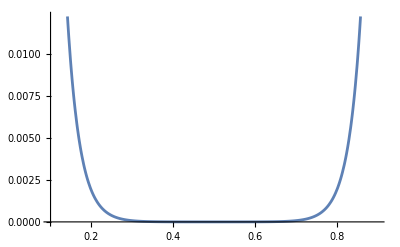

```mathematica
Plot[crossingEq[5]/.genFer/.Δσ->3/2//Abs,{z,0.100000,.900000}]
```

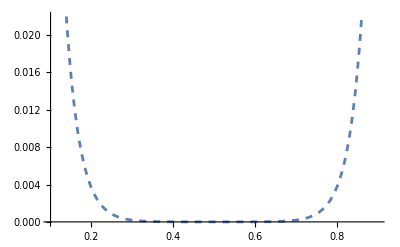

```mathematica
Plot[crossingEq[5]/.genBos/.Δσ->3/2//Abs,{z,0.100000,.900000},PlotStyle->Dashed]
```

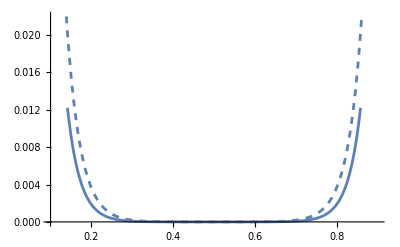

```mathematica
Show[%,%%]
```

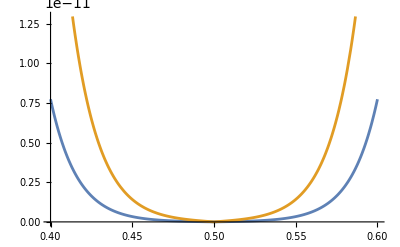

```mathematica
Plot[{crossingEq[10]/.genFer/.Δσ->3/2//Abs,crossingEq[10]/.genBos/.Δσ->3/2//Abs},{z,0.4000000,.6000000}]
```

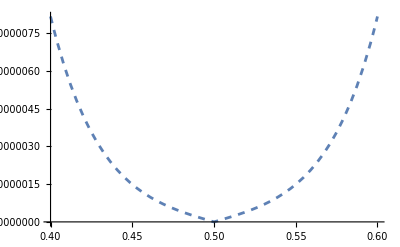

```mathematica
Plot[crossingEq[5]/.genBos/.Δσ->3/2//Abs,{z,0.4000000,.6000000},PlotStyle->Dashed]
```

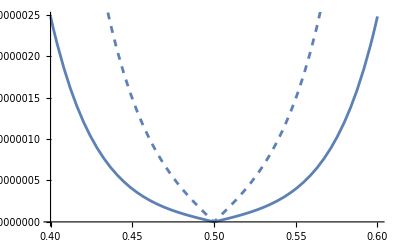

```mathematica
Show[%,%%]
```

```mathematica
crossingEq[5]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+C[2] (-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+C[3] (-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+C[4] (-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+C[5] (-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])

```mathematica
Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1.1]/.Δ[0]->1
```

2.09326-2.85599 ⅈ

```mathematica
%-%%//Simplify
```

{0.010616,0.000473329,0.0000185881,7.38651×10^-7,0.,5.22134×10^-7,0.000017678,0.000473329,0.0317686}

```mathematica
N[crossingEq[10]/.genBos/.Δσ->3/2/.zvals,40]//N
```

{0.000912331,2.42416×10^-6,8.83312×10^-9,2.87265×10^-11,0.,-2.87265×10^-11,-8.83312×10^-9,-2.42416×10^-6,-0.000912331}

```mathematica
N[crossingEq[20]/.genBos/.Δσ->3/2/.zvals,40]//N
```

{2.54955×10^-8,1.50795×10^-13,2.63454×10^-18,4.69436×10^-23,0.,-4.69436×10^-23,-2.63454×10^-18,-1.50795×10^-13,-2.54955×10^-8}

```mathematica
N[crossingEq[8]/.genBos/.Δσ->3/2/.zvals,40]//N
```

{0.00581533,0.0000517866,5.4658×10^-7,5.02436×10^-9,0.,-5.02436×10^-9,-5.4658×10^-7,-0.0000517866,-0.00581533}

```mathematica
Join[Table[Δ[i],{i,0,10}],Table[C[i],{i,0,10}]]
```

{Δ[0],Δ[1],Δ[2],Δ[3],Δ[4],Δ[5],Δ[6],Δ[7],Δ[8],Δ[9],Δ[10],C[0],C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8],C[9],C[10]}

```mathematica
NMinimize[Norm[Abs[crossingEq[10]/.Δσ->3/2]/.zvalsTable[11]],{Δ[0],Δ[1],Δ[2],Δ[3],Δ[4],Δ[5],Δ[6],Δ[7],Δ[8],Δ[9],Δ[10],C[0],C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8],C[9],C[10]},PrecisionGoal->10]
```

$Aborted

```mathematica
Abs[crossingEq[5]/.Δσ->3/2]/.zvals/.{Δ[0]->-0.013005862013326869,Δ[1]->0.16320795744989858,Δ[2]->-0.06115838600208261,Δ[3]->0.3368735109100814,Δ[4]->0.5264481560463778,Δ[5]->0.7692290735199061,C[0]->0.34573036158438364,C[1]->-0.43180233196616036,C[2]->-0.8881128040865098,C[3]->0.018892086085682883,C[4]->-0.34656111044785765,C[5]->0.3361165044727851}
```

{8.14557×10^-7,7.05571×10^-6,0.0000202175,0.0000225442,0,0.0000225442,0.0000202175,7.05571×10^-6,8.14557×10^-7}

```mathematica
zvals=N[zvals,30]
```

{{z→0.1},{z→0.2},{z→0.3},{z→0.4},{z→0.5},{z→0.6},{z→0.7},{z→0.8},{z→0.9}}

```mathematica
(Abs[crossingEq[5]]/.zvals)/.genBos/.Δσ->3/2
```

{0.0686071563126914635,0.0036489059521031454,0.000187940805616644,8.1635567855981×10^-6,0,8.1635567855981×10^-6,0.000187940805616644,0.003648905952103145,0.068607156312691463}

```mathematica
FindInstance[Table[(Abs[crossingEq[5]/.Δσ->3/2]/.zvals)[[i]]<%344[[i]],{i,Length[zvals]}],
```

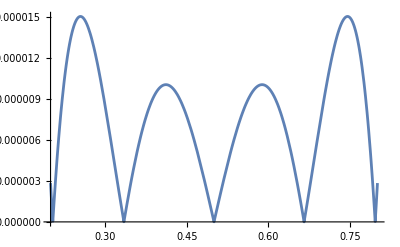

```mathematica
Plot[Abs[crossingEq[10]/.Δσ->3/2/.{Δ[0]->0.0034827643973079415,Δ[1]->-0.20309806738691305,Δ[2]->0.3107889802272767,Δ[3]->0.10119394865696789,Δ[4]->-0.4218938728027198,Δ[5]->0.1095983154454076,Δ[6]->0.09339763053089131,Δ[7]->0.08947003904940717,Δ[8]->-0.11581669410455386,Δ[9]->0.3156270357564098,Δ[10]->0.12168197798302714,C[0]->-0.40790112289054936,C[1]->0.24595834861712548,C[2]->0.1694322688525729,C[3]->-0.10736812385487303,C[4]->0.01406677419478178,C[5]->0.056175929304727854,C[6]->0.22665275971574322,C[7]->-0.4259524945637281,C[8]->-0.7372286948927096,C[9]->-0.32905098505269403,C[10]->0.28982574369514413}],{z,0.2000000000,.800000000}]
```

```mathematica
Table[c[i],{i,10}]
```

{c[1],c[2],c[3],c[4],c[5],c[6],c[7],c[8],c[9],c[10]}

```mathematica
{Abs[(crossingEq[10]/.C[j_]->c[j]/.zvals/.genBos/.Δσ->3/2)[[i]]],Abs[((crossingEq[10]/.zvals/.genBos/.Δσ->3/2)[[i]])]}/.i->5//Simplify
```

Part::pkspec1: The expression i cannot be used as a part specification.

{0,0}

```mathematica
Table[Abs[(crossingEq[10]/.C[j_]->c[j]/.zvals/.genBos/.Δσ->3/2)[[i]]]<Abs[((crossingEq[10]/.zvals/.genBos/.Δσ->3/2)[[i]])],{i,Length[zvals]}]
```

{Abs[0.728-0.009393817178197830223 c[0]-0.04461529842792842624 c[1]-0.1934840012568677903 c[2]-0.8374871469900246261 c[3]-3.622033921258736716 c[4]-15.65760064354814715 c[5]-67.66641169331019552 c[6]-292.3738271973813674 c[7]-1263.124985464524236 c[8]-5456.479105162389098 c[9]-23569.3451886986389 c[10]]<0.0009123305174490796,Abs[0.504-0.02483342904184558147 c[0]-0.0712446986951560141 c[1]-0.1672884552504752259 c[2]-0.3909983280308569235 c[3]-0.9134303394834599096 c[4]-2.133429157017659911 c[5]-4.98220141832368343 c[6]-11.6338898959721869 c[7]-27.1644722917559825 c[8]-63.42461454841736337 c[9]-148.0811087432198278 c[10]]<2.424155003119×10^-6,Abs[0.316-0.0293009408466221462 c[0]-0.059385199434707924 c[1]-0.08366146953086106741 c[2]-0.1146874922667834065 c[3]-0.1568015556025983398 c[4]-0.2143052796385456423 c[5]-0.292868860805226467 c[6]-0.400212716253795757 c[7]-0.546881678412982288 c[8]-0.747282727172332267 c[9]-1.02110023949518469 c[10]]<8.8331156322×10^-9,Abs[0.152-0.019273586102501321 c[0]-0.0314549952244479099 c[1]-0.02960512170457435071 c[2]-0.0250728189133105857 c[3]-0.0206122582587222176 c[4]-0.0167908904683124881 c[5]-0.013638368820764028 c[6]-0.0110673923625378268 c[7]-0.0089783075615859252 c[8]-0.00728278699344146301 c[9]-0.00590722356129557297 c[10]]<2.87264595×10^-11,False,Abs[-0.152+0.019273586102501321 c[0]+0.0314549952244479099 c[1]+0.0296051217045743507 c[2]+0.0250728189133105857 c[3]+0.0206122582587222176 c[4]+0.0167908904683124881 c[5]+0.013638368820764028 c[6]+0.0110673923625378268 c[7]+0.0089783075615859252 c[8]+0.00728278699344146301 c[9]+0.00590722356129557297 c[10]]<2.8726459×10^-11,Abs[-0.316+0.0293009408466221462 c[0]+0.059385199434707924 c[1]+0.0836614695308610674 c[2]+0.114687492266783406 c[3]+0.15680155560259834 c[4]+0.214305279638545642 c[5]+0.292868860805226467 c[6]+0.400212716253795757 c[7]+0.546881678412982288 c[8]+0.747282727172332267 c[9]+1.02110023949518469 c[10]]<8.8331156322×10^-9,Abs[-0.504+0.0248334290418455815 c[0]+0.0712446986951560141 c[1]+0.167288455250475226 c[2]+0.390998328030856923 c[3]+0.91343033948345991 c[4]+2.13342915701765991 c[5]+4.98220141832368343 c[6]+11.6338898959721869 c[7]+27.1644722917559825 c[8]+63.4246145484173634 c[9]+148.081108743219828 c[10]]<2.424155003119×10^-6,Abs[-0.728+0.00939381717819783022 c[0]+0.0446152984279284262 c[1]+0.19348400125686779 c[2]+0.837487146990024626 c[3]+3.62203392125873672 c[4]+15.6576006435481472 c[5]+67.6664116933101955 c[6]+292.373827197381367 c[7]+1263.12498546452424 c[8]+5456.4791051623891 c[9]+23569.3451886986389 c[10]]<0.00091233051744908}

```mathematica
FindInstance[Table[Abs[(crossingEq[10]/.C[j_]->c[j]/.zvals/.genBos/.Δσ->3/2)[[i]]]<=Abs[((crossingEq[10]/.zvals/.genBos/.Δσ->3/2)[[i]])],{i,Length[zvals]}],{c[0],c[1],c[2],c[3],c[4],c[5],c[6],c[7],c[8],c[9],c[10]}]
```

$Aborted

```mathematica
crossingEq[1]
```

```mathematica
cs=Table[c[i],{i,0,10}]
```

{c[0],c[1],c[2],c[3],c[4],c[5],c[6],c[7],c[8],c[9],c[10]}

```mathematica
{c[0],c[1],c[2],c[3],c[4],c[5],c[6]}/.c[j_]->C[j]/.genBos/.Δσ->3/2
```

{2,18/7,10/11,28/143,135/4199,33/7429,182/334305}

```mathematica
Table[C[i],{i,0,10}]
```

{C[0],C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8],C[9],C[10]}

```mathematica
crossingTable[1]
```

{-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z]}

```mathematica
N[-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.Δ[0]->23/.z->1/10/.Δσ->3/2,30]
```

-23569.3451886986388986421304752

```mathematica
Manipulate[Plot[-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.Δσ->3/2,{z,0,1},WorkingPrecision->30],{Δ[0],0,30}]
```

```mathematica
Δ[10]/.genBos/.Δσ->3/2
```

23

```mathematica
N[-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.Δσ->3/2/.z->1/10/.genBos/.Δσ->3/2,30]
```

-0.00939381717819783022329847556146

```mathematica
729 10^(-3-Δ[10]) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1/10]-9^Δ[10] 10^(-3-Δ[10]) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],9/10]
```

```mathematica
crossingTable[10]/.z->1/10/.Δ[10]->20+2 Δσ/.Δσ->3/2
```

{729 10^(-3-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/10]-9^Δ[0] 10^(-3-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],9/10],729 10^(-3-Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/10]-9^Δ[1] 10^(-3-Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],9/10],729 10^(-3-Δ[2]) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1/10]-9^Δ[2] 10^(-3-Δ[2]) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],9/10],729 10^(-3-Δ[3]) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1/10]-9^Δ[3] 10^(-3-Δ[3]) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],9/10],729 10^(-3-Δ[4]) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1/10]-9^Δ[4] 10^(-3-Δ[4]) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],9/10],729 10^(-3-Δ[5]) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1/10]-9^Δ[5] 10^(-3-Δ[5]) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],9/10],729 10^(-3-Δ[6]) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1/10]-9^Δ[6] 10^(-3-Δ[6]) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],9/10],729 10^(-3-Δ[7]) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1/10]-9^Δ[7] 10^(-3-Δ[7]) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],9/10],729 10^(-3-Δ[8]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1/10]-9^Δ[8] 10^(-3-Δ[8]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],9/10],729 10^(-3-Δ[9]) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1/10]-9^Δ[9] 10^(-3-Δ[9]) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],9/10],(729 Hypergeometric2F1[23,23,46,1/10])/100000000000000000000000000-(8862938119652501095929 Hypergeometric2F1[23,23,46,9/10])/100000000000000000000000000}

```mathematica
N[crossingTable[10]/.z->1/10/.genBos/.Δσ->3/2,30]
```

{-0.00939381717819783022329847556146,-0.0446152984279284262370423556652,-0.193484001256867790289546339725,-0.837487146990024626125849877673,-3.62203392125873671621584620602,-15.6576006435481471519634482447,-67.6664116933101955179540829393,-292.37382719738136742436932512,-1263.12498546452423586071927977,-5456.47910516238909800716246021,-23569.3451886986388986421304752}

```mathematica
N[D[crossingEq[10],{{C[0],C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8],C[9],C[10]},1}]/.z->1/10/.genBos/.Δσ->3/2,30]
```

{-0.00939381717819783022329847556146,-0.0446152984279284262370423556652,-0.193484001256867790289546339725,-0.837487146990024626125849877673,-3.62203392125873671621584620602,-15.6576006435481471519634482447,-67.6664116933101955179540829393,-292.37382719738136742436932512,-1263.12498546452423586071927977,-5456.47910516238909800716246021,-23569.3451886986388986421304752}

```mathematica
crossingEq[10]/.C[j_]->c[j]/.z->1/2/.genBos/.Δσ->3/2
```

0

```mathematica
zvals
```

```mathematica
{c[0],c[1],c[2],c[3],c[4],c[5]}/.c[j_]->C[j]/.genBos/.Δσ->3/2
```

{2,18/7,10/11,28/143,135/4199,33/7429}

```mathematica
%575-.01*%574
```

{1.93059,2.64809,0.858896,0.215336,0.0281645,0.00476417}

```mathematica
Table[c[j]->%577[[j+1]],{j,0,5}]
```

{c[0]→1.93059,c[1]→2.64809,c[2]→0.858896,c[3]→0.215336,c[4]→0.0281645,c[5]→0.00476417}

```mathematica
N[crossingEq[5]/.zvals[[1;;6]]/.genBos/.Δσ->3/2,40]
```

{0.06860715631269146348503332647648589349156,0.006549239846997394266201058256263167477191,0.0006234249939042569746697444869120551291184,0.00005514581019564941932942389846826087783207,4.209453581649245637436011023938249455048×10^-6,-1.932279028494863875380148191669655848741×10^-7}

```mathematica
Table[C[j],{j,0,5}]/.genBos/.Δσ->3/2
```

{2,18/7,10/11,28/143,135/4199,33/7429}

```mathematica
%599
```

```mathematica
N [%595,50]
```

{1.27079×10^9,-1.46664×10^9,1.06911×10^9,-4.97592×10^8,1.31667×10^8,-1.47725×10^7}

```mathematica
Table[c[i]->%624[[i+1]],{i,0,5}]
```

{c[0]→1.8813600792846892064437439102,c[1]→2.70965183159781258338141931177,c[2]→0.80565291010725903293172837423,c[3]→0.24664024011382012500728176807,c[4]→0.01717842093726052100412601491,c[5]→0.0065801064214320280641501011517}

```mathematica
N[crossingEq[5]/.z->1/10/.genBos/.Δσ->3/2,40]
```

0.06860715631269146348503332647648589349156

```mathematica
N[crossingEq[5]/.zvals[[1;;6]]/.genBos/.Δσ->3/2,40]
```

{0.06860715631269146348503332647648589349156,0.006549239846997394266201058256263167477191,0.0006234249939042569746697444869120551291184,0.00005514581019564941932942389846826087783207,4.209453581649245637436011023938249455048×10^-6,-1.932279028494863875380148191669655848741×10^-7}

```mathematica
crossingEq[5]/.C[j_]->c[j]/.zvals[[1;;6]]/.genBos/.Δσ->3/2/.%626
```

{0.06174644068142231713652999383,0.00589431586229765483958095243,0.00056108249451383127720277004,0.000049631229176084477396481509,3.78850822348432107369241×10^-6,-1.73905112564537748784213×10^-7}

```mathematica
%611.%614
```

{1.186399207153107935562560898,-1.382232601692411548099907403,1.034379989836500579773625349,-0.5083604430962432081147757226,0.1497209108941249638096567359,-0.021380550013216498167412978134}

```mathematica
N[%599,40]-N[1/10,40]%611.%614
```

{1.8813600792846892064437439102,2.70965183159781258338141931177,0.80565291010725903293172837423,0.24664024011382012500728176807,0.01717842093726052100412601491,0.0065801064214320280641501011517}

```mathematica
Abs[violBos]
```

{0.000912330517449079565885923481933,0.000078610222699911988870486856093,7.59539407701780704947083145999×10^-6,7.82389834107699682729831534581×10^-7,8.30032104059956478591952684345×10^-8,8.83311563217572402196249909925×10^-9,9.22274776369543353193641428723×10^-10,9.25846951475883937252166037712×10^-11,8.75951035151838605454849713993×10^-12,7.60785029949374190359945621729×10^-13,8.36793705496871660575221375804×10^-14}

```mathematica
(Abs[violBos]-Abs[%])/Abs[violBos]
```

{0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08}

```mathematica
N[crossingEq[11]/.C[j_]->c[j]/.genBos/.Δσ->3/2/.Table[c[i]->xnew[[i+1]],{i,0,10}]/.zvals/.c[11]->46/8268616329,30]
```

{0.000272995743105806999549363,0.0000167197193064502601096,1.148211420928177737779×10^-6,8.224646880106473759546×10^-8,5.76750835032190196915×10^-9,3.6452111204545824051×10^-10,1.711322381454412018×10^-11,5.28318255789823×10^-15,-1.3258901909618556×10^-13,-2.0987855601716763×10^-14,2.837097939050314×10^-15}

```mathematica
Abs[%715]-Abs[%700]
```

{-0.0000729864413959263652708739,-6.2888178159929591096389×10^-6,-6.076315261614245639577×10^-7,-6.259118672861597461839×10^-8,-6.64025683247965182874×10^-9,-7.0664925057405792176×10^-10,-7.378198210956346826×10^-11,-7.406775611807071498×10^-12,-4.35582789929099767×10^-13,-1.888709119251641×10^-14,-1.020153765874345×10^-15}

```mathematica
C[11]/.genBos/.Δσ->3/2
```

46/8268616329

```mathematica
N[crossingEq[11]/.genBos/.Δσ->3/2/.zvals,30]
```

{0.000345982184501733364820236888505,0.0000230085371224432192192390998464,1.75584294708960230173669608823×10^-6,1.44837655529680712213850863394×10^-7,1.24077651828015537978886257858×10^-8,1.07117036261951616226645151891×10^-9,9.08952059241075884377101219187×10^-11,7.41205879436496972395159905317×10^-12,5.68171809025285325874548435336×10^-13,3.9874946794233172644618657346×10^-14,-3.85725170492465927465005872106×10^-15}

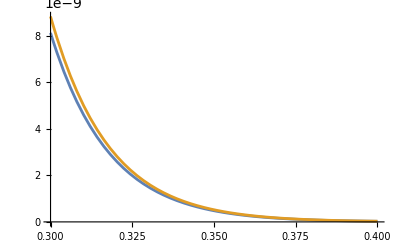

```mathematica
Plot[{crossingEq[10]/.C[j_]->c[j]/.genBos/.Δσ->3/2/.Table[c[i]->xnew[[i+1]],{i,0,10}],crossingEq[10]/.genBos/.Δσ->3/2},{z,0.3,.4}]
```

```mathematica
(crossingEq[10]/.C[j_]->c[j]/.zvals/.genBos/.Δσ->3/2)/.Table[c[i]->xnew[[i+1]],{i,0,10}]
```

{0.0008393440760531532006150496,0.0000723214048839190297608479,6.9877625508563824855132×10^-6,7.1979864737908370811145×10^-7,7.636295357351599603046×10^-8,8.12646638160166610021×10^-9,8.4849279425997988494×10^-10,8.5177919535781322227×10^-11,8.05874952339691517×10^-12,6.99922227553424255×10^-13,-7.69850209057121928×10^-14}

```mathematica
(crossingEq[10]/.C[j_]->c[j]/.zvals/.genFer/.Δσ->3/2)/.Table[c[i]->xnewFer[[i+1]],{i,0,10}]
```

{0.00055797733336308899787154281,0.00004224147948043180237563484,3.62742135605415563774437×10^-6,3.3438668474811026895293×10^-7,3.18788530700448090673×10^-8,3.05564911741902409024×10^-9,2.87623681442591290895×10^-10,2.6286520474011300185×10^-11,2.238612038727678937×10^-12,1.74796061059572311×10^-13,-1.80416117438029421×10^-14}

```mathematica
Abs[violFer]-Abs[%733]//Chop
```

{5.63613468043524240274286×10^-6,4.2668161091345254924884×10^-7,3.664061975812278421964×10^-8,3.37764328028394211064×10^-9,3.2200861686913948553×10^-10,0,0,0,0,0,0}

```mathematica
xval
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
xnewFer=xvalFer-N[1/100,30]*invJf.violFer
```

{3.0000488484682114476627182148,1.6665456586793159857511251078,0.44073087611737517359274920298,0.081277790678657932089156130581,0.012287083724564908521936265743,0.0015076863362244202678078968835,0.000210616037660282251515778222,0.000012560469545842147239392198,3.398687223430698373127581203×10^-6,4.57293026761898646715000768×10^-8,2.618375018061932430119042775×10^-8}

```mathematica
xnew=xval-N[8/100,30]*invJ.violBos
```

{2.0005600082906799065555177842,2.5707147894061898592279448899,0.9097719317699439695358862079,0.1952721252562926596802523191,0.03249063987331984329142593422,0.00426763213468992641732325316,0.000614126091768653847623674975,0.000040203611253267316100859538,0.0000108366929841751863175137456,3.337444659412438440735762×10^-8,1.02967141613326209919884288×10^-7}

```mathematica
(xnew-xval)/xval
```

{0.0002800041453399532777588921,-0.0002775818975928325224658762,0.00074912494693836648947482869,-0.0027173602982196309187113701,0.010579235763481644301462947,-0.039265480951167777142592494,0.12805177532263639851556408,-0.34189536134198509977783414,0.69151109452959364867812179,-0.94758997933141355892146752,0.6990797412463938079141078}

```mathematica
xnew=xval;
```

```mathematica
xval=N[Table[C[i],{i,0,10}]/.genBos/.Δσ->3/2,30]
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
xvalFer=N[Table[C[i],{i,0,10}]/.genFer/.Δσ->3/2,30]
```

{3.,1.66666666666666666666666666667,0.440559440559440559440559440559,0.0814479638009049773755656108597,0.0121627598407784166298098186643,0.00157490913985731592408130300175,0.000184118467082248349509455798417,0.0000199313832819660550956193457523,2.03195541010504496503432519296×10^-6,1.97414668778514786274085224138×10^-7,1.84370288670964344508466451484×10^-8}

```mathematica
violFer=N[crossingEq[10]/.zvals/.genFer/.Δσ->3/2,30]//Chop
```

{0.000563613468043524240274285668556,0.0000426681610913452549248836765631,3.6640619758122784219640147433×10^-6,3.37764328028394211063561459088×10^-7,3.22008616869139485528235685895×10^-8,3.08651426001921625276682519904×10^-9,2.90528971154132617066150684193×10^-10,0,0,0,0}

```mathematica
violBos=N[crossingEq[10]/.zvals/.genBos/.Δσ->3/2,30]
```

{0.000912330517449079565885923481933,0.000078610222699911988870486856093,7.59539407701780704947083145999×10^-6,7.82389834107699682729831534581×10^-7,8.30032104059956478591952684345×10^-8,8.83311563217572402196249909925×10^-9,9.22274776369543353193641428723×10^-10,9.25846951475883937252166037712×10^-11,8.75951035151838605454849713993×10^-12,7.60785029949374190359945621729×10^-13,-8.36793705496871660575221375804×10^-14}

```mathematica
Do[Print[1],2]
```

1

1

```mathematica
Max[(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.zvals/.Δσ->3/2]/.Δ[0]->1/10//N
```

0.581013

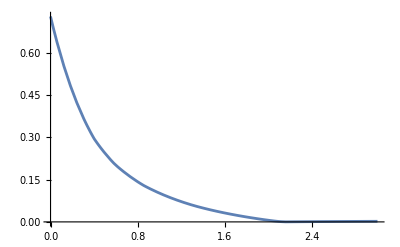

```mathematica
Plot[Max[(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.zvals/.Δσ->3/2],{Δ[0],0,3}]
```

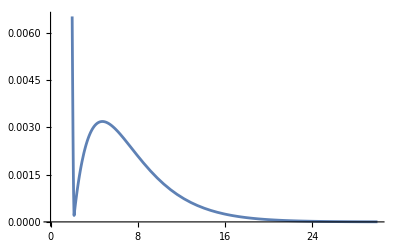

```mathematica
Plot[Max[(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.zvals/.Δσ->3/2],{Δ[0],0,30}]
```

```mathematica
Table[{cs[[i]],C[i-1]/.genBos/.Δσ->3/2,0,10},{i,1,11}]
```

{{c[0],2,0,10},{c[1],18/7,0,10},{c[2],10/11,0,10},{c[3],28/143,0,10},{c[4],135/4199,0,10},{c[5],33/7429,0,10},{c[6],182/334305,0,10},{c[7],24/392863,0,10},{c[8],51/7960645,0,10},{c[9],19/29836911,0,10},{c[10],231/3811773485,0,10}}

```mathematica
Table[{cs[[i]],RandomInteger[10]/10,0,5},{i,1,11}]
```

{{c[0],1,0,5},{c[1],1/2,0,5},{c[2],1/2,0,5},{c[3],1/2,0,5},{c[4],4/5,0,5},{c[5],1/10,0,5},{c[6],1/2,0,5},{c[7],1/2,0,5},{c[8],4/5,0,5},{c[9],1/2,0,5},{c[10],3/10,0,5}}

```mathematica
N[D[%758,{cs,1}],30]
```

```mathematica
xvalFer
```

{3.,1.66666666666666666666666666667,0.440559440559440559440559440559,0.0814479638009049773755656108597,0.0121627598407784166298098186643,0.00157490913985731592408130300175,0.000184118467082248349509455798417,0.0000199313832819660550956193457523,2.03195541010504496503432519296×10^-6,1.97414668778514786274085224138×10^-7,1.84370288670964344508466451484×10^-8}

```mathematica
xval
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
zvals5={{z->1/10},{z->13/100},{z->4/25},{z->19/100},{z->11/50},{z->1/4}};
```

```mathematica
Table[C[i]*Δ[i]^6,{i,0,11}]/.genBos/.Δσ->3/2//N
```

{1458.,40178.6,106954.,104058.,56956.6,21440.9,6201.2,1474.56,301.4,54.6154,8.97123,1.3582}

```mathematica
ceqnC5
```

```mathematica
Table[{cs[[i]],RandomInteger[10]/10,0,10/(i+1)},{i,1,11}]
```

{{c[0],3/10,0,5},{c[1],3/10,0,10/3},{c[2],3/5,0,5/2},{c[3],1/10,0,2},{c[4],2/5,0,5/3},{c[5],0,0,10/7},{c[6],3/5,0,5/4},{c[7],0,0,10/9},{c[8],1/10,0,1},{c[9],1/10,0,10/11},{c[10],0,0,5/6}}

```mathematica
crossingEq[10]/.C[i_]->0/.Δσ->3/2/.z->1/10//N
```

0.728

```mathematica
crossingTable[10][[1]]/.Δσ->3/2/.Δ[0]->0
```

(1-z)^3-z^3

```mathematica
crossingTable[10][[1]]/.Δσ->3/2
```

-(1-z)^Δ[0] z^3 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^3 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
Manipulate[Plot[-(1-z)^Δ[0] z^3 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^3 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],{z,0,1/2}],{Δ[0],0,10}]
```

```mathematica
crossingTable[10]
```

```mathematica
Δ[0]/.genBos/.Δσ->3/2
```

3

```mathematica
N[ /.z->4/10,30]
```

{-0.0192735861025013209658339721035,-0.0314549952244479098579139796629,-0.0296051217045743507087073862652,-0.0250728189133105857201256979882,-0.0206122582587222176393995827456,-0.0167908904683124880716031924932,-0.0136383688207640280113505162968,-0.0110673923625378268206764179308,-0.0089783075615859251963827054645,-0.00728278699344146301487651974325,-0.00590722356129557297148363272523}

```mathematica
Table[{cs[[i]],C[i-1]+RandomInteger[10]/10/.genBos,0,5},{i,1,11}]/.Δσ->3/2
```

{{c[0],21/10,0,5},{c[1],97/35,0,5},{c[2],21/11,0,5},{c[3],199/286,0,5},{c[4],5549/41990,0,5},{c[5],29881/37145,0,5},{c[6],200947/668610,0,5},{c[7],393103/3928630,0,5},{c[8],51/7960645,0,5},{c[9],29836930/29836911,0,5},{c[10],3049419019/3811773485,0,5}}

```mathematica
N[%]
```

{{c[0.],2.1,0.,5.},{c[1.],2.77143,0.,5.},{c[2.],1.90909,0.,5.},{c[3.],0.695804,0.,5.},{c[4.],0.132151,0.,5.},{c[5.],0.804442,0.,5.},{c[6.],0.300544,0.,5.},{c[7.],0.100061,0.,5.},{c[8.],6.40652×10^-6,0.,5.},{c[9.],1.,0.,5.},{c[10.],0.8,0.,5.}}

```mathematica
N[crossingEq[7]/.genBos/.Δσ->3/2/.zvals,30]
```

{0.0139075630826413216856376351562,0.0073490376169359424398078661057,0.0039197494188221102095467913262,0.00210677476963409496527128886148,0.00113937639510302677114289397845,0.000619199794415749338758199969478,0.000337747692669827964614040193998,0.000184707368581386541638292233795,0.00010117624406643149996479015331,0.0000554600350781296839061724369406,0.0000303962368741457782605912639515}

```mathematica
N[crossingEq[100]/.z->1/1000/.genBos/.Δσ->1,30]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 499/500+(19 ((998001 Hypergeometric2F1[20,20,40,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000-(980188864829534682605802224588165892518744500843860189980001 Hypergeometric2F1[20,20,40,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000))/883631595+«8»+«92».

0.000605752825574

```mathematica
crossingEq[0]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])

```mathematica
crossingEq[10]/.z->0
```

1-0^(2 Δσ)+C[0] (0^Δ[0]-0^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1])+C[1] (0^Δ[1]-0^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1])+C[2] (0^Δ[2]-0^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1])+C[3] (0^Δ[3]-0^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1])+C[4] (0^Δ[4]-0^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1])+C[5] (0^Δ[5]-0^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1])+C[6] (0^Δ[6]-0^(2 Δσ) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1])+C[7] (0^Δ[7]-0^(2 Δσ) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1])+C[8] (0^Δ[8]-0^(2 Δσ) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1])+C[9] (0^Δ[9]-0^(2 Δσ) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1])+C[10] (0^Δ[10]-0^(2 Δσ) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1])

```mathematica
((-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]))/.z->1/4
```

3^(2 Δσ) 4^(-2 Δσ-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/4]-3^Δ[0] 4^(-2 Δσ-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],3/4]

```mathematica
Manipulate[Plot[((-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]))/.Δσ->1,{Δ[0],2,20}],{z,1/10,1/2}]
```

```mathematica
Manipulate[Plot[((-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]))/(Exp[Δ[0]/2])/.Δσ->1,{Δ[0],2,20}],{z,1/10,1/2}]
```

```mathematica
xval
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
Series[Hypergeometric2F1[Δ[j],Δ[j],2 Δ[j],1/4],{Δ[j],Infinity,1}]
```

Hypergeometric2F1[Δ[j],Δ[j],2 Δ[j],1/4]

```mathematica
N[Table[C[j](Exp[Δ[j]/2]),{j,0,10}]/.genBos/. Δσ->1,30]
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
getAvCs[4,Table[2i+2,{i,0,4}],45/100,49/100,1,60]
```

{{1.84586155476130207914185344899819562679014436548399569,0.0028939462051183872543263117152475197542448884373583},{1.32275538502397139357699774946941773638287054088550643,0.00219171851360117711559115729629620338812867169920776},{0.166207301871656368802701368248707634187452443776275666,0.00108543282029296506124218044256747651700600859124053},{0.0588318368065311576951171752045749548294127693898010095,0.000256384913382640424653964095606987450410661264070026}}

```mathematica
getAvCs[4,Table[2i+2,{i,0,4}],46/100,49/100,1,60]
```

{{1.8471532431445471366705572020350137367674558701064013,0.0017842271366132778846286979572907630586950725493683},{1.3217773553649304482740499372050320685791961392522726,0.0013522055187964850787983842167061580897299622502565},{0.16669134396974899216559168878470991585696243912549567,0.000670983840780724591792051570290740964363678226328481},{0.058717639888007408277131961705603570072309375054450082,0.00015904570741039203690068476649929465521392860666235}}

```mathematica
getAvCs[4,Table[2i+2,{i,0,4}],40/100,45/100,1,60]
```

{{1.826073052270630037681603641316149999073795885144743429,0.01021064020386284513608432266988027101820302282602694},{1.337670285793546299649114693362810366496730254580418284,0.007667000949259535415393870860149907959451995165558637},{0.1589198955727388597382762699597204713518516157463100823,0.0037067022408904635987389581582805973578209473621280782},{0.06051307370506171407726513400285489867908243696368340815,0.00083948538751105066472069938690612422943096250472697312}}

```mathematica
getAvCs[4,Table[i+2,{i,0,4}],40/100,45/100,1,60]
```

{{-87.1865653915333623481156450697232387554979643838688737,2.565371373562553783428969450556397193396551741179914},{79.9276056623628321967019328723242227011693116797636243,2.242588142325551111651777636524519513441696522970349},{-32.8320700247401868959193596333461799957565155420170231,0.8857654272809670315705939315081814719023493707482017},{6.94082008300882424453458272258238147427820888731245574,0.148373484819597699486450176205191175917239965571707}}

```mathematica
N[crossingEq[3]/.genBos/.Δσ->1/.z->4/10,40]
```

0.0002304362493593383417915145601912011091

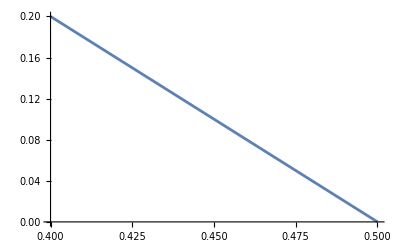

```mathematica
Plot[crossingEq[3]/.C[i_]->0/.Δσ->1//Simplify,{z,4/10,1/2}]
```

```mathematica
N[crossingEq[3]/.z->45/100/.C[i_]->0/.genBos/.Δσ->1,30]
```

0.1

```mathematica
N[crossingEq[3]/.z->45/100/.C[i_]->0/.genBos/.Δσ->1,30]
```

```mathematica
{N[crossingEq[3]/.z->4/10/.C[i_]->c[i]/.genBos/.Δσ->1,30],N[crossingEq[3]/.z->43/100/.C[i_]->c[i]/.genBos/.Δσ->1,30],N[crossingEq[3]/.z->45/100/.C[i_]->c[i]/.genBos/.Δσ->1,30],N[crossingEq[3]/.z->47/100/.C[i_]->c[i]/.genBos/.Δσ->1,30]}
```

{0.2-0.0389578500599478431154591622967 c[0]-0.0835480818703817529966153802172 c[1.]-0.0811997256233707836363595147008 c[2.]-0.0693416411664221000974705700001 c[3.],0.14-0.0280396120134986634679040163295 c[0]-0.0583312393607232657420591314669 c[1.]-0.0524969874098053594946271247374 c[2.]-0.0401043637993783224337085635224 c[3.],0.1-0.0202876844791294331893025016474 c[0]-0.0416028164360849587395454686956 c[1.]-0.0360534704458383493369453714563 c[2.]-0.0259900712927394883592145304135 c[3.],0.06-0.0122765475652533289797938009604 c[0]-0.0249344067795532004212198569358 c[1.]-0.021057765239040560105872677288 c[2.]-0.0145689423538572172031210511964 c[3.]}

```mathematica
{N[crossingEq[3]/.z->4/10/.C[i_]->c[i]/.Δ[i_]->i+2/.Δσ->1,30],N[crossingEq[3]/.z->43/100/.C[i_]->c[i]/.Δ[i_]->i+2/.Δσ->1,30],N[crossingEq[3]/.z->45/100/.C[i_]->c[i]/.Δ[i_]->i+2/.Δσ->1,30],N[crossingEq[3]/.z->47/100/.C[i_]->c[i]/.Δ[i_]->i+2/.Δσ->1,30]}
```

{0.2-0.0389578500599478431154591622967 c[0]-0.0719556211604710011943237511934 c[1.]-0.0835480818703817529966153802172 c[2.]-0.0847763058539576135757039798497 c[3.],0.14-0.0280396120134986634679040163295 c[0]-0.0513269413324250401739250120636 c[1.]-0.0583312393607232657420591314669 c[2.]-0.0572516315139686717455525874644 c[3.],0.1-0.0202876844791294331893025016474 c[0]-0.0369814205718289446159253734143 c[1.]-0.0416028164360849587395454686956 c[2.]-0.0401802240326061600362960298273 c[3.],0.06-0.0122765475652533289797938009604 c[0]-0.0223160042659559967776391524493 c[1.]-0.0249344067795532004212198569358 c[2.]-0.0238204429064969523469866888895 c[3.]}

```mathematica
Solve[%==0]
```

{{c[0]→-85.798742183460751005958706,c[1.]→78.715415038243070825626869,c[2.]→-32.354344382472455101888893,c[3.]→6.8611312654466945876008862}}

```mathematica
getAvCs[4,Table[i+2,{i,0,4}],40/100,45/100,1,60]
```

{{-87.1865653915333623481156450697232387554979643838688737,2.565371373562553783428969450556397193396551741179914},{79.9276056623628321967019328723242227011693116797636243,2.242588142325551111651777636524519513441696522970349},{-32.8320700247401868959193596333461799957565155420170231,0.8857654272809670315705939315081814719023493707482017},{6.94082008300882424453458272258238147427820888731245574,0.148373484819597699486450176205191175917239965571707}}

```mathematica
getAvCs[8,Table[2i+2,{i,0,8}],40/100,45/100,1,60]
```

{{1.99919670038940298578399562611991799811527539,0.00008551941267320339174615343916135255181497},{1.20069392142855946165649240110344990843220894,0.00007324148105043573598528131747230436120589},{0.237565275148837163356681153668463766829191813,0.000054412529332685375992074354690574517808354},{0.0329839921736888469818428387036089238399731235,0.000033948680935494731365058917424359271444481},{0.00351220311777099741909472684057089928969738259,0.0000167133617463734772843491772903650388626841},{0.000454044767987021251709116622282632606198500274,5.99826394267951202583858342863044933650147×10^-6},{0.000011222939639774747889012868630464988540900444,1.381967062613386962223082328325940612209047×10^-6},{7.3498514822469141176256344587766006387464791×10^-6,1.524341351986717015381856844753538628649748×10^-7}}

```mathematica
crossingEq[3]/.z->49/100/.Δ[i_]->i+2/.Δσ->1/.C[i_]->%771[[i+1,1]]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

4.60233464915627408491882901905168132367443218×10^-9

```mathematica
N[crossingEq[3]/.C[i_]->%771[[i+1,1]]/.Δ[i_]->i+2/.Δσ->1/.z->4/10,40]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

1.66273499676697636979449985789175794308×10^-8

```mathematica
N[crossingEq[3]/.genBos/.Δσ->1/.z->4/10,40]
```

0.0002304362493593383417915145601912011091

```mathematica
Table[C[i],{i,0,4}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218}

```mathematica
crescRule=C[j_]->c[j]/Exp[Δ[j]/2];
```

```mathematica
crossingEq[10]/.C[j_]->c[j]/Exp[Δ[j]/2]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+ⅇ^(-Δ[0]/2) c[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+ⅇ^(-Δ[1]/2) c[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+ⅇ^(-Δ[2]/2) c[2] (-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+ⅇ^(-Δ[3]/2) c[3] (-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+ⅇ^(-Δ[4]/2) c[4] (-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+ⅇ^(-Δ[5]/2) c[5] (-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+ⅇ^(-Δ[6]/2) c[6] (-(1-z)^Δ[6] z^(2 Δσ) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(1-z)^(2 Δσ) z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])+ⅇ^(-Δ[7]/2) c[7] (-(1-z)^Δ[7] z^(2 Δσ) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1-z]+(1-z)^(2 Δσ) z^Δ[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],z])+ⅇ^(-Δ[8]/2) c[8] (-(1-z)^Δ[8] z^(2 Δσ) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1-z]+(1-z)^(2 Δσ) z^Δ[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],z])+ⅇ^(-Δ[9]/2) c[9] (-(1-z)^Δ[9] z^(2 Δσ) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1-z]+(1-z)^(2 Δσ) z^Δ[9] Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],z])+ⅇ^(-Δ[10]/2) c[10] (-(1-z)^Δ[10] z^(2 Δσ) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1-z]+(1-z)^(2 Δσ) z^Δ[10] Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],z])

```mathematica
crossingEq[10]/.z->0.001/.Δσ->1/.genBos/.Δσ->1
```

0.902497

```mathematica
zvalsTable[min_,max_,n_]:=Table[{z->i},{i,min,max,(-min+max)/n}]
```

```mathematica
zvals=Table[i,{i,1/10,49/100,(-1/10+49/100)/20}]
```

{1/10,239/2000,139/1000,317/2000,89/500,79/400,217/1000,473/2000,32/125,551/2000,59/200,629/2000,167/500,707/2000,373/1000,157/400,103/250,863/2000,451/1000,941/2000,49/100}

```mathematica
crEqResc=crossingEq[10]/.crescRule/.Δσ->1/.zvals;
```

```mathematica
crEqResc20=crossingEq[20]/.crescRule/.Δσ->1/.zvals;
```

```mathematica
Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.z->0
```

1

```mathematica
Table[C[i],{i,0,10}]/.genBos/.Δσ->3/2//N
```

{2.,2.57143,0.909091,0.195804,0.0321505,0.00444205,0.000544413,0.00006109,6.40652×10^-6,6.36795×10^-7,6.06017×10^-8}

```mathematica
Table[{cs[[i]],RandomInteger[1000]/1000,0,5},{i,1,11}]
```

{{c[0],573/1000,0,5},{c[1],43/100,0,5},{c[2],99/250,0,5},{c[3],417/500,0,5},{c[4],411/500,0,5},{c[5],191/1000,0,5},{c[6],31/40,0,5},{c[7],223/1000,0,5},{c[8],74/125,0,5},{c[9],357/500,0,5},{c[10],203/250,0,5}}

```mathematica
crEqResc/.genBos/.Δσ->1
```

```mathematica
xvalsResc
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
(crEqResc/.genBos/.Δσ->1/.FindRoot[crEqResc/.genBos/.Δσ->1,Table[{cs[[i]],xvalsResc[[i]]+RandomInteger[10]/1000,0,10},{i,1,11}]/.Δσ->1,WorkingPrecision->30,MaxIterations->10000])/%1651
```

FindRoot::reged: The point {5.44067382177766646631735239888,8.85832827330217520440412568703,4.80692532645987215721527950741,1.75584741617587688748663172983,0.589032210742070578862550798761,0.120629615143520786931447321734,0.0701816896939724895858864659456,0,0.0125568515648087839711309846101,0.000832365382578543790167806791361,«1»} is at the edge of the search region {0,10.} in coordinate 8 and the computed search direction points outside the region.

{-292.38803741935820497786953,-391.4342122209487278282736,-535.9050526345599219578536,-757.622684859273367445336,-1114.53540334482707296291,-1714.19525955288526688971,-2759.3121284457984136101,-4636.6930055361373430781,-8091.7941922588016933364,-14572.85569912726675531,-26912.12445890650734952}

```mathematica
Table[cs[[i]]>0,{i,11}]
```

{c[0]>0,c[1]>0,c[2]>0,c[3]>0,c[4]>0,c[5]>0,c[6]>0,c[7]>0,c[8]>0,c[9]>0,c[10]>0}

```mathematica
Norm[crossingEq[10]/.crescRule/.genBos/.Δσ->1/.zvalsTable[11]]
```

```mathematica
crossingEq[10]/.crescRule/.genBos/.Δσ->1/.z->1/100
```

```mathematica
crossingEq[10]/.crescRule/.genBos/.Δσ->1/.z->1/10
```

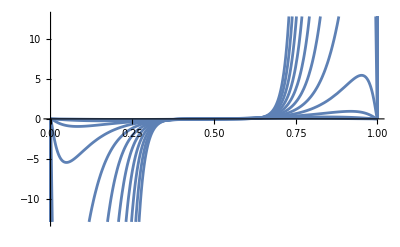

```mathematica
Plot[crossingTable[10]/.genBos/.Δσ->1,{z,0,1},WorkingPrecision->30]
```

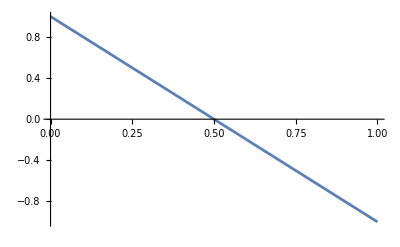

```mathematica
Plot[(1-z)^(2 Δσ)-z^(2 Δσ)/.Δσ->1,{z,0,1},WorkingPrecision->30]
```

```mathematica
crossingEq[1]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])

```mathematica
Manipulate[Plot[(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1,{z,0,1/2}],{Δ[0],2,10}]
```

```mathematica
N[crossingEq[20]/.genBos/.Δσ->1/.zvalsTable[21],30]
```

{0.0171629765952313418050381883384,0.0000441196597351640937871983528313,5.24928914136515789823506172023×10^-7,1.19440330691979918052314547935×10^-8,3.95233564713457987209937909657×10^-10,1.67076776684780277617999092928×10^-11,8.37759139960455759407983979287×10^-13,4.75093128692547179086486016712×10^-14,2.94788233904224874189109311929×10^-15,1.95290021415950185542695789084×10^-16,1.35527016651585741636947399512×10^-17,9.70163298441281072694368338855×10^-19,7.07107742899251446001087704861×10^-20,5.18813120857572447272660400558×10^-21,3.79281818385799757723000162984×10^-22,2.73642953094235747134679175103×10^-23,1.93059765734004231782258190066×10^-24,1.31994151042998091376367065639×10^-25,8.66560883427341472266841627953×10^-27,5.40999807223044066249977329471×10^-28,2.89793485605498310973689292029×10^-29}

```mathematica
Table[NMinimize[{Abs[crossingEq[10]/.crescRule/.genBos/.Δσ->1/.z->i/10],%1676}//Flatten,cs,WorkingPrecision->30],{i,5}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3 (1-(3 Log[2])/2)+3 (-1+(3 Log[2])/2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 280/3 (131/8-(189 Log[2])/8)+280/3 (-131/8+(189 Log[2])/8).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3696/5 (34997/32-(25245 Log[2])/16)+3696/5 (-34997/32+(25245 Log[2])/16).

General::stop: Further output of N::meprec will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{3.08706578373025313138972551613×10^-16,{c[0]→0.0109302938067299056255443889377,c[1]→0.498571630549405701413995487893,c[2]→0.452217040643945386990963474782,c[3]→1.54590644714170927303784729604,c[4]→0.921584183252817551077921660848,c[5]→0.227519305994680453903284323988,c[6]→0.100412098076418934915473642523,c[7]→0.055932040050308423740586023496,c[8]→0.309771915268049077555748924649,c[9]→0.134125176860436420425250495432,c[10]→0.0271756039158906497114370691147}},{1.03982937615928489454418688289×10^-18,{c[0]→3.52041528946235675830114481075,c[1]→2.98620457506922383479401680811,c[2]→2.64692910912593168271540435206,c[3]→3.65467887141916009418723321175,c[4]→3.47835611610099336583011441333,c[5]→3.36604251061262507342872015001,c[6]→3.26645592847964470182238995436,c[7]→3.9449417407401493601083869363,c[8]→0.443704288241946586759688405283,c[9]→1.21856337843505559492646838856,c[10]→2.15774246851262257430555910593}},{4.64466765656475105907241876254×10^-17,{c[0]→6.05840933275788725107009026344,c[1]→6.34326063518895830591123280551,c[2]→3.57565437836285392622022882762,c[3]→6.65846699465266168632386494563,c[4]→5.6778116620403481397898848241,c[5]→5.3587803510825204490906316854,c[6]→1.28899132270415175617965422053,c[7]→6.68446347317693578336951539955,c[8]→0.595792738489851467329409945353,c[9]→1.29079577232848889537385608005,c[10]→2.28448104932175702849832662779}},{2.96359178035855804074889747737×10^-17,{c[0]→7.72342902297466089408194650265,c[1]→6.97424183978516175869887038338,c[2]→1.62007712526769635171658165344,c[3]→2.80644848242791498913691628184,c[4]→0.30617335486429051722876499844,c[5]→1.04066859768150389863143940734,c[6]→0.792529980313321587127647903434,c[7]→6.21115064235407241835401250536,c[8]→2.20021538795375686432277143271,c[9]→0.412026991400327673713556128526,c[10]→4.69188070210319386925676868473}},{0,{c[0]→3.06111526066851676420764828311,c[1]→3.38047988136310176035789512835,c[2]→3.98219308593768133769879630728,c[3]→3.06239293646256251339595037693,c[4]→0,c[5]→3.22345980759094689767478443669,c[6]→2.90923479818789606355176846139,c[7]→3.04191004558133834797831437672,c[8]→3.88575479790531011755919363085,c[9]→3.1612857390632889333723844836,c[10]→0}}}

```mathematica
NMinimize[{Abs[crossingEq[10]/.crescRule/.genBos/.Δσ->1/.z->2/10],%1676}//Flatten,cs,WorkingPrecision->30]
```

{1.03982937615928489454418688289×10^-18,{c[0]→3.52041528946235675830114481075,c[1]→2.98620457506922383479401680811,c[2]→2.64692910912593168271540435206,c[3]→3.65467887141916009418723321175,c[4]→3.47835611610099336583011441333,c[5]→3.36604251061262507342872015001,c[6]→3.26645592847964470182238995436,c[7]→3.9449417407401493601083869363,c[8]→0.443704288241946586759688405283,c[9]→1.21856337843505559492646838856,c[10]→2.15774246851262257430555910593}}

```mathematica
zvalsTable[3/10,49/100,10]
```

{3/10,319/1000,169/500,357/1000,47/125,79/200,207/500,433/1000,113/250,471/1000,49/100}

```mathematica
NMinimize[{Norm[crossingEq[10]/.crescRule/.genBos/.Δσ->1/.zvalsTable[3/10,49/100,20]],Table[c[i]>0,{i,0,10}]}//Flatten,Table[c[i],{i,0,10}],WorkingPrecision->30,Method->"DifferentialEvolution",MaxIterations->10000]
```

{4.3064486952752085098445574236×10^-10,{c[0]→5.36187464397409596119393501753,c[1]→9.03539964530281434094591766827,c[2]→4.4737701462191235499645627314,c[3]→2.21066643681718057041720746224,c[4]→0.142157804749289339570416678754,c[5]→0.372104057676803111125750935493,c[6]→0,c[7]→0,c[8]→0,c[9]→0,c[10]→0}}

```mathematica
Table[c[i],{i,0,10}]/xvalsResc/.%1782[[2]]
```

{1.0223751689188391558256807048,0.96934937004334270934818017711,1.1005931699978455046879682468,0.65347648210601131036946622216,1.8864413919803482259757896222,0.0052816149874834579758778044756,0.060413973005249668553667882951,0.46421317793131782294663660493,3.3656414945040201816210893036,12.711281582328337582797317702,310.19844404949036552257418221}

```mathematica
N[Norm[crossingEq[10]/.genBos/.Δσ->1/.zvalsTable[3/10,49/100,10]],30]
```

6.33459675444337759839550582852×10^-10

```mathematica
xval
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
xvalsResc
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
N[crossingEq[10]/.genBos/.Δσ->1/.zvalsTable[21],30]
```

{0.250881429537982789612627896868,0.0180375447158065198902657515739,0.00221313311370992775656708619597,0.00035086788941867429748801790935,0.0000649147781374831748698729408676,0.0000133118018849765005184719937537,2.9342116439645324733185818969×10^-6,6.81227624416055596743389831212×10^-7,1.64195285889955492326841079146×10^-7,4.06403613779106828541229395807×10^-8,1.02406794421246071294176281885×10^-8,2.6083903421841823352865328144×10^-9,6.67462666756121000647464437024×10^-10,1.7065769809708780571039574815×10^-10,4.33807031106936630765167293317×10^-11,1.09114483626592051959969979419×10^-11,2.70321409088211462747559320605×10^-12,6.56568760581685071193338357487×10^-13,1.55531461926372249780549998418×10^-13,3.53615911377441389542549100502×10^-14,5.75611668299228019551243468042×10^-15}

```mathematica
crossingEq[2]/.crescRule/.genBos/.Δσ->1//Simplify
```

(-1+z)^2-z^2+1/(3 ⅇ^2 (-1+z)^3 z^3)140 c[1] (60 z-360 z^2+911 z^3-1255 z^4+999 z^5-497 z^6+142 z^7+3 (-1+z)^5 (-20+30 z-12 z^2+z^3) Log[1-z]-3 z^5 (1+9 z+9 z^2+z^3) Log[z])+(6 c[0] ((-2+z) (-1+z)^3 Log[1-z]-z (-2+6 z-4 z^2+z^2 (1+z) Log[z])))/(ⅇ (-1+z) z)+1/(5 ⅇ^3 (-1+z)^5 z^5)462 c[2] (30 (-1+z)^7 (-252+630 z-560 z^2+210 z^3-30 z^4+z^5) Log[1-z]-z (-7560+68040 z-274470 z^2+653520 z^3-1017377 z^4+1082879 z^5-799480 z^6+407940 z^7-135515 z^8+26917 z^9-4894 z^10+30 z^6 (1+25 z+100 z^2+100 z^3+25 z^4+z^5) Log[z]))

```mathematica
Manipulate[(-1+z)^2-z^2+1/(3 ⅇ^2 (-1+z)^3 z^3)140 c[1] (60 z-360 z^2+911 z^3-1255 z^4+999 z^5-497 z^6+142 z^7+3 (-1+z)^5 (-20+30 z-12 z^2+z^3) Log[1-z]-3 z^5 (1+9 z+9 z^2+z^3) Log[z])+(6 c[0] ((-2+z) (-1+z)^3 Log[1-z]-z (-2+6 z-4 z^2+z^2 (1+z) Log[z])))/(ⅇ (-1+z) z)+1/(5 ⅇ^3 (-1+z)^5 z^5)462 c[2] (30 (-1+z)^7 (-252+630 z-560 z^2+210 z^3-30 z^4+z^5) Log[1-z]-z (-7560+68040 z-274470 z^2+653520 z^3-1017377 z^4+1082879 z^5-799480 z^6+407940 z^7-135515 z^8+26917 z^9-4894 z^10+30 z^6 (1+25 z+100 z^2+100 z^3+25 z^4+z^5) Log[z])),{z,0,1/2}]
```

```mathematica
Table[C[i],{i,0,5}]/.genBos/.Δσ->1
```

{2,6/5,5/21,14/429,9/2431,11/29393}

```mathematica
Table[C[i],{i,0,5}]/.genFer/.Δσ->1
```

{2,4/7,1/11,8/715,5/4199,6/52003}

```mathematica
N[crossingEq[10]/(1-z)^(2 Δσ)/.genBos/.Δσ->1/.z->1/3,30]
```

2.01307311994951829263244914042×10^-10

```mathematica
MachinePrecision//N
```

15.9546

```mathematica
crossingEq[10]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+C[2] (-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+C[3] (-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+C[4] (-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+C[5] (-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+C[6] (-(1-z)^Δ[6] z^(2 Δσ) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(1-z)^(2 Δσ) z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])+C[7] (-(1-z)^Δ[7] z^(2 Δσ) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1-z]+(1-z)^(2 Δσ) z^Δ[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],z])+C[8] (-(1-z)^Δ[8] z^(2 Δσ) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1-z]+(1-z)^(2 Δσ) z^Δ[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],z])+C[9] (-(1-z)^Δ[9] z^(2 Δσ) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1-z]+(1-z)^(2 Δσ) z^Δ[9] Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],z])+C[10] (-(1-z)^Δ[10] z^(2 Δσ) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1-z]+(1-z)^(2 Δσ) z^Δ[10] Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],z])

```mathematica
Solve[Normal[Series[f[x],{x,x0,1}]]==0,x]
```

{{x→(-f[x0]+x0 f'[x0])/f'[x0]}}

```mathematica
Normal[Series[f[x],{x,x1,1}]]/.{x1->(-f[x0]+x0 f'[x0])/f'[x0]}//Simplify
```

f[x0-f[x0]/f'[x0]]+((f[x0]+(x-x0) f'[x0]) f'[x0-f[x0]/f'[x0]])/f'[x0]

```mathematica
Solve[Normal[Series[f[x],{x,x1,1}]]==0,x]
```

{{x→(-f[x1]+x1 f'[x1])/f'[x1]}}

```mathematica
xval
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
xvalsResc
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
crescRule
```

C[j_]→ⅇ^(-Δ[j]/2) c[j]

```mathematica
crossingEq[10]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+C[2] (-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+C[3] (-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+C[4] (-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+C[5] (-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+C[6] (-(1-z)^Δ[6] z^(2 Δσ) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(1-z)^(2 Δσ) z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])+C[7] (-(1-z)^Δ[7] z^(2 Δσ) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1-z]+(1-z)^(2 Δσ) z^Δ[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],z])+C[8] (-(1-z)^Δ[8] z^(2 Δσ) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1-z]+(1-z)^(2 Δσ) z^Δ[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],z])+C[9] (-(1-z)^Δ[9] z^(2 Δσ) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1-z]+(1-z)^(2 Δσ) z^Δ[9] Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],z])+C[10] (-(1-z)^Δ[10] z^(2 Δσ) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1-z]+(1-z)^(2 Δσ) z^Δ[10] Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],z])

```mathematica
Manipulate[Plot[-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/. Δσ->1,{Δ[0],1,20},WorkingPrecision->30],{z,1/10,1/2}]
```

```mathematica
N[ (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.genBos/.Δσ->1/.z->1/5,30]
```

-0.0675565150571869755731150388535

```mathematica
N[ (-(1-z)^Δ[10] z^(2 Δσ) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1-z]+(1-z)^(2 Δσ) z^Δ[10] Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],z])/.genBos/.Δσ->1/.z->1/5,30]
```

-484.563112176114442003347859999

```mathematica
crossingEq[20]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify;
```

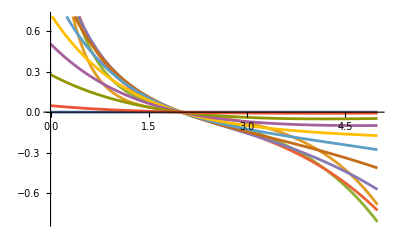

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

```mathematica
crossingEq[10]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify;
```

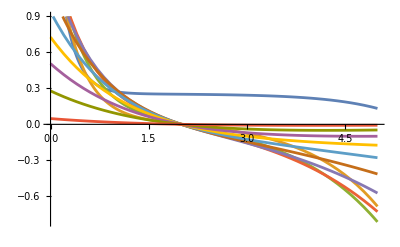

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

```mathematica
crossingEq[5]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify;
```

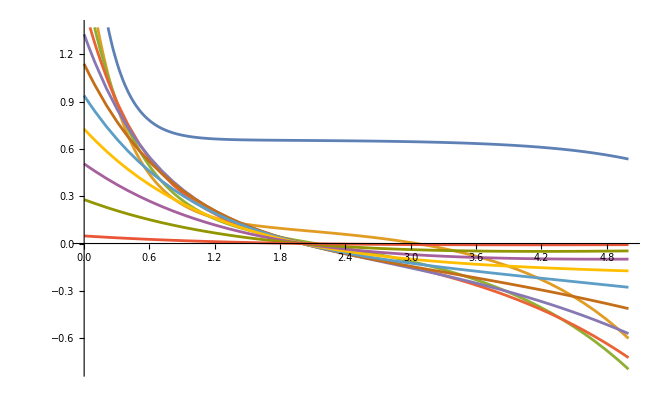

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

```mathematica
crossingEq[10]/.C[0]->c[0]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify;
```

```mathematica
Table[c[0]/.Solve[(crossingEq[5]/.C[0]->c[0]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify)[[i]]==0,c[0]][[1]],{i,11}]
```

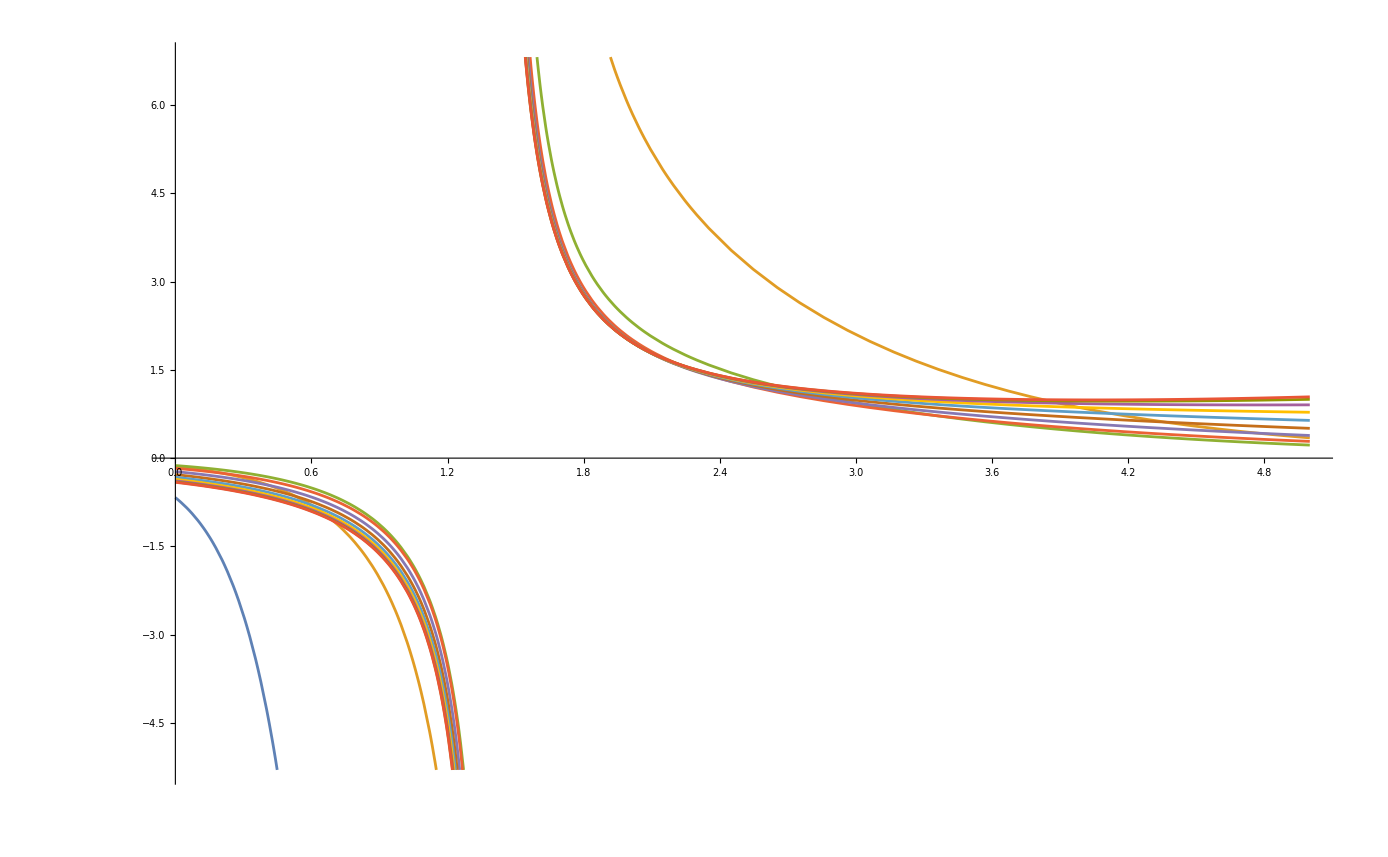

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

```mathematica
Table[c[0]/.Solve[(crossingEq[10]/.C[0]->c[0]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify)[[i]]==0,c[0]][[1]],{i,11}]
```

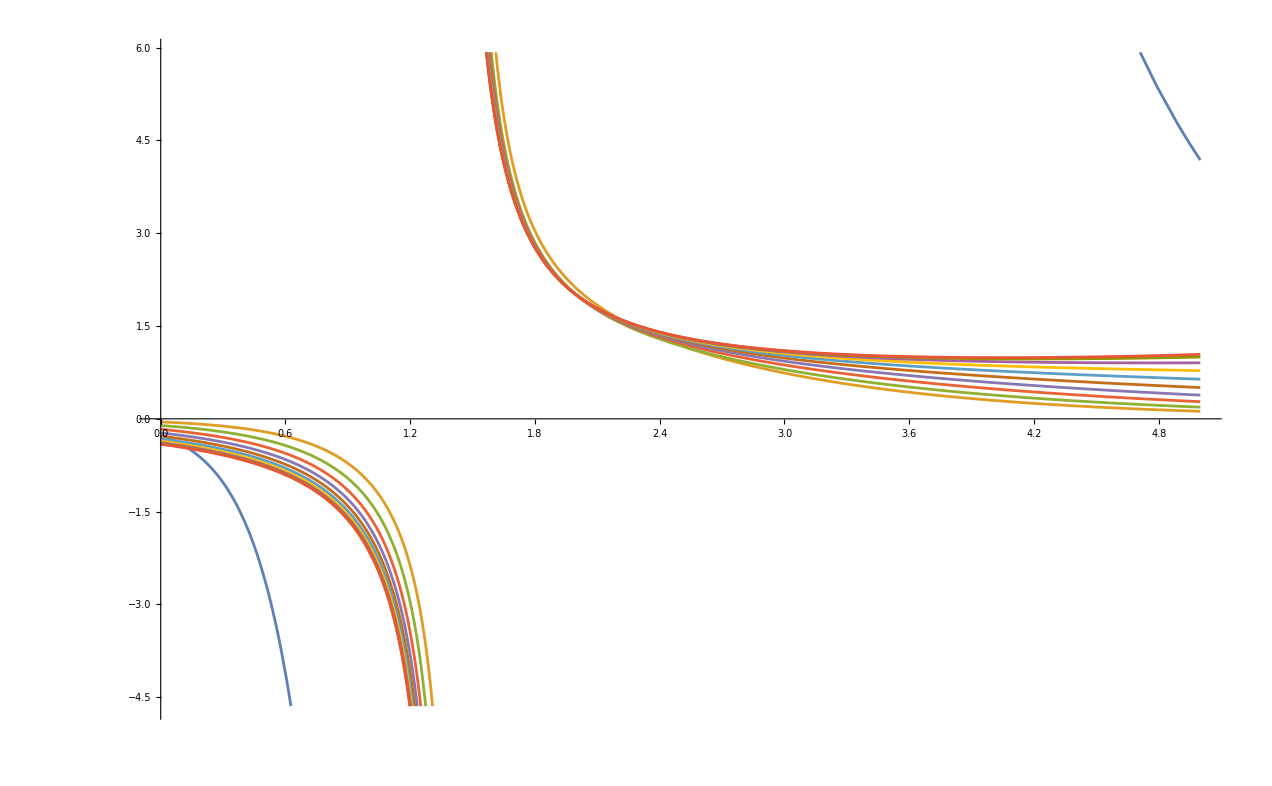

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

```mathematica
Table[c[0]/.Solve[(crossingEq[20]/.C[0]->c[0]/.Δ[0]->d[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify)[[i]]==0,c[0]][[1]],{i,11}];
```

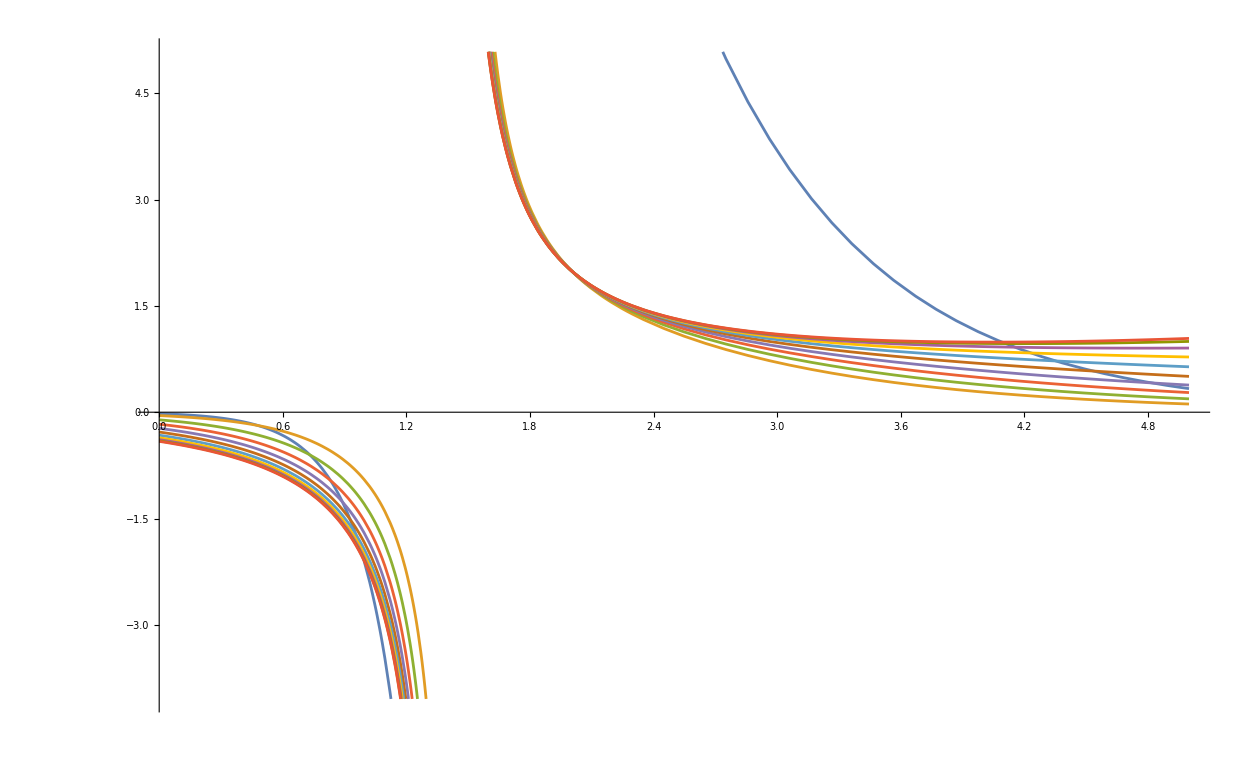

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

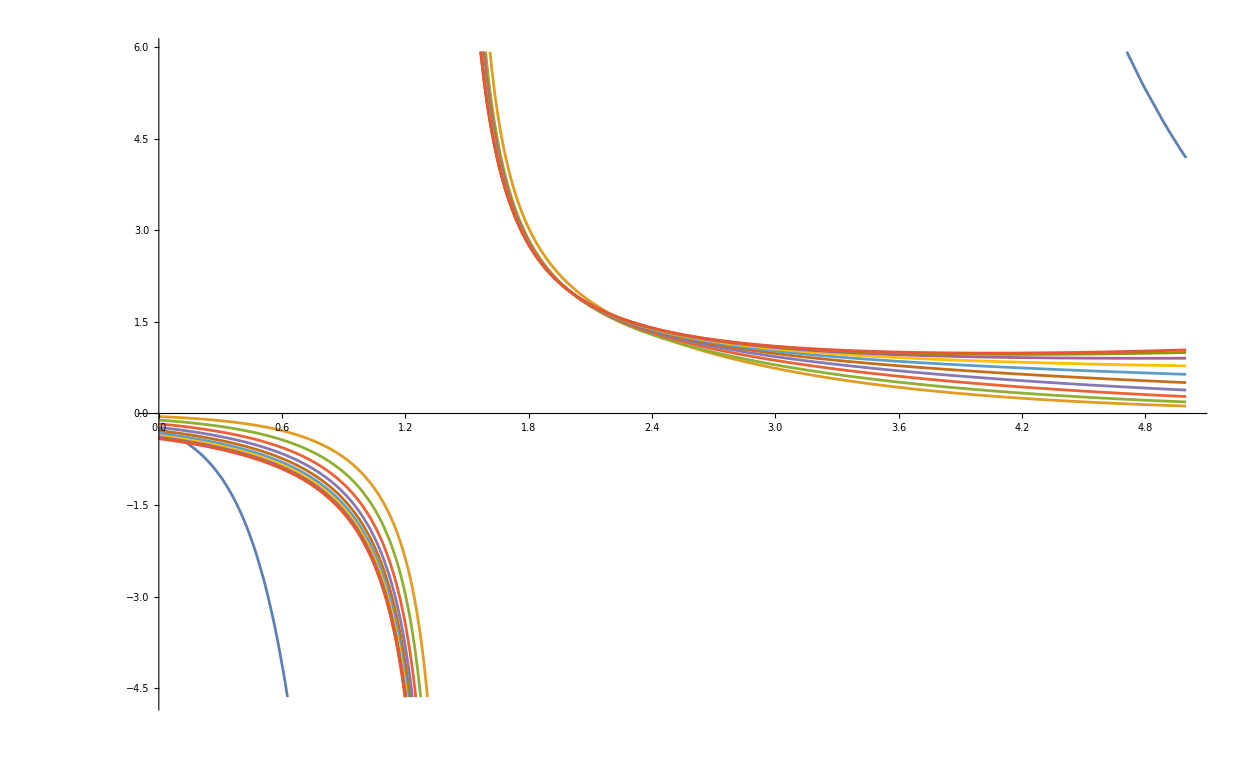

```mathematica
Plot[%2035,{d[0],0,5},WorkingPrecision->30]
```

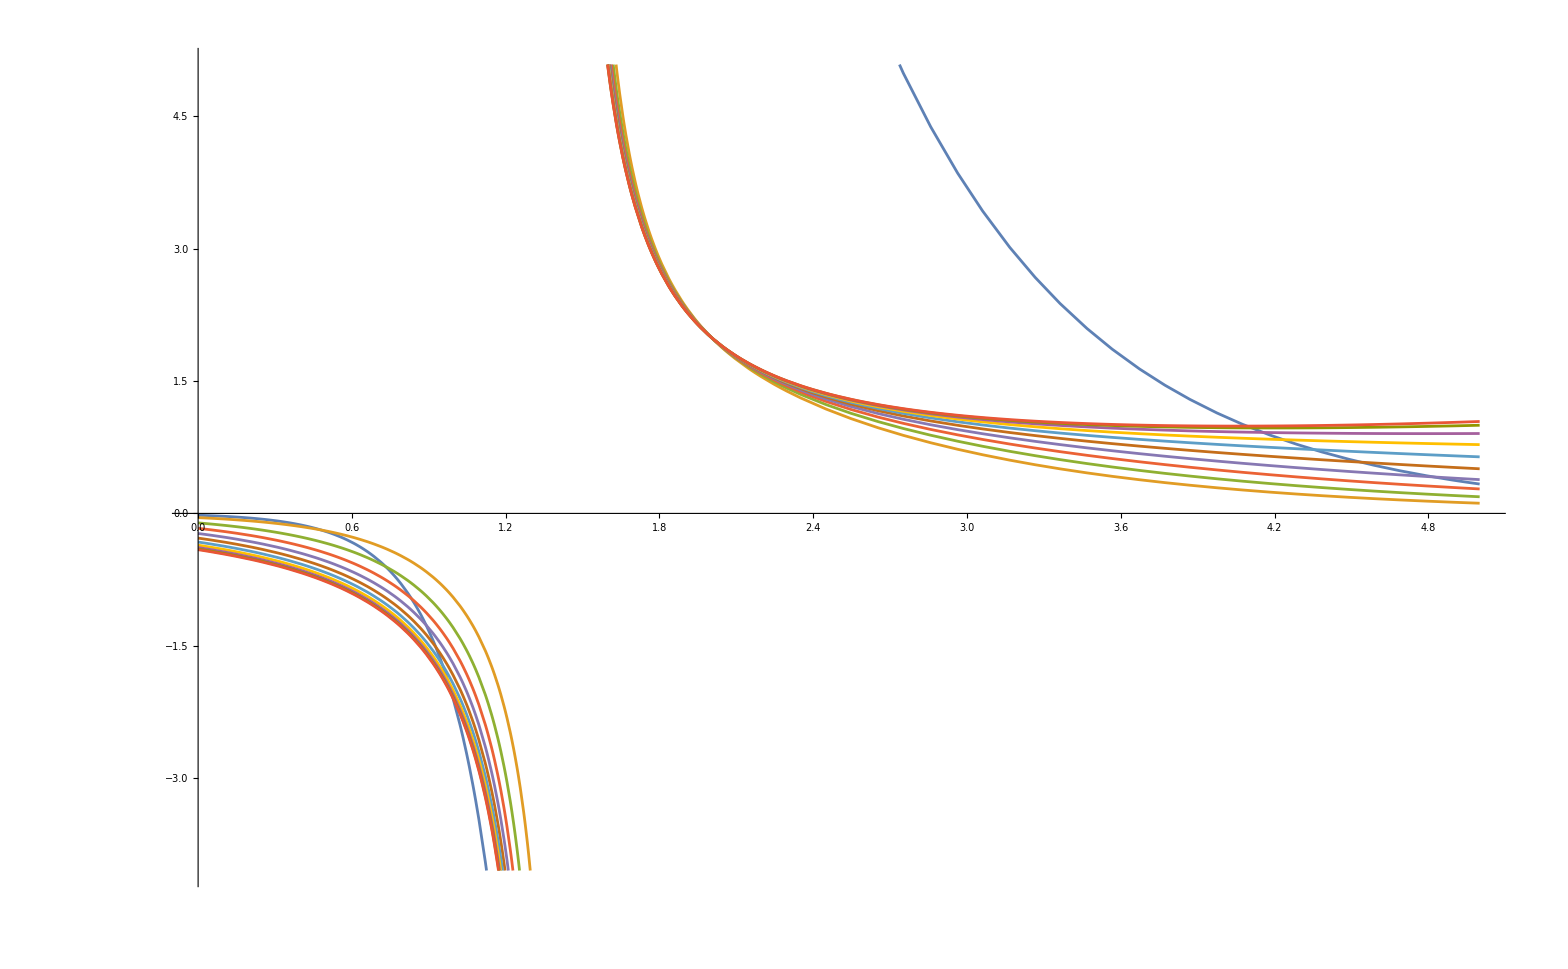

```mathematica
Plot[%,{d[0],0,5},WorkingPrecision->30]
```

```mathematica
Table[c[0]/.Solve[%[[i]]==0][[1]],{i,11}]
```

```mathematica
3.63391 and 1.52419
```

```mathematica
N[3.63391
```

```mathematica
crossingEq[1]/.Δσ->1
```

(1-z)^2-z^2+C[0] (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^2 z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])

```mathematica
N[crossingEq[2]/.C[0]->c[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify,30]
```

{0.910294025966220238764094236429-0.0015199233562570685810504192351 c[0],0.493475251881326680731546298246-0.0210113976097971505739363678225 c[0],0.306427518782207749442106714279-0.0423178539781331867226724448289 c[0],0.2269739672544861249626024526-0.0585252601582749107448657204281 c[0],0.190102843704220680663428208376-0.067798710111611548886427408903 c[0],0.166700525738539987703651936299-0.0699450140266072260199911352185 c[0],0.144022116222524876327670561044-0.0655218863459512291815565022 c[0],0.117095099060674750414936894717-0.055484305162424806894257535749 c[0],0.0847962236945936682739489807733-0.0410138724545926590228592847418 c[0],0.0479555884802524112668786596814-0.0234253198070473679857139593215 c[0],0.00838342848040658843496261524594-0.00410952323930961669969088186038 c[0]}

```mathematica
N[crossingEq[5]/.C[0]->c[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify,30]
```

{0.657391207447981893651907567503-0.0015199233562570685810504192351 c[0],0.12551669409015163135912627937-0.0210113976097971505739363678225 c[0],0.0994455048942834386625590804972-0.0423178539781331867226724448289 c[0],0.120096829131338344973897441462-0.0585252601582749107448657204281 c[0],0.136271417719552380152242140104-0.067798710111611548886427408903 c[0],0.140043989075303538335167652379-0.0699450140266072260199911352185 c[0],0.131079100473167282344220189988-0.0655218863459512291815565022 c[0],0.110976579710617637056389793301-0.055484305162424806894257535749 c[0],0.0820294779320508207120123322828-0.0410138724545926590228592847418 c[0],0.0468509910328340750922955271445-0.0234253198070473679857139593215 c[0],0.00821908136028355966550085776283-0.00410952323930961669969088186038 c[0]}

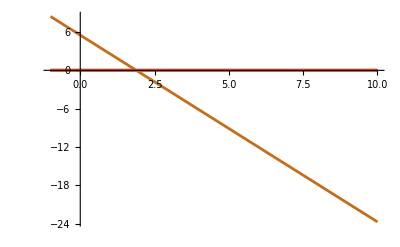

```mathematica
Plot[%,{c[1],-1,10},WorkingPrecision->30]
```

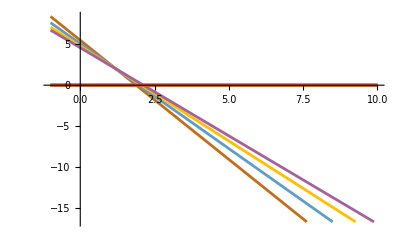

```mathematica
Plot[%,{c[1],-1,10},WorkingPrecision->30]
```

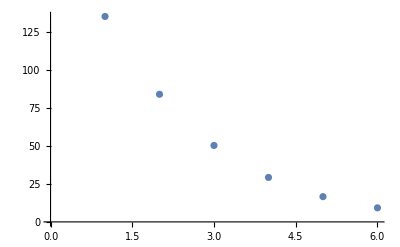

```mathematica
ListPlot[%]
```

```mathematica
std=Table[getStd[n],{n,10,20,2}];
```

```mathematica
getStd[10]
```

135.27480660120814045470268965

```mathematica
getStd[10,genBos]
```

135.27480660120814045470268965

```mathematica
Solve[N[eqs/.%1855[[2]],30][[1]]==0]
```

{{c[0]→-4.4887443773897196194569686971×10^6}}

```mathematica
%1855[[2]]/.c[i_]->C[i]
```

{C[1]→2.7549464811086484354667450614920813410562529735108,C[2]→0,C[3]→3.3061449748591948516462935003801248967647552490234,C[4]→3.3408882872935817154314008803339675068855285644531,C[5]→0,C[6]→3.16839054934056861420649208717991086012233941954,C[7]→2.9101341360100948074673965493275318294763565063477,C[8]→2.6040713885060350563094289100263267755508422851562,C[9]→3.7244797406463094002759817158221267163753509521484,C[10]→2.9751496459984601461457032200996764004230499267578,C[11]→2.8954220044106800169281257240072591230273246765137,C[12]→3.1161252158468476403108127215091371908783912658691,C[13]→2.6497172509646619409373613507341360673308372497559,C[14]→2.8224416841754307094802811661793384701013565063477,C[15]→0}

11

```mathematica
crescRule
```

C[j_]→ⅇ^(-Δ[j]/2) c[j]

```mathematica
eqs=crossingEq[5]/.C[j_]-> c[j]/.genBos/.Δσ->1/.zvalsTable[11][[5;;]]//Cancel;
```

```mathematica
eqs=crossingEq[10]/.crescRule/.genBos/.Δσ->1/.zvalsTable[11]//Cancel;
```

```mathematica
c0s=c[0]/.Table[Solve[eqs[[i]]==0,c[0]][[1]],{i,Length[eqs]}];
```

```mathematica
Table[c[i]>=0,{i,15}]
```

{c[1]≥0,c[2]≥0,c[3]≥0,c[4]≥0,c[5]≥0,c[6]≥0,c[7]≥0,c[8]≥0,c[9]≥0,c[10]≥0,c[11]≥0,c[12]≥0,c[13]≥0,c[14]≥0,c[15]≥0}

```mathematica
Table[Δ[i],{i,0,9}]/.genBos/.Δσ->1
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
nst=5;
```

```mathematica
getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]]]
```

```mathematica
getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],45/100,49/100]
```

{{2.0424261065270798059856,0.0003879050584576985168},{1.1649633233978189178514,0.0003113984996252716152},{0.26122041956400261266665,0.00018751892174767500904},{0.021472381902943795459383,0.000073740855639926585564},{0.007017907761365052038434,0.000013853591930313663185}}

```mathematica
Table[Δ[i]/.genBos/.Δσ->1//N,{i,0,10}]
```

{2.,4.,6.,8.,10.,12.,14.,16.,18.,20.,22.}

```mathematica
Table[Δ[i]/.genFer/.Δσ->1,{i,0,10}]
```

{3,5,7,9,11,13,15,17,19,21,23}

```mathematica
Table[C[i]/.genFer/.Δσ->1//N,{i,0,10}]
```

{2.,0.571429,0.0909091,0.0111888,0.00119076,0.000115378,0.0000104695,9.05037×10^-7,7.53708×10^-8,6.09373×10^-9,4.80966×10^-10}

```mathematica
getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],45/100,49/100]
```

{{2.0424261584821262679871,0.0003949482238140343926},{1.164963283526508990763,0.0003170249368606042744},{0.26122044027554592916751,0.00019085773169270568421},{0.021472376189721930664212,0.000075017782995372072828},{0.0070179081332066289472406,0.000014083232202614335857}}

```mathematica
getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],(49)/100,49999/100000]
```

{{1.849670847437736943468,0.0000683215649993882759},{1.319868474297227411749,0.0000518439632046716673},{0.1676398027937080392229,0.0000258189872157601371},{0.05849229093332705180878,6.16000330363231349×10^-6}}

```mathematica
nst=4
```

4

```mathematica
{2,4,6,8,10,12,14,16,18,20}//Length
```

10

```mathematica
{2,4,6,8,10,12,14,16,18,20}+ϵ RandomReal[10]/.ϵ->.01
```

{2.05905,4.05905,6.05905,8.05905,10.059,12.059,14.059,16.059,18.059,20.059}

```mathematica
getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],(49-20)/100,49/100]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.000623270760337918261235136770619,-0.0010983989038599915253556006282,-0.00192065664385438039186329334756,-0.00331971874878800782847306638677,-0.00563753531111445356093260929518,-«64»,-0.014674782371706120556522407877,-0.0212039526823198163895463210464,-0.0251025310960050771266608708168,-0.0123584220024578619171604732405,«1»},«8»,{-«64»,-«64»,«7»,-«64»,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.000495575847831993370946060459327,-0.000887813884131000891868923159864,-0.00157613609672233005237428916947,-0.00276183367859310202599063047861,-0.0047470346870464261911536860029,-«64»,-0.0125864232864379948819462809107,-0.0182962142718712996148570483248,-0.0217408163215691733564435172283,-0.0107180322363812226601877298203,«1»},«8»,{-«64»,-«64»,«8»,«1»}} may contain significant numerical errors.

{{1.999918733650513038,0.00002970491053365},{1.200070927641437448,0.00002579027601188},{0.2380392276464164082,0.000020026409085376},{0.03267369221210126251,0.0000137033512087972},{0.003677855297841899239,7.938151429423692×10^-6},{0.0003867039789508606328,3.73093973705107×10^-6},{0.00002987688274502204627,1.3525770525789905×10^-6},{4.691856995419842204×10^-6,3.5238455684610328×10^-7},{-8.507947410391223526×10^-8,5.843108485438927852×10^-8},{6.574308104775813678×10^-8,4.6165578921731608×10^-9}}

```mathematica
%83[[;;,2]]/%83[[;;,1]]
```

{0.000953538453543499178552,0.001345184492282688276405,0.003537819376641159766088,0.017486485507798026931633,0.009190757122220898628554}

```mathematica
%98[[;;,2]]/%98[[;;,1]]
```

{0.000032005271036028789349,0.000209822940147056218703,0.00117404542690328504135,0.006497664143309622825332,0.005956759952305669506672}

```mathematica
%106/%107
```

{29.793169146109944308,6.41104586247768768246,3.01335816789702173654,2.691195654642005606279,1.54291211930798943872}

```mathematica
{(49-10)/100,49/100}//N
```

{0.39,0.49}

```mathematica
getAvCs[nst,{3,5,7,9,11,13,15,17,19,21,23}[[;;nst]],(49-10)/100,49/100]
```

{{2.001888889877421234800845,0.000064070996504541656514},{0.5677298521361696073852267,0.00011912274678446459266},{0.09480036772317689418763687,0.000111299938194145620888},{0.008696977545967761628947741,0.00005651003915560364173001},{0.002080035274520524839698731,0.00001239027082264699172336}}

```mathematica
ParallelTable[getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],(49-z)/100,49/100],{z,1,10}];
```

$Aborted

```mathematica
getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],(49-5)/100,49/100]
```

{{2.04294387440981168610545,0.00069260892741605179413},{1.16454781345316150882157,0.00055559820884880170636},{0.261470386168920941188059,0.00033384659933276895096},{0.0213742623671410245865545,0.00013075756352906963563},{0.00703629119165811454920785,0.0000244173268167180195993}}

```mathematica
ParallelTable[getAvCs[nst,{2,4,6,8,10,12,14,16,18,20}[[;;nst]],(49-zz)/100,49/100],{zz,5,20}];
```

```mathematica
%89[[;;,1,2]]
```

{0.00058268919674354155116,0.0010921144809566120583,0.00092440122369679106426,0.00143968870700077334049,0.00178965287793382875835,0.001649084515791258112823,0.00224326062879485021214,0.00360015206095408618906,0.00479241861603223563781,0.003660593823742860424815,0.0061862073471722154730646,0.0084467521144873060363126,0.0037264638497600393282545,0.0041256120664847126614668,0.0091151039978692573188644,0.016022003797270533379521}

```mathematica
%89[[;;,1,2]]
```

{0.00058268919674354155116,0.0010921144809566120583,0.00092440122369679106426,0.00143968870700077334049,0.00178965287793382875835,0.001649084515791258112823,0.00224326062879485021214,0.00360015206095408618906,0.00479241861603223563781,0.003660593823742860424815,0.0061862073471722154730646,0.0084467521144873060363126,0.0037264638497600393282545,0.0041256120664847126614668,0.0091151039978692573188644,0.016022003797270533379521}

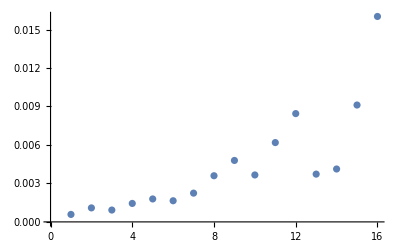

```mathematica
ListPlot[%]
```

```mathematica
getAvCs[6,{2,4,6,8,10,12},4/10,49/100,1]
```

{{1.987899240697086327,0.001362725973821629},{1.210198235569853221,0.00112725716083903},{0.2309028677039679375,0.0007489992834433282},{0.03665172199506408738,0.00036898072450006099},{0.002091507413943467395,0.00011686137460722114},{0.0007665073078725547011,0.000017599083022465324}}

```mathematica
{Δ[0]->1,C[0]->0.25000000000000006,Δ[1]->2,C[1]->0.03125,Δ[2]->3,C[2]->0.002604166666666662,Δ[3]->4,C[3]->0.000683595,Δ[4]->5,C[4]->0.00007062639508926867,Δ[5]->6,C[5]->0.00003267315555555557}
```

```mathematica
crossingEq[5]/.{Δ[0]->1,C[0]->0.25000000000000006,Δ[1]->2,C[1]->0.03125,Δ[2]->3,C[2]->0.002604166666666662,Δ[3]->4,C[3]->0.000683595,Δ[4]->5,C[4]->0.00007062639508926867,Δ[5]->6,C[5]->0.00003267315555555557}/.Δσ->1/8/.z->4/10
```

0.0000132227

```mathematica
N[crossingEq[5]/.genBos/.Δσ->1/8/.z->4/10,30]
```

9.0460382395238763639631350353×10^-10

```mathematica
getAvCs[7,{1,2,3,4,5,6,7},4/10,49/100,1/8]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.38376030384105664986760676729,-0.419355205336617059135961650165,-0.452385183284447822449541929199,-0.47629509502498196369915637101,-0.477730781018803093504798066171,-0.429873823366751763260537984076,-0.279115571168798923441461641918,0.0848410080263427320972147299389},{-0.374468565916857850065570496865,-«64»,«4»,-«64»,«64»},«3»,{«1»},«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.322717534848821596416262248894,-0.359650859591383722666530260961,-0.394924759671046532079747439854,-0.422180535822266107772048889968,-0.428592887490481429638612950852,-0.388852454549076216391823794643,-0.253464287987768897120499529901,0.0769735858743562756120595157433},«5»,{-0.277142215153795901383447166133,-«64»,-«64»,«2»,-«64»,-«64»,«64»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.270085245860335785779857760511,-0.306669751077239599027334899591,-0.342406574670804115721278598372,-0.371249329995500932528036273652,-0.381083504764452693268334535509,-0.348349423076324603914930825026,-0.227861401467907708291327771409,0.0691416055343618886643790630183},{-0.263172196741041951304449618004,-«64»,«4»,-«64»,«64»},«3»,{«1»},«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{0.3155102565521,0.002669948765},{-0.0488059137686,0.0032487378186},{0.05174637312741,0.0019688029636},{-0.01936404152297,0.00077941345866},{0.005910472269808,0.00021290077475},{-0.001097197089096,0.000036972140333},{0.0001199584508183,3.0941333587×10^-6}}

```mathematica
getAvCs[6,{1,2,4,6,3+1/10,5+2/10},3/10,49/100,1/8]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0914573013145680926780746584746,-0.116102974448319276081932262688,-0.0789679806329083280666623998895,-0.108561490819993693979701208006,-0.109523990803582947507236962007,-0.072599882718990439501513600151,0.0219619245914125558457233206258},«4»,{-0.0344852428639099965001921823487,-«64»,-«64»,-«64»,-«64»,-«64»,0.00840970008869550334931109764006}} may contain significant numerical errors.

{{0.21718381733688865,0.00512622870463478},{0.069482725998950936,0.005896054142634409},{0.010039908826063378,0.001356218715219843},{0.00041743570483865984,0.00004105433828692373},{-0.020415204069775517,0.003462493303389424},{-0.0018398326780808997,0.0002412610619882081}}

```mathematica
1/8 external contributions
```

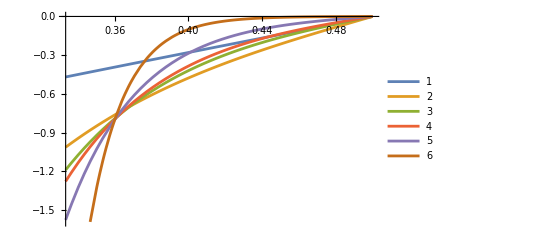

```mathematica
Plot[{(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1/8/.Δ[0]->1,(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1/8/.Δ[0]->4,(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1/8/.Δ[0]->6,(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1/8/.Δ[0]->7,(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1/8/.Δ[0]->10,(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1/8/.Δ[0]->20},{z,1/3,1/2},PlotLegends->Automatic]
```

```mathematica
gen bos state contributions
```

```mathematica
DiagonalMatrix[Table[C[i],{i,0,6}]].crossingTable[6]/.genBos/.Δσ->1
```

{2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3),6/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)),5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)),14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])),1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])),(11 (-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/29393,(13 (-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z]))/371450}

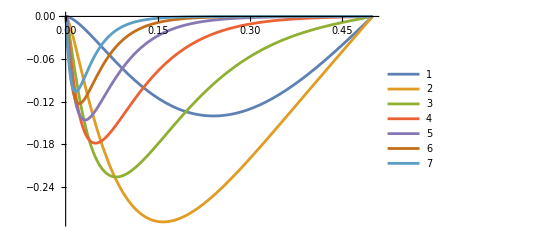

```mathematica
Plot[{2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3),6/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)),5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)),14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])),1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])),(11 (-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/29393,(13 (-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z]))/371450},{z,0,1/2},PlotLegends->Automatic,WorkingPrecision->30]
```

```mathematica
Table[N[D[{2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3),6/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)),5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)),14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])),1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])),(11 (-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/29393,(13 (-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z]))/371450},{z,n}]/.z->1/2,50],{n,1,8}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating «1».

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

General::stop: Further output of N::meprec will be suppressed during this calculation.

{{0.82233833280656286993214542501881183093998387676937,0.99672971238332698295140206027125969323119671607575,0.16457100255058534258233384622055560027333940804921,0.015234910512107001026261537135023072023536725329539,0.0010604033069027067056717630331979186597015707859979,0.000062216748408492575669182828505086534562153786690435,3.2570838414528111163735177350409754601300069012642×10^-6},{0.,0.,0.,0.,0.,0.,0.},{-26.022208020227985794605615679277625691904619132056,4.3885609901610133365491613587978920136651371013657,17.003685640595182357914386043034951454741191187577,4.054544015331967372661972011242035514181003625323,0.52269090092968746135416988125859586522036569759942,0.048758347264452396470167626901990407337943601792741,0.003708014472311772241718631796810125500741371592919},{0.,0.,0.,0.,0.,0.,0.},{222.2233583817611364315507456577899446476304694355,-1734.8099173903459205629353285784011188588174027776,530.26752127504551926462597974738034721712622497843,741.60214686352921741596490468969831684335982852035,204.41655066196803047126313821517165036519660898683,32.242634864087176763106102924121862758004771064648,3.6881724433023511502096042814699265769762698423552},{0.,0.,0.,0.,0.,0.,0.},{18901.524208135870920500525270508710700801918865165,-106240.16572656938663119039312507447480392383200711,-94719.669281999899586476701549772997955187732651926,92672.766749646036852678081813384410799919185722981,66877.817701375794455009417323180508907306892207471,18724.947141437785754893355956276626219053469660829,3299.3576570749327448934619845598701673183557540677},{0.,0.,0.,0.,0.,0.,0.}}

```mathematica
getAvCs[6,{1,2,3,4,5,6},4/10,49/100,1/8]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.21668651942270465063069929323,-0.249216975994871944359941372097,-0.27697428359381248286598364843,-0.289783869638246123515554112761,-0.26828971478290889976685403348,-0.176533393673397287189072583641,0.0534932680675419062537738902787},«4»,{-0.184497227858018449334877476282,-«63»,-«64»,-«64»,-«63»,-«63»,0.0470190692853314741982878189398}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.178363718965036121212881902267,-0.207735425972938874770737177195,-0.233266396427747648547268977788,-0.245975877714719601099979745531,-0.228914122900436456809016638095,-0.150983897171707949033432718498,0.0457260525254727661493077642282},«4»,{-0.149042458303551806497786148623,-«64»,-«64»,-«64»,-«64»,-«64»,0.0392691664177794598451714709564}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.143426077131947759978887938035,-0.168874916522083520897647215902,-0.191317776200865664389084024637,-0.203094532378335178624274487546,-0.189838438312302350502804101634,-0.125462843717829862303059274715,0.0379793131445538007439945356743},«4»,{-0.116422062506022548523574270622,-«64»,-«64»,-«64»,-«63»,-«63»,0.0315367664299683759442518265559}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{0.21232597126950171,0.0013359520487656},{0.076752577465375198,0.00160076643548798},{-0.024355251725216499,0.000926622824708785},{0.010772537370177882,0.000328542458992386},{-0.0023260976791166311,0.000070891374489163},{0.00033441386803030884,7.20325795893331×10^-6}}

```mathematica
getAvCs[5,{2,4,6,8,12+9/10},4/10,49/100,1]
```

{{1.9418278817636226447911,0.0026117168022927718711},{1.2478462365145968588133,0.0020299530413789449222},{0.20695878397058415831013,0.0010907622455266585063},{0.047089781739848325840015,0.000307391461025005398},{0.00059190178516339053572968,0.0000140792967649397773093}}

```mathematica
crossingEq[4]/.Δσ->1/.Table[Δ[i-1]->{2,4,6,8,12+9/10}[[i]],{i,5}]/.Table[C[i-1]->Rationalize[%17[[i,1]],0],{i,5}]
```

(1-z)^2-z^2+(89748487663 (-(1-z)^(129/10) z^2 Hypergeometric2F1[129/10,129/10,129/5,1-z]+(1-z)^2 z^(129/10) Hypergeometric2F1[129/10,129/10,129/5,z]))/151627330602197+(490742365167 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3))/252721865710+1/527922475451 658766074163 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+1/504863364325 104485907952 (1/(5 z^5)462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z])-1/(5 (-1+z)^11)462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))+1/1278476297206 60203169795 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))

```mathematica
N[%31/.z->1/3,30]
```

-1.8807954868828008516920020772×10^-7

```mathematica
N[%26/.z->1/3,30]
```

0.000110864581964272907434935337716

```mathematica
crossingEq[4]/.genBos/.Δσ->1
```

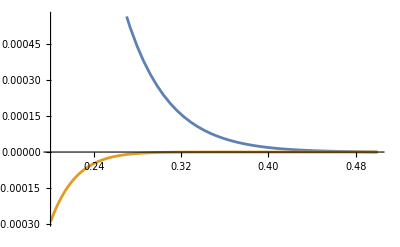

```mathematica
Plot[{%26,%31},{z,1/5,1/2},WorkingPrecision->20]
```

```mathematica
crossingEq[5]/.genBos/.Δσ->1/8/.z->4/10//N
```

9.04605×10^-10

```mathematica
crossingEq[5]/.{Δ[0]->1,C[0]->0.5000000000000001,Δ[1]->2,C[1]->0.0078125,Δ[2]->3,C[2]->0.005208333333333324,Δ[3]->4,C[3]->0.000515747875,Δ[4]->5,C[4]->0.00014125279017853734,Δ[5]->6,C[5]->0.000011276457986111136}/.Δσ->1/8/.z->4/10
```

-0.0608776

```mathematica
getAvCs[4,{1,2,4,6},4/10,49/100,1/8]
```

{{0.245410487160598925240409,0.000025015649246034316817},{0.0364681883244473876524138,0.0000205124477690789207159},{0.00135242304500036971743683,4.495965462249833835928×10^-6},{0.0000530521080029673785656931,7.295607344905211003632×10^-7}}

```mathematica
getAvCs[6,{1,2,3,4,5,6},40/100,49/100,1/8]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.21668651942270465063069929323,-0.249216975994871944359941372097,-0.27697428359381248286598364843,-0.289783869638246123515554112761,-0.26828971478290889976685403348,-0.176533393673397287189072583641,0.0534932680675419062537738902787},«4»,{-0.184497227858018449334877476282,-«63»,-«64»,-«64»,-«63»,-«63»,0.0470190692853314741982878189398}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.178363718965036121212881902267,-0.207735425972938874770737177195,-0.233266396427747648547268977788,-0.245975877714719601099979745531,-0.228914122900436456809016638095,-0.150983897171707949033432718498,0.0457260525254727661493077642282},«4»,{-0.149042458303551806497786148623,-«64»,-«64»,-«64»,-«64»,-«64»,0.0392691664177794598451714709564}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.143426077131947759978887938035,-0.168874916522083520897647215902,-0.191317776200865664389084024637,-0.203094532378335178624274487546,-0.189838438312302350502804101634,-0.125462843717829862303059274715,0.0379793131445538007439945356743},«4»,{-0.116422062506022548523574270622,-«64»,-«64»,-«64»,-«63»,-«63»,0.0315367664299683759442518265559}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{0.21232597126950171,0.0013359520487656},{0.076752577465375198,0.00160076643548798},{-0.024355251725216499,0.000926622824708785},{0.010772537370177882,0.000328542458992386},{-0.0023260976791166311,0.000070891374489163},{0.00033441386803030884,7.20325795893331×10^-6}}

```mathematica
getAvCs[6,{1,2,4,6,8,10},4/10,49/100,2]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00165857676619573788816347615228,-0.00248889439994524286657049604816,-0.00320532427905671526619683855519,-0.00253125920872319620895730366953,0.00360836680029858317952510935596,0.0118373460928181595008500478163,0.0268564811786988932656211199782},«4»,{-0.00116666400079759269856553413652,-«64»,-«64»,-«64»,«64»,«63»,0.0191806445060108384985806728049}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00107087243870375321670566914703,-0.00162644867498670751858589795399,-0.00211124375006289681745843851276,-0.00167343810225460736010249188368,0.00238300972259429504367979370413,0.007802858344317562864331085253,0.0176490267067226931672663709532},«4»,{-0.000601406826501175965432250330454,-0.000919216059540191091977973507576,-«64»,-«63»,«64»,«64»,0.010004}} may contain significant numerical errors.

{{-34.7325940036618538,0.8914252140908759},{602.107205530168937,34.50604561906358},{589.713147756671511,36.02908505995237},{86.0862789799435073,6.499994758115897},{7.91434548832663865,0.7337234688688256},{-0.006541830247723134,0.059533875317405708}}

```mathematica
getAvCs[5,{1,4,6,8,10},4/10,49/100,2]
```

{{-19.1503188828821819918,0.1437385617300548585},{-38.9149023144044886137,0.2844389567191236168},{-27.2828825343500245269,0.2707563938495574885},{-4.88245130282937016043,0.02981847372990870844},{-1.04087723860913754422,0.02379240709162391245}}

```mathematica
getAvCs[8,Table[2+4 i,{i,0,10}],4/10,49/100,1,40]
```

{{3.57363190287223410354549279,0.0023572074531903084403245},{0.809286740198394822139036766,0.00240059961025442416710615},{-0.119762891859654454254970327,0.003561297114846827895207401},{0.0698628535213507792289029554,0.004723849600712423211356393},{-0.0393864333291687721795351574,0.004926639492554666321397716},{0.018638969464749319148665786,0.0036841372088171571735272367},{-0.00616833906042660923472953356,0.0017403387679736805861781804},{0.00103722765918605197855668849,0.00038898031265557962797471427}}

```mathematica
getAvCs[8,Table[2+3 i,{i,0,10}],4/10,49/100,1,40]
```

{{2.949343280639709509045602,0.000700013313771577883745},{0.9920848999396692998318501,0.0006289207192365780266527},{0.002382763294731503894436997,0.0006607176394054373966115493},{0.02023494085352267533949396,0.00061230351830736206963037},{-0.007147837093526750953493133,0.000449649680161431545016322},{0.002352109231952699285696939,0.000239095259080328350386339},{-0.0005389596266298589427204167,0.0000809190910772453672300842},{0.00006301903872963257095274708,0.0000130140280382374140686106}}

```mathematica
getAvCs[8,Table[2+3 i/2,{i,0,10}],4/10,49/100,1,50]
```

{{0.53324498130903543089099692504085,0.08547583019079867173785424883229},{2.0291404785725341668013587999202,0.0754490225845238971682754421245},{-0.10164747196338489575285448879563,0.04774613956037652760808294456361},{0.3899839487830184909676739734781,0.0241140096967420625344582486801},{-0.09334004992898927491479142936895,0.00952007630312358826173465338151},{0.042953243520397631467123603618895,0.0027535872162044288949478482454},{-0.007678706649487422968695193794161,0.000516397127653633140036750540713},{0.0012413782783067634309111589351316,0.0000468876638825475371940074994274}}

```mathematica
getAvCs[8,Table[2+i,{i,0,10}],3/10,49/100,1,50]
```

{{-7006.4248804136823702107483188282,1944.114735474094270941374906509},{6860.4903482966943660295056967632,1898.579029538152125930379855133},{-3849.2873529172814854769521185226,1057.908047198201598987827828542},{1573.5460265921222941170339288942,425.4514926302506166042022426072},{-488.10157559341254002585703417514,128.1843014348355911399450953065},{111.48907411713177798688118298591,27.8610581197961672434297083366},{-16.897884536137422765966682720354,3.914964374911973102387375734713},{1.3104838094873978677759171338122,0.2670226927523743360526148628491}}

```mathematica
N[crossingEq[10]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1/.z->4/10,30]
```

3.32856165507289385354070943287×10^-6

```mathematica
N[crossingEq[10]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1/.z->4/10,30]
```

```mathematica
Table[{Δ[n]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},N[crossingEq[n]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1/.z->4/10,30]//Log},{n,1,10}]
```

{{3,-2.41814714808441810129670696463},{4,-3.24527935903087817933296517568},{5,-4.2174700795799599550279837393},{6,-5.2845635884721880707958454029},{7,-6.41734686897168158707885632482},{8,-7.59783851814548181540517033218},{9,-8.81441082074659413387903834121},{10,-10.05921218018042708561156416324},{11,-11.32673271691302625938466648947},{12,-12.6129702826964382809766310106}}

```mathematica
crossingEq[7]/.Δσ->1/.Δ[i_]->2+i/.C[i_]->%5[[i+1,1]]/.z->4/10
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

2.05360621215852073×10^-11

```mathematica
{crossingEq[7]/.Δσ->1/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},crossingEq[7]/.Δσ->1/.Δ[i_]->2+i/.C[i_]->%5[[i+1,1]]}
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

{(1-z)^2-z^2+(6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(30 (1-z)^2 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^2-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3-(30 (1-z)^3 z^2 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+3/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+2/7 (-(105 (1-z)^2 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^4-(105 (1-z)^5 z^2 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9)+5/42 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))+1/22 (-1/(5 z^6)6006 (1-z)^2 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z])-(6006 (1-z)^7 z^2 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13))+7/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))+4/715 (-1/(14 z^8)21879 (1-z)^2 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z])-1/(14 (-1+z)^17)21879 (1-z)^9 z^2 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z])),(1-z)^2-z^2-7006.4248804136823702107483188282 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)+6860.4903482966943660295056967632 (-(30 (1-z)^2 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^2-(30 (1-z)^3 z^2 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5)-3849.2873529172814854769521185226 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+1573.5460265921222941170339288942 (-(105 (1-z)^2 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^4-(105 (1-z)^5 z^2 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9)-488.10157559341254002585703417514 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))+111.48907411713177798688118298591 (-1/(5 z^6)6006 (1-z)^2 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z])-(6006 (1-z)^7 z^2 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13))-16.897884536137422765966682720354 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))+1.3104838094873978677759171338122 (-1/(14 z^8)21879 (1-z)^2 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z])-1/(14 (-1+z)^17)21879 (1-z)^9 z^2 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z]))}

```mathematica
{C[0],C[1]}/.genBos/.Δσ->1
```

{2,6/5}

```mathematica
y/.Solve[crossingEq[4]==0/.C[0]->x/.C[1]->y/.genBos/.Δσ->1,y][[1]]
```

(-(1-z)^2+z^2-x ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)-5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))-14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))-1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])))/((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))

```mathematica
%/.{{z->49/100},{z->3/10},{z->4/10}};
```

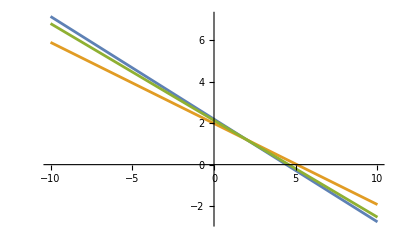

```mathematica
Plot[%,{x,-10,10},WorkingPrecision->50]
```

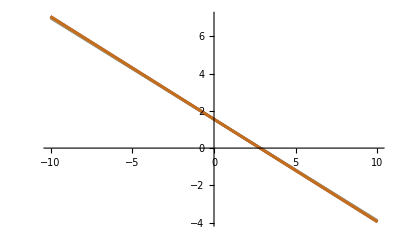

```mathematica
Plot[%,{x,-10,10},WorkingPrecision->50]
```

```mathematica
Table[y/.Solve[%31[[i]]==0,y][[1]],{i,Length[%31]}]
```

{(214915746288133958504851504035+150930273851926797690 x-336402403289665938932748432391 Log[20/11]-144444745679275449639 x Log[20/11]-17284670552101925394797808069 Log[20/9]-79113613523810520501 x Log[20/9])/(32951805229035 (-146980350+161387743 Log[20/11]+63140877 Log[20/9])),(881595769359978395802524963129732966925+779657079886994903731034602950 x-1280248104169375763819435326952964834534 Log[50/27]-704501843808933859397314657086 x Log[50/27]-119409136946386901762824087299525130766 Log[50/23]-435486152193430791408175960614 x Log[50/23])/(277010819323640552430 (-88915789125+90401125599 Log[50/27]+42706814851 Log[50/23])),(62783322429127215260861677630857027400139005925+67891310142884242157739033673631128950 x-82339315641181277694602557694805298192968832203 Log[100/53]-57894050043085457478709964829153394587 x Log[100/53]-13917305497801171236734663937579385606774217097 Log[100/47]-40373825087980423113120929884785379113 x Log[100/47])/(62489261447221191364375755 (-33904327807250+31807499440163 Log[100/53]+18133758299537 Log[100/47])),(17653939940227429343009405624100+22383649814808438374400 x-20096472490362100933229925573869 Log[25/13]-18003629222466489778176 x Log[25/13]-6147839488476365904011493113856 Log[25/12]-14160341964689164468224 x Log[25/12])/(2017788422307840 (-343141500+295977643 Log[25/13]+203548032 Log[25/12])),(15462535001576169958520808780402457302501225+21738908944386815901525898747959150 x-14478313634213937812669702667135909238969977 Log[100/51]-16482550481715027406951694053176633 x Log[100/51]-8009591749053863060364409779795892279846123 Log[100/49]-14618476917801533794697814970578267 x Log[100/49])/(59671041915647965075245 (-11209472541750+8856435127383 Log[100/51]+7345030955717 Log[100/49])),(201732085853+294 x-291037879860 Log[2]-420 x Log[2])/(210 (-43+62 Log[2]))}

```mathematica
D[%28,z]/.Table[{z->i/100},{i,45,50}]//Simplify
```

{434173224824513047484548493/7176903178883823-(20381065435703930243 Log[20/11])/215233605+y (1484650/1089-121253/81 Log[20/11]-(779517 Log[20/9])/1331)+x (1402/33-5489/135 Log[20/11]-13473/605 Log[20/9])-(57361829029910897427 Log[20/9])/11789738455,56785556802575097958294683615441737/1186963659719867403107307-(71952100803897577806492378 Log[50/27])/1035662780341225+y (57272650/42849-(82671354 Log[50/27])/60835-(7020106 Log[50/23])/10935)+x (8758/207-(505602 Log[50/27])/13225-(143566 Log[50/23])/6075)-(411776121991605137489762 Log[50/23])/63546645708225,1008162544024523729600348095236564069050807/25850061927345647822163471614077-(67259017199617346227567698021 Log[100/53])/1314978305895751225+y (8166437850/6205081-(640948557 Log[100/53])/519115-(523980957 Log[100/47])/744385)+x (105054/2491-(1986069 Log[100/53])/55225-(1761231 Log[100/47])/70225)-(37798846010838694037161400079 Log[100/47])/4372186759137826225,4526651266724981882822924519/136402497348009984-(270727032036036514679 Log[25/13])/7166361600+y (439925/338-134719/120 Log[25/13]-(8481168 Log[25/12])/10985)+x (547/13-10153/300 Log[25/13]-(112464 Log[25/12])/4225)-(3063837806021580993072 Log[25/12])/265112484325,247499559849158382689408703968026527451/8281015920761410167619335561-(55825022243563399798474660443 Log[100/51])/1994806657440300025+y (897116650/693889-(600884397 Log[100/51])/588245-(62431733 Log[100/49])/73695)+x (35002/833-(1912347 Log[100/51])/60025-(612451 Log[100/49])/21675)-(100380552160022702833570123 Log[100/49])/6483792147473475,201732085853/7+x (42-60 Log[2])-41576839980 Log[2]-30 y (-43+62 Log[2])}

```mathematica
crossingEq[8]/.Δσ->1/.C[0]->x/.C[1]->y/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}
```

(1-z)^2-z^2+x ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)+y (-(30 (1-z)^2 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^2-(30 (1-z)^3 z^2 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5)+3/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+2/7 (-(105 (1-z)^2 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^4-(105 (1-z)^5 z^2 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9)+5/42 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))+1/22 (-1/(5 z^6)6006 (1-z)^2 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z])-(6006 (1-z)^7 z^2 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13))+7/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))+4/715 (-1/(14 z^8)21879 (1-z)^2 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z])-1/(14 (-1+z)^17)21879 (1-z)^9 z^2 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z]))+1/4862 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]))

```mathematica
D[%6,z]/.Table[{z->i/100},{i,45,50}]
```

```mathematica
Series[%6,{z,1/2,4}]
```

2^(-2-Δ[0]) (-8 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]+4 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]+Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]) (z-1/2)+1/(3 (1+2 Δ[0]))2^(-4-Δ[0]) Δ[0] (448 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]+48 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2]-24 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2]+4 Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2]+608 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]-24 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]-36 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]+8 Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2] Δ[0]-544 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]^2-216 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^2+5 Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2] Δ[0]^2+64 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]^3+48 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^3+12 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]^3+Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2] Δ[0]^3) (z-1/2)^3+O[z-1/2]^5

```mathematica
Table[D[%6,z],{n,1,5,2}]/.z->1/2
```

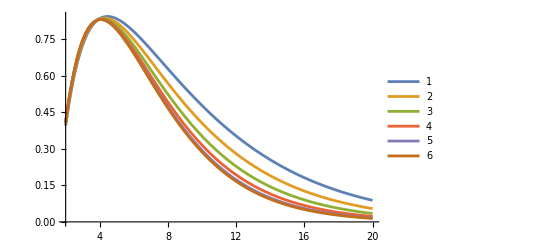

```mathematica
Plot[D[%6,z]/.Table[{z->i/100},{i,45,50}]//Evaluate,{Δ[0],2,20},PlotLegends->Automatic]
```

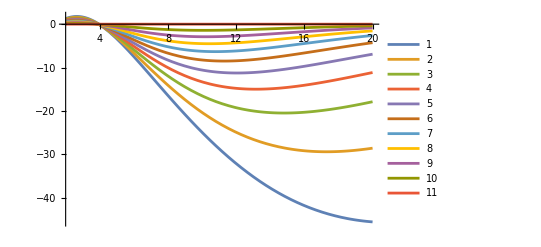

```mathematica
Plot[D[%6,z,z]/.Table[{z->i/100},{i,40,50}]//Evaluate,{Δ[0],2,20},PlotLegends->Automatic]
```

```mathematica
D[%5,C[0]]
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
crossingEq[8]/.Δσ->1//FullSimplify
```

1-2 z-(1-z)^Δ[0] z^2 C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]-(1-z)^Δ[1] z^2 C[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(-1+z)^2 z^Δ[1] C[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z]-(1-z)^Δ[2] z^2 C[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(-1+z)^2 z^Δ[2] C[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z]-(1-z)^Δ[3] z^2 C[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(-1+z)^2 z^Δ[3] C[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z]-(1-z)^Δ[4] z^2 C[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(-1+z)^2 z^Δ[4] C[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z]-(1-z)^Δ[5] z^2 C[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(-1+z)^2 z^Δ[5] C[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z]-(1-z)^Δ[6] z^2 C[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(-1+z)^2 z^Δ[6] C[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z]-(1-z)^Δ[7] z^2 C[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1-z]+(-1+z)^2 z^Δ[7] C[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],z]-(1-z)^Δ[8] z^2 C[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1-z]+(-1+z)^2 z^Δ[8] C[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],z]

```mathematica
D[crossingEq[8],z]/.z->1/2/.Δσ->1//Simplify
```

1/4 (-8+2^(-Δ[0]) C[0] (4 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (-2+Δ[0])+Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0])+2^(-Δ[1]) C[1] (4 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] (-2+Δ[1])+Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1])+2^(-Δ[2]) C[2] (4 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1/2] (-2+Δ[2])+Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2])+2^(-Δ[3]) C[3] (4 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1/2] (-2+Δ[3])+Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],1/2] Δ[3])+2^(-Δ[4]) C[4] (4 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1/2] (-2+Δ[4])+Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],1/2] Δ[4])+2^(-Δ[5]) C[5] (4 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1/2] (-2+Δ[5])+Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],1/2] Δ[5])+2^(-Δ[6]) C[6] (4 Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1/2] (-2+Δ[6])+Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],1/2] Δ[6])+2^(-Δ[7]) C[7] (4 Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1/2] (-2+Δ[7])+Hypergeometric2F1[1+Δ[7],1+Δ[7],1+2 Δ[7],1/2] Δ[7])+2^(-Δ[8]) C[8] (4 Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1/2] (-2+Δ[8])+Hypergeometric2F1[1+Δ[8],1+Δ[8],1+2 Δ[8],1/2] Δ[8]))

```mathematica
y/.Solve[crossingEq[8]==0/.C[0]->x/.C[1]->y/.Δσ->1/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},y][[1]]
```

1/(-(30 (1-z)^2 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^2-(30 (1-z)^3 z^2 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5)(-(1-z)^2+z^2-x ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)-3/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))-2/7 (-(105 (1-z)^2 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^4-(105 (1-z)^5 z^2 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9)-5/42 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))+1/22 ((6006 (1-z)^2 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z]))/(5 z^6)+(6006 (1-z)^7 z^2 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13))-7/429 ((5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z]))/(7 z^7)-(5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))/(7 (-1+z)^15))-4/715 (-(21879 (1-z)^2 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z]))/(14 z^8)-(21879 (1-z)^9 z^2 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z]))/(14 (-1+z)^17))-1/4862 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-(46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]))/(63 (-1+z)^19)))

```mathematica
Table[y/.Solve[D[crossingEq[8],{z,n}]==0/.z->1/2/.C[0]->x/.C[1]->y/.Δσ->1/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},y][[1]],{n,1,7,2}]
```

{(201732085853+294 x-291037879860 Log[2]-336 x Log[2]-42 x Log[4])/(210 (-43+62 Log[2])),(-3/5 (560 (-1073+1548 Log[2])+560 (-9607+13860 Log[2])-560 (-15679+22620 Log[2])-9 (2240/3 (-131+189 Log[2])+1120/3 (-1073+1548 Log[2]))+3/2 (4480/3 (-131+189 Log[2])+8960/3 (-1073+1548 Log[2])+2240/3 (-9607+13860 Log[2]))+1/16 (-8960 (-1073+1548 Log[2])-8960 (-9607+13860 Log[2])-8960 (-15679+22620 Log[2])))-2/7 (18900 (-445+642 Log[2])+22680 (-13402+19335 Log[2])-1260 (-14161+20430 Log[2])-7560 (-54367+78435 Log[2])-15/2 (10080 (-445+642 Log[2])+1680 (-14161+20430 Log[2]))+15/16 (20160 (-445+642 Log[2])+40320 (-13402+19335 Log[2])+13440 (-14161+20430 Log[2]))+1/32 (-483840 (-13402+19335 Log[2])-40320 (-14161+20430 Log[2])-241920 (-54367+78435 Log[2])))-5/42 (88704/5 (-34997+50490 Log[2])-266112/5 (-37981+54795 Log[2])+133056/5 (-522782+754215 Log[2])-11088/5 (-7611671+10981320 Log[2])-45/8 (29568/5 (-34997+50490 Log[2])+177408/5 (-37981+54795 Log[2]))+9/16 (59136/5 (-34997+50490 Log[2])+1419264/5 (-37981+54795 Log[2])+354816/5 (-522782+754215 Log[2]))+1/64 (-4257792/5 (-37981+54795 Log[2])-4257792/5 (-522782+754215 Log[2])-709632/5 (-7611671+10981320 Log[2])))+1/22 (-504504 (-62307+89890 Log[2])+576576 (-192383+277550 Log[2])-72072 (-7778969+11222680 Log[2])+24024/5 (-131907877+190302840 Log[2])+63/16 (768768/5 (-62307+89890 Log[2])+384384 (-192383+277550 Log[2]))-21/64 (1537536/5 (-62307+89890 Log[2])+3075072 (-192383+277550 Log[2])+1537536/5 (-7778969+11222680 Log[2]))+1/128 (9225216 (-192383+277550 Log[2])+18450432/5 (-7778969+11222680 Log[2])+3075072/5 (-131907877+190302840 Log[2])))-7/429 (3953664/7 (-2359979+3404730 Log[2])-8030880/7 (-4213309+6078520 Log[2])-617760/7 (-252638423+364480200 Log[2])+370656/7 (-391517503+564840360 Log[2])-21/8 (1317888/7 (-2359979+3404730 Log[2])+6589440/7 (-4213309+6078520 Log[2]))+1/256 (-158146560/7 (-4213309+6078520 Log[2])-158146560/7 (-252638423+364480200 Log[2])-31629312/7 (-391517503+564840360 Log[2]))+3/16 (2635776/7 (-2359979+3404730 Log[2])+52715520/7 (-4213309+6078520 Log[2])+2635776/7 (-391517503+564840360 Log[2])))-4/715 (1969110 (-25786503+37202060 Log[2])+4594590 (-156764731+226163700 Log[2])-2494206/7 (-522636731+754005420 Log[2])-218790/7 (-23881370299+34453534500 Log[2])-27/16 (5601024/7 (-25786503+37202060 Log[2])+2800512/7 (-522636731+754005420 Log[2]))+27/256 (11202048/7 (-25786503+37202060 Log[2])+56010240 (-156764731+226163700 Log[2])+22404096/7 (-522636731+754005420 Log[2]))+1/512 (-672122880 (-156764731+226163700 Log[2])-67212288/7 (-522636731+754005420 Log[2])-112020480/7 (-23881370299+34453534500 Log[2])))-1/4862 9 (29560960/21 (-1277351989+1842829380 Log[2])-48036560/21 (-2897341837+4179980700 Log[2])-14780480/21 (-34150325903+49268505825 Log[2])+7390240/21 (-67823014793+97847927100 Log[2])-135/128 (47297536/63 (-1277351989+1842829380 Log[2])+236487680/63 (-2897341837+4179980700 Log[2]))+(-1891901440/21 (-2897341837+4179980700 Log[2])-15135211520/21 (-34150325903+49268505825 Log[2])-1891901440/21 (-67823014793+97847927100 Log[2]))/1024+15/256 (94595072/63 (-1277351989+1842829380 Log[2])+1891901440/63 (-2897341837+4179980700 Log[2])+472975360/63 (-67823014793+97847927100 Log[2])))-x (144 (-7+8 Log[2]+Log[4])-72 (-25+32 Log[2]+2 Log[4])-6 (24 (-2+3 Log[2])+12 (-7+8 Log[2]+Log[4]))+3 (48 (-2+3 Log[2])+96 (-7+8 Log[2]+Log[4])+72 (-29/3+12 Log[2]+Log[4]))+1/4 (-288 (-7+8 Log[2]+Log[4])-864 (-29/3+12 Log[2]+Log[4])-288 (-25+32 Log[2]+2 Log[4]))))/(-360 (-9+13 Log[2])+720 (-52+75 Log[2])+180 (-341+492 Log[2])-60 (-2537+3660 Log[2])-9 (240 (-9+13 Log[2])+120 (-52+75 Log[2]))+9/4 (480 (-9+13 Log[2])+960 (-52+75 Log[2])+240 (-341+492 Log[2]))+1/8 (-2880 (-52+75 Log[2])-2880 (-341+492 Log[2])-480 (-2537+3660 Log[2]))),(-3/5 (89600 (-131+189 Log[2])+44800 (-1073+1548 Log[2])-89600 (-9607+13860 Log[2])+44800 (-15679+22620 Log[2])+112000 (-33479+48300 Log[2])-62720 (-69287+99960 Log[2])-120 (2240/3 (-131+189 Log[2])+1120/3 (-1073+1548 Log[2]))+120 (4480/3 (-131+189 Log[2])+8960/3 (-1073+1548 Log[2])+2240/3 (-9607+13860 Log[2]))-30 (8960 (-1073+1548 Log[2])+8960 (-9607+13860 Log[2])+8960 (-15679+22620 Log[2]))+5/2 (35840 (-9607+13860 Log[2])+143360 (-15679+22620 Log[2])+89600 (-33479+48300 Log[2]))+1/16 (-716800 (-15679+22620 Log[2])-1792000 (-33479+48300 Log[2])-1003520 (-69287+99960 Log[2])))-2/7 (604800 (-445+642 Log[2])-3024000 (-13402+19335 Log[2])+504000 (-14161+20430 Log[2])-604800 (-54367+78435 Log[2])+151200 (-2124607+3065160 Log[2])-30240 (-9853309+14215320 Log[2])-300 (10080 (-445+642 Log[2])+1680 (-14161+20430 Log[2]))+150 (20160 (-445+642 Log[2])+40320 (-13402+19335 Log[2])+13440 (-14161+20430 Log[2]))-25 (483840 (-13402+19335 Log[2])+40320 (-14161+20430 Log[2])+241920 (-54367+78435 Log[2]))+25/16 (1935360 (-13402+19335 Log[2])+3870720 (-54367+78435 Log[2])+161280 (-2124607+3065160 Log[2]))+1/32 (-19353600 (-54367+78435 Log[2])-3225600 (-2124607+3065160 Log[2])-967680 (-9853309+14215320 Log[2])))-5/42 (177408 (-34997+50490 Log[2])+10644480 (-37981+54795 Log[2])-2128896 (-522782+754215 Log[2])-709632 (-7611671+10981320 Log[2])-1862784 (-9074267+13091400 Log[2])+532224 (-39062143+56354760 Log[2])-450 (29568/5 (-34997+50490 Log[2])+177408/5 (-37981+54795 Log[2]))+150 (59136/5 (-34997+50490 Log[2])+1419264/5 (-37981+54795 Log[2])+354816/5 (-522782+754215 Log[2]))-75/4 (4257792/5 (-37981+54795 Log[2])+4257792/5 (-522782+754215 Log[2])+709632/5 (-7611671+10981320 Log[2]))+1/64 (-11354112 (-7611671+10981320 Log[2])-119218176 (-9074267+13091400 Log[2])-17031168 (-39062143+56354760 Log[2]))+15/16 (17031168/5 (-522782+754215 Log[2])+11354112/5 (-7611671+10981320 Log[2])+4257792/5 (-39062143+56354760 Log[2])))+1/22 (-8072064 (-62307+89890 Log[2])-80720640 (-192383+277550 Log[2])+3075072 (-131907877+190302840 Log[2])-4804800 (-234489889+338297400 Log[2])+192192 (-4367447327+6300894600 Log[2])+525 (768768/5 (-62307+89890 Log[2])+384384 (-192383+277550 Log[2]))-525/4 (1537536/5 (-62307+89890 Log[2])+3075072 (-192383+277550 Log[2])+1537536/5 (-7778969+11222680 Log[2]))+105/8 (9225216 (-192383+277550 Log[2])+18450432/5 (-7778969+11222680 Log[2])+3075072/5 (-131907877+190302840 Log[2]))-35/64 (73801728/5 (-7778969+11222680 Log[2])+49201152/5 (-131907877+190302840 Log[2])+12300288 (-234489889+338297400 Log[2]))+1/128 (49201152 (-131907877+190302840 Log[2])+246005760 (-234489889+338297400 Log[2])+24600576 (-4367447327+6300894600 Log[2])))-7/429 (19768320 (-2359979+3404730 Log[2])+98841600 (-4213309+6078520 Log[2])-642470400/7 (-252638423+364480200 Log[2])+39536640/7 (-391517503+564840360 Log[2])+123552000/7 (-3056780813+4410002520 Log[2])-9884160/7 (-26747192377+38588041800 Log[2])-525 (1317888/7 (-2359979+3404730 Log[2])+6589440/7 (-4213309+6078520 Log[2]))+105 (2635776/7 (-2359979+3404730 Log[2])+52715520/7 (-4213309+6078520 Log[2])+2635776/7 (-391517503+564840360 Log[2]))-35/4 (158146560/7 (-4213309+6078520 Log[2])+158146560/7 (-252638423+364480200 Log[2])+31629312/7 (-391517503+564840360 Log[2]))+5/16 (2530344960/7 (-252638423+364480200 Log[2])+126517248/7 (-391517503+564840360 Log[2])+527155200/7 (-3056780813+4410002520 Log[2]))+1/256 (-12651724800/7 (-252638423+364480200 Log[2])-10543104000/7 (-3056780813+4410002520 Log[2])-2530344960/7 (-26747192377+38588041800 Log[2])))-4/715 (126023040 (-25786503+37202060 Log[2])+1102701600 (-156764731+226163700 Log[2])+63011520/7 (-522636731+754005420 Log[2])+1050192000 (-2244845926+3238628085 Log[2])-332560800/7 (-23881370299+34453534500 Log[2])-42007680/7 (-262456014607+378643990725 Log[2])-945/2 (5601024/7 (-25786503+37202060 Log[2])+2800512/7 (-522636731+754005420 Log[2]))+315/4 (11202048/7 (-25786503+37202060 Log[2])+56010240 (-156764731+226163700 Log[2])+22404096/7 (-522636731+754005420 Log[2]))-45/8 (672122880 (-156764731+226163700 Log[2])+67212288/7 (-522636731+754005420 Log[2])+112020480/7 (-23881370299+34453534500 Log[2]))+45/256 (2688491520 (-156764731+226163700 Log[2])+53769830400/7 (-2244845926+3238628085 Log[2])+1792327680/7 (-23881370299+34453534500 Log[2]))+1/512 (-1075396608000/7 (-2244845926+3238628085 Log[2])-8961638400/7 (-23881370299+34453534500 Log[2])-21507932160/7 (-262456014607+378643990725 Log[2])))-1/4862 9 (1005072640/7 (-1277351989+1842829380 Log[2])-739024000/7 (-2897341837+4179980700 Log[2])-30743398400/21 (-34150325903+49268505825 Log[2])+2956096000/21 (-67823014793+97847927100 Log[2])-413853440/3 (-448277236159+646727345550 Log[2])+2364876800/21 (-852325236536+1229645391975 Log[2])-1575/4 (47297536/63 (-1277351989+1842829380 Log[2])+236487680/63 (-2897341837+4179980700 Log[2]))+225/4 (94595072/63 (-1277351989+1842829380 Log[2])+1891901440/63 (-2897341837+4179980700 Log[2])+472975360/63 (-67823014793+97847927100 Log[2]))-225/64 (1891901440/21 (-2897341837+4179980700 Log[2])+15135211520/21 (-34150325903+49268505825 Log[2])+1891901440/21 (-67823014793+97847927100 Log[2]))+(-1210816921600/21 (-34150325903+49268505825 Log[2])-423785922560/3 (-448277236159+646727345550 Log[2])-605408460800/21 (-852325236536+1229645391975 Log[2]))/1024+25/256 (242163384320/21 (-34150325903+49268505825 Log[2])+7567605760/21 (-67823014793+97847927100 Log[2])+30270423040/21 (-852325236536+1229645391975 Log[2])))-x (-5760 (-7+8 Log[2]+Log[4])+11520 (-25+32 Log[2]+2 Log[4])-576 (-541+720 Log[2]+30 Log[4])-20 (288 (-7+8 Log[2]+Log[4])+864 (-29/3+12 Log[2]+Log[4])+288 (-25+32 Log[2]+2 Log[4]))+5 (3456 (-29/3+12 Log[2]+Log[4])+4608 (-25+32 Log[2]+2 Log[4])+192 (-457+600 Log[2]+30 Log[4]))+1/4 (-23040 (-25+32 Log[2]+2 Log[4])-3840 (-457+600 Log[2]+30 Log[4])-2304 (-541+720 Log[2]+30 Log[4]))))/(28800 (-9+13 Log[2])-28800 (-52+75 Log[2])-28800 (-341+492 Log[2])+36000 (-707+1020 Log[2])+9600 (-2537+3660 Log[2])-1440 (-32897+47460 Log[2])+60 (480 (-9+13 Log[2])+960 (-52+75 Log[2])+240 (-341+492 Log[2]))-30 (2880 (-52+75 Log[2])+2880 (-341+492 Log[2])+480 (-2537+3660 Log[2]))+15/4 (11520 (-341+492 Log[2])+28800 (-707+1020 Log[2])+7680 (-2537+3660 Log[2]))+1/8 (-576000 (-707+1020 Log[2])-38400 (-2537+3660 Log[2])-11520 (-32897+47460 Log[2]))),(-3/5 (-7526400 (-1073+1548 Log[2])+7526400 (-9607+13860 Log[2])+7526400 (-15679+22620 Log[2])-37632000 (-33479+48300 Log[2])+10536960 (-69287+99960 Log[2])-7526400 (-389521+561960 Log[2])+1505280 (-2024461+2920680 Log[2])-840 (8960 (-1073+1548 Log[2])+8960 (-9607+13860 Log[2])+8960 (-15679+22620 Log[2]))+420 (35840 (-9607+13860 Log[2])+143360 (-15679+22620 Log[2])+89600 (-33479+48300 Log[2]))-63 (716800 (-15679+22620 Log[2])+1792000 (-33479+48300 Log[2])+1003520 (-69287+99960 Log[2]))+1/16 (-168591360 (-69287+99960 Log[2])-120422400 (-389521+561960 Log[2])-24084480 (-2024461+2920680 Log[2]))+7/2 (10752000 (-33479+48300 Log[2])+24084480 (-69287+99960 Log[2])+860160 (-2024461+2920680 Log[2])))-2/7 (50803200 (-445+642 Log[2])+101606400 (-13402+19335 Log[2])-50803200 (-14161+20430 Log[2])+508032000 (-54367+78435 Log[2])+228614400 (-1622713+2341080 Log[2])-42336000 (-2124607+3065160 Log[2])-5080320 (-9853309+14215320 Log[2])-1209600 (-229972843+331780680 Log[2])+2520 (20160 (-445+642 Log[2])+40320 (-13402+19335 Log[2])+13440 (-14161+20430 Log[2]))-2100 (483840 (-13402+19335 Log[2])+40320 (-14161+20430 Log[2])+241920 (-54367+78435 Log[2]))+525 (1935360 (-13402+19335 Log[2])+3870720 (-54367+78435 Log[2])+161280 (-2124607+3065160 Log[2]))-105/2 (19353600 (-54367+78435 Log[2])+3225600 (-2124607+3065160 Log[2])+967680 (-9853309+14215320 Log[2]))+35/16 (174182400 (-1622713+2341080 Log[2])+19353600 (-2124607+3065160 Log[2])+23224320 (-9853309+14215320 Log[2]))+1/32 (-4877107200 (-1622713+2341080 Log[2])-162570240 (-9853309+14215320 Log[2])-38707200 (-229972843+331780680 Log[2])))-5/42 (59609088 (-34997+50490 Log[2])-715309056 (-37981+54795 Log[2])-357654528 (-522782+754215 Log[2])+298045440 (-7611671+10981320 Log[2])-1251790848 (-9074267+13091400 Log[2])-89413632 (-39062143+56354760 Log[2])-421521408 (-49668293+71656200 Log[2])+29804544 (-1089339989+1571585400 Log[2])-5040 (29568/5 (-34997+50490 Log[2])+177408/5 (-37981+54795 Log[2]))+7560 (59136/5 (-34997+50490 Log[2])+1419264/5 (-37981+54795 Log[2])+354816/5 (-522782+754215 Log[2]))-3150 (4257792/5 (-37981+54795 Log[2])+4257792/5 (-522782+754215 Log[2])+709632/5 (-7611671+10981320 Log[2]))+525 (17031168/5 (-522782+754215 Log[2])+11354112/5 (-7611671+10981320 Log[2])+4257792/5 (-39062143+56354760 Log[2]))-315/8 (11354112 (-7611671+10981320 Log[2])+119218176 (-9074267+13091400 Log[2])+17031168 (-39062143+56354760 Log[2]))+1/64 (-20028653568 (-9074267+13091400 Log[2])-26977370112 (-49668293+71656200 Log[2])-953745408 (-1089339989+1571585400 Log[2]))+21/16 (2861236224 (-9074267+13091400 Log[2])+102187008 (-39062143+56354760 Log[2])+34062336 (-1089339989+1571585400 Log[2])))-7/429 (1897758720 (-2359979+3404730 Log[2])+16605388800 (-4213309+6078520 Log[2])+16605388800 (-252638423+364480200 Log[2])-3321077760 (-391517503+564840360 Log[2])+3953664000 (-3056780813+4410002520 Log[2])+10674892800 (-12991438543+18742683960 Log[2])-3083857920 (-26747192377+38588041800 Log[2])-553512960 (-135607107431+195639701400 Log[2])-35280 (1317888/7 (-2359979+3404730 Log[2])+6589440/7 (-4213309+6078520 Log[2]))+17640 (2635776/7 (-2359979+3404730 Log[2])+52715520/7 (-4213309+6078520 Log[2])+2635776/7 (-391517503+564840360 Log[2]))-3675 (158146560/7 (-4213309+6078520 Log[2])+158146560/7 (-252638423+364480200 Log[2])+31629312/7 (-391517503+564840360 Log[2]))+735/2 (2530344960/7 (-252638423+364480200 Log[2])+126517248/7 (-391517503+564840360 Log[2])+527155200/7 (-3056780813+4410002520 Log[2]))-147/8 (12651724800/7 (-252638423+364480200 Log[2])+10543104000/7 (-3056780813+4410002520 Log[2])+2530344960/7 (-26747192377+38588041800 Log[2]))+7/16 (63258624000/7 (-3056780813+4410002520 Log[2])+227731046400/7 (-12991438543+18742683960 Log[2])+60728279040/7 (-26747192377+38588041800 Log[2]))+1/256 (-910924185600 (-12991438543+18742683960 Log[2])-60728279040 (-26747192377+38588041800 Log[2])-141699317760 (-135607107431+195639701400 Log[2])))+1/22 (-1743565824 (-62307+89890 Log[2])+2712213504 (-7778969+11222680 Log[2])-904071168 (-131907877+190302840 Log[2])-1614412800 (-1419168197+2047426920 Log[2])+258306048 (-4367447327+6300894600 Log[2])+9225216 (-144655300729+208693485000 Log[2])+17640 (768768/5 (-62307+89890 Log[2])+384384 (-192383+277550 Log[2]))-13230 (1537536/5 (-62307+89890 Log[2])+3075072 (-192383+277550 Log[2])+1537536/5 (-7778969+11222680 Log[2]))+3675 (9225216 (-192383+277550 Log[2])+18450432/5 (-7778969+11222680 Log[2])+3075072/5 (-131907877+190302840 Log[2]))-3675/8 (73801728/5 (-7778969+11222680 Log[2])+49201152/5 (-131907877+190302840 Log[2])+12300288 (-234489889+338297400 Log[2]))+441/16 (49201152 (-131907877+190302840 Log[2])+246005760 (-234489889+338297400 Log[2])+24600576 (-4367447327+6300894600 Log[2]))-49/64 (1476034560 (-234489889+338297400 Log[2])+2952069120 (-1419168197+2047426920 Log[2])+590413824 (-4367447327+6300894600 Log[2]))+1/128 (82657935360 (-1419168197+2047426920 Log[2])+4132896768 (-4367447327+6300894600 Log[2])+1180827648 (-144655300729+208693485000 Log[2])))-4/715 (7561382400 (-25786503+37202060 Log[2])-370507737600 (-156764731+226163700 Log[2])+10585935360 (-522636731+754005420 Log[2])+529296768000 (-2244845926+3238628085 Log[2])+2520460800 (-23881370299+34453534500 Log[2])+57634536960 (-129768307261+187216093350 Log[2])-17643225600 (-217059018791+313149969990 Log[2])-19155502080 (-262456014607+378643990725 Log[2])-52920 (5601024/7 (-25786503+37202060 Log[2])+2800512/7 (-522636731+754005420 Log[2]))+19845 (11202048/7 (-25786503+37202060 Log[2])+56010240 (-156764731+226163700 Log[2])+22404096/7 (-522636731+754005420 Log[2]))-6615/2 (672122880 (-156764731+226163700 Log[2])+67212288/7 (-522636731+754005420 Log[2])+112020480/7 (-23881370299+34453534500 Log[2]))+2205/8 (2688491520 (-156764731+226163700 Log[2])+53769830400/7 (-2244845926+3238628085 Log[2])+1792327680/7 (-23881370299+34453534500 Log[2]))+1/512 (-8431109406720 (-129768307261+187216093350 Log[2])-9033331507200 (-217059018791+313149969990 Log[2])-516190371840 (-262456014607+378643990725 Log[2]))-189/16 (1075396608000/7 (-2244845926+3238628085 Log[2])+8961638400/7 (-23881370299+34453534500 Log[2])+21507932160/7 (-262456014607+378643990725 Log[2]))+63/256 (6452379648000/7 (-2244845926+3238628085 Log[2])+301111050240 (-129768307261+187216093350 Log[2])+516190371840/7 (-262456014607+378643990725 Log[2])))-1/4862 9 (8513556480 (-1277351989+1842829380 Log[2])+99324825600 (-2897341837+4179980700 Log[2])-141892608000 (-34150325903+49268505825 Log[2])-28378521600 (-67823014793+97847927100 Log[2])-602570608640 (-448277236159+646727345550 Log[2])+463515852800 (-795104562211+1147093408890 Log[2])+94595072000 (-852325236536+1229645391975 Log[2])-182095513600 (-992324782927+1431622043280 Log[2])-66150 (47297536/63 (-1277351989+1842829380 Log[2])+236487680/63 (-2897341837+4179980700 Log[2]))+19845 (94595072/63 (-1277351989+1842829380 Log[2])+1891901440/63 (-2897341837+4179980700 Log[2])+472975360/63 (-67823014793+97847927100 Log[2]))-11025/4 (1891901440/21 (-2897341837+4179980700 Log[2])+15135211520/21 (-34150325903+49268505825 Log[2])+1891901440/21 (-67823014793+97847927100 Log[2]))+1575/8 (242163384320/21 (-34150325903+49268505825 Log[2])+7567605760/21 (-67823014793+97847927100 Log[2])+30270423040/21 (-852325236536+1229645391975 Log[2]))-945/128 (1210816921600/21 (-34150325903+49268505825 Log[2])+423785922560/3 (-448277236159+646727345550 Log[2])+605408460800/21 (-852325236536+1229645391975 Log[2]))+35/256 (3390287380480 (-448277236159+646727345550 Log[2])+4237859225600 (-795104562211+1147093408890 Log[2])+1210816921600/7 (-852325236536+1229645391975 Log[2]))+(-23732011663360 (-448277236159+646727345550 Log[2])-118660058316800 (-795104562211+1147093408890 Log[2])-186465805926400 (-992324782927+1431622043280 Log[2]))/1024)-x (-967680 (-25+32 Log[2]+2 Log[4])+193536 (-541+720 Log[2]+30 Log[4])-9216 (-9901+13440 Log[2]+420 Log[4])-42 (23040 (-25+32 Log[2]+2 Log[4])+3840 (-457+600 Log[2]+30 Log[4])+2304 (-541+720 Log[2]+30 Log[4]))+7 (69120 (-291+392 Log[2]+14 Log[4])+23040 (-457+600 Log[2]+30 Log[4])+55296 (-541+720 Log[2]+30 Log[4]))+1/4 (-1935360 (-291+392 Log[2]+14 Log[4])-387072 (-541+720 Log[2]+30 Log[4])-36864 (-9901+13440 Log[2]+420 Log[4]))))/(2419200 (-341+492 Log[2])-12096000 (-707+1020 Log[2])-806400 (-2537+3660 Log[2])+4032000 (-3377+4872 Log[2])+483840 (-32897+47460 Log[2])-69120 (-316159+456120 Log[2])+210 (11520 (-341+492 Log[2])+28800 (-707+1020 Log[2])+7680 (-2537+3660 Log[2]))-63 (576000 (-707+1020 Log[2])+38400 (-2537+3660 Log[2])+11520 (-32897+47460 Log[2]))+21/4 (3456000 (-707+1020 Log[2])+2304000 (-3377+4872 Log[2])+276480 (-32897+47460 Log[2]))+1/8 (-64512000 (-3377+4872 Log[2])-1935360 (-32897+47460 Log[2])-552960 (-316159+456120 Log[2])))}

```mathematica
N[Table[D[crossingEq[4],{Table[C[i],{i,0,4}]},{z,n}]/n!,{n,1,9,2}]/.z->1/2/.genBos/.Δσ->1,40]
```

{{0.41116916640328143496607271250940591547,0.8306080936527724857928350502260497443593,0.691198210712458438845802154126333521148,0.4668411864067073885904428164946355641498,0.2864267154533866668320062148560155846372},{-2.168517335018998816217134639939802140992,0.6095223597445851856318279664997072241202,11.90257994841662765054007023012446601832,20.70713550687397622466649991455753851885,23.53077000296426330651827743221567682131},{0.9259306599240047351314614402407914360318,-12.04729109298851333724260644846111888096,18.5593632446265931742619092911583121526,189.3734053597940680187196095904051059082,460.1265135733743352552228601861872981831},{1.875151211124590369097274332391737172699,-17.56616496801742503822592478919882189218,-78.93305773499991632206391795814416496266,563.4441175680009893678982015014443343703,3584.214612699394980602466788197791383458},{3.843461987355504333531954472424091547937,-20.1812427957736750572956647549375607429,-364.9146609688004488877751657716123182436,343.2137990584628222083506409266731502247,14821.92595493451190414312107758588362649}}

```mathematica
Inverse[%226].N[Table[D[crossingEq[4],{z,n}]/n!,{n,1,9,2}]/.C[i_]->0/.z->1/2/.Δσ->1,40]
```

{-2.04112973173135060682594906795195307058,-1.16600460159775231566591877982183637624,-0.260592327544722389493424844061322910524,-0.0217201466643381720968931615669030688491,-0.00697114022490055018535343424056546828561}

```mathematica
getAvCs[4,Table[2+2i,{i,0,10}],4/10,49/100,1,50][[;;,2]]//Total
```

0.0290334447310269380651990365927632316233934

```mathematica
getAvCs[8,Table[2+2i,{i,0,10}],4/10,49/100,1,50][[;;,2]]//Total
```

0.00034031467621348019463188583865

```mathematica
getAvCs[3,Table[2+2i,{i,0,10}],4/10,49/100,1,50]
```

{{2.5370698876138491293632952260357796177539110116,0.0340885650725286487668396622109178919364645006},{0.8017201127673063615726565314837174505256049845,0.0227127456085548029761336310281828305772156262},{0.4209034681992706746978273823775624565523500277,0.00703320077773030944968400055327086456907694412}}

```mathematica
getAvCs[8,Table[2+2i,{i,0,10}],4/10,49/100,1,50]
```

{{1.9992675480453827520247045993086,0.00010691531495669344077520986888},{1.20063318516607794415746028508305,0.000091626427160493569356386952952},{0.237610536996001404048703308432236,0.00006821250117768547147226669026},{0.0329555820842461118507380021538353,0.0000427317522882472959151761934662},{0.0035263230613343497780178566387551,0.00002117302072081977794654668484908},{0.00044890969215781432663494601934756,7.667862791255903400333574573991×10^-6},{0.0000124264932199317282167230977013724,1.7876792585736044973503108122955×10^-6},{7.21426760995098467600985901890203×10^-6,2.00117859711131268615562851382×10^-7}}

```mathematica
RandomReal[1,{10},WorkingPrecision->40]
```

{0.5772036206473232569084723368777484368343,0.1613634674365669053199483884026153304093,0.7435048994960268160052614170215248905622,0.9015830879301510864364821591865415735641,0.8599045632576226782316043896910305793998,0.7868784212608606100568783020734587505828,0.5738460641218260068252601513417921379998,0.4527938022666479337812837624737750945103,0.2666288934550874837929809649572405523362,0.230839745571118086919181840237784207285}

```mathematica
Table[2+2i,{i,0,10}]+RandomReal[1,{11},WorkingPrecision->50]
```

{2.5344125013928865271793009007725802961117699949126,4.11283522987988405750256580403136412775426413931572,6.8603529924982204887521524894963650383040309818862,8.36787826132748790359010910667850034322956886722506,10.4701987871545820237720780898021647008092678679503,12.7029063588607439127408922896212122432500571396616,14.6931745602749374056252455549580431693038160164074,16.7032739709740734419849618859075637972472163222635,18.05421285511602085505885046361213664919515342848154,20.6023985717300183490628262191091793358037960835513,22.5362202748923123500793913479404981307996370968306}

```mathematica
getAvCs[8,%22,4/10,49/100,1,50][[;;,2]]//Total
```

0.002039990703238478534789846468

```mathematica
getAvCs[4,%22,4/10,49/100,1,50][[;;,2]]//Total
```

0.01554186082094051477061923557663402237763

```mathematica
getAvCs[3,Table[2+2i,{i,0,10}],4/10,49/100,1,50]
```

{{2.5370698876138491293632952260357796177539110116,0.0340885650725286487668396622109178919364645006},{0.8017201127673063615726565314837174505256049845,0.0227127456085548029761336310281828305772156262},{0.4209034681992706746978273823775624565523500277,0.00703320077773030944968400055327086456907694412}}

```mathematica
{2.05379,4.05476,6.05321,8.05334}//Rationalize
```

{205379/100000,101369/25000,605321/100000,402667/50000}

```mathematica
getAvCs[4,{205379/100000,101369/25000,605321/100000,402667/50000},4/10,49/100,1,50]
```

Part::partw: Part 5 of {205379/100000,101369/25000,605321/100000,402667/50000} does not exist.

Part::partw: Part 5 of {2.05379,4.05476,6.05321,8.05334} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
getAvCs[3,{205379/100000,101369/25000,605321/100000,402667/50000},4/10,49/100,1,50]
```

{{2.4065030558942979813079446406925397117642927628,0.0289927474302185527038477419826996873876290564},{0.81125401075355343785591711441115383941986219565,0.0207413790184707397515700468306480204854206991},{0.39491409903241731484586128141374807590803995811,0.0066060082810470262828229367901399397635922284}}

```mathematica
getAvCs[4,{205379/100000,101369/25000,605321/100000,402667/50000},4/10,49/100,1,50]
```

```mathematica
Inverse[%223].%221
```

{-1.84979615198471974775814559501916357739,-1.31977338756098145233823779402457965695,-0.167687161253093836427244114124938452568,-0.0584809902256182023081766403941511757295}

```mathematica
D[crossingEq[8],{Table[C[i],{i,0,3}]},{z,6}]/.z->1/2/.Δσ->1//Simplify
```

{0,0,0,0}

```mathematica
N[Table[D[crossingEq[8],{z,n}]/n!/.z->1/2,{n,1,7,2}]/.genBos/.Δσ->1,40]
```

{-3.219711745176083538102055228246851277629×10^-10,-1.402340633318452595021971404060132676072×10^-7,-0.00001689008000386646509372203697584584669166,-0.0009055148648034427499896894959568214848251}

```mathematica
N[Table[D[crossingEq[16],{z,n}]/n!/.z->1/2,{n,1,7,2}]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1,40]
```

{-9.39652136706620166542361325681783500182×10^-10,-3.726293565485553336320109754158720070517×10^-7,-0.00004078059584108944205648195195006619838393,-0.00198628381841538272429271062881365542997}

```mathematica
N[Table[D[crossingEq[5],{Table[C[i],{i,0,5}]},{z,n}]/n!,{n,1,11,2}]/.z->1/2/.Δσ->1/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},40]
```

{{0.41116916640328143496607271250940591547,0.7462441585017244839482540877915833795698,0.8306080936527724857928350502260497443593,0.7885957465392739650704214536770785660633,0.691198210712458438845802154126333521148,0.5773007033879818938434744629211195785844},{-2.168517335018998816217134639939802140992,-2.638800126424911216285097995485160574404,0.6095223597445851856318279664997072241202,6.030918578147632549371862050032561376986,11.90257994841662765054007023012446601832,17.00480265344722955323912954688366391095},{0.9259306599240047351314614402407914360318,-2.999360910259360757252705567493156135708,-12.04729109298851333724260644846111888096,-10.82372398902296354594667044098599446807,18.5593632446265931742619092911583121526,85.77891414846081224180817263161628924157},{1.875151211124590369097274332391737172699,-0.05979954499059231174579089789696560948669,-17.56616496801742503822592478919882189218,-58.17234790340879996021570998695139099773,-78.93305773499991632206391795814416496266,56.16365089334931320936779263555565060761},{3.843461987355504333531954472424091547937,4.844711537558366955410295230048106628766,-20.1812427957736750572956647549375607429,-130.2912083517356194416572533276729545326,-364.9146609688004488877751657716123182436,-510.4136658287030495027645298179619412831},{8.7244973000713679834784672403457168411,17.54998285581424812905051404223413827975,-14.87410988419740092107888472770373495658,-256.3569775507431698328067576507294876188,-1053.095579965962153588517007492891596197,-2579.595150048022474588036976683598110767}}

```mathematica
N[Table[D[crossingEq[5],{z,n}]/n!,{n,1,11,2}]/.C[i_]->0/.z->1/2/.Δσ->1/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},40]
```

{-2.,0,0,0,0,0}

```mathematica
Inverse[%].%254
```

{636.978158759518997784099321341124932696,-612.393344445957021685297466981766114622,320.650428151495272543657279807233346457,-112.892388299756492314078108848000141288,25.3180610477850392253902076196389344796,-2.97765907260955107622244780307177329753}

```mathematica
D[crossingEq[8],{z,n}]==0/.z->1/2
```

```mathematica
Table[y/.Solve[/.C[0]->x/.C[1]->y/.Δσ->1/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450},y][[1]],{n,1,7,2}]
```

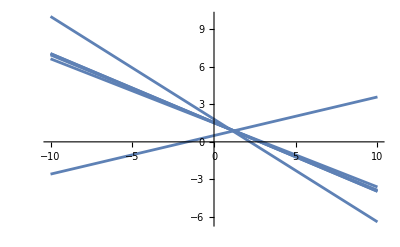

```mathematica
Plot[Join[%201[[;;-2]],%41],{x,-10,10},WorkingPrecision->50]
```

```mathematica
%26/.{{z->49/100},{z->3/10},{z->4/10}};
```

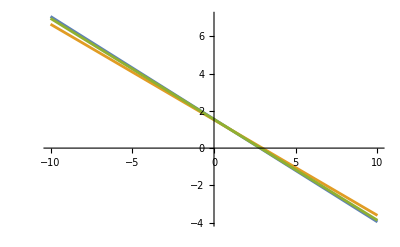

```mathematica
Plot[%,{x,-10,10},WorkingPrecision->50]
```

```mathematica
Table[D[%26,{z,n}]/.z->1/2,{n,1,7,2}]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3 (1-(3 Log[2])/2)+3 (-1+(3 Log[2])/2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 280/3 (131/8-(189 Log[2])/8)+280/3 (-131/8+(189 Log[2])/8).

General::stop: Further output of N::meprec will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate}

Plot::precw: The precision of the argument function ((1-z)^2-z^2-7006.4248804136823702107483188282 ((6 (1-z)^2 (-2 z-2 Log[Plus[«2»]]+z Log[Plus[«2»]]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)+«9»+1.3104838094873978677759171338122 (-(21879 (1-z)^2 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[Plus[«2»]]-7207200 z Log[Plus[«2»]]+«7»))/(14 z^8)-(21879 (1-z)^9 z^2 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+«7»))/(14 (-1+z)^17))) is less than WorkingPrecision (50.).

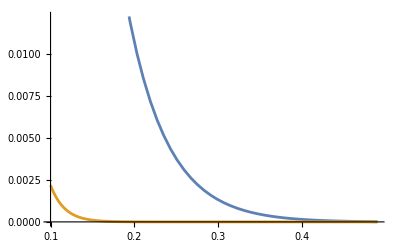

```mathematica
Plot[%13,{z,1/10,49/100},WorkingPrecision->50]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

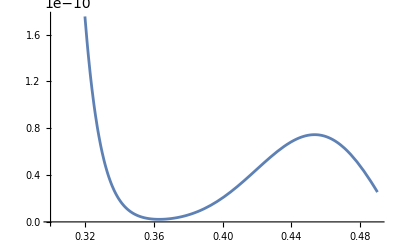

```mathematica
Plot[crossingEq[7]/.Δσ->1/.Δ[i_]->2+i/.C[i_]->%5[[i+1,1]],{z,3/10,49/100},WorkingPrecision->50]
```

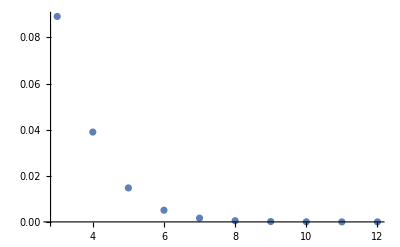

```mathematica
ListPlot[%]
```

```mathematica
Table[{Δ[n]/.genBos/.Δσ->1,N[crossingEq[n]/.genBos/.Δσ->1/.z->4/10,30]//Log},{n,1,5}]
```

{{4,-3.82462579458152155537637536994},{6,-5.99413465664712815987957410161},{8,-8.37553630922916957336512076483},{10,-10.87831868834559598842434882932},{12,-13.46005023071774524151959619902}}

```mathematica
Table[{Δ[n]/.genFer/.Δσ->1,N[crossingEq[n]/.genFer/.Δσ->1/.z->4/10,30]//Log},{n,1,5}]
```

{{5,-4.87368325223923190156018716361},{7,-7.16570718432498670635183344867},{9,-9.61505557101024404128687791887},{11,-12.16104459784088789249972289737},{13,-14.77290124533651648786669794174}}

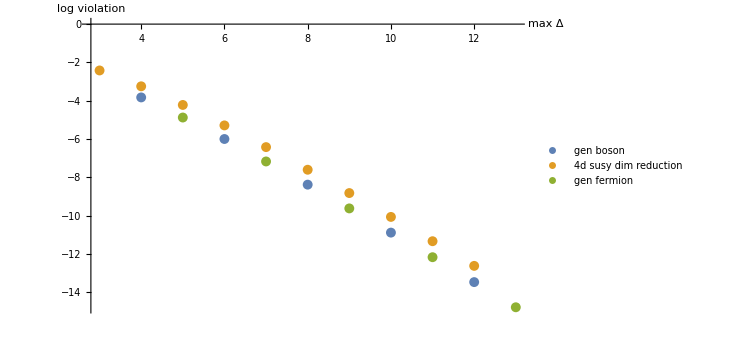

```mathematica
ListPlot[{%842,%841,%846},AxesLabel->{"max Δ","log violation"},PlotLegends->{"gen boson","4d susy dim reduction","gen fermion"}]
```

```mathematica
N[crossingEq[5]/.genBos/.Δσ->1/.z->4/10,30]
```

1.42683731522298415861622322689×10^-6

```mathematica
D[crossingEq[5],C[0]]/.Δσ->1//Simplify
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
getLegendreCoeffs[f_,nMax_]:=Module[{},
coefficients=Table[(2 n+1)/2 NIntegrate[f[z] LegendreP[n,x]/.z->1/4(x+1),{x,-1,1},WorkingPrecision->40],{n,0,nMax,2}]]
```

{-0.04330973667852960007626486663648571119277,-0.0004348361801956522565785969370843811070858,0.04990346080498423047743333444998765936575,-0.002516275037030905920713052759616715276144,-0.005163083264849256670213915260091050799578,0.002184844835566117929441280297826127007475,-0.0009876096824465192375090032380579237724616,0.0004933927211391595311266306122398518664524,-0.0002662468763994812797051063732539037086451,0.0001534916112337962420647316899716400874924,-0.00009334243724769262339413032502622561037151}

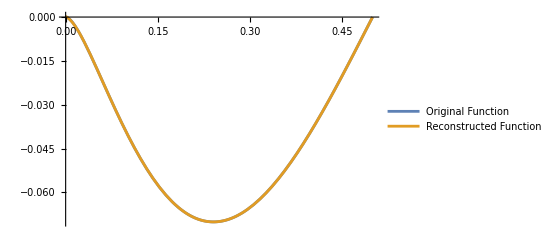

```mathematica
(*Define your function*)f[z_]:=-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.Δ[0]->2

(*Compute the expansion coefficients*)
nMax=10; (*Maximum degree of Legendre polynomial/2*)
coefficients=Table[(2 n+1)/2 NIntegrate[f[z] LegendreP[n,x]/.z->1/4(x+1),{x,-1,1},WorkingPrecision->40],{n,0,nMax}]

(*Reconstruct the function*)
reconstructedFunction[x_]:=Sum[coefficients[[n+1]] LegendreP[n,x],{n,0,nMax}]

(*Plot original function and reconstructed function*)
Plot[{f[z],reconstructedFunction[(4 z-1)]},{z,0,1/2},PlotLegends->{"Original Function","Reconstructed Function"},WorkingPrecision->40]
```

```mathematica
f[z_]:=-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.Δ[0]->4
```

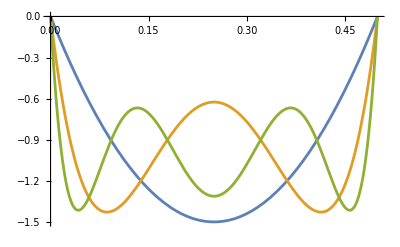

```mathematica
Plot[ LegendreP[n,4 z-1]-1/.{{n->2},{n->4},{n->6}}//Evaluate,{z,0,1/2}]
```

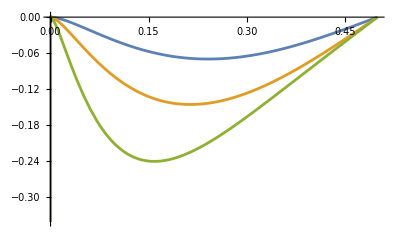

```mathematica
Plot[-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.{{Δ[0]->2},{Δ[0]->3},{Δ[0]->4}}//Evaluate,{z,0,1/2}]
```

```mathematica
Table[f[z_]:=-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z];
getLegendreCoeffs[f,nMax],{Δ[0],2,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.999886614003107366081907965260344311899363818397369344251626850327292542517057935213200018}. NIntegrate obtained -0.000308814381565898555464868011384075636631274503856936331784824032838937900726626410470391999 and 2.05680965718252639222704806250215782173106868876700793538978526555980985448205853151804252×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.999886614003107366081907965260344311899363818397369344251626850327292542517057935213200018}. NIntegrate obtained 0.000226418357444976974603626981881827688503846540725092405271920124561143022430478108457430387 and 2.26076096755124877981706815559925408842825842881852370214178036020789545825476903825383951×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.999886614003107366081907965260344311899363818397369344251626850327292542517057935213200018}. NIntegrate obtained -0.000167219675480018280659182169969154072850606503939840950439973835241015129714211728470832449 and 2.58433575809711493446135313466108966482578700415416578950773685080576856706750821623486277×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{-0.04330973667852960007626486663648571119277,-0.0004348361801956522565785969370843811070858,0.04990346080498423047743333444998765936575,-0.002516275037030905920713052759616715276144,-0.005163083264849256670213915260091050799578,0.002184844835566117929441280297826127007475,-0.0009876096824465192375090032380579237724616,0.0004933927211391595311266306122398518664524,-0.0002662468763994812797051063732539037086451,0.0001534916112337962420647316899716400874924,-0.00009334243724769262339413032502622561037151,0.00005934479944847171917836357077312974388178,-0.00003916327392322678633257403696853514999425,0.00002667749416585289866617836970137748904566,-0.0000186744672511233727921149828347806569894,0.00001338539575694286169428028983500705872659,-9.795387692559183768000736946364977165834×10^-6,7.30075435431882795179965891393325559547×10^-6,-5.530835494803095290435257504401633251886×10^-6,4.25156829916327401371254894052531728763×10^-6,-3.311401248605601376552095298747967481305×10^-6},{-0.09166712785851131498057800550286252689552,0.01292057726997995714206576056345598397238,0.1000369622978457304206824420319567812986,-0.02003383945430445717257676651657025333086,-0.003774401282944063118104793869015839819202,0.004297332924591774756725051800826341155024,-0.002828550864316731338696004015187579799954,0.001669209970886430463832892073158487240354,-0.0009967765975299803979545693660795621071965,0.0006131065300757189544027450195453553501734,-0.000389943272819103450319947828561019500615,0.0002560649167673867589262186754713921685472,-0.0001731219445888725155865635016436135090237,0.0001201421159034106404686715949747904701602,-0.00008533974368948826734560441119661928202513,0.00006189082073601908151082614848998831851771,-0.000045726063621526538208161790820422230711,0.00003435060996958144891558068337921740501791,-0.0000261950571727195376665841579191309550923,0.00002024858879572941223992485023464676870561,-0.00001584593172351356205755983990379190582218},{-0.144884721717479268368077638019002548111,0.06345107011168270636041513116524237775352,0.135575347945540945579529256531084698723,-0.07281127724545527286541070057768034063748,0.01995187089508556111572730529817340970947,0.001156934985093944359639742276364837954242,-0.004790217853586637043638582716082779837124,0.004086142350380400224072694686395707046198,-0.002931857517423623666758053181175666067345,0.002013129273628071559522818451799269290212,-0.001377625564317801210797248670934134099075,0.0009526366208471518335224774296583469385434,-0.0006690866424271360734901061928536608702269,0.0004780022252781878966977015239293624003863,-0.0003473209282603145455096822393754336215968,0.0002564814370519234379717571842271683603721,-0.0001922921874729022747197589857684951731024,0.0001462090583077420272521711190801937334041,-0.0001126234650491544620111979397245145117982,0.00008779849818357032885388502405130238798067,-0.00006920606231745904340203777259194256419617},{-0.2331732321122154202616073771938153000746,0.185834865732226118780187487943758318505,0.1544343267950278382317485719622973246222,-0.1775677273223284916830794255566418571087,0.09383465331736675900736306735620310188987,-0.02702837679903243417172693460533646147778,0.001301679678277510865615445754730385552306,0.00578944377936776549923082414575552291288,-0.006463936894891631510121837854774844506207,0.005421743160685321032054424172067337597766,-0.004176051027297140317341873078878532645874,0.003124025913591036764114959126559381493856,-0.002320471505665987973391991376808240967678,0.001728303186309562841753196870805972534895,-0.001296704466239475335622124054166902146874,0.0009820771801641248771917940392780183531049,-0.0007514277154397923285681361781012138568434,0.0005809371114145489939898293954961896094781,-0.0004537133065048178750721728682117720067808,0.0003578290778292786504889818655249521668363,-0.0002848427270043414924969539538236053323771},{-0.4041822752380187457468481160675008459367,0.4652309116646489615101206790591917327394,0.1122601045977015561537254226606632020644,-0.3560949872344375715544193748033707700488,0.2811008692560653739660821687833441390055,-0.1371333888696169478668201176033596716556,0.04836954468344215867836996359523247981901,-0.007735181729705560294812695240379192399123,-0.007056506067534142967985994615424934767082,0.01082716270718706804678844122004746121816,-0.01049967540988904469395590197083215139405,0.008937437099630251833999058522497103966113,-0.007221892656139840855593273078535452563672,0.005709162505468516969220922103376448862408,-0.004477808532705529054240586165069096731153,0.00350948454039714310635621821916832917181,-0.002759124645420301630876505804491042202035,0.002180461404967231315174750190971363594771,-0.001733982257472451289936865262027421396571,0.001388293991885062199503225753676813903851,-0.001119265008516018434349376954797995142471},{-0.7609492578494304206611565298073870661416,1.113091506909433007084517292598132303822,-0.1352790246837464932116542294652740768927,-0.6208370704043564181818045848124232557284,0.7099693848613190500614965318205813138865,-0.4755628438224638072716704408354457533322,0.2443000168057449139736391527233265124046,-0.09901195916673762148179658941464936243064,0.02537076735947581795695221664625972337495,0.006942361252989839591515381463411752734143,-0.01865755296737916014845678068552916026242,0.02106499583133716601112401033463842277881,-0.0196857176395644082886703521578756547157,0.01705165879106106125007058259457040402629,-0.01425155528477143317367096588697865358513,0.01170681061213302317096715072901555885006,-0.009542617084533987243667403884856885197432,0.00776048633278854309131926380440110926845,-0.006316409290524663157375730450335669077053,0.005154958448004315151574756778637384689801,-0.004223150343253812375680585513311619726881},{-1.546163127722749354743999600907394088629,2.660321814703396850787663185062333556421,-1.013759669162379161330733850168402794941,-0.8982241608781373015050009040939157697537,1.620439352933289005032528536657219505385,-1.401508696564836654153295691611096168615,0.9095517995732158413854735514289918866952,-0.4914141515624482215895739472078397208271,0.2235273385950103206899525142403089964862,-0.07496902314851469329269175257152703774875,0.0009003650213454006180438155834204399665358,0.03182800589281562838490805015533941030388,-0.04324636552697187055310799697884478149837,0.04440223955431761099932782543838060515573,-0.04106650016988191062076826444560558202585,0.03612618080736226858537705308499200673466,-0.03095413507366146240753644537445118810287,0.02615090603888046079358217474487326079189,-0.02193472827291119036478297160604856160327,0.01834254934868940680165083125862982313509,-0.01533176650744285588611616243401640438218},{-3.356115846326473936711435687134657999055,6.470060285518181939541028054995062400499,-3.754090214039667451987945240771287518938,-0.7435950798752601309311442865402657199161,3.398932359277091028401290003565521817064,-3.758106079157911765770572232642105296982,2.939993083233071140746230190398402344152,-1.908950848444087751886633365051835701192,1.085840593299118887625933015920740619797,-0.5407124146299211466149025593432029388109,0.2167538994225212916673140960691266368643,-0.03919409994043518853493257986151194527115,-0.0501722766389245009959197645620313455626,0.08953101065983222431876442024064751573278,-0.1019268406773073922128992125462916010554,0.1006051570448597049177025692525162482097,-0.09291709938590679623701336122883206388246,0.08280991901378113980817800331701402955417,-0.07231616277496985659138217757386415831445,0.06241404012098953973617388155183069865742,-0.05351435212431153325395768465678452363767},{-7.704642535001403424673582664538691577205,16.12706338163085803914207527408327473537,-11.90616437705079517928297128661338769464,1.635832207739202410204478647154909885307,6.425062391506367692704886439472722557784,-9.423346746462818297958913101446189049875,8.733211981276265868516033042234865970653,-6.560694361798911799746380175015028492301,4.324739512331204655851157002726552479735,-2.575272692159492341810016958560060744648,1.379569681846832370468737912575705977378,-0.6281673186321273782729219280113110404539,0.1853774427041513282296839231949553500286,0.0593227230498466289661443423634647259852,-0.1832307442719918401973875514330902839763,0.2364067271784203049159787048713747975512,-0.2498286471069126063521979447777716176247,0.2420788244218619020439486553752794832609,-0.2240203290544611994846601930601926372095,0.2018342939276197477484106924943431644964,-0.1789153093325375579562974858764253846999}}

```mathematica
Table[%165[[i]].%165[[j]]/Norm[%165[[i]]]/Norm[%165[[j]]],{i,Length[%165]},{j,Length[%165]}]
```

{{1.,0.987481236718183740652700349387307771154,0.890474627124366400099635567542157730285,0.677046869606451716121872367996389069502,0.421058295622880301017240353598768196644,0.19309841728030097939331823828778089981,0.017684730635082960333252522746366512878,-0.10605705711356287320992275835479174839,-0.187555571808542736154701353663520039546},{0.987481236718183740652700349387307771154,1.,0.950875705494826454699764880065677201378,0.782158675377466681933414865213483491276,0.549263548288289122565385092323331169045,0.322946940278721508740448728444510098873,0.13514318141616792773300628130108977755,-0.007945331470742718663053164690634052655,-0.11081748535167999794626918692949192881},{0.890474627124366400099635567542157730285,0.950875705494826454699764880065677201378,1.,0.935006018250849385160259395696433437823,0.770433931489114406786666106399334961326,0.570081295928954313220352772075023110532,0.376481696977487098094075765402306875643,0.208609781778239054869440260295898928711,0.072018311264334079600317639293665203556},{0.677046869606451716121872367996389069502,0.782158675377466681933414865213483491276,0.935006018250849385160259395696433437823,1.,0.943813666237838468917353505486778443503,0.810402922887609269419014775938180408605,0.645205375416088746239322099627966984893,0.477316409237372089504385431732745412889,0.322592851685204051254817823572798374798},{0.421058295622880301017240353598768196644,0.549263548288289122565385092323331169045,0.770433931489114406786666106399334961326,0.943813666237838468917353505486778443503,1.,0.956278581864152400954376869597882288073,0.850466291505327055982024019904686243583,0.714035712861995422317939664195105282893,0.56881520082229351092607765239336036277},{0.19309841728030097939331823828778089981,0.322946940278721508740448728444510098873,0.570081295928954313220352772075023110532,0.810402922887609269419014775938180408605,0.956278581864152400954376869597882288073,1.,0.965666428556384655613752803413224100247,0.880343375425618285546618439695095694049,0.766634718072875261041883601893275418312},{0.017684730635082960333252522746366512878,0.13514318141616792773300628130108977755,0.376481696977487098094075765402306875643,0.645205375416088746239322099627966984893,0.850466291505327055982024019904686243583,0.965666428556384655613752803413224100247,1.,0.972403068985413974948813207049843220181,0.902372006783342752913199829949937543545},{-0.10605705711356287320992275835479174839,-0.007945331470742718663053164690634052655,0.208609781778239054869440260295898928711,0.477316409237372089504385431732745412889,0.714035712861995422317939664195105282893,0.880343375425618285546618439695095694049,0.972403068985413974948813207049843220181,1.,0.977384832514562903460147496948188547707},{-0.187555571808542736154701353663520039546,-0.11081748535167999794626918692949192881,0.072018311264334079600317639293665203556,0.322592851685204051254817823572798374798,0.56881520082229351092607765239336036277,0.766634718072875261041883601893275418312,0.902372006783342752913199829949937543545,0.977384832514562903460147496948188547707,1.}}

```mathematica
%160.%154/Norm[%154]/Norm[%160]
```

-0.187555571808542736154701353663520039546

```mathematica
coefficients
```

{-0.04330973667852960007626486663648571119277,-0.0004348361801956522565785969370843811070858,0.04990346080498423047743333444998765936575,-0.002516275037030905920713052759616715276144,-0.005163083264849256670213915260091050799578,0.002184844835566117929441280297826127007475,-0.0009876096824465192375090032380579237724616,0.0004933927211391595311266306122398518664524,-0.0002662468763994812797051063732539037086451,0.0001534916112337962420647316899716400874924,-0.00009334243724769262339413032502622561037151,0.00005934479944847171917836357077312974388178,-0.00003916327392322678633257403696853514999425,0.00002667749416585289866617836970137748904566,-0.0000186744672511233727921149828347806569894,0.00001338539575694286169428028983500705872659,-9.795387692559183768000736946364977165834×10^-6,7.30075435431882795179965891393325559547×10^-6,-5.530835494803095290435257504401633251886×10^-6,4.25156829916327401371254894052531728763×10^-6,-3.311401248605601376552095298747967481305×10^-6}

```mathematica
coefficients
```

{-7.704642535001403424673582664538691577205,16.12706338163085803914207527408327473537,-11.90616437705079517928297128661338769464,1.635832207739202410204478647154909885307,6.425062391506367692704886439472722557784,-9.423346746462818297958913101446189049875,8.733211981276265868516033042234865970653,-6.560694361798911799746380175015028492301,4.324739512331204655851157002726552479735,-2.575272692159492341810016958560060744648,1.379569681846832370468737912575705977378,-0.6281673186321273782729219280113110404539,0.1853774427041513282296839231949553500286,0.0593227230498466289661443423634647259852,-0.1832307442719918401973875514330902839763,0.2364067271784203049159787048713747975512,-0.2498286471069126063521979447777716176247,0.2420788244218619020439486553752794832609,-0.2240203290544611994846601930601926372095,0.2018342939276197477484106924943431644964,-0.1789153093325375579562974858764253846999}

```mathematica
Solve[(a z +b/.{{z->0},{z->1/2}})=={-1,1}]
```

{{a→4,b→-1}}

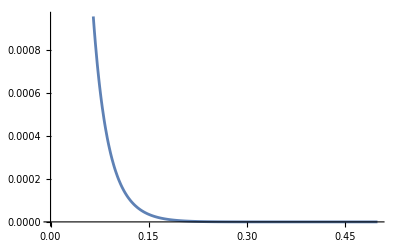

```mathematica
Plot[crossingEq[3]/.Table[C[i-1]->%56[[i,1]],{i,4}]/.Table[Δ[i-1]->{1,2,4,6}[[i]],{i,4}]/.Δσ->1/8/.Δσ->1/8,{z,0,1/2}]
```

```mathematica
D[crossingEq[5-1],{Table[C[i],{i,0,4}],1}]
```

{-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z],-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z],-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z],-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z]}

```mathematica
CoefficientList[Series[crossingEq[5-1]/.C[j_]-> c[j]/.genBos/.Δσ->1/.z->1/2+z1//Simplify,{z1,0,7}]//Normal,z1]//N//Chop
```

{0,-0.00634921 (315.-64.7591 c[0]-130.821 c[1.]-108.864 c[2.]-73.5278 c[3.]-45.25 c[4.]),0,-2.16852 c[0]+0.609522 c[1.]+11.9026 c[2.]+20.7072 c[3.]+23.6607 c[4.],0,0.925931 c[0]-12.0473 c[1.]+18.5594 c[2.]+189.375 c[3.]+465.384 c[4.],0,1.87515 c[0]-17.5662 c[1.]-78.9331 c[2.]+563.502 c[3.]+3700.16 c[4.]}

```mathematica
D[%26[[2;;]],{Table[c[i],{i,0,4}],1}]
```

{{-2/315 (-6615+9450 Log[2]),-2/315 (-5960850+8599500 Log[2]),-2/315 (-4595604552+6630055740 Log[2]),-2/315 (-3240137609280+4674530460600 Log[2]),-2/315 (-2165640832331405+3124359289151100 Log[2])},{0,0,0,0,0},{-24 (-11+16 Log[2]),-560 (-1841+2656 Log[2]),-55440 (-30931+44624 Log[2]),-1029600 (-2017513+2910656 Log[2]),-3695120/7 (-4007334881+5781362160 Log[2])},{0,0,0,0,0},{-16/35 (-2331+3360 Log[2]),-16/35 (-25323690+36534400 Log[2]),-16/35 (-81526400802+117617734080 Log[2]),-16/35 (-161182220979780+232536790886400 Log[2]),-16/35 (-242602321775886930+350001166534219200 Log[2])}}

```mathematica
CoefficientList[Series[crossingEq[5-1]/.C[j_]-> c[j]/.genBos/.Δσ->1/.z->1/2+z1//Simplify,{z1,0,7}]//Normal,z1]//N//Simplify
```

{0.,-2.+0.411169 c[0.]+0.830608 c[1.]+0.691198 c[2.]+0.466843 c[3.]+0.287302 c[4.],0.,-2.16852 c[0.]+0.609522 c[1.]+11.9026 c[2.]+20.7072 c[3.]+23.6607 c[4.],-2.66454×10^-15 c[0.],0.925931 c[0.]-12.0473 c[1.]+18.5594 c[2.]+189.375 c[3.]+465.384 c[4.],-1.06581×10^-14 c[0.],1.87515 c[0.]-17.5662 c[1.]-78.9331 c[2.]+563.502 c[3.]+3700.16 c[4.]}

-2

```mathematica
Solve[N[DeleteCases[Table[D[crossingEq[5-1]/.C[j_]-> c[j]/.genBos/.Δσ->1//Simplify,{z,n}]/D[crossingEq[0]/.Δσ->1//Simplify,C[0],{z,n}]/.z->1/2//Simplify,{n,1,9}],0]==0//Chop,30]][[1]]
```

```mathematica
DeleteCases[Table[D[crossingEq[0]/.Δσ->1,C[0],{z,n}]/.z->1/2//Simplify,{n,1,10}],0]
```

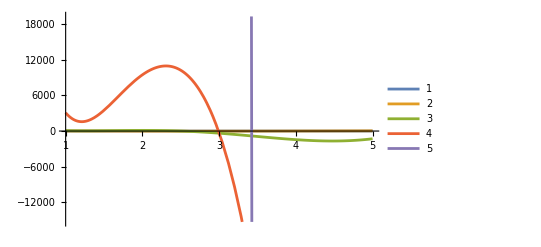

```mathematica
Plot[%89,{Δ[0],1,5},WorkingPrecision->30,PlotLegends->Automatic]
```

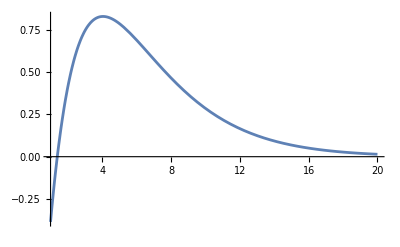

```mathematica
Plot[D[crossingEq[0]/.Δσ->1,C[0],z]/.z->1/2//Simplify,{Δ[0],1,20}]
```

```mathematica
D[Exp[x]-Sum[C[n]x^n,{n,0,10}],{x,4}]/.x->0
```

1-24 C[4]

```mathematica
%167/.C[i_]->(-1)^i/2^i/.x->1/2//N
```

6.35657×10^-6

```mathematica
Solve[Table[D[%167,{x,n}]==0,{n,0,10}]/.x->1/2]//N
```

{{C[0]→0.993479,C[1]→-0.48228,C[2]→0.225763,C[3]→-0.099756,C[4]→0.0405791,C[5]→-0.0147728,C[6]→0.00465689,C[7]→-0.00121876,C[8]→0.000249026,C[9]→-0.0000356241,C[10]→2.74032×10^-6}}

```mathematica
x-FourierSeries[x,x,10]/.x->1/2//ComplexExpand//N
```

-0.0836097

```mathematica
x(x-Pi)/.x->1/2//ComplexExpand//N
```

-1.3208

```mathematica
FourierSeries[x(x-Pi),x,10]/.x->1/2//ComplexExpand//N
```

-1.57357

```mathematica
FourierSeries[x,x,10]//ComplexExpand//N
```

2. Sin[x]-1. Sin[2. x]+0.666667 Sin[3. x]-0.5 Sin[4. x]+0.4 Sin[5. x]-0.333333 Sin[6. x]+0.285714 Sin[7. x]-0.25 Sin[8. x]+0.222222 Sin[9. x]-0.2 Sin[10. x]

```mathematica
x-Sum[C[n]Sin[n x],{n,0,5}]
```

x-C[1] Sin[x]-C[2] Sin[2 x]-C[3] Sin[3 x]-C[4] Sin[4 x]-C[5] Sin[5 x]

```mathematica
Solve[Table[D[%210,{x,n+1}]==0,{n,0,8}]/.x->0]//N
```

{{C[1]→1.66667,C[2]→-0.47619,C[3]→0.119048,C[4]→-0.0198413,C[5]→0.0015873}}

```mathematica
Solve[%167==0/.x->Table[{i/20},{i,0,10}]]//N
```

{{C[0]→0.996277,C[1]→-0.489706,C[2]→0.235455,C[3]→-0.109084,C[4]→0.0477984,C[5]→-0.019347,C[6]→0.00704975,C[7]→-0.00222355,C[8]→0.000582796,C[9]→-0.000113365,C[10]→0.0000146302}}

```mathematica
Solve[%210==0/.x->Table[{i/5}//N,{i,0,5}]]
```

{{C[1]→1.70099,C[2]→-0.516691,C[3]→0.143096,C[4]→-0.0275413,C[5]→0.0026541}}

```mathematica
Solve[%210==0/.x->Table[{i/5}//N,{i,0,5}]]
```

```mathematica
1/Sqrt[1+1/4+x]-Sum[C[n]LegendreP[n,x],{n,0,10}]
```

1/(√(5/4+x))-C[0]-x C[1]-1/2 (-1+3 x^2) C[2]-1/2 (-3 x+5 x^3) C[3]-1/8 (3-30 x^2+35 x^4) C[4]-1/8 (15 x-70 x^3+63 x^5) C[5]-1/16 (-5+105 x^2-315 x^4+231 x^6) C[6]-1/16 (-35 x+315 x^3-693 x^5+429 x^7) C[7]-1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8) C[8]-1/128 (315 x-4620 x^3+18018 x^5-25740 x^7+12155 x^9) C[9]-1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10) C[10]

```mathematica
D[crossingEq[5-1]/.C[j_]-> c[j]/.genBos/.Δσ->1//Simplify,{z,n}]
```

```mathematica
N[DeleteCases[Table[D[crossingEq[5-1]/.C[j_]-> c[j]/.genBos/.Δσ->1//Simplify,{z,n}]/.z->1/2//Simplify,{n,Append[Table[i,{i,10,18}],1]}],0],30]//Chop//Expand
```

{3.4825401382748878152291328114×10^8 c[0]-5.937268694255308130865216259×10^8 c[1.]-4.2036205646385318092362115685×10^10 c[2.]-1.3039182174259655430899069948×10^11 c[3.]+1.5301138639588282132546447773×10^12 c[4.],1.3407454174835299967029788743×10^11 c[0]+1.5946798282092820783434149216×10^11 c[1.]-1.6844597304526077448283810681×10^13 c[2.]-1.1931111682750070651562670276×10^14 c[3.]+3.3995889889487282027013135634×10^14 c[4.],7.4096255107016519723050225442×10^13 c[0]+2.6243745887625258620329986589×10^14 c[1.]-8.7280200287236821005472937357×10^15 c[2.]-9.8929243163892929059409730218×10^16 c[3.]-1.0019689068801191127531102304×10^17 c[4.],5.5754381261214773458678645281×10^16 c[0]+3.0504973862149449894136151386×10^17 c[1.]-5.7339728178197489752564667903×10^18 c[2.]-9.2937723180851581164678668388×10^19 c[3.]-3.5654914355103649386311442774×10^20 c[4.],-2.+0.411169166403281434966072712509 c[0]+0.830608093652772485792835050226 c[1.]+0.691198210712458438845802154126 c[2.]+0.466841186406707388590442816495 c[3.]+0.286426715453386666832006214856 c[4.]}

```mathematica
Solve[N[DeleteCases[Table[D[crossingEq[5-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,Append[Table[i,{i,10,18}],1]}],0]==0,30]//Chop][[1]]
```

{c[4.]→11.149708836630303047743350592-1.8158117188481459317874624248 c[0]-3.0339653367171579787441213927 c[1.]-2.4552376725920686057606284956 c[2.]-1.6397807284569353567130815569 c[3.]}

```mathematica
Series[Exp[x],{x,0,5}]//Normal//N
```

1.+x+0.5 x^2+0.166667 x^3+0.0416667 x^4+0.00833333 x^5

```mathematica
Solve[Exp[x]-Sum[C[n]x^n,{n,0,5}]==0/.x->Table[{i/10},{i,0,5}]]//N
```

{{C[0]→1.,C[1]→1.,C[2]→0.499953,C[3]→0.167048,C[4]→0.0402541,C[5]→0.0107225}}

```mathematica
Solve[Exp[x]-Sum[C[n]x^n,{n,0,6}]==0/.x->Table[{i/10},{i,0,6}]]//N
```

{{C[0]→1.,C[1]→1.,C[2]→0.500005,C[3]→0.166625,C[4]→0.0418517,C[5]→0.00790328,C[6]→0.0018795}}

```mathematica
D[crossingEq[0]/.C[j_]-> c[j]/.Δσ->1,z,c[0]]/.z->1/2//Simplify
```

2^(-2-Δ[0]) (4 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (-2+Δ[0])+Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0])

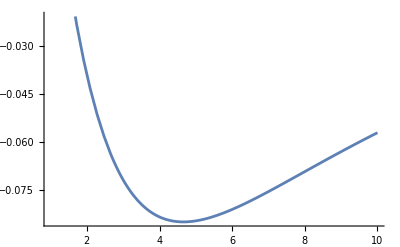

```mathematica
Plot[D[crossingEq[0]/.C[j_]-> c[j]/.Δσ->1,c[0]]/.z->1/2-1/10//Simplify,{Δ[0],1,10}]
```

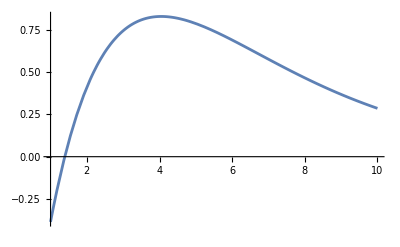

```mathematica
Plot[D[crossingEq[0]/.C[j_]-> c[j]/.Δσ->1,z,c[0]]/.z->1/2//Simplify,{Δ[0],1,10}]
```

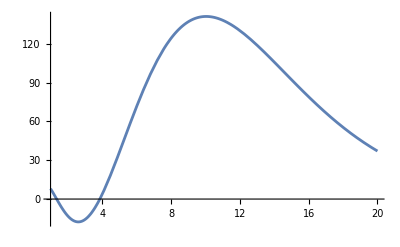

```mathematica
Plot[D[crossingEq[0]/.C[j_]-> c[j]/.Δσ->1,{z,3},c[0]]/.z->1/2//Simplify,{Δ[0],1,20},WorkingPrecision->30]
```

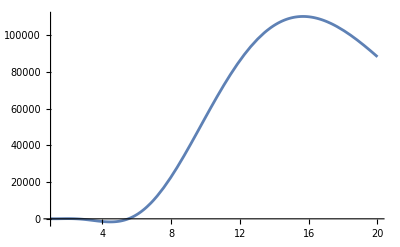

```mathematica
Plot[D[crossingEq[0]/.C[j_]-> c[j]/.Δσ->1,{z,5},c[0]]/.z->1/2//Simplify,{Δ[0],1,20},WorkingPrecision->30]
```

```mathematica
DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}],0]
```

```mathematica
D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,8}]//Simplify
```

$Aborted

```mathematica
N[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[{1,2,3,6,7,8}]],30]//Expand
```

{-1.7153602840047625371862025626+0.27935898160044569721186424499 c[0]+0.46676946617241179531974095207 c[1.]+0.37773337878745630058151535473 c[2.]+0.25227696770255051441767702812 c[3.]+0.15384798913934542144509209694 c[4.]+0.088959261163699028908287879496 c[5.],-6.5869834905782881427950178404-11.7482344143333307858471098385 c[0]-0.18056547964155559056317755172 c[1.]+39.3572743288289432863732363164 c[2.]+68.782899091952058572924206231 c[3.]+77.703076039192372802581710172 c[4.]+71.297479006811602165152231462 c[5.],-14.7548430188953654398608399624+302.762886420060853483971766667 c[0]-1214.71240818303467276904090148 c[1.]+144.843785739761222148333567965 c[2.]+11526.2256898064488653361891086 c[3.]+29787.284803478245170719956935 c[4.]+47063.487671084805568045286396 c[5.],-8.670873614199501316948145511×10^6+1.5419819152214157901806804446×10^8 c[0]+2.1865671343093001761646856618×10^9 c[1.]-1.4437964570499692952171288067×10^10 c[2.]-1.6253461040502699080951355172×10^11 c[3.]+1.0511640797733855343458093663×10^11 c[4.]+5.6082245668960569800755430345×10^12 c[5.],-2.7386087223087704959449022782×10^9+3.8488062816286134853316900423×10^10 c[0]+9.4035222210606812435903333897×10^11 c[1.]-1.9055605326500168089611219277×10^12 c[2.]-8.3019142125268869644065928403×10^13 c[3.]-2.6006182985354467768012464341×10^14 c[4.]+2.1690290409469742589570726506×10^15 c[5.],-1.2987578004677113199969104564×10^12+1.3772292840482009280368139456×10^13 c[0]+5.1985823328325111670035314015×10^14 c[1.]+7.9859829205360983561331210146×10^14 c[2.]-4.6067150451750927183505685987×10^16 c[3.]-3.2772219923194575730884861915×10^17 c[4.]+4.0701424354894773647915699344×10^17 c[5.]}

```mathematica
D[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,20}],0],{Table[c[i],{i,0,5}],1}][[{1,2,3,4,5,7}]]//MatrixRank
```

6

```mathematica
crossingEq[6-1]==0/.C[j_]-> 0
```

(1-z)^(2 Δσ)-z^(2 Δσ)==0

```mathematica
D[crossingEq[6-1],C[0]]
```

-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

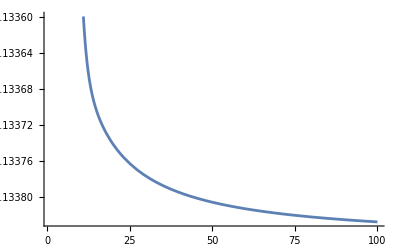

```mathematica
Plot[D[crossingEq[6-1],C[0]]/.z->36/100/.Δσ->1,{Δ[0],1,100},WorkingPrecision->30]
```

```mathematica
Series[D[crossingEq[6-1],C[0]],{Δ[0],Infinity,1}]
```

-(1-z)^(Δ[0]+O[1/Δ[0]]^2) z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^(Δ[0]+O[1/Δ[0]]^2) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> 0/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[{1,2,3,4,5,6}]]//N
```

{-1.71536,-6.58698,-14.7548,-481.598,-45771.1,-8.67087×10^6}

```mathematica
-Inverse[%272].%277
```

{1.96312,2.00234,0.53022,0.121764,0.00627096,0.00394326}

```mathematica
%114
```

```mathematica
{2.,1.9625806451612917,0.5621371592539448,0.10232272113219323,0.014612534143615775,0.00179232}
```

```mathematica
M6=D[crossingEq[6-1],{Table[C[i],{i,0,5}],1}]
```

{-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z],-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z],-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z],-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z],-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z]}

```mathematica
N[%,30]
```

{{0.279358981600445697211864244991,0.466769466172411795319740952067,0.377733378787456300581515354733,0.252276967702550514417677028123,0.153847989139345421445092096937,0.0889592611636990289082878794956},{-11.7482344143333307858471098385,-0.18056547964155559056317755172,39.3572743288289432863732363164,68.7828990919520585729242062306,77.7030760391923728025817101724,71.2974790068116021651522314616},{302.762886420060853483971766667,-1214.71240818303467276904090148,144.843785739761222148333567965,11526.2256898064488653361891086,29787.284803478245170719956935,47063.487671084805568045286396},{11595.8319964915110807361340222,-17229.3723212275408654362370271,-447442.593623626094866109440836,755281.217527687225491558850151,8.67076212957688863792601618979×10^6,2.61508253105364914407370011991×10^7},{984549.82892670204822857921553,5.47199966850848471326264716805×10^6,-8.42200084384792825055440121785×10^7,-2.45011770587676737996378382303×10^8,1.83721372807103305785383439249×10^9,1.27112679281152074095845433233×10^10},{1.5419819152214157901806804446×10^8,2.18656713430930017616468566179×10^9,-1.44379645704996929521712880671×10^10,-1.62534610405026990809513551723×10^11,1.05116407977338553434580936627×10^11,5.60822456689605698007554303446×10^12}}

```mathematica
derivatives
```

```mathematica
DeleteCases[Table[D[M6/.genBos/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}],ConstantArray[0,Length[M6]]];
```

```mathematica
%5[[6]]//N
```

{1.54198×10^8,2.18657×10^9,-1.4438×10^10,-1.62535×10^11,1.05116×10^11,5.60822×10^12}

```mathematica
%5[[7]]//N
```

{3.84881×10^10,9.40352×10^11,-1.90556×10^12,-8.30191×10^13,-2.60062×10^14,2.16903×10^15}

```mathematica
N[D[%12/D[%12,c[0]],{Table[c[i],{i,0,5}],1}],30]
```

{{1.,1.67085899117434031383924633931,1.35214331260596796962638265353,0.903056584246038877369400175132,0.550717890858390672256849158844,0.3184406696146013613248956248},{1.,0.0153695843369671151794905675426,-3.35005865058424817396906943616,-5.85474350154556699166496243612,-6.61402158816233812586485972531,-6.0687824648634637072712509848},{1.,-4.01209151671817557585509767239,0.478406674782460971873494755565,38.0701407167015611802023406294,98.3848620142649058481528906224,155.446687100834867564357565068},{1.,-1.48582458994236377132911185034,-38.5865019223291963262105979008,65.1338530737775976117857044387,747.748167807222008655999193227,2255.19180671544800799225176016},{1.,5.55786970627351069190518701125,-85.5416414325021528328473509114,-248.856648377841951366765066039,1866.04443380367525589820033984,12910.7410865860180725118241327},{1.,14.1802385146347666768701897475,-93.6325155825612987798207710711,-1054.06301332456529692804327845,681.696762716213248821006561418,36370.2356787418128239780524918},{1.,24.4323084431300671821909408894,-49.5104298115955909426492329027,-2157.01014939467183240646419835,-6756.94776052745671718652603366,56355.8901704232989316064628403},{1.,37.7466729254543552130324403633,57.9858634508718528889364045851,-3344.91511219845998114736513588,-23795.7617535291951656045614228,29553.1214927828137624605253549},{1.,57.8006988331790095534357153642,264.341354788914451695640835491,-4512.03054971537779443757249502,-55202.0460511879474921455573583,-120213.417116597993182402355077},{1.,95.8692195754720780350756942545,695.813023288059847089210079011,-5691.46439977588714532164456606,-115999.806781217741487845728116,-573038.611784153806303539732799},{1.,211.97205281157890709216507021,2053.0468057943110890457631093,-7361.52855225530236769395772669,-291496.726822519281974809635235,-2.21797695538721378277878011432×10^6},{1.,-2507.87097711262680480930286342,-29897.2332271616643301163729676,14406.5001822750765955353941698,3.62245812539044898384911250445×10^6,3.78699876449680904551896755313×10^7},{1.,-191.30617932368434994161681978,-2681.24618658470258443089018322,-5068.54637253356374847345111011,271531.378189450501280731637901,3.73511925129304290195390217848×10^6},{1.,-100.402521276332498525953846314,-1607.24464709422083413446931356,-6153.23415935855184214349451495,131026.216208376219691447194387,2.35550888117531324361681349978×10^6},{1.,-67.8874382623297801149840200791,-1217.4189454097789573214057189,-6667.76612718358255529956031176,75182.6875743645192988531240409,1.81362612148442212429770107894×10^6}}

```mathematica
%32[[;;6]].%8/D[%12[[;;6]],c[0]]
```

{6.01836×10^12,2.87109×10^12,2.89308×10^12,1.09662×10^12,7.37842×10^10,1.32438×10^9}

```mathematica
%63[[;;6]]/.c[i_]->0
```

{-2/Hypergeometric2F1[13/5,18/5,31/5,-1],496/(4030 Hypergeometric2F1[13/5,18/5,31/5,-1]-1587 Hypergeometric2F1[13/5,28/5,41/5,-1]),-71176/(16523000 Hypergeometric2F1[13/5,18/5,31/5,-1]-21146775 Hypergeometric2F1[13/5,28/5,41/5,-1]+7363818 Hypergeometric2F1[13/5,38/5,51/5,-1]),11754208/(2808910000 Hypergeometric2F1[13/5,18/5,31/5,-1]-69 (208403000 Hypergeometric2F1[13/5,28/5,41/5,-1]-235855620 Hypergeometric2F1[13/5,38/5,51/5,-1]+80766169 Hypergeometric2F1[13/5,48/5,61/5,-1])),5915305176/(428358775000 Hypergeometric2F1[13/5,18/5,31/5,-1]+23 (190688745000 Hypergeometric2F1[13/5,28/5,41/5,-1]-863231569200 Hypergeometric2F1[13/5,38/5,51/5,-1]+7342379 (130845 Hypergeometric2F1[13/5,48/5,61/5,-1]-44944 Hypergeometric2F1[13/5,58/5,71/5,-1]))),5650729708128/(266117888968750 Hypergeometric2F1[13/5,18/5,31/5,-1]+973108501828125 Hypergeometric2F1[13/5,28/5,41/5,-1]+8810357203147500 Hypergeometric2F1[13/5,38/5,51/5,-1]-808013 (48540223875 Hypergeometric2F1[13/5,48/5,61/5,-1]-5618 (9645350 Hypergeometric2F1[13/5,58/5,71/5,-1]-3337929 Hypergeometric2F1[13/5,68/5,81/5,-1])))}

```mathematica
N[D[%63[[{5,2,3,6,7,9}]],{Table[c[i],{i,0,5}]}],30]//Det
```

-1.36938631663985566488803738559×10^14

```mathematica
-Inverse[N[D[%63[[{1,2,3,4,5,8}]],{Table[c[i],{i,0,5}]}],30]].N[%63[[{1,2,3,4,5,8}]]/.c[i_]->0,30]/%84
```

{0.921835,1.08456,0.773271,1.69407,-0.779869,3.80112}

```mathematica
-Inverse[N[D[%63[[{1,2,3,4,6,5}]],{Table[c[i],{i,0,5}]}],30]].N[%63[[{1,2,3,4,6,5}]]/.c[i_]->0,30]/%84
```

{0.98156,1.02026,0.943222,1.19,0.429149,2.20009}

```mathematica
-Inverse[N[D[%63[[{1,2,3,4,6,7}]],{Table[c[i],{i,0,5}]}],30]].N[%63[[{1,2,3,4,6,7}]]/.c[i_]->0,30]/%84
```

{0.921041,1.08396,0.785478,1.60013,-0.344338,2.84415}

```mathematica
-Inverse[N[D[%63[[{1,2,3,4,5,7}]],{Table[c[i],{i,0,5}]}],30]].N[%63[[{1,2,3,4,5,7}]]/.c[i_]->0,30]/%84
```

{0.96197,1.04135,0.887478,1.35534,0.0325895,2.72523}

```mathematica
%84
```

{2.,1.96258,0.562137,0.102323,0.0146125,0.00179232}

```mathematica
N[%,30]
```

{{c[0]→1.96311970187722617766873185496,c[1.]→2.00233629783611055487163081204,c[2.]→0.530220243688265231686764932505,c[3.]→0.121764070671132356210840927287,c[4.]→0.00627095542564304883018194069924,c[5.]→0.00394326491980435722823861443609}}

```mathematica
%12/D[%12,c[0]]//Simplify
```

```mathematica
Table[D[crossingEq[6-1]/.C[j_]->0/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}]
```

{-13/(5 2^(3/5)),0,-(624 2^(2/5))/125,0,-(34944 2^(2/5))/3125,0,-(28514304 2^(2/5))/78125,0,-(67749986304 2^(2/5))/1953125,0,-(320863935135744 2^(2/5))/48828125,0,-(2533541631831834624 2^(2/5))/1220703125,0,-(30037669586998231302144 2^(2/5))/30517578125,0,-(499105917857562611316424704 2^(2/5))/762939453125,0,-(11068172834409308468553034235904 2^(2/5))/19073486328125,0,-(315841380002704026458629384955756544 2^(2/5))/476837158203125,0,-(11274273900576522928467234525380685594624 2^(2/5))/11920928955078125,0,-(492189701403568684965165590440019210318905344 2^(2/5))/298023223876953125,0,-(25798615388769456191134119588504046928075742511104 2^(2/5))/7450580596923828125,0,-(1598894987334375816901728195617126812414422217868181504 2^(2/5))/186264514923095703125,0}

```mathematica
N[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]->0/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}]/D[%12[[;;6]],c[0]],0],30]
```

Thread::tdlen: Objects of unequal length in {-13/(5 2^(3/5)),0,-(624 2^(2/5))/125,0,-(34944 2^(2/5))/3125,0,-(28514304 2^(2/5))/78125,0,-(67749986304 2^(2/5))/1953125,0,«20»} {(10 2^(3/5))/(13 Hypergeometric2F1[13/5,18/5,31/5,-1]),-3875/(39 2^(2/5) (4030 Hypergeometric2F1[13/5,18/5,31/5,-1]-1587 Hypergeometric2F1[13/5,28/5,41/5,-1])),3971875/(«1»),-1688046875/(52416 «1» (2808910000 «17»[«1»]-«1»)),-2574271484375/(15095808 2^(2/5) (428358775000 Hypergeometric2F1[13/5,18/5,31/5,-1]+23 («1»))),-4569331884765625/(5313724416 2^(2/5) (266117888968750 Hypergeometric2F1[13/5,18/5,31/5,-1]+973108501828125 Hypergeometric2F1[13/5,28/5,41/5,-1]+8810357203147500 Hypergeometric2F1[13/5,38/5,51/5,-1]-808013 (Times[«2»]+Times[«2»])))} cannot be combined.

Thread::tdlen: Objects of unequal length in {3.57962358779734530556935291251,-0.0851191732078446386968707355379,0.00330291473906935480764883748638,0.0000862378827411922366604008707979,1.01569262481122038672153445427×10^-6,6.48516036490874349415135690698×10^-9} {-1.7153602840047625371862025626,0,-6.58698349057828814279501784038,0,-«65»,0,-«46»,0,-45771.0811560362189450387748682,0,«20»} cannot be combined.

{3.57962358779734530556935291251,-0.0851191732078446386968707355379,0.00330291473906935480764883748638,0.0000862378827411922366604008707979,1.01569262481122038672153445427×10^-6,6.48516036490874349415135690698×10^-9} {-1.7153602840047625371862025626,0,-6.58698349057828814279501784038,0,-14.7548430188953654398608399624,0,-481.598076136744727957057816374,0,-45771.0811560362189450387748682,0,-8.67087361419950131694814551103×10^6,0,-2.73860872230877049594490227821×10^9,0,-1.29875780046771131999691045642×10^12,0,-8.63206384502859651722746565752×10^14,0,-7.65698591309416625464145113685×10^17,0,-8.73999000064220512969793798565×10^20,0,-1.24793073225169661723879037734×10^24,0,-2.17918656188720270088706530853×10^27,0,-4.56896971311518467078785660848×10^30,0,-1.13266586776010674062699280467×10^34,0}

```mathematica
%12
```

```mathematica
Table[D[M10,{z,n}],{n,1,10}]/.z->1/2
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity (2^(3-2 Δσ-Δ[0]) Δσ Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]-2^(2-2 Δσ-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]-2^(-2 Δσ-Δ[0]) Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]) encountered.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity (2^(3-2 Δσ-Δ[0]) Δσ Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]-2^(2-2 Δσ-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]-2^(-2 Δσ-Δ[0]) Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
M10=D[crossingEq10norm,{Table[C[i],{i,0,10-1}],1}]
```

{1,((1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]-(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]-(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]-(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]-(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]-(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[6] z^(2 Δσ) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]-(1-z)^(2 Δσ) z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[7] z^(2 Δσ) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1-z]-(1-z)^(2 Δσ) z^Δ[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[8] z^(2 Δσ) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1-z]-(1-z)^(2 Δσ) z^Δ[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),((1-z)^Δ[9] z^(2 Δσ) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1-z]-(1-z)^(2 Δσ) z^Δ[9] Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],z])/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])}

```mathematica
v10=crossingEq10norm/.C[i_]->0
```

(-(1-z)^(2 Δσ)+z^(2 Δσ))/((1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])

```mathematica
crossingEq10normDer=DeleteCases[Table[D[crossingEq[10-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}],0];
```

```mathematica
-Inverse[N[D[crossingEq10normDer[[;;10]],{Table[c[i],{i,0,9}]}],30]].N[crossingEq10normDer[[;;10]]/.c[i_]->0,30]
```

{1.999839233647433296114454396,1.9627618086976512603990276188,0.56197144634580838227469361015,0.10245409831897396302716234442,0.014522993201788951620342292518,0.0018435346898765992479170996773,0.00017428426735108403222572154181,0.000028743542195257559303481846719,-1.886973803908009059290348291×10^-7,5.0623447976005380619712159985×10^-7}

```mathematica
Table[i,{i,10}]
```

```mathematica
-Inverse[N[D[crossingEq10normDer[[;;10]],{Table[c[i],{i,0,9}]}],30]].N[crossingEq10normDer[[;;10]]/.c[i_]->0,30]/Table[C[i],{i,0,9}]/.genBos/.Δσ->1+3/10//N
```

{0.99992,1.00009,0.999705,1.00128,0.993872,1.02857,0.880139,1.41808,-0.0964018,2.80394}

{2.,1.96258,0.562137,0.102323,0.0146125,0.00179232}

```mathematica
-Inverse[N[D[crossingEq10normDer[[{1,2,3,4,5,6,7,8,10,11}]],{Table[c[i],{i,0,9}]}],30]].N[crossingEq10normDer[[{1,2,3,4,5,6,7,8,10,11}]]/.c[i_]->0,30]/Table[C[i],{i,0,9}]/.genBos/.Δσ->1+3/10//N
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.279358981600445697211864244991,0.466769466172411795319740952067,0.377733378787456300581515354733,0.252276967702550514417677028123,0.153847989139345421445092096937,0.0889592611636990289082878794956,0.0496697318516603449825846236378,0.0270540235536336581598401184452,0.0144660811322664610602113858029,0.00762534410103822191101073239327},«8»,{1.85896149649385867325082900757×10^21,3.94047884509487968017877206526×10^23,3.8165349624713289820133318803×10^24,-1.36847981339827857872956014112×10^25,-5.41881191517051957674266667642×10^26,-«56»,-1.61011606635118031020144402547×10^27,2.33421958947156158038920281098×10^29,2.4774676714192255633123573544×10^30,1.57075513452993050916925785225×10^31}} may contain significant numerical errors.

{0.999846,1.00018,0.999442,1.00238,0.988986,1.04909,0.806153,1.62589,-0.491478,3.17875}

```mathematica
Exp[z]-Sum[C[n]z^n,{n,0,5}]/.Table[{z->i/10}]
```

ⅇ^z-C[0]-z C[1]-z^2 C[2]-z^3 C[3]-z^4 C[4]-z^5 C[5]

```mathematica
DeleteCases[Table[D[M6/.genBos/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}],ConstantArray[0,Length[M6]]][[{1,2,3,4,5,6}]]
```

```mathematica
DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}],0];
```

```mathematica
N[%12[[6]]==0//Expand,30]//FullSimplify
```

1.5419819152214157901806804446×10^8 c[0]+2.18656713430930017616468566179×10^9 c[1.]+1.05116407977338553434580936627×10^11 c[4.]+5.60822456689605698007554303446×10^12 c[5.]==8.67087361419950131694814551103×10^6+1.44379645704996929521712880671×10^10 c[2.]+1.62534610405026990809513551723×10^11 c[3.]

```mathematica
N[%12[[7]]/D[%12[[7]],c[0]]//Expand,30]//FullSimplify
```

-0.0711547560962183459830308081884+1. c[0]+24.4323084431300671821909408894 c[1.]-49.5104298115955909426492329027 c[2.]-2157.01014939467183240646419835 c[3.]-6756.94776052745671718652603366 c[4.]+56355.8901704232989316064628403 c[5.]

```mathematica
Solve[N[DeleteCases[Table[D[crossingEq[6-1]==0/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[{1,2,3,4,5,6}]],30]][[1]]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.3483702589034369225938588138,2.331899458628176563102817067,3.8238037929576445569045829351,5.7253673995209489996414705609,7.074902126187394107725857616,4.2342903641526902474279356652,-26.},{-«77»,-«77»,-«77»,-«75»,«74»,«75»,«38»},{4.9547879523955014225212687505×10^26,«70»,«70»,«68»,-«69»,«68»,-1.55337230722120257827016×10^23}} may contain significant numerical errors.

{c[3.]→22.07251411242178-4.104716595505988 c[0]-6.041111403930994 c[1.]-3.387956986764694 c[2.],c[4.]→-34.570644514847+6.841106697523493 c[0]+9.465980363657652 c[1.]+4.135881417333703 c[2.],c[5.]→16.47492882516936-3.331008268653146 c[0]-4.485853845866957 c[1.]-1.791009735818048 c[2.]}

```mathematica
Solve[N[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[{1,2,3,4,5,7}]]==0//Chop,30]][[1]]
```

{c[0]→1.9239398061840066,c[1.]→2.0437309568085583,c[2.]→0.49888425755798929,c[3.]→0.13868166550022542,c[4.]→0.00047621485394770433,c[5.]→0.0048844875297639963}

```mathematica
Solve[N[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[{1,2,3,4,6,7}]]==0//Chop,30]][[1]]
```

{c[0]→1.8420821325984701,c[1.]→2.1273601110576502,c[2.]→0.44154636791434557,c[3.]→0.16372948312552252,c[4.]→-0.0050316444908350734,c[5.]→0.0050976304640337743}

```mathematica
Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}]
```

```mathematica
Solve[N[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[;;6]]==0//Simplify,30]][[1]]
```

{c[0]→1.9631197018772261777,c[1.]→2.0023362978361105549,c[2.]→0.53022024368826523169,c[3.]→0.12176407067113235621,c[4.]→0.0062709554256430488302,c[5.]→0.0039432649198043572282}

```mathematica
N[D[DeleteCases[Table[D[crossingEq[6-1]/.C[j_]-> c[j]/.genBos/.Δσ->1+3/10//Simplify,{z,n}]/.z->1/2//Simplify,{n,1,30}],0][[;;6]],{Table[c[i],{i,0,5}],1}],30]
```

{{0.279358981600445697211864244991,0.466769466172411795319740952067,0.377733378787456300581515354733,0.252276967702550514417677028123,0.153847989139345421445092096937,0.0889592611636990289082878794956},{-11.7482344143333307858471098385,-0.18056547964155559056317755172,39.3572743288289432863732363164,68.7828990919520585729242062306,77.7030760391923728025817101724,71.2974790068116021651522314616},{302.762886420060853483971766667,-1214.71240818303467276904090148,144.843785739761222148333567965,11526.2256898064488653361891086,29787.284803478245170719956935,47063.487671084805568045286396},{11595.8319964915110807361340222,-17229.3723212275408654362370271,-447442.593623626094866109440836,755281.217527687225491558850151,8.67076212957688863792601618979×10^6,2.61508253105364914407370011991×10^7},{984549.82892670204822857921553,5.47199966850848471326264716805×10^6,-8.42200084384792825055440121785×10^7,-2.45011770587676737996378382303×10^8,1.83721372807103305785383439249×10^9,1.27112679281152074095845433233×10^10},{1.5419819152214157901806804446×10^8,2.18656713430930017616468566179×10^9,-1.44379645704996929521712880671×10^10,-1.62534610405026990809513551723×10^11,1.05116407977338553434580936627×10^11,5.60822456689605698007554303446×10^12}}

```mathematica
%//Det
```

3.01587919420047844148798274856×10^32

```mathematica
getAvCs[5,{2,4,6,8,10},4/10,49/100,1+3/10]
```

{{5.043845595359697538649,0.22919737169204803255},{1.653748855643419698353,0.063000647325394440126},{1.255533409914492195344,0.030313580738225061045},{0.0288502625707775490998,0.00991536390451343552655},{0.06399884673976158732584,0.0016397997888624519998}}

```mathematica
getAvCs[5,{13/5,23/5,33/5,43/5,53/5},4/10,49/100,1+3/10]
```

{{2.144256532758055604077,0.01499884494712455292},{1.811699453981008112305,0.01516300594224469658},{0.6730162324228648199204,0.010086858140575327222},{0.04612293316010426939208,0.0041345075124786551832},{0.03146306813144087496456,0.00078303526356440672814}}

```mathematica
Table[Δ[i],{i,0,4}]/.genBos/.Δσ->1+3/10
```

{13/5,23/5,33/5,43/5,53/5}

```mathematica
Table[C[i],{i,0,4}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218}

```mathematica
Table[C[i],{i,0,5}]/.genBos/.Δσ->1+3/10//N
```

{2.,1.96258,0.562137,0.102323,0.0146125,0.00179232}

```mathematica
RandomSample[Range[5],5]
```

{5,1,3,2,4}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
crossingEqResc[10]/.C[i_]->0/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1
```

{1/5,9/50,4/25,7/50,3/25,1/10,2/25,3/50,1/25,1/50}

```mathematica
NullSpace[N[D[crossingEqResc[10],{Table[C[i],{i,0,9}],1}]/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1,40],Tolerance->10^(-18)]
```

{{-2.34891741060739892646990489551498154294×10^-6,0.00003114184628825812275957568705827698769835,-0.0003577622204257088819985679348258101958218,0.003443584619899043997415782173898433337847,-0.02602144485289058788295117182751872552275,0.1416302242293328847946156707650737591262,-0.4783002547311389649837363652365157686276,0.6575813500817767652454325498078821375427,0.5312716173713058773239477749673105646256,0.1892561218898246886950341754131013990833},{3.937021772547949712809704766777571620893×10^-7,-5.273814839464692844453052489926445378814×10^-6,0.00006263425000476849351996359161077688011072,-0.0006459434006207021821453027080777681669136,0.005508533676925253027908699212674290812025,-0.03665474203827272945794418812596128181348,0.1753188337595518159704069320887877270705,-0.5187609011066736785363395573495204984606,0.6041851639109116582658478787747960691837,0.577699217994166093736823307628649008756},{-5.767405517368019004732297755112407984205×10^-8,7.787850351923892845905070530934299977886×10^-7,-9.492018924208461838125001262632725905293×10^-6,0.0001032881565859811037198064170531713458646,-0.000966447358763144462818739376784987422265,0.007461760800687986153694665950230253089631,-0.04520828385040724530666047408698830823405,0.2001691822961695319563883449900826898548,-0.573108460563376492285537279049425811223,0.7933338384986266919029805320192082074187}}

```mathematica
Table[C[i],{i,0,9}]/.Solve[%437.Table[C[i],{i,0,9}]==0]
```

{{C[0],C[1],C[2],C[3],C[4],C[5],C[6],2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6],1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6],3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6]}}

```mathematica
matr=D[crossingEqResc[5],{Table[C[i],{i,0,4}],1}]/.zvalsTable[4/10,49/100,4]/.genBos/.Δσ->1;
```

```mathematica
Inverse[matr+ϵ IdentityMatrix[5]]
```

```mathematica
Normal[Series[Inverse[matr+ϵ IdentityMatrix[5]],{ϵ,0,0}]]/.ϵ->1/x/.x->0
```

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,nstates-1}]]/.genBos/.Δσ->1).%479.(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)
```

{-2.0464227977360689403296070755261695257895105233039120537332892835197583423041474448245726108,-1.161758325819246648731469119698344390042384430926430140837133985628307685393842733425344288,-0.2631443044514214863509550504106573508038416124129762451218739575347228108560532854406050821,-0.0207202706828752840498445010840297233790971342368224447443387553005429498837880825125361832,-0.007157948609417794233116897127311024970826551533266885357129349306721384657476721798248538641}

```mathematica
N[%,100]
```

{{-1.931379220798173496152794863923953837629673140751538689491084124244969599493598389020951816305029924×10^8,1.816781565690940324280696127562603454502382989840413983661933584699990839770446921534317560460647901×10^9,-7.601784279140463440630301342065145597681083089950747452467803204217617120884101841986278692125847502×10^9,1.874450276945664450765665777958211359788113397624688304758041127846323362584915504027959048588651408×10^10,-3.125849996341412821087870007275607747528229716645561202495827297570511290341928560926437851344526925×10^10},{2.397244824801001596595459878614167968914626300782289564729755205768835286005281935191928086584664734×10^9,-2.252608881290148907005026322654698237344744745350217244709447927055836498869327428876310119467322107×10^10,9.417535011601549100871686830878814733027718109942177442747785447606875632872637335358908483745448807×10^10,-2.320857354557290925239265960574993806629428804581045224429786550436249457788538678061780947590242318×10^11,3.869189407128154138630762523566987483845319012540671524304944040540534332273211228587517410823991097×10^11},{-2.224792858581943341948442479089728295184887611921164128694610615502238238649515152665933897001141064×10^10,2.083941643497059101277077225691386121081488033169526986045973545630856019475504605688508327944715364×10^11,-8.691046939917257907191557482496055230466660572335394577353047336070220558788418768850688492767618706×10^11,2.138268872136235414697120633035453748149236624822263626749433787947709611283732857717177635923644504×10^12,-3.561873554212807009559332321179624724730697443311528781582947757752190703733464292932845282327106462×10^12},{1.342689478236464071910792700734966274846619363720860516023276864308976661474236094884259234759749449×10^11,-1.250209848431226108875693505397077479103249629217095302490729128203579920466618378910422770761509946×10^12,5.190560870581259404767230268526057273270973829328987481454603196927254033489201916723528860693722523×10^12,-1.273223044483010476170452042363367673185119306388266843917526809778746418769019175383199350579164719×10^13,2.117810094500827846239602377288335098195041477290951639776779576719338735970962901442786178910479909×10^13},{-3.853016005658538284337591835682337624550283715563496837330256745760258804530566749034155909921411523×10^11,3.55476560769560351149245528872368005658921936808084286059677218111977052716082420002414007384888498×10^12,-1.466004097279996842814154701936397284646927392432236329526045095696839645377557485971382698967382729×10^13,3.580471777098640833267983049518365830406940011958598055706535893729258379218467197027174900067568514×10^13,-5.94315251781432067379259151692212887106313866199991813600860767735523893515536423100480705072985118×10^13}}

```mathematica
N[D[crossingEqResc[10],{Table[C[i],{i,0,9}],1}]/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1,40].{C[0],C[1],C[2],C[3],C[4],C[5],C[6],2.5087485506572257179480334815666634955613649144594053`39.80658706673054*^-6 C[0]-0.0000332979906540309955194307609227047580103260465624566445`39.80658706673054 C[1]+0.000383938628261310577200474007503925502429031844420480993`39.80658706673054 C[2]-0.0037252205209712628051023494860947453308214926894111602565`39.80658706673054 C[3]+0.0285848117787946762462337372811467944756278190753546761159`39.80658706673054 C[4]-0.1602611422898592288724392903192271211159872162231284500259`39.80658706673054 C[5]+0.5780373857537947703152287094933356626259519739433683774258`39.80658706673054 C[6],1.2054802178176043168080280109125551549345664689785138`39.80658706673054*^-6 C[0]-0.0000159432746893691265812592834722109700745280151736846177`39.80658706673054 C[1]+0.0001816801773933100924494692415436834002336552300081954454`39.80658706673054 C[2]-0.0017173810166690201625554282012081653198925474387515039534`39.80658706673054 C[3]+0.0125136865312749904037992751288606270394759902372669632323`39.80658706673054 C[4]-0.0630520362716209389835622169144893260804784842033007012615`39.80658706673054 C[5]+0.172174822760299695373919421390496917752521262637350896335`39.80658706673054 C[6],3.105512573889791816022284900792296173627532236623253`39.80658706673054*^-7 C[0]-4.0976180892333405370057350166709295895561726860897758`39.80658706673054*^-6 C[1]+0.000046338354233775264334360160069532562361732144453553528`39.80658706673054 C[2]-0.0004309149378289038045591348339119961437454138966951184725`39.80658706673054 C[3]+0.0030458156019116410104861754862809815241929213318413068425`39.80658706673054 C[4]-0.0145185719790919790138380356140902124724697840479587396509`39.80658706673054 C[5]+0.0355182890984562025077373092370681480371066678880585383433`39.80658706673054 C[6]}
```

{-0.002515521892582877053566509510805994576671 C[0]-0.0003483394989451069020085444624887596593085 C[1]-0.0000218601894040173861451071861328623171268 C[2]-1.205387253306969869322754662333229982795×10^-6 C[3]-6.414594513073491945532199921969760416827×10^-8 C[4]-3.376726951520122500319435901535763743571×10^-9 C[5]-2.546980519367019736768736434285530645537×10^-14 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-4.862763008769009603937139468607038950003×10^-13 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-9.282954750601905620731234336659445042651×10^-12 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-1.771459499965099856633505124770910521815×10^-10 C[6],-0.00228772316570951931580452845029577646247 C[0]-0.0003132295829842928299124641265595052375123 C[1]-0.00001911170959824764389998973476853712696419 C[2]-1.012691000471614024990467592981903151712×10^-6 C[3]-5.143793722250646701328397797675310392616×10^-8 C[4]-2.575590227195260291369258433145787236071×10^-9 C[5]-1.575721044938998170385743522573972886637×10^-14 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-3.171357335422954437180343032624958292525×10^-13 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-6.381254733630529211501948166358429905608×10^-12 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-1.283166359583530713513775137304859366858×10^-10 C[6],-0.00205245412046518268352494708168786397572 C[0]-0.000278181326718642313560309305187244147029 C[1]-0.00001654302017881431813129317438790633781391 C[2]-8.445115660173734826443833311024307880634×10^-7 C[3]-4.102184869980694120950133014879598439242×10^-8 C[4]-1.956067649137058503514274051027393254716×10^-9 C[5]-9.712094045498620340563396366011348697394×10^-15 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-2.060868075167646171197254497870642961363×10^-13 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-4.371014603442012149728871846647635801993×10^-12 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-9.259969378371793618626259161618953999218×10^-11 C[6],-0.001810527474461463271319775122148533870425 C[0]-0.0002432021685822168722806836406225179435129 C[1]-0.00001413297987288226046445532027188802469031 C[2]-6.971465934839285147216322842942676683866×10^-7 C[3]-3.246606758055519597710587942166079502313×10^-8 C[4]-1.476859267394092033037450152586679417329×10^-9 C[5]-5.961208188056177097715868939462200760491×10^-15 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-1.333702829490346677050940919151887484007×10^-13 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-2.981178335170318748371116777913385657801×10^-12 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-6.650287858826305406291386573784182280698×10^-11 C[6],-0.001562762240761092238270288838091138912249 C[0]-0.0002082943962179385535427602622520683713026 C[1]-0.00001186082345828850617014285583696680306631 C[2]-5.672530424463264988141819274751018326277×10^-7 C[3]-2.540795172949600820189938189925158559847×10^-8 C[4]-1.105422403120862191264023129701798504367×10^-9 C[5]-3.640890972896524050228834932792314933069×10^-15 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-8.586484830774103090569268632793774500772×10^-14 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-2.021544180186526206428615050584744598423×10^-12 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-4.743295454705567605439470244954661601813×10^-11 C[6],-0.001309982824476537775992726241852781111338 C[0]-0.0001734558580834223917511770490345026961108 C[1]-9.706137386150593520535579543121955022235×10^-6 C[2]-4.517934695779576587879424982320769396664×10^-7 C[3]-1.954100647506518444558943687752013881733×10^-8 C[4]-8.160167627018889854509649913489848457643×10^-10 C[5]-2.2089519868202567471444351799130489533×10^-15 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-5.486608612800133020509988146507792173515×10^-14 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-1.358631640649381431094774234808790059042×10^-12 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-3.346094559492360498000358753131419747231×10^-11 C[6],-0.00105301816775685550844746189827716106983 C[0]-0.0001386806473823615521901463503550126069364 C[1]-7.648825621775181096450791017830280456587×10^-6 C[2]-3.479858533122185238052585906354053280231×10^-7 C[3]-1.460386454841551302781115219826316082159×10^-8 C[4]-5.881374550634380670620988431922275525522×10^-10 C[5]-1.325353794499562604998613088539473060456×10^-15 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-3.459758491031568910056053388751532617031×10^-14 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-8.98560456426686720924580871667467021946×10^-13 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-2.314546565293701571193433459552278818222×10^-11 C[6],-0.0007927009349388904716805186123256490296384 C[0]-0.0001039597626856128264208686174402731393974 C[1]-5.669067635596413140875072870921670887399×10^-6 C[2]-2.532564432006456580478316191630801499009×10^-7 C[3]-1.037072197540630204444440997759683693546×10^-8 C[4]-4.052479258510400798460907979398048625558×10^-10 C[5]-7.764954625179365424731655481209198146734×10^-16 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-2.121092023852205687163428725252986953958×10^-14 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-5.748566996765796252192261161741487540749×10^-13 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-1.539891565017676590299622827559012801153×10^-11 C[6],-0.0005298667302718008346842326008011651292712 C[0]-0.00006928174941412817848328775625587686302636 C[1]-3.747270215281706515237252987480089261555×10^-6 C[2]-1.651951176982649472190163113463192022946×10^-7 C[3]-6.642926584966272469022128731020496109637×10^-9 C[4]-2.537412525456680193310746996695397969934×10^-10 C[5]-4.270034553792861771763451060690505271433×10^-16 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-1.211007509862832015614622736851962463542×10^-14 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-3.396922519935831286000373447051758509991×10^-13 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-9.38496087433217323627628047746528259086×10^-12 C[6],-0.0002653533411277594145314295138370644613072 C[0]-0.00003463332619789094668016977723744671489693 C[1]-1.86401456486306956658381636676740144254×10^-6 C[2]-8.151273909686441791051638711666339330394×10^-8 C[3]-3.241449970908445105707243043233458261767×10^-9 C[4]-1.220707387416629200892714538004792416851×10^-10 C[5]-1.886961325612988292126329507194261074486×10^-16 (3.10551257388979181602228490079229617363×10^-7 C[0]-4.09761808923334053700573501667092958956×10^-6 C[1]+0.0000463383542337752643343601600695325623617 C[2]-0.000430914937828903804559134833911996143745 C[3]+0.00304581560191164101048617548628098152419 C[4]-0.0145185719790919790138380356140902124725 C[5]+0.0355182890984562025077373092370681480371 C[6])-5.488317684514806513439213106352548770965×10^-15 (1.20548021781760431680802801091255515493×10^-6 C[0]-0.0000159432746893691265812592834722109700745 C[1]+0.000181680177393310092449469241543683400234 C[2]-0.00171738101666902016255542820120816531989 C[3]+0.0125136865312749904037992751288606270395 C[4]-0.0630520362716209389835622169144893260805 C[5]+0.172174822760299695373919421390496917753 C[6])-1.574762584410421029120682180999349891653×10^-13 (2.50874855065722571794803348156666349556×10^-6 C[0]-0.0000332979906540309955194307609227047580103 C[1]+0.000383938628261310577200474007503925502429 C[2]-0.00372522052097126280510234948609474533082 C[3]+0.0285848117787946762462337372811467944756 C[4]-0.160261142289859228872439290319227121116 C[5]+0.578037385753794770315228709493335662626 C[6])-4.438346799918219325140780982924567665634×10^-12 C[6]}

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,nstates-1}]]/.genBos/.Δσ->1).(N[D[crossingEqResc[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1,30]//Inverse).(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)
```

{-1.9999605027,-1.2000345978,-0.2380675992,-0.03265405878,-0.00368943471,-0.00038112204,-0.00003196846,-4.124248×10^-6,-1.3713×10^-8,-5.748896×10^-8}

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,nstates-1}]]/.genBos/.Δσ->1).Inverse[N[matr,30]].(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)
```

{-2.0464227977360689403296070755262,-1.161758325819246648731469119698,-0.2631443044514214863509550504107,-0.020720270682875284049844501084,-0.007157948609417794233116897127311}

```mathematica
crossingEqResc[nstates]/.C[i_]->0/.Δσ->1//Simplify
```

1-2 z

```mathematica
(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)//RandomSample
```

{1/5,7/50,1/10,9/50,1/25,2/25,4/25,3/25,1/50,3/50}

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,3-1}]]/.genBos/.Δσ->1).(N[D[crossingEqResc[3],{Table[C[i],{i,0,3-1}],1}]/.zvalsTable[4/10,49/100,3-1]/.genBos/.Δσ->1,40]//Inverse).(crossingEqResc[3]/.C[i_]->0/.zvalsTable[4/10,49/100,3-1]/.genBos/.Δσ->1)
```

{-2.54281668975804047524003344532035486,-0.79770003748024901823193096048139071,-0.422304636719084168017853022560906992}

```mathematica
subInv1[mat_,n_,v_]:=Module[{Am,Bm,Cm,Dm,βm,Mm},
Am=mat[[;;n,;;n]];
Bm=mat[[;;n,n+1;;]];
Cm=mat[[n+1;;,;;n]];
Dm=mat[[n+1;;,n+1;;]];
βm=Bm.Inverse[Dm];
Mm=Am-βm.Cm;

Inverse[Mm].(v[[;;n]])]
```

```mathematica
subInv1[N[D[crossingEq[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1,40],nstatesSolve,(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)]
```

{2.46076763580170106×10^16,-2.14593959535865945×10^16,1.68980081634863209×10^16}

```mathematica
Inverse[Am].{0.2,0.18,0.16}
```

{-2.58496,-0.769829,-0.430762}

```mathematica
Am-βm.Cm
```

{{1.97359464108156357961×10^-8,2.9734120963781647326×10^-8,9.0200272080863349998×10^-9},{2.2211036992360697917×10^-9,3.345973503818700479×10^-9,1.014697666989519277×10^-9},{1.334252320139389663×10^-10,2.009797106126608201×10^-10,6.09313483175387362×10^-11}}

```mathematica
Series[D[crossingEq[0],C[0]]/.Δσ->1,{z,1/2,2}]
```

2^(-2-Δ[0]) (-8 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]+4 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]+Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]) (z-1/2)+O[z-1/2]^3

```mathematica
D[crossingEq[0],C[0]]/.Δσ->1
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
FullSimplify[Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2],Element[Δ[0],Integers]]
```

Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]

{{-0.0389578697958942539310949584,-0.0835481116045027167782627062,-0.0811997346433979917226945145},{-0.0354299367929986396898223453,-0.0751270874769671899539852352,-0.0709904918512525570924443296},{-0.0317863265079910052470412935,-0.0667208754674480090232816129,-0.0614490879290695903710214385}}

```mathematica
Δ[8]/.genBos
```

16+2 Δσ

```mathematica
N[crossingEq[5]/.genBos/.Δσ->1/.z->4/10,40]
```

1.426837315222984158616223226893533696518×10^-6

```mathematica
(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)[[;;3]]//N
```

{0.2,0.18,0.16}

```mathematica
βm.(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)[[4;;]]
```

{0.200000077300463418207625302,0.180000008698970276194644609,0.160000000522533580087841037}

```mathematica
{Am,Bm,Cm,Dm,βm,Mm}
```

```mathematica
subInv[mat_,n_,v_]:=Module[{Am,Bm,Cm,Dm,βm,Mm},
Am=mat[[;;n,;;n]];
Bm=mat[[;;n,n+1;;]];
Cm=mat[[n+1;;,;;n]];
Dm=mat[[n+1;;,n+1;;]];
βm=Bm.Inverse[Dm];
Mm=Am-βm.Cm;

Inverse[Mm].(v[[;;n]]-βm.(v[[n+1;;]]))]
```

```mathematica
subInv[
,5,{1/80,1/40,3/80,1/20,1/16,3/40,7/80,1/10,9/80,1/8,11/80,3/20,13/80,7/40,3/16,1/5}]
```

{1.325119904557866570313836307664880251×10^7,-6.616975024636572712918624867462548553×10^6,2.194228913724042838564189580289176556×10^6,-648971.7757388388126213314957943648857,179785.3277525541846999248881950083048}

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,2}]]/.genBos/.Δσ->1).subInv[matr,3,v]
```

{-2.0464227977360689403296070755,-1.1617583258192466487314691197,-0.2631443044514214863509550504}

```mathematica
Dm//Dimensions
```

{2,2}

```mathematica
nstates=8;
```

```mathematica
nstatesSolve=4;
```

```mathematica
MatrixRank[N[D[crossingEq[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1,40][[4;;,4;;]],Tolerance->10^(-10)]
```

6

```mathematica
MatrixRank[N[D[crossingEqResc[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1,40][[4;;,4;;]],Tolerance->10^(-10)]
```

4

```mathematica
zvalsTable[4/10,49/100,nstates-1]//RandomSample
```

{{z→47/100},{z→43/100},{z→12/25},{z→41/100},{z→11/25},{z→23/50},{z→21/50},{z→2/5},{z→49/100},{z→9/20}}

```mathematica
nstates=5
```

5

```mathematica
nstatesSolve=3
```

3

```mathematica
Rationalize[{{z->0.40744361},{z->0.4187218},{z->0.43},{z->0.4412782},{z->0.45255639},{z->0.46383459},{z->0.47511278},{z->0.48639098}},0]
```

{{z→40744361/100000000},{z→2093609/5000000},{z→43/100},{z→2206391/5000000},{z→45255639/100000000},{z→46383459/100000000},{z→23755639/50000000},{z→24319549/50000000}}

```mathematica
-subInv[N[D[crossingEq[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.{{z->40744361/100000000},{z->2093609/5000000},{z->43/100},{z->2206391/5000000},{z->45255639/100000000},{z->46383459/100000000},{z->23755639/50000000},{z->24319549/50000000}}/.genBos/.Δσ->1,40],nstatesSolve,(crossingEqResc[nstates]/.C[i_]->0/.{{z->40744361/100000000},{z->2093609/5000000},{z->43/100},{z->2206391/5000000},{z->45255639/100000000},{z->46383459/100000000},{z->23755639/50000000},{z->24319549/50000000}}/.genBos/.Δσ->1)]
```

{1.99928188352204544,1.20062095899478218,0.23761950082288637,0.03295013593469544}

```mathematica
N[D[crossingEq[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.{{z->40744361/100000000},{z->2093609/5000000},{z->43/100},{z->2206391/5000000},{z->45255639/100000000},{z->46383459/100000000},{z->23755639/50000000},{z->24319549/50000000}}/.genBos/.Δσ->1,40]
```

{{-0.03634331362920036725172952503452184813582,-0.07727851386271821990036220902303093012418,-0.07353366986270390946829651347202257028564,-0.06094712196354946606745712714797451815215,-0.04850974944542239434596152609835297529421,-0.03809825612305218835082122033080141776077,-0.02978478885941622471524110978780760623733,-0.02324833388029795709487451900472391027729},{-0.03225806438852548711418952626873032714323,-0.0677944576307766728325491494404630711884,-0.0626341900556371895137013022357786426194,-0.04974738460673042913225911426528749306838,-0.03763318127053735605839566278411895833069,-0.02796294407922567209596696519963453742692,-0.02063433333454842352237899740211774067854,-0.01518506129237526413353655998437579860087},{-0.02803961201349866346790401632953135653136,-0.05833123936072326574205913146690077750166,-0.0524969874098053594946271247374143138185,-0.04010436379937832243370856352239606524717,-0.02892438212295066642403914278808746508369,-0.02037700701961701411984402276573510859291,-0.01421047539939658810433042499263779609258,-0.009865588567672250991093103587018917943831},{-0.02370614710007133540231551067344794197879,-0.04888976876459494682268844901238258393541,-0.04301129152050576672928003450277886453905,-0.0317402745414327510890455948468776378834,-0.02191420416466517874128875690610845887365,-0.01468516827007897457642217874202015177361,-0.009700578841776139641235363904222715508514,-0.006362336989640675657249883819410348788088},{-0.01927599581436511880381643611308829659962,-0.03946923234773311310434049575688060766094,-0.03406844049531435836643379391278819581426,-0.02440578522259626812800269148042831876848,-0.01621454349401194240988434450757287912817,-0.01038438734880522292057909838777877961996,-0.006522553683782191404546203296932497915955,-0.004053103263230293712506345714777448720852},{-0.01476758355362688538147901101736874389339,-0.03006736716083909904394576997403011481847,-0.02556162520070672245850851209454357192199,-0.01787475516509927991824324795838296385109,-0.01150055258498167106808942322741676327104,-0.007084825275102260498930701712012832784551,-0.00425687015544325452325175934078813011831,-0.002519216128166337106063507403841888983127},{-0.01019943976395488611031650782354822744226,-0.02068080671343252475637117947305240759466,-0.01738565085764341861461166511873008940871,-0.01193938058817469644712852647550760186688,-0.007495493729441527039041555378281125413926,-0.004479101506780635288153150984278837239169,-0.002596815188720187364842299787501004644975,-0.001476023902017360977113068003311658041631},{-0.005590144170746692805977443371686304327413,-0.01130529281281461326470937348907003437602,-0.009436538958587215010841989789670575360046,-0.006405531088134857276208956999594071637256,-0.003957510464628079697216285550388176353809,-0.002317549868742133802872815904655199598769,-0.001311440684318964330345192646242271895367,-0.0007248027034931817232345949327385430546692}}

```mathematica
Inverse[{{1,2},{1.0001,2.003}}]
```

{{715.357,-714.286},{-357.179,357.143}}

```mathematica
2.76422052535851280806112768528974555672278299456623`40.*^12/2787234336280.47263886032277435
```

0.99174313740958305747574079514

```mathematica
Inverse[%]
```

{{2.764220525358512808061127685289745556723×10^12,-3.885455270849408564269652735020881588871×10^13,2.485047524691850514828519863006352255814×10^14,-9.50844871896403259355402899793963432197×10^14,2.397690173329566150083310545789969238374×10^15,-4.102531882327258434039645144871276633518×10^15,4.618816604813281203415903070793933008722×10^15,-2.865207292431179792604658336701724170214×10^15},{-2.371171406406822158386301488566514451593×10^12,3.332570666915903107767014257493790222264×10^13,-2.131206152394719426198265115075771962956×10^14,8.153801762686460852273397904585694068017×10^14,-2.055937593888559526889478570983184866432×10^15,3.517564760722281633847309497278062689041×10^15,-3.960054792437065488292459097600151402434×10^15,2.456484705934066225895301394089662997868×10^15},{1.770428189549227001398538490569817532831×10^12,-2.487306334442648494715985481585816328808×10^13,1.590117639708068527875121119098592038554×10^14,-6.081882437111581170621984181546661067815×10^14,1.533143547840870445008008968239275801541×10^15,-2.622597180711922428103114370810531214899×10^15,2.952088482483051612838029579674895297217×10^15,-1.831063476191992219063357916456881524218×10^15},{-1.115375593585321394845047097828600643551×10^12,1.565840036409531956570994956383120948479×10^13,-1.00037146186541306197354542870634029514×10^14,3.824054087914521888819395300513160764733×10^14,-9.635274148049657634789122006867746989483×10^14,1.647594838091686060849698571372351666452×10^15,-1.854082003897423433650767058556633243363×10^15,1.14981369921808787896437870780969658038×10^15},{5.575183420038357060696629694177318819933×10^11,-7.817520591946429081844248734603036336928×10^12,4.989185344215589750001822011567627738312×10^13,-1.905477339402773235077240432572049977058×10^14,4.797570436354840769804857611126068657098×10^14,-8.198841252006224075706447306200061768729×10^14,9.222399208794952464504155811663518101146×10^14,-5.717737234061450841173819419099505806509×10^14},{-2.043342921918159072257980876911519675906×10^11,2.860359084455665812709086989827867980709×10^12,-1.822817355391630599669888941663278948922×10^13,6.953010099435694784287928980844658936567×10^13,-1.748800805919908406737323438446940543643×10^14,2.98618257825049627081562197319521410947×10^14,-3.356975283971542539023326880461314757786×10^14,2.080484800688489231635943833143650077025×10^14},{4.83575502951471804888842568758744244656×10^10,-6.754331620550569559384558193657676152266×10^11,4.296069637820235166624862354691636515794×10^12,-1.636039574029106200525538020240478402138×10^13,4.109410571052875284210065897801700057882×10^13,-7.009683164158707273615477389130371644551×10^13,7.874027264905007177658616531401171228011×10^13,-4.877569094649233707638952194160944102471×10^13},{-5.509860240279789895271335819985492018463×10^9,7.674563751918771021644092283832803762001×10^10,-4.869749806183531573258901281255398566922×10^11,1.850788236257625526807681596266789565106×10^12,-4.641187674843575245663262728691584474742×10^12,7.906606279643536397085759743316689830334×10^12,-8.873264414728336943510978206635323545626×10^12,5.493325843224720017021677874350202738893×10^12}}

```mathematica
N[(crossingEqResc[nstates]/.C[i_]->0/.{{z->40744361/100000000},{z->2093609/5000000},{z->43/100},{z->2206391/5000000},{z->45255639/100000000},{z->46383459/100000000},{z->23755639/50000000},{z->24319549/50000000}}/.genBos/.Δσ->1),50]
```

{0.18511278,0.1625564,0.14,0.1174436,0.09488722,0.07233082,0.04977444,0.02721804}

```mathematica
-Inverse[N[D[crossingEq[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.{{z->40744361/100000000},{z->2093609/5000000},{z->43/100},{z->2206391/5000000},{z->45255639/100000000},{z->46383459/100000000},{z->23755639/50000000},{z->24319549/50000000}}/.genBos/.Δσ->1,16]].(crossingEqResc[nstates]/.C[i_]->0/.{{z->40744361/100000000},{z->2093609/5000000},{z->43/100},{z->2206391/5000000},{z->45255639/100000000},{z->46383459/100000000},{z->23755639/50000000},{z->24319549/50000000}}/.genBos/.Δσ->1)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.03634331362920037,-0.07727851386271822,-0.07353366986270391,-0.06094712196354947,-0.04850974944542239,-0.03809825612305219,-0.02978478885941622,-0.02324833388029796},{-«44»,-«44»,«4»,-«44»,-«43»},«4»,{«1»},{-0.005590144170746693,-0.01130529281281461,-0.009436538958587215,-0.006405531088134857,-«44»,-0.002317549868742134,-0.001311440684318964,-0.0007248027034931817}} may contain significant numerical errors.

{2.,1.,0.2,0.,0.,0.,0.,0.}

```mathematica
v=(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)
```

{1/5,31/200,11/100,13/200,1/50}

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,2}]]/.genBos/.Δσ->1).Inverse[Mm].(v[[;;3]]-βm.(v[[4;;]]))
```

{-2.0464227977360689403296070755,-1.1617583258192466487314691197,-0.2631443044514214863509550504}

```mathematica
Table[C[i],{i,0,9}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218,0.000374239,0.000034998,3.09443×10^-6,2.62255×10^-7,2.15022×10^-8}

```mathematica
%437.{1/5,9/50,4/25,7/50,3/25,1/10,2/25,3/50,1/25,1/50}
```

{0.0376972924400181532372229330111762840764,0.0155355122457654821561222939627953834653,0.0019790992395817516139796898455213245952}

```mathematica
Table[C[i],{i,0,9}]/.Solve[%437.Table[C[i],{i,0,9}]==0]
```

```mathematica
%433
```

```mathematica
nstates=5
```

5

```mathematica
D[crossingEqResc[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.Δσ->1//Simplify
```

{ⅇ^(-(137 Δ[0])/100) (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),ⅇ^(-(137 Δ[1])/100) (-(1-z)^Δ[1] z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(-1+z)^2 z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z]),ⅇ^(-(137 Δ[2])/100) (-(1-z)^Δ[2] z^2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(-1+z)^2 z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z]),ⅇ^(-(137 Δ[3])/100) (-(1-z)^Δ[3] z^2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(-1+z)^2 z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z]),ⅇ^(-(137 Δ[4])/100) (-(1-z)^Δ[4] z^2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(-1+z)^2 z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])}

```mathematica
ⅇ^(-(67 Δ[0])/100)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Table[{Δ[0]->i},{i,2,30}]
```

{((6 (-1+z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)/ⅇ^(67/50),(-(30 (-1+z)^2 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^2-(30 (1-z)^3 z^2 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5)/ⅇ^(201/100),((140 (-1+z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))/ⅇ^(67/25),(-(105 (-1+z)^2 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^4-(105 (1-z)^5 z^2 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9)/ⅇ^(67/20),1/ⅇ^(201/50)((462 (-1+z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)),1/ⅇ^(469/100)(-1/(5 z^6)6006 (-1+z)^2 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z])-(6006 (1-z)^7 z^2 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13)),1/ⅇ^(134/25)(1/(7 z^7)5148 (-1+z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])),1/ⅇ^(603/100)(-1/(14 z^8)21879 (-1+z)^2 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z])-1/(14 (-1+z)^17)21879 (1-z)^9 z^2 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z])),1/ⅇ^(67/10)(1/(63 z^9)46189 (-1+z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])),(-(1-z)^11 z^2 Hypergeometric2F1[11,11,22,1-z]+(-1+z)^2 z^11 Hypergeometric2F1[11,11,22,z])/ⅇ^(737/100),(-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(-1+z)^2 z^12 Hypergeometric2F1[12,12,24,z])/ⅇ^(201/25),(-(1-z)^13 z^2 Hypergeometric2F1[13,13,26,1-z]+(-1+z)^2 z^13 Hypergeometric2F1[13,13,26,z])/ⅇ^(871/100),(-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(-1+z)^2 z^14 Hypergeometric2F1[14,14,28,z])/ⅇ^(469/50),(-(1-z)^15 z^2 Hypergeometric2F1[15,15,30,1-z]+(-1+z)^2 z^15 Hypergeometric2F1[15,15,30,z])/ⅇ^(201/20),(-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(-1+z)^2 z^16 Hypergeometric2F1[16,16,32,z])/ⅇ^(268/25),(-(1-z)^17 z^2 Hypergeometric2F1[17,17,34,1-z]+(-1+z)^2 z^17 Hypergeometric2F1[17,17,34,z])/ⅇ^(1139/100),(-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(-1+z)^2 z^18 Hypergeometric2F1[18,18,36,z])/ⅇ^(603/50),(-(1-z)^19 z^2 Hypergeometric2F1[19,19,38,1-z]+(-1+z)^2 z^19 Hypergeometric2F1[19,19,38,z])/ⅇ^(1273/100),(-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(-1+z)^2 z^20 Hypergeometric2F1[20,20,40,z])/ⅇ^(67/5),(-(1-z)^21 z^2 Hypergeometric2F1[21,21,42,1-z]+(-1+z)^2 z^21 Hypergeometric2F1[21,21,42,z])/ⅇ^(1407/100),(-(1-z)^22 z^2 Hypergeometric2F1[22,22,44,1-z]+(-1+z)^2 z^22 Hypergeometric2F1[22,22,44,z])/ⅇ^(737/50),(-(1-z)^23 z^2 Hypergeometric2F1[23,23,46,1-z]+(-1+z)^2 z^23 Hypergeometric2F1[23,23,46,z])/ⅇ^(1541/100),(-(1-z)^24 z^2 Hypergeometric2F1[24,24,48,1-z]+(-1+z)^2 z^24 Hypergeometric2F1[24,24,48,z])/ⅇ^(402/25),(-(1-z)^25 z^2 Hypergeometric2F1[25,25,50,1-z]+(-1+z)^2 z^25 Hypergeometric2F1[25,25,50,z])/ⅇ^(67/4),(-(1-z)^26 z^2 Hypergeometric2F1[26,26,52,1-z]+(-1+z)^2 z^26 Hypergeometric2F1[26,26,52,z])/ⅇ^(871/50),(-(1-z)^27 z^2 Hypergeometric2F1[27,27,54,1-z]+(-1+z)^2 z^27 Hypergeometric2F1[27,27,54,z])/ⅇ^(1809/100),(-(1-z)^28 z^2 Hypergeometric2F1[28,28,56,1-z]+(-1+z)^2 z^28 Hypergeometric2F1[28,28,56,z])/ⅇ^(469/25),(-(1-z)^29 z^2 Hypergeometric2F1[29,29,58,1-z]+(-1+z)^2 z^29 Hypergeometric2F1[29,29,58,z])/ⅇ^(1943/100),(-(1-z)^30 z^2 Hypergeometric2F1[30,30,60,1-z]+(-1+z)^2 z^30 Hypergeometric2F1[30,30,60,z])/ⅇ^(201/10)}

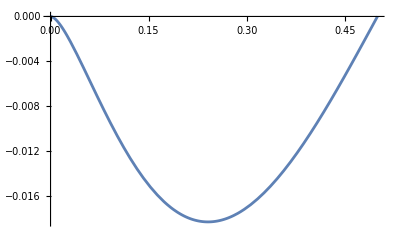

```mathematica
Plot[%554[[1]],{z,0,1/2},WorkingPrecision->30]
```

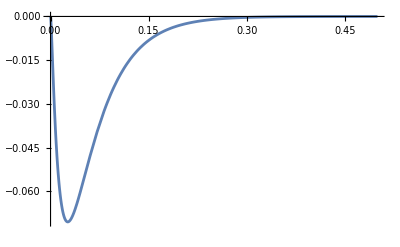

```mathematica
Plot[%554[[10]],{z,0,1/2},WorkingPrecision->30,PlotRange->Full]
```

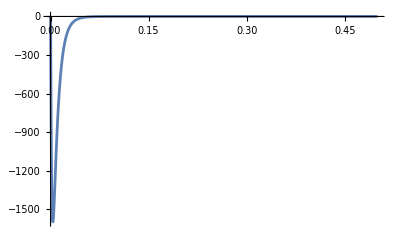

```mathematica
Plot[%554[[-1]],{z,0,1/2},WorkingPrecision->30,PlotRange->Full]
```

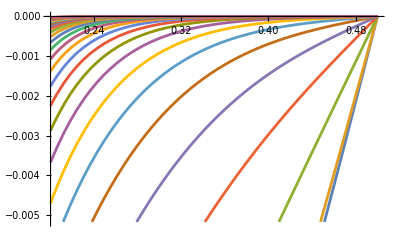

```mathematica
Plot[%554,{z,2/10,1/2},WorkingPrecision->30]
```

```mathematica
Manipulate[Plot[(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),{z,0,1/2}],{Δ[0],2,100}]
```

```mathematica
Manipulate[Plot[z ⅇ^(-(67 Δ[0])/100)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),{z,0,1/2}],{Δ[0],2,100}]
```

```mathematica
fint=Sum[f[i]z^i,{i,1,10}]
```

z f[1]+z^2 f[2]+z^3 f[3]+z^4 f[4]+z^5 f[5]+z^6 f[6]+z^7 f[7]+z^8 f[8]+z^9 f[9]+z^10 f[10]

```mathematica
N[NIntegrate[z^4(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->20/.α->1,{z,0,1/2}],30]
```

-0.326009

```mathematica
N[NIntegrate[z^4(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->2/.α->1,{z,0,1/2}],30]
```

-0.000184764

```mathematica
N[Integrate[ⅇ^(-(α (1/2-z)^2)/1)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->2/.α->1,{z,0,1/2}],30]
```

-0.0201527893730598440668763618688

```mathematica
N[Integrate[ⅇ^(-(α (1/2-z)^2)/1)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->20/.α->10,{z,0,1/2}],30]
```

-9636.09382491425115535446912466

```mathematica
N[Integrate[ⅇ^(-(α (1/2-z)^2)/1)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->2/.α->10,{z,0,1/2}],30]
```

-0.0118031226332966112721320745156

```mathematica
N[Integrate[ⅇ^(-(α (1/2-z)^2)/1)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->20/.α->200,{z,0,1/2}],30]
```

-0.000350929559442121116155162612982

```mathematica
N[Integrate[ⅇ^(-(α (1/2-z)^2)/1)(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->2/.α->200,{z,0,1/2}],30]
```

-0.00100093585953897230366160664184

```mathematica
Table[NIntegrate[ⅇ^(-67/100)(1/2-z)^2(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),{z,0,1/2},WorkingPrecision->30],{Δ[0],2,20,2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9647829813633057023440214149538251826484609094643762406638049754219565260026179×10^-6}. NIntegrate obtained -0.36158161047543780209829519949451066483547715256659314849805835471790340229269725 and 4.4869915552961925450159926253053329318409843915623643140716084347701143342664033×10^-18 for the integral and error estimates.

{-0.00081237942345402150352342271453,-0.00347647818616579732418446627293,-0.0133379339773798603642581608851,-0.0634881097122349368373727487702,-0.361581610475437802098295199495,-2.37159600599746122769810410014,-17.3873688966213243313446229691,-139.325138201323748650933175494,-1199.77443830176830197267472205,-10961.9419845979361990373870954}

```mathematica
(DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,nstates-1}]]/.genBos/.Δσ->1).(N[D[crossingEqResc[nstates],{Table[C[i],{i,0,nstates-1}],1}]/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1,40]//Inverse).(crossingEqResc[nstates]/.C[i_]->0/.zvalsTable[4/10,49/100,nstates-1]/.genBos/.Δσ->1)
```

{-2.0464227977360689403296070755262,-1.161758325819246648731469119698,-0.2631443044514214863509550504107,-0.020720270682875284049844501084,-0.007157948609417794233116897127311}

```mathematica
Eigenvalues[N[matr,40]]
```

{-0.002803547106636375391714237126366048677965,7.56672261042073848472897801644176744091×10^-6,-2.095182791987896423967621874576402986123×10^-8,3.288654761309721171724595493031742699801×10^-11,-1.368252233751812239717139117988591551836×10^-14}

```mathematica
Eigenvectors[N[matr,40]]
```

{{0.6944947112468903452973577995126731300978,0.5486356942892234403651352644306442219277,0.3948722128844874946450019137985943847059,0.2354887084633509767920754474575718480657,0.07278031794277239381762039883598021028134},{0.07616014095417506191132022522354689914948,-0.5081050106035055431455264890919290926256,-0.6649697210681973095992654797180085640881,-0.5127812317432322765395319313845599083481,-0.1757828477520747422335182423575074745894},{-0.01342784096140705783341178587514231891658,0.1337021063118809858333603705465672083786,-0.5422085677046146515637024011532756602793,-0.7654898813562920414019181914324853070149,-0.3193408061988349728704502277806035063524},{-0.002964631160998966336470753712256377818858,0.03426944404675770507453882535698144197015,-0.2506022796260041349812198289774354976426,0.7992774879336280724174947528252008844515,0.5451337550505971380665634959319696352905},{0.0004941825862719884058855460675603780182692,-0.00611737689389421018266618251333414017202,0.05632471686355317235345435886925956020346,-0.3349979337474121133520171402070300251887,0.940513819217301308408904024695229904011}}

```mathematica
%496.Transpose[%496]
```

{{1.,-0.621997516958916695932541412117961738834,-0.353580862490870275901166503395180531476,0.145682474206811265347651090634686983961,0.0087907254972862030899094553265389350258},{-0.621997516958916695932541412117961738834,1.,0.740258384187618843899524465216600469782,-0.356674993611712727857565346553056480513,-0.02785386878879833167864131616983164069},{-0.353580862490870275901166503395180531476,0.740258384187618843899524465216600469782,1.,-0.645421873686669195903684948473792518236,-0.075271198749035614231840129785249891677},{0.145682474206811265347651090634686983961,-0.356674993611712727857565346553056480513,-0.645421873686669195903684948473792518236,1.,0.230623316378750025155077468460416112194},{0.0087907254972862030899094553265389350258,-0.02785386878879833167864131616983164069,-0.075271198749035614231840129785249891677,0.230623316378750025155077468460416112194,1.}}

```mathematica
getLogLine[4/10]
```

-1.8125887901063844779417538168822780730686817252193458093615-0.10447642827326701053410819391963257605636866128956512802551 Δ[0]

```mathematica
1/2Exp[-137/100*10]/(137/100)//N
```

4.09652×10^-7

```mathematica
Table[C[i],{i,0,4}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218}

```mathematica
(N[D[crossingEqResc[10],{Table[C[i],{i,0,9}],1}]/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1,40]//Inverse).{1/5,9/50,4/25,7/50,3/25,1/10,2/25,3/50,1/25,1/50}
```

{-30.9733584984614433093,-287.824347012477705413,-884.30266446703254271,-1878.4718524135930164,-3286.958578745752252,-5258.54199197714665,-6831.0873676154768,-13648.339513595863,-702.827106742096,-45630.292372764748}

```mathematica
DiagonalMatrix[Table[Exp[-Δ[i]*137/100],{i,0,9}]]/.genBos/.Δσ->1
```

{{1/ⅇ^(137/50),0,0,0,0,0,0,0,0,0},{0,1/ⅇ^(137/25),0,0,0,0,0,0,0,0},{0,0,1/ⅇ^(411/50),0,0,0,0,0,0,0},{0,0,0,1/ⅇ^(274/25),0,0,0,0,0,0},{0,0,0,0,1/ⅇ^(137/10),0,0,0,0,0},{0,0,0,0,0,1/ⅇ^(411/25),0,0,0,0},{0,0,0,0,0,0,1/ⅇ^(959/50),0,0,0},{0,0,0,0,0,0,0,1/ⅇ^(548/25),0,0},{0,0,0,0,0,0,0,0,1/ⅇ^(1233/50),0},{0,0,0,0,0,0,0,0,0,1/ⅇ^(137/5)}}

```mathematica
%422.%419/%427
```

{-0.99998,-1.00003,-0.999884,-1.00061,-0.996557,-1.01839,-0.913437,-1.3328,-0.0522905,-2.67363}

```mathematica
Table[C[i],{i,0,9}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218,0.000374239,0.000034998,3.09443×10^-6,2.62255×10^-7,2.15022×10^-8}

```mathematica
(N[D[crossingEq[10],{Table[C[i],{i,0,9}],1}]/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1,40]//Inverse).{1/5,9/50,4/25,7/50,3/25,1/10,2/25,3/50,1/25,1/50}/%427
```

{-0.99998,-1.00003,-0.999884,-1.00061,-0.996557,-1.01839,-0.913437,-1.3328,-0.0522905,-2.67363}

```mathematica
Eigenvectors[matr]
```

{{0.5015082691890675389050498510471655819918,0.4554020858247209383651256536170950348388,0.4080205546903779513527455212997826656194,0.3595043057925550815913097270391555742166,0.3099943613482203977954024283859249417034,0.2596320786758677734046980482101672445988,0.2085590964612737548305475438369114743828,0.1569172838124258201744089657197526243816,0.1048486915682885973551802297152526235851,0.05249550536580427743392591022997097181277},{-0.02754935732117496925558036346138107023038,0.1777388850024367843813844762953923221307,0.3199165632356422760750724737071091965044,0.4055182871931223085119211822440066241519,0.4412530353457946863751038343434362519512,0.4339786778354985208336445566506753454858,0.3906780380082927272508601302207223268599,0.3184362243513417527112441286465563068014,0.224418988191235770069783301667171281704,0.1158518810770148986269555704611517040979},{-0.002436665774152652475628442365994914456173,0.02353221402170115264793146141967778252173,-0.08062910006358889697238055182492211791841,-0.2319828429935727054372994595199548563678,-0.3723376103448660291534454139976876670915,-0.4647909096118477013476581789938605806984,-0.4904204554544910353974592634852460983437,-0.4451007647670169831305413488967046177453,-0.3364226123616327235967225346670701741615,-0.1806937535582340340101731621183386775857},{0.0003163740067400193426824852718458365708325,-0.003555251117314761535863931864084222600914,0.02331928866988947462317331096781370274882,-0.04398862922263094839396359689783457631631,-0.1992125922071649820392517561988779634556,-0.3784736222646390741939797296540728437323,-0.5091020449326568438476172877514168059581,-0.5386225619344148485871388807331628103987,-0.4481444121439002067493665199324186247476,-0.2538660300489268764384867683643076046534},{-0.00005576266644129168341005329664708565971571,0.0006754079970698831624025673955536454115451,-0.005764796057610679423814692302810417440646,0.02772593167813604652543725962409454285557,-0.02536443832689164647003987956737995832197,-0.2045217834308082058699700667234732523523,-0.432911602325332507670153267813710499835,-0.5835347004636057861098027420274482065932,-0.5588567375795332523368253850368804022891,-0.3412902147925173824667111744022755422883},{0.00001260277378776807342793338108057844193435,-0.0001593189775875417832371264632767050217079,0.001567584131470844035077871127125767199925,-0.01073211513110536550590430054454808844997,0.03979806863179751715714153889755419828659,-0.01173670373779857076219095794562641713113,-0.2519924990804236805880790177849017016511,-0.5465819288607602532826567328167237026038,-0.658175745771957958581393919727598631024,-0.4502370103507343458989101715480476587833},{-3.453326141724583833581878947729537554039×10^-6,0.00004483955908111943259816954233649541262708,-0.0004814073538452833517627069927124560145461,0.004006118039145437040544233989569093568149,-0.02289604029170967081223855538390735737614,0.06955766316284891305707349467699324719211,-0.0005800187038551295901154254921755692100891,-0.3732030778620663486621573348395411922913,-0.7128115133404826372092984618629012064602,-0.589270814463794057541992876891018374784},{1.056914238000533783042808365981205905956×10^-6,-0.00001397071339622453403174795642282300544558,0.0001589244299455385529176537299086643095127,-0.00149697814863690615131674225240126790273,0.01084357266869268773338556982702246183311,-0.05416675716027007321574689934680729359413,0.1467921176292881947006151317839466071863,-0.01742478627096188226856852090854607249848,-0.63082512637267945498991722278711867248,-0.7597066696534148456490098020112800916412},{3.070291771181213241690885150472234510704×10^-7,-4.109276066139643645792540671565677894868×10^-6,0.00004866674095495436255652430020811607391276,-0.0004988723576664941282741132723526571982156,0.004206796877230907737769404303590997402941,-0.02742754586791814525462802991515687860639,0.1260402303924550919658851038521261420254,-0.3375631595813990578370108638530237192882,0.2140343683924278097750967030526596363226,0.9075153134198507195384487606540666377395},{-5.776162916801657539377601793073609335336×10^-8,7.799580935356930466769942754945269805508×10^-7,-9.505949429456993742844951587588688601823×10^-6,0.0001034317951484317668788137072622745474716,-0.00096767193989082728804261739216722670924,0.007469906053077977307167210610518720391229,-0.04524722138384828643757929561845739862736,0.2002843161882619864932064980452442737695,-0.5732424103500333662136009543500037512778,0.7932056946010846830210580243329052121967}}

```mathematica
Eigenvalues[matr]
```

{-0.002850527501209612610476454407278499960625,4.520911728256104796350468406395026558297×10^-6,-1.133317301824072823193821958379570639705×10^-8,3.270636047280731318271304024879917543724×10^-11,-9.279579490787002488772102986288718951213×10^-14,2.290502607274680417640782949403543228423×10^-16,-4.341612610511290278458912726951700447334×10^-19,5.428273105295028860147418136016159160657×10^-22,-3.618453768725187749905003661027951082569×10^-25,8.667749231894127236174993322536568899576×10^-29}

```mathematica
Solve[crossingEqResc[9]==0/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1,Table[C[i],{i,0,9}]]
```

{}

```mathematica
getAvCsResc[nstates_,deltas_,zmin_,zmax_,dσ_,WP_]:=Module[{cs,eqs},eqs=crossingEqResc[nstates-1]/.C[j_]-> c[j]/.Δσ->dσ/.zvalsTable[zmin,zmax,nstates*10-1];cs=Table[N[c[i]Exp[-deltas[[i+1]]*137/100],WP],{i,0,nstates-1}]/.solns[Table[Δ[i]->deltas[[i+1]],{i,0,nstates-1}],eqs,nstates,WP];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
solns[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=Range[Length[eqs]];Table[Solve[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP]//Chop,{i,nstates}],WorkingPrecision->WP][[1]],{j,0,9}]];
```

```mathematica
solns[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=Range[Length[eqs]];Table[Solve[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP]//Chop,{i,nstates}],WorkingPrecision->WP][[1]],{j,0,9}]];
```

```mathematica
solnsRand[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=RandomSample[Range[Length[eqs]],Length[eqs]];Table[Solve[Join[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP],{i,nstates}],Table[N[c[i]>=0,WP],{i,0,nstates-1}]]][[1]],{j,0,9}]];
```

```mathematica
getAvCs[nstates_,deltas_,zmin_,zmax_,dσ_,WP_]:=Module[{cs,eqs},eqs=crossingEq[nstates-1]/.C[j_]-> c[j]/.Δσ->dσ/.zvalsTable[zmin,zmax,nstates*10-1];cs=Table[N[c[i],WP],{i,0,nstates-1}]/.solns[Table[Δ[i]->deltas[[i+1]],{i,0,nstates-1}],eqs,nstates,WP];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
getAvCsFn[nstates_,deltas_,zmin_,zmax_,f_,dσ_,WP_]:=Module[{cs,eqs},eqs=crossingEqFn[nstates-1,f]/.C[j_]-> c[j]/.Δσ->dσ/.zvalsTable[zmin,zmax,nstates*10-1];cs=Table[N[c[i],WP],{i,0,nstates-1}]/.solns[Table[Δ[i]->deltas[[i+1]],{i,0,nstates-1}],eqs,nstates,WP];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
Table[zvalsTable[-1+n del,-1+(n+1)del,nstates]/.del->2/(nstates+1),{n,0,nstates}]//Transpose
```

{{{z→-1},{z→-3/5},{z→-1/5},{z→1/5},{z→3/5}},{{z→-9/10},{z→-1/2},{z→-1/10},{z→3/10},{z→7/10}},{{z→-4/5},{z→-2/5},{z→0},{z→2/5},{z→4/5}},{{z→-7/10},{z→-3/10},{z→1/10},{z→1/2},{z→9/10}},{{z→-3/5},{z→-1/5},{z→1/5},{z→3/5},{z→1}}}

```mathematica
getAvCsToy[nstates_,deltasR_,zmin_,zmax_,dσ_,WP_]:=Module[{},eqs=crossingEqToy[nstates-1]/.C[j_]-> c[j]/.Δσ->dσ/.deltasR/.zvalsTable[zmin,zmax,nstates*10-1];cs=Table[N[c[i],WP],{i,0,nstates-1}]/.solnsRand[{},eqs,nstates,WP];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
getAvCsToy[nstates_,deltasR_,zmin_,zmax_,dσ_,WP_]:=Module[{},eqs=crossingEqToy[nstates-1]/.C[j_]-> c[j]/.Δσ->dσ/.deltasR/.zvalsTable[zmin,zmax,nstates*10-1];cs=Table[N[c[i],WP],{i,0,nstates-1}]/.solns[{},eqs,nstates,WP];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
Solve[eqs[[;;10]]==0]
```

{{c[0]→1,c[1]→1,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→0,c[7]→0,c[8]→0,c[9]→0}}

```mathematica
Solve[crossingEqToy2[6]==0/.{J[i_]->i,x->z}/.zvalsTable[-99/100,99/100,6]]//N
```

{{C[0]→0.537144,C[1]→0.,C[2]→-0.544334,C[3]→0.,C[4]→0.262691,C[5]→0.,C[6]→-0.294976}}

```mathematica
D[crossingEqToy2[2],C[1]]/.J[1]->1
```

-x

```mathematica
zvalsTable[-9/10,9/10,nstates*10-1][[;;10]]//N
```

{{z→-0.9},{z→-0.881818},{z→-0.863636},{z→-0.845455},{z→-0.827273},{z→-0.809091},{z→-0.790909},{z→-0.772727},{z→-0.754545},{z→-0.736364}}

```mathematica
Solve[eqs[[1;;4]]==0]//N
```

{{c[0.]→0.932398,c[1.]→0.341249,c[2.]→0.0868289,c[3.]→0.011362}}

```mathematica
Solve[eqs[[5;;8]]==0]//N
```

{{c[0.]→0.942213,c[1.]→0.361117,c[2.]→0.100682,c[3.]→0.0156789}}

```mathematica
Solve[eqs[[1+n*4;;4+n*4]]==0/.n->8]//N
```

Part::span: 1+4 n;;4+4 n is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

{{c[0.]→-0.237217,c[1.]→3.05746,c[2.]→-1.70287,c[3.]→0.802203}}

```mathematica
Solve[eqs[[1;;5]]==0]//N
```

{{c[0.]→0.952207,c[1.]→0.383511,c[2.]→0.121311,c[3.]→0.0262236,c[4.]→0.00288956}}

```mathematica
eqs//N
```

{0.69843-1. c[0.]+0.8 c[1.]-0.46 c[2.]+0.08 c[3.],0.705976-1. c[0.]+0.75641 c[1.]-0.358235 c[2.]-0.0526528 c[3.],0.713772-1. c[0.]+0.712821 c[1.]-0.26217 c[2.]-0.163747 c[3.],0.721832-1. c[0.]+0.669231 c[1.]-0.171805 c[2.]-0.254525 c[3.],0.730172-1. c[0.]+0.625641 c[1.]-0.08714 c[2.]-0.32623 c[3.],0.738807-1. c[0.]+0.582051 c[1.]-0.00817554 c[2.]-0.380103 c[3.],0.747757-1. c[0.]+0.538462 c[1.]+0.0650888 c[2.]-0.417387 c[3.],0.757039-1. c[0.]+0.494872 c[1.]+0.132653 c[2.]-0.439325 c[3.],0.766676-1. c[0.]+0.451282 c[1.]+0.194517 c[2.]-0.447158 c[3.],0.776691-1. c[0.]+0.407692 c[1.]+0.25068 c[2.]-0.442129 c[3.],0.787108-1. c[0.]+0.364103 c[1.]+0.301144 c[2.]-0.425481 c[3.],0.797957-1. c[0.]+0.320513 c[1.]+0.345907 c[2.]-0.398455 c[3.],0.809266-1. c[0.]+0.276923 c[1.]+0.38497 c[2.]-0.362294 c[3.],0.821071-1. c[0.]+0.233333 c[1.]+0.418333 c[2.]-0.318241 c[3.],0.833408-1. c[0.]+0.189744 c[1.]+0.445996 c[2.]-0.267537 c[3.],0.846318-1. c[0.]+0.146154 c[1.]+0.467959 c[2.]-0.211426 c[3.],0.859847-1. c[0.]+0.102564 c[1.]+0.484221 c[2.]-0.151149 c[3.],0.874046-1. c[0.]+0.0589744 c[1.]+0.494783 c[2.]-0.0879488 c[3.],0.888973-1. c[0.]+0.0153846 c[1.]+0.499645 c[2.]-0.0230678 c[3.],0.904692-1. c[0.]-0.0282051 c[1.]+0.498807 c[2.]+0.0422516 c[3.],0.921276-1. c[0.]-0.0717949 c[1.]+0.492268 c[2.]+0.106767 c[3.],0.938806-1. c[0.]-0.115385 c[1.]+0.48003 c[2.]+0.169236 c[3.],0.957376-1. c[0.]-0.158974 c[1.]+0.462091 c[2.]+0.228417 c[3.],0.977094-1. c[0.]-0.202564 c[1.]+0.438452 c[2.]+0.283067 c[3.],0.998082-1. c[0.]-0.246154 c[1.]+0.409112 c[2.]+0.331944 c[3.],1.02048-1. c[0.]-0.289744 c[1.]+0.374073 c[2.]+0.373804 c[3.],1.04447-1. c[0.]-0.333333 c[1.]+0.333333 c[2.]+0.407407 c[3.],1.07022-1. c[0.]-0.376923 c[1.]+0.286893 c[2.]+0.43151 c[3.],1.09798-1. c[0.]-0.420513 c[1.]+0.234753 c[2.]+0.44487 c[3.],1.12802-1. c[0.]-0.464103 c[1.]+0.176913 c[2.]+0.446245 c[3.],1.16067-1. c[0.]-0.507692 c[1.]+0.113373 c[2.]+0.434392 c[3.],1.19632-1. c[0.]-0.551282 c[1.]+0.0441321 c[2.]+0.40807 c[3.],1.23548-1. c[0.]-0.594872 c[1.]-0.0308087 c[2.]+0.366036 c[3.],1.27876-1. c[0.]-0.638462 c[1.]-0.11145 c[2.]+0.307047 c[3.],1.32692-1. c[0.]-0.682051 c[1.]-0.197791 c[2.]+0.229862 c[3.],1.38097-1. c[0.]-0.725641 c[1.]-0.289832 c[2.]+0.133237 c[3.],1.44222-1. c[0.]-0.769231 c[1.]-0.387574 c[2.]+0.0159308 c[3.],1.51241-1. c[0.]-0.812821 c[1.]-0.491016 c[2.]-0.123299 c[3.],1.59396-1. c[0.]-0.85641 c[1.]-0.600158 c[2.]-0.285695 c[3.],1.69031-1. c[0.]-0.9 c[1.]-0.715 c[2.]-0.4725 c[3.]}

```mathematica
getAvCsToy[6,{J[i_]->i,x->z,t->1/2},-9/10,9/10,1,40]
```

{{-5.9858975451509298546904599530583991,20.44996910222487020784960351588636},{16.171797248345019418357182373584222,45.974217430274426644068716388466609},{-14.312257050132997345365999443395112,42.172393290071533804829842324926625},{8.0523582548428962239926039099789563,22.908373743513404399168450062608064},{-2.5622814580804448423072782068385864,7.2824689768924835521210761351609499},{0.41965801314530712327472823781005096,1.1047023463756573782698789676536691}}

```mathematica
Manipulate[Solve[%228==0],{a1,0,10},{a3,0,10}]
```

```mathematica
D[%228,a3,c[1.`40.]]
```

{-0.658407263729180225149982706218694713721,-0.293634072172535953305044650241914399584,0.00424253518228287641955860375286075400313,0.23941872711789852164191759314906059744,0.415184814230831262124902693939075319371,0.533986213754810050843345869026927588671,0.597468918798388121870951563369294246155}

```mathematica
D[%228,a1,c[1.`40.]]
```

{0.842745323435009214897118062980475297592,0.8406282365845435019984600887427735821149,0.8381072233889892283453762664338485941659,0.8355848889033930822559032783849454831548,0.8333790908044261806956681559179187991316,0.8317273881638458277897225520731844024474,0.8307903478731598923924006962624909956063}

```mathematica
Solve[%==0/.a1->1/10/.a3->1/10]
```

{{c[0]→2014.1444552466240505113484429239,c[1.]→-1953.8715764839569691075831802286,c[2.]→1070.7093909121469373943381194795,c[3.]→-412.53932254828181015885334369773,c[4.]→114.27083711972735433328642991655,c[5.]→-20.786383227155261544427015354934,c[6.]→1.9583067612075696157971373061524}}

```mathematica
D[%330,a1]
```

{-2.+0.3465900935383561327646635250245476524931 c[0]+0.6655805117134977205081520198268981064079 c[1.]+0.842745323435009214897118062980475297592 c[2.]+0.963692220910027084367047821739023248959 c[3.]+1.056968722463128541760056591517342668863 c[4.]+1.130678491496622697990961834902865097128 c[5.]+1.186713098216897766146968012986136312276 c[6.],-2.+0.3644132706368438762141613400404354812049 c[0]+0.688265288032826896283873090491604406764 c[1.]+0.8406282365845435019984600887427735821149 c[2.]+0.9163340515303987994966704032161501081896 c[3.]+0.9538131135595577281807967062504597454987 c[4.]+0.9684035473014929641057131480212421548306 c[5.]+0.9665905908180519573880503138372717501016 c[6.],-2.+0.379404684038016828378232698073916064714 c[0]+0.7070936998096288705043649274998093003932 c[1.]+0.8381072233889892283453762664338485941659 c[2.]+0.8759022700981557518916605703533341920583 c[3.]+0.8683272562344679196933545686422636575336 c[4.]+0.8376125842531169548409860757313688562479 c[5.]+0.7944360518069516875632339968982737069505 c[6.],-2.+0.391532602067895329881530222634377225434 c[0]+0.7221598093331865329565509274645003710454 c[1.]+0.8355848889033930822559032783849454831548 c[2.]+0.8428197427971018830366339461601231901238 c[3.]+0.800047700224521942354526141688276404437 c[4.]+0.7355544314431824410509823172657307089108 c[5.]+0.6635322910303526174950668742489981262088 c[6.],-2.+0.4007721890996804373720167172080178292912 c[0]+0.7335395246484498714800571090421144448831 c[1.]+0.8333790908044261806956681559179187991316 c[2.]+0.8174039364152021282775029310989256128384 c[3.]+0.7485658695001553244850427835732248409397 c[4.]+0.6600233061449221795642826720422377379385 c[5.]+0.5686755913606312859614438748224981980398 c[6.],-2.+0.4071050080683324577250080862266223702413 c[0]+0.741290550042375088523023923844329782034 c[1.]+0.8317273881638458277897225520731844024474 c[2.]+0.7998824791925540455427999333090136518993 c[3.]+0.713551661474473570514907025862841971641 c[4.]+0.6093523405840339978518479584956774362376 c[5.]+0.506037898799523299648996854172559796302 c[6.],-2.+0.4105186575124382500750797734191470409962 c[0]+0.7454523684953372629719809525268058839456 c[1.]+0.8307903478731598923924006962624909956063 c[2.]+0.7904044805191950780701908432552834037019 c[3.]+0.6947699121122857152550616864970490250748 c[4.]+0.5824064335224093858335922650100329008842 c[5.]+0.4730627996734549269823012059355493063668 c[6.]}

```mathematica
Solve[%330==0/.a1->0/.a3->-1/100]
```

{{c[0]→2014.139517013439440983362761328,c[1.]→-1953.866799559304096114401384445,c[2.]→1070.706806181413004875138813909,c[3.]→-412.5383506137639368118625233176,c[4.]→114.2705808177332988133982707389,c[5.]→-20.78634008336082044766477184326,c[6.]→1.958303260720231390691944941349}}

```mathematica
Solve[%330==0/.a1->0/.a3->-1/100]
```

```mathematica
nstates=10;
```

```mathematica
crossingEq[nstates]+a3 D[crossingEq[nstates],{z,3}]/3!/.Δσ->1/.zvalsTable[4/10,49/100,6],40]
```

```mathematica
N[%329/.Δσ->1/.Δ[i_]->2+i/.zvalsTable[4/10,49/100,6],40]
```

{0.2-0.03895785005994784311545916229670568270135 c[0]-0.0719556211604710011943237511934083572992 c[1.]-0.08354808187038175299661538021718641183191 c[2.]-0.08477630585395761357570397984965072192389 c[3.]-0.0811997256233707836363595147007944329195 c[4.]-0.07559774137559678374913468196189766316553 c[5.]-0.06934164116642210009747057000010734234858 c[6.]+a1 (-2.+0.3465900935383561327646635250245476524931 c[0]+0.6655805117134977205081520198268981064079 c[1.]+0.842745323435009214897118062980475297592 c[2.]+0.963692220910027084367047821739023248959 c[3.]+1.056968722463128541760056591517342668863 c[4.]+1.130678491496622697990961834902865097128 c[5.]+1.186713098216897766146968012986136312276 c[6.])+0.1666666666666666666666666666666666666667 a3 (-12.41414010526827717302351350294423153919 c[0]-17.63104788219507029171303536439232688963 c[1.]-3.950443582375081350899896237312168282325 c[2.]+28.4013687137151793129897463437757258422 c[3.]+80.69867769570423245608289055269588021166 c[4.]+154.3912175650061739616348751885655331125 c[5.]+249.8363176355986287207875345444358271639 c[6.]),0.17-0.03362180785756622227581667722533702021563 c[0]-0.06179689125642322092475568958147872258929 c[1.]-0.07092198857918917193592998400246345492686 c[2.]-0.07068445540459969082512776415875594257792 c[3.]-0.06614125197307808541597004099932118758087 c[4.]-0.05989591764783430163208199319177658711847 c[5.]+a1 (-2.+0.3644132706368438762141613400404354812049 c[0]+0.688265288032826896283873090491604406764 c[1.]+0.8406282365845435019984600887427735821149 c[2.]+0.9163340515303987994966704032161501081896 c[3.]+0.9538131135595577281807967062504597454987 c[4.]+0.9684035473014929641057131480212421548306 c[5.]+0.9665905908180519573880503138372717501016 c[6.])-0.05325666681451379340177954675670671454356 c[6.]+0.1666666666666666666666666666666666666667 a3 (-12.58840255142074770710636937609905288254 c[0]-17.13270911067896859622799118505931365786 c[1.]-1.761804433035215719830267901451486397503 c[2.]+30.83025997285454203561063071363596499903 c[3.]+78.52338997639443705357048631261200550649 c[4.]+139.7253584369039569454288976147993649933 c[5.]+212.5684819141145171282342549665188903754 c[6.]),0.14-0.02803961201349866346790401632953135653136 c[0]-0.05132694133242504017392501206358319550438 c[1.]-0.05833123936072326574205913146690077750166 c[2.]-0.05725163151396867174555258746441143477913 c[3.]-0.0524969874098053594946271247374143138185 c[4.]-0.04638830658430057323001854902773946991844 c[5.]+a1 (-2.+0.379404684038016828378232698073916064714 c[0]+0.7070936998096288705043649274998093003932 c[1.]+0.8381072233889892283453762664338485941659 c[2.]+0.8759022700981557518916605703533341920583 c[3.]+0.8683272562344679196933545686422636575336 c[4.]+0.8376125842531169548409860757313688562479 c[5.]+0.7944360518069516875632339968982737069505 c[6.])-0.04010436379937832243370856352239606524717 c[6.]+0.1666666666666666666666666666666666666667 a3 (-12.72919271197064990688630721367867186731 c[0]-16.71461682965863849585602667195617934617 c[1.]+0.02545521109369725851735162251716452401879 c[2.]+32.70215153453069004618660404481558533193 c[3.]+76.45169207738667452237454682062591450268 c[4.]+127.499218202905248033400214885890223515 c[5.]+182.7779265969249093608925645863632695295 c[6.]),0.11-0.02225398595961944884555690122138721555682 c[0]-0.0406028887465973112774478377249785136669 c[1.]-0.04577876438364020336930822293763520927207 c[2.]-0.04437062355967387057382322735636110516973 c[3.]-0.04000541209981418661057783093916556624714 c[4.]-0.03462396703356692474170982024695792505504 c[5.]+a1 (-2.+0.391532602067895329881530222634377225434 c[0]+0.7221598093331865329565509274645003710454 c[1.]+0.8355848889033930822559032783849454831548 c[2.]+0.8428197427971018830366339461601231901238 c[3.]+0.800047700224521942354526141688276404437 c[4.]+0.7355544314431824410509823172657307089108 c[5.]+0.6635322910303526174950668742489981262088 c[6.])-0.02921758293976091207404356051983785801859 c[6.]+0.1666666666666666666666666666666666666667 a3 (-12.8393898931592784736887904368813830382 c[0]-16.37723060900009370005981914166033891637 c[1.]+1.436512362707391129851505558894363584639 c[2.]+34.10738060428830226781145934428346766099 c[3.]+74.62714446098426312485608250973180734441 c[4.]+117.6982761152264937626584653895975920446 c[5.]+159.7013268503833691765999388097795352707 c[6.]),0.08-0.01630807667022560645212955688708342482873 c[0]-0.02968057598890042651431327893883229019726 c[1.]-0.0332620966511895495374425382518934666129 c[2.]-0.03192869073601554634407713990580404645824 c[3.]-0.02841158099549736045511849163912539908707 c[4.]-0.02418912833311144873669594092259020586973 c[5.]+a1 (-2.+0.4007721890996804373720167172080178292912 c[0]+0.7335395246484498714800571090421144448831 c[1.]+0.8333790908044261806956681559179187991316 c[2.]+0.8174039364152021282775029310989256128384 c[3.]+0.7485658695001553244850427835732248409397 c[4.]+0.6600233061449221795642826720422377379385 c[5.]+0.5686755913606312859614438748224981980398 c[6.])-0.02001838836868968635268545690284166637315 c[6.]+0.1666666666666666666666666666666666666667 a3 (-12.92119859409362613721526272821418441986 c[0]-16.12076143797988364125177355061568811456 c[1.]+2.491108885384987572749416163634451916228 c[2.]+35.11488986871641979907392235236926730803 c[3.]+73.15398394462506184150820252477618008232 c[4.]+110.2927146706354900402750487578670964357 c[5.]+142.72625449636409352136822184641446758 c[6.]),0.05-0.01024535513047366203123665901153454112669 c[0]-0.01861484341958736918308436080760031247735 c[1.]-0.02077460837157085821277028456700038018852 c[2.]-0.01980902071028235777918619546898639590855 c[3.]-0.01746611384012345159814644787895283410535 c[4.]-0.01469905565171062508048557914176628100537 c[5.]+a1 (-2.+0.4071050080683324577250080862266223702413 c[0]+0.741290550042375088523023923844329782034 c[1.]+0.8317273881638458277897225520731844024474 c[2.]+0.7998824791925540455427999333090136518993 c[3.]+0.713551661474473570514907025862841971641 c[4.]+0.6093523405840339978518479584956774362376 c[5.]+0.506037898799523299648996854172559796302 c[6.])-0.01199643144241572268448771504318450348186 c[6.]+0.1666666666666666666666666666666666666667 a3 (-12.97622731512159549902299918932958149946 c[0]-15.94528109932900098448927458411028724974 c[1.]+3.203917282528860305060075214161565532023 c[2.]+35.77483379815324635253251491401706082684 c[3.]+72.10493577364575173426243844196942753093 c[4.]+105.2500691797985607384016149442156193983 c[5.]+131.3905775022852207787425897344368753573 c[6.]),0.02-0.004109523239309616699690881860375339398021 c[0]-0.007459802484954135753347350324565035115065 c[1.]-0.00830668925398267831185252388459798184301 c[2.]-0.007891987301016634585074310455563264642421 c[3.]-0.006923886542219629881420295588693663581184 c[4.]-0.005790020414985806851288746990605204407836 c[5.]+a1 (-2.+0.4105186575124382500750797734191470409962 c[0]+0.7454523684953372629719809525268058839456 c[1.]+0.8307903478731598923924006962624909956063 c[2.]+0.7904044805191950780701908432552834037019 c[3.]+0.6947699121122857152550616864970490250748 c[4.]+0.5824064335224093858335922650100329008842 c[5.]+0.4730627996734549269823012059355493063668 c[6.])-0.004689137942549267904164281881765691162159 c[6.]+0.1666666666666666666666666666666666666667 a3 (-13.00554448639893657076411510846062026221 c[0]-15.85079704714659495186213847405675027039 c[1.]+3.584813512790328731225709380215765476932 c[2.]+36.12044689732890379649318347714039650405 c[3.]+71.52666992652498993434729315934679361241 c[4.]+102.5436070917369986461592289971345344939 c[5.]+125.3802368787055478725258790092661742086 c[6.])}

```mathematica
D[%228/.a1->1/10/.a3->1/10,c[1.`40.]]
```

{-0.08354808187038175299661538021718641183191,-0.07092198857918917193592998400246345492686,-0.05833123936072326574205913146690077750166,-0.04577876438364020336930822293763520927207,-0.0332620966511895495374425382518934666129,-0.02077460837157085821277028456700038018852,-0.00830668925398267831185252388459798184301}

```mathematica
Solve[%228==0/.a1->1/10/.a3->1/10]
```

{{c[0]→2.003343104023009313588231584720487,c[1.]→1.197142929930164538075329089489299,c[2.]→0.2402030825336456017639367201045133,c[3.]→0.03133865091553271668932331801990987,c[4.]→0.004321820555640955092892705860033816,c[5.]→0.0001637391017036355531679844727901443,c[6.]→0.00007800943909457614889559622716264498}}

```mathematica
crossingEq[6]/.Δσ->1/.Δ[i_]->2+i
```

```mathematica
N[%/.zvalsTable[4/10,49/100,6],40]
```

```mathematica
N[%/.zvalsTable[4/10,49/100,6],40]
```

```mathematica
N[D[crossingEq[6],{z,1}]/.z->1/2/.C[i_]->c[i]/.genBos/.Δσ->1,30]
```

-2.+0.411169166403281434966072712509 c[0]+0.830608093652772485792835050226 c[1.]+0.691198210712458438845802154126 c[2.]+0.466841186406707388590442816495 c[3.]+0.286426715453386666832006214856 c[4.]+0.166248807815529297876753716205 c[5.]+0.0930649071467420530136110125139 c[6.]

```mathematica
Table[D[crossingEq[6],z,C[i]]/.genBos/.Δσ->1//Simplify,{i,0,10}]
```

{(6 (2 (-1+z)^3 (-1-z+z^2) Log[1-z]+z (2-3 z+2 z^2-z^3+2 z^2 (1+z-z^2) Log[z])))/((-1+z)^2 z^2),(140 (6 (-1+z)^5 (-30+40 z-6 z^2-6 z^3+z^4) Log[1-z]+z (180-1050 z+2526 z^2-3161 z^3+2090 z^4-384 z^5-268 z^6+67 z^7-6 z^4 (-1-14 z-18 z^2+2 z^3+z^4) Log[z])))/(3 (-1+z)^4 z^4),1/(5 (-1+z)^6 z^6)924 (30 (-1+z)^7 (-630+1638 z-1470 z^2+490 z^3-15 z^4-15 z^5+z^6) Log[1-z]+z (18900-171990 z+700560 z^2-1680105 z^3+2622510 z^4-2775448 z^5+2005008 z^6-959595 z^7+288710 z^8-40890 z^9-9192 z^10+1532 z^11-30 z^6 (-1-39 z-225 z^2-300 z^3-75 z^4+9 z^5+z^6) Log[z])),1/(7 (-1+z)^8 z^8)20592 (35 (-1+z)^9 (-12012+44616 z-65604 z^2+48048 z^3-17850 z^4+2856 z^5-28 z^6-28 z^7+z^8) Log[1-z]+z (420420-5135130 z+28952770 z^2-99812405 z^3+234868529 z^4-398673128 z^5+502788930 z^6-477798556 z^7+342982693 z^8-184380420 z^9+72668260 z^10-19923575 z^11+3481086 z^12-408338 z^13-35584 z^14+4448 z^15-35 z^8 (-1-76 z-980 z^2-3724 z^3-4900 z^4-2156 z^5-196 z^6+20 z^7+z^8) Log[z])),1/(63 (-1+z)^10 z^10)92378 (1260 (-1+z)^11 (-218790+1045330 z-2097810 z^2+2290860 z^3-1471470 z^4+558558 z^5-117810 z^6+11220 z^7-45 z^8-45 z^9+z^10) Log[1-z]+z (275675400-4211707500 z+30210780600 z^2-135124039050 z^3+422067926280 z^4-977073467370 z^5+1735999270170 z^6-2418364068285 z^7+2674911759900 z^8-2363635608281 z^9+1669743678860 z^10-938755560645 z^11+415700232150 z^12-142350087660 z^13+36686672292 z^14-6752607465 z^15+747192750 z^16-73270965 z^17-3079090 z^18+307909 z^19-1260 z^10 (-1-125 z-2835 z^2-20880 z^3-61740 z^4-79380 z^5-44100 z^6-9360 z^7-405 z^8+35 z^9+z^10) Log[z])),2 (1-z) z ((-1+z)^11 Hypergeometric2F1[12,12,24,1-z]+6 (-1+z)^10 z Hypergeometric2F1[12,12,24,1-z]-6 (-1+z) z^10 Hypergeometric2F1[12,12,24,z]-z^11 Hypergeometric2F1[12,12,24,z]-3 (-1+z)^11 z Hypergeometric2F1[13,13,25,1-z]-3 (-1+z) z^11 Hypergeometric2F1[13,13,25,z]),(1-z) z (2 (-1+z)^13 Hypergeometric2F1[14,14,28,1-z]+14 (-1+z)^12 z Hypergeometric2F1[14,14,28,1-z]-14 (-1+z) z^12 Hypergeometric2F1[14,14,28,z]-2 z^13 Hypergeometric2F1[14,14,28,z]-7 (-1+z)^13 z Hypergeometric2F1[15,15,29,1-z]-7 (-1+z) z^13 Hypergeometric2F1[15,15,29,z]),0,0,0,0}

```mathematica
D[crossingEq[6],z,C[0]]/.Δσ->1/.Δ[0]->x//Simplify
```

(1-z)^(-1+x) z (-2+(2+x) z) Hypergeometric2F1[x,x,2 x,1-z]+(-1+z) z^(-1+x) (x (-1+z)+2 z) Hypergeometric2F1[x,x,2 x,z]+1/2 x ((1-z)^x z^2 Hypergeometric2F1[1+x,1+x,1+2 x,1-z]+(-1+z)^2 z^x Hypergeometric2F1[1+x,1+x,1+2 x,z])

```mathematica
Table[D[crossingEq[6],{z,n},C[0]]/n!/.Δσ->1/.Δ[0]->x/.n->1/.z->1/2//Simplify,{n,1,9,2}]
```

{2^(-2-x) (4 (-2+x) Hypergeometric2F1[x,x,2 x,1/2]+x Hypergeometric2F1[1+x,1+x,1+2 x,1/2]),1/(3 (1+2 x))2^(-4-x) x (32 (12+15 x-17 x^2+2 x^3) Hypergeometric2F1[x,x,2 x,1/2]+(52+16 x-147 x^2+49 x^3) Hypergeometric2F1[1+x,1+x,1+2 x,1/2]+8 (-2+x) (1+x)^2 Hypergeometric2F1[2+x,2+x,2+2 x,1/2]),1/(15 (3+8 x+4 x^2))2^(-7-x) x (256 (372+332 x-919 x^2-20 x^3+303 x^4-72 x^5+4 x^6) Hypergeometric2F1[x,x,2 x,1/2]+(288-31872 x-41126 x^2+63775 x^3+25397 x^4-15343 x^5+1281 x^6) Hypergeometric2F1[1+x,1+x,1+2 x,1/2]+4 (1+x) (48 x (30+23 x-22 x^2-13 x^3+2 x^4) Hypergeometric2F1[2+x,2+x,2+2 x,1/2]+(2+x)^2 (4 (18-9 x-5 x^2+6 x^3) Hypergeometric2F1[3+x,3+x,3+2 x,1/2]+3 (-2+x) (3+x)^2 Hypergeometric2F1[4+x,4+x,4+2 x,1/2]))),1/(315 (1+2 x) (3+2 x) (5+2 x))2^(-9-x) x (2048 (51120+41268 x-137852 x^2+2113 x^3+61719 x^4-15351 x^5-4983 x^6+2202 x^7-244 x^8+8 x^9) Hypergeometric2F1[x,x,2 x,1/2]+(86400-31345920 x-31876776 x^2+78513700 x^3+15208074 x^4-34604073 x^5+2273706 x^6+3419700 x^7-645084 x^8+28673 x^9) Hypergeometric2F1[1+x,1+x,1+2 x,1/2]+8 (1+x) (672 x (1860+544 x-2615 x^2-639 x^3+815 x^4+91 x^5-60 x^6+4 x^7) Hypergeometric2F1[2+x,2+x,2+2 x,1/2]+(2+x) (280 x (-1020-188 x+973 x^2+364 x^3-101 x^4-32 x^5+4 x^6) Hypergeometric2F1[3+x,3+x,3+2 x,1/2]+(3+x)^2 (20 x (800+90 x-337 x^2-63 x^3+14 x^4) Hypergeometric2F1[4+x,4+x,4+2 x,1/2]+(4+x)^2 (3 (70-87 x-11 x^2+14 x^3) Hypergeometric2F1[5+x,5+x,5+2 x,1/2]+2 (-2+x) (5+x)^2 Hypergeometric2F1[6+x,6+x,6+2 x,1/2]))))),1/(2835 (1+2 x) (3+2 x) (5+2 x) (7+2 x))2^(-13-x) x (16384 (19202400+14833080 x-53668572 x^2+1631762 x^3+26889217 x^4-6957908 x^5-3297142 x^6+1444314 x^7-23703 x^8-64112 x^9+11384 x^10-736 x^11+16 x^12) Hypergeometric2F1[x,x,2 x,1/2]+(67737600-89883279360 x-82536776736 x^2+239786632616 x^3+27578267740 x^4-121734059666 x^5+14822039759 x^6+17470217226 x^7-4200077265 x^8-478908254 x^9+226199237 x^10-21233602 x^11+589825 x^12) Hypergeometric2F1[1+x,1+x,1+2 x,1/2]+4 (1+x) (18432 x (357840+33276 x-557864 x^2-27613 x^3+230572 x^4-8904 x^5-31794 x^6+3453 x^7+1238 x^8-212 x^9+8 x^10) Hypergeometric2F1[2+x,2+x,2+2 x,1/2]+(2+x) (10752 x (-123480+24108 x+141050 x^2-815 x^3-43605 x^4-1791 x^5+4575 x^6+90 x^7-140 x^8+8 x^9) Hypergeometric2F1[3+x,3+x,3+2 x,1/2]+(3+x) (8064 x (26040-6644 x-23834 x^2-1439 x^3+5231 x^4+919 x^5-241 x^6-36 x^7+4 x^8) Hypergeometric2F1[4+x,4+x,4+2 x,1/2]+(4+x)^2 (2016 x (-3570+1297 x+2335 x^2+163 x^3-209 x^4-20 x^5+4 x^6) Hypergeometric2F1[5+x,5+x,5+2 x,1/2]+(5+x)^2 (224 x (714-125 x-220 x^2-15 x^3+6 x^4) Hypergeometric2F1[6+x,6+x,6+2 x,1/2]+(6+x)^2 (8 (126-167 x+5 x^2+18 x^3) Hypergeometric2F1[7+x,7+x,7+2 x,1/2]+5 (-2+x) (7+x)^2 Hypergeometric2F1[8+x,8+x,8+2 x,1/2])))))))}

```mathematica
Table[NMaximize[{%364[[i]],x>=3+i},x],{i,Length[%364]}]
```

{{0.830746,{x→4.04819}},{22.0635,{x→9.9983}},{678.482,{x→15.9487}},{39236.9,{x→21.2362}},{1.76459×10^6,{x→26.7553}}}

```mathematica
{Table[n//Simplify,{n,1,9,2}],x/.%403[[;;,2]]}//Transpose
```

{{1,4.04819},{3,9.9983},{5,15.9487},{7,21.2362},{9,26.7553}}

```mathematica
crossingEq[6]/.Δσ->1
```

(1-z)^2-z^2+C[0] (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^2 z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+C[2] (-(1-z)^Δ[2] z^2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^2 z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+C[3] (-(1-z)^Δ[3] z^2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^2 z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+C[4] (-(1-z)^Δ[4] z^2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^2 z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+C[5] (-(1-z)^Δ[5] z^2 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^2 z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+C[6] (-(1-z)^Δ[6] z^2 Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(1-z)^2 z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])

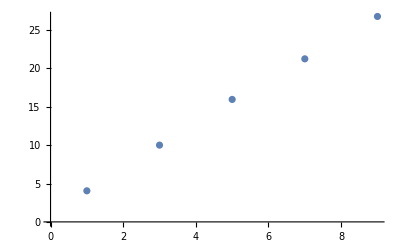

```mathematica
ListPlot[%410]
```

```mathematica
NMaximize[{%364[[1]],x>=2},x,Method->"SimulatedAnnealing"]
```

{0.830746,{x→4.04819}}

```mathematica
NMaximize[{%364[[2]],x>=2},x,Method->"SimulatedAnnealing"]
```

{22.0635,{x→9.9983}}

```mathematica
NMaximize[{%364[[3]],x>=4},x,Method->"SimulatedAnnealing",MaxIterations->10000]
```

{678.482,{x→15.9487}}

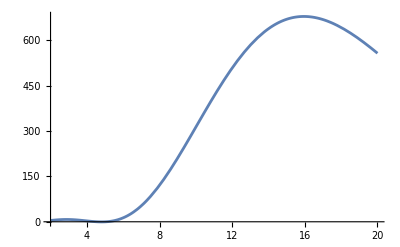

```mathematica
Plot[%364[[3]],{x,2,20},WorkingPrecision->30]
```

```mathematica
D[crossingEq[6],{z,9},C[0]]/9!/.Δσ->1/.Δ[0]->x//Simplify
```

1/(11612160 (1+2 x) (3+2 x) (5+2 x) (7+2 x))x (32 (-8+x) (-7+x) (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) (1+2 x) (3+2 x) (5+2 x) (7+2 x) (1-z)^(-9+x) z^2 Hypergeometric2F1[x,x,2 x,1-z]+32 (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) (1+2 x) (3+2 x) (5+2 x) (7+2 x) z^(-9+x) (x^2 (-1+z)^2+3 x (-5+4 z+z^2)+2 (28+7 z+z^2)) Hypergeometric2F1[x,x,2 x,z]+144 (-7+x) (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) (1+2 x) (3+2 x) (5+2 x) (7+2 x) (1-z)^(-8+x) z (-4 Hypergeometric2F1[x,x,2 x,1-z]+x z Hypergeometric2F1[1+x,1+x,1+2 x,1-z])+144 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x (1+2 x) (3+2 x) (5+2 x) (7+2 x) z^(-8+x) (x^2 (-1+z)^2+2 (21+6 z+z^2)+x (-13+10 z+3 z^2)) Hypergeometric2F1[1+x,1+x,1+2 x,z]+576 (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) (3+2 x) (5+2 x) (7+2 x) (1-z)^(-7+x) ((4+8 x) Hypergeometric2F1[x,x,2 x,1-z]+x z (-4 (1+2 x) Hypergeometric2F1[1+x,1+x,1+2 x,1-z]+(1+x)^2 z Hypergeometric2F1[2+x,2+x,2+2 x,1-z]))+576 (-4+x) (-3+x) (-2+x) (-1+x) x (1+x)^2 (3+2 x) (5+2 x) (7+2 x) z^(-7+x) (x^2 (-1+z)^2+2 (15+5 z+z^2)+x (-11+8 z+3 z^2)) Hypergeometric2F1[2+x,2+x,2+2 x,z]+672 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x (3+2 x) (5+2 x) (7+2 x) (1-z)^(-6+x) (12 (1+2 x) Hypergeometric2F1[1+x,1+x,1+2 x,1-z]+(1+x) z (-12 (1+x) Hypergeometric2F1[2+x,2+x,2+2 x,1-z]+(2+x)^2 z Hypergeometric2F1[3+x,3+x,3+2 x,1-z]))+672 (-3+x) (-2+x) (-1+x) x (1+x) (2+x)^2 (3+2 x) (5+2 x) (7+2 x) z^(-6+x) (x^2 (-1+z)^2+3 x (-3+2 z+z^2)+2 (10+4 z+z^2)) Hypergeometric2F1[3+x,3+x,3+2 x,z]+1008 (1-x) (2-x) (3-x) (4-x) x (1+x) (5+2 x) (7+2 x) (1-z)^(-5+x) (24 (1+x) (3+2 x) Hypergeometric2F1[2+x,2+x,2+2 x,1-z]-8 (2+x)^2 (3+2 x) z Hypergeometric2F1[3+x,3+x,3+2 x,1-z]+(2+x)^2 (3+x)^2 z^2 Hypergeometric2F1[4+x,4+x,4+2 x,1-z])+1008 (-2+x) (-1+x) x (1+x) (2+x)^2 (3+x)^2 (5+2 x) (7+2 x) z^(-5+x) (x^2 (-1+z)^2+2 (6+3 z+z^2)+x (-7+4 z+3 z^2)) Hypergeometric2F1[4+x,4+x,4+2 x,z]-504 (1-x) (2-x) (3-x) x (1+x) (2+x) (5+2 x) (7+2 x) (1-z)^(-4+x) (40 (2+x) (3+2 x) Hypergeometric2F1[3+x,3+x,3+2 x,1-z]-20 (2+x) (3+x)^2 z Hypergeometric2F1[4+x,4+x,4+2 x,1-z]+(3+x)^2 (4+x)^2 z^2 Hypergeometric2F1[5+x,5+x,5+2 x,1-z])+504 (-1+x) x (1+x) (2+x) (3+x)^2 (4+x)^2 (5+2 x) (7+2 x) z^(-4+x) (x^2 (-1+z)^2+2 (3+2 z+z^2)+x (-5+2 z+3 z^2)) Hypergeometric2F1[5+x,5+x,5+2 x,z]+336 (1-x) (2-x) x (1+x) (2+x) (3+x)^2 (7+2 x) (1-z)^(-3+x) (60 (2+x) (5+2 x) Hypergeometric2F1[4+x,4+x,4+2 x,1-z]-12 (4+x)^2 (5+2 x) z Hypergeometric2F1[5+x,5+x,5+2 x,1-z]+(4+x)^2 (5+x)^2 z^2 Hypergeometric2F1[6+x,6+x,6+2 x,1-z])+336 x (1+x) (2+x) (3+x)^2 (4+x)^2 (5+x)^2 (7+2 x) z^(-3+x) (x^2 (-1+z)^2+3 x (-1+z^2)+2 (1+z+z^2)) Hypergeometric2F1[6+x,6+x,6+2 x,z]-72 (1-x) x (1+x) (2+x) (3+x) (4+x)^2 (7+2 x) (1-z)^(-2+x) (84 (3+x) (5+2 x) Hypergeometric2F1[5+x,5+x,5+2 x,1-z]-28 (3+x) (5+x)^2 z Hypergeometric2F1[6+x,6+x,6+2 x,1-z]+(5+x)^2 (6+x)^2 z^2 Hypergeometric2F1[7+x,7+x,7+2 x,1-z])+72 (1+x) (2+x) (3+x) (4+x)^2 (5+x)^2 (6+x)^2 (7+2 x) z^(-2+x) (x^2 (-1+z)^2+2 z^2+x (-1-2 z+3 z^2)) Hypergeometric2F1[7+x,7+x,7+2 x,z]+18 x (1+x) (2+x) (3+x) (4+x)^2 (5+x)^2 (1-z)^(-1+x) (112 (3+x) (7+2 x) Hypergeometric2F1[6+x,6+x,6+2 x,1-z]-16 (6+x)^2 (7+2 x) z Hypergeometric2F1[7+x,7+x,7+2 x,1-z]+(6+x)^2 (7+x)^2 z^2 Hypergeometric2F1[8+x,8+x,8+2 x,1-z])+18 (1+x) (2+x) (3+x) (4+x)^2 (5+x)^2 (6+x)^2 (7+x)^2 (-1+z) z^(-1+x) (x (-1+z)+2 z) Hypergeometric2F1[8+x,8+x,8+2 x,z]+(1+x) (2+x) (3+x) (4+x) (5+x)^2 (6+x)^2 (1-z)^x (144 (4+x) (7+2 x) Hypergeometric2F1[7+x,7+x,7+2 x,1-z]-36 (4+x) (7+x)^2 z Hypergeometric2F1[8+x,8+x,8+2 x,1-z]+(7+x)^2 (8+x)^2 z^2 Hypergeometric2F1[9+x,9+x,9+2 x,1-z])+(1+x) (2+x) (3+x) (4+x) (5+x)^2 (6+x)^2 (7+x)^2 (8+x)^2 (-1+z)^2 z^x Hypergeometric2F1[9+x,9+x,9+2 x,z])

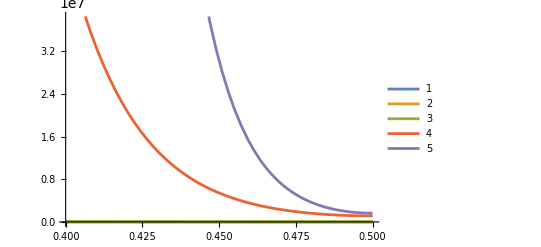

```mathematica
Plot[{%356/.x->2,%356/.x->4,%356/.x->10,%356/.x->20,%356/.x->30}//Evaluate,{z,40/100,1/2},WorkingPrecision->40,PlotLegends->Automatic]
```

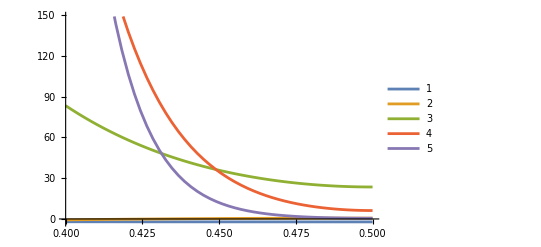

```mathematica
Plot[{%347/.x->2,%347/.x->4,%347/.x->10,%347/.x->20,%347/.x->30}//Evaluate,{z,4/10,1/2},WorkingPrecision->40,PlotLegends->Automatic]
```

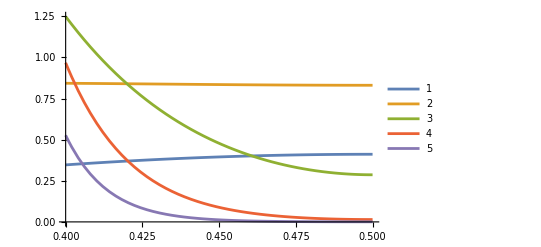

```mathematica
Plot[{%282/.x->2,%282/.x->4,%282/.x->10,%282/.x->20,%282/.x->30}//Evaluate,{z,4/10,1/2},WorkingPrecision->40,PlotLegends->Automatic]
```

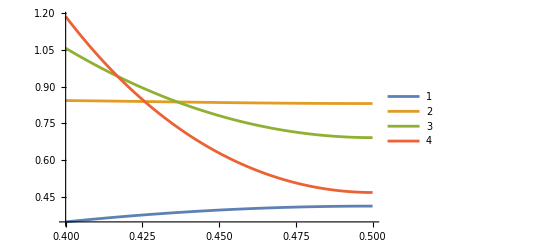

```mathematica
Plot[%263[[;;4]]//Evaluate,{z,4/10,1/2},WorkingPrecision->40,PlotLegends->Automatic]
```

```mathematica
Manipulate[Plot[%243[[5]],{z,4/10,1/2},WorkingPrecision->40,PlotLegends->Automatic],{a1,0,10},{a3,0,10}]
```

```mathematica
D[%233,a1]/.Table[{Δ[0]->2+2i},{i,0,10}]
```

```mathematica
D[%233,a1]/.Table[{Δ[0]->2+2i},{i,0,10}]
```

{(12 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z^2-(12 (1-z) (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 (6 z-5 z^2+6 Log[1-z]-8 z Log[1-z]+2 z^2 Log[1-z]))/((-1+z) z^2)-(12 (1-z)^2 z (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(12 (1-z) z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(6 (1-z)^2 z (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/(-1+z)^4,(560 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^4)-(280 (1-z) (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^2 (420 z-750 z^2+380 z^3-47 z^4+420 Log[1-z]-960 z Log[1-z]+720 z^2 Log[1-z]-192 z^3 Log[1-z]+12 z^4 Log[1-z]))/(3 (-1+z) z^4)-(280 (1-z)^4 z (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+(560 (1-z)^3 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+(140 (1-z)^4 z (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8),(2772 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^6)-(924 (1-z) (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-1/(5 (-1+z) z^6)2772 (1-z)^2 (13860 z-38430 z^2+38640 z^3-16905 z^4+2982 z^5-142 z^6+13860 Log[1-z]-45360 z Log[1-z]+56700 z^2 Log[1-z]-33600 z^3 Log[1-z]+9450 z^4 Log[1-z]-1080 z^5 Log[1-z]+30 z^6 Log[1-z])-(924 (1-z)^6 z (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)+(2772 (1-z)^5 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)+(2772 (1-z)^6 z (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12),1/(7 z^8)41184 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 z^7)10296 (1-z) (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z) z^8)10296 (1-z)^2 (1801800 z-6786780 z^2+10210200 z^3-7803950 z^4+3181640 z^5-660996 z^6+59608 z^7-1487 z^8+1801800 Log[1-z]-7687680 z Log[1-z]+13453440 z^2 Log[1-z]-12418560 z^3 Log[1-z]+6468000 z^4 Log[1-z]-1881600 z^5 Log[1-z]+282240 z^6 Log[1-z]-17920 z^7 Log[1-z]+280 z^8 Log[1-z])-1/(7 (-1+z)^15)10296 (1-z)^8 z (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])+1/(7 (-1+z)^15)41184 (1-z)^7 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])+1/(7 (-1+z)^16)10296 (1-z)^8 z (35+9376 z+131712 z^2+406112 z^3+171500 z^4-384160 z^5-285376 z^6-47712 z^7-1487 z^8+2240 z Log[z]+54880 z^2 Log[z]+329280 z^3 Log[z]+686000 z^4 Log[z]+548800 z^5 Log[z]+164640 z^6 Log[z]+15680 z^7 Log[z]+280 z^8 Log[z]),1/(63 z^10)461890 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 z^9)92378 (1-z) (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z) z^10)461890 (1-z)^2 (116396280 z-554413860 z^2+1110869760 z^3-1215644430 z^4+789044256 z^5-308618310 z^6+70561920 z^7-8662995 z^8+474760 z^9-7255 z^10+116396280 Log[1-z]-612612000 z Log[1-z]+1378377000 z^2 Log[1-z]-1729728000 z^3 Log[1-z]+1324323000 z^4 Log[1-z]-635675040 z^5 Log[1-z]+189189000 z^6 Log[1-z]-33264000 z^7 Log[1-z]+3118500 z^8 Log[1-z]-126000 z^9 Log[1-z]+1260 z^10 Log[1-z])-1/(63 (-1+z)^19)92378 (1-z)^10 z (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])+1/(63 (-1+z)^19)461890 (1-z)^9 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])+1/(63 (-1+z)^20)461890 (1-z)^10 z (126+58690 z+1498095 z^2+10082880 z^3+21855960 z^4+8001504 z^5-18892440 z^6-17478720 z^7-4716630 z^8-402210 z^9-7255 z^10+12600 z Log[z]+510300 z^2 Log[z]+5443200 z^3 Log[z]+22226400 z^4 Log[z]+40007520 z^5 Log[z]+33339600 z^6 Log[z]+12700800 z^7 Log[z]+2041200 z^8 Log[z]+113400 z^9 Log[z]+1260 z^10 Log[z]),-2 (1-z)^12 z Hypergeometric2F1[12,12,24,1-z]+12 (1-z)^11 z^2 Hypergeometric2F1[12,12,24,1-z]+12 (1-z)^2 z^11 Hypergeometric2F1[12,12,24,z]-2 (1-z) z^12 Hypergeometric2F1[12,12,24,z]+6 (1-z)^12 z^2 Hypergeometric2F1[13,13,25,1-z]+6 (1-z)^2 z^12 Hypergeometric2F1[13,13,25,z],-2 (1-z)^14 z Hypergeometric2F1[14,14,28,1-z]+14 (1-z)^13 z^2 Hypergeometric2F1[14,14,28,1-z]+14 (1-z)^2 z^13 Hypergeometric2F1[14,14,28,z]-2 (1-z) z^14 Hypergeometric2F1[14,14,28,z]+7 (1-z)^14 z^2 Hypergeometric2F1[15,15,29,1-z]+7 (1-z)^2 z^14 Hypergeometric2F1[15,15,29,z],-2 (1-z)^16 z Hypergeometric2F1[16,16,32,1-z]+16 (1-z)^15 z^2 Hypergeometric2F1[16,16,32,1-z]+16 (1-z)^2 z^15 Hypergeometric2F1[16,16,32,z]-2 (1-z) z^16 Hypergeometric2F1[16,16,32,z]+8 (1-z)^16 z^2 Hypergeometric2F1[17,17,33,1-z]+8 (1-z)^2 z^16 Hypergeometric2F1[17,17,33,z],-2 (1-z)^18 z Hypergeometric2F1[18,18,36,1-z]+18 (1-z)^17 z^2 Hypergeometric2F1[18,18,36,1-z]+18 (1-z)^2 z^17 Hypergeometric2F1[18,18,36,z]-2 (1-z) z^18 Hypergeometric2F1[18,18,36,z]+9 (1-z)^18 z^2 Hypergeometric2F1[19,19,37,1-z]+9 (1-z)^2 z^18 Hypergeometric2F1[19,19,37,z],-2 (1-z)^20 z Hypergeometric2F1[20,20,40,1-z]+20 (1-z)^19 z^2 Hypergeometric2F1[20,20,40,1-z]+20 (1-z)^2 z^19 Hypergeometric2F1[20,20,40,z]-2 (1-z) z^20 Hypergeometric2F1[20,20,40,z]+10 (1-z)^20 z^2 Hypergeometric2F1[21,21,41,1-z]+10 (1-z)^2 z^20 Hypergeometric2F1[21,21,41,z],-2 (1-z)^22 z Hypergeometric2F1[22,22,44,1-z]+22 (1-z)^21 z^2 Hypergeometric2F1[22,22,44,1-z]+22 (1-z)^2 z^21 Hypergeometric2F1[22,22,44,z]-2 (1-z) z^22 Hypergeometric2F1[22,22,44,z]+11 (1-z)^22 z^2 Hypergeometric2F1[23,23,45,1-z]+11 (1-z)^2 z^22 Hypergeometric2F1[23,23,45,z]}

```mathematica
Table[C[i],{i,0,5}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218,0.000374239}

```mathematica
Solve[N[%227/.zvalsTable[4/10,49/100,6]/.C[i_]->c[i]/.genBos/.Δσ->1/.a1->0/.a3->0,30]==0]
```

{{c[0]→2.003032170716150650402,c[1.]→1.197405588009153818042,c[2.]→0.2400163818168497419016,c[3.]→0.03144485038791188997923,c[4.]→0.004277550333317301995585,c[5.]→0.0001755828741766694985919,c[6.]→0.00007649770273961786611885}}

```mathematica
Solve[N[%227/.zvalsTable[4/10,49/100,6]/.C[i_]->c[i]/.genBos/.Δσ->1/.a1->1/.a3->1,30]==0]
```

{{c[0]→2.0033431160980515552443,c[1.]→1.1971429341490372993861,c[2.]→0.2402030836204797476677,c[3.]→0.03133865093459407686362,c[4.]→0.0043218206064456373836751,c[5.]→0.00016373909344545404968385,c[6.]→0.000078009440449032682981073}}

```mathematica
D[a3 D[crossingEq[6],{z,3}]/3!+a1 D[crossingEq[6],{z,1}]/1!+crossingEq[6],C[0]]/.Δσ->1
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]+a1 (-2 (1-z)^Δ[0] z Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-2 (1-z) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]+(1-z)^(-1+Δ[0]) z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z] Δ[0]+(1-z)^2 z^(-1+Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z] Δ[0]+1/2 (1-z)^Δ[0] z^2 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0]+1/2 (1-z)^2 z^Δ[0] Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],z] Δ[0])+1/6 a3 ((1-z)^(-3+Δ[0]) z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z] (-2+Δ[0]) (-1+Δ[0]) Δ[0]+((1-z)^2 z^Δ[0] Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],z] Δ[0] (1+Δ[0])^2 (2+Δ[0])^2)/(2 (1+2 Δ[0]) (2+2 Δ[0]))+(3 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],z] Δ[0] (1+Δ[0])^2 (-2 (1-z) z^Δ[0]+(1-z)^2 z^(-1+Δ[0]) Δ[0]))/(2 (1+2 Δ[0]))-3 (1-z)^(-2+Δ[0]) (-1+Δ[0]) Δ[0] (2 z Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0])+3/2 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],z] Δ[0] (2 z^Δ[0]-4 (1-z) z^(-1+Δ[0]) Δ[0]+(1-z)^2 z^(-2+Δ[0]) (-1+Δ[0]) Δ[0])+Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z] (6 z^(-1+Δ[0]) Δ[0]-6 (1-z) z^(-2+Δ[0]) (-1+Δ[0]) Δ[0]+(1-z)^2 z^(-3+Δ[0]) (-2+Δ[0]) (-1+Δ[0]) Δ[0])+3 (1-z)^(-1+Δ[0]) Δ[0] (2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-2 z Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0]+(z^2 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1-z] Δ[0] (1+Δ[0])^2)/(2 (1+2 Δ[0])))-(1-z)^Δ[0] (-3 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0]+(3 z Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1-z] Δ[0] (1+Δ[0])^2)/(1+2 Δ[0])-(z^2 Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1-z] Δ[0] (1+Δ[0])^2 (2+Δ[0])^2)/(2 (1+2 Δ[0]) (2+2 Δ[0]))))

```mathematica
a3 D[crossingEq[6],{z,3}]/3!+a1 D[crossingEq[6],{z,1}]/1!+crossingEq[6]/.C[i_]->c[i]/.Δσ->1
```

(1-z)^2-z^2+c[0] (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+c[1] (-(1-z)^Δ[1] z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^2 z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+c[2] (-(1-z)^Δ[2] z^2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^2 z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+c[3] (-(1-z)^Δ[3] z^2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^2 z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+c[4] (-(1-z)^Δ[4] z^2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^2 z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+c[5] (-(1-z)^Δ[5] z^2 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^2 z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+c[6] (-(1-z)^Δ[6] z^2 Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(1-z)^2 z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])+a1 (-2 (1-z)-2 z+c[0] (-2 (1-z)^Δ[0] z Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-2 (1-z) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]+(1-z)^(-1+Δ[0]) z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z] Δ[0]+(1-z)^2 z^(-1+Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z] Δ[0]+1/2 (1-z)^Δ[0] z^2 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0]+1/2 (1-z)^2 z^Δ[0] Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],z] Δ[0])+c[1] (-2 (1-z)^Δ[1] z Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]-2 (1-z) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z]+(1-z)^(-1+Δ[1]) z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z] Δ[1]+(1-z)^2 z^(-1+Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z] Δ[1]+1/2 (1-z)^Δ[1] z^2 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1-z] Δ[1]+1/2 (1-z)^2 z^Δ[1] Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],z] Δ[1])+c[2] (-2 (1-z)^Δ[2] z Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]-2 (1-z) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z]+(1-z)^(-1+Δ[2]) z^2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z] Δ[2]+(1-z)^2 z^(-1+Δ[2]) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z] Δ[2]+1/2 (1-z)^Δ[2] z^2 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1-z] Δ[2]+1/2 (1-z)^2 z^Δ[2] Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],z] Δ[2])+c[3] (-2 (1-z)^Δ[3] z Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]-2 (1-z) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z]+(1-z)^(-1+Δ[3]) z^2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z] Δ[3]+(1-z)^2 z^(-1+Δ[3]) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z] Δ[3]+1/2 (1-z)^Δ[3] z^2 Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],1-z] Δ[3]+1/2 (1-z)^2 z^Δ[3] Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],z] Δ[3])+c[4] (-2 (1-z)^Δ[4] z Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]-2 (1-z) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z]+(1-z)^(-1+Δ[4]) z^2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z] Δ[4]+(1-z)^2 z^(-1+Δ[4]) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z] Δ[4]+1/2 (1-z)^Δ[4] z^2 Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],1-z] Δ[4]+1/2 (1-z)^2 z^Δ[4] Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],z] Δ[4])+c[5] (-2 (1-z)^Δ[5] z Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]-2 (1-z) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z]+(1-z)^(-1+Δ[5]) z^2 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z] Δ[5]+(1-z)^2 z^(-1+Δ[5]) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z] Δ[5]+1/2 (1-z)^Δ[5] z^2 Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],1-z] Δ[5]+1/2 (1-z)^2 z^Δ[5] Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],z] Δ[5])+c[6] (-2 (1-z)^Δ[6] z Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]-2 (1-z) z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z]+(1-z)^(-1+Δ[6]) z^2 Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z] Δ[6]+(1-z)^2 z^(-1+Δ[6]) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z] Δ[6]+1/2 (1-z)^Δ[6] z^2 Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],1-z] Δ[6]+1/2 (1-z)^2 z^Δ[6] Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],z] Δ[6]))+1/6 a3 (c[0] ((1-z)^(-3+Δ[0]) z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z] (-2+Δ[0]) (-1+Δ[0]) Δ[0]+((1-z)^2 z^Δ[0] Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],z] Δ[0] (1+Δ[0])^2 (2+Δ[0])^2)/(2 (1+2 Δ[0]) (2+2 Δ[0]))+(3 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],z] Δ[0] (1+Δ[0])^2 (-2 (1-z) z^Δ[0]+(1-z)^2 z^(-1+Δ[0]) Δ[0]))/(2 (1+2 Δ[0]))-3 (1-z)^(-2+Δ[0]) (-1+Δ[0]) Δ[0] (2 z Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0])+3/2 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],z] Δ[0] (2 z^Δ[0]-4 (1-z) z^(-1+Δ[0]) Δ[0]+(1-z)^2 z^(-2+Δ[0]) (-1+Δ[0]) Δ[0])+Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z] (6 z^(-1+Δ[0]) Δ[0]-6 (1-z) z^(-2+Δ[0]) (-1+Δ[0]) Δ[0]+(1-z)^2 z^(-3+Δ[0]) (-2+Δ[0]) (-1+Δ[0]) Δ[0])+3 (1-z)^(-1+Δ[0]) Δ[0] (2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-2 z Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0]+(z^2 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1-z] Δ[0] (1+Δ[0])^2)/(2 (1+2 Δ[0])))-(1-z)^Δ[0] (-3 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1-z] Δ[0]+(3 z Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1-z] Δ[0] (1+Δ[0])^2)/(1+2 Δ[0])-(z^2 Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1-z] Δ[0] (1+Δ[0])^2 (2+Δ[0])^2)/(2 (1+2 Δ[0]) (2+2 Δ[0]))))+c[1] ((1-z)^(-3+Δ[1]) z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z] (-2+Δ[1]) (-1+Δ[1]) Δ[1]+((1-z)^2 z^Δ[1] Hypergeometric2F1[3+Δ[1],3+Δ[1],3+2 Δ[1],z] Δ[1] (1+Δ[1])^2 (2+Δ[1])^2)/(2 (1+2 Δ[1]) (2+2 Δ[1]))+(3 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],z] Δ[1] (1+Δ[1])^2 (-2 (1-z) z^Δ[1]+(1-z)^2 z^(-1+Δ[1]) Δ[1]))/(2 (1+2 Δ[1]))-3 (1-z)^(-2+Δ[1]) (-1+Δ[1]) Δ[1] (2 z Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1-z] Δ[1])+3/2 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],z] Δ[1] (2 z^Δ[1]-4 (1-z) z^(-1+Δ[1]) Δ[1]+(1-z)^2 z^(-2+Δ[1]) (-1+Δ[1]) Δ[1])+Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z] (6 z^(-1+Δ[1]) Δ[1]-6 (1-z) z^(-2+Δ[1]) (-1+Δ[1]) Δ[1]+(1-z)^2 z^(-3+Δ[1]) (-2+Δ[1]) (-1+Δ[1]) Δ[1])+3 (1-z)^(-1+Δ[1]) Δ[1] (2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]-2 z Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1-z] Δ[1]+(z^2 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1-z] Δ[1] (1+Δ[1])^2)/(2 (1+2 Δ[1])))-(1-z)^Δ[1] (-3 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1-z] Δ[1]+(3 z Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1-z] Δ[1] (1+Δ[1])^2)/(1+2 Δ[1])-(z^2 Hypergeometric2F1[3+Δ[1],3+Δ[1],3+2 Δ[1],1-z] Δ[1] (1+Δ[1])^2 (2+Δ[1])^2)/(2 (1+2 Δ[1]) (2+2 Δ[1]))))+c[2] ((1-z)^(-3+Δ[2]) z^2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z] (-2+Δ[2]) (-1+Δ[2]) Δ[2]+((1-z)^2 z^Δ[2] Hypergeometric2F1[3+Δ[2],3+Δ[2],3+2 Δ[2],z] Δ[2] (1+Δ[2])^2 (2+Δ[2])^2)/(2 (1+2 Δ[2]) (2+2 Δ[2]))+(3 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],z] Δ[2] (1+Δ[2])^2 (-2 (1-z) z^Δ[2]+(1-z)^2 z^(-1+Δ[2]) Δ[2]))/(2 (1+2 Δ[2]))-3 (1-z)^(-2+Δ[2]) (-1+Δ[2]) Δ[2] (2 z Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1-z] Δ[2])+3/2 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],z] Δ[2] (2 z^Δ[2]-4 (1-z) z^(-1+Δ[2]) Δ[2]+(1-z)^2 z^(-2+Δ[2]) (-1+Δ[2]) Δ[2])+Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z] (6 z^(-1+Δ[2]) Δ[2]-6 (1-z) z^(-2+Δ[2]) (-1+Δ[2]) Δ[2]+(1-z)^2 z^(-3+Δ[2]) (-2+Δ[2]) (-1+Δ[2]) Δ[2])+3 (1-z)^(-1+Δ[2]) Δ[2] (2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]-2 z Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1-z] Δ[2]+(z^2 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1-z] Δ[2] (1+Δ[2])^2)/(2 (1+2 Δ[2])))-(1-z)^Δ[2] (-3 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1-z] Δ[2]+(3 z Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1-z] Δ[2] (1+Δ[2])^2)/(1+2 Δ[2])-(z^2 Hypergeometric2F1[3+Δ[2],3+Δ[2],3+2 Δ[2],1-z] Δ[2] (1+Δ[2])^2 (2+Δ[2])^2)/(2 (1+2 Δ[2]) (2+2 Δ[2]))))+c[3] ((1-z)^(-3+Δ[3]) z^2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z] (-2+Δ[3]) (-1+Δ[3]) Δ[3]+((1-z)^2 z^Δ[3] Hypergeometric2F1[3+Δ[3],3+Δ[3],3+2 Δ[3],z] Δ[3] (1+Δ[3])^2 (2+Δ[3])^2)/(2 (1+2 Δ[3]) (2+2 Δ[3]))+(3 Hypergeometric2F1[2+Δ[3],2+Δ[3],2+2 Δ[3],z] Δ[3] (1+Δ[3])^2 (-2 (1-z) z^Δ[3]+(1-z)^2 z^(-1+Δ[3]) Δ[3]))/(2 (1+2 Δ[3]))-3 (1-z)^(-2+Δ[3]) (-1+Δ[3]) Δ[3] (2 z Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],1-z] Δ[3])+3/2 Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],z] Δ[3] (2 z^Δ[3]-4 (1-z) z^(-1+Δ[3]) Δ[3]+(1-z)^2 z^(-2+Δ[3]) (-1+Δ[3]) Δ[3])+Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z] (6 z^(-1+Δ[3]) Δ[3]-6 (1-z) z^(-2+Δ[3]) (-1+Δ[3]) Δ[3]+(1-z)^2 z^(-3+Δ[3]) (-2+Δ[3]) (-1+Δ[3]) Δ[3])+3 (1-z)^(-1+Δ[3]) Δ[3] (2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]-2 z Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],1-z] Δ[3]+(z^2 Hypergeometric2F1[2+Δ[3],2+Δ[3],2+2 Δ[3],1-z] Δ[3] (1+Δ[3])^2)/(2 (1+2 Δ[3])))-(1-z)^Δ[3] (-3 Hypergeometric2F1[1+Δ[3],1+Δ[3],1+2 Δ[3],1-z] Δ[3]+(3 z Hypergeometric2F1[2+Δ[3],2+Δ[3],2+2 Δ[3],1-z] Δ[3] (1+Δ[3])^2)/(1+2 Δ[3])-(z^2 Hypergeometric2F1[3+Δ[3],3+Δ[3],3+2 Δ[3],1-z] Δ[3] (1+Δ[3])^2 (2+Δ[3])^2)/(2 (1+2 Δ[3]) (2+2 Δ[3]))))+c[4] ((1-z)^(-3+Δ[4]) z^2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z] (-2+Δ[4]) (-1+Δ[4]) Δ[4]+((1-z)^2 z^Δ[4] Hypergeometric2F1[3+Δ[4],3+Δ[4],3+2 Δ[4],z] Δ[4] (1+Δ[4])^2 (2+Δ[4])^2)/(2 (1+2 Δ[4]) (2+2 Δ[4]))+(3 Hypergeometric2F1[2+Δ[4],2+Δ[4],2+2 Δ[4],z] Δ[4] (1+Δ[4])^2 (-2 (1-z) z^Δ[4]+(1-z)^2 z^(-1+Δ[4]) Δ[4]))/(2 (1+2 Δ[4]))-3 (1-z)^(-2+Δ[4]) (-1+Δ[4]) Δ[4] (2 z Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],1-z] Δ[4])+3/2 Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],z] Δ[4] (2 z^Δ[4]-4 (1-z) z^(-1+Δ[4]) Δ[4]+(1-z)^2 z^(-2+Δ[4]) (-1+Δ[4]) Δ[4])+Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z] (6 z^(-1+Δ[4]) Δ[4]-6 (1-z) z^(-2+Δ[4]) (-1+Δ[4]) Δ[4]+(1-z)^2 z^(-3+Δ[4]) (-2+Δ[4]) (-1+Δ[4]) Δ[4])+3 (1-z)^(-1+Δ[4]) Δ[4] (2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]-2 z Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],1-z] Δ[4]+(z^2 Hypergeometric2F1[2+Δ[4],2+Δ[4],2+2 Δ[4],1-z] Δ[4] (1+Δ[4])^2)/(2 (1+2 Δ[4])))-(1-z)^Δ[4] (-3 Hypergeometric2F1[1+Δ[4],1+Δ[4],1+2 Δ[4],1-z] Δ[4]+(3 z Hypergeometric2F1[2+Δ[4],2+Δ[4],2+2 Δ[4],1-z] Δ[4] (1+Δ[4])^2)/(1+2 Δ[4])-(z^2 Hypergeometric2F1[3+Δ[4],3+Δ[4],3+2 Δ[4],1-z] Δ[4] (1+Δ[4])^2 (2+Δ[4])^2)/(2 (1+2 Δ[4]) (2+2 Δ[4]))))+c[5] ((1-z)^(-3+Δ[5]) z^2 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z] (-2+Δ[5]) (-1+Δ[5]) Δ[5]+((1-z)^2 z^Δ[5] Hypergeometric2F1[3+Δ[5],3+Δ[5],3+2 Δ[5],z] Δ[5] (1+Δ[5])^2 (2+Δ[5])^2)/(2 (1+2 Δ[5]) (2+2 Δ[5]))+(3 Hypergeometric2F1[2+Δ[5],2+Δ[5],2+2 Δ[5],z] Δ[5] (1+Δ[5])^2 (-2 (1-z) z^Δ[5]+(1-z)^2 z^(-1+Δ[5]) Δ[5]))/(2 (1+2 Δ[5]))-3 (1-z)^(-2+Δ[5]) (-1+Δ[5]) Δ[5] (2 z Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],1-z] Δ[5])+3/2 Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],z] Δ[5] (2 z^Δ[5]-4 (1-z) z^(-1+Δ[5]) Δ[5]+(1-z)^2 z^(-2+Δ[5]) (-1+Δ[5]) Δ[5])+Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z] (6 z^(-1+Δ[5]) Δ[5]-6 (1-z) z^(-2+Δ[5]) (-1+Δ[5]) Δ[5]+(1-z)^2 z^(-3+Δ[5]) (-2+Δ[5]) (-1+Δ[5]) Δ[5])+3 (1-z)^(-1+Δ[5]) Δ[5] (2 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]-2 z Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],1-z] Δ[5]+(z^2 Hypergeometric2F1[2+Δ[5],2+Δ[5],2+2 Δ[5],1-z] Δ[5] (1+Δ[5])^2)/(2 (1+2 Δ[5])))-(1-z)^Δ[5] (-3 Hypergeometric2F1[1+Δ[5],1+Δ[5],1+2 Δ[5],1-z] Δ[5]+(3 z Hypergeometric2F1[2+Δ[5],2+Δ[5],2+2 Δ[5],1-z] Δ[5] (1+Δ[5])^2)/(1+2 Δ[5])-(z^2 Hypergeometric2F1[3+Δ[5],3+Δ[5],3+2 Δ[5],1-z] Δ[5] (1+Δ[5])^2 (2+Δ[5])^2)/(2 (1+2 Δ[5]) (2+2 Δ[5]))))+c[6] ((1-z)^(-3+Δ[6]) z^2 Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z] (-2+Δ[6]) (-1+Δ[6]) Δ[6]+((1-z)^2 z^Δ[6] Hypergeometric2F1[3+Δ[6],3+Δ[6],3+2 Δ[6],z] Δ[6] (1+Δ[6])^2 (2+Δ[6])^2)/(2 (1+2 Δ[6]) (2+2 Δ[6]))+(3 Hypergeometric2F1[2+Δ[6],2+Δ[6],2+2 Δ[6],z] Δ[6] (1+Δ[6])^2 (-2 (1-z) z^Δ[6]+(1-z)^2 z^(-1+Δ[6]) Δ[6]))/(2 (1+2 Δ[6]))-3 (1-z)^(-2+Δ[6]) (-1+Δ[6]) Δ[6] (2 z Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]-1/2 z^2 Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],1-z] Δ[6])+3/2 Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],z] Δ[6] (2 z^Δ[6]-4 (1-z) z^(-1+Δ[6]) Δ[6]+(1-z)^2 z^(-2+Δ[6]) (-1+Δ[6]) Δ[6])+Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z] (6 z^(-1+Δ[6]) Δ[6]-6 (1-z) z^(-2+Δ[6]) (-1+Δ[6]) Δ[6]+(1-z)^2 z^(-3+Δ[6]) (-2+Δ[6]) (-1+Δ[6]) Δ[6])+3 (1-z)^(-1+Δ[6]) Δ[6] (2 Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]-2 z Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],1-z] Δ[6]+(z^2 Hypergeometric2F1[2+Δ[6],2+Δ[6],2+2 Δ[6],1-z] Δ[6] (1+Δ[6])^2)/(2 (1+2 Δ[6])))-(1-z)^Δ[6] (-3 Hypergeometric2F1[1+Δ[6],1+Δ[6],1+2 Δ[6],1-z] Δ[6]+(3 z Hypergeometric2F1[2+Δ[6],2+Δ[6],2+2 Δ[6],1-z] Δ[6] (1+Δ[6])^2)/(1+2 Δ[6])-(z^2 Hypergeometric2F1[3+Δ[6],3+Δ[6],3+2 Δ[6],1-z] Δ[6] (1+Δ[6])^2 (2+Δ[6])^2)/(2 (1+2 Δ[6]) (2+2 Δ[6])))))

```mathematica
D[crossingEq[6],{Table[C[i],{i,0,5}],1}]
```

{-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z],-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z],-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z],-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z],-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z]}

```mathematica
Solve[eqs[[1]]==0]
```

{{c[0]→1}}

```mathematica
getAvCsToy[10,0,1/10,1,30]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{Mean[c[0]/.{}⟦1⟧],StandardDeviation[c[0]/.{}⟦1⟧]},{Mean[c[1.]/.{}⟦1⟧],StandardDeviation[c[1.]/.{}⟦1⟧]},{Mean[c[2.]/.{}⟦1⟧],StandardDeviation[c[2.]/.{}⟦1⟧]},{Mean[c[3.]/.{}⟦1⟧],StandardDeviation[c[3.]/.{}⟦1⟧]},{Mean[c[4.]/.{}⟦1⟧],StandardDeviation[c[4.]/.{}⟦1⟧]},{Mean[c[5.]/.{}⟦1⟧],StandardDeviation[c[5.]/.{}⟦1⟧]},{Mean[c[6.]/.{}⟦1⟧],StandardDeviation[c[6.]/.{}⟦1⟧]},{Mean[c[7.]/.{}⟦1⟧],StandardDeviation[c[7.]/.{}⟦1⟧]},{Mean[c[8.]/.{}⟦1⟧],StandardDeviation[c[8.]/.{}⟦1⟧]},{Mean[c[9.]/.{}⟦1⟧],StandardDeviation[c[9.]/.{}⟦1⟧]}}

```mathematica
crossingEqToy[nstates_]:=Exp[z]-Sum[C[n]z^n/n!,{n,0,nstates}]
```

```mathematica
crossingEqToy[10]
```

ⅇ^z-C[0]-z C[1]-(z^2 C[2])/2-(z^3 C[3])/6-(z^4 C[4])/24-(z^5 C[5])/120-(z^6 C[6])/720-(z^7 C[7])/5040-(z^8 C[8])/40320-(z^9 C[9])/362880-(z^10 C[10])/3628800

```mathematica
zvalsTable[zmin,zmax,nstates*10-1]
```

{0.0848410080263427320972147299389-0.0363883775016744394825665498921 c[0]-0.448746394862177742873592731348 c[1.]-0.471740150154884403618304864508 c[2.]-0.410533450280765579207543592231 c[3.]-0.3402435400234453071557881351 c[4.]==0,0.083255308018346234885570457894-0.0357149123677665146869225632882 c[0]-0.439932037519259646214720769441 c[1.]-0.460348217848819393875439499153 c[2.]-0.39780857416951011290696686967 c[3.]-0.326923814840331150436286014118 c[4.]==0,0.081671172225878590785766450976-0.0350417355520171771467502192572 c[0]-0.431150379804240975582203482081 c[1.]-0.44911783539489551327412065769 c[2.]-0.385411300694397721076151362936 c[3.]-0.314089384722541756227825714977 c[4.]==0,0.0800885674659855006848698625553-0.034368841251806907123289493615 c[0]-0.422400724789435227424047137044 c[1.]-0.438045018149322555563135880858 c[2.]-0.373331580824958483781414521021 c[3.]-0.301721646526223685810597455101 c[4.]==0,0.0785074607926428234284495986433-0.0336962236884559490643842772182 c[0]-0.413682380681025523828061049821 c[1.]-0.427125841160087409284404447097 c[2.]-0.36155962144851630596660450413 c[3.]-0.289802664561234662001636935866 c[4.]==0}

```mathematica
Solve[Join[Table[%[[i]]==0,{i,5}],Table[N[c[i]>=0,30],{i,0,5-1}]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

```mathematica
Table[C[i],{i,0,4}]/.genBos/.Δσ->1/8//N
```

{2.,0.0260417,0.000772848,0.0000317656,1.47969×10^-6}

```mathematica
N[crossingEq[5-1]/.C[j_]-> c[j]/.Δ[i_]->i+1/.Δσ->1/8/.zvalsTable[40/100,49/100,5*10-1],30]
```

```mathematica
getAvCs[5,{2,4,6,8,10},40/100,49/100,1/8,30]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{Mean[c[0]/.{}⟦1⟧],StandardDeviation[c[0]/.{}⟦1⟧]},{Mean[c[1.]/.{}⟦1⟧],StandardDeviation[c[1.]/.{}⟦1⟧]},{Mean[c[2.]/.{}⟦1⟧],StandardDeviation[c[2.]/.{}⟦1⟧]},{Mean[c[3.]/.{}⟦1⟧],StandardDeviation[c[3.]/.{}⟦1⟧]},{Mean[c[4.]/.{}⟦1⟧],StandardDeviation[c[4.]/.{}⟦1⟧]}}

```mathematica
getAvCs[6,{1/4,9/4,17/4,25/4,33/4,41/4,49/4},40/100,49/100,1/8,30]
```

getAvCs[6,{1/4,9/4,17/4,25/4,33/4,41/4,49/4},2/5,49/100,1/8,30]

```mathematica
Table[C[i],{i,0,6}]/.genBos/.Δσ->1/8//N
```

{2.,0.0260417,0.000772848,0.0000317656,1.47969×10^-6,7.37182×10^-8,3.83051×10^-9}

```mathematica
Table[Δ[i],{i,0,6}]/.genBos/.Δσ->1/8//N
```

{0.25,2.25,4.25,6.25,8.25,10.25,12.25}

```mathematica
getAvCs[6,{101/100,194/100,296/100,395/100,504/100,595/100},40/100,49/100,1/8,40]
```

{{0.198373332687708115929582395,0.00167173108351753806990403},{0.0879272487485009067808978545,0.001939065182179007957504919},{-0.0270186339260353775056433695,0.001027778567611252016363985},{0.0113747227665318879063205321,0.0003445786936172773139338106},{-0.00224334379910031724355001227,0.00006730057967509609785821679},{0.000395033822922824226794461592,8.624484400009308217445433×10^-6}}

```mathematica
getAvCsResc[9,Table[2i,{i,1,10}],40/100,49/100,1,50]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧,{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{Mean[0.064570346893168489228847818462130439339987626704034 c[0]/.{}⟦1⟧],StandardDeviation[0.064570346893168489228847818462130439339987626704034 c[0]/.{}⟦1⟧]},{Mean[0.0041693296979041135693579037902323422365360458512787 c[1.]/.{}⟦1⟧],StandardDeviation[0.0041693296979041135693579037902323422365360458512787 c[1.]/.{}⟦1⟧]},{Mean[0.0002692150649056579953707204350125391157501742325256 c[2.]/.{}⟦1⟧],StandardDeviation[0.0002692150649056579953707204350125391157501742325256 c[2.]/.{}⟦1⟧]},{Mean[0.00001738331012982520691818657633486621514073354443785 c[3.]/.{}⟦1⟧],StandardDeviation[0.00001738331012982520691818657633486621514073354443785 c[3.]/.{}⟦1⟧]},{Mean[1.1224463652343433766814074245879264525481017853477×10^-6 c[4.]/.{}⟦1⟧],StandardDeviation[1.1224463652343433766814074245879264525481017853477×10^-6 c[4.]/.{}⟦1⟧]},{Mean[7.2476751172157647191896815854928994593774719835699×10^-8 c[5.]/.{}⟦1⟧],StandardDeviation[7.2476751172157647191896815854928994593774719835699×10^-8 c[5.]/.{}⟦1⟧]},{Mean[4.6798489648760751943778768032035558204139266952425×10^-9 c[6.]/.{}⟦1⟧],StandardDeviation[4.6798489648760751943778768032035558204139266952425×10^-9 c[6.]/.{}⟦1⟧]},{Mean[3.0217947106968365220054813988524613392018134843906×10^-10 c[7.]/.{}⟦1⟧],StandardDeviation[3.0217947106968365220054813988524613392018134843906×10^-10 c[7.]/.{}⟦1⟧]},{Mean[1.9511833270963645184414728864349411716778696084959×10^-11 c[8.]/.{}⟦1⟧],StandardDeviation[1.9511833270963645184414728864349411716778696084959×10^-11 c[8.]/.{}⟦1⟧]}}

```mathematica
Table[2i+RandomReal[{-1/10,1/10},WorkingPrecision->40],{i,1,10}]
```

{2.0729606062611375153707134842643148109424,3.9191536107676638786280289106267446972651,5.97497919661485893618036046528140290175031,8.0718222362871185064305452176158732285244,10.0326853326631767897339592173814289267783,11.9221573189743158455291583201916754225703,14.0226351491580773949629683468261477077178,16.0571909667151616757360781403511012364752,17.9142433901866147685741123414368915043047,20.0574186802017359853113314632707895491331}

```mathematica
%54
```

{2.0729606062611375153707134842643148109424,3.9191536107676638786280289106267446972651,5.97497919661485893618036046528140290175031,8.0718222362871185064305452176158732285244,10.0326853326631767897339592173814289267783,11.9221573189743158455291583201916754225703,14.0226351491580773949629683468261477077178,16.0571909667151616757360781403511012364752,17.9142433901866147685741123414368915043047,20.0574186802017359853113314632707895491331}

```mathematica
Table[{Δ[i-1]->%61[[i]],C[i-1]->%58[[i,1]]},{i,Length[%54]-1}]//Flatten
```

{Δ[0]→2.0729606062611375153707134842643148109424,C[0]→1.75416033431303437,Δ[1]→3.9191536107676638786280289106267446972651,C[1]→1.22530259334028691,Δ[2]→5.97497919661485893618036046528140290175031,C[2]→0.263578224555995137,Δ[3]→8.0718222362871185064305452176158732285244,C[3]→0.028971349827963716,Δ[4]→10.0326853326631767897339592173814289267783,C[4]→0.00404650809230401882,Δ[5]→11.9221573189743158455291583201916754225703,C[5]→0.000204616031625373003,Δ[6]→14.0226351491580773949629683468261477077178,C[6]→0.0000777058816633182204,Δ[7]→16.0571909667151616757360781403511012364752,C[7]→-4.57551713369710401×10^-6,Δ[8]→17.9142433901866147685741123414368915043047,C[8]→1.16658076264220975×10^-6}

```mathematica
getAvCs[9,%54,40/100,49/100,1,50]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0078072949266183212344473998995578685384,-0.010833717656050988966788980130411926332,-0.015484797710094886633760309228365470645,-0.02229283830189449238701254081078971814,-«77»,-«77»,-«77»,-0.06038815678685387591357363724140874617,-0.031673638172386836847629658659204053996,0.14539325842696629213483146067415730337},«7»,{-«77»,-«77»,-«77»,-«77»,-«77»,«1»,-«77»,-«77»,-«77»,«77»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.005248719815395838159138552110942172878,-0.0076114955827937912021833342820824316514,-0.011405205959634351741862033026981760341,-0.01720465087835657994379391032411787345,-«78»,-«78»,-«78»,-0.05281743555752650504883067486630814036,-0.027892118519518134470623966709435039226,0.12719101123595505617977528089887640449},{-«78»,-«78»,-«78»,«4»,-«78»,-«78»,«78»},«5»,{«1»},«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0035098251307921436341085508898274573966,-0.0053148526780739165755538677332238968601,-0.008337247623362210370182544858068650396,-0.013150149437411006906732606081231828612,-«78»,-«78»,-«78»,-0.045249358873402111726654462035685531922,-0.024037083305687707583878094117655235576,0.10898876404494382022471910112359550562},«7»,{-«78»,-«78»,-«78»,-«78»,«2»,-«78»,-«78»,-«78»,«78»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{1.75416033431303437,0.00001576051268984},{1.22530259334028691,0.00001416313597246},{0.263578224555995137,9.9391884699971×10^-6},{0.028971349827963716,6.7653705837287×10^-6},{0.00404650809230401882,4.10435362015197×10^-6},{0.000204616031625373003,1.813955380757452×10^-6},{0.0000777058816633182204,5.253595515601937×10^-7},{-4.57551713369710401×10^-6,1.132536375172559×10^-7},{1.16658076264220975×10^-6,1.330858471033257×10^-8}}

```mathematica
%[[;;,2]]//Total
```

0.00005319843849072

```mathematica
%52[[;;,2]]//Total
```

0.00009470466577835307993553339

```mathematica
getAvCs[9,Table[2i,{i,1,10}],40/100,49/100,1,50]
```

{{2.00017244668378500605325115269,0.00002807646267429475585119244},{1.19984980252138127604347084178,0.00002430016430427119598247733},{0.238213033684796378973807949548,0.000018674547657142744486127916},{0.0325518675630812904339933364963,0.000012493753845357455318765084},{0.00375118671624606057429536728976,6.94134518694287411036204611×10^-6},{0.000350322543435098829052203042258,3.032282655730164963951764556×10^-6},{0.0000440289042659725491092173680254,9.672986977711657595250976557×10^-7},{6.70240211087997698887617415216×10^-7,1.9906517314791296679076380934×10^-7},{6.54085643079930883621418751491×10^-7,1.974558369481049634094133055×10^-8}}

```mathematica
Series[crossingEq[5]/.Δ[i_]->2i+2/.C[i_]->Rationalize[%52[[i+1,1]],0]/.Δσ->1//Simplify,{z,1/2,3}]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

((793087255836413818278859799550163741719267598874452008821649058204558110694356887533182648893047756814934961-1144183050987430817802814577094040451668514479106282436430519536595869829277578977003296741779949428265131860 Log[2]) (z-1/2))/250969153435064758740110040245642590346413826902749783599518939493598472559395350654092222647020-(2 (-5106005740601796605288900276500282617477702744460273170313190331849401311309262309922005397575061941505855143+7366409160716790847242216599948502142355504736025669377915334272974392683892496264721896398095636998129124880 Log[2]) (z-1/2)^3)/14938640085420521353577978586050154187286537315639868071399936874618956699964008967505489443275+O[z-1/2]^4

```mathematica
N[crossingEq[5]/.Δ[i_]->2i+2/.C[i_]->Rationalize[%52[[i+1,1]],0]/.Δσ->1/.z->4/10//Simplify,50]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

1.7035135901168691758023426780960159359506667230509×10^-6

```mathematica
N[crossingEq[5]/.Δ[i_]->2i+2/.genBos/.Δσ->1/.z->4/10//Simplify,50]
```

1.4268373152229841586162232268935336965175073570806×10^-6

```mathematica
N[Normal[%118],50]//Expand
```

1.104520446733452996567302624462890972732054870127×10^-15-6.644855192330183214800526345779301333832239198381×10^-15 z+1.330744289658983166499776329056055816510438837438×10^-14 z^2-8.8716285977265544433318421937070387767362589162561×10^-15 z^3

```mathematica
crossingEq[5]-Normal[%133]/.Δσ->1//Simplify
```

(-1+z)^2-z^2+C[0] (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(-1+z)^2 z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+C[2] (-(1-z)^Δ[2] z^2 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(-1+z)^2 z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+C[3] (-(1-z)^Δ[3] z^2 Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(-1+z)^2 z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+C[4] (-(1-z)^Δ[4] z^2 Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(-1+z)^2 z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+C[5] (-(1-z)^Δ[5] z^2 Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(-1+z)^2 z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+((-1+2 z) (-793087255836413818278859799550163741719267598874452008821649058204558110694356887533182648893047756814934961+1144183050987430817802814577094040451668514479106282436430519536595869829277578977003296741779949428265131860 Log[2]))/501938306870129517480220080491285180692827653805499567199037878987196945118790701308184445294040+((-1+2 z)^3 (-5106005740601796605288900276500282617477702744460273170313190331849401311309262309922005397575061941505855143+7366409160716790847242216599948502142355504736025669377915334272974392683892496264721896398095636998129124880 Log[2]))/59754560341682085414311914344200616749146149262559472285599747498475826799856035870021957773100

```mathematica
crossingEq[5]/.genBos/.Δσ->1//Simplify
```

1/(29393 (-1+z)^9 z^9)(-11 (-1+z)^21 z^11 Hypergeometric2F1[12,12,24,1-z]+11 (-1+z)^11 z^21 Hypergeometric2F1[12,12,24,z]+25194 (2310 (-1+z)^11 (-83980+377910 z-714272 z^2+736372 z^3-449904 z^4+165620 z^5-35672 z^6+4134 z^7-214 z^8+3 z^9) Log[1-z]-z (-193993800+2909907000 z-20483533070 z^2+89865755980 z^3-275215055115 z^4+624422363565 z^5-1087014833619 z^6+1483478903478 z^7-1607637784860 z^8+1392501008646 z^9-965384179389 z^10+533842333843 z^11-233462946143 z^12+79629214785 z^13-20660558406 z^14+3937125999 z^15-563707374 z^16+33505360 z^17-3526880 z^18+2310 z^10 (3+187 z+2530 z^2+12474 z^3+26796 z^4+26796 z^5+12474 z^6+2530 z^7+187 z^8+3 z^9) Log[z])))

```mathematica
%77/.genBos/.Δσ->1//Simplify
```

(-1+z)^2-z^2+(11 (-(-1+z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(-1+z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/29393+(13 (-(-1+z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(-1+z)^2 z^14 Hypergeometric2F1[14,14,28,z]))/371450+(2 (-(-1+z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(-1+z)^2 z^16 Hypergeometric2F1[16,16,32,z]))/646323+(17 (-(-1+z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(-1+z)^2 z^18 Hypergeometric2F1[18,18,36,z]))/64822395+(19 (-(-1+z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(-1+z)^2 z^20 Hypergeometric2F1[20,20,40,z]))/883631595+((-1+2 z) (-1646011545175701471965076780139473611126362650875685939321300653072633109424029937878887847247386701+2374693003169189948262079635413320022492042697280125574252694473860127551715208711100165964103287125 Log[2]))/7682729186787696696125817558540079296318790619471932151005681821232606302838633183288537427970+(2 (-1/2+z)^3 (-94893260112983586035929671803973243200118626340654599883634244166019112101051175653710039123990132757+136902068621358621342298803992659675627470936310039608718362764934205654106480881336738731588172280240 Log[2]))/6402274322323080580104847965450066080265658849559943459171401517693838585698860986073781189975+(12 (-1+z)^2 (-2 z+(-2+z) Log[1-z]))/z+(56 (-1+z)^2 (z (-60+60 z-11 z^2)+3 (-20+30 z-12 z^2+z^3) Log[1-z]))/z^3+(22 (-1+z)^2 (z (-7560+15120 z-9870 z^2+2310 z^3-137 z^4)+30 (-252+630 z-560 z^2+210 z^3-30 z^4+z^5) Log[1-z]))/z^5+(24 (-1+z)^2 (z (-240240+720720 z-823900 z^2+446600 z^3-115668 z^4+12488 z^5-363 z^6)+70 (-3432+12012 z-16632 z^2+11550 z^3-4200 z^4+756 z^5-56 z^6+z^7) Log[1-z]))/z^7+1/(7 z^9)19 (-1+z)^2 (z (-61261200+245044800 z-401501100 z^2+346846500 z^3-169279110 z^4+46366320 z^5-6631020 z^6+414810 z^7-7129 z^8)+1260 (-48620+218790 z-411840 z^2+420420 z^3-252252 z^4+90090 z^5-18480 z^6+1980 z^7-90 z^8+z^9) Log[1-z])-(12 z^2 (2-2 z+(1+z) Log[z]))/(-1+z)-(56 z^2 (11+27 z-27 z^2-11 z^3+3 (1+9 z+9 z^2+z^3) Log[z]))/(-1+z)^3-(22 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 (1+25 z+100 z^2+100 z^3+25 z^4+z^5) Log[z]))/(-1+z)^5-(24 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 (1+49 z+441 z^2+1225 z^3+1225 z^4+441 z^5+49 z^6+z^7) Log[z]))/(-1+z)^7-1/(7 (-1+z)^9)19 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 (1+81 z+1296 z^2+7056 z^3+15876 z^4+15876 z^5+7056 z^6+1296 z^7+81 z^8+z^9) Log[z])

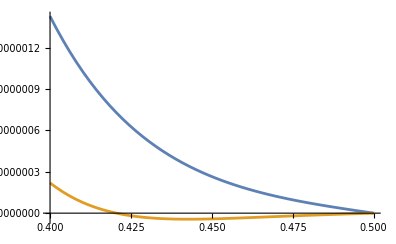

```mathematica
Plot[{%139,Normal[%137]}/.genBos/.Δσ->1//Evaluate,{z,4/10,1/2},WorkingPrecision->30]
```

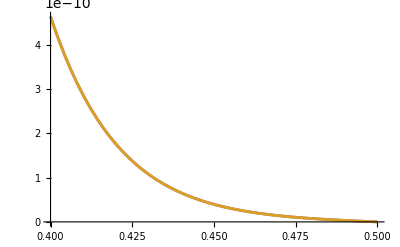

```mathematica
Plot[{%114,%121}/.genBos/.Δσ->1//Evaluate,{z,4/10,1/2},WorkingPrecision->30]
```

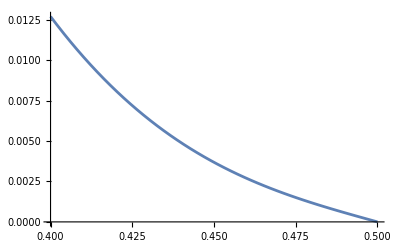

```mathematica
Plot[Normal[%69]//Evaluate,{z,4/10,1/2},WorkingPrecision->30]
```

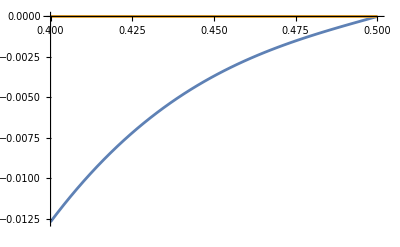

```mathematica
Plot[{%100,%103},{z,4/10,1/2},WorkingPrecision->30]
```

```mathematica
((-1+2 z) (-1646011545175701471965076780139473611126362650875685939321300653072633109424029937878887847247386701+2374693003169189948262079635413320022492042697280125574252694473860127551715208711100165964103287125 Log[2]))/7682729186787696696125817558540079296318790619471932151005681821232606302838633183288537427970+(2 (-1/2+z)^3 (-94893260112983586035929671803973243200118626340654599883634244166019112101051175653710039123990132757+136902068621358621342298803992659675627470936310039608718362764934205654106480881336738731588172280240 Log[2]))/6402274322323080580104847965450066080265658849559943459171401517693838585698860986073781189975//N//Expand
```

-0.916873+5.38947 z-10.6672 z^2+7.11145 z^3

```mathematica
N[%137/.zvalsTable[40/100,49/100,5]/.Δ[i_]->2i+2/.Δσ->1,50]
```

{0.19999879270820296616962758641589268184087075875402-0.03895785005994784311545916229670568270134945130307 C[0]-0.083548081870381752996615380217186411831907850824827 C[1]-0.081199725623370783636359514700794432919501825632711 C[2]-0.069341641166422100097470570000107342348580204118727 C[3]-0.05714833876925832868317143609773007481403202575477 C[4]-0.046590484492043721836242809862214203717309789193197 C[5],0.16399922287250849724641553964729792593794606884595-0.032523700772004907863992742532483946340040450538009 C[0]-0.06840082939756653108868875810053205823844391951845 C[1]-0.063307731872574195468823775508059326546511694410469 C[2]-0.050414411383299291371606774362446634058352997992523 C[3]-0.03825885389743978806204554711611575603580641095469 C[4]-0.028527291897741442783636580888155762547414198575442 C[5],0.12799952672916313261644162898355635631265510948674-0.025747365368904706109091621639033665475988098926363 C[0]-0.053305687321484855104089126111835787798543810442174 C[1]-0.047376449564629681247720202744966025571918984532629 C[2]-0.035511909395339361748560336097269806411511178836535 C[3]-0.025009850438127177924262848466254942098309171991275 C[4]-0.017148181576321749515430646548836950174770192969743 C[5],0.091999732004236581093385287962627029635761208116895-0.018702898379449348912334867369642289336556760590352 C[0]-0.038264811806224659726618718085944182963319639846065 C[1]-0.032957455017311497092285652314217762090406510872976 C[2]-0.023529494095498408071467251354186245014499779744064 C[3]-0.015562364773611345715006476324704998478373054271043 C[4]-0.0099133131435631588527547872063054205503485045161498 C[5],0.0559998664237985514909259501224690025780276921769-0.011465149327702954523234091925304654001712738988993 C[0]-0.023270199281573011559170187801316440787469220899172 C[1]-0.019615153679540673394833413718143049648305343037213 C[2]-0.013529383050145014078706450831205447324056771148362 C[3]-0.0085444629610879508085439533126813725618941218679851 C[4]-0.0051441334690152480860967018967973837397329727704278 C[5],0.019999957713918752622743049001041331810217889107249-0.0041095232393096166996908818603753393980208287262545 C[0]-0.0083066892539826783118525238845979818430099127996735 C[1]-0.0069238865422196298814202955886936635811835364670381 C[2]-0.0046891379425492679041642818817656911621586600266272 C[3]-0.002887843973045160155812691226074894274505468061009 C[4]-0.0016842744296264356146333092292867857439749933965236 C[5]}

```mathematica
Solve[%==0,WorkingPrecision->50]
```

{{C[0]→3.7219767471326947025867845429452849651,C[1]→0.45532812701087514785146319548650581444,C[2]→0.048009707093396128021732601186647108865,C[3]→0.0047866698597869135690600661652546509192,C[4]→0.00045287175287018745440117976943805100372,C[5]→0.000041808977814321891891322215241348639274,C[6]→3.3206755765027613295664621694497614527×10^-6,C[7]→3.9569679006103612997752323628225293644×10^-7,C[8]→2.4774404587676206811282401269582497186×10^-9,C[9]→5.2330070687965320390488909899790156044×10^-9}}

```mathematica
%83//Dimensions
```

{10}

```mathematica
getAvCs[5,Table[2i,{i,1,10}],40/100,49/100,1,50]
```

{{2.04617655704708877239558226105039222940835,0.00443814007100216602846424001141359635419},{1.1619630445732315324821296515404502193857,0.00354809423462980267579603921645433134537},{0.263008760362502838940692414514672090515934,0.00211087341868093304543068512741921149011},{0.0207821077222348973389437294945425580623368,0.0008120367718286918883250568404900121353128},{0.00714407503161492005222020521560356344968879,0.0001477196380277699490634790441527835853142}}

```mathematica
crossingEq[4]/.Δσ->1/.Δ[i_]->2i+2/.C[i_]->%143[[i+1,1]];
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

```mathematica
Series[crossingEq[4]/.Δσ->1/.Δ[i_]->2i+2/.C[i_]->%143[[i+1,1]],{z,1/2,11}]//Normal
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

9.585331485151781208501438863178×10^-10 (-1/2+z)-5.7307756399343680604113802670850609×10^-7 (-1/2+z)^3+0.000142539522633470663733681976376354175 (-1/2+z)^5-0.018975275802901254378610895357056819353 (-1/2+z)^7+1.46044815355570120910081080952275570326 (-1/2+z)^9-70.440477537460588226298112839261195637784 (-1/2+z)^11

```mathematica
1-%160/%150/.z->4/10
```

0.26098374877717076373150217033654

Plot::precw: The precision of the argument function (9.585331485151781208501438863178×10^-10 (-1/2+z)-5.7307756399343680604113802670850609×10^-7 (-1/2+z)^3+0.000142539522633470663733681976376354175 (-1/2+z)^5-0.018975275802901254378610895357056819353 (-1/2+z)^7+1.46044815355570120910081080952275570326 (-1/2+z)^9-70.440477537460588226298112839261195637784 (-1/2+z)^11) is less than WorkingPrecision (40.).

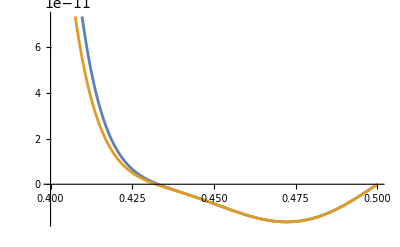

```mathematica
Plot[{%150,%},{z,4/10,1/2},WorkingPrecision->40]
```

```mathematica
fhs[z_]:=-(9.585331485151781208501438863178037545261364773467`32.91058097198113*^-10 (-1/2+z)-5.73077563993436806041138026708506089051269190158881`35.040996740878064*^-7 (-1/2+z)^3+0.0001425395226334706637336819763763541754878878687113195786`36.935539966803034 (-1/2+z)^5-0.0189752758029012543786108953570568193534956219169828948872`38.593651454130395 (-1/2+z)^7+1.4604481535557012091008108095227557032601684531621177725746`40.01843981512338 (-1/2+z)^9-70.4404775374605882262981128392611956377838052353371715904894`41.26580123755122 (-1/2+z)^11)
```

```mathematica
deqn=y''[x]+k^2 y[x]-Sin[x]
```

-Sin[x]+k^2 y[x]+y''[x]

```mathematica
DSolve[deqn==0/.k->1,y[x],x]//FullSimplify
```

{{y[x]→(-x/2+C[1]) Cos[x]+C[2] Sin[x]}}

```mathematica
deqn/.y->Function[x,(-x/2+C[1]) Cos[x]+C[2] Sin[x]]/.k->1//Simplify
```

0

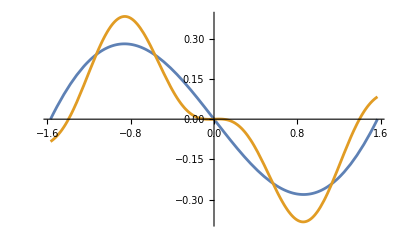

```mathematica
Plot[{(-x/2) Cos[x],FourierSeries[(-x/2) Cos[x],x,5]}//Evaluate,{x,-Pi/2,Pi/2}]
```

```mathematica
Integrate[(-x/2) Cos[x]Cos[x],{x,-Pi,Pi}]
```

0

```mathematica
FourierSeries[(-x/2) Cos[x],x,5]//ExpToTrig
```

Sin[x]/4-2/3 Sin[2 x]+3/8 Sin[3 x]-4/15 Sin[4 x]+5/24 Sin[5 x]

```mathematica
FourierSinSeries[(-x/2) Cos[x],x,2]
```

Sin[x]/4-2/3 Sin[2 x]

```mathematica
%186/.y->Function[{x},C0 Cos[k x+ϕ]]
```

True

```mathematica
Sum[C[n]Cos[n  x+ϕ[n]]+S[n]Sin[n  x+ϕ[n]],{n,0,5}]
```

C[0] Cos[ϕ[0]]+C[1] Cos[x+ϕ[1]]+C[2] Cos[2 x+ϕ[2]]+C[3] Cos[3 x+ϕ[3]]+C[4] Cos[4 x+ϕ[4]]+C[5] Cos[5 x+ϕ[5]]+S[0] Sin[ϕ[0]]+S[1] Sin[x+ϕ[1]]+S[2] Sin[2 x+ϕ[2]]+S[3] Sin[3 x+ϕ[3]]+S[4] Sin[4 x+ϕ[4]]+S[5] Sin[5 x+ϕ[5]]

```mathematica
deqn/.y->Function[{x},Sum[C[n]Cos[n  x+ϕ[n]]+S[n]Sin[n  x+ϕ[n]],{n,0,5}]]//Simplify
```

-C[1] Cos[x+ϕ[1]]-4 C[2] Cos[2 x+ϕ[2]]-9 C[3] Cos[3 x+ϕ[3]]-16 C[4] Cos[4 x+ϕ[4]]-25 C[5] Cos[5 x+ϕ[5]]-Sin[x]-S[1] Sin[x+ϕ[1]]-4 S[2] Sin[2 x+ϕ[2]]-9 S[3] Sin[3 x+ϕ[3]]-16 S[4] Sin[4 x+ϕ[4]]-25 S[5] Sin[5 x+ϕ[5]]+k^2 (C[0] Cos[ϕ[0]]+C[1] Cos[x+ϕ[1]]+C[2] Cos[2 x+ϕ[2]]+C[3] Cos[3 x+ϕ[3]]+C[4] Cos[4 x+ϕ[4]]+C[5] Cos[5 x+ϕ[5]]+S[0] Sin[ϕ[0]]+S[1] Sin[x+ϕ[1]]+S[2] Sin[2 x+ϕ[2]]+S[3] Sin[3 x+ϕ[3]]+S[4] Sin[4 x+ϕ[4]]+S[5] Sin[5 x+ϕ[5]])

```mathematica
N[%253/.C[i_]->0/.S[i_]->0/.x->z/.zvalsTable[-Pi/4,Pi/4,12],30]
```

{0.707106781186547524400844362105,0.608761429008720639416097542898,0.5,0.38268343236508977172845998403,0.258819045102520762348898837624,0.130526192220051591548406227895,0,-0.130526192220051591548406227895,-0.258819045102520762348898837624,-0.38268343236508977172845998403,-0.5,-0.608761429008720639416097542898,-0.707106781186547524400844362105}

```mathematica
Solve[%==0]
```

{}

```mathematica
Join[Table[C[n],{n,0,5}],Table[S[n],{n,0,5}]]
```

{C[0],C[1],C[2],C[3],C[4],C[5],S[0],S[1],S[2],S[3],S[4],S[5]}

```mathematica
MatrixRank[%]
```

9

```mathematica
N[D[%253/.x->z/.k->1/.zvalsTable[-Pi/4+1/100,Pi/4,11]/.ϕ[i_]->0,{{C[0],C[1],C[2],C[3],C[4],C[5],S[0],S[1],S[2],S[3],S[4],S[5]},1}],30]
```

{{1.,0,-0.0599960000799992380994708840789,5.48462868320707494234083262523,14.9880015999146691047185613719,17.797528592315465300202141987,0,0,2.99940001999973333523808677251,5.82398902877934920087589244979,0.599840012799512391788202175739,-16.1011793358658511693388269627},{1.,0,-0.897391069180031723497366006761,2.59027371960270035208486838487,12.3156308965197317245372039318,23.9919225577591602600004838835,0,0,2.86263676860266704661391982975,7.56904763213547172309190171761,8.56301556816806149470135671834,-0.622617043203246579627582003609},{1.,0,-1.66300136494456484287196788455,-0.766385210337798517184579321487,5.7814215339750475298091357296,18.6086974310117498398275212963,0,0,2.49688334933623085726094317623,7.96320624556312043312576558008,13.8410680601783621292641586754,15.1563973265765470236208738136},{1.,0,-2.29558361960294964492885041517,-3.98626210068178224030663506992,-2.56568051529793272441539713823,4.24559959337927787476067497873,0,0,1.93139738153768350361718682181,6.93611667034718098891492368901,14.7789473066731154917493300527,23.6214919954836407105237677988},{1.,0,-2.74453584331345155863433072961,-6.49468337687421607502453596988,-10.108256650774262415101751717,-12.1662683997824759765067969586,0,0,1.21141363900515883017454117973,4.67109064717799384778417674464,11.0825605110948025487301057223,20.6877237323117390692538258614},{1.,0,-2.97394511614142688502222512405,-7.84395384112590499435098726847,-14.4811651794048168132862716069,-22.7071428964064151692757051528,0,0,0.394525596354095833985806409237,1.57238294899371151597977822323,3.91099156823349079410643765062,7.77082115880810105625460515461},{1.,0,-2.96546036104076099820766046072,-7.79325991355795700146152759087,-14.3131838430133352330695991487,-22.2903856945433764100528707122,0,0,-0.453921631006938718766491334669,-1.8069587487628555615402252131,-4.4869553459001586174868300338,-8.89599379431528149318120834142},{1.,0,-2.71976029684722864097358377325,-6.35164928809030778448779949063,-9.65698690768841751808593410906,-11.1171084860755595354603181555,0,0,-1.26605842191167258337088730126,-4.8638000905775194396993336996,-11.4779180980147482246442520759,-21.2699294523707055171413792429},{1.,0,-2.25649914569696740910862300471,-3.776416128278852915114256129,-1.97262798177047916992903204619,5.42087624628856668462067563931,0,0,-1.97691972661230133444638850803,-7.0525655775806408536873441421,-14.8697255807071344251111256203,-23.3797797406738710043845827726},{1.,0,-1.61273443788259545088535066675,-0.527180008306568114714637156549,6.33029210955836291685443650632,19.3429455523527503273722368139,0,0,-2.52964179932011498121870205361,-7.98261117923464231493388538919,-13.5988014842361432048679188663,-14.2074085377565234053310216178},{1.,0,-0.839962678349358286636811562679,2.81614555363041340725353958396,12.6482089966005749060935102681,23.9308210193447616246370235671,0,0,-2.88001088521904244413646955506,-7.48794526026784282099262917645,-8.06367218941297725442675333376,1.82093529266883730528993790011},{1.,0,0,5.65685424949238019520675489684,15.,16.9705627484771405856202646905,0,0,-3.,-5.65685424949238019520675489684,0,16.9705627484771405856202646905}}

```mathematica
N[%253/.x->z/.k->1/.zvalsTable[-Pi/4,Pi/4,11]/.ϕ[i_]->0,30]
```

{0.707106781186547524400844362105+C[0]+5.65685424949238019520675489684 C[3]+15. C[4]+16.9705627484771405856202646905 C[5]+3. S[2.]+5.65685424949238019520675489684 S[3.]-16.9705627484771405856202646905 S[5.],0.599277666511346934530024146498+C[0]-0.84519767052428909313425374604 C[2]+2.79571343679278669364350800567 C[3]+12.6188029924677175329271747338 C[4]+23.9388507506460849926953381641 C[5]+2.8784789208434921696711041712 S[2.]+7.49559779999809388657227201904 S[3.]+8.10961226183396373161453931478 S[4.]-1.71214039678157616785610606379 S[5.],0.479248986720056831197656600453+C[0]-1.62192245236679274632290786296 C[2]-0.570713465593858722618702021263 C[3]+6.23122519502829638293911223844 C[4]+19.2129897821846496952676686775 C[5]+2.52376059849354350658543494676 S[2.]+7.9796169168820283308984460547 S[3.]+13.6444799303177755711757307462 S[4.]+14.3826639962723264287205795159 S[5.],0.349464179599098336705438500709+C[0]-2.26724872306277485132210753192 C[2]-3.83399189376045464958125280362 C[3]-2.13472257409927710665689002925 C[4]+5.10156694927144017318984417641 C[5]+1.9645822018358551921707752174 S[2.]+7.02143191653804492171585547284 S[3.]+14.8473216282139909856413805667 S[4.]+23.4515247833078284676812451842 S[5.],0.212565289552976673882910174017+C[0]-2.72889598606355511423514614924 C[2]-6.40432992739488323175588955915 C[3]-9.82291100917927596085387608699 C[4]-11.5019756812813639487437584109 C[5]+1.24624503900565927658782244769 S[2.]+4.79422133209077547624019317198 S[3.]+11.3362436153138742566105376596 S[4.]+21.0642957496141347651475664185 S[5.],0.0713391831992323403273377526578+C[0]-2.96946432564279819712827611333 C[2]-7.81717492776927615589374839472 C[3]-14.392394604217460848355520856 C[4]-22.4867933999942816597168160571 C[5]+0.426944514819855421331378005849 S[2.]+1.70052231642381339106328139214 S[3.]+4.2259883526214454656712687302 S[4.]+8.38714031037836008093052401702 S[5.],-0.0713391831992323403273377526578+C[0]-2.96946432564279819712827611333 C[2]-7.81717492776927615589374839472 C[3]-14.392394604217460848355520856 C[4]-22.4867933999942816597168160571 C[5]-0.426944514819855421331378005849 S[2.]-1.70052231642381339106328139214 S[3.]-4.2259883526214454656712687302 S[4.]-8.38714031037836008093052401702 S[5.],-0.212565289552976673882910174017+C[0]-2.72889598606355511423514614924 C[2]-6.40432992739488323175588955915 C[3]-9.82291100917927596085387608699 C[4]-11.5019756812813639487437584109 C[5]-1.24624503900565927658782244769 S[2.]-4.79422133209077547624019317198 S[3.]-11.3362436153138742566105376596 S[4.]-21.0642957496141347651475664185 S[5.],-0.349464179599098336705438500709+C[0]-2.26724872306277485132210753192 C[2]-3.83399189376045464958125280362 C[3]-2.13472257409927710665689002925 C[4]+5.10156694927144017318984417641 C[5]-1.9645822018358551921707752174 S[2.]-7.02143191653804492171585547284 S[3.]-14.8473216282139909856413805667 S[4.]-23.4515247833078284676812451842 S[5.],-0.479248986720056831197656600453+C[0]-1.62192245236679274632290786296 C[2]-0.570713465593858722618702021263 C[3]+6.23122519502829638293911223844 C[4]+19.2129897821846496952676686775 C[5]-2.52376059849354350658543494676 S[2.]-7.9796169168820283308984460547 S[3.]-13.6444799303177755711757307462 S[4.]-14.3826639962723264287205795159 S[5.],-0.599277666511346934530024146498+C[0]-0.84519767052428909313425374604 C[2]+2.79571343679278669364350800567 C[3]+12.6188029924677175329271747338 C[4]+23.9388507506460849926953381641 C[5]-2.8784789208434921696711041712 S[2.]-7.49559779999809388657227201904 S[3.]-8.10961226183396373161453931478 S[4.]+1.71214039678157616785610606379 S[5.],-0.707106781186547524400844362105+C[0]+5.65685424949238019520675489684 C[3]+15. C[4]+16.9705627484771405856202646905 C[5]-3. S[2.]-5.65685424949238019520675489684 S[3.]+16.9705627484771405856202646905 S[5.]}

```mathematica
D[%203,{Table[C[i],{i,0,10}],1}]/.x->z
```

{k^2 Cos[ϕ[0]],-Cos[z+ϕ[1]]+k^2 Cos[z+ϕ[1]],-4 Cos[2 z+ϕ[2]]+k^2 Cos[2 z+ϕ[2]],-9 Cos[3 z+ϕ[3]]+k^2 Cos[3 z+ϕ[3]],-16 Cos[4 z+ϕ[4]]+k^2 Cos[4 z+ϕ[4]],-25 Cos[5 z+ϕ[5]]+k^2 Cos[5 z+ϕ[5]],-36 Cos[6 z+ϕ[6]]+k^2 Cos[6 z+ϕ[6]],-49 Cos[7 z+ϕ[7]]+k^2 Cos[7 z+ϕ[7]],-64 Cos[8 z+ϕ[8]]+k^2 Cos[8 z+ϕ[8]],-81 Cos[9 z+ϕ[9]]+k^2 Cos[9 z+ϕ[9]],-100 Cos[10 z+ϕ[10]]+k^2 Cos[10 z+ϕ[10]]}

```mathematica
%/.k->1//Simplify
```

C[0] Cos[ϕ[0]]-3 C[2] Cos[2 x+ϕ[2]]-8 C[3] Cos[3 x+ϕ[3]]-15 C[4] Cos[4 x+ϕ[4]]-24 C[5] Cos[5 x+ϕ[5]]-35 C[6] Cos[6 x+ϕ[6]]-48 C[7] Cos[7 x+ϕ[7]]-63 C[8] Cos[8 x+ϕ[8]]-80 C[9] Cos[9 x+ϕ[9]]-99 C[10] Cos[10 x+ϕ[10]]

```mathematica
getAvCs[5,Table[2i,{i,1,10}],40/100,49/100,1,50][[;;,2]]//Total
```

0.0110568641341693635870795002399299349103

```mathematica
Table[2i,{i,1,10}]
```

```mathematica
{2+x,4,6,8,10,12,14,16,18,20}
```

{2+x,4,6,8,10,12,14,16,18,20}

```mathematica
Table[getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50][[;;,2]]//Total,{x,-1/10,1/10,1/20}]
```

{0.0001329249435432818556012134,0.0001140169496906890002005252,0.00009470466577835307993553339,0.00007446775143602800372239072,0.0000529019379368624727719557}

```mathematica
getAvCs[9,{2,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50]
```

{{2.00017244668378500605325115269,0.00002807646267429475585119244},{1.19984980252138127604347084178,0.00002430016430427119598247733},{0.238213033684796378973807949548,0.000018674547657142744486127916},{0.0325518675630812904339933364963,0.000012493753845357455318765084},{0.00375118671624606057429536728976,6.94134518694287411036204611×10^-6},{0.000350322543435098829052203042258,3.032282655730164963951764556×10^-6},{0.0000440289042659725491092173680254,9.672986977711657595250976557×10^-7},{6.70240211087997698887617415216×10^-7,1.9906517314791296679076380934×10^-7},{6.54085643079930883621418751491×10^-7,1.974558369481049634094133055×10^-8}}

```mathematica
getAvCs[9,{2+1/20,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50]
```

{{1.89884072788786620925085799945,0.00002124633799306264014217296},{1.1906904861809003421459374135,0.00001947195969580432843729012},{0.239601805891093661331050175227,0.000014899585974343920197752682},{0.0322186344237966318900362756303,9.9598349207986681016632988×10^-6},{0.00383989465778087196722909240398,5.53095042283025843003746421×10^-6},{0.000328314071441718832346368223634,2.415044680551473518326036568×10^-6},{0.0000484882467664597409164774956181,7.699845309034232385386194733×10^-7},{3.9501677312757430739306806416×10^-8,1.58357315188487629191597541103×10^-7},{6.9967503646931012796367575158×10^-7,1.569590254480402741794123077×10^-8}}

```mathematica
%298[[;;,;;,1]]
```

{{4.64011729579651236849604568453,1.28254571757091559780996402667,0.229426597880533247656817335441,0.0349558222256018596161034529456,0.00312576861707487993396215550126,0.000506385536142830024085138775763,0.0000124346136335497791626530470931,5.14127329205790397197494198023×10^-6,3.30962881380102280945384825296×10^-7},{3.89145298672091792806119549529,1.2626466305555485273923809723,0.230726589089422595945847679648,0.0345085562050881610257923605319,0.00323768512289119271226442982675,0.000478194479466127165719026887625,0.0000181313837621549785598705090334,4.33448288149241958197268688131×10^-6,3.89250232483161912656448500268×10^-7},{3.36714902962920424181754714622,1.24914644407810763108292676114,0.231814916756008068953939923884,0.0341734230048197863641430131277,0.00332317438723509952501657888032,0.000456761840201034853181628295089,0.0000224667759791910565790121160874,3.72073144098235898271311553789×10^-6,4.33600239737871220671843073534×10^-7},{2.98129533940230492670064124955,1.23905955169749345904650169736,0.232807442271260547642433337994,0.0338942377872949410788952493932,0.0033955528050217087729740786112,0.000438685602009045273099761192362,0.0000261260468605838487774194639759,3.2028559100401973476879723661×10^-6,4.71027583996375779619719878105×10^-7},{2.68698663812542236090895118293,1.23074329738890035599615618835,0.233775159709884007132407375025,0.0336393756721736256632153666758,0.00346241367064358074573728474396,0.000422033239378800577112822013298,0.0000294987995889379359886956194826,2.7256340174401976150291975032×10^-6,5.05519880586810922382457527651×10^-7},{2.45645577613574420888770149482,1.2232106929679411902051059826,0.234766678492376486863038804745,0.0333892156012621467172700688151,0.00352854002204303654013528970333,0.000405592765663616821939365268621,0.0000328296006473810728810805227719,2.2544151016443134124339613101×10^-6,5.39579784753829570746176930101×10^-7},{2.27222856564716509874431952753,1.21582413903585896007022610733,0.235818287913782999647822844591,0.0331305566187917030262179220354,0.00359720215114739649729287225843,0.000388539337936275634301729678442,0.0000362850406460680548811055221321,1.76560646270396240898758439614×10^-6,5.7491159339658872291027793514×10^-7},{2.12277058619013235153146667145,1.208144373607262230569995171,0.236958957054295495731398721596,0.0328538746837154680177928101741,0.00367079667078751871445202490962,0.000370271213080172348834498957503,0.0000399867405869778268096128234352,1.24199147225879585979273324914×10^-6,6.12759170495601790457793833347×10^-7},{2.00017244668378500605325115269,1.19984980252138127604347084178,0.238213033684796378973807949548,0.0325518675630812904339933364963,0.00375118671624606057429536728976,0.000350322543435098829052203042258,0.0000440289042659725491092173680254,6.70240211087997698887617415216×10^-7,6.54085643079930883621418751491×10^-7},{1.89884072788786620925085799945,1.1906904861809003421459374135,0.239601805891093661331050175227,0.0322186344237966318900362756303,0.00383989465778087196722909240398,0.000328314071441718832346368223634,0.0000484882467664597409164774956181,3.9501677312757430739306806416×10^-8,6.9967503646931012796367575158×10^-7},{1.81471951323037522076375903297,1.18046033602811513093785858942,0.241144462108989870289840151781,0.0318491896370251620760641764343,0.00393821697271632475607313521005,0.000303923810718508878188766264559,0.0000534299011314429485343328980623,-6.59433499715555494199781157384×10^-7,7.50192729663491767418672778309×10^-7},{1.74480774678946364565835887306,1.16897937939223333379471263452,0.242858714597557456179839589044,0.0314391623752550406285599899693,0.00404729570412135387223313129878,0.000276868862591345249617497176126,0.0000589110833235522144656488109846,-1.4346523884339712249502753408×10^-6,8.06222957011146900062412777156×10^-7},{1.68684936161664490977057930939,1.15608180809691493146050938301,0.244761225562356018056011418321,0.0309846042500270841602798432688,0.00416816456131359018488993833773,0.000246893728591854367392149946406,0.000064983448746178251468725102684,-2.29345352271116381156903453899×10^-6,8.68292911721536052308263273982×10^-7},{1.63912839952121306745528524228,1.14160743056709654323947618133,0.246867912872520780520865970378,0.0304818621987786224393884636371,0.00430177961513702593561248990918,0.00021376256326691763860881995567,0.0000716946545525013743721263432561,-3.2425680498673346654266573753×10^-6,9.36888716241785228764307061468×10^-7},{1.60033018532199300507154892483,1.12539513564971767268831606252,0.249194179824846693635889013349,0.0299274920608157035422621503495,0.00444904031330837305518351115995,0.000177253898624106544603746470248,0.0000790894233555661661261850640738,-4.28831018570376922778907725191×10^-6,1.01246628616812966327870242478×10^-6},{1.56944536690955934149048645482,1.10727750973926306328019204117,0.251755095670125678079658060018,0.0293181982281384674813682894098,0.00461080423290722350816661486687,0.000137156964754533758824962868957,0.0000872102846242822673450291551938,-5.43668197505339920586689404929×10^-6,1.09545889257145344533475666618×10^-6},{1.5457025793511803246309164434,1.0870760438869646106277729418,0.254565543547456409190103529903,0.0286507903979287476158002793062,0.00478789767630001876894836967795,0.0000932690678486177236001171831199,0.0000960981023110535566594922925485,-6.69344774765277326968164873416×10^-6,1.18628253404481600311709169046×10^-6}}

```mathematica
getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20}/.x->7/100,40/100,49/100,1,50]
```

{{1.86331472508514059350929343918,0.00001857143729124335253165222},{1.18673744091643279238176823413,0.00001738407698717784949221029},{0.240199382627246242940425732742,0.000013277088162687701607843307},{0.0320754579944320281971753439414,8.8717813333297828846307774×10^-6},{0.00387800303080742092635623860297,4.9255018407633230749536133×10^-6},{0.000318860351009133156207091083087,2.150108614584513110970760256×10^-6},{0.0000504036796274196512105922167211,6.852961863393762339561126544×10^-7},{-2.314150272678064352214788650293×10^-7,1.40885773675715850809715472944×10^-7},{7.19256489660369807461859292363×10^-7,1.395783454092212010657941347×10^-8}}

```mathematica
getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20}/.x->6/100,40/100,49/100,1,50]
```

{{1.88074851068652664508791850912,0.00001990623682142410504166254},{1.18873616929600338303094978572,0.00001843981877747453759880537},{0.239897441515945386258708935927,0.000014096767326220282850929141},{0.0321477896531563923858646464041,9.4213834048615581090158987×10^-6},{0.00385875155163949721189833430369,5.23131582098499514899112723×10^-6},{0.00032363608914810823060195233986,2.283926436786603815544971434×10^-6},{0.0000494360656897481067306348761247,7.280714843155142649784789825×10^-7},{-9.45572173834286597562762154241×10^-8,1.4971044895281037766741986496×10^-7},{7.0936463043124901802427459696×10^-7,1.483571055779969755399758568×10^-8}}

```mathematica
getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20}/.x->1/20,40/100,49/100,1,50]
```

{{1.89884072788786620925085799945,0.00002124633799306264014217296},{1.1906904861809003421459374135,0.00001947195969580432843729012},{0.239601805891093661331050175227,0.000014899585974343920197752682},{0.0322186344237966318900362756303,9.9598349207986681016632988×10^-6},{0.00383989465778087196722909240398,5.53095042283025843003746421×10^-6},{0.000328314071441718832346368223634,2.415044680551473518326036568×10^-6},{0.0000484882467664597409164774956181,7.699845309034232385386194733×10^-7},{3.9501677312757430739306806416×10^-8,1.58357315188487629191597541103×10^-7},{6.9967503646931012796367575158×10^-7,1.569590254480402741794123077×10^-8}}

```mathematica
getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20}/.x->0,40/100,49/100,1,50]
```

{{2.00017244668378500605325115269,0.00002807646267429475585119244},{1.19984980252138127604347084178,0.00002430016430427119598247733},{0.238213033684796378973807949548,0.000018674547657142744486127916},{0.0325518675630812904339933364963,0.000012493753845357455318765084},{0.00375118671624606057429536728976,6.94134518694287411036204611×10^-6},{0.000350322543435098829052203042258,3.032282655730164963951764556×10^-6},{0.0000440289042659725491092173680254,9.672986977711657595250976557×10^-7},{6.70240211087997698887617415216×10^-7,1.9906517314791296679076380934×10^-7},{6.54085643079930883621418751491×10^-7,1.974558369481049634094133055×10^-8}}

```mathematica
%395[[;;,2]]/%378[[;;,2]]
```

{0.7090008827803349257116759,0.7588351480501472972794258,0.7548652628717608138038284,0.75408748415212638015532634,0.753645825138539942376747868,0.753203673961799871225499988,0.7526852729080737661874146689,0.75206750927531578385922698926,0.7513432262677955666574321923}

```mathematica
tenSt=ParallelTable[getAvCs[10,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-4/10,4/10,1/20}];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.006334133846231398452409521820140343486876632349453,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.01116972907256412549135202333120809266145358538018,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0096902843366354850591864857048361919312264550376731,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0072253143518309938586772734424853220916884926905759,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.010445752321679027252481453530114963422887746023689,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0089023759574885965460380239818064866156019319734045,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0044412018893903401491100841897008803430263499187504,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0080810527470737403889139771568366296832894315985815,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0042323822100216877387743430304949873420296689090112,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0064744919529053643785086283970107056413255941445486,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0074627709531645198970390732968383143229508912155698,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0048277518873460974264224690492817859944701326472577,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0069791607292051601921457770694388788707730255954778,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0059481346852032661608724373489997585738990419766837,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0029677931957018778965165039765251548722377322560965,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0053994424624241206175295412576210898247119251802218,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.01186313909529949593812551211369697364742935743019,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.013161837342903730530788890098359656972421140323075,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.014348772761894361475961412034877956454760464212119,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.013768856706483155538021288657041393120046138716957,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.012526882849824031107814876239680398015922865228259,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.01490239557030757094021296634116184829695683455043,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0054064570602627611819309070137771518696267056221344,«1»},«8»,{«1»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.015430513969791097359894002394100680674253883030163,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0079259364382367477783742533534431014599416828048193,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0087933101443442743649489084089610287075637073148252,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0095858844071113640679661334179655675899378843967599,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0091986688220309997471741618458530239919251359381892,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0083692552616353658542028687160674010936172350839243,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0099554957422020639243135681271500985381287050288792,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.010308027745187075813293342537589481336382323122391,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.015933896099332902634003782264999124942716443500328,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.010643991746114304378694342931080572517327732523358,«1»},«8»,{«1»}} may contain significant numerical errors.

```mathematica
sixSt=ParallelTable[getAvCs[6,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-4/10,4/10,1/20}];
```

```mathematica
sevenSt=ParallelTable[getAvCs[7,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-4/10,4/10,1/20}];
```

```mathematica
elevSt=ParallelTable[getAvCs[11,{2+x,4,6,8,10,12,14,16,18,20,22,24},40/100,49/100,1,50],{x,-4/10,4/10,1/20}];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0023183673554783020313312185975381422942184848332583,-0.0034652745165137802583569122032098377542114946143895,-0.0051761378114941268250416504953739867700153109406778,-0.007721169989037168098551313364203415695715037452892,-«81»,-«83»,-«83»,-0.035268836737195504067178492484465491337749583492924,-0.047099610814486668911921233263957395304460790605617,-0.053029230201098269904586234346904026907917565349231,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0014073487898207433095243685520994565301812654673607,-0.0022072203002497590841513517620958279393561000572995,-0.0034573508262726816739794424965946266947139815500797,-0.005402841495979231222264195389031177897720975139019,-«83»,-«83»,-«83»,-0.028944282776754586487277447322926977269046828076367,-0.039675456151762984615344199870302488093291026134707,-0.045433811821448400609224387847735143879811551440173,«2»},{«1»},«7»,{«1»},«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00050680021196452399648449282120440343958316993070864,-0.00087218455580683025033606963389531757201070144107834,-0.0014951708904655375762265612659661309798212936396027,-0.0025477730922056358396281751409191400030111990124557,-«82»,-«83»,-«83»,-0.018015972362984946233825912819573181111290857898882,-0.025751103159927039692168463974407241916836554247252,-0.030281099321668141501054970995900418673895899442295,«2»},«9»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0014073487898207433095243685520994565301812654673607,-0.0022072203002497590841513517620958279393561000572995,-0.0034573508262726816739794424965946266947139815500797,-0.005402841495979231222264195389031177897720975139019,-«83»,-«83»,-«83»,-0.028944282776754586487277447322926977269046828076367,-0.039675456151762984615344199870302488093291026134707,-0.045433811821448400609224387847735143879811551440173,«2»},{«1»},«7»,{«1»},«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00050680021196452399648449282120440343958316993070864,-0.00087218455580683025033606963389531757201070144107834,-0.0014951708904655375762265612659661309798212936396027,-0.0025477730922056358396281751409191400030111990124557,-«82»,-«83»,-«83»,-0.018015972362984946233825912819573181111290857898882,-0.025751103159927039692168463974407241916836554247252,-0.030281099321668141501054970995900418673895899442295,«2»},«9»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0014073487898207433095243685520994565301812654673607,-0.0022072203002497590841513517620958279393561000572995,-0.0034573508262726816739794424965946266947139815500797,-0.005402841495979231222264195389031177897720975139019,-«83»,-«83»,-«83»,-0.028944282776754586487277447322926977269046828076367,-0.039675456151762984615344199870302488093291026134707,-0.045433811821448400609224387847735143879811551440173,«2»},{«1»},«7»,{«1»},«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00084900547503661011741447197765606578906458877953308,-0.0013961124464413249635950275968925361955139470825895,-0.0022905462059443702310428507501020651829395417321665,-0.0037435026882693151697738450852876391429469769364324,-«83»,-«83»,-«83»,-0.023231718806477420759511017145332787751861004112879,-0.032577797131192421897205922928622521552909641643596,-0.037851552912683565968242344347740748207823713055322,«2»},{«1»},«8»,«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00050680021196452399648449282120440343958316993070864,-0.00087218455580683025033606963389531757201070144107834,-0.0014951708904655375762265612659661309798212936396027,-0.0025477730922056358396281751409191400030111990124557,-«82»,-«83»,-«83»,-0.018015972362984946233825912819573181111290857898882,-0.025751103159927039692168463974407241916836554247252,-0.030281099321668141501054970995900418673895899442295,«2»},«9»,«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

```mathematica
twvSt=ParallelTable[getAvCs[12,{2+x,4,6,8,10,12,14,16,18,20,22,24},40/100,49/100,1,50],{x,-4/10,4/10,1/20}];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.013300368882789780734077830851496004523947635979599,-0.016397720334764077993800761560126019721129766990965,-0.020215962691114713296966013166213046430387514964352,-0.024922122597293231020287353539396677493622568525992,-«83»,-«83»,-«83»,-0.05714833876925832868317143609773007481403202575477,-0.069341641166422100097470570000107342348580204118727,-0.081199725623370783636359514700794432919501825632711,«3»},«9»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0078170684543016934060968063473645838912623940622303,-0.010110559505407117835561433160445173809096456725176,-0.013076487841157841970979810243935681512441063742496,-0.016911007601798435433717692120370782427992508084013,-«83»,-«83»,-«83»,-0.046781099952908270369064330706317291355427005508649,-0.059218593172509026061653715090667005389219127141622,-0.071904977650561408148648781660819794104642939948307,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.013300368882789780734077830851496004523947635979599,-0.016397720334764077993800761560126019721129766990965,-0.020215962691114713296966013166213046430387514964352,-0.024922122597293231020287353539396677493622568525992,-«83»,-«83»,-«83»,-0.05714833876925832868317143609773007481403202575477,-0.069341641166422100097470570000107342348580204118727,-0.081199725623370783636359514700794432919501825632711,«3»},«9»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0078170684543016934060968063473645838912623940622303,-0.010110559505407117835561433160445173809096456725176,-0.013076487841157841970979810243935681512441063742496,-0.016911007601798435433717692120370782427992508084013,-«83»,-«83»,-«83»,-0.046781099952908270369064330706317291355427005508649,-0.059218593172509026061653715090667005389219127141622,-0.071904977650561408148648781660819794104642939948307,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0078170684543016934060968063473645838912623940622303,-0.010110559505407117835561433160445173809096456725176,-0.013076487841157841970979810243935681512441063742496,-0.016911007601798435433717692120370782427992508084013,-«83»,-«83»,-«83»,-0.046781099952908270369064330706317291355427005508649,-0.059218593172509026061653715090667005389219127141622,-0.071904977650561408148648781660819794104642939948307,«3»},«9»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0078170684543016934060968063473645838912623940622303,-0.010110559505407117835561433160445173809096456725176,-0.013076487841157841970979810243935681512441063742496,-0.016911007601798435433717692120370782427992508084013,-«83»,-«83»,-«83»,-0.046781099952908270369064330706317291355427005508649,-0.059218593172509026061653715090667005389219127141622,-0.071904977650561408148648781660819794104642939948307,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.013300368882789780734077830851496004523947635979599,-0.016397720334764077993800761560126019721129766990965,-0.020215962691114713296966013166213046430387514964352,-0.024922122597293231020287353539396677493622568525992,-«83»,-«83»,-«83»,-0.05714833876925832868317143609773007481403202575477,-0.069341641166422100097470570000107342348580204118727,-0.081199725623370783636359514700794432919501825632711,«3»},«9»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0078170684543016934060968063473645838912623940622303,-0.010110559505407117835561433160445173809096456725176,-0.013076487841157841970979810243935681512441063742496,-0.016911007601798435433717692120370782427992508084013,-«83»,-«83»,-«83»,-0.046781099952908270369064330706317291355427005508649,-0.059218593172509026061653715090667005389219127141622,-0.071904977650561408148648781660819794104642939948307,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0045787537864698950541620922177354393361283186955621,-0.0062140082757906316534194511167495509568917040115776,-0.0084326812400035579201534521816101559368896171041419,-0.011441579907750676755355293608874283880662402739255,-«83»,-«83»,-«83»,-0.038126998646858177189491283953175984760510695548808,-0.050274098217316410617235676009189655162646640569906,-0.063166324378685050377212782538827514847232749976182,«3»},{«1»},«8»,«2»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

```mathematica
ParallelTable[getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-4/10,4/10,1/20}]
```

```mathematica
nineSt={{{4.6401172957965123684960456845340213782669630533033366098971`30.6934811674212,0.0001589568400043449094765972566881309468000381002564108279`25.901907417145548},{1.2825457175709155978099640266745170689439915439592936786221`30.693444021650016,0.0000564749365482165580687569552928878267038979456886458853`26.010766484090013},{0.2294265978805332476568173354413552983614529258842726752672`30.69355874178182,0.0000452859449626544602888595054063782552553484144968097039`26.662011722372792},{0.0349558222256018596161034529456401412761449749660083733619`30.69305016583081,0.0000304285822579781514310517601607462002501004024540093859`27.305140526191387},{0.0031257686170748799339621555012584848438809272058120974167`30.69606839702765,0.0000169406965275479632343885085550617406802025200447445124`28.10109683978835},{0.0005063855361428300240851387757627475267941554295713626011`30.686465766688244,7.4110356223507016500937539631170381711132956077378434`28.521128204106535*^-6},{0.0000124346136335497791626530470931094272723521459125321098`30.797591579652117,2.3674854505629578478287348770870906840496001778937578`29.74425170713023*^-6},{5.1412732920579039719749419802252694784811705661115375`30.649158776500947*^-6,4.879835931055164272233970902056684840036195860942235`29.29061615574461*^-7},{3.309628813801022809453848252955352879641844974210567`30.77327535159097*^-7,4.84902879100888044753219385521096703599071423806841`29.600020029449958*^-8}},{{3.8914529867209179280611954952885924375100665324372941398097`30.69347939441247,0.0001191028337193303221490338026953807589018821811410717198`25.853740599431177},{1.2626466305555485273923809722982468465787548914418546424495`30.693445780168226,0.0000510651031060831613206198280664615186167085915517931793`25.97460372748089},{0.2307265890894225959458476796478409166243463120092614407247`30.69354811283215,0.0000404986719839116142548645810897635150044946162008197296`26.611797805409058},{0.0345085562050881610257923605319198670395307104265502073442`30.693090441388485,0.0000271979761708186725008771131299322134447004682666211234`27.262798546175578},{0.0032376851228911927122644298267477137682834623807745002333`30.69570353365891,0.0000151371162979811109085511344267129481343243744944311991`28.037330767851163},{0.0004781944794661271657190268876250617599746091641492995624`30.686858917786434,6.6209032727731160963389213323105934892949175555505611`28.498194053819685*^-6},{0.0000181313837621549785598705090334096017581725544748456721`30.75406217948578,2.1147712767515839417355256596982298625497509887221604`29.488627007820114*^-6},{4.3344828814924195819726868813070446506537152452329629`30.64678739367036*^-6,4.358318446672644606935985026049554835889737664865816`29.31402704879683*^-7},{3.89250232483161912656448500268365847436533036892368`30.752507758290477*^-7,4.33013200025275921056165470689786732600598091564836`29.460360163156505*^-8}},{{3.3671490296292042418175471462184677935625960589228597759567`30.69347804573961,0.0000937057128476322206733029500843061403294749177809167389`25.813162541511772},{1.2491464440781076310829267611436854240287631649508861649981`30.693447233687866,0.0000468074901838619399660422626297352724273022794936988916`25.942195243541406},{0.2318149167560080689539399238844378823613461599648173633649`30.693540067777835,0.0000368538025925610122971756810356152358661687864854432145`26.569515830487127},{0.0341734230048197863641430131276564222833163589383231357428`30.693121870631604,0.0000247383927358521101228629085285800119231709244423104084`27.226628502859462},{0.0033231743872350995250165788803201638198154825802917751806`30.69544234685529,0.0000137647441890485332499492876688515769389468184153716222`27.98519638979553},{0.0004567618402010348531816282950894640990585796104977275211`30.687191054095134,6.0197763580672811513518443772751574013223255920782834`28.477817787165595*^-6},{0.0000224667759791910565790121160874420150678103201733385851`30.736959197079447,1.9225244976245956232220046534189819539202151159259053`29.337719826447387*^-6},{3.7207314409823589827131155378907057661923779979327432`30.644308621443823*^-6,3.961603168313743510011428290445129886603941867278848`29.337102080382312*^-7},{4.336002397378712206718430735343551304125182782449154`30.740888225284802*^-7,3.9354207959312052005928445086616170689420617561974`29.36104457726172*^-8}},{{2.9812953394023049267006412495505948935684439764354551236979`30.6934769078404,0.0000759832784299771280743944468361426770962314882242620684`25.775714380761396},{1.2390595516974934590465016973574292579850815880950867421781`30.69344853747402,0.0000431240143027615287186144800779228492195613449415368212`25.91086553499415},{0.2328074422712605476424333379940943904057603196042777935051`30.693533310825188,0.0000337759760649238736020225714765055461812624913908690626`26.530521247477115},{0.0338942377872949410788952493931820627640852373917916678266`30.69314892869792,0.0000226618089226139671702748899153372824375972959209635413`27.19288031219373},{0.0033955528050217087729740786112026917992433318275670913688`30.695232140069802,0.0000126065693720021745491933773749541534732440795681542649`27.938191675626157},{0.0004386856020090452730997611923619036583826601878284812104`30.687496946156642,5.5125382803724100971084439105081529305475472706664009`28.458158804425086*^-6},{0.000026126046860583848777419463975905885843278073237195027`30.727245941461522,1.7603152832935748329758719024035340456095510418857376`29.224906380918426*^-6},{3.2028559100401973476879723661013008846446607380867794`30.641495262496004*^-6,3.626884518994389680674727476530844484434554028098108`29.361748768016717*^-7},{4.710275839963757796197198781049636322308421706366051`30.73296566150425*^-7,3.60240007270426115205099665855564331501672967806099`29.279455954603776*^-8}},{{2.6869866381254223609089511829285254322223202887045620012849`30.693475859347515,0.0000626825284276666394208371272027805726635410686055988285`25.738103610587704},{1.230743297388900355996156188347172099164356571572619070553`30.69344979501344,0.0000396656009844884932226651942790715945821617309044174589`25.87830877468923},{0.2337751597098840071324073750249436649845744224008611856732`30.6935271154358,0.000030937337293837830857921262380538807655639300307517541`26.49140906742036},{0.0336393756721736256632153666758343473224288023500832258906`30.693174298086145,0.0000207473289167570284298088160322670534011959034333537645`27.158668445091312},{0.0034624136706435807457372847439559491896839781957293626646`30.69504619476176,0.0000115391851400927397886824387696092271274054035791024799`27.891927315268525},{0.0004220332393788005771128220132976230961294202893320444377`30.687802349522254,5.0451177005998388149626541486162758406805223308282677`28.43759519132565*^-6},{0.0000294987995889379359886956194825957138763836654141106049`30.720555419374655,1.6108480667077234109390433733807182920359709643584507`29.127741219637578*^-6},{2.7256340174401976150291975032031984056753644917755395`30.63798191292677*^-6,3.318468634325738109433513983755364347680533372070419`29.390490820053017*^-7},{5.055198805868109223824575276511217659968433051143062`30.72680420236036*^-7,3.29555435588676427788538003973309677924084329801491`29.20470420866727*^-8}},{{2.4564557761357442088877014948174062938752856776795334626956`30.693474824115494,0.0000520700509222678347126805613311812196897313547758515438`25.697483405177373},{1.2232106929679411902051059826040169045880148095311600795414`30.693451080611773,0.0000362016967709064549038785298022826156157383853217455132`25.842273899274492},{0.2347666784923764868630388047448598284576386511766782391481`30.693521033014523,0.0000281315553019458376575994678356756112827657689007756235`26.449256304651588},{0.0333892156012621467172700688151054638336853516509838968049`30.693199756033277,0.0000188561456719108435355846904381266452948826435192661368`27.12140307353393},{0.0035285400220430365401352897033261905575352451084991139266`30.694869505381593,0.0000104851276904471620486908116997011698975461989347127336`27.842903575771498},{0.0004055927656636168219393652686211188716887792940241942157`30.688128833222777,4.5835853513807408725513267419563030263091573477554793`28.41447409150119*^-6},{0.0000328296006473810728810805227718979522342366644694921559`30.715368939324808,1.4632719642670920301070531199105110544120157344746165`29.035312169499722*^-6},{2.2544151016443134124339613101038784632600232040197373`30.633100670379047*^-6,3.013964021466773810699064054832505270242375002907926`29.42717833427077*^-7},{5.395797847538295707461769301007908893240074189200524`30.721562425812312*^-7,2.99260529137948254913510377225298147010557535230143`29.1301825389822*^-8}},{{2.2722285656471650987443195275275638721015528089449970293234`30.69347375030848,0.0000431431898903034336665645008943658112364535678865662591`25.65092634349681},{1.2158241390358589600702261073309472101422600094221582134762`30.69345245199438,0.000032567225209923129552778869909356960582860600197026434`25.80022023211988},{0.2358182879137829996478228445905661216851374496308016984`30.693514764845126,0.0000252176067572905966142980483057234470427960876611962013`26.401079165739517},{0.0331305566187917030262179220354468132306040747705320530092`30.693226593145006,0.000016893624249615176824992777375726342648960086869653654`27.078332474662794},{0.0035972021511473964972928722584332695228262938392444306702`30.69469310259672,9.3916493314218732427046368860951457108860344925556099`27.787772876055044*^-6},{0.0003885393379362756343017296784420584455970321997684883154`30.688497058074134,4.104847631108459960471694075395006395819613860415028`28.386825884125724*^-6},{0.000036285040646068054881105522132122167866429917314939952`30.711042442089262,1.3102030093206180126452752161303990703644186614335715`28.940757574193736*^-6},{1.7656064627039624089875843961380730237444369261604332`30.62539656054579*^-6,2.698135114348655285530891212032955390092360557463676`29.47874198524241*^-7},{5.749115933965887229102779351401529448350233071203871`30.71683585083704*^-7,2.67839528637021982045571568254166827244881731784652`29.050916413152613*^-8}},{{2.1227705861901323515314666714484061316990655108486323395681`30.693472600108965,0.0000352812395631219394962175861096619110711683469299885936`25.59484974354957},{1.2081443736072622305699951710042801982310572897271083034635`30.693453957705078,0.0000286349548884305224227411674231030386495533505592553251`25.7488329848403},{0.2369589570542954957313987215960987742677114214009646114232`30.69350809983861,0.0000220920840182791491554920579762676864668602186061881216`26.343249859089163},{0.0328538746837154680177928101741073441611566114898014679694`30.69325583145054,0.0000147906452293846375320614802330474104626185048499324757`27.02600185679769},{0.0036707966707875187144520249096172890084402590002009882749`30.694511486712287,8.2202843588557353292923502012223092338153817737435597`27.722664075866906*^-6},{0.0003702712130801723488344989575032919210496906901782432828`30.688929593231062,3.5920734315569013434028873129224950002095446774164692`28.351930631082308*^-6},{0.000039986740586977826809612823435205743872913439580329897`30.707272517027747,1.1462611092904540368957370492703176242874089012161795`28.83843236081677*^-6},{1.2419914722587958597927332491374584266585754391213114`30.610796968199523*^-6,2.359882638303162549562870543145543756634070768049039`29.560406265772958*^-7},{6.127591704956017904577938333468951111699769353530711`30.71242407106457*^-7,2.34188279393446294656390082332479236146604576333312`28.962141359799205*^-8}},{{2.0001724466837850060532511526923661174644541061648756933561`30.6934713442463,0.0000280764626742947558511924444400642264225220124787752142`25.52409852200854},{1.1998498025213812760434708417772365699917437535809620633771`30.693455641765688,0.0000243001643042711959824773319993617686239760691381641362`25.68315436468142},{0.2382130336847963789738079495482367249589990567136210381932`30.69350088189403,0.000018674547657142744486127916050279090545519718815226634`26.270573938477952},{0.0325518675630812904339933364962653650871879073471405658469`30.693288348603037,0.000012493753845357455318765083928477107377573419343288602`26.959351983773242},{0.0037511867162460605742953672897640733338463795991290633133`30.694321346405484,6.9413451869428741103620461147851844486708319586529459`27.642208751024352*^-6},{0.0003503225434350988290522030422579994167263298205445950785`30.689454068360245,3.0322826557301649639517645562954769699350232651687289`28.30549735914338*^-6},{0.0000440289042659725491092173680254398146845692139962944865`30.703907625900744,9.672986977711657595250976557005786894420651606054821`28.722059686142785*^-7},{6.702402110879976988876174152161155980840209629744124`30.57134744327924*^-7,1.990651731479129667907638093445340840086809551559271`29.717444107855307*^-7},{6.540856430799308836214187514906601410483335497298948`30.708231593840377*^-7,1.97455836948104963409413305529374249447281813837129`28.857970104975*^-8}},{{1.8988407278878662092508579994507383113687153585892666644966`30.69346995890253,0.0000212463379930626401421729613092368624845303790651926073`25.43000863763296},{1.1906904861809003421459374135010379424460150783345178779399`30.693457546880694,0.0000194719596958043284372901199829302960134653645168562544`25.59467411041345},{0.2396018058910936613310501752267670864029521112740787281519`30.693492991759864,0.0000148995859743439201977526823795434366508994067717725312`26.174347769350796},{0.0322186344237966318900362756302679846189250480280131573816`30.693324955372287,9.9598349207986681016632987528082189287188321424002547`26.869784713663538*^-6},{0.0038398946577808719672290924039816180645746648818001389391`30.694120860847306,5.5309504228302584300374642098972071965253380920058306`27.53755940443449*^-6},{0.0003283140714417188323463682236343300828425495613581677004`30.69010758013718,2.4150446805514735183260365676790162723759247503016636`28.239799117241237*^-6},{0.0000484882467664597409164774956181168384319486883490040352`30.70086874396706,7.699845309034232385386194733145830129840003316258782`28.58231429571583*^-7},{3.95016773127574307393068064156070760652077714522129`29.967985530797385*^-8,1.58357315188487629191597541103050658593268346924984`30.248478257700494*^-7},{6.996750364693101279636757515795700309139829622634564`30.70421921131405*^-7,1.56959025448040274179412307675360867336354228322655`28.729165913120017*^-8}},{{1.814719513230375220763759032967419534635447332893263584477`30.693468423872524,0.0000145867407301940475121271578896707959381587989295255722`25.295235128114193},{1.1804603360281151309378585894176093643580732473289790049352`30.69345971689338,0.0000140697239831069870648797601459388669526872153931888141`25.466171641986154},{0.241144462108989870289840151781268244692347391219162080822`30.6934843364855,0.0000107135788761839356071361381330362162293851771032937221`26.037172404638},{0.0318491896370251620760641764342656695402549876091403895347`30.693366449200138,7.1539556468741378446889173155614753216857152412862191`26.739965998047996*^-6},{0.0039382169727163247560731352100504332985350071925280821867`30.6939092847349,3.9698229975986547240451043978945501593649091941122675`27.39113858111807*^-6},{0.0003039238107185088781887662645591020550000859237631529064`30.690943880256732,1.7319530175828299319054291402071534895108721447177403`28.138518267618625*^-6},{0.0000534299011314429485343328980622920492712456065226010984`30.69811208009232,5.51636050902987975836372458522595273128371830485523`28.401255774394688*^-7},{-6.594334997155554941997811573841417001423729916918384`30.77918827084186*^-7,1.133118164023329225257569291061726390937145920096958`29.700495338676912*^-7},{7.501927296634917674186727783086011292131556095963648`30.700377504268456*^-7,1.12148180165591888110638812491683368363735606784944`28.557530993406633*^-8}},{{1.7448077467894636456583588730637258004459951520472881938214`30.693466721423086,7.9570491234412122819743544838074919330055898614961513`25.075936454136674*^-6},{1.1689793793922333337947126345158891661270887127504515893305`30.693462198914492,8.0337746304968249952724493951237496268356841567592057`25.25389633541664*^-6},{0.2428587145975574561798395890436005896358152544373686408039`30.69347484306089,6.0826356688466248505271302580870043727127557014487862`25.815072213739523*^-6},{0.0314391623752550406285599899692850350456064113419672133646`30.693413655812673,4.0547019584819068724100876799147369872760964799516145`26.525851916868927*^-6},{0.0040472957041213538722331312987835000778764091053800857175`30.693686677052163,2.2462755605487062622407644268144343904303969953060813`27.158492498422156*^-6},{0.0002768688625913452496174971761256951842459922575312278377`30.692046470244996,9.779433624010124127951857857641320672768160964019322`27.958568635124355*^-7},{0.0000589110833235522144656488109845989449385591261625483725`30.69561050575054,3.106456005505768842302379895697803953042876872912827`28.13353538357725*^-7},{-1.4346523884339712249502753407954254445041374688836931`30.712052103799675*^-6,6.35989948908193933486787705685759442483682564521593`29.07138978210236*^-8},{8.06222957011146900062412777155797388888776124491718`30.696711438273937*^-7,6.2697185790924536808153710643015511112693675507251`28.296329965255072*^-9}},{{1.6868493616166449097705793093865047544477148068490644761959`30.69346483555991,1.6639467480508320661068938458507934211406606909580498`24.698946287831546*^-6},{1.1560818080969149314605093830128012101098717670917122408666`30.693465045407645,1.7492076807830579536146684328059516522441115385018634`24.883806593005694*^-6},{0.2447612255623560180560114183205753173244210686640506419222`30.693464454463975,1.3136443085635113081994856758420191662124782411251011`25.430678971277043*^-6},{0.0309846042500270841602798432688408227087227114339507454829`30.693467465877923,8.709766637267396765906831137146337521574955907808176`26.14388254188362*^-7},{0.0041681645613135901848899383377286961533795709655140260428`30.69345370561932,4.789733195434212922469906431141789886017066894947988`26.745956212962927*^-7},{0.0002468937285918543673921499464060154393895388567189815336`30.693554911361776,2.064348226068558897174775819618351583222275409124633`27.594717598097102*^-7},{0.0000649834487461782514687251026840211707837040055517194701`30.693344205613432,6.47276839955143874456428011481002454302919756987207`27.6533037228062*^-8},{-2.2934535227111638115690345389884781329498882240308884`30.692676401677605*^-6,1.30428067270108753501223794158671103077821922096457`28.388051319542754*^-8},{8.682929117215360523082632739815793148183841504856276`30.69323123046413*^-7,1.2620602758255020087225515011162091517193848933798`27.771146945217936*^-9}},{{1.639128399521213067455285242282676434508940009132226241602`30.693462751542345,6.1687771777528784141822831509318414643841230365741276`24.88576405256162*^-6},{1.1416074305670965432394761813298405268126385563820618697789`30.693468316458944,6.7374971658318579023776422046729165104426650381199954`25.081075717349535*^-6},{0.2468679128725207805208659703781942932220535958646420299536`30.69345312713356,5.04964758885835196451425947944506032742977519426012`25.620582631882474*^-6},{0.0304818621987786224393884636370705891793115711318847718657`30.69352887137015,3.3746212257759666545686934262974803361692259572332865`26.35347047271123*^-6},{0.0043017796151370259356124899091782594291774194075795910537`30.693211493496396,1.88172106302833215995795375976226299248167035983967`26.948964347597645*^-6},{0.0002137625632669176386088199556700565624388536414505274898`30.695723746314172,8.27219764264324992482527205160534130110251363949948`27.896982061632887*^-7},{0.000071694654552501374372126343256063409344228705866480477`30.691296148385995,2.661491834278851955319507245496369956474231411301734`27.872846072703236*^-7},{-3.2425680498673346654266573753024769435756740641867046`30.683507497559802*^-6,5.53568699733620102305689350629498697246182944961995`28.52567080778117*^-8},{9.36888716241785228764307061467587016087383021801668`30.68994709060498*^-7,5.56026197683941061452840303735344634520610502322`28.070860455565096*^-9}},{{1.6003301853219930050715489248299148907316493706891341346755`30.693460455553534,0.0000135185940983174372083974332989057770203968929471715369`25.26355766938159},{1.1253951356497176726883160625202649794362290276073005261119`30.69347208245247,0.0000152567727655566599853582986841803733546305503149958156`25.468885828641255},{0.2491941798248466936358890133493106112986540473582259872523`30.693440829301444,0.0000113442552589637410053848515805640865478385268961460651`25.99454241600372},{0.0299274920608157035422621503495476363714806800740816576418`30.693599005356244,7.5630122022343615887334466184036667107401171228936928`26.73831611464234*^-6},{0.0044490403133083730551835111599508933638325406250466263258`30.69296149052009,4.2072396509211936370208762767179951947628412857692991`27.309563451044713*^-6},{0.0001772538986241065446037464702476571119951280248449336064`30.699074178087358,1.8440337719216386869531924329020943774961223156388768`28.355412412871914*^-6},{0.0000790894233555661661261850640737924051035023127164834758`30.689450113549853,5.910884164219354079506763717960961974868435528667493`28.199936344876793*^-7},{-4.2883101857037692277890772519115807296932304934655225`30.678193460345206*^-6,1.223899062416999105752283360847039666101386680213241`28.767902342075914*^-7},{1.0124662861681296632787024247797421635865689871583266`30.686866463343*^-6,1.22292436221987408736848340582404786148239101676993`28.399979780588264*^-8}},{{1.5694453669095593414904864548151034543986142563225206056097`30.693457934471095,0.0000213859298499126370807099261075562926596845521424793766`25.480633157706784},{1.1072775097392630632801920411668286637712509936114944633577`30.693476427408843,0.0000248559366621358769384274726779460011731433145942061574`25.69733674236715},{0.2517550956701256780796580600184679167173641032277330898157`30.693427539844333,0.0000183292522143077130863824708363972611129398905785290977`26.20792573672359},{0.0293181982281384674813682894098074675470550130181696494487`30.69367918881167,0.0000121997965493200527986838518649765030042549094746486807`26.96447850892824},{0.0046108042329072235081666148668732363890391736928333294517`30.692705362256074,6.7798021262136414047361608147299683111658528988300777`27.51041545154083*^-6},{0.0001371569647545337588249628689567910465124154530799889888`30.704870338893773,2.968453868128930242228131233599240316407471784668179`28.688619787177895*^-6},{0.0000872102846242822673450291551938027952384319461849597187`30.687790034309867,9.503229294277219759872256967337778653914485312752412`28.371146691952326*^-7},{-5.4366819750533992058668940492927661037033246483771317`30.674747506977305*^-6,1.964810567221205140895742712317635834050262905927487`28.8758791561589*^-7},{1.0954588925714534453347566661771494901114028940471342`30.683992882850152*^-6,1.95987507488705597658529813047417203058469984805501`28.576373587307152*^-8}},{{1.5457025793511803246309164433961602804013919461538469860439`30.69345517570452,0.0000298353153706822732028818448335257990598806318327837123`25.63593785383915},{1.0870760438869646106277729417969837921677254937698423085836`30.693481453323272,0.0000355977905257335672119534128040068469000940015781057154`25.865413374895112},{0.2545655435474564091901035299033015489572827169175140189174`30.69341324744562,0.0000260145684130814504388834074438170783219861673228515759`26.359231393642215},{0.0286507903979287476158002793062277041090465745940377296539`30.693770988615736,0.000017288403043006891150403760251794072488850007075472604`27.130069421946246},{0.0047878976763000187689483696779504556188401536264234568991`30.69244489332069,9.6009164764965290916761338571957654345246891284892108`27.649150514017403*^-6},{0.0000932690678486177236001171831198617029912818403786375925`30.717181785490258,4.2011297658635832311734860126029177677626474497133683`29.02376267098768*^-6},{0.0000960981023110535566594922925485194112830383650723520915`30.68629996519375,1.3440801725138432190367954507401771929765028061423642`28.482695174443496*^-6},{-6.6934477476527732696816487341556561008584143678578525`30.672347203435777*^-6,2.776842104437788420219816837184627868308382054197653`28.937929039569877*^-7},{1.1862825340448160031170916904613889676826547103333714`30.68132582369723*^-6,2.76750494633525380903810855521377199505736702660108`28.693396465082984*^-8}}};
```

```mathematica
rewFn[deltas_]:=Module[{stdsMeans,rewards},stdsMeans=ParallelTable[getAvCs[n,deltas,40/100,49/100,1,50],{n,6,10}];
rewards=Table[Log[If[Min[stdsMeans[[i,;;,1]]]<0,1,1/(stdsMeans[[i,;;4,2]]//Total)]],{i,Length[stdsMeans]}];
rewards//Total
]
```

```mathematica
Log[If[Min[nineSt[[1,;;,1]]]<0,1,1/(nineSt[[1,;;,2]]//Total)]]
```

8.0521958375103159468469366

```mathematica
%304[[1]]
```

-2/5

```mathematica
Table[2i+2,{i,0,15}]
```

```mathematica
{2-2/5,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32}
```

```mathematica
rewFn[{2-2/5,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00052844087849485969042605025729688012938931541946634,-0.00094256042805290735700446230063040027692411579437172,-0.0016666096302992704528038898894443170640183918033279,-0.0029098020382184212892556268036795974323692113347242,-«82»,-«83»,-«83»,-0.019092589215206649510548258080253095901978914365277,-0.022665130502797882652228804336153376235974218665574,-0.0044412018893903401491100841897008803430263499187504,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00029960391210827758878896250679606481039950878873311,-0.00055175184678675247839561756552722142448568470306293,-0.0010044493794748259104407622489985082070471341076917,-0.0017999815857970256835868310853009393460416873220276,-«83»,-«83»,-«83»,-0.012638817695213377895287163672835630292567727085242,-0.015105604935617826281888172350030716466122997294114,-0.0029677931957018778965165039765251548722377322560965,«1»},«8»,{«1»}} may contain significant numerical errors.

19.7271561827860415692131178

```mathematica
sixSt[[1]]
```

{{4.61643769509361874598364166188989835559,0.00296315798481775112317703090419366222},{1.29070893422497666402272482991644404445,0.00100380716833853643679581062185220206},{0.223457510053609917872373659651069703706,0.000696508417330720691383786871658151063},{0.0382502016333987240411527334176997726004,0.0003444289978340661368317876255807595475},{0.00184956774737559275626065988664947635183,0.00010924492843115080440897635005735989084},{0.000788369021270351021779790571126350769656,0.00001645934347831561473309361402397310598}}

```mathematica
stdsMeans[[1]]
```

{{4.61643769509361874598364166188989835559,0.00296315798481775112317703090419366222},{1.29070893422497666402272482991644404445,0.00100380716833853643679581062185220206},{0.223457510053609917872373659651069703706,0.000696508417330720691383786871658151063},{0.0382502016333987240411527334176997726004,0.0003444289978340661368317876255807595475},{0.00184956774737559275626065988664947635183,0.00010924492843115080440897635005735989084},{0.000788369021270351021779790571126350769656,0.00001645934347831561473309361402397310598}}

```mathematica
Table[rewFn[{2+x,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32}],{x,-2/5,2/5,1/20}]
```

$Aborted

```mathematica
rewFn[deltas_]
```

```mathematica
Table[(Count[%298[[i,;;,1]],_?Negative]),{i,Length[%298]}]
```

{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1}

```mathematica
Table[(1/(sixSt[[i,;;,2]]//Total))^(1-(Count[sixSt[[i,;;,1]],_?Negative])),{i,Length[sixSt]}];
```

```mathematica
Table[(1/(tenSt[[i,;;,2]]//Total))^(1-(Count[tenSt[[i,;;,1]],_?Negative])),{i,Length[tenSt]}];
```

```mathematica
Table[(1/(eightSt[[i,;;,2]]//Total))^(1-(Count[eightSt[[i,;;,1]],_?Negative])),{i,Length[eightSt]}]
```

{1,1,3600.1610286540649612751342351,3501.3449697942046933548234934,3408.1295436691269834444222648,3308.3113235635968472485634531,3197.1207089771070758841963485,3073.5075732679412525265487138,2938.4568750502480662834240985,2794.0738080499315626829810604,2643.0102018339175435207012959,2488.0754703732770013774545314,2331.9706564971482639483080523,2177.1168199608287270729265398,2025.5587696620062739126850984,1878.9273705951305824382692465,1738.4444667630034324865928215}

```mathematica
Table[(1/(nineSt[[i,;;,2]]//Total))^(1-(Count[nineSt[[i,;;,1]],_?Negative])),{i,Length[nineSt]}]
```

{3140.6838364821110551435006,3813.6424126876434161735038,4459.3494149661729412675192,5106.6468787107764074262059,5793.986167774637598624672,6573.638457860628699099205,7523.042503112959838861797,8770.625794786222868199772,10559.1418520012653866483,13428.63159845851355710632,1,1,1,1,1,1,1}

```mathematica
Table[(1/(sevenSt[[i,;;,2]]//Total))^(1-(Count[sevenSt[[i,;;,1]],_?Negative])),{i,Length[sevenSt]}]
```

{514.84736149718994440400424096281,578.05611536325314568729167853938,631.42677962910437938318328883646,677.60361014704701788845984132235,718.60202511215535693451568406969,756.00448723558852456809376635564,791.10103750657307004578153903778,824.99133769015845314468740398645,858.66236692644475765044868524063,893.05233752162158199103264281096,929.10907472879493180431109936992,967.8502307518151878575548383403,1010.4333069518293369206090903525,1058.2458823862823675501013005039,1113.0316522299737509924843841794,1177.078021912740699029628200302,1253.5107777355932364496821468049}

```mathematica
If[Min[tenSt[[1,;;,1]]]<0,10,(tenSt[[i,;;,2]]//Total)]
```

10

```mathematica
Table[If[Min[tenSt[[i,;;,1]]]<0,1,1/(tenSt[[i,;;,2]]//Total)],{i,Length[tenSt]}]
```

{1,1,1,1,1,1,1,1,39452.70982657149873948,24193.54325855621835694,17004.26778174362795778,1,1,1,1,1,1}

```mathematica
Table[((nineSt[[i,;;,2]]//Total))^(1-(Count[nineSt[[i,;;,1]],_?Negative])),{i,Length[nineSt]}]
```

{0.00031840199525467130722927519,0.00026221650899231937322482012,0.00022424795792943837948691401,0.00019582321310857113862417206,0.0001725927489371417353995387,0.0001521227561281864379676537,0.0001329249435432818556012134,0.0001140169496906890002005252,0.00009470466577835307993553339,0.00007446775143602800372239072,1,1,1,1,1,1,1}

```mathematica
Table[((tenSt[[i,;;,2]]//Total))^If[Min[tenSt[[i,;;,1]]]<0,2,1],{i,Length[tenSt]}]//Max
```

0.00005880876570725583997773

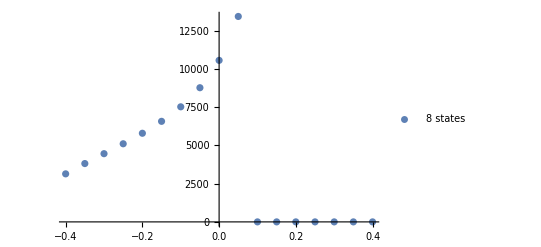

```mathematica
ListPlot[{{%304,Table[If[Min[nineSt[[i,;;,1]]]<0,1,1/(nineSt[[i,;;,2]]//Total)],{i,Length[nineSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

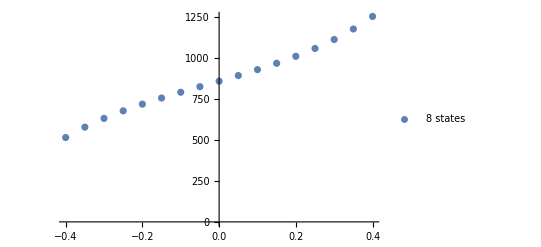

```mathematica
ListPlot[{{%304,Table[If[Min[sevenSt[[i,;;,1]]]<0,1,1/(sevenSt[[i,;;,2]]//Total)],{i,Length[sevenSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

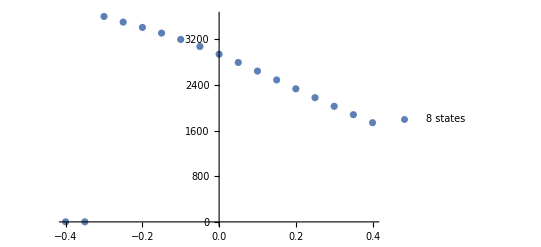

```mathematica
ListPlot[{{%304,Table[If[Min[eightSt[[i,;;,1]]]<0,1,1/(eightSt[[i,;;,2]]//Total)],{i,Length[eightSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

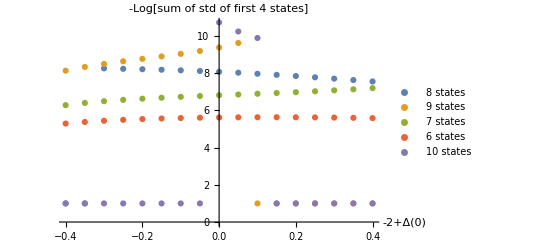

```mathematica
ListPlot[{{%304,Table[If[Min[eightSt[[i,;;,1]]]<0,1,Log[1/(eightSt[[i,;;4,2]]//Total)]],{i,Length[eightSt]}]}//Transpose,{%304,Table[If[Min[nineSt[[i,;;,1]]]<0,1,Log[1/(nineSt[[i,;;4,2]]//Total)]],{i,Length[nineSt]}]}//Transpose,{%304,Table[If[Min[sevenSt[[i,;;,1]]]<0,1,Log[1/(sevenSt[[i,;;4,2]]//Total)]],{i,Length[sevenSt]}]}//Transpose,{%304,Table[If[Min[sixSt[[i,;;,1]]]<0,1,Log[1/(sixSt[[i,;;4,2]]//Total)]],{i,Length[sixSt]}]}//Transpose,{%304,Table[If[Min[tenSt[[i,;;,1]]]<0,1,Log[1/(tenSt[[i,;;4,2]]//Total)]],{i,Length[tenSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"},AxesLabel->{Δ[0]-2,"-Log[sum of std of first 4 states]"}]
```

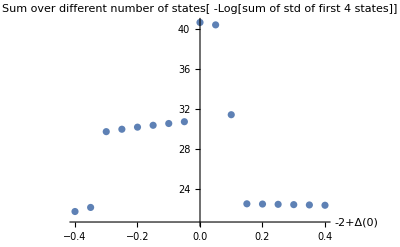

```mathematica
ListPlot[{{%304,Table[If[Min[nineSt[[i,;;,1]]]<0,1,Log[1/(nineSt[[i,;;4,2]]//Total)]],{i,Length[nineSt]}]+Table[If[Min[eightSt[[i,;;,1]]]<0,1,Log[1/(eightSt[[i,;;4,2]]//Total)]],{i,Length[eightSt]}]+Table[If[Min[tenSt[[i,;;,1]]]<0,1,Log[1/(tenSt[[i,;;4,2]]//Total)]],{i,Length[tenSt]}]+Table[If[Min[sixSt[[i,;;,1]]]<0,1,Log[1/(sixSt[[i,;;4,2]]//Total)]],{i,Length[sixSt]}]+Table[If[Min[sevenSt[[i,;;,1]]]<0,1,Log[1/(sevenSt[[i,;;4,2]]//Total)]],{i,Length[sevenSt]}]}//Transpose},AxesLabel->{Δ[0]-2,"Sum over different number of states[ -Log[sum of std of first 4 states]]"}]
```

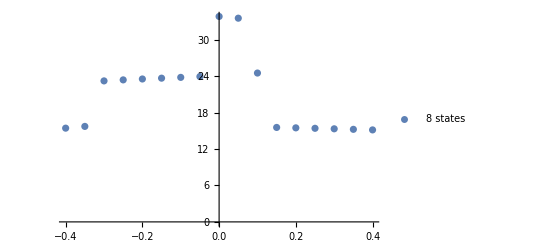

```mathematica
ListPlot[{{%304,Table[If[Min[nineSt[[i,;;,1]]]<0,1,Log[1/(nineSt[[i,;;4,2]]//Total)]],{i,Length[nineSt]}]+Table[If[Min[eightSt[[i,;;,1]]]<0,1,Log[1/(eightSt[[i,;;4,2]]//Total)]],{i,Length[eightSt]}]+Table[If[Min[tenSt[[i,;;,1]]]<0,1,Log[1/(tenSt[[i,;;4,2]]//Total)]],{i,Length[tenSt]}]+Table[If[Min[sixSt[[i,;;,1]]]<0,1,Log[1/(sixSt[[i,;;4,2]]//Total)]],{i,Length[sixSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

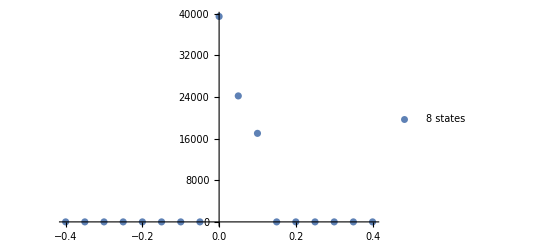

```mathematica
ListPlot[{{%304,Table[If[Min[tenSt[[i,;;,1]]]<0,1,1/(tenSt[[i,;;,2]]//Total)],{i,Length[tenSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

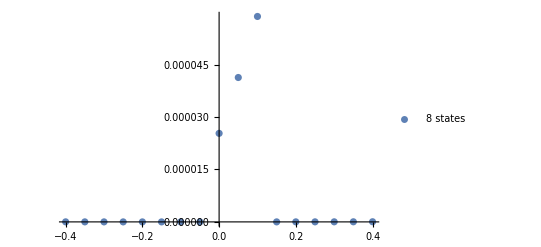

```mathematica
ListPlot[{{%304,Table[((tenSt[[i,;;,2]]//Total))^If[Min[tenSt[[i,;;,1]]]<0,2,1],{i,Length[tenSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

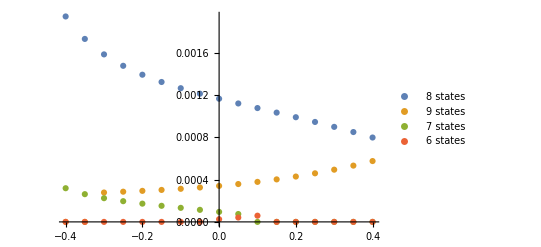

```mathematica
ListPlot[{{%304,Table[((sevenSt[[i,;;,2]]//Total))^If[Min[sevenSt[[i,;;,1]]]<0,2,1],{i,Length[sevenSt]}]}//Transpose,{%304,Table[((eightSt[[i,;;,2]]//Total))^If[Min[eightSt[[i,;;,1]]]<0,2,1],{i,Length[eightSt]}]}//Transpose,{%304,Table[((nineSt[[i,;;,2]]//Total))^If[Min[nineSt[[i,;;,1]]]<0,2,1],{i,Length[nineSt]}]}//Transpose,{%304,Table[((tenSt[[i,;;,2]]//Total))^If[Min[tenSt[[i,;;,1]]]<0,2,1],{i,Length[tenSt]}]}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

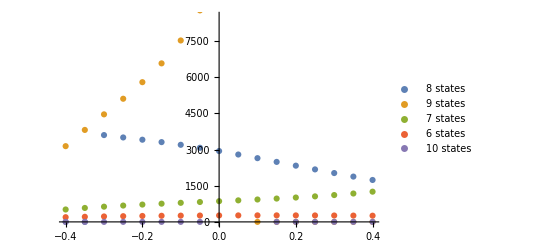

```mathematica
ListPlot[{{%304,%408}//Transpose,{%304,%409}//Transpose,{%304,%413}//Transpose,{%304,%419}//Transpose,{%304,%420}//Transpose},PlotLegends->{"8 states","9 states","7 states","6 states","10 states"}]
```

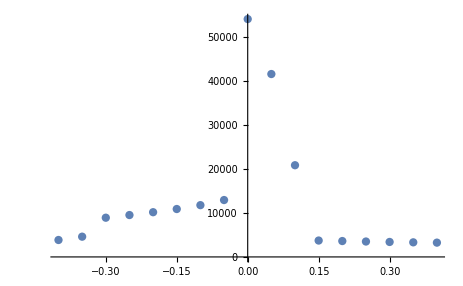

```mathematica
ListPlot[{{%304,%408+%409+%413+%419+%420}//Transpose}]
```

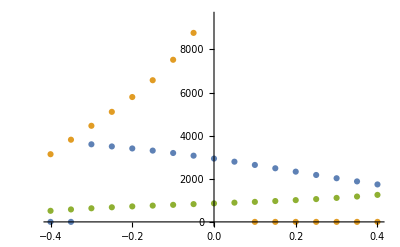

```mathematica
ListPlot[{{%304,%408}//Transpose,{%304,%409}//Transpose,{%304,%413}//Transpose}]
```

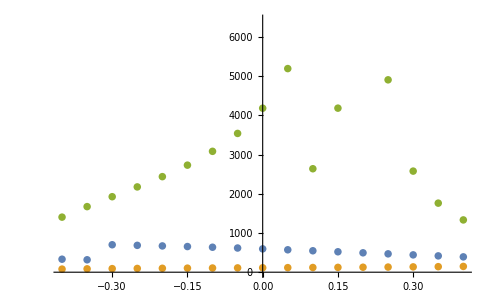

```mathematica
ListPlot[{{%304,%364}//Transpose,{%304,%367}//Transpose,{%304,%381}//Transpose}]
```

```mathematica
Table[x,{x,-4/10,4/10,1/20}]
```

{-2/5,-7/20,-3/10,-1/4,-1/5,-3/20,-1/10,-1/20,0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5}

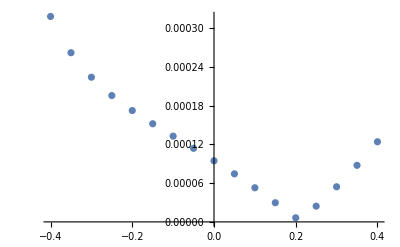

```mathematica
ListPlot[{%304,%302}//Transpose]
```

```mathematica
Sum[%298[[;;,i,2]],{i,9}]
```

{0.00031840199525467130722927519,0.00026221650899231937322482012,0.00022424795792943837948691401,0.00019582321310857113862417206,0.0001725927489371417353995387,0.0001521227561281864379676537,0.0001329249435432818556012134,0.0001140169496906890002005252,0.00009470466577835307993553339,0.00007446775143602800372239072,0.0000529019379368624727719557,0.0000297328946182367764064797,6.362216094272768951280687×10^-6,0.00002436655030088979870446041,0.00005445961531420086617124769,0.00008768557400691756460101067,0.0001241875630272852689261212}

```mathematica
%298
```

{{{4.64011729579651236849604568453,0.0001589568400043449094765973},{1.28254571757091559780996402667,0.000056474936548216558068756955},{0.229426597880533247656817335441,0.000045285944962654460288859505},{0.0349558222256018596161034529456,0.0000304285822579781514310517602},{0.00312576861707487993396215550126,0.00001694069652754796323438850856},{0.000506385536142830024085138775763,7.411035622350701650093753963×10^-6},{0.0000124346136335497791626530470931,2.3674854505629578478287348771×10^-6},{5.14127329205790397197494198023×10^-6,4.8798359310551642722339709021×10^-7},{3.30962881380102280945384825296×10^-7,4.8490287910088804475321938552×10^-8}},{{3.89145298672091792806119549529,0.0001191028337193303221490338},{1.2626466305555485273923809723,0.00005106510310608316132061983},{0.230726589089422595945847679648,0.000040498671983911614254864581},{0.0345085562050881610257923605319,0.0000271979761708186725008771131},{0.00323768512289119271226442982675,0.00001513711629798111090855113443},{0.000478194479466127165719026887625,6.620903272773116096338921332×10^-6},{0.0000181313837621549785598705090334,2.1147712767515839417355256597×10^-6},{4.33448288149241958197268688131×10^-6,4.358318446672644606935985026×10^-7},{3.89250232483161912656448500268×10^-7,4.3301320002527592105616547069×10^-8}},{{3.36714902962920424181754714622,0.00009370571284763222067330295},{1.24914644407810763108292676114,0.00004680749018386193996604226},{0.231814916756008068953939923884,0.000036853802592561012297175681},{0.0341734230048197863641430131277,0.0000247383927358521101228629085},{0.00332317438723509952501657888032,0.0000137647441890485332499492877},{0.000456761840201034853181628295089,6.019776358067281151351844377×10^-6},{0.0000224667759791910565790121160874,1.9225244976245956232220046534×10^-6},{3.72073144098235898271311553789×10^-6,3.9616031683137435100114282904×10^-7},{4.33600239737871220671843073534×10^-7,3.9354207959312052005928445087×10^-8}},{{2.98129533940230492670064124955,0.00007598327842997712807439445},{1.23905955169749345904650169736,0.00004312401430276152871861448},{0.232807442271260547642433337994,0.000033775976064923873602022571},{0.0338942377872949410788952493932,0.0000226618089226139671702748899},{0.0033955528050217087729740786112,0.0000126065693720021745491933774},{0.000438685602009045273099761192362,5.512538280372410097108443911×10^-6},{0.0000261260468605838487774194639759,1.7603152832935748329758719024×10^-6},{3.2028559100401973476879723661×10^-6,3.6268845189943896806747274765×10^-7},{4.71027583996375779619719878105×10^-7,3.6024000727042611520509966586×10^-8}},{{2.68698663812542236090895118293,0.00006268252842766663942083713},{1.23074329738890035599615618835,0.00003966560098448849322266519},{0.233775159709884007132407375025,0.000030937337293837830857921262},{0.0336393756721736256632153666758,0.000020747328916757028429808816},{0.00346241367064358074573728474396,0.0000115391851400927397886824388},{0.000422033239378800577112822013298,5.045117700599838814962654149×10^-6},{0.0000294987995889379359886956194826,1.6108480667077234109390433734×10^-6},{2.7256340174401976150291975032×10^-6,3.3184686343257381094335139838×10^-7},{5.05519880586810922382457527651×10^-7,3.2955543558867642778853800397×10^-8}},{{2.45645577613574420888770149482,0.00005207005092226783471268056},{1.2232106929679411902051059826,0.00003620169677090645490387853},{0.234766678492376486863038804745,0.000028131555301945837657599468},{0.0333892156012621467172700688151,0.0000188561456719108435355846904},{0.00352854002204303654013528970333,0.0000104851276904471620486908117},{0.000405592765663616821939365268621,4.583585351380740872551326742×10^-6},{0.0000328296006473810728810805227719,1.4632719642670920301070531199×10^-6},{2.2544151016443134124339613101×10^-6,3.0139640214667738106990640548×10^-7},{5.39579784753829570746176930101×10^-7,2.9926052913794825491351037723×10^-8}},{{2.27222856564716509874431952753,0.0000431431898903034336665645},{1.21582413903585896007022610733,0.00003256722520992312955277887},{0.235818287913782999647822844591,0.000025217606757290596614298048},{0.0331305566187917030262179220354,0.0000168936242496151768249927774},{0.00359720215114739649729287225843,9.39164933142187324270463689×10^-6},{0.000388539337936275634301729678442,4.104847631108459960471694075×10^-6},{0.0000362850406460680548811055221321,1.310203009320618012645275216×10^-6},{1.76560646270396240898758439614×10^-6,2.698135114348655285530891212×10^-7},{5.7491159339658872291027793514×10^-7,2.6783952863702198204557156825×10^-8}},{{2.12277058619013235153146667145,0.00003528123956312193949621759},{1.208144373607262230569995171,0.00002863495488843052242274117},{0.236958957054295495731398721596,0.000022092084018279149155492058},{0.0328538746837154680177928101741,0.0000147906452293846375320614802},{0.00367079667078751871445202490962,8.2202843588557353292923502×10^-6},{0.000370271213080172348834498957503,3.592073431556901343402887313×10^-6},{0.0000399867405869778268096128234352,1.146261109290454036895737049×10^-6},{1.24199147225879585979273324914×10^-6,2.3598826383031625495628705431×10^-7},{6.12759170495601790457793833347×10^-7,2.341882793934462946563900823×10^-8}},{{2.00017244668378500605325115269,0.00002807646267429475585119244},{1.19984980252138127604347084178,0.00002430016430427119598247733},{0.238213033684796378973807949548,0.000018674547657142744486127916},{0.0325518675630812904339933364963,0.000012493753845357455318765084},{0.00375118671624606057429536728976,6.94134518694287411036204611×10^-6},{0.000350322543435098829052203042258,3.032282655730164963951764556×10^-6},{0.0000440289042659725491092173680254,9.672986977711657595250976557×10^-7},{6.70240211087997698887617415216×10^-7,1.9906517314791296679076380934×10^-7},{6.54085643079930883621418751491×10^-7,1.974558369481049634094133055×10^-8}},{{1.89884072788786620925085799945,0.00002124633799306264014217296},{1.1906904861809003421459374135,0.00001947195969580432843729012},{0.239601805891093661331050175227,0.000014899585974343920197752682},{0.0322186344237966318900362756303,9.9598349207986681016632988×10^-6},{0.00383989465778087196722909240398,5.53095042283025843003746421×10^-6},{0.000328314071441718832346368223634,2.415044680551473518326036568×10^-6},{0.0000484882467664597409164774956181,7.699845309034232385386194733×10^-7},{3.9501677312757430739306806416×10^-8,1.58357315188487629191597541103×10^-7},{6.9967503646931012796367575158×10^-7,1.569590254480402741794123077×10^-8}},{{1.81471951323037522076375903297,0.00001458674073019404751212716},{1.18046033602811513093785858942,0.00001406972398310698706487976},{0.241144462108989870289840151781,0.000010713578876183935607136138},{0.0318491896370251620760641764343,7.1539556468741378446889173×10^-6},{0.00393821697271632475607313521005,3.9698229975986547240451044×10^-6},{0.000303923810718508878188766264559,1.73195301758282993190542914×10^-6},{0.0000534299011314429485343328980623,5.516360509029879758363724585×10^-7},{-6.59433499715555494199781157384×10^-7,1.1331181640233292252575692911×10^-7},{7.50192729663491767418672778309×10^-7,1.121481801655918881106388125×10^-8}},{{1.74480774678946364565835887306,7.957049123441212281974354×10^-6},{1.16897937939223333379471263452,8.033774630496824995272449×10^-6},{0.242858714597557456179839589044,6.08263566884662485052713×10^-6},{0.0314391623752550406285599899693,4.0547019584819068724100877×10^-6},{0.00404729570412135387223313129878,2.24627556054870626224076443×10^-6},{0.000276868862591345249617497176126,9.77943362401012412795185786×10^-7},{0.0000589110833235522144656488109846,3.106456005505768842302379896×10^-7},{-1.4346523884339712249502753408×10^-6,6.3598994890819393348678770569×10^-8},{8.06222957011146900062412777156×10^-7,6.269718579092453680815371064×10^-9}},{{1.68684936161664490977057930939,1.66394674805083206610689×10^-6},{1.15608180809691493146050938301,1.74920768078305795361467×10^-6},{0.244761225562356018056011418321,1.313644308563511308199486×10^-6},{0.0309846042500270841602798432688,8.7097666372673967659068311×10^-7},{0.00416816456131359018488993833773,4.7897331954342129224699064×10^-7},{0.000246893728591854367392149946406,2.06434822606855889717477582×10^-7},{0.000064983448746178251468725102684,6.47276839955143874456428011×10^-8},{-2.29345352271116381156903453899×10^-6,1.304280672701087535012237942×10^-8},{8.68292911721536052308263273982×10^-7,1.2620602758255020087225515×10^-9}},{{1.63912839952121306745528524228,6.16877717775287841418228×10^-6},{1.14160743056709654323947618133,6.737497165831857902377642×10^-6},{0.246867912872520780520865970378,5.049647588858351964514259×10^-6},{0.0304818621987786224393884636371,3.3746212257759666545686934×10^-6},{0.00430177961513702593561248990918,1.8817210630283321599579538×10^-6},{0.00021376256326691763860881995567,8.27219764264324992482527205×10^-7},{0.0000716946545525013743721263432561,2.66149183427885195531950725×10^-7},{-3.2425680498673346654266573753×10^-6,5.535686997336201023056893506×10^-8},{9.36888716241785228764307061468×10^-7,5.560261976839410614528403037×10^-9}},{{1.60033018532199300507154892483,0.00001351859409831743720839743},{1.12539513564971767268831606252,0.0000152567727655566599853583},{0.249194179824846693635889013349,0.00001134425525896374100538485},{0.0299274920608157035422621503495,7.5630122022343615887334466×10^-6},{0.00444904031330837305518351115995,4.20723965092119363702087628×10^-6},{0.000177253898624106544603746470248,1.844033771921638686953192433×10^-6},{0.0000790894233555661661261850640738,5.910884164219354079506763718×10^-7},{-4.28831018570376922778907725191×10^-6,1.223899062416999105752283361×10^-7},{1.01246628616812966327870242478×10^-6,1.222924362219874087368483406×10^-8}},{{1.56944536690955934149048645482,0.00002138592984991263708070993},{1.10727750973926306328019204117,0.00002485593666213587693842747},{0.251755095670125678079658060018,0.000018329252214307713086382471},{0.0293181982281384674813682894098,0.000012199796549320052798683852},{0.00461080423290722350816661486687,6.77980212621364140473616081×10^-6},{0.000137156964754533758824962868957,2.968453868128930242228131234×10^-6},{0.0000872102846242822673450291551938,9.503229294277219759872256967×10^-7},{-5.43668197505339920586689404929×10^-6,1.964810567221205140895742712×10^-7},{1.09545889257145344533475666618×10^-6,1.95987507488705597658529813×10^-8}},{{1.5457025793511803246309164434,0.00002983531537068227320288184},{1.0870760438869646106277729418,0.00003559779052573356721195341},{0.254565543547456409190103529903,0.000026014568413081450438883407},{0.0286507903979287476158002793062,0.0000172884030430068911504037603},{0.00478789767630001876894836967795,9.60091647649652909167613386×10^-6},{0.0000932690678486177236001171831199,4.2011297658635832311734860126×10^-6},{0.0000960981023110535566594922925485,1.344080172513843219036795451×10^-6},{-6.69344774765277326968164873416×10^-6,2.776842104437788420219816837×10^-7},{1.18628253404481600311709169046×10^-6,2.767504946335253809038108555×10^-8}}}

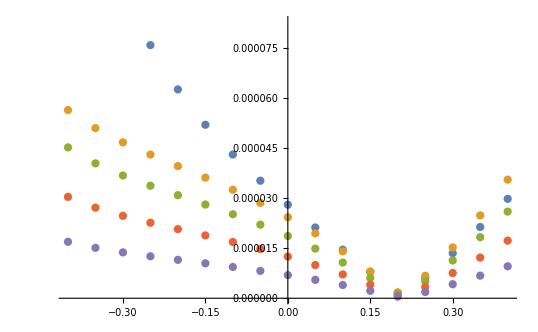

```mathematica
ListPlot[Table[{%304,%298[[;;,i,2]]}//Transpose,{i,5}]//Evaluate]
```

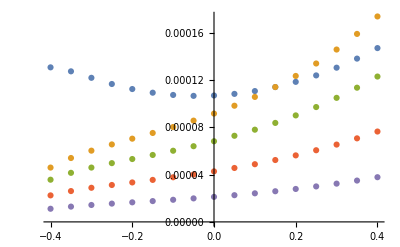

```mathematica
ListPlot[Table[{%304,%299[[;;,i,2]]}//Transpose,{i,5}]//Evaluate]
```

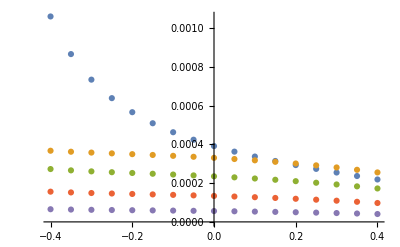

```mathematica
ListPlot[Table[{%304,%313[[;;,i,2]]}//Transpose,{i,5}]//Evaluate]
```

```mathematica
getAvCs[6,{2,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50]
```

{{1.98789924069708632723852497263514864236,0.00136272597382162905336586912200487203},{1.21019823556985322113026165359194008592,0.00112725716083903045420584358665033347},{0.230902867703967937487041124816049932277,0.000748999283443328179007584167224663139},{0.0366517219950640873826951053621477223515,0.0003689807245000609852193621247378969233},{0.00209150741394346739537408048801068296019,0.0001168613746072211397719091706209443339},{0.00076650730787255470108850660786583129488,0.00001759908302246532448803544581030147746}}

```mathematica
getAvCs[6,{2+4/10,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50]
```

{{1.53359068649407911064698713130898150304,0.0011616935524227789729896200298040722},{1.10120984834828209662437094451049162833,0.00132821300502218628093457141352334593},{0.244994155942322516842887631009390335343,0.000838379754021413860470764368407048138},{0.0340863450695666563543698947787424867452,0.0004097323089596298032379886193103846363},{0.00249451594379301961043931952901178339327,0.0001294746252408818062999780220719682872},{0.000730842413874221734428807844769869988268,0.00001948306603700145089856826772597114162}}

```mathematica
getAvCs[6,{2+4/10,4+4/10,6+4/10,8,10,12,14,16,18,20},40/100,49/100,1,50]
```

{{1.82418074161445480246645743307750845307,0.0004574380760145504732382175372803562},{1.01164959972605717302153795528017144501,0.000620675588887549106716757007553464432},{0.121672438523936646030344512698356561926,0.000600185664978436784812598641406977136},{0.0374997520926784011684347999335932852743,0.0003668227717313533843792759970519130902},{0.00150790256349307811360437017509935569762,0.00010167809616639784317421440402197640939},{0.000826635128109137823124220970229259725999,0.00001472087891590835487852217621432665851}}

```mathematica
ParallelTable[getAvCs[8,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-4/10,4/10,1/20}]
```

```mathematica
eightSt={{{4.6390418704250972733346215349555765885312560391966520965094`33.83609943645694,0.0001307176510080609096548957421786642958038469037906045619`28.982782449130866},{1.2829278247777466105264445318803675224742180113122045158204`33.83612731004112,0.0000459548108148625292165709017155650969602420017339706283`29.08684789530662},{0.2291201338264007096348848875960851560928957546934817402836`33.836043721841435,0.0000356865511534530133893203696822157908410606116115708721`29.72453128597468},{0.0351618268435091092168108691152768563762577746796966102152`33.83639128395804,0.0000224286918961198027521077620400776280017869317712711542`30.33610302869855},{0.003010998387924377844685718936451632748913654823966389457`33.83448724112666,0.0000111178224642232766256907078639068909473831432901753544`31.095104791280658},{0.0005566473778977576287731764598048586020394904543134587443`33.83933536159218,4.022728331294950240898531645037221257790000645582946`31.38927919002108*^-6},{-3.6461681121825756956769236261450236596115939037014857`33.97017726892047*^-6,9.363534574759277123688605714339892126908325729666101`33.06797590491709*^-7},{8.4627398370908216740662966057408976591700341928684941`33.841771941008545*^-6,1.045928147318031387891295170350148348228508436529739`31.61824711936048*^-7}},{{3.890396164319732851235764592279766559105492528585520739607`33.836097230182126,0.0001273544830747464538736877768234997546107841240800165057`29.04366596890647},{1.2630997898997011363557268079999787906099850028850326384871`33.83613063358212,0.0000540390973266254193693918931398711267051933266309486079`29.159768628767072},{0.230367079052865453034950442950606151895750055479561027635`33.836031842919745,0.0000415053413918587977832480675648886274135371149794201672`29.783542630346552},{0.0347501568381094911080049576030499264142949242886332704163`33.8364457629795,0.0000260786428536829336110345055817511669827850858812327338`30.402547745468375},{0.0031030725156409160464463306615469793967604643040945051069`33.83425098586071,0.0000129273798763375289357012865162679630948396595000295751`31.14309300877721},{0.0005371700847647004553703321622790486354413546140315712858`33.840060565179805,4.6790213105817624621237313662290092106692826772443899`31.466953184135228*^-6},{-7.487783764241874578198536381628597034721428625749596`34.11063619627869*^-7,1.089664872631615566449512398017462481487829661684664`33.956842570606675*^-6},{8.2372183944739581549610331341835002476468271304393955`33.8429966975252*^-6,1.217975729791554491675197007521849598812669824198484`31.693274680968397*^-7}},{{3.3661326123963068254962254890189639967877884069750683744534`33.836095551584876,0.0001218751954288399286282621240743847156641813710416014916`29.08497791860356},{1.2496542285596234078041072369926640698961109192769135152826`33.83613323043787,0.000060256411172154470448264697528121454590862796869308756`29.209267047000903},{0.2314149482619466297058175202509439683866653188605385677771`33.83602290626369,0.0000459473605798825212428956106772490384592432294906421372`29.823275619785505},{0.0344421285750535977040477350535142665136655995251835466707`33.83648806582781,0.0000288602931990217421605220551135944828430488444431028312`30.448037654372083},{0.0031734589649475118074423978548377252084903911011949270388`33.834080625234314,0.0000143058793212804651734975425166565064063629945097882728`31.1747640311843},{0.0005223686647166960633831738583775937121877237595893342753`33.840649398153154,5.1788884819327001624772427919791361999527668488010813`31.52135668768393*^-6},{1.4564488614409465931615204277369663768390988010409725`33.56250056750445*^-6,1.20642517089817652176874060576851462028234039697339`33.16204658448404*^-6},{8.0657583575602283211983766298201557585009502896993801`33.84397685606149*^-6,1.348999290497041130367557199890718128833067598722138`31.74541904286259*^-7}},{{2.980319199452767118503826549340212139635903936210834565732`33.83609413508687,0.0001166392176726910434774714246499102456457126725000761976`29.11706866457978},{1.2396136410811076845647942694231816375634787597853979318563`33.83613545050823,0.0000655268356217204861617052443831210481058844104014001974`29.24748530357878},{0.2323732568441802675472903375133153764529752314701561360138`33.836015441136766,0.0000497061564576880564643076561044870459930759625300840185`29.853922326788776},{0.0341858308023427137969965050030343801935481365575491303927`33.83652433776584,0.0000312102677063996691107460445733471466169188331606077996`30.483620256595447},{0.0032330885806782735337924570860625118267698864682257515299`33.83394278303225,0.000015470090418132254383057126131497126562771981705707146`31.198835274771298},{0.0005098892677771445194815007405209242793720776297658097705`33.84117352624056,5.6009897148532923875680620941763053391812976520854722`31.564740798583216*^-6},{3.3179501848470481071503472313297441497734094539154368`33.684047185611455*^-6,1.3050140926469286311561483934021587905002616789430181`32.95856083996131*^-6},{7.9211444626416082462115926614779598683574720817883461`33.84483878605025*^-6,1.459627524668067579371020916643623825280253525914293`31.786741389143746*^-7}},{{2.68604357421334530589167418578407379481843626324401769586`33.83609282973847,0.0001123777447147646610684851941095026328711389006408952033`29.1447066208767},{1.2313401712421082106559410780715493498680336038196215739332`33.836137513376805,0.0000703963436524595072396387453950246594167355584348405841`29.280182136705175},{0.2333093786115070111328060996917062028203813306799357642723`33.83600862501271,0.0000531783423849195599053466291471805670394039401751939821`29.88015196560702},{0.033952072070501099553968314261301931746630481275524876188`33.83655823689553,0.0000333777923195893452069950132403367386291019715106614915`30.514457300636188},{0.0032881976394935334780509291846340814383444828178383555761`33.8338202838252,0.00001654362154382627536314624675844897264350390195389869`31.21918141883326},{0.0004983954088251089156395929283562802216843160404860387339`33.8416803610874,5.9901636593230154864898750524967176246375918306977554`31.603007070012687*^-6},{5.0338290283247710452076933671388839908971360335816579`33.72316029306439*^-6,1.395906903420166284345627964347754642286262392612342`32.844613408547296*^-6},{7.7879196927124818324768046860176626708170411821427412`33.84566301977842*^-6,1.561616423629055254544196821956801965639208664160084`31.822982904659696*^-7}},{{2.4555364934149913538435738882768526563952359553957555910792`33.83609154081737,0.0001092848885607429743028634143483170762916630743037225577`29.170392888747042},{1.2238499432666954140401123216574781520200923604970594036439`33.836139568343256,0.0000752193627399317613225024237125307642152892554264962198`29.31045626184535},{0.234269641056741092639498065065923547841992442359967681645`33.83600195170965,0.0000566142668827618508577911169373298759309091864991475451`29.904397358780276},{0.033722761086588016711397469640778317249680000184191295462`33.83659216871419,0.0000355197603501328617407747437637435972456457890275932346`30.543296289995805},{0.0033427169121602797252951647257831731530294843219681615214`33.83370335325928,0.0000176042118195320479059101843913846020048006629039762733`31.23776543195809},{0.000487049304191710025288844231849529926164040568204720697`33.8422049352645,6.3745995935765182390133797420022158135410976715596685`31.639414803969082*^-6},{6.7284467755470033043514222315299470058057707881455034`33.74356540604397*^-6,1.4856880423956893656188751397241898303669017331426196`32.76496997051275*^-6},{7.6563917778011505516787956933092774409724474170461153`33.846506663705924*^-6,1.662354733096056466143551186477808525796268230062318`31.857272013363712*^-7}},{{2.2713234109810798755706139240449686236395388503822297977569`33.83609020383026,0.0001073732767260148754245035743474354947893378950654900963`29.195539259995215},{1.2165075462992965039680616442806194691551626704358673654971`33.83614172538753,0.0000802452848971169910683954635247182453800495532327633562`29.340107334060875},{0.2352887705239899537721139940730152257642198821755036370218`33.835995085399844,0.0000601855831990814718483126228313443130212428531458371189`29.92801961776531},{0.0334857407039550743539431103361461193228635950142480316241`33.83662786507492,0.0000377433338623244521747394885701835003467729345110654838`30.571717553977106},{0.0033993358089379890509514059450933547109965433186680435206`33.83358606195316,0.0000187048994238356707194137596045810017371455898335356872`31.255651273812788},{0.0004752810434202681635926683410709219139581584815942290023`33.84277630988729,6.7735211551222491426194778308451384169851665675291353`31.675939619197223*^-6},{8.4865196529864778733659162962515399404425481378537125`33.75661602711852*^-6,1.5788467795006737465664331974205603759631222897120405`32.702610111842205*^-6},{7.5199657541872192573353350285833158552221815575568904`33.84741482155431*^-6,1.766879491977722310312957073967503293105404908456596`31.89147016929639*^-7}},{{2.1218701153158529330466796152406787115548577091134324363837`33.83608877171898,0.0001066003605428460845030667880789493303056756988494492127`29.220965729974754},{1.2088753763902735299766761752621099260042278263413419546282`33.836144072367915,0.0000856631421313438789736285512624494898647530882491728954`29.37022415878794},{0.2363945864252499131625895420500527754863724789984668044876`33.83598778960486,0.0000640186721798558670585897730590864309182343718435310274`29.951798913947535},{0.0332322506471068945173115502583784623156247211033025226657`33.836666683761266,0.0000401269913557279201459634864966361581493967269722105773`30.600665841922417},{0.0034600265198036251203990141136439356383091110255222431558`33.83346470112022,0.0000198844695840870020631431533213104942867246862234456327`31.273422618229976},{0.0004626750409709393388713170171721825489996128249696766838`33.84342156681629,7.2009775840662745170540349087929806371312111427599972`31.713866086065003*^-6},{0.0000103698988560144439373163168094742555750211709654493647`33.76592413977818,1.6786630726639978016622605018190873579947862533135792`32.65054586465883*^-6},{7.3738317538483247959525212914518820154453811783752195`33.848427165988255*^-6,1.878870284170425490095297044038198960215755000022814`31.92675297102392*^-7}},{{1.9992675480453827520247045993086015671627298650336592339545`33.83608720805817,0.0001069153149566934407752098688824065926124316221767183797`29.247139689507286},{1.2006331851660779441574602850830498554003441075970813278818`33.83614668532189,0.000091626427160493569356386952952138637581582477661228499`29.401472616040255},{0.2376105369960014040487033084322355325379911965465694777317`33.835979889947716,0.0000682125011776854714722666902601515006083887793680145707`29.976170034817894},{0.0329555820842461118507380021538352778015528536785956161082`33.83670977757581,0.0000427317522882472959151761934661775850025212405734585127`30.630707854700397},{0.0035263230613343497780178566387550996349144014176721498084`33.83333696726297,0.0000211730207208197779465466848490780405120231594520891492`31.291381395549372},{0.0004489096921578143266349460193475596293018505183625605345`33.84416879796855,7.6678627912559034003335745739912521738264852609347726`31.754084011997477*^-6},{0.0000124264932199317282167230977013723808933290694781908675`33.77299781080902,1.7876792585736044973503108122954638094357286875657999`32.605459315069275*^-6},{7.2142676099509846760098590189020344914236230436769772`33.84958230056088*^-6,2.001178597111312686155628513820306518294087050338876`31.963896531245123*^-7}},{{1.8979225755566758200699666913798905551771274870307861167767`33.83608548320875,0.0001082764523727148023261350278988523092852218118149514709`29.274304257578816},{1.1915321959403395140809293244503487340744799449444559661674`33.836149635177655,0.0000982678167429162559393893654831480553235099606777557123`29.43425201955603},{0.2389571681561823741968027834999985268977834658167803004354`33.835971253442736,0.0000728487848517722084092331679210597914441187596333698395`30.001348648456897},{0.0326503193795223233682596050517221382148792111679997886765`33.8367581983808,0.000045607542680494676329532101561088912664682272432922281`30.662171198371507},{0.0035994793712599500317090434011262861592520156262631842349`33.8332015183848,0.0000225951172643932133385410172570741816425927017320119425`31.30965375018067},{0.000433723265936908078113897149284213119696818988032498946`33.84504988634598,8.1830585009551719616241743019342325377442912740676241`31.79725672954953*^-6},{0.0000146953158700274695643717081077507207671181957118887573`33.77858530067107,1.9079670531212059122038652691965368098584715050059694`32.56561729692086*^-6},{7.0382446644728309475571768494318463587725118752584937`33.85092121353301*^-6,2.136127429859404319242457038489500460815661802002517`32.003436057645295*^-7}},{{1.8137794557992899922603970431825574980571904257723197417108`33.83608357203036,0.0001106572805479264309047825408703699532847725073013735653`29.302554279357384},{1.1813673818959472430087949033670615864179162163918875626384`33.836152992587905,0.0001057084746403908718733737543144401573029358389780160941`29.4687882709003},{0.2404530279268327192379101656910695175624055473662035392381`33.835961776446034,0.0000779980796081510980120381275395073812024020135615025629`30.027406071690624},{0.0323118909749063578795069133886497432050756273776270896359`33.83681296748397,0.0000487969933413541019073833155106627219934877629996581171`30.695226972026934},{0.0036805635647859123015597463330647315095841890370326220169`33.83305771227573,0.0000241716678087940555659371380827348580978508157564135189`31.328252990001065},{0.0004168936312350083581448579251223736629388598328437619723`33.846103685039715,8.7541148014782700358616941023486613716256471336659395`31.843930762475708*^-6},{0.0000172094862981279887482790958081344547872827983157284595`33.783108384826114,2.0412864577270982918172977782265133976601062664598913`32.53003491795048*^-6},{6.8431934559983299252037711375892367879048086738078426`33.85249059677138*^-6,2.285689576932346436106501533499939610582539463980459`32.04576434272354*^-7}},{{1.743837174452267692652030589613796648144635393697751212789`33.83608145246305,0.0001140482139859803799149854709767605729327826347280566534`29.33188537938217},{1.1699597860382365002117615460462955016117208255184085705714`33.83615683184787,0.0001140643283672132536358942052966577462191937300512858791`29.50519410082966},{0.2421152549820335311869415529736830257621488489064001166172`33.83595137738876,0.000083723611259930468331879984246412546324872035065332743`30.054317563731928},{0.0319362920792826228372023914468142828267239941819652311046`33.83687512871587,0.0000523378059165446739952976634274108634922653251727926593`30.72994321170146},{0.0037705165832145621359490202866354808219995075242567418895`33.832905438068146,0.0000259210923504837683727466009379937977877133334763726131`31.34712057382106},{0.0003982256889028070897968986774747656160678306366053810686`33.84738026385285,9.387672708756981475169276481800857840255143285856906`31.894619403479247*^-6},{0.0000199980928780957155203141378321078944761300760975251421`33.78682991202323,2.1891843835444780175191813769804829850915890993493624`32.49809757792153*^-6},{6.6268584789121074750281166943794841578031486917202457`33.85434663632529*^-6,2.451598252917502294614081289551811235840341478962264`32.091200606112615*^-7}},{{1.6858395671501965159557780468578661705503553049224371063166`33.836079104615884,0.0001184567680387959431452899421432309610181461976989982131`29.362227807271047},{1.1571446097316982310323389245163778271184336479605567188392`33.83616123450022,0.0001234506193858758521595843294787312801182508705595696857`29.543510745811954},{0.243959981914651951070527980936713628072126255142229740383`33.83593999226299,0.0000900837814058499146772867902123836649960396555204052869`30.081995686406483},{0.0315199072353838551058828855476752279373810423641654792839`33.836945793510104,0.0000562642829806784696225229997854996808568319393032708861`30.766321902548594},{0.0038701900405029817178635220509866834055660292369208474609`33.83274499703442,0.0000278600745526289558111001402185334385586292753506681586`31.366154636693505},{0.0003775432976465515028898395424005008434797891324619160308`33.848947210689715,0.000010089736135016559457525634289686600374904444413116101`31.9498785201686},{0.0000230873902701993590290788643868273186392346897399122517`33.78992711669781,2.3530580869883833510198107123575033756722813508055498`32.46937845275145*^-6},{6.3872049027395190363739117244480808688207412633681762`33.85655993093024*^-6,2.635418222029959612059648846445651359244806015608908`32.14004491772269*^-7}},{{1.6380704376704814571365413607099996068258185657873491784194`33.83607651016392,0.0001239074085809901974217327800726998637879362755149206048`29.3934707972084},{1.1427626961155314841002677759317660781711233162818921129505`33.83616629306771,0.0001339854731657744537114310250443003348497540571144328238`29.583738265311894},{0.2460026253969396222491744455125967410181968653840831694525`33.835927571741145,0.0000971338744262192827010377838578740793170785591604791796`30.11031434260556},{0.0310593931833493808482255125267480217609170966321989034707`33.837026183941276,0.0000606083510836598151658056895721070434505193023103923966`30.804325836089156},{0.0039803714297730919093016609544522459468736017725065451692`33.83257701012716,0.0000300040622233833452023092916586908888273603449891730183`31.385230569824326},{0.000354683925096747890406344040342657983131456258385587556`33.85089970559108,0.0000108658524736500688096743335293169919417709029038565783`32.01038878050566},{0.000026501593120554093089959536504655050037624788831273877`33.79252685271692,2.5341972510479984872187381361486202349609701301105657`32.443547846170766*^-6},{6.122356811746495613002058729405743929952506835267`33.85922245046798*^-6,2.838592959463227575025866624300648561718577751322063`32.19262718141888*^-7}},{{1.5992147302117203468521953597275089347469177866856888116433`33.83607365193813,0.0001304415516837195823466930548146490855688576768213312459`29.425480411076272},{1.1266540206098516640036948645694215048934872440390636429493`33.836172115304755,0.000145792944294514921560545490459857348880928967503355488`29.62585838058372},{0.2482581049466621630229751374618830073571940377427654438456`33.835914079283356,0.000104927265613493524127457179986088370872853554007610789`30.139126399179954},{0.0305515993075112063291379368919331815998276846790071126331`33.837117678165626,0.0000654002659513478766464414482687496421465145116446160868`30.843898625154587},{0.0041018013853080050932465708299451523469091801658135698141`33.832402340788256,0.0000323676098430289700128444360759399516923469284571632511`31.404215958784768},{0.0003294950076953724498333228910811764435329289839195391767`33.85337766968843,0.0000117212358431879649134802492706659303610022816403316926`32.07706096327961},{0.0000302634163249091026219777205270625798235437685217093729`33.794723939013544,2.7338126659319833599234608134675423874677377194032608`32.42032826928408*^-6},{5.8305552200695474866494922167985531823382446765156251`33.862458004121684*^-6,3.062476770775191530694397201918474758544546083163136`32.24935770405658*^-7}},{{1.5682625648993664293304460826584805374195486068790902273484`33.836070513640635,0.000138117927885933082696311725797547917055956409241290769`29.458112558895515},{1.1086523327212621613921713436022707596641756549887844330187`33.836178829389404,0.0001590058347394821662866146716507523831493897573222303463`29.669852147674554},{0.2507410153748015890894284568681605940665642385452954201372`33.83589948984665,0.0001135163099773404336527384155621306084860844177654738256`30.16827654975836},{0.0299935121539322513575421968354792317893831342203279691977`33.83722186225821,0.0000706691126755587019130849225577937786245037517955660033`30.88497980440243},{0.0042351858029167582769039044380485489386026348602871648081`33.83222202745239,0.0000349646190797058509657041365593377398436619674601582786`31.42298120263225},{0.0003018314137183532688794751034735089433780475868534765743`33.856596869924786,0.000012660853282836174192804992477604949145662460533584457`32.15119143161881},{0.0000343944514659939198623648465802277162146764165825867398`33.796591451087515,2.9530562498135041253707124295756582667292530863242252`32.39947284177268*^-6},{5.5101288623692110790550066816050037762482266770354004`33.86643880386732*^-6,3.308357189727753290927575955283707386815911840235229`32.31078718547149*^-7}},{{1.5444418936348397091309433099038869600185644088646428692973`33.836067079642845,0.0001470134153492602373083889517008466275389835708095038153`29.491222293695106},{1.0885803877027224125772369098467599256493583355902427966938`33.836186590584475,0.0001737684988821379952278948578148036179136281394017595198`29.71571404610534},{0.2534657685475829259229074078206092866146127673352117745528`33.8358837889561,0.0001229530225749774581179402027616801758941233763033134021`30.19761049103197},{0.0293822157243222426457259897104237995909561418928436182561`33.83734059272352,0.0000764431703473577725006123143678635470956403313520334068`30.92751629620838},{0.0043812045467131205296184585738177900306379139698201830962`33.832037223374066,0.0000378085117119449102501655230374871901427307929406935553`31.441406708076585},{0.0002715536367686148336678605405897461640951227522869441055`33.860909590561285,0.0000136894863836149474630750307282356208727418740813999017`32.234720895380846},{0.0000389154346000753042893273095130364368280398733442855203`33.79818692047708,3.1930353261025659987901455368964433047808787484507205`32.380755527695705*^-6},{5.1594734524466146991856709390398879559569151583092644`33.87141298300256*^-6,3.577470927546298552595492360868644155943568963035757`32.37768770564274*^-7}}}
```

```mathematica
Table[x,{x,-4/10,4/10,1/20}]
```

{-2/5,-7/20,-3/10,-1/4,-1/5,-3/20,-1/10,-1/20,0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5}

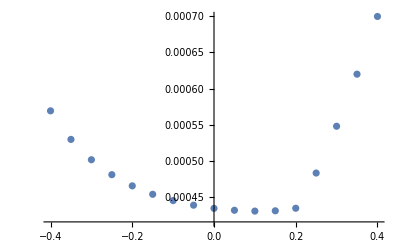

```mathematica
ListPlot[{%304,%308+%302}//Transpose]
```

```mathematica
%308
```

{0.00025096920194022221273064200521,0.00026779542827944366705080429309,0.00027776535328305970845072476903,0.00028560453443659853737394880842,0.00029341607682066543607990175135,0.00030226901346238330938108849315,0.00031278143399219415635558211561,0.00032536116347900806761211757733,0.00034031467621348019463188583865,0.0003579003522093534746485829654,0.00037835646616351516123480451835,0.00040191706879774575397295379087,0.00042882186240803707418553561173,0.00045932307850067148425671222853,0.00049369093357230234212045475941,0.00053221854960964268916172233463,0.00057522688766815051672212657518}

```mathematica
Count[%299[[1,;;,1]],_?Positive]
```

7

```mathematica
%299[[1,;;,1]]
```

{4.63904187042509727333462153495558,1.28292782477774661052644453188037,0.229120133826400709634884887596085,0.0351618268435091092168108691152769,0.00301099838792437784468571893645163,0.000556647377897757628773176459804859,-3.64616811218257569567692362614502×10^-6,8.4627398370908216740662966057409×10^-6}

```mathematica
Table[(1/(%299[[i,;;,2]]//Total))^(Count[%299[[i,;;,1]],_?Positive]/10),{i,Length[%299]}]
```

{331.33376786653279241578824787,316.61959495793792248583627806,699.93472654340083186794367889,684.52280509175149319522548528,669.90446930581845945144101274,654.16167555232775537702080623,636.51292505437832906523549632,616.74754590015601497690678987,594.97053308101051469865264125,571.46587197598427554361040482,546.6118865689772455071468558,520.8238213253059157282454111,494.51385631577251505904433635,468.06415816723475920383795095,441.81034297025088965239776605,416.03320482020656140339263967,390.95669766698964111891757397}

```mathematica
Table[(1/(%313[[i,;;,2]]//Total))^(Count[%313[[i,;;,1]],_?Positive]/10),{i,Length[%313]}]
```

{79.099719601261824119378243461023,85.778609128522089227670303191872,91.248576452891900341744925262028,95.870059700990492661333034915819,99.894575508660901836946674578774,103.50636601043367972895921976721,106.84700863558794316071071047236,110.03087635670394613384141051016,113.15550846594129400238474842001,116.30913827556745975759699574696,119.57673509496852947287053368191,123.04549296639467962172233428501,126.81054160485655497717212610004,130.98169647835590422792653899651,135.69231767485167990983774182983,141.11191171926313874119846718648,147.46523616326327350660244473921}

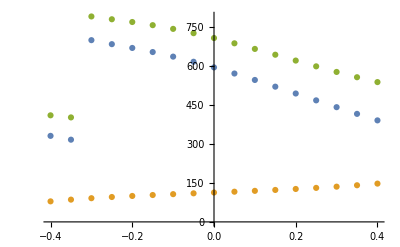

```mathematica
ListPlot[{{%304,%364}//Transpose,{%304,%367}//Transpose,{%304,%364+%367}//Transpose}]
```

```mathematica
Sum[%299[[;;,i,2]],{i,8}];
```

```mathematica
ParallelTable[getAvCs[7,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-4/10,4/10,1/20}];
```

```mathematica
Sum[%[[;;,i,2]],{i,7}];
```

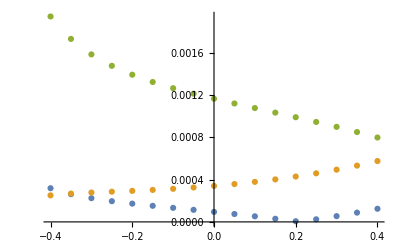

```mathematica
ListPlot[{{%304,%302}//Transpose,{%304,%308}//Transpose,{%304,%314}//Transpose}]
```

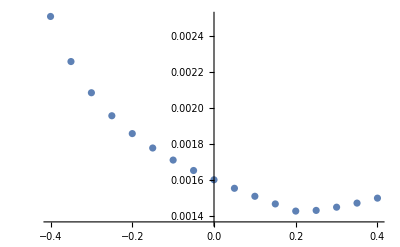

```mathematica
ListPlot[{{%304,%302+%308+%314}//Transpose}]
```

```mathematica
Table[getAvCs[9,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-1/10,1/10,1/20}]
```

{{{2.27222856564716509874431952753,0.0000431431898903034336665645},{1.21582413903585896007022610733,0.00003256722520992312955277887},{0.235818287913782999647822844591,0.000025217606757290596614298048},{0.0331305566187917030262179220354,0.0000168936242496151768249927774},{0.00359720215114739649729287225843,9.39164933142187324270463689×10^-6},{0.000388539337936275634301729678442,4.104847631108459960471694075×10^-6},{0.0000362850406460680548811055221321,1.310203009320618012645275216×10^-6},{1.76560646270396240898758439614×10^-6,2.698135114348655285530891212×10^-7},{5.7491159339658872291027793514×10^-7,2.6783952863702198204557156825×10^-8}},{{2.12277058619013235153146667145,0.00003528123956312193949621759},{1.208144373607262230569995171,0.00002863495488843052242274117},{0.236958957054295495731398721596,0.000022092084018279149155492058},{0.0328538746837154680177928101741,0.0000147906452293846375320614802},{0.00367079667078751871445202490962,8.2202843588557353292923502×10^-6},{0.000370271213080172348834498957503,3.592073431556901343402887313×10^-6},{0.0000399867405869778268096128234352,1.146261109290454036895737049×10^-6},{1.24199147225879585979273324914×10^-6,2.3598826383031625495628705431×10^-7},{6.12759170495601790457793833347×10^-7,2.341882793934462946563900823×10^-8}},{{2.00017244668378500605325115269,0.00002807646267429475585119244},{1.19984980252138127604347084178,0.00002430016430427119598247733},{0.238213033684796378973807949548,0.000018674547657142744486127916},{0.0325518675630812904339933364963,0.000012493753845357455318765084},{0.00375118671624606057429536728976,6.94134518694287411036204611×10^-6},{0.000350322543435098829052203042258,3.032282655730164963951764556×10^-6},{0.0000440289042659725491092173680254,9.672986977711657595250976557×10^-7},{6.70240211087997698887617415216×10^-7,1.9906517314791296679076380934×10^-7},{6.54085643079930883621418751491×10^-7,1.974558369481049634094133055×10^-8}},{{1.89884072788786620925085799945,0.00002124633799306264014217296},{1.1906904861809003421459374135,0.00001947195969580432843729012},{0.239601805891093661331050175227,0.000014899585974343920197752682},{0.0322186344237966318900362756303,9.9598349207986681016632988×10^-6},{0.00383989465778087196722909240398,5.53095042283025843003746421×10^-6},{0.000328314071441718832346368223634,2.415044680551473518326036568×10^-6},{0.0000484882467664597409164774956181,7.699845309034232385386194733×10^-7},{3.9501677312757430739306806416×10^-8,1.58357315188487629191597541103×10^-7},{6.9967503646931012796367575158×10^-7,1.569590254480402741794123077×10^-8}},{{1.81471951323037522076375903297,0.00001458674073019404751212716},{1.18046033602811513093785858942,0.00001406972398310698706487976},{0.241144462108989870289840151781,0.000010713578876183935607136138},{0.0318491896370251620760641764343,7.1539556468741378446889173×10^-6},{0.00393821697271632475607313521005,3.9698229975986547240451044×10^-6},{0.000303923810718508878188766264559,1.73195301758282993190542914×10^-6},{0.0000534299011314429485343328980623,5.516360509029879758363724585×10^-7},{-6.59433499715555494199781157384×10^-7,1.1331181640233292252575692911×10^-7},{7.50192729663491767418672778309×10^-7,1.121481801655918881106388125×10^-8}}}

```mathematica
Sum[%284[[;;,i,2]],{i,9}]
```

{0.0001329249435432818556012134,0.0001140169496906890002005252,0.00009470466577835307993553339,0.00007446775143602800372239072,0.0000529019379368624727719557}

```mathematica
Sum[%285[[;;,i,2]],{i,8}]
```

{0.00031278143399219415635558211561,0.00032536116347900806761211757733,0.00034031467621348019463188583865,0.0003579003522093534746485829654,0.00037835646616351516123480451835}

```mathematica
Total[%284[[;;,;;,2]],0]
```

{{0.0000431431898903034336665645,0.00003256722520992312955277887,0.000025217606757290596614298048,0.0000168936242496151768249927774,9.39164933142187324270463689×10^-6,4.104847631108459960471694075×10^-6,1.310203009320618012645275216×10^-6,2.698135114348655285530891212×10^-7,2.6783952863702198204557156825×10^-8},{0.00003528123956312193949621759,0.00002863495488843052242274117,0.000022092084018279149155492058,0.0000147906452293846375320614802,8.2202843588557353292923502×10^-6,3.592073431556901343402887313×10^-6,1.146261109290454036895737049×10^-6,2.3598826383031625495628705431×10^-7,2.341882793934462946563900823×10^-8},{0.00002807646267429475585119244,0.00002430016430427119598247733,0.000018674547657142744486127916,0.000012493753845357455318765084,6.94134518694287411036204611×10^-6,3.032282655730164963951764556×10^-6,9.672986977711657595250976557×10^-7,1.9906517314791296679076380934×10^-7,1.974558369481049634094133055×10^-8},{0.00002124633799306264014217296,0.00001947195969580432843729012,0.000014899585974343920197752682,9.9598349207986681016632988×10^-6,5.53095042283025843003746421×10^-6,2.415044680551473518326036568×10^-6,7.699845309034232385386194733×10^-7,1.58357315188487629191597541103×10^-7,1.569590254480402741794123077×10^-8},{0.00001458674073019404751212716,0.00001406972398310698706487976,0.000010713578876183935607136138,7.1539556468741378446889173×10^-6,3.9698229975986547240451044×10^-6,1.73195301758282993190542914×10^-6,5.516360509029879758363724585×10^-7,1.1331181640233292252575692911×10^-7,1.121481801655918881106388125×10^-8}}

```mathematica
Table[getAvCs[8,{2+x,4,6,8,10,12,14,16,18,20},40/100,49/100,1,50],{x,-1/10,1/10,1/20}]
```

{{{2.27132341098107987557061392404497,0.00010737327672601487542450357435},{1.21650754629929650396806164428062,0.000080245284897116991068395463525},{0.235288770523989953772113994073015,0.000060185583199081471848312622831},{0.0334857407039550743539431103361461,0.0000377433338623244521747394885702},{0.00339933580893798905095140594509335,0.00001870489942383567071941375960458},{0.000475281043420268163592668341070922,6.773521155122249142619477830845×10^-6},{8.48651965298647787336591629625154×10^-6,1.5788467795006737465664331974206×10^-6},{7.51996575418721925733533502858332×10^-6,1.766879491977722310312957073968×10^-7}},{{2.12187011531585293304667961524068,0.00010660036054284608450306678808},{1.20887537639027352997667617526211,0.000085663142131343878973628551262},{0.236394586425249913162589542050053,0.000064018672179855867058589773059},{0.0332322506471068945173115502583785,0.0000401269913557279201459634864966},{0.00346002651980362512039901411364393,0.00001988446958408700206314315332132},{0.000462675040970939338871317017172184,7.200977584066274517054034908795×10^-6},{0.0000103698988560144439373163168094739,1.6786630726639978016622605018196×10^-6},{7.37383175384832479595252129145192×10^-6,1.878870284170425490095297044039×10^-7}},{{1.9992675480453827520247045993086,0.00010691531495669344077520986888},{1.20063318516607794415746028508305,0.000091626427160493569356386952952},{0.237610536996001404048703308432236,0.00006821250117768547147226669026},{0.0329555820842461118507380021538353,0.0000427317522882472959151761934662},{0.0035263230613343497780178566387551,0.00002117302072081977794654668484908},{0.00044890969215781432663494601934756,7.667862791255903400333574573991×10^-6},{0.0000124264932199317282167230977013724,1.7876792585736044973503108122955×10^-6},{7.21426760995098467600985901890203×10^-6,2.00117859711131268615562851382×10^-7}},{{1.89792257555667582006996669137989,0.0001082764523727148023261350279},{1.19153219594033951408092932445035,0.000098267816742916255939389365483},{0.238957168156182374196802783499999,0.0000728487848517722084092331679211},{0.0326503193795223233682596050517221,0.0000456075426804946763295321015611},{0.00359947937125995003170904340112629,0.00002259511726439321333854101725707},{0.000433723265936908078113897149284213,8.183058500955171961624174301934×10^-6},{0.0000146953158700274695643717081077507,1.9079670531212059122038652691965×10^-6},{7.03824466447283094755717684943185×10^-6,2.1361274298594043192424570384895×10^-7}},{{1.81377945579928999226039704318256,0.00011065728054792643090478254087},{1.18136738189594724300879490336706,0.00010570847464039087187337375431},{0.24045302792683271923791016569107,0.0000779980796081510980120381275395},{0.0323118909749063578795069133886497,0.0000487969933413541019073833155107},{0.00368056356478591230155974633306473,0.00002417166780879405556593713808273},{0.000416893631235008358144857925122374,8.754114801478270035861694102349×10^-6},{0.0000172094862981279887482790958081345,2.0412864577270982918172977782265×10^-6},{6.84319345599832992520377113758924×10^-6,2.2856895769323464361065015334999×10^-7}}}

```mathematica
crossingEq[2]/.Δ[i_]->2i+2/.Δσ->1/.C[k_]->%333[[k+1,1]]
```

Part::pkspec1: The expression 1+k cannot be used as a part specification.

(1-z)^2-z^2+1.98789924069708632723852497263514864236 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)+1.21019823556985322113026165359194008592 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+0.230902867703967937487041124816049932277 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))

```mathematica
Series[%339,{z,1/2,5}]//Normal
```

-0.01783702791488009007727275508897704043 (-1/2+z)-0.82481123625432050238761193856331789803 (-1/2+z)^3-8.45354337238612690473788760164634685051 (-1/2+z)^5

```mathematica
getAvCsFn[3,Table[2i,{i,1,10}],40/100,49/100,Function[z,-(-0.0178370279148800900772727550889770404285335954679292786565`37.54787908867152 (-1/2+z)-0.8248112362543205023876119385633178980310303483349273099978`38.617521569638185 (-1/2+z)^3-8.4535433723861269047378876016463468505070285321654504172149`39.20464240995501 (-1/2+z)^5)],1,50]
```

{{2.020399742112090393036267518357129829,0.028259628768347120346551695954080314},{1.188447209513472913078529919076404397,0.018830341131120275877777959769219332},{0.2377169074384172250912647757333343189,0.0058320540982001578712605348436649343}}

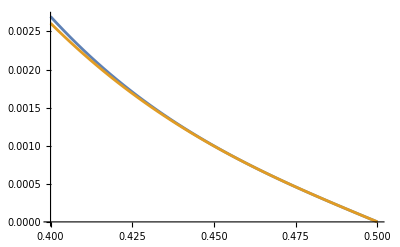

```mathematica
Plot[{%339,%348}//Evaluate,{z,4/10,1/2}]
```

```mathematica
getAvCs[6,Table[2i,{i,1,10}],40/100,49/100,1,50]
```

{{1.98789924069708632723852497263514864236,0.00136272597382162905336586912200487203},{1.21019823556985322113026165359194008592,0.00112725716083903045420584358665033347},{0.230902867703967937487041124816049932277,0.000748999283443328179007584167224663139},{0.0366517219950640873826951053621477223515,0.0003689807245000609852193621247378969233},{0.00209150741394346739537408048801068296019,0.0001168613746072211397719091706209443339},{0.00076650730787255470108850660786583129488,0.00001759908302246532448803544581030147746}}

```mathematica
getAvCsFn[6,Table[2i,{i,1,10}],40/100,49/100,Function[z,0],1,50]
```

{{1.98789924069708632723852497263514864236,0.00136272597382162905336586912200487203},{1.21019823556985322113026165359194008592,0.00112725716083903045420584358665033347},{0.230902867703967937487041124816049932277,0.000748999283443328179007584167224663139},{0.0366517219950640873826951053621477223515,0.0003689807245000609852193621247378969233},{0.00209150741394346739537408048801068296019,0.0001168613746072211397719091706209443339},{0.00076650730787255470108850660786583129488,0.00001759908302246532448803544581030147746}}

```mathematica
getAvCsFn[6,Table[2i,{i,1,10}],40/100,49/100,Function[z,0],1,50]
```

```mathematica
getAvCsFn[5,Table[2i,{i,1,10}],40/100,49/100,fhs,1,50]
```

{{2.046910963570424140630458987174771,0.000959809479262386783924307031063},{1.161376016822488866873762288570125,0.0007662212357523399348497965718189},{0.263357827351995847048536719813805,0.000453926806198872990435547431966},{0.02064795324512021185676448619105049,0.00017327601822397502953485180830436},{0.007168441938809770479266173054803705,0.00003115983317074490886077489506318}}

```mathematica
C[4]/.genBos/.Δσ->1//N
```

0.00370218

```mathematica
N[crossingEq[7]/.Δ[i_]->i+2/.C[i_]->Rationalize[%293[[i+1,1]],0]/.Δσ->1/.z->4/10,40]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

0.03529555207030780554699214986924654234119

```mathematica
N[crossingEq[7]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1/.z->4/10,30]
```

0.000148576464357209600802423834245

```mathematica
Table[C[i],{i,0,6}]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}
```

{1,1,3/5,2/7,5/42,1/22,7/429}

```mathematica
N[crossingTable[10]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.z->4/10/.Δσ->1//Simplify,30]
```

{-0.0389578500599478431154591622967,-0.0719556211604710011943237511934,-0.0835480818703817529966153802172,-0.0847763058539576135757039798497,-0.0811997256233707836363595147008,-0.0755977413755967837491346819619,-0.0693416411664221000974705700001,-0.0630912167017461948050688515051,-0.0571483387692583286831714360977,-0.0516362731438607356512360730513,-0.0465904844920437218362428098622}

```mathematica
Table[C[i-1]%322[[i]],{i,10}]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.z->45/100/.Δσ->1
```

{-0.0389578500599478431154591622967,-0.0719556211604710011943237511934,-0.0501288491222290517979692281303,-0.0242218016725593181644868513856,-0.009666634002782236147185656512,-0.0034362609716180356249606673619,-0.00113144869036119976849019578089,-0.000352957855674104586322063504924,-0.000105786723349100155933472423875,-0.0000307431966800790281324339563297}

```mathematica
N[Table[C[i],{i,0,10}]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1,30]
```

{1.,1.,0.6,0.285714285714285714285714285714,0.119047619047619047619047619048,0.0454545454545454545454545454545,0.016317016317016317016317016317,0.00559440559440559440559440559441,0.00185109008638420403126285479227,0.000595379852345796618242438675875,0.000187119382165821794304766440989}

```mathematica
N[Table[C[i],{i,0,10}]/.genBos/.Δσ->1,30]
```

{2.,1.2,0.238095238095238095238095238095,0.032634032634032634032634032634,0.00370218017276840806252570958453,0.000374238764331643588609532881979,0.0000349979808857181316462511778167,3.0944280181890478909152235028×10^-6,2.62255043183763882837096654636×10^-7,2.15021736519052377252309544228×10^-8,1.71664929372621553281813238381×10^-9}

```mathematica
Table[C[i-1]%326[[i]],{i,10}]/.genBos/.z->45/100/.Δσ->1
```

{-0.0405753689582588663786050032949,-0.0499233797233019504874545624348,-0.00858415962996151174689175510865,-0.000848160834728095191209798195313,-0.0000644523684771534001299391985563,-4.21355952092922140649186304212×10^-6,-2.50235754003698079013811436018×10^-7,-1.39128836262146329497949902515×10^-8,-7.37445199894969267759800536278×10^-10,-3.76996610285925310747727239193×10^-11}

```mathematica
N[crossingTable[10]/.genBos/.z->45/100/.Δσ->1//Simplify,30]
```

{-0.0202876844791294331893025016474,-0.0416028164360849587395454686956,-0.0360534704458383493369453714563,-0.0259900712927394883592145304135,-0.0174093008631066573017646879656,-0.0112590140907884186182741209452,-0.00715000544805181934228309676222,-0.00449610834197296010600517374215,-0.00281193906108503861103450326376,-0.00175329534766602941256255191049,-0.00109134284743342097289081532648}

```mathematica
%/%223
```

{{0.9342867078465698,1.2513406338665},{1.14559343349957,1.2113354822985},{1.109355560388699,1.10916603844101},{1.05590005173907,1.0488102349817},{0.9644237295968838,0.94934793069056},{1.181272251804525,1.1973032826505}}

```mathematica
N[crossingEq[5]/.{Δ[0]->2,C[0]->2,Δ[1]->3,C[1]->2/3,Δ[2]->4,C[2]->6/5,Δ[3]->5,C[3]->12/35,Δ[4]->6,C[4]->5/21,Δ[5]->7,C[5]->5/77,Δ[6]->8,C[6]->14/429,Δ[7]->9,C[7]->56/6435,Δ[8]->10,C[8]->9/2431,Δ[9]->11,C[9]->45/46189,Δ[10]->12,C[10]->11/29393,Δ[11]->13,C[11]->66/676039,Δ[12]->14,C[12]->13/371450,Δ[13]->15,C[13]->91/10029150,Δ[14]->16,C[14]->2/646323,Δ[15]->17,C[15]->16/20036013,Δ[16]->18,C[16]->17/64822395,Δ[17]->19,C[17]->51/756261275}/.Δσ->1/.z->1/3,30]
```

-0.133190336908060551874241817643

```mathematica
{pppp,pmpm,pmmp}=
```

```mathematica
N[crossingEq[7]/.{Δ[0]->2,C[0]->2,Δ[1]->3,C[1]->2/3,Δ[2]->4,C[2]->6/5,Δ[3]->5,C[3]->12/35,Δ[4]->6,C[4]->5/21,Δ[5]->7,C[5]->5/77,Δ[6]->8,C[6]->14/429,Δ[7]->9,C[7]->56/6435}/.Δσ->1/.z->1/3,30]
```

-0.141587514585368753035501579662

```mathematica
N[crossingEq[15]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1/.z->4/10,30]
```

4.40550386079067062937457442735×10^-9

```mathematica
crossingEq[15]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])+C[2] (-(1-z)^Δ[2] z^(2 Δσ) Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1-z]+(1-z)^(2 Δσ) z^Δ[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],z])+C[3] (-(1-z)^Δ[3] z^(2 Δσ) Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],1-z]+(1-z)^(2 Δσ) z^Δ[3] Hypergeometric2F1[Δ[3],Δ[3],2 Δ[3],z])+C[4] (-(1-z)^Δ[4] z^(2 Δσ) Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],1-z]+(1-z)^(2 Δσ) z^Δ[4] Hypergeometric2F1[Δ[4],Δ[4],2 Δ[4],z])+C[5] (-(1-z)^Δ[5] z^(2 Δσ) Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],1-z]+(1-z)^(2 Δσ) z^Δ[5] Hypergeometric2F1[Δ[5],Δ[5],2 Δ[5],z])+C[6] (-(1-z)^Δ[6] z^(2 Δσ) Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],1-z]+(1-z)^(2 Δσ) z^Δ[6] Hypergeometric2F1[Δ[6],Δ[6],2 Δ[6],z])+C[7] (-(1-z)^Δ[7] z^(2 Δσ) Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],1-z]+(1-z)^(2 Δσ) z^Δ[7] Hypergeometric2F1[Δ[7],Δ[7],2 Δ[7],z])+C[8] (-(1-z)^Δ[8] z^(2 Δσ) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],1-z]+(1-z)^(2 Δσ) z^Δ[8] Hypergeometric2F1[Δ[8],Δ[8],2 Δ[8],z])+C[9] (-(1-z)^Δ[9] z^(2 Δσ) Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],1-z]+(1-z)^(2 Δσ) z^Δ[9] Hypergeometric2F1[Δ[9],Δ[9],2 Δ[9],z])+C[10] (-(1-z)^Δ[10] z^(2 Δσ) Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],1-z]+(1-z)^(2 Δσ) z^Δ[10] Hypergeometric2F1[Δ[10],Δ[10],2 Δ[10],z])+C[11] (-(1-z)^Δ[11] z^(2 Δσ) Hypergeometric2F1[Δ[11],Δ[11],2 Δ[11],1-z]+(1-z)^(2 Δσ) z^Δ[11] Hypergeometric2F1[Δ[11],Δ[11],2 Δ[11],z])+C[12] (-(1-z)^Δ[12] z^(2 Δσ) Hypergeometric2F1[Δ[12],Δ[12],2 Δ[12],1-z]+(1-z)^(2 Δσ) z^Δ[12] Hypergeometric2F1[Δ[12],Δ[12],2 Δ[12],z])+C[13] (-(1-z)^Δ[13] z^(2 Δσ) Hypergeometric2F1[Δ[13],Δ[13],2 Δ[13],1-z]+(1-z)^(2 Δσ) z^Δ[13] Hypergeometric2F1[Δ[13],Δ[13],2 Δ[13],z])+C[14] (-(1-z)^Δ[14] z^(2 Δσ) Hypergeometric2F1[Δ[14],Δ[14],2 Δ[14],1-z]+(1-z)^(2 Δσ) z^Δ[14] Hypergeometric2F1[Δ[14],Δ[14],2 Δ[14],z])+C[15] (-(1-z)^Δ[15] z^(2 Δσ) Hypergeometric2F1[Δ[15],Δ[15],2 Δ[15],1-z]+(1-z)^(2 Δσ) z^Δ[15] Hypergeometric2F1[Δ[15],Δ[15],2 Δ[15],z])

```mathematica
N[crossingEq[15]/.genBos/.Δσ->1/.z->4/10,30]
```

1.54155019465519817955356823505×10^-18

```mathematica
FindSequence[{1,1/6,1/15}]
```

FindSequence[{1,1/6,1/15}]

```mathematica
N[crossingEq[5]/.genBos/.Δσ->1/.z->1/3,30]
```

0.000011837935791211398583083543947

```mathematica
Table[2i,{i,1,10}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Solve[(Δ-b)(Δ+b+1)==1/.Δ->2,b]
```

{{b→1/2 (-1-√21)},{b→1/2 (-1+√21)}}

```mathematica
Solve[(Δ-b)(Δ+b+1)==1/.Δ->2,b]
```

```mathematica
Table[2n+1/n/(2n-1)g,{n,1,10}]
```

{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->0,40/100,49/100,1,60][[;;5,2]]//Total
```

0.000023777597165818373724171457933858

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->1/10,40/100,49/100,1,60][[;;5,2]]//Total
```

0.000026665755045339439183782428682839

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->1/10,40/100,49/100,1,60][[;;5,2]]//Total
```

```mathematica
Table[1+2i,{i,10}]+D[{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190},g]g
```

{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}

```mathematica
ParallelTable[(getAvCs[10,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190},40/100,49/100,1,60][[;;5,2]]//Total)/%13,{g,-1,1,1/10}]
```

{1775.618330636224451536296877475,1738.055165493693566051588061218,1686.918015728152783040694491982,1614.723736521160481526125331049,1515.135012767450206679513121498,1382.226972867569293894460091439,1210.088898017952056652093387105,992.5734466668733407491061447397,723.1114010371600628376678253631,394.551509502428382027944693688,1.,472.3396734098350962082917076315,1029.390149882566068515325018697,1683.418933680611241046540681111,2447.352910566180203477448196841,3336.16339699329255204224456462,4367.371863972722842328071062509,5561.72289331529727791525926588,6944.09715947019149122272206374,8544.775596004212039291889247219,10401.22900139516025739572927695}

```mathematica
getAvCs[10,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->0,40/100,49/100,1,60][[;;5,2]]//Total
```

1.410587705834545365033826891727×10^-6

```mathematica
(getAvCs[10,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->-1/100,40/100,49/100,1,60][[;;5,2]]//Total)/%13
```

41.81474041212958788561230727819

```mathematica
%168/.{{z->4/10},{z->43/100},{z->46/100}}
```

```mathematica
crossingEq[2]/.Δ[i_]->{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}[[i+1]]/.Δσ->1/.g->3/10//Simplify
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

(-1+z)^2-z^2+C[0] (-(1-z)^(33/10) z^2 Hypergeometric2F1[33/10,33/10,33/5,1-z]+(-1+z)^2 z^(33/10) Hypergeometric2F1[33/10,33/10,33/5,z])+C[1] (-(1-z)^(101/20) z^2 Hypergeometric2F1[101/20,101/20,101/10,1-z]+(-1+z)^2 z^(101/20) Hypergeometric2F1[101/20,101/20,101/10,z])+C[2] (-(1-z)^(351/50) z^2 Hypergeometric2F1[351/50,351/50,351/25,1-z]+(-1+z)^2 z^(351/50) Hypergeometric2F1[351/50,351/50,351/25,z])

```mathematica
%//N
```

{{C[0]→2.17729,C[1]→0.229843,C[2]→0.169817}}

```mathematica
getAvCs[8,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->30/100,40/100,49/100,1,60]
```

{{2.1883489795864462810509984465088283349748154,0.000319202359130672007158594575874065780411},{0.20121280468842367325293731556348771379053976,0.00069427364530805582317849026015121031421857},{0.21105780519291035788383144128777742129520785,0.00083489895851764671070155476334265420105696},{-0.036134043422235683434919782909501187372698136,0.000721810689959326485746787204172769312444075},{0.017175582973439205720696567578175595692676141,0.000450134875739159968803358582640672123599458},{-0.0041292759641475700480832084124624992565730828,0.000193560941460005362515240711956793187178994},{0.00076993925353213330399471040928656798051478502,0.0000515368558741197490348999541844185372697493},{-0.00006641222719099373589435235386620895302184473,6.41271796884033865224319082350691439760594×10^-6}}

```mathematica
getAvCs[6,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->0/100,40/100,49/100,1,60]
```

{{1.999619768278383626641770932958315249509589253025,0.000051027376495811362578490121584002511889799693},{0.5722051400437987726489556409197816783124783167925,0.000100576761287540555481906980697436504433620933},{0.09000982330596571518987772479553445133913362442561,0.00010753760375111958375015595009162746311157023},{0.01187926022378773562992501896556219712305191282573,0.000071328282243175682671592341629732244393866286532},{0.0008448514628687422970446213190141229597294352523106,0.000027646608275408906620935212063623043646874802067},{0.0002151726549985390609030744683407727647237925095594,4.8128698122322191897911320161899148088785118169×10^-6}}

```mathematica
getAvCs[3,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->30/100,40/100,49/100,1,60]
```

{{2.17641439412628410631458790557106300014569802942391299366,0.00177716072717906267287422750117265337108201633600775302},{0.231160659425291741061026371761700734192619394399164452797,0.002597108725546337039701046245573444257457406802700437655},{0.169227602680003214664119373560954098529577429300175502123,0.001105246796305495699959443470510549868089448857904620061}}

```mathematica
Solve[%==0]//N
```

{{C[0]→2.17445,C[1]→0.234051,C[2]→0.167977}}

```mathematica
crossingEq[2]/.genFer/.Δσ->1//Simplify
```

1/(5 (-1+z)^6 z^6)(-2520 (-1+z)^8 (2002-6006 z+6875 z^2-3740 z^3+975 z^4-106 z^5+3 z^6) Log[1-z]+z (-5045040+52972920 z-253601040 z^2+731734080 z^3-1416867228 z^4+1939278983 z^5-1924022056 z^6+1395059409 z^7-734394610 z^8+276936473 z^9-70631748 z^10+10139831 z^11-1559974 z^12+2520 z^7 (3+88 z+490 z^2+840 z^3+490 z^4+88 z^5+3 z^6) Log[z]))

```mathematica
Table[D[crossingEq[2]/.Δσ->1/.Δ[i_]->{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}[[i+1]]/.g->3/10,{z,n}],{n,1,5,2}]/.z->1/2//Simplify
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{1/200 (-400+10 C[0] (26 Hypergeometric2F1[33/10,33/10,33/5,-1]+33 Hypergeometric2F1[33/10,43/10,38/5,-1])+C[1] (610 Hypergeometric2F1[101/20,101/20,101/10,-1]+505 Hypergeometric2F1[101/20,121/20,111/10,-1])+1004 C[2] Hypergeometric2F1[351/50,351/50,351/25,-1]+702 C[2] Hypergeometric2F1[351/50,401/50,376/25,-1]),-1/7600033 C[0] (146224 Hypergeometric2F1[33/10,33/10,33/5,-1]+164616 Hypergeometric2F1[33/10,43/10,38/5,-1]-43 (3354 Hypergeometric2F1[33/10,53/10,43/5,-1]+2809 Hypergeometric2F1[33/10,63/10,48/5,-1]))-1/592000 101 C[1] (704184 Hypergeometric2F1[101/20,101/20,101/10,-1]-400044 Hypergeometric2F1[101/20,121/20,111/10,-1]-121 (14762 Hypergeometric2F1[101/20,141/20,121/10,-1]+6627 Hypergeometric2F1[101/20,161/20,131/10,-1]))+1/94000000 351 C[2] (755008 Hypergeometric2F1[351/50,351/50,351/25,-1]+182514912 Hypergeometric2F1[351/50,401/50,376/25,-1]+401 (603906 Hypergeometric2F1[351/50,451/50,401/25,-1]+203401 Hypergeometric2F1[351/50,501/50,426/25,-1])),1/121600000 33 C[0] (9767320576 Hypergeometric2F1[33/10,33/10,33/5,-1]+7346634240 Hypergeometric2F1[33/10,43/10,38/5,-1]-43 (873649920 Hypergeometric2F1[33/10,53/10,43/5,-1]+648991360 Hypergeometric2F1[33/10,63/10,48/5,-1]-70119 (6890 Hypergeometric2F1[33/10,73/10,53/5,-1]+5329 Hypergeometric2F1[33/10,83/10,58/5,-1])))+1/31020800000 101 C[1] (506569819104 Hypergeometric2F1[101/20,101/20,101/10,-1]-7800598553040 Hypergeometric2F1[101/20,121/20,111/10,-1]-121 (101564331440 Hypergeometric2F1[101/20,141/20,121/10,-1]-31287657480 Hypergeometric2F1[101/20,161/20,131/10,-1]-104784864870 Hypergeometric2F1[101/20,181/20,141/10,-1]-39912300407 Hypergeometric2F1[101/20,201/20,151/10,-1]))-1/33370000000000 351 C[2] (2600877403833856 Hypergeometric2F1[351/50,351/50,351/25,-1]+9002454160976640 Hypergeometric2F1[351/50,401/50,376/25,-1]-401 (401331771360 Hypergeometric2F1[351/50,451/50,401/25,-1]+451 (103622517680 Hypergeometric2F1[351/50,501/50,426/25,-1]+83667 (1132010 Hypergeometric2F1[351/50,551/50,451/25,-1]+303601 Hypergeometric2F1[351/50,601/50,476/25,-1]))))}

```mathematica
crossingEq[2]/.C[i_]->%186[[i+1,1]]/.Δσ->1/.Δ[i_]->{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}[[i+1]]/.g->3/10
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

(1-z)^2-z^2+2.17641439412628410631458790557106300014569802942391299366 (-(1-z)^(33/10) z^2 Hypergeometric2F1[33/10,33/10,33/5,1-z]+(1-z)^2 z^(33/10) Hypergeometric2F1[33/10,33/10,33/5,z])+0.231160659425291741061026371761700734192619394399164452797 (-(1-z)^(101/20) z^2 Hypergeometric2F1[101/20,101/20,101/10,1-z]+(1-z)^2 z^(101/20) Hypergeometric2F1[101/20,101/20,101/10,z])+0.169227602680003214664119373560954098529577429300175502123 (-(1-z)^(351/50) z^2 Hypergeometric2F1[351/50,351/50,351/25,1-z]+(1-z)^2 z^(351/50) Hypergeometric2F1[351/50,351/50,351/25,z])

```mathematica
N[%197/.z->4/10,30]
```

0.000772632390703290032457460118145

```mathematica
%188/.z->4/10
```

4.74475774848382973408899814415839136151325338189171×10^-7

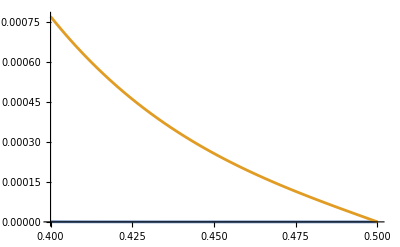

```mathematica
Plot[{%188,%189},{z,4/10,5/10},WorkingPrecision->40]
```

```mathematica
crossingEq[5]/.genFer/.Δσ->1
```

```mathematica
{%176,%180}/.g->3/10/.z->4/10
```

{1.62474989056029595311530808537263281903×10^-11,1/5+8/715 (-(3076734375 (53533273664/390625-(20959509928 Log[5/3])/78125))/3584+(75968750 (25736988249/390625-(5617646748 Log[5/2])/78125))/5103)+1/11 (-3378375/32 (17719744/15625-(6937688 Log[5/3])/3125)+1001000/243 (11902149/15625-(2597898 Log[5/2])/3125))+4/7 (-23625/16 (416/5-101796/625 Log[5/3])+3500/27 (1953/25-53286/625 Log[5/2]))+2 (-135/2 (48/25-94/25 Log[5/3])+40/3 (63/25-69/25 Log[5/2]))+(5 ((969969 (-956834326888+1873113411645 Log[5/3]))/8000-(1293292 (-585463416087+638949402980 Log[5/2]))/2460375))/4199+(6 ((96577 (-16708852394591864+32709503237931135 Log[5/3]))/14080-(2704156 (-1045691666859723+1141222573233820 Log[5/2]))/29229255))/52003}

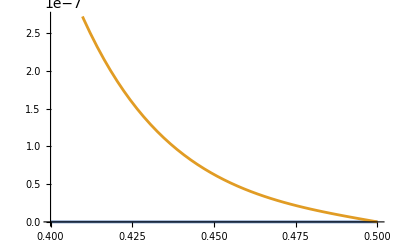

```mathematica
Plot[{%176,%180}/.g->3/10//Evaluate,{z,4/10,5/10},WorkingPrecision->40]
```

```mathematica
crossingEq[5]/.C[i_]->%160[[i+1,1]]/.Δσ->1/.Δ[i_]->{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}[[i+1]]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

(1-z)^2-z^2-0.0005103454312675429537277060744792757590795478455215 (-(1-z)^(13+g/66) z^2 Hypergeometric2F1[13+g/66,13+g/66,2 (13+g/66),1-z]+(1-z)^2 z^(13+g/66) Hypergeometric2F1[13+g/66,13+g/66,2 (13+g/66),z])+0.0074233002176709374338094097181422308923068560613 (-(1-z)^(11+g/45) z^2 Hypergeometric2F1[11+g/45,11+g/45,2 (11+g/45),1-z]+(1-z)^2 z^(11+g/45) Hypergeometric2F1[11+g/45,11+g/45,2 (11+g/45),z])-0.01889207680954618377451264408744738185651530840825 (-(1-z)^(9+g/28) z^2 Hypergeometric2F1[9+g/28,9+g/28,2 (9+g/28),1-z]+(1-z)^2 z^(9+g/28) Hypergeometric2F1[9+g/28,9+g/28,2 (9+g/28),z])+0.1898372954120606200352157756627880230238581826539 (-(1-z)^(7+g/15) z^2 Hypergeometric2F1[7+g/15,7+g/15,2 (7+g/15),1-z]+(1-z)^2 z^(7+g/15) Hypergeometric2F1[7+g/15,7+g/15,2 (7+g/15),z])+0.2194957019905791602139813278405266369156579588961 (-(1-z)^(5+g/6) z^2 Hypergeometric2F1[5+g/6,5+g/6,2 (5+g/6),1-z]+(1-z)^2 z^(5+g/6) Hypergeometric2F1[5+g/6,5+g/6,2 (5+g/6),z])+2.17981288081417899782729493425950125872651444445 (-(1-z)^(3+g) z^2 Hypergeometric2F1[3+g,3+g,2 (3+g),1-z]+(1-z)^2 z^(3+g) Hypergeometric2F1[3+g,3+g,2 (3+g),z])

```mathematica
getAvCs[6,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->30/100,40/100,49/100,1,60]
```

{{2.17981288081417899782729493425950125872651444445,0.000580542555442606373355824233363234893447211467},{0.2194957019905791602139813278405266369156579588961,0.001184455700640179111641334239472150306154133646},{0.1898372954120606200352157756627880230238581826539,0.0012257148103024006452406932721589057155499762893},{-0.01889207680954618377451264408744738185651530840825,0.000804253330286380838290752095857894849032826641215},{0.0074233002176709374338094097181422308923068560613,0.000310548873695547136468293358426640037621548102753},{-0.0005103454312675429537277060744792757590795478455215,0.0000540225569937523839002455209273079964009476963506}}

```mathematica
(getAvCs[6,{3+g,5+g/6,7+g/15,9+g/28,11+g/45,13+g/66,15+g/91,17+g/120,19+g/153,21+g/190}/.g->30/100,40/100,49/100,1,60][[;;3,2]]//Total)/%13
```

2120.1893749781350280207374731

```mathematica
Table[Δ[i],{i,0,10}]/.genFer/.Δσ->1
```

{3,5,7,9,11,13,15,17,19,21,23}

```mathematica
Table[getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190},40/100,49/100,1,60][[;;5,2]]//Total,{g,-1,1,1/10}]
```

{0.000426215692347145626402403667952463,0.00049256188141290978937195032988539,0.000694717638149723822054793420604524,0.00225356809756596525330124538125668,0.00132666875356998121018604511684965,0.00002242688337382028348746315571418,0.000060214565194549292937044507449369,0.000051073289093137304710921733416226,0.000038067490909608561751042162393522,0.000028146606261003683002777158412942,0.000023777597165818373724171457933858,0.000026665755045339439183782428682839,0.000038504604719553559818048035857777,0.000061180103616157544572616090709895,0.00009686306011931325698390747730567,0.000148098809239750197350169990081045,0.000217905987763617629682663975239133,0.00030990035452294245668335426772323,0.000428461422253300399000051536967818,0.000578963398619366638902546085831628,0.000768102571929875528719032862314998}

```mathematica
Table[g,{g,-1,1,1/10}]
```

{-1,-9/10,-4/5,-7/10,-3/5,-1/2,-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
%484/%485
```

{17.925095179922323303599579104738,20.715376662238817495134371915538,29.217318861319565803483926036941,94.776948311900728138424133703538,55.794904098936530483054345452908,0.9431938482859059920164060758377,2.5324074915825010019273928638363,2.147958380191502921021040892536,1.600981404644734658014961749844,1.183744768856039175303269546365,1.,1.121465506349521052659373764555,1.6193648353546035940232730873233,2.5730145560758076316755096070597,4.073711041692611622118004091918,6.2285019048371515739025007856098,9.1643401241934436870864476776369,13.033291478604135625148096149407,18.019542482166266395785132413621,24.349112931043298069638937723618,32.303624566155319974636795308023}

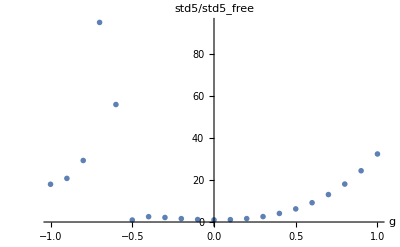

```mathematica
ListPlot[{%107,%105/%106}//Transpose,AxesLabel->{"g",std5/std5_free},PlotMarkers->{"x",Medium}]
```

```mathematica
Table[2n+1/n/(2n-1)g,{n,1,15}]
```

{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190,22+g/231,24+g/276,26+g/325,28+g/378,30+g/435}

```mathematica
D[crossingEq[0]/.Δσ->1,C[0]]
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
Manipulate[Plot[-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],{z,0,.1}],{Δ[0],2,10}]
```

```mathematica
Series[D[crossingEq[0]/.Δσ->1,C[0]],{z,1/2,2}]
```

```mathematica
Exp[-Log[4]]
```

1/4

```mathematica
D[crossingEq[0]/.Δσ->1/.Δ[0]->10,C[0]]/.z->1/2//Simplify
```

0

```mathematica
N[D[crossingEq[0]/.Δσ->1/.Δ[0]->11,C[0]]/D[crossingEq[0]/.Δσ->1/.Δ[0]->10,C[0]]/.z->49/100//Simplify,50]
```

0.76776350059871714013527553977001302206061242002306

```mathematica
D[crossingEq[0]/.Δσ->1,C[0]]/4^Δ[0]
```

4^(-Δ[0]) (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])

```mathematica
NSolve[D[crossingEq[0]/.Δσ->1/.Δ[0]->11,C[0]]/D[crossingEq[0]/.Δσ->1/.Δ[0]->10,C[0]]==1/4,z]
```

```mathematica
D[crossingEq[0]/.Δσ->1,C[0]]/4^(Δ[0])//Evaluate
```

4^(-Δ[0]) (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])

```mathematica
(-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->Table[{i},{i,10,20}]
```

{{1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])},{-(1-z)^11 z^2 Hypergeometric2F1[11,11,22,1-z]+(1-z)^2 z^11 Hypergeometric2F1[11,11,22,z]},{-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]},{-(1-z)^13 z^2 Hypergeometric2F1[13,13,26,1-z]+(1-z)^2 z^13 Hypergeometric2F1[13,13,26,z]},{-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z]},{-(1-z)^15 z^2 Hypergeometric2F1[15,15,30,1-z]+(1-z)^2 z^15 Hypergeometric2F1[15,15,30,z]},{-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(1-z)^2 z^16 Hypergeometric2F1[16,16,32,z]},{-(1-z)^17 z^2 Hypergeometric2F1[17,17,34,1-z]+(1-z)^2 z^17 Hypergeometric2F1[17,17,34,z]},{-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(1-z)^2 z^18 Hypergeometric2F1[18,18,36,z]},{-(1-z)^19 z^2 Hypergeometric2F1[19,19,38,1-z]+(1-z)^2 z^19 Hypergeometric2F1[19,19,38,z]},{-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(1-z)^2 z^20 Hypergeometric2F1[20,20,40,z]}}

```mathematica
Series[D[crossingEq[0]/. Δσ->1,C[0]],{Δ[0],Infinity,0}]//Simplify
```

-(1-z)^(Δ[0]+O[1/Δ[0]]^2) z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(z^(Δ[0]+O[1/Δ[0]]^2)-2 z^(Δ[0]+1+O[1/Δ[0]]^2)+z^(Δ[0]+2+O[1/Δ[0]]^2)) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
Block[{$MaxExtraPrecision=1000,idx},]
```

```mathematica
getLogLine[z1_,Δmin_,Δmax_]:=Block[{$MaxExtraPrecision=1000,idx},Module[{eq,t},eq=Log[D[crossingEq[0]/. Δσ->1,C[0]]//Abs]/.z->z1;
t=Table[{Δ[0],eq},{Δ[0],Δmin,Δmax}];
Fit[N[t,60],{1,Δ[0]},Δ[0]]
]]
```

```mathematica
getLogLine[1/1000,40,60]
```

-12.813116273625079731501862041064130834186069938741353281823+1.3236197308189056598426558309097060417985260602651299224485 Δ[0]

```mathematica
Log[D[crossingEq[0]/. Δσ->1,C[0]]]/.z->4/10
```

Log[9 2^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],2/5]-4 3^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],3/5]]

```mathematica
Log[9 2^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],2/5]-4 3^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],3/5]//Abs]/.Δ[0]->10
```

Log[-(46189 (-111944821832+219144883545 Log[5/3]))/1400+(184756 (-323813046423+353395527380 Log[5/2]))/3444525]

```mathematica
Table[{Δ[0],Log[9 2^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],2/5]-4 3^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],3/5]//Abs]},{Δ[0],10,30}]
```

{{10,Log[-(46189 (-111944821832+219144883545 Log[5/3]))/1400+(184756 (-323813046423+353395527380 Log[5/2]))/3444525]},{11,Log[-(969969 (-956834326888+1873113411645 Log[5/3]))/8000+(1293292 (-585463416087+638949402980 Log[5/2]))/2460375]},{12,Log[-(289731 (-138415749615896+270964773840915 Log[5/3]))/11000+(772616 (-191099560325151+208557779400740 Log[5/2]))/27064125]},{13,Log[-(96577 (-16708852394591864+32709503237931135 Log[5/3]))/14080+(2704156 (-1045691666859723+1141222573233820 Log[5/2]))/29229255]},{14,Log[-(200583 (-411077353883233592+804731271803914455 Log[5/3]))/22880+(59432 (-1219056034357811751+1330424931685589740 Log[5/2]))/42220035]},{15,Log[-(5816907 (-2269631439258063464+4443064978858190685 Log[5/3]))/116480+(1723528 (-248603300812438719+271314870012875260 Log[5/2]))/14073345]},{16,Log[-(60108039 (-47500150880972780296+92987016843016881585 Log[5/3]))/800800+(106858736 (-3201890533080629097+3494404583282833220 Log[5/2]))/633300525]},{17,Log[-(180324117 (-23185585649484918555256+45388454632624771803135 Log[5/3]))/37273600+(6678671 (-82656100008602160873+90207285890079581080 Log[5/2]))/57572775]},{18,Log[-(519757749 (-15366618118519862868728+30081925031934798935055 Log[5/3]))/2263040+(5500082 (-6057138209486625993909+6610498173540975754040 Log[5/2]))/195747435]},{19,Log[-(1439057169 (-1397169585587487864159688+2735120402314687958676105 Log[5/3]))/18104320+(203503034 (-706168011308382647515407+770681167825420031471720 Log[5/2]))/47566626705]},{20,Log[-(9437184 Hypergeometric2F1[20,20,40,2/5])/2384185791015625+(13947137604 Hypergeometric2F1[20,20,40,3/5])/2384185791015625]},{21,Log[-(18874368 Hypergeometric2F1[21,21,42,2/5])/11920928955078125+(41841412812 Hypergeometric2F1[21,21,42,3/5])/11920928955078125]},{22,Log[-(37748736 Hypergeometric2F1[22,22,44,2/5])/59604644775390625+(125524238436 Hypergeometric2F1[22,22,44,3/5])/59604644775390625]},{23,Log[-(75497472 Hypergeometric2F1[23,23,46,2/5])/298023223876953125+(376572715308 Hypergeometric2F1[23,23,46,3/5])/298023223876953125]},{24,Log[-(150994944 Hypergeometric2F1[24,24,48,2/5])/1490116119384765625+(1129718145924 Hypergeometric2F1[24,24,48,3/5])/1490116119384765625]},{25,Log[-(301989888 Hypergeometric2F1[25,25,50,2/5])/7450580596923828125+(3389154437772 Hypergeometric2F1[25,25,50,3/5])/7450580596923828125]},{26,Log[-(603979776 Hypergeometric2F1[26,26,52,2/5])/37252902984619140625+(10167463313316 Hypergeometric2F1[26,26,52,3/5])/37252902984619140625]},{27,Log[-(1207959552 Hypergeometric2F1[27,27,54,2/5])/186264514923095703125+(30502389939948 Hypergeometric2F1[27,27,54,3/5])/186264514923095703125]},{28,Log[-(2415919104 Hypergeometric2F1[28,28,56,2/5])/931322574615478515625+(91507169819844 Hypergeometric2F1[28,28,56,3/5])/931322574615478515625]},{29,Log[-(4831838208 Hypergeometric2F1[29,29,58,2/5])/4656612873077392578125+(274521509459532 Hypergeometric2F1[29,29,58,3/5])/4656612873077392578125]},{30,Log[-(9663676416 Hypergeometric2F1[30,30,60,2/5])/23283064365386962890625+(823564528378596 Hypergeometric2F1[30,30,60,3/5])/23283064365386962890625]}}

```mathematica
N[%,40]
```

{{10.,-2.86210495706828829913846420451652564391},{11.,-2.963530885556546636156482009982944392691},{12.,-3.066358954150971705907074316540450661742},{13.,-3.169978680438713748495191058547049001926},{14.,-3.274047146879479353237047486198479391287},{15.,-3.378371069550385502906502762338845507749},{16.,-3.482841219959570694313465685919068414498},{17.,-3.587395718993270182060656644970785749649},{18.,-3.691999412233803358850776216515717862502},{19.,-3.796632253919105255783416965416246881097},{20.,-3.901282754410673796236519312425367197373},{21.,-4.005944279470814071588035036441292886707},{22.,-4.110612957791732734365343647938769386611},{23.,-4.215286496343977891779212847581603900292},{24.,-4.319963508590948358867654866428411963556},{25.,-4.424643132695189273056123338127683606898},{26.,-4.52932481386769237774093365468502683385},{27.,-4.634008179753730800615098916219834722443},{28.,-4.738692968650210803216345591201075003913},{29.,-4.843378987801265835114104289253532791619},{30.,-4.948066088879847781673822749524809677805}}

```mathematica
N[crossingEq[30]/.Δ[i_]->2+i/.C[i_]->Cseq[1+i]/.Δσ->1/.z->4/10,30]
```

3.94480865129670734356314973694×10^-18

```mathematica
dimRedSpec={Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450};
```

```mathematica
FindSequenceFunction[Table[C[i-1],{i,17}]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}]
```

(4^(1-#1) Pochhammer[3,-1+#1] #1)/Pochhammer[3/2,-1+#1]&

```mathematica
Cseq=(4^(1-#1) Pochhammer[3,-1+#1] #1)/Pochhammer[3/2,-1+#1]&
```

(4^(1-#1) Pochhammer[3,-1+#1] #1)/Pochhammer[3/2,-1+#1]&

```mathematica
Cseq[2]
```

1

```mathematica
Total[%225]
```

-0.0902616562640761511887771502313261381031739201200460042870749

```mathematica
Integrate[Exp[-a x+b],{x,X,Infinity}]
```

ConditionalExpression[ⅇ^(b-a X)/a, Re[a]>0]

```mathematica
Exp[getLogLine[4/10,20,100]-138/100Δ[0]]/D[getLogLine[4/10,20,100]-138/100Δ[0],Δ[0]]/.Δ[0]->21
```

-3.182879329994999168946465755806614970968712447932312909786×10^-15

```mathematica
N[crossingEq[9]/.genBos/.Δσ->1/.z->4/10,30]
```

3.00507229294901397702296871727×10^-11

```mathematica
N[crossingEq[20]/.Δ[i_]->2+i/.C[i_]->Cseq[1+i]/.Δσ->1/.z->4/10,50]
```

4.7397836527529899993199003242508436735268733877026×10^-12

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->0,40/100,49/100,1,60]
```

{{1.999960259797672592835614925621409765,7.143758084942621068823324407911×10^-6},{1.200034806689715044238547944333669509,6.2273644517699305070960649912872×10^-6},{0.2380674419822226005222384434519490929,4.8976362828058764065954797114211×10^-6},{0.03265415920337968875497450796011913298,3.43670343955555672640883820143422×10^-6},{0.003689383797894540888883895605273127828,2.07213490674438901524775062180382×10^-6},{0.0003811404972844182691073367945601706634,1.030193304104163326685661049380603×10^-6},{0.00003196480032917006393579211018630646052,4.0166761692025342388755224299881634×10^-7},{4.12402246399150829542312068490194799×10^-6,1.1440149446346108200437521827690866×10^-7},{1.403724453629921994972386832517740889×10^-8,2.106604082274773784691508260094899634×10^-8},{5.743058797997162423182191994007726221×10^-8,1.8757609916475664847255397605741466×10^-9}}

```mathematica
Block[{$MaxExtraPrecision = 1000},N[crossingEq[100]/.Δ[i_]->2+i/.C[i_]->Cseq[1+i]/.Δσ->1/.z->1/1000,50]]
```

0.076180124705200367997597624542481378320236492102663

```mathematica
Block[{$MaxExtraPrecision = 1000},N[Table[C[i-1]crossingTable[20][[i]],{i,21}]/.Δ[i_]->2+i/.C[i_]->Cseq[1+i]/.Δσ->1/.z->1/1000,60]]
```

{-0.0000285305078132799808297540216731732348409847448039172641113074,-0.000118297365166854665734530613485547503446408931146623743418033,-0.000277555519146889442386492029928072401855516340174205780120622,-0.00051057430819923933267584171754446296045845328031812461746551,-0.000815951032880209760120973818540232727356162157210557211113875,-0.00118938813422307869680273248890357046420302813454931082968885,-0.00162479831998563506570603295274323473525387569799236680089128,-0.00211503780276841917620204291529875878336830363930226419607473,-0.0026524123850052576805159777933361993047150442027463031623496,-0.00322903388610641861042527956555652246083534360128156011018274,-0.0038370730115131797248117072495378968766572571080929657326386,-0.00446893809785828027543272601359403988925835489486973458977644,-0.00511739954343375203027873309018901618881825892095040615080898,-0.00577567379981245229175554920048606081097338396906433636490939,-0.0064374769485315635947615036263507467023268952923569296528631,-0.00709705527928952686114653144919625899723330534572125852710152,-0.00774919845969836370214392392297447373335471981555469352990065,-0.00838923957078183770874882740079942894206293162564528649221873,-0.00901304531204074665765196074722689687813924603796910460270804,-0.00961699895034020194612484726325110591747996358361559772985715,-0.0101979780294809639845211823507104385905364827966804571988758}

```mathematica
Table[C[i],{i,10000,10200}]/.Δ[i_]->2+i/.C[i_]->Cseq[1+i]//Log;
```

```mathematica
Fit[N[%,100],{1,Δ[0]},Δ[0]]
```

-13839.3451987660006668249626044864202898417003760800974748172917714424392510769156877174453414090377-1.38604686699815121005114884588811615521451083954952349075435148827945032177235760686128766124755905 Δ[0]

```mathematica
D[getLogLine[1/100000,1000,1200],Δ[0]]
```

1.3799841552819306534375692519411270676056340548618754973984

```mathematica
Table[{Δ[0],Log[-(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])]}/.Δσ->1/.z->1/1000,{Δ[0],90,100,2}]
```

{{90,Log[-((998001 Hypergeometric2F1[90,90,180,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)+(913890031855952069388219420668326357325537163131123103708746647507204402681536235175879401470159801273288610855418046988260944010897029936831148521124625465880561344716805143793013317849296384303031953857951319220767272364017365903305466882420682010683287072524004910001 Hypergeometric2F1[90,90,180,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000]},{92,Log[-((998001 Hypergeometric2F1[92,92,184,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)+(912063165682272021201512370046410372937243414342023988624432862958837501080575844241762818546620951830543306922318066312331410383819246773987423055230897339574266102588716250310571084226915640830810192982189274533644958586561695188864759254122723067343931181666029424185908001 Hypergeometric2F1[92,92,184,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000]},{94,Log[-((998001 Hypergeometric2F1[94,94,188,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)+(910239951414073159431130546818687598601741864756754282671172621665782784915915773129123534672346256547834050851780352497773059894461992099686222196543490775792457144649641406526200252629546036464789403406417878173852202314347158360182218600373731743932310663233879031366960370906001 Hypergeometric2F1[94,94,188,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000]},{96,Log[-((998001 Hypergeometric2F1[96,96,192,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)+(908420381751196427185427716855597042092136982769105530860112947595072885128868857498638416726536236380994930584127643573130011547732962577478949438372600337731648022817486773354554378324539573937896289389008448835382671761920778390620214345391584654176189974218074507183257817124559904001 Hypergeometric2F1[96,96,192,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000]},{98,Log[-((998001 Hypergeometric2F1[98,98,196,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)+(906604449408075785527484046849602703604994800940550088903923581812830334431496248652498638531499890444469321717889972413627324654649044385286569018445293509656522458419874617294618624122268819329594434706519820946160741801068698754617364536915146876452491770459612576243398484748127908752902001 Hypergeometric2F1[98,98,196,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000]},{100,Log[-((998001 Hypergeometric2F1[100,100,200,1/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)+(904792147113709042032214606239950347800488416333469929276204638572786486592967687651442293753075422163470827543775910358772483632664400945560381166977421367930719070025493287934646681492648403959754575431541487824089366478208362425806884425205853497846463239410463810703487931177116401063304949900001 Hypergeometric2F1[100,100,200,999/1000])/1000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000]}}

```mathematica
Fit[N[%,40],{1,Δ[0]},Δ[0]]
```

-12.7856481249308424184533975437122861048+1.32320593075315504976737540306757071917 Δ[0]

```mathematica
Table[{Δ[i],Log[C[i]]},{i,90,100}]/.genBos/.Δσ->1
```

```mathematica
Table[C[i],{i,10,17}]/.genFer/.Δσ->1
```

{11/22870640910,4/107492012277,13/4591838268038,1/4709784852685,15/953746625523076,32/27767032438524099,17/203236010537432691,18/2989949596465113373}

-18.8102769932910657390846422932810053663-2.60027829180992374826717325431389575505 Δ[0]

```mathematica
D[getLogLine[5/100],Δ[0]]
```

0.931842838244590102431103581370435985049

```mathematica
D[getLogLine[1/1000000000],Δ[0]]
```

1.4053125714194873138633816967356128766213903202586374521289

```mathematica
D[getLogLine[1/10],Δ[0]]
```

0.731646730955995657269659675063534272584

```mathematica
line=Fit[N[%65,40],{1,Δ[0]},Δ[0]]
```

-1.81258879010638447794175381688227807307-0.104476428273267010534108193919632576056 Δ[0]

```mathematica
Assuming[Δ[0]>10,Series[D[crossingEq[0]/.Δσ->1,C[0]],{z,0,1}]]
```

O[z]^2+z^Δ[0] (1+(-2+Δ[0]/2) z+O[z]^2)

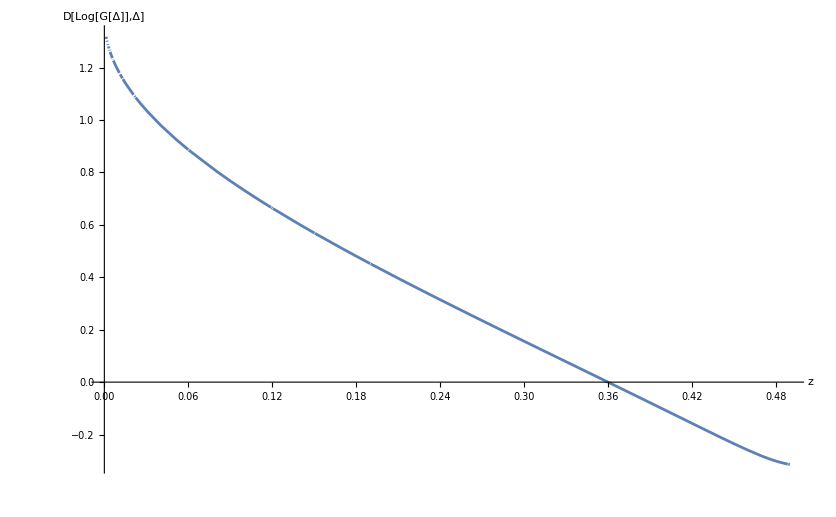

```mathematica
Plot[D[getLogLine[z],Δ[0]],{z,1/1000,49/100},AxesLabel->{"z","D[Log[G[Δ]],Δ]"}]
```

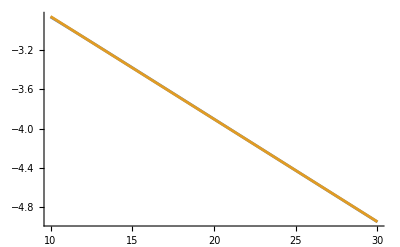

```mathematica
Plot[{Log[9 2^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],2/5]-4 3^Δ[0] 5^(-2-Δ[0]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],3/5]//Abs],%67},{Δ[0],10,30},WorkingPrecision->30]
```

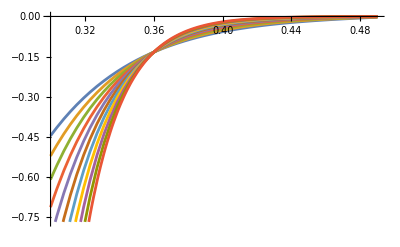

```mathematica
Plot[%34,{z,30/100,49/100},WorkingPrecision->20]
```

```mathematica
Manipulate[Plot[4^(-Δ[0]) (-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]),{z,30/100,49/100},WorkingPrecision->20],{Δ[0],10,20}]
```

Plot::precw: The precision of the argument function (4^-10. (-(1-z)^10. z^2 Hypergeometric2F1[10.,10.,2 10.,1-z]+(1-z)^2 z^10. Hypergeometric2F1[10.,10.,2 10.,z])) is less than WorkingPrecision (20.).

Plot::precw: The precision of the argument function (4^-11.04 (-(1-z)^11.04 z^2 Hypergeometric2F1[11.04,11.04,2 11.04,1-z]+(1-z)^2 z^11.04 Hypergeometric2F1[11.04,11.04,2 11.04,z])) is less than WorkingPrecision (20.).

Plot::precw: The precision of the argument function (4^-10.26 (-(1-z)^10.26 z^2 Hypergeometric2F1[10.26,10.26,2 10.26,1-z]+(1-z)^2 z^10.26 Hypergeometric2F1[10.26,10.26,2 10.26,z])) is less than WorkingPrecision (20.).

Plot::precw: The precision of the argument function (4^-10.26 ((-(1+Times[«2»])^10.26 z^2) Hypergeometric2F1[10.26,10.26,2 10.26,1-z]+((1-z)^2 z^10.26) Hypergeometric2F1[10.26,10.26,2 10.26,z])) is less than WorkingPrecision (20.).

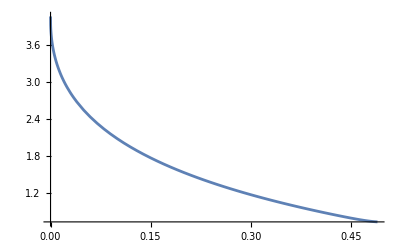

```mathematica
Plot[D[crossingEq[0]/.Δσ->1/.Δ[0]->Δ[0]+1,C[0]]/D[crossingEq[0]/.Δσ->1,C[0]]/.Δ[0]->20,{z,0,49/100},WorkingPrecision->30]
```

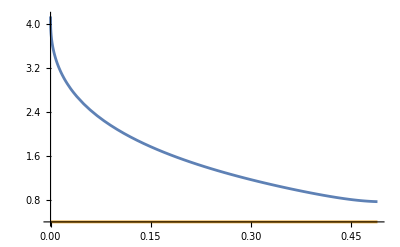

```mathematica
Plot[{D[crossingEq[0]/.Δσ->1/.Δ[0]->11,C[0]]/D[crossingEq[0]/.Δσ->1/.Δ[0]->10,C[0]],4*1/10},{z,0,49/100},WorkingPrecision->30]
```

```mathematica
Integrate[Exp[-a x],{x,1,Infinity}]
```

ConditionalExpression[ⅇ^-a/a, Re[a]>0]

```mathematica
Series[D[crossingEq[0]/.Δσ->1,C[0]],{z,1/2,2}]
```

2^(-2-Δ[0]) (-8 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]+4 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]+Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]) (z-1/2)+O[z-1/2]^3

```mathematica
Series[D[crossingEq[0]/.Δσ->1/.Δ[0]->10,C[0]],{z,0,2}]
```

46189/63 (7129+1260 Log[z]) z^2+O[z]^3

```mathematica
N[Log[(Gamma[2 Δ[0]] (2 EulerGamma+Log[z]+2 PolyGamma[0,Δ[0]]))/Gamma[Δ[0]]^2]/.Δ[0]->10/.z->5/100,30]
```

14.7153836662236995136823794661

```mathematica
D[crossingEq[0]/.Δσ->1,C[0]]
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
N[D[crossingEq[0]/.Δσ->1,C[0]]/.Δ[0]->10/.z->1/100,50]
```

-23.513394842868392169975394571340548337624651374843

```mathematica
N[Normal[%137]/.Δ[0]->10/.z->1/100,50]
```

97.252447288950825762302129528494336619181052097061

```mathematica
N[Gamma[2 Δ[0]] /Gamma[Δ[0]]^2/.Δ[0]->10]
```

923780.

```mathematica
Series[Gamma[2 Δ[0]] /Gamma[Δ[0]]^2,{Δ[0],Infinity,0}]//Normal
```

(2^(-1+2 Δ[0]) √Δ[0])/(√π)

```mathematica
Log[%]//Simplify
```

Log[(2^(-1+2 Δ[0]) √Δ[0])/(√π)]

```mathematica
FullSimplify[%,Δ[0]>100]
```

1/2 Log[Δ[0]/(4 π)]+Log[4] Δ[0]

```mathematica
Series[D[crossingEq[0]/.Δσ->1/.Δ[0]->2,C[0]],{z,0,2}]
```

(13+6 Log[z]) z^2+O[z]^3

```mathematica
N[(13+6 Log[z])/.z->1/100]
```

-14.631

```mathematica
Series[D[crossingEq[0]/.Δσ->1/.Δ[0]->10,C[0]],{z,0,2}]
```

46189/63 (7129+1260 Log[z]) z^2+O[z]^3

```mathematica
Table[getAvCs[15,Table[2n+1/n/(2n-1)g,{n,1,15}],44/100,49/100,1,60][[;;5,2]]//Total,{g,-1,1,1/10}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00709882907370738335084531289770685767078350934463520013534001,-0.00875249896779855640343288109750231882768549791702012271474889,-0.0107914328567816200464421794088094764132315059592678392728921,-0.0133054142658958847018944281160882903301928593450004568331668,-0.0164051522008890126841504783211590349070117636196609731822339,-0.020227101222431685118672881867364239637422644258385834703348,-0.0249391700492131066319364943135310708796688876016760442916051,-0.0307467732999974972734833406382362675567353721077343604452735,-0.037896296505454173423388326109942766901855102761285514171318,-0.0466634573632611805848877032454800874043406745706334608067464,«6»},«9»,«5»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00361776834311740388667384871590575274152058333393491548954932,-0.0046791791577463787031644958763222155607560923595983618490101,-0.00605202779029074796582157579568316365411448019906580653960063,-0.00782771054543614936509375076288266686539556311839617513988933,-0.0101244268004625627434366195167388730511683535600756371497724,-0.013094939845770729081611089856561212475679099861032996112721,-0.016936272175391784577986760131447457253251453366401441127395,-0.0219009208281822435776452843398391344953214506982065523499302,-0.0283063604159416982493421398617024923413747308666317990390215,-0.0365286444525655085547413630477209574063246640532870606995807,«6»},«9»,«5»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00183637920221180101610777483955781432208255120703828868537615,-0.00249208540057883958168628226811326188375911584423551256605432,-0.00338193802822476395065618434755860493283747905797008694371957,-0.00458954422211425195881667870222633921903056309425053161130632,-0.00622831523429702792405772531856555097780239030525302987594269,-0.00845193318843290640019308325575596391994950530809814805454053,-0.0114680696256237209310387365009701215367297488035808312564161,-0.01555526580991618359424831056903340994540258744488038572121,-0.0210797082296250441027851991617873728969497649482672652881017,-0.0284964750342798507781407876819830100316222607633773644757053,«6»},«9»,«5»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

$Aborted

```mathematica
Table[2i,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]
```

{2+0.285303878242166135040806430867009305141971408615029946989852 g,4-0.528267008395389624000561590565869225282210549276356455888088 g,6-0.761249889053236447480493659648779840989786866819568390723519 g,8-0.811166796537454060794337550634786140310070879368342504039943 g,10+0.026267704483545828762198826321945631503897399485322798015309 g,12-0.376960550480428705687882928654729813915035950203470761324597 g,14-0.115259866154431529394868884497735703343673505108984484408979 g,16-0.543054978822635673997334017879145437881502330833335141909983 g,18-0.931053186827839665649400974132667292451388774006426862435361 g,20-0.563747698603918828543264073777148180661823151620714360131465 g}

```mathematica
Table[
t=Table[2i,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10];ParallelTable[getAvCs[10,t,40/100,49/100,1,60][[;;5,2]]//Total,{g,-1,1,1/10}],10];
```

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.0003211316122210559624715533107028245389994304015295829858, 
      -0.000480692700564535740<<23>>33776213457957, <<8>>, 
      0.03636363636363636363636363636363636363636363636363636364}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00032763276820257132502967991361759600776988541715527549429, 
      -0.00056938097999997902<<26>>4434935931698, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00032471846854679120427824227976217999329307042478189573126, 
      -0.00056759380815875260<<26>>0468404970012, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00026284581904146226144391485043779884666584885845248470509, 
      -0.00048114658023300464<<26>>7882910659212, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00031019881451504530161667911891019505365440081696466097941, 
      -0.00054942043766580665<<26>>4119638018912, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00031986147327942102244467073960901481168459596118471813871, 
      -0.00059867562559384571<<26>>1977266511281, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00032336535052168524826427661353201351363523446458390541177, 
      -0.00060686275349571815<<26>>4678971641217, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00032648884338870592316765488816123879334278225174417680099, 
      -0.00047888762941449734<<26>>3227300245321, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

RowReduce::luc: 
   Result for RowReduce of badly conditioned matrix 
    {{-0.00024727287520447385907555484110844546891601313090019720224, 
      -0.00067660290658828620<<26>>4645263929389, <<8>>, 
      0.036363636363636363636363636363636363636363636363636363636}, <<9>>} may
     contain significant numerical errors.

```mathematica
Table[{Table[g,{g,-1,1,1/10}][[i]],Around[Mean[%82][[i]]/%84,StandardDeviation[%82][[i]]/%84]},{i,Length[Mean[%82]]}]
```

{{-1,410.790.},{-9/10,247.240.},{-4/5,192.186.},{-7/10,273.521.},{-3/5,105.130.},{-1/2,57.51.},{-2/5,38.29.},{-3/10,25.18.},{-1/5,16.10.},{-1/10,7.5.},{0,1.},{1/10,6.4.},{1/5,13.8.},{3/10,19.12.},{2/5,25.16.},{1/2,33.20.},{3/5,45.25.},{7/10,216.465.},{4/5,111.135.},{9/10,64.51.},{1,67.56.}}

```mathematica
{142.102.,107.73.,83.55.,66.43.,52.33.,41.26.,31.20.,22.14.,15.9.,7.4.,Around[1,0.00001],7.4.,15.8.,23.12.,32.16.,42.21.,56.28.,76.44.,163.246.,163.192.,148.92.}
```

{142.102.,107.73.,83.55.,66.43.,52.33.,41.26.,31.20.,22.14.,15.9.,7.4.,1.0000000.000010,7.4.,15.8.,23.12.,32.16.,42.21.,56.28.,76.44.,163.246.,163.192.,148.92.}

```mathematica
Table[
t=Table[2i,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10];ParallelTable[getAvCs[10,t,40/100,49/100,1,60][[;;5,2]]//Total,{g,-1,1,1/10}],10];
```

```mathematica
Around[1,0.00001]
```

1.0000000.000010

```mathematica
Mean[%82]/%84
```

{410.2033306593342752571256529338,246.681733435176339555933796267,191.703282489976597784465372882,273.119223717632374758831495269,104.6080432252457595710622853,56.7867829209975332741767591495,37.72996772600842574912873655521,25.24926355380816351082266536838,15.57548559848680116071181574711,7.45883177612992931532287831406,1.,6.452918659073196980274099738406,12.77851372782869063782732066278,19.00925459681115378578763470381,25.47209903063459548308921072015,33.0967948091054481987674426474,44.8273845973683701099907032815,215.70121472102570032535098686,111.485853635727767097427306887,63.5436282801994812885453370115,66.9608876998284063251059067193}

```mathematica
Table[g,{g,-1,1,1/10}]
```

{-1,-9/10,-4/5,-7/10,-3/5,-1/2,-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

{{-1,410.2033306593342752571256529338},{-9/10,246.681733435176339555933796267},{-4/5,191.703282489976597784465372882},{-7/10,273.119223717632374758831495269},{-3/5,104.6080432252457595710622853},{-1/2,56.7867829209975332741767591495},{-2/5,37.72996772600842574912873655521},{-3/10,25.24926355380816351082266536838},{-1/5,15.57548559848680116071181574711},{-1/10,7.45883177612992931532287831406},{0,1.},{1/10,6.452918659073196980274099738406},{1/5,12.77851372782869063782732066278},{3/10,19.00925459681115378578763470381},{2/5,25.47209903063459548308921072015},{1/2,33.0967948091054481987674426474},{3/5,44.8273845973683701099907032815},{7/10,215.70121472102570032535098686},{4/5,111.485853635727767097427306887},{9/10,63.5436282801994812885453370115},{1,66.9608876998284063251059067193}}

```mathematica
StandardDeviation[%82]/%84
```

{789.530781751309356708725596101,239.911997137452787516895390238,186.001828885809384048894542289,521.402302037393106040619709411,130.2603711204043608965652834,50.6865169284575485033404208266,28.8139435349961906223336099557,17.6875949305922661150406673751,10.3714215911032075032538233686,4.79527665360296662739815505356,0.,4.2104242843749230571823601018,8.09060927267748764858970343254,11.9801979126039297907504654875,15.9943310786988511902205196315,19.8815226933012350562959539909,24.599084797551231358114222123,465.17073668989422206655001627,135.21202290441245234300541285,51.3848132230651385383271006868,55.6924944953662151812657239151}

```mathematica
Sum[%82[[i]],{i,10}]/10
```

{0.009753649552494643871520375952988,0.00586549888578741249157666490697,0.00455824342641174662162346432102,0.00649411887979888991083442570941,0.00248732791211440950311769543301,0.00135025324863825417717483136963,0.0008971279736683566550593988768817,0.0006003668175160301474959101025953,0.0003703476222228246597238725323007,0.000177353097300423033898271522907,0.000023777597165818373724171457933858,0.0001534349004192353491204532175648,0.0003038423517981906559844842071036,0.0004519943982254567827754388301912,0.000605665309718262102255788439721,0.000786962254450657968503133303593,0.00106588749295343637726580028891,0.005128856591814241164347758311,0.00265086571743772259087987241737,0.00151091479570108744764401977648,0.00159216901359212231626304161843}

```mathematica
Table[{Table[g,{g,-1,1,1/10}],%82[[i]]/%84}//Transpose,{i,10}]
```

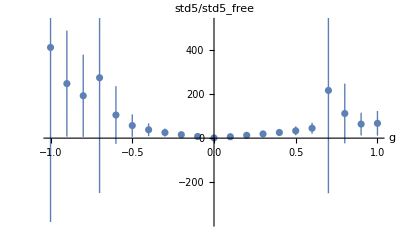

```mathematica
ListPlot[%103,AxesLabel->{"g",std5/std5_free}]
```

```mathematica
Table[
t=Table[2i+1,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10];ParallelTable[getAvCs[10,t,40/100,49/100,1,60][[;;5,2]]//Total,{g,-1/10,1/10,1/100}],10];
```

```mathematica
Rationalize[{2.05379,4.05476,6.05321,8.05334}]
```

{205379/100000,101369/25000,605321/100000,402667/50000}

```mathematica
getAvCs[4,{205379/100000,101369/25000,605321/100000,402667/50000},40/100,49/100,1,60][[;;,2]]
```

{0.01081708789875390648467849508878374959951141545291635,0.008779237525182636912419356272514527097539011411880078,0.0044122740105083459411996112382304045637449841339083776,0.0010285281616302249667751705817562419664901862209902736}

```mathematica
getAvCs[4,{2,4,6,8},40/100,49/100,1,60][[;;,2]]
```

{0.01317562702500057117442240033111220507329196972862413,0.009918977500546304309329443308454178010755062103308163,0.004830592599429672049537720754075292757553930683478706,0.0011082476060503905319094721991215557817924167946498479}

```mathematica
%966/%965
```

{0.8209922668749374039672823584590231369622958399436788,0.8850950135433925212910906340998151588189185789125555,0.9134022212987459878153703678343329114771615269276872,0.9280671178670330202889334803132560977150200390219283}

```mathematica
getAvCs[10,Table[2i+1,{i,1,10}],40/100,49/100,1,60][[;;5,2]]//Total
```

1.410587705834545365033826891727×10^-6

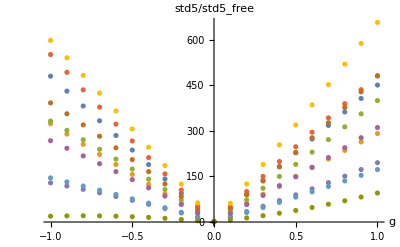

```mathematica
ListPlot[Table[{Table[g,{g,-1,1,1/10}],%25[[i]]/%23}//Transpose,{i,10}],AxesLabel->{"g",std5/std5_free}]
```

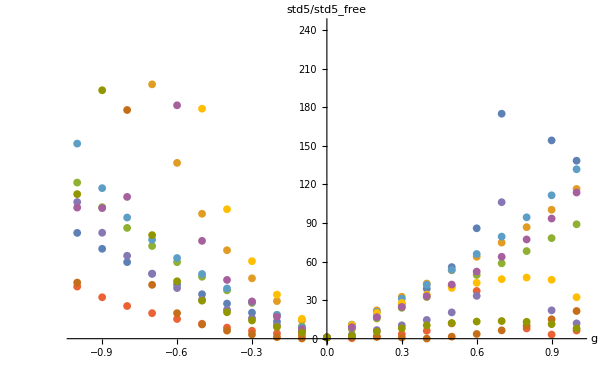

```mathematica
ListPlot[Table[{Table[g,{g,-1,1,1/10}],%82[[i]]/%84}//Transpose,{i,10}],AxesLabel->{"g",std5/std5_free}]
```

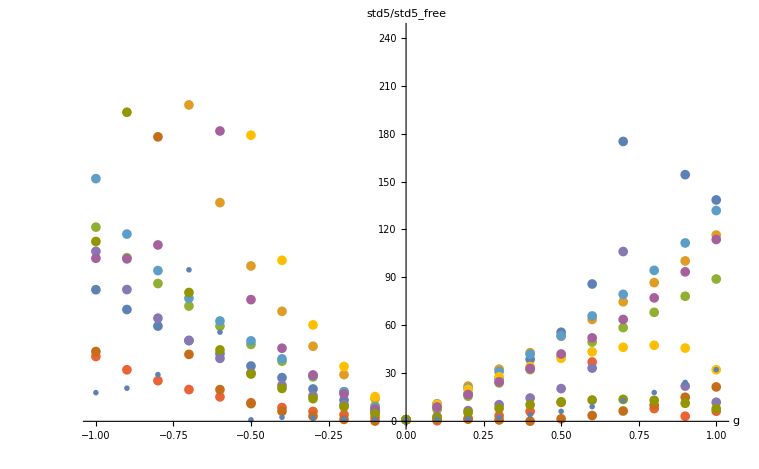

```mathematica
Show[%101,%190]
```

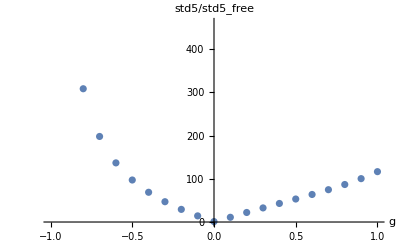

```mathematica
ListPlot[{Table[g,{g,-1,1,1/10}],%82[[2]]/%84}//Transpose,AxesLabel->{"g",std5/std5_free}]
```

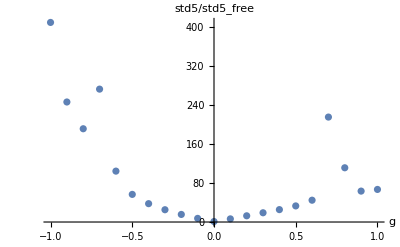

```mathematica
ListPlot[{Table[g,{g,-1,1,1/10}],Mean[%82]/%84}//Transpose,AxesLabel->{"g",std5/std5_free}]
```

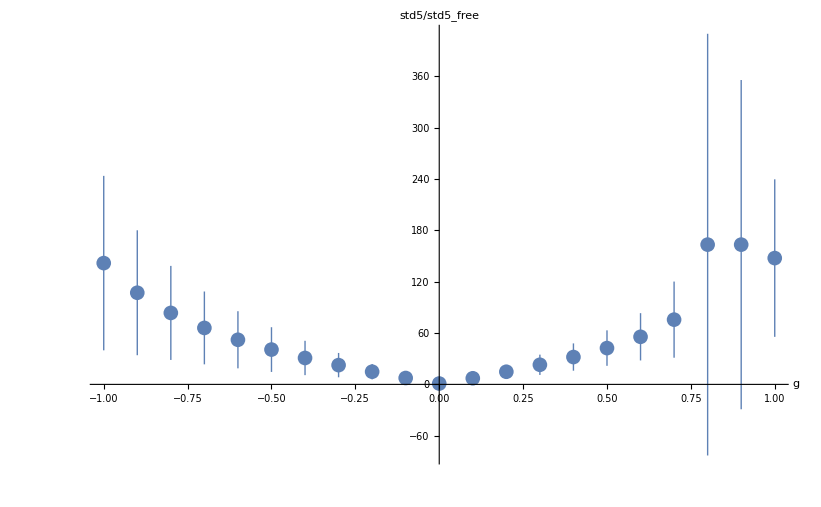

```mathematica
ListPlot[%525,AxesLabel->{"g",std5/std5_free}]
```

```mathematica
%44/.C[i_]->0
```

{-2,0,0}

```mathematica
D[%44,C[0]]/.genBos/.Δσ->1//N
```

{0.411169,-2.16852,0.925931}

```mathematica
D[%44,C[1]]/.genBos/.Δσ->1//N
```

{0.830608,0.609522,-12.0473}

```mathematica
D[%44,C[2]]/.genBos/.Δσ->1//N
```

{0.691198,11.9026,18.5594}

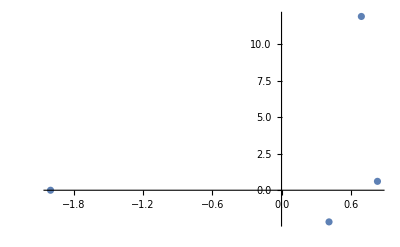

```mathematica
ListPlot[{%46[[;;2]],%45[[;;2]],%47[[;;2]],%48[[;;2]]}]
```

```mathematica
D[%44,C[0]]/.Δ[i_]->2+i/.Δσ->1//N
```

{0.411169,-2.16852,0.925931}

```mathematica
D[%44,C[1]]/.Δ[i_]->2+i/.Δσ->1//N
```

{0.746244,-2.6388,-2.99936}

```mathematica
D[%44,C[2]]/.Δ[i_]->2+i/.Δσ->1//N
```

{0.830608,0.609522,-12.0473}

```mathematica
Solve[%44==0/.Δ[i_]->2+i/.Δσ->1,{C[0],C[1],C[2]}]//N
```

{{C[0]→30.833,C[1]→-23.4425,C[2]→8.20613}}

```mathematica
{%54,%55,%56}
```

{{0.411169,-2.16852,0.925931},{0.746244,-2.6388,-2.99936},{0.830608,0.609522,-12.0473}}

```mathematica
Table[C[i],{i,3}].{%54,%55,%56}
```

{0.411169 C[1]+0.746244 C[2]+0.830608 C[3],-2.16852 C[1]-2.6388 C[2]+0.609522 C[3],0.925931 C[1]-2.99936 C[2]-12.0473 C[3]}

```mathematica
Solve[%69[[2;;]]==0]
```

{{C[2]→0.-0.760305 C[1],C[3]→0.+0.266148 C[1]}}

```mathematica
%69/.%70[[1]]//Simplify
```

{0.+0.0648602 C[1],0.,0.+3.33067×10^-16 C[1]}

```mathematica
ListPointPlot3D[{%46}]
```

-Graphics3D-

```mathematica
{Table[C[i],{i,3}].{Normalize[%54],Normalize[%55],Normalize[%56]}
}//Evaluate
```

{{0.171785 C[1]+0.183622 C[2]+0.0686949 C[3],-0.906 C[1]-0.649307 C[2]+0.0504101 C[3],0.386851 C[1]-0.738027 C[2]-0.996363 C[3]}}

```mathematica
%54
```

{0.411169,-2.16852,0.925931}

```mathematica
Graphics3D[Arrow[{{0,0,0},#}]&/@{%54,%55,%56}]
```

-Graphics3D-

```mathematica
%46
```

{-2,0,0}

```mathematica
Table[C[i],{i,4}].{%46,%54,%55,%56}
```

{-2 C[1]+0.411169 C[2]+0.746244 C[3]+0.830608 C[4],-2.16852 C[2]-2.6388 C[3]+0.609522 C[4],0.925931 C[2]-2.99936 C[3]-12.0473 C[4]}

```mathematica
{%46.Table[C[i],{i,3}]>=0,%54.Table[C[i],{i,3}]>=0,%55.Table[C[i],{i,3}]>=0,%56.Table[C[i],{i,3}]>=0}
```

{-2 C[1]≥0,0.411169 C[1]-2.16852 C[2]+0.925931 C[3]≥0,0.746244 C[1]-2.6388 C[2]-2.99936 C[3]≥0,0.830608 C[1]+0.609522 C[2]-12.0473 C[3]≥0}

```mathematica
Join[%112,Table[C[i]>0,{i,3}]]
```

{-2 C[1]≥0,0.411169 C[1]-2.16852 C[2]+0.925931 C[3]≥0,0.746244 C[1]-2.6388 C[2]-2.99936 C[3]≥0,0.830608 C[1]+0.609522 C[2]-12.0473 C[3]≥0,C[1]>0,C[2]>0,C[3]>0}

```mathematica
FindInstance[Join[%112,{C[1]C[2]C[3]!=0}],Table[C[i],{i,3}]]
```

{{C[1]→-5.9281,C[2]→-11.6868,C[3]→-1.}}

```mathematica
data={{1,2,3},{3,4,5},{5,6,7}};

Graphics3D[Arrow[{{0,0,0},#}]&/@{%46,%54,%55,%56}]
```

-Graphics3D-

```mathematica
{%46,%54,%55,%56}[[;;1]]
```

```mathematica
Manipulate[ListPointPlot3D[{{%46,%54,%55,%56}[[;;1]],{%46,Normalize[%54],Normalize[%55],Normalize[%56]}
[[2;;]],{{0.17178524648477284 C[1]+0.18362186799912622 C[2]+0.06869489706833685 C[3],-0.9060000489855936 C[1]-0.6493068025650486 C[2]+0.05041014658784923 C[3],0.38685105703392886 C[1]-0.7380268868647433 C[2]-0.9963633013302738 C[3]}}}],{C[1],0,1},{C[2],0,1},{C[3],0,1}]
```

```mathematica
Manipulate[%90//Evaluate,{C[1],0,1},{C[2],0,1},{C[3],0,1}]
```

```mathematica
Normalize[%54]
```

{0.171785,-0.906,0.386851}

```mathematica
{%46,Normalize[%54],Normalize[%55],Normalize[%56]}
```

{{-2,0,0},{0.171785,-0.906,0.386851},{0.183622,-0.649307,-0.738027},{0.0686949,0.0504101,-0.996363}}

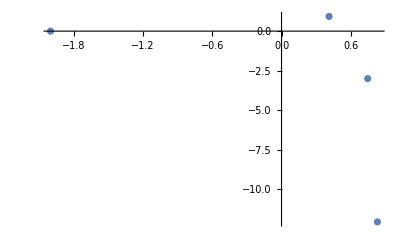

```mathematica
ListPlot[{%46[[{1,3}]],%54[[{1,3}]],%55[[{1,3}]],%56[[{1,3}]]}]
```

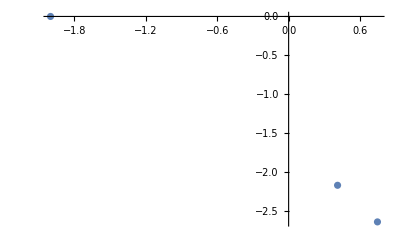

```mathematica
ListPlot[{%46[[;;2]],%54[[;;2]],%55[[;;2]]}]
```

```mathematica
ListPlot[{{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->x}/.{{z->4/10},{z->45/100}}//Simplify}]//Evaluate
```

-Graphics-

```mathematica
{{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->x}/.{{z->4/10},{z->45/100}}//Simplify}//Evaluate
```

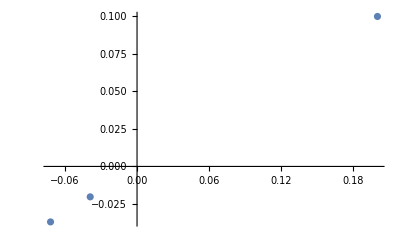

```mathematica
ListPlot[{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->3}/.{{z->4/10},{z->45/100}}//Simplify//Transpose]
```

```mathematica
Table[D[{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->x},{z,n}],{n,1,3,2}]/.z->1/2//Simplify
```

{{-2,42-60 Log[2],2^(-2-x) (4 (-2+x) Hypergeometric2F1[x,x,2 x,1/2]+x Hypergeometric2F1[1+x,1+x,1+2 x,1/2])},{0,1584-2304 Log[2],1/(1+2 x)2^(-3-x) x (32 (14+19 x-17 x^2+2 x^3) Hypergeometric2F1[x,x,2 x,1/2]+24 (2-x-9 x^2+2 x^3) Hypergeometric2F1[1+x,1+x,1+2 x,1/2]+(1+x) (12 (-2-x+x^2) Hypergeometric2F1[2+x,2+x,2+2 x,1/2]+(2+x)^2 Hypergeometric2F1[3+x,3+x,3+2 x,1/2]))}}

```mathematica
blockvec
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
%148//Dimensions
```

{2,3}

```mathematica
{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}
```

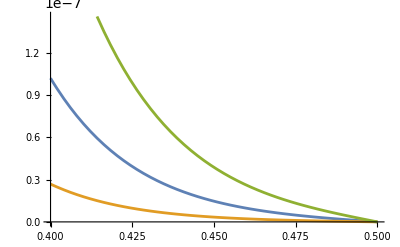

```mathematica
Plot[{crossingEq[6]/.genBos/.Δσ->1,crossingEq[6]/.genFer/.Δσ->1,crossingEq[12]/.{Δ[0]->2,C[0]->1,Δ[1]->3,C[1]->1,Δ[2]->4,C[2]->3/5,Δ[3]->5,C[3]->2/7,Δ[4]->6,C[4]->5/42,Δ[5]->7,C[5]->1/22,Δ[6]->8,C[6]->7/429,Δ[7]->9,C[7]->4/715,Δ[8]->10,C[8]->9/4862,Δ[9]->11,C[9]->5/8398,Δ[10]->12,C[10]->11/58786,Δ[11]->13,C[11]->3/52003,Δ[12]->14,C[12]->13/742900,Δ[13]->15,C[13]->7/1337220,Δ[14]->16,C[14]->1/646323,Δ[15]->17,C[15]->8/17678835,Δ[16]->18,C[16]->17/129644790,Δ[17]->19,C[17]->3/79606450}/.Δσ->1},{z,4/10,1/2},WorkingPrecision->40]
```

```mathematica
{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->2+x,blockvec/.Δ[0]->2+2x}
```

```mathematica
Table[D[{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->2+x,blockvec/.Δ[0]->2+2x,blockvec/.Δ[0]->2+3x,blockvec/.Δ[0]->2+4x,blockvec/.Δ[0]->2+5x,blockvec/.Δ[0]->2+6x,blockvec/.Δ[0]->2+7x,blockvec/.Δ[0]->2+8x,blockvec/.Δ[0]->2+9x},{z,n}],{n,1,7,2}]/.z->1/2//Simplify//Transpose
```

```mathematica
LegendreP[J,x]-Hypergeometric2F1[-J,1+J,1,(1-x)/2]/.J->3//Simplify
```

0

```mathematica
1-Abs[x]
```

1-Abs[x]

```mathematica
crossingEqToy2[2]/.C[0]->1/2/.C[1]->0/.C[2]->-5/8/.x->1/2//N
```

-0.078125

```mathematica
crossingEqToy2[4]/.C[0]->1/2/.C[1]->0/.C[2]->-5/8/.C[3]->0/.C[4]->3/16/.C[5]->0/.C[6]->-13/128/.x->1/2//N
```

-0.0239258

```mathematica
crossingEqToy2[6]/.J[i_]->i
```

1-Abs[x]-C[0]-x C[1]-1/2 (-1+3 x^2) C[2]-1/2 (-3 x+5 x^3) C[3]-1/8 (3-30 x^2+35 x^4) C[4]-1/8 (15 x-70 x^3+63 x^5) C[5]-1/16 (-5+105 x^2-315 x^4+231 x^6) C[6]

```mathematica
Table[C[i]->getLegendreCoeff[Function[{x},1-Abs[x]],i],{i,0,10}]
```

{C[0]→1/2,C[1]→0,C[2]→-5/8,C[3]→0,C[4]→3/16,C[5]→0,C[6]→-13/128,C[7]→0,C[8]→17/256,C[9]→0,C[10]→-49/1024}

```mathematica
Solve[crossingEqToy2[12]==0/.J[i_]->i/.x->z/.zvalsTable[-9/10,9/10,12]]
```

{{C[0]→8723360848/4787751969,C[1]→0,C[2]→27060392362/4787751969,C[3]→0,C[4]→10150314704/1004836833,C[5]→0,C[6]→186771280000/16993888857,C[7]→0,C[8]→856279040000/90967287411,C[9]→0,C[10]→1024000000000/188191584009,C[11]→0,C[12]→65536000000000/35568209377701}}

```mathematica
N[crossingEqToy2[12]/.J[i_]->i/.%918/.x->1/2,30]
```

{0.0385118532024773733636994093}

```mathematica
D[Sum[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]C[i],{i,0,12}]/.J[i_]->i,{Table[C[i],{i,0,12}],1}]/.x->z/.zvalsTable[-9/10,9/10,12]
```

{{1,-9/10,143/200,-189/400,3327/16000,32913/800000,-3858629/16000000,58851999/160000000,-1048795913/2560000000,9459468441/25600000000,-673652781711/2560000000000,2975062848489/25600000000000,41726683414959/1024000000000000},{1,-3/4,11/32,9/128,-717/2048,3411/8192,-18401/65536,8961/262144,1657667/8388608,-10413009/33554432,70967493/268435456,-103526289/1073741824,-1782321609/17179869184},{1,-3/5,1/25,9/25,-51/125,477/3125,2689/15625,-25203/78125,16589/78125,18009/390625,-2379519/9765625,11581677/48828125,-12063999/244140625},{1,-9/20,-157/800,1431/3200,-52473/256000,-4908087/25600000,336876871/1024000000,-2265110901/20480000000,-127493053433/655360000000,3455978332041/13107200000000,-131997302420211/2621440000000000,-10299240284020011/52428800000000000,904243623147023559/4194304000000000000},{1,-3/10,-73/200,153/400,1167/16000,-276309/800000,2066899/16000000,35851677/160000000,-612030953/2560000000,-1630729773/25600000000,643779454761/2560000000000,-2204618901813/25600000000000,-185346232004001/1024000000000000},{1,-3/20,-373/800,693/3200,74967/256000,-6459309/25600000,-178837601/1024000000,5425621377/20480000000,51318464167/655360000000,-3377380346973/13107200000000,7764208776261/2621440000000000,12236915338728687/52428800000000000,-292836558995942601/4194304000000000000},{1,0,-1/2,0,3/8,0,-5/16,0,35/128,0,-63/256,0,231/1024},{1,3/20,-373/800,-693/3200,74967/256000,6459309/25600000,-178837601/1024000000,-5425621377/20480000000,51318464167/655360000000,3377380346973/13107200000000,7764208776261/2621440000000000,-12236915338728687/52428800000000000,-292836558995942601/4194304000000000000},{1,3/10,-73/200,-153/400,1167/16000,276309/800000,2066899/16000000,-35851677/160000000,-612030953/2560000000,1630729773/25600000000,643779454761/2560000000000,2204618901813/25600000000000,-185346232004001/1024000000000000},{1,9/20,-157/800,-1431/3200,-52473/256000,4908087/25600000,336876871/1024000000,2265110901/20480000000,-127493053433/655360000000,-3455978332041/13107200000000,-131997302420211/2621440000000000,10299240284020011/52428800000000000,904243623147023559/4194304000000000000},{1,3/5,1/25,-9/25,-51/125,-477/3125,2689/15625,25203/78125,16589/78125,-18009/390625,-2379519/9765625,-11581677/48828125,-12063999/244140625},{1,3/4,11/32,-9/128,-717/2048,-3411/8192,-18401/65536,-8961/262144,1657667/8388608,10413009/33554432,70967493/268435456,103526289/1073741824,-1782321609/17179869184},{1,9/10,143/200,189/400,3327/16000,-32913/800000,-3858629/16000000,-58851999/160000000,-1048795913/2560000000,-9459468441/25600000000,-673652781711/2560000000000,-2975062848489/25600000000000,41726683414959/1024000000000000}}

```mathematica
zvalsTable[-9/10,9/10,12]
```

{{z→-9/10},{z→-3/4},{z→-3/5},{z→-9/20},{z→-3/10},{z→-3/20},{z→0},{z→3/20},{z→3/10},{z→9/20},{z→3/5},{z→3/4},{z→9/10}}

```mathematica
1-Abs[x]/.x->z/.zvalsTable[-9/10,9/10,12]
```

{1/10,1/4,2/5,11/20,7/10,17/20,1,17/20,7/10,11/20,2/5,1/4,1/10}

```mathematica
N[Inverse[%896].%897,30]
```

{1.82201603267723495556876872959,0,5.6520038083033787166513094697,0,10.1014556499642166281936044436,0,10.9904967351287885382455281995,0,9.41304357170989492109656065075,0,5.44126351554078331345642401405,0,1.84254425923074143947730760264}

```mathematica
crossingEqToy2[10]/.J[i_]->i/.C[i_]->-%898[[i+1]]/.x->1/2
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

0.5307879613503411490304388863

```mathematica
crossingEqToy2[10]/.J[i_]->i/.{C[0]->1/2,C[1]->0,C[2]->-5/8,C[3]->0,C[4]->3/16,C[5]->0,C[6]->-13/128,C[7]->0,C[8]->17/256,C[9]->0,C[10]->-49/1024}/.x->1/2//N
```

0.00478655

```mathematica
{C[0]->1/2,C[1]->0,C[2]->-5/8,C[3]->0,C[4]->3/16,C[5]->0,C[6]->-13/128,C[7]->0,C[8]->17/256,C[9]->0,C[10]->-49/1024}//N
```

{C[0]→0.5,C[1]→0.,C[2]→-0.625,C[3]→0.,C[4]→0.1875,C[5]→0.,C[6]→-0.101563,C[7]→0.,C[8]→0.0664063,C[9]→0.,C[10]→-0.0478516}

```mathematica
{1-Abs[x],Sum[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]C[i],{i,0,10}]}/.J[i_]->i
```

{1-Abs[x],C[0]+x C[1]+1/2 (-1+3 x^2) C[2]+1/2 (-3 x+5 x^3) C[3]+1/8 (3-30 x^2+35 x^4) C[4]+1/8 (15 x-70 x^3+63 x^5) C[5]+1/16 (-5+105 x^2-315 x^4+231 x^6) C[6]+1/16 (-35 x+315 x^3-693 x^5+429 x^7) C[7]+1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8) C[8]+1/128 (315 x-4620 x^3+18018 x^5-25740 x^7+12155 x^9) C[9]+1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10) C[10]}

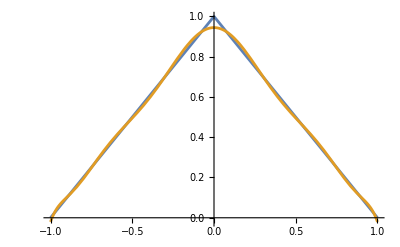

```mathematica
Plot[{1-Abs[x],Sum[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]C[i],{i,0,10}]}/.J[i_]->i/.{C[0]->1/2,C[1]->0,C[2]->-5/8,C[3]->0,C[4]->3/16,C[5]->0,C[6]->-13/128,C[7]->0,C[8]->17/256,C[9]->0,C[10]->-49/1024}//Evaluate,{x,-1,1}]
```

```mathematica
C[0]/.C[i_]->getLegendreCoeff[Function[{x},1-Abs[x]],i]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 2 ComplexInfinity)/(π √π) encountered.

Indeterminate

```mathematica
{1-Abs[x],Sum[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]C[i],{i,0,10}]}/.J[i_]->i/.{C[0]->1/2,C[1]->0,C[2]->-5/8,C[3]->0,C[4]->3/16,C[5]->0,C[6]->-13/128,C[7]->0,C[8]->17/256,C[9]->0,C[10]->-49/1024}/.x->1/2//N
```

{0.5,0.495213}

```mathematica
crossingEqToy2[10]/.J[i_]->i/.Table[C[i]->getLegendreCoeff[Function[{x},1-Abs[x]],i],{i,0,10}]/.x->1/2//N
```

0.00478655

```mathematica
Table[C[i]->getLegendreCoeff[Function[{x},1-Abs[x]],i],{i,0,10}]//N
```

{C[0]→0.5,C[1]→0.,C[2]→-0.625,C[3]→0.,C[4]→0.1875,C[5]→0.,C[6]→-0.101563,C[7]→0.,C[8]→0.0664063,C[9]→0.,C[10]→-0.0478516}

```mathematica
getAvCsToy[]
```

```mathematica
crossingEqToy2[20]/.J[i_]->i/.Table[C[i]->getLegendreCoeff[Function[{x},1-Abs[x]],i],{i,0,20}]/.x->1/2//N
```

0.0028703

```mathematica
crossingEqToy2[20]/.J[i_]->i/.Table[C[i]->getLegendreCoeff[Function[{x},1-Abs[x]],i],{i,0,20}]/.x->1/2//N
```

```mathematica
crossingEqToy2[6]/.C[0]->1/2/.C[1]->0/.C[2]->-5/8/.C[3]->0/.C[4]->3/16/.C[5]->0/.C[6]->-13/128/.x->1/2//N
```

0.0089035

```mathematica
getLegendreCoeff[Function[{x},1-Abs[x]],3]
```

0

```mathematica
getLegendreCoeff[f_,n_]:=(2n+1)/2Integrate[f[x]LegendreP[n,x],{x,-1,1}]
```

```mathematica
crossingEqToy2[n_]:=1-Abs[x]-Sum[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]C[i],{i,0,n}]
```

```mathematica
crossingEqToy[n_,deltas_]:=1/Sqrt[1-2x t+t^2]-Sum[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]C[i],{i,0,n}]/.deltas
```

```mathematica
Solve[crossingEqToy[4]==0/.J[i_]->i/.t->1/2/.{{x->-.7},{x->-.5},{x->0},{x->.5},{x->.7}}]
```

{{C[0]→0.993954,C[1]→0.47586,C[2]→0.226008,C[3]→0.0881007,C[4]→0.0359388}}

```mathematica
Table[Solve[crossingEqToy[4]==0/.J[i_]->i/.t->1/2/.x->z/.r]//N,{r,%1081}]
```

{{{C[0]→0.986706,C[1]→0.463942,C[2]→0.19872,C[3]→0.0716634,C[4]→0.0168467}},{{C[0]→0.991339,C[1]→0.475752,C[2]→0.213936,C[3]→0.0831656,C[4]→0.0248299}},{{C[0]→0.996431,C[1]→0.485802,C[2]→0.232775,C[3]→0.093737,C[4]→0.0383558}},{{C[0]→1.00387,C[1]→0.48869,C[2]→0.262407,C[3]→0.0970546,C[4]→0.0631595}},{{C[0]→1.02129,C[1]→0.463942,C[2]→0.328741,C[3]→0.0716634,C[4]→0.114363}}}

```mathematica
Mean[(Table[C[i],{i,0,nstates}]/.%1082)[[;;,1]]]
```

{0.999928,0.475626,0.247316,0.0834568,0.0515109}

```mathematica
StandardDeviation[(Table[C[i],{i,0,nstates}]/.%1082)[[;;,1]]]
```

{0.013535,0.0116969,0.0513444,0.0119251,0.0392828}

```mathematica
%1075[[3]]
```

{{z→-3/4},{z→-1/4},{z→1/4},{z→3/4},{z→1251/1000}}

```mathematica
crossingEqToy[4]==0/.J[i_]->i/.t->1/2/.x->z/.%1075[[3]]
```

{1/(√2)-C[0]+(3 C[1])/4-(11 C[2])/32-(9 C[3])/128+(717 C[4])/2048==0,√(2/3)-C[0]+C[1]/4+(13 C[2])/32-(43 C[3])/128-(323 C[4])/2048==0,1-C[0]-C[1]/4+(13 C[2])/32+(43 C[3])/128-(323 C[4])/2048==0,√2-C[0]-(3 C[1])/4-(11 C[2])/32+(9 C[3])/128+(717 C[4])/2048==0,-10 ⅈ √10-C[0]-(1251 C[1])/1000-(3695003 C[2])/2000000-(1207216251 C[3])/400000000-(8354590910007 C[4])/1600000000000==0}

```mathematica
crossingEqToy[4]==0/.J[i_]->i/.t->1/2/.x->z/.%1075[[3]]
```

{1/(√2)-C[0]+(3 C[1])/4-(11 C[2])/32-(9 C[3])/128+(717 C[4])/2048==0,√(2/3)-C[0]+C[1]/4+(13 C[2])/32-(43 C[3])/128-(323 C[4])/2048==0,1-C[0]-C[1]/4+(13 C[2])/32+(43 C[3])/128-(323 C[4])/2048==0,√2-C[0]-(3 C[1])/4-(11 C[2])/32+(9 C[3])/128+(717 C[4])/2048==0,-10 ⅈ √10-C[0]-(1251 C[1])/1000-(3695003 C[2])/2000000-(1207216251 C[3])/400000000-(8354590910007 C[4])/1600000000000==0}

```mathematica
Solve[1+t^2-2 t x==0,x]/.t->1/2
```

{{x→5/4}}

```mathematica
nstates=4
```

4

```mathematica
crossingEqToy[4]/.J[i_]->i/.t->1/2/.x->z/.{{z->-3/4},{z->-1/4},{z->1/4},{z->3/4},{z->5/4+1/1000}}
```

{1/(√2)-C[0]+(3 C[1])/4-(11 C[2])/32-(9 C[3])/128+(717 C[4])/2048,√(2/3)-C[0]+C[1]/4+(13 C[2])/32-(43 C[3])/128-(323 C[4])/2048,1-C[0]-C[1]/4+(13 C[2])/32+(43 C[3])/128-(323 C[4])/2048,√2-C[0]-(3 C[1])/4-(11 C[2])/32+(9 C[3])/128+(717 C[4])/2048,-10 ⅈ √10-C[0]-(1251 C[1])/1000-(3695003 C[2])/2000000-(1207216251 C[3])/400000000-(8354590910007 C[4])/1600000000000}

```mathematica
solns[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=Range[Length[eqs]];Table[Solve[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP]//Chop,{i,nstates}],WorkingPrecision->WP][[1]],{j,0,9}]];
```

```mathematica
solns[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=Range[Length[eqs]];Table[Solve[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP]//Chop,{i,nstates}],WorkingPrecision->WP][[1]],{j,0,9}]];
```

```mathematica
solnsRand[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=RandomSample[Range[Length[eqs]],Length[eqs]];Table[Solve[Join[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP],{i,nstates}],Table[N[c[i]>=0,WP],{i,0,nstates-1}]]][[1]],{j,0,9}]];
```

```mathematica
Table[zvalsTable[-1+n del,-1+(n+1)del,10]/.del->2/(nstates+1),{n,0,nstates}]//Transpose//Dimensions
```

{11,5,1}

```mathematica
zs=Table[zvalsTable[-1+n del,-1+(n+1)del,10]/.del->2/(nstates+1),{n,0,nstates}]//Transpose;
```

```mathematica
Solve[N[crossingEqToy[nstates]=0/.Δσ->dσ/.zs[[1]]],WorkingPrecision->40]
```

Solve::naqs: 0.&&0.&&0.&&0.&&0. is not a quantified system of equations and inequalities.

Solve[{0.,0.,0.,0.,0.},WorkingPrecision→40]

```mathematica
Clear[crossingEqToy]
```

```mathematica
crossingEqToy[nstates]==0/.Δσ->dσ/.zs[[1]]
```

{0,0,0,0,0}

```mathematica
N[crossingEqToy[nstates]=0/.Δσ->dσ/.zs[[1]]]
```

{0.,0.,0.,0.,0.}

```mathematica
Solve[N[crossingEqToy[nstates]==0/.Δσ->dσ/.J[i_]->i/.t->1/2/.x->z/.zs[[3]]],WorkingPrecision->40]
```

{{C[0]→0.990401,C[1]→0.473454,C[2]→0.210708,C[3]→0.0808438,C[4]→0.0228995}}

```mathematica
Table[C[i],{i,0,nstates}]/.Solve[N[crossingEqToy[nstates]==0/.Δσ->dσ/.J[i_]->i/.t->1/2/.x->z/.zs[[-1]]],WorkingPrecision->40][[1]]
```

{1.02129,0.463942,0.328741,0.0716634,0.114363}

```mathematica
Solve[N[crossingEqToy[nstates]==0/.Δσ->dσ/.J[i_]->i/.t->1/2/.x->z/.zs[[-1]]],WorkingPrecision->40]
```

{{C[0]→1.02129,C[1]→0.463942,C[2]→0.328741,C[3]→0.0716634,C[4]→0.114363}}

```mathematica
Table[Solve[N[crossingEqToy[nstates]==0/.Δσ->dσ/.J[i_]->i/.t->1/2/.x->z/.zs[[j]]],WorkingPrecision->40][[1]],{j,Length[zs]}]
```

{{C[0]→0.986706,C[1]→0.463942,C[2]→0.19872,C[3]→0.0716634,C[4]→0.0168467},{C[0]→0.988548,C[1]→0.468741,C[2]→0.20456,C[3]→0.0762042,C[4]→0.0195788},{C[0]→0.990401,C[1]→0.473454,C[2]→0.210708,C[3]→0.0808438,C[4]→0.0228995},{C[0]→0.992293,C[1]→0.477989,C[2]→0.217296,C[3]→0.0854619,C[4]→0.0269731},{C[0]→0.994274,C[1]→0.48219,C[2]→0.224536,C[3]→0.0898636,C[4]→0.0320226},{C[0]→0.996431,C[1]→0.485802,C[2]→0.232775,C[3]→0.093737,C[4]→0.0383558},{C[0]→0.998917,C[1]→0.488398,C[2]→0.242578,C[3]→0.0965844,C[4]→0.0464072},{C[0]→1.00199,C[1]→0.489261,C[2]→0.254874,C[3]→0.0976067,C[4]→0.056805},{C[0]→1.0061,C[1]→0.487171,C[2]→0.271218,C[3]→0.0955021,C[4]→0.0704849},{C[0]→1.01205,C[1]→0.480003,C[2]→0.294272,C[3]→0.0881007,C[4]→0.0888922},{C[0]→1.02129,C[1]→0.463942,C[2]→0.328741,C[3]→0.0716634,C[4]→0.114363}}

```mathematica
Table[Table[C[i],{i,0,nstates-1}]/.Solve[N[crossingEqToy[nstates]==0/.Δσ->dσ/.J[i_]->i/.t->1/2/.x->z/.zs[[j]]],WorkingPrecision->40][[1]],{j,Length[zs]}]
```

{{0.986706,0.463942,0.19872,0.0716634},{0.988548,0.468741,0.20456,0.0762042},{0.990401,0.473454,0.210708,0.0808438},{0.992293,0.477989,0.217296,0.0854619},{0.994274,0.48219,0.224536,0.0898636},{0.996431,0.485802,0.232775,0.093737},{0.998917,0.488398,0.242578,0.0965844},{1.00199,0.489261,0.254874,0.0976067},{1.0061,0.487171,0.271218,0.0955021},{1.01205,0.480003,0.294272,0.0881007},{1.02129,0.463942,0.328741,0.0716634}}

```mathematica
getAvCsToy1[nstates_,deltas_,zmin_,zmax_,dσ_,WP_]:=Module[{cs,zs},
zs=Table[zvalsTable[-99/100+n del,-99/100+(n+1)del,10]/.del->2/(nstates+1),{n,0,nstates}]//Transpose;
cs=Table[Table[C[i],{i,0,nstates-1}]/.Solve[N[crossingEqToy[nstates,deltas]==0/.Δσ->dσ/.x->z/.zs[[j]]],WorkingPrecision->WP][[1]],{j,Length[zs]}];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
crossingEqToy[nstates,{J[i_]->i,t->1/2}]==0/.x->z/.zs[[1]]
```

{2/3-C[0]+C[1]-C[2]+C[3]-C[4]==0,2 √(5/37)-C[0]+(3 C[1])/5-C[2]/25-(9 C[3])/25+(51 C[4])/125==0,2 √(5/29)-C[0]+C[1]/5+(11 C[2])/25-(7 C[3])/25-(29 C[4])/125==0,2 √(5/21)-C[0]-C[1]/5+(11 C[2])/25+(7 C[3])/25-(29 C[4])/125==0,2 √(5/13)-C[0]-(3 C[1])/5-C[2]/25+(9 C[3])/25+(51 C[4])/125==0}

```mathematica
crossingEqToy[nstates,{t->1/2}]==0
```

1/(√(5/4-x))-C[0] Hypergeometric2F1[-J[0],1+J[0],1,(1-x)/2]-C[1] Hypergeometric2F1[-J[1],1+J[1],1,(1-x)/2]-C[2] Hypergeometric2F1[-J[2],1+J[2],1,(1-x)/2]-C[3] Hypergeometric2F1[-J[3],1+J[3],1,(1-x)/2]-C[4] Hypergeometric2F1[-J[4],1+J[4],1,(1-x)/2]==0

```mathematica
Hypergeometric2F1[-J[0],1+J[0],1,(1-x)/2]/.{J[i_]->i+1/100,t->1/2}/.x->z/.zs[[1]]
```

{-∞,Hypergeometric2F1[-1/100,101/100,1,4/5],Hypergeometric2F1[-1/100,101/100,1,3/5],Hypergeometric2F1[-1/100,101/100,1,2/5],Hypergeometric2F1[-1/100,101/100,1,1/5]}

```mathematica
Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]/.z->1/2//Simplify
```

Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]

```mathematica
Solve[Table[D[crossingEqToy[nstates,{J[i_]->i,t->1/2}],{x,n}]==0/.x->0,{n,0,nstates}]]//N
```

{{C[0]→0.986017,C[1]→0.443636,C[2]→0.200352,C[3]→0.0572433,C[4]→0.0228973}}

```mathematica
Solve[Table[D[crossingEqToy[nstates,{J[i_]->i,t->1/2}],{x,n}]==0/.x->1/10,{n,0,nstates}]]//N
```

{{C[0]→0.995479,C[1]→0.437693,C[2]→0.227094,C[3]→0.0533163,C[4]→0.0333227}}

```mathematica
Solve[Table[D[crossingEqToy[nstates,{J[i_]->i,t->1/2}],{x,n}]==0/.x->1/10,{n,0,nstates}]]//N
```

```mathematica
crossingEqToy[nstates,{J[i_]->i+1/100,t->1/2}]==0/.x->z/.zs[[1]]
```

{2/3+C[1] (-∞)+C[3] (-∞)+C[0] ∞+C[2] ∞+C[4] ∞==0,2 √(5/37)-C[4] Hypergeometric2F1[-401/100,501/100,1,4/5]-C[3] Hypergeometric2F1[-301/100,401/100,1,4/5]-C[2] Hypergeometric2F1[-201/100,301/100,1,4/5]-C[1] Hypergeometric2F1[-101/100,201/100,1,4/5]-C[0] Hypergeometric2F1[-1/100,101/100,1,4/5]==0,2 √(5/29)-C[4] Hypergeometric2F1[-401/100,501/100,1,3/5]-C[3] Hypergeometric2F1[-301/100,401/100,1,3/5]-C[2] Hypergeometric2F1[-201/100,301/100,1,3/5]-C[1] Hypergeometric2F1[-101/100,201/100,1,3/5]-C[0] Hypergeometric2F1[-1/100,101/100,1,3/5]==0,2 √(5/21)-C[4] Hypergeometric2F1[-401/100,501/100,1,2/5]-C[3] Hypergeometric2F1[-301/100,401/100,1,2/5]-C[2] Hypergeometric2F1[-201/100,301/100,1,2/5]-C[1] Hypergeometric2F1[-101/100,201/100,1,2/5]-C[0] Hypergeometric2F1[-1/100,101/100,1,2/5]==0,2 √(5/13)-C[4] Hypergeometric2F1[-401/100,501/100,1,1/5]-C[3] Hypergeometric2F1[-301/100,401/100,1,1/5]-C[2] Hypergeometric2F1[-201/100,301/100,1,1/5]-C[1] Hypergeometric2F1[-101/100,201/100,1,1/5]-C[0] Hypergeometric2F1[-1/100,101/100,1,1/5]==0}

```mathematica
getAvCsToy1[10,{J[i_]->i,t->1/2},-1,1,1,30][[;;,2]]//Total
```

0.011577

```mathematica
getAvCsToy1[10,{J[i_]->i+1/100,t->1/2},-1,1,1,30][[;;,2]]//Total
```

0.00956517

```mathematica
RandomInteger[{0,100},nstates]/100
```

{41/100,11/50,3/100,41/100}

```mathematica
RandomInteger[{0,100},nstates]/100
```

{97/100,9/100,63/100,71/100}

```mathematica
getAvCsToy1[10,{J[i_]->i+63/100,t->1/2},-1,1,1,30][[;;,2]]//Total
```

43.563

```mathematica
RandomInteger[{0,100},nstates][[i]]/100
```

{21/25,6/25,3/25,21/50}

```mathematica
Table[zvalsTable[-1+n del,-1+(n+1)del,nstates]/.del->2/(nstates+1),{n,0,nstates}]//Transpose
```

{{{z→-1},{z→-3/5},{z→-1/5},{z→1/5},{z→3/5}},{{z→-9/10},{z→-1/2},{z→-1/10},{z→3/10},{z→7/10}},{{z→-4/5},{z→-2/5},{z→0},{z→2/5},{z→4/5}},{{z→-7/10},{z→-3/10},{z→1/10},{z→1/2},{z→9/10}},{{z→-3/5},{z→-1/5},{z→1/5},{z→3/5},{z→1}}}

```mathematica
{{{z->-1},{z->-1/2},{z->0},{z->1/2},{z->1}},{{z->-7/8},{z->-3/8},{z->1/8},{z->5/8},{z->9/8}},{{z->-3/4},{z->-1/4},{z->1/4},{z->3/4},{z->5/4+1/1000}},{{z->-5/8},{z->-1/8},{z->3/8},{z->7/8},{z->11/8}},{{z->-1/2},{z->0},{z->1/2},{z->1},{z->3/2}}}
```

{{{z→-1},{z→-1/2},{z→0},{z→1/2},{z→1}},{{z→-7/8},{z→-3/8},{z→1/8},{z→5/8},{z→9/8}},{{z→-3/4},{z→-1/4},{z→1/4},{z→3/4},{z→1251/1000}},{{z→-5/8},{z→-1/8},{z→3/8},{z→7/8},{z→11/8}},{{z→-1/2},{z→0},{z→1/2},{z→1},{z→3/2}}}

```mathematica
-C[0] Hypergeometric2F1[-J[0],1+J[0],1,(1-x)/2]-C[1] Hypergeometric2F1[-J[1],1+J[1],1,(1-x)/2]-C[2] Hypergeometric2F1[-J[2],1+J[2],1,(1-x)/2]-C[3] Hypergeometric2F1[-J[3],1+J[3],1,(1-x)/2]-C[4] Hypergeometric2F1[-J[4],1+J[4],1,(1-x)/2]/.J[i_]->i/.C[i_]->t^i
```

-1-t x-1/2 t^2 (-1+3 x^2)-1/2 t^3 (-3 x+5 x^3)-1/8 t^4 (3-30 x^2+35 x^4)

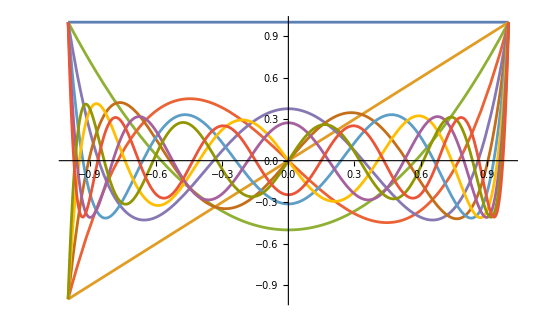

```mathematica
Plot[Table[Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]/.J[i_]->i,{i,0,10}]//Evaluate,{x,-1,1}]
```

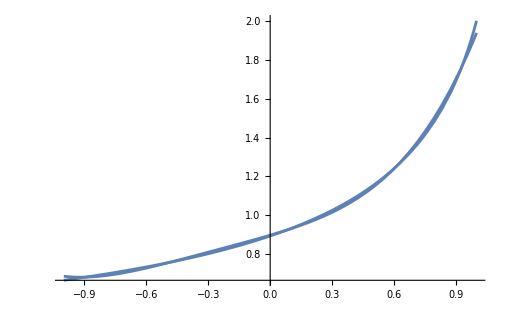

```mathematica
Plot[{1/(√(1+t^2-2 t x)),-%1037}/.t->1/2,{x,-1,1}]
```

```mathematica
crossingEqToy[4]==0/.t->1/2/.x->z/.zvalsTable[-9/10,9/10,4]/.J[i_]->i//N
```

{0.681994-1. C[0]+0.9 C[1]-0.715 C[2]+0.4725 C[3]-0.207938 C[4]==0.,0.766965-1. C[0]+0.45 C[1]+0.19625 C[2]-0.447188 C[3]+0.204973 C[4]==0.,0.894427-1. C[0]+0.5 C[2]-0.375 C[4]==0.,1.11803-1. C[0]-0.45 C[1]+0.19625 C[2]+0.447188 C[3]+0.204973 C[4]==0.,1.69031-1. C[0]-0.9 C[1]-0.715 C[2]-0.4725 C[3]-0.207938 C[4]==0.}

```mathematica
nstates=10
```

10

```mathematica
Table[1/C[i],{i,0,nstates}]/.Solve[crossingEqToy[nstates]==0/.t->1/2/.x->z/.zvalsTable[-9/10,9/10,nstates]/.J[i_]->i]//N
```

{{1.00014,2.00222,4.01107,8.07817,16.2878,33.7353,69.561,160.134,350.308,1162.5,2874.12}}

```mathematica
Table[(1/2)^n,{n,0,5}]//N
```

{1.,0.5,0.25,0.125,0.0625,0.03125}

```mathematica
Hypergeometric2F1[-J[i],1+J[i],1,(1-x)/2]-LegendreP[i,x]/.J[i_]->i/.i->11//Simplify
```

0

```mathematica
D[crossingEqToy[8],{Table[C[i],{i,0,8}],1}]/.x->z/.zvalsTable[1/10,1/2,8]
```

{{-1,-1/10,97/200,59/400,-5407/16000,-143063/800000,3981269/16000000,31918871/160000000,-461621047/2560000000},{-1,-3/20,373/800,693/3200,-74967/256000,-6459309/25600000,178837601/1024000000,5425621377/20480000000,-51318464167/655360000000},{-1,-1/5,11/25,7/25,-29/125,-961/3125,1259/15625,22931/78125,3091/78125},{-1,-1/4,13/32,43/128,-323/2048,-2783/8192,-1591/65536,73379/262144,1278877/8388608},{-1,-3/10,73/200,153/400,-1167/16000,-276309/800000,-2066899/16000000,35851677/160000000,612030953/2560000000},{-1,-7/20,253/800,1337/3200,4793/256000,-8254841/25600000,-227850919/1024000000,2698400453/20480000000,184262924153/655360000000},{-1,-2/5,13/50,11/25,113/1000,-3383/12500,-73159/250000,9119/625000,2669993/10000000},{-1,-9/20,157/800,1431/3200,52473/256000,-4908087/25600000,-336876871/1024000000,-2265110901/20480000000,127493053433/655360000000},{-1,-1/2,1/8,7/16,37/128,-23/256,-331/1024,-457/2048,2413/32768}}

```mathematica
crossingEqToy[8]/.C[i_]->t^i/.t->1/2/.x->7/10//N
```

0.000465039

```mathematica
crossingEqToy[5]/.C[i_]->0/.t->1/2/.x->z/.zvalsTable[1/10,1/2,8]
```

{2 √(5/23),√(10/11),2 √(5/21),1,2 √(5/19),(√10)/3,2 √(5/17),(√5)/2,2/(√3)}

```mathematica
Inverse[%823].%824//N
```

{-1.09658,-0.239774,-0.574464,0.187686,-0.283022,0.107034,-0.0730697,0.0169551,-0.00651646}

```mathematica
Table[(1/2)^J,{J,0,5}]//N
```

{1.,0.5,0.25,0.125,0.0625,0.03125}

```mathematica
%//Dimensions
```

{8,3}

```mathematica
FindInstance[N[Append[Table[%764[[i,;;2]].{n1,n2}>=0,{i,6}],n1*n2 !=0]/.x->1/2,30],{n1,n2}]
```

{}

```mathematica
FindInstance[N[Append[Table[%776[[i]].{n1,n2,n3}>=0,{i,9}],n1*n2 n3!=0]/.x->1/2,30],{n1,n2,n3}]
```

{}

```mathematica
Manipulate[ListPlot[Table[D[{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->2+x,blockvec/.Δ[0]->2+2x,blockvec/.Δ[0]->2+3x,blockvec/.Δ[0]->2+4x,blockvec/.Δ[0]->2+5x,blockvec/.Δ[0]->2+6x},{z,n}],{n,1,3,2}]/.z->1/2//Simplify//Transpose,PlotRange->Full],{x,0,2}]
```

```mathematica
Manipulate[ListPlot[{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->2+x,,blockvec/.Δ[0]->2+2x}/.{{z->4/10},{z->y}}//Simplify//Transpose//Evaluate],{x,0,2},{y,4/10,1/2}]
```

```mathematica
{zvec,blockvec/.Δ[0]->2,blockvec/.Δ[0]->3}/.{{z->4/10},{z->45/100}}//Simplify//Transpose
```

{{1/5,1/10},{4/25 (-15+54 Log[5/3]-14 Log[5/2]),-6/5+3751/600 Log[20/11]-(7047 Log[20/9])/2200},{-96+1269/5 Log[5/3]-184/5 Log[5/2],-503/11+56507/360 Log[20/11]-(291843 Log[20/9])/4840}}

```mathematica
zvec=1-2 z;
```

```mathematica
blockvec=D[crossingEq[2]/.Δσ->1//FullSimplify,C[0]]
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
vecszsamp[n_,zvals_]:=crossingEq[2]/.Δσ->1
```

```mathematica
Table[D[crossingEq[2]/.Δσ->1,{z,n}]/n!/.z->1/2//Simplify,{n,1,5,2}]
```

{2^(-Δ[0]) C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (-2+Δ[0])+1/4 (-8+2^(-Δ[0]) C[0] Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]+2^(2-Δ[1]) C[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] (-2+Δ[1])+2^(-Δ[1]) C[1] Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]+2^(2-Δ[2]) C[2] Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1/2] (-2+Δ[2])+2^(-Δ[2]) C[2] Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]),1/48 (1/(1+2 Δ[0])2^(-Δ[0]) C[0] Δ[0] (32 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (14+19 Δ[0]-17 Δ[0]^2+2 Δ[0]^3)+24 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] (2-Δ[0]-9 Δ[0]^2+2 Δ[0]^3)+(1+Δ[0]) (Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2] (2+Δ[0])^2+12 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] (-2-Δ[0]+Δ[0]^2)))+1/(1+2 Δ[1])2^(-Δ[1]) C[1] Δ[1] (32 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] (14+19 Δ[1]-17 Δ[1]^2+2 Δ[1]^3)+24 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] (2-Δ[1]-9 Δ[1]^2+2 Δ[1]^3)+(1+Δ[1]) (Hypergeometric2F1[3+Δ[1],3+Δ[1],3+2 Δ[1],1/2] (2+Δ[1])^2+12 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] (-2-Δ[1]+Δ[1]^2)))+1/(1+2 Δ[2])2^(-Δ[2]) C[2] Δ[2] (32 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1/2] (14+19 Δ[2]-17 Δ[2]^2+2 Δ[2]^3)+24 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] (2-Δ[2]-9 Δ[2]^2+2 Δ[2]^3)+(1+Δ[2]) (Hypergeometric2F1[3+Δ[2],3+Δ[2],3+2 Δ[2],1/2] (2+Δ[2])^2+12 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] (-2-Δ[2]+Δ[2]^2)))),1/1920(1/(3+8 Δ[0]+4 Δ[0]^2)2^(-Δ[0]) C[0] Δ[0] (-1440 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2]+288 Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2]-32640 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]+13440 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]-3120 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2] Δ[0]+768 Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2] Δ[0]-41920 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^2+27200 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]^2-1960 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2] Δ[0]^2+794 Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2] Δ[0]^2+63360 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^3+9280 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]^3+60 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2] Δ[0]^3+415 Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2] Δ[0]^3+25280 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^4-8640 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]^4+500 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2] Δ[0]^4+117 Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2] Δ[0]^4-15360 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^5-3520 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]^5+180 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2] Δ[0]^5+17 Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2] Δ[0]^5+1280 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]^6+640 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] Δ[0]^6+20 Hypergeometric2F1[4+Δ[0],4+Δ[0],4+2 Δ[0],1/2] Δ[0]^6+Hypergeometric2F1[5+Δ[0],5+Δ[0],5+2 Δ[0],1/2] Δ[0]^6+80 Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2] (2+Δ[0])^2 (6-5 Δ[0]-18 Δ[0]^2-5 Δ[0]^3+2 Δ[0]^4)+256 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (372+332 Δ[0]-919 Δ[0]^2-20 Δ[0]^3+303 Δ[0]^4-72 Δ[0]^5+4 Δ[0]^6))+1/(3+8 Δ[1]+4 Δ[1]^2)2^(-Δ[1]) C[1] Δ[1] (-1440 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2]+288 Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2]-32640 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]+13440 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] Δ[1]-3120 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2] Δ[1]+768 Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2] Δ[1]-41920 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]^2+27200 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] Δ[1]^2-1960 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2] Δ[1]^2+794 Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2] Δ[1]^2+63360 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]^3+9280 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] Δ[1]^3+60 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2] Δ[1]^3+415 Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2] Δ[1]^3+25280 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]^4-8640 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] Δ[1]^4+500 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2] Δ[1]^4+117 Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2] Δ[1]^4-15360 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]^5-3520 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] Δ[1]^5+180 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2] Δ[1]^5+17 Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2] Δ[1]^5+1280 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]^6+640 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] Δ[1]^6+20 Hypergeometric2F1[4+Δ[1],4+Δ[1],4+2 Δ[1],1/2] Δ[1]^6+Hypergeometric2F1[5+Δ[1],5+Δ[1],5+2 Δ[1],1/2] Δ[1]^6+80 Hypergeometric2F1[3+Δ[1],3+Δ[1],3+2 Δ[1],1/2] (2+Δ[1])^2 (6-5 Δ[1]-18 Δ[1]^2-5 Δ[1]^3+2 Δ[1]^4)+256 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] (372+332 Δ[1]-919 Δ[1]^2-20 Δ[1]^3+303 Δ[1]^4-72 Δ[1]^5+4 Δ[1]^6))+1/(3+8 Δ[2]+4 Δ[2]^2)2^(-Δ[2]) C[2] Δ[2] (-1440 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2]+288 Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2]-32640 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]+13440 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] Δ[2]-3120 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2] Δ[2]+768 Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2] Δ[2]-41920 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]^2+27200 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] Δ[2]^2-1960 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2] Δ[2]^2+794 Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2] Δ[2]^2+63360 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]^3+9280 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] Δ[2]^3+60 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2] Δ[2]^3+415 Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2] Δ[2]^3+25280 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]^4-8640 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] Δ[2]^4+500 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2] Δ[2]^4+117 Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2] Δ[2]^4-15360 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]^5-3520 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] Δ[2]^5+180 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2] Δ[2]^5+17 Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2] Δ[2]^5+1280 Hypergeometric2F1[1+Δ[2],1+Δ[2],1+2 Δ[2],1/2] Δ[2]^6+640 Hypergeometric2F1[2+Δ[2],2+Δ[2],2+2 Δ[2],1/2] Δ[2]^6+20 Hypergeometric2F1[4+Δ[2],4+Δ[2],4+2 Δ[2],1/2] Δ[2]^6+Hypergeometric2F1[5+Δ[2],5+Δ[2],5+2 Δ[2],1/2] Δ[2]^6+80 Hypergeometric2F1[3+Δ[2],3+Δ[2],3+2 Δ[2],1/2] (2+Δ[2])^2 (6-5 Δ[2]-18 Δ[2]^2-5 Δ[2]^3+2 Δ[2]^4)+256 Hypergeometric2F1[Δ[2],Δ[2],2 Δ[2],1/2] (372+332 Δ[2]-919 Δ[2]^2-20 Δ[2]^3+303 Δ[2]^4-72 Δ[2]^5+4 Δ[2]^6)))}

```mathematica
Table[C[i],{i,0,2}]-{2,37/150,1627/79380}g/.g->1/10/.genBos/.Δσ->1//N
```

{1.8,1.17533,0.236046}

```mathematica
Table[2i+g 1/(i (-1+2 i)),{i,15}]
```

{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190,22+g/231,24+g/276,26+g/325,28+g/378,30+g/435}

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190,22+g/231,24+g/276,26+g/325,28+g/378,30+g/435}/.g->1/10,40/100,49/100,1,60]
```

{{1.83424190584335373994223544117554839,7.354255471816165723673171610585×10^-6},{1.173452889713962904140054169919347155,7.206665978424996086498262678983×10^-6},{0.2363791806982433053301282670502652974,5.6951125111992112421828517084352×10^-6},{0.03241253180895872264065154258076331239,3.99857343726094264130178383679482×10^-6},{0.003703885755024651809891150989634568615,2.411147646638123490126358848041312×10^-6},{0.0003732437273037470218390463568666584197,1.198839750014375576878599752736957×10^-6},{0.00003366853100622320914352352143855827009,4.674935749823658497300337250891436×10^-7},{3.779054161623757679184200875269248945×10^-6,1.3318124805404892258785568716651063×10^-7},{5.93754104693030863895547087738375907×10^-8,2.45319935739093970017389523999650775×10^-8},{5.433164774549662470144374514266771532×10^-8,2.18524550122277625131023930515891968×10^-9}}

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190,22+g/231,24+g/276,26+g/325,28+g/378,30+g/435}/.g->0,40/100,49/100,1,60]
```

{{1.999960259797672592835614925621409765,7.143758084942621068823324407911×10^-6},{1.200034806689715044238547944333669509,6.2273644517699305070960649912872×10^-6},{0.2380674419822226005222384434519490929,4.8976362828058764065954797114211×10^-6},{0.03265415920337968875497450796011913298,3.43670343955555672640883820143422×10^-6},{0.003689383797894540888883895605273127828,2.07213490674438901524775062180382×10^-6},{0.0003811404972844182691073367945601706634,1.030193304104163326685661049380603×10^-6},{0.00003196480032917006393579211018630646052,4.0166761692025342388755224299881634×10^-7},{4.12402246399150829542312068490194799×10^-6,1.1440149446346108200437521827690866×10^-7},{1.403724453629921994972386832517740891×10^-8,2.106604082274773784691508260094899636×10^-8},{5.743058797997162423182191994007726221×10^-8,1.8757609916475664847255397605741466×10^-9}}

```mathematica
0.2363791806982433053301282670502652973714493486271668587499`37.7117282573455-0.2360456034265558
```

0.000333577

```mathematica
Rationalize[0.2363791806982433053301282670502652973714493486271668587499`37.7117282573455,10^-5]
```

178/753

```mathematica
FindSequenceFunction[D[{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190},g],i]
```

1/(i (-1+2 i))

```mathematica
FindSequenceFunction[{2,1/6,1/15,1/28},n]
```

```mathematica
crossingEq[4]/.Δ[i_]->{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}[[i+1]]/.C[i_]->%1235[[i+1,1]]/.Δσ->1/.g->1/10
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

(1-z)^2-z^2+1.83424190584335373994223544117554839 (-(1-z)^(21/10) z^2 Hypergeometric2F1[21/10,21/10,21/5,1-z]+(1-z)^2 z^(21/10) Hypergeometric2F1[21/10,21/10,21/5,z])+1.173452889713962904140054169919347155 (-(1-z)^(241/60) z^2 Hypergeometric2F1[241/60,241/60,241/30,1-z]+(1-z)^2 z^(241/60) Hypergeometric2F1[241/60,241/60,241/30,z])+0.2363791806982433053301282670502652974 (-(1-z)^(901/150) z^2 Hypergeometric2F1[901/150,901/150,901/75,1-z]+(1-z)^2 z^(901/150) Hypergeometric2F1[901/150,901/150,901/75,z])+0.03241253180895872264065154258076331239 (-(1-z)^(2241/280) z^2 Hypergeometric2F1[2241/280,2241/280,2241/140,1-z]+(1-z)^2 z^(2241/280) Hypergeometric2F1[2241/280,2241/280,2241/140,z])+0.003703885755024651809891150989634568615 (-(1-z)^(4501/450) z^2 Hypergeometric2F1[4501/450,4501/450,4501/225,1-z]+(1-z)^2 z^(4501/450) Hypergeometric2F1[4501/450,4501/450,4501/225,z])

```mathematica
crossingEq[4]/.Δ[i_]->{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}[[i+1]]/.Δσ->1
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

(1-z)^2-z^2+C[4] (-(1-z)^(10+g/45) z^2 Hypergeometric2F1[10+g/45,10+g/45,2 (10+g/45),1-z]+(1-z)^2 z^(10+g/45) Hypergeometric2F1[10+g/45,10+g/45,2 (10+g/45),z])+C[3] (-(1-z)^(8+g/28) z^2 Hypergeometric2F1[8+g/28,8+g/28,2 (8+g/28),1-z]+(1-z)^2 z^(8+g/28) Hypergeometric2F1[8+g/28,8+g/28,2 (8+g/28),z])+C[2] (-(1-z)^(6+g/15) z^2 Hypergeometric2F1[6+g/15,6+g/15,2 (6+g/15),1-z]+(1-z)^2 z^(6+g/15) Hypergeometric2F1[6+g/15,6+g/15,2 (6+g/15),z])+C[1] (-(1-z)^(4+g/6) z^2 Hypergeometric2F1[4+g/6,4+g/6,2 (4+g/6),1-z]+(1-z)^2 z^(4+g/6) Hypergeometric2F1[4+g/6,4+g/6,2 (4+g/6),z])+C[0] (-(1-z)^(2+g) z^2 Hypergeometric2F1[2+g,2+g,2 (2+g),1-z]+(1-z)^2 z^(2+g) Hypergeometric2F1[2+g,2+g,2 (2+g),z])

```mathematica
N[%1251==0/.zvalsTable[4/10,49/100,4],30]
```

```mathematica
Solve[N[%1251==0/.zvalsTable[4/10,49/100,4],30]]
```

```mathematica
%1250-(crossingEq[4]/.genBos/.Δσ->1)
```

C[4] (-(1-z)^(10+g/45) z^2 Hypergeometric2F1[10+g/45,10+g/45,2 (10+g/45),1-z]+(1-z)^2 z^(10+g/45) Hypergeometric2F1[10+g/45,10+g/45,2 (10+g/45),z])+C[3] (-(1-z)^(8+g/28) z^2 Hypergeometric2F1[8+g/28,8+g/28,2 (8+g/28),1-z]+(1-z)^2 z^(8+g/28) Hypergeometric2F1[8+g/28,8+g/28,2 (8+g/28),z])+C[2] (-(1-z)^(6+g/15) z^2 Hypergeometric2F1[6+g/15,6+g/15,2 (6+g/15),1-z]+(1-z)^2 z^(6+g/15) Hypergeometric2F1[6+g/15,6+g/15,2 (6+g/15),z])+C[1] (-(1-z)^(4+g/6) z^2 Hypergeometric2F1[4+g/6,4+g/6,2 (4+g/6),1-z]+(1-z)^2 z^(4+g/6) Hypergeometric2F1[4+g/6,4+g/6,2 (4+g/6),z])+C[0] (-(1-z)^(2+g) z^2 Hypergeometric2F1[2+g,2+g,2 (2+g),1-z]+(1-z)^2 z^(2+g) Hypergeometric2F1[2+g,2+g,2 (2+g),z])-2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)-6/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))-5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))-14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))-1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]))

```mathematica
crossingEq[4]/.Δ[i_]->{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}[[i+1]]/.C[i_]->%1247[[i+1,1]]/.Δσ->1/.g->0
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

(1-z)^2-z^2+1.999960259797672592835614925621409765 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)+1.200034806689715044238547944333669509 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+0.2380674419822226005222384434519490929 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))+0.03265415920337968875497450796011913298 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))+0.003689383797894540888883895605273127828 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]))

Plot::precw: The precision of the argument function ((1-z)^2-z^2+1.83424190584335373994223544117554839 (-(1-z)^(21/10) z^2 Hypergeometric2F1[21/10,21/10,21/5,1-z]+(1-z)^2 z^(21/10) Hypergeometric2F1[21/10,21/10,21/5,z])+«1»+«77» («1»+(«1»)^2 «1» «1»)+0.03241253180895872264065154258076331239 (-(1-z)^(2241/280) z^2 Hypergeometric2F1[2241/280,2241/280,2241/140,1-z]+(1-z)^2 z^(2241/280) Hypergeometric2F1[2241/280,2241/280,2241/140,z])+0.003703885755024651809891150989634568615 (-(1-z)^(4501/450) z^2 Hypergeometric2F1[4501/450,4501/450,4501/225,1-z]+(1-z)^2 z^(4501/450) Hypergeometric2F1[4501/450,4501/450,4501/225,z])) is less than WorkingPrecision (40.).

Plot::precw: The precision of the argument function (…) is less than WorkingPrecision (40.).

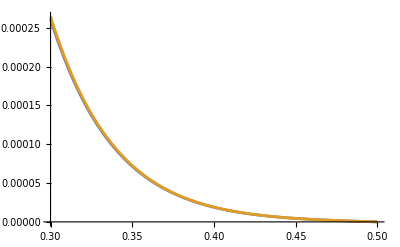

```mathematica
Plot[{%1238,%1248}//Evaluate,{z,3/10,1/2},WorkingPrecision->40]
```

```mathematica
crossingEq[5]/.genBos/.Δσ->1
```

(1-z)^2-z^2+(11 (-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/29393+2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3)+6/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7))+5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11))+14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))+1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]))

```mathematica
crossingEq[5]
```

```mathematica
%481[[;;5,2]]
```

{9.3644867326185731155899141253917×10^-6,7.0597972127258216063920648370265×10^-6,5.5188838329494501910014719193803×10^-6,3.86993090375525782086393865368316×10^-6,2.33350757895458026892976887746089×10^-6}

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->0,40/100,49/100,1,60][[;;5,2]]//Total
```

0.000023777597165818373724171457933858

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->0,40/100,49/100,1,60][[;;5,2]]//Total
```

0.000023777597165818373724171457933858

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->-10/100,40/100,49/100,1,60]
```

{{2.245981300083567167656583888787743607,9.3644867326185731155899141253917×10^-6},{1.223397190355343540315159117486409212,7.0597972127258216063920648370265×10^-6},{0.2404065124045842368635895391486926906,5.5188838329494501910014719193803×10^-6},{0.03273995752686164241247173274632681585,3.86993090375525782086393865368316×10^-6},{0.003720025787082125948477194792514263334,2.33350757895458026892976887746089×10^-6},{0.0003763956533293421128044952005111382221,1.160416102491264673879194139754294×10^-6},{0.00003337038386808992649007597052219086342,4.5257722196086777996173970501453403×10^-7},{3.864569853811139108082613342494713432×10^-6,1.2894548340063703770416620317168062×10^-7},{4.926346047320292184733146477199069935×10^-8,2.37532184843948587347255286234225968×10^-8},{5.509628368383702567639365031357836948×10^-8,2.1159193420094716141764930045977197×10^-9}}

```mathematica
getAvCs[10,{2+g,4+g/6,6+g/15,8+g/28,10+g/45,12+g/66,14+g/91,16+g/120,18+g/153,20+g/190}/.g->10/100,40/100,49/100,1,60]
```

{{1.83424190584335373994223544117554839,7.354255471816165723673171610585×10^-6},{1.173452889713962904140054169919347155,7.206665978424996086498262678983×10^-6},{0.2363791806982433053301282670502652974,5.6951125111992112421828517084352×10^-6},{0.03241253180895872264065154258076331239,3.99857343726094264130178383679482×10^-6},{0.003703885755024651809891150989634568615,2.411147646638123490126358848041312×10^-6},{0.0003732437273037470218390463568666584197,1.198839750014375576878599752736957×10^-6},{0.00003366853100622320914352352143855827009,4.674935749823658497300337250891436×10^-7},{3.779054161623757679184200875269248945×10^-6,1.3318124805404892258785568716651063×10^-7},{5.937541046930308638955470877383759067×10^-8,2.45319935739093970017389523999650775×10^-8},{5.433164774549662470144374514266771532×10^-8,2.18524550122277625131023930515891968×10^-9}}

```mathematica
crossingTable[0][[1]]
```

-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
Series[%479,{z,0,4}]
```

z^Δ[0] (1+(-2 Δσ+Δ[0]/2) z+(-Δσ+2 Δσ^2-Δσ Δ[0]+(Δ[0] (1+Δ[0])^2)/(4 (1+2 Δ[0]))) z^2+(-2/3 (Δσ-3 Δσ^2+2 Δσ^3)+1/2 (-Δσ+2 Δσ^2) Δ[0]-(Δσ Δ[0] (1+Δ[0])^2)/(2 (1+2 Δ[0]))+(Δ[0] (1+Δ[0]) (2+Δ[0])^2)/(24 (1+2 Δ[0]))) z^3+(1/6 (-3 Δσ+11 Δσ^2-12 Δσ^3+4 Δσ^4)-1/3 (Δσ-3 Δσ^2+2 Δσ^3) Δ[0]+((-Δσ+2 Δσ^2) Δ[0] (1+Δ[0])^2)/(4 (1+2 Δ[0]))-(Δσ Δ[0] (1+Δ[0]) (2+Δ[0])^2)/(12 (1+2 Δ[0]))+(Δ[0] (1+Δ[0]) (2+Δ[0])^2 (3+Δ[0])^2)/(96 (1+2 Δ[0]) (3+2 Δ[0]))) z^4+O[z]^5)+z^(2 Δσ) ((Gamma[2 Δ[0]] (2 EulerGamma+Log[z]+2 PolyGamma[0,Δ[0]]))/Gamma[Δ[0]]^2+1/Gamma[Δ[0]]^2(-2 EulerGamma Gamma[2 Δ[0]] Δ[0]-Gamma[2 Δ[0]] Log[z] Δ[0]-2 Gamma[2 Δ[0]] PolyGamma[0,Δ[0]] Δ[0]-2 Gamma[2 Δ[0]] Δ[0]^2+2 EulerGamma Gamma[2 Δ[0]] Δ[0]^2+Gamma[2 Δ[0]] Log[z] Δ[0]^2+2 Gamma[2 Δ[0]] PolyGamma[0,1+Δ[0]] Δ[0]^2) z+1/(4 Gamma[Δ[0]]^2)Gamma[2 Δ[0]] (-4 EulerGamma Δ[0]-2 Log[z] Δ[0]-4 PolyGamma[0,Δ[0]] Δ[0]-3 Δ[0]^2+6 EulerGamma Δ[0]^2+3 Log[z] Δ[0]^2+4 PolyGamma[0,Δ[0]] Δ[0]^2+2 PolyGamma[0,2+Δ[0]] Δ[0]^2+2 Δ[0]^3-4 EulerGamma Δ[0]^3-2 Log[z] Δ[0]^3-8 PolyGamma[0,1+Δ[0]] Δ[0]^3+4 PolyGamma[0,2+Δ[0]] Δ[0]^3-3 Δ[0]^4+2 EulerGamma Δ[0]^4+Log[z] Δ[0]^4+2 PolyGamma[0,2+Δ[0]] Δ[0]^4) z^2+1/(108 Gamma[Δ[0]]^2)Gamma[2 Δ[0]] (-72 EulerGamma Δ[0]-36 Log[z] Δ[0]-72 PolyGamma[0,Δ[0]] Δ[0]-44 Δ[0]^2+132 EulerGamma Δ[0]^2+66 Log[z] Δ[0]^2+108 PolyGamma[0,Δ[0]] Δ[0]^2+24 PolyGamma[0,3+Δ[0]] Δ[0]^2+57 Δ[0]^3-126 EulerGamma Δ[0]^3-63 Log[z] Δ[0]^3-36 PolyGamma[0,Δ[0]] Δ[0]^3-108 PolyGamma[0,1+Δ[0]] Δ[0]^3-54 PolyGamma[0,2+Δ[0]] Δ[0]^3+72 PolyGamma[0,3+Δ[0]] Δ[0]^3-89 Δ[0]^4+78 EulerGamma Δ[0]^4+39 Log[z] Δ[0]^4+108 PolyGamma[0,1+Δ[0]] Δ[0]^4-108 PolyGamma[0,2+Δ[0]] Δ[0]^4+78 PolyGamma[0,3+Δ[0]] Δ[0]^4+15 Δ[0]^5-18 EulerGamma Δ[0]^5-9 Log[z] Δ[0]^5-54 PolyGamma[0,2+Δ[0]] Δ[0]^5+36 PolyGamma[0,3+Δ[0]] Δ[0]^5-11 Δ[0]^6+6 EulerGamma Δ[0]^6+3 Log[z] Δ[0]^6+6 PolyGamma[0,3+Δ[0]] Δ[0]^6) z^3+1/(3456 Gamma[Δ[0]]^2)Gamma[2 Δ[0]] (-1728 EulerGamma Δ[0]-864 Log[z] Δ[0]-1728 PolyGamma[0,Δ[0]] Δ[0]-900 Δ[0]^2+3600 EulerGamma Δ[0]^2+1800 Log[z] Δ[0]^2+3168 PolyGamma[0,Δ[0]] Δ[0]^2+432 PolyGamma[0,4+Δ[0]] Δ[0]^2+1708 Δ[0]^3-4080 EulerGamma Δ[0]^3-2040 Log[z] Δ[0]^3-1728 PolyGamma[0,Δ[0]] Δ[0]^3-2304 PolyGamma[0,1+Δ[0]] Δ[0]^3-864 PolyGamma[0,2+Δ[0]] Δ[0]^3-768 PolyGamma[0,3+Δ[0]] Δ[0]^3+1584 PolyGamma[0,4+Δ[0]] Δ[0]^3-2761 Δ[0]^4+2892 EulerGamma Δ[0]^4+1446 Log[z] Δ[0]^4+288 PolyGamma[0,Δ[0]] Δ[0]^4+3456 PolyGamma[0,1+Δ[0]] Δ[0]^4-864 PolyGamma[0,2+Δ[0]] Δ[0]^4-2304 PolyGamma[0,3+Δ[0]] Δ[0]^4+2316 PolyGamma[0,4+Δ[0]] Δ[0]^4+832 Δ[0]^5-1056 EulerGamma Δ[0]^5-528 Log[z] Δ[0]^5-1152 PolyGamma[0,1+Δ[0]] Δ[0]^5+864 PolyGamma[0,2+Δ[0]] Δ[0]^5-2496 PolyGamma[0,3+Δ[0]] Δ[0]^5+1728 PolyGamma[0,4+Δ[0]] Δ[0]^5-634 Δ[0]^6+408 EulerGamma Δ[0]^6+204 Log[z] Δ[0]^6+864 PolyGamma[0,2+Δ[0]] Δ[0]^6-1152 PolyGamma[0,3+Δ[0]] Δ[0]^6+696 PolyGamma[0,4+Δ[0]] Δ[0]^6+52 Δ[0]^7-48 EulerGamma Δ[0]^7-24 Log[z] Δ[0]^7-192 PolyGamma[0,3+Δ[0]] Δ[0]^7+144 PolyGamma[0,4+Δ[0]] Δ[0]^7-25 Δ[0]^8+12 EulerGamma Δ[0]^8+6 Log[z] Δ[0]^8+12 PolyGamma[0,4+Δ[0]] Δ[0]^8) z^4+O[z]^5)

```mathematica
crossingTable[10]/.genBos/.Δσ->1//Simplify;
```

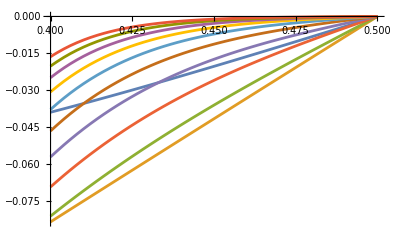

```mathematica
Plot[%470,{z,4/10,1/2},WorkingPrecision->30]
```

```mathematica
{-2g,-37/150g,-1627/79380g}/.g->5/100//N
```

{-0.1,-0.0123333,-0.00102482}

```mathematica
%-%305
```

{{-0.09085611231619662940089567,-1.8734137582596049773×10^-7},{-0.01277895187136688186183466,2.215581815578210831×10^-7},{-0.0009389388019600507608894777,1.8745724912466007042×10^-7},{-0.000097569518482753503661764,1.32624645618459302339×10^-7},{5.351332019851969852117×10^-7,8.00258402745460898832×10^-8},{-2.066054985309827169631686×10^-6,3.9786213363065506415704×10^-8},{3.888924225672045171540524×10^-7,1.5519599099047965553187×10^-8},{-8.248249434645224777186173×10^-8,4.42527409505339529996468×10^-9},{1.0672767559484087965523916×10^-8,8.163633310071421659324353×10^-10},{-7.404530431741898163021513×10^-10,7.28698725780093793295761×10^-11}}

```mathematica
(%305[[;;3,1]]-{2,6/5,5/21})/0.0001
```

{-0.397402,0.348067,-0.277961}

```mathematica
Total[%358[[;;,2]]]
```

0.00002584174624363092492791

```mathematica
Total[%382[[;;,2]]]
```

0.00008161448414182037084876139722329651

```mathematica
Total[%381[[;;,2]]]
```

0.00017967587900189399560798962279980244

```mathematica
Total[%[[;;,2]]]/%384
```

0.4012862994531515156050572184553264

```mathematica
%433[[;;,2]]/%358[[;;,2]]
```

{1.45951729046654841646,1.414820904727256012123,1.407802751230831608824,1.40109926886451730735,1.43958256817907805216524,1.45885219649495187441735,1.476503373696703697837132,1.513789434909885211972791,1.43043164365622640595133241,1.385518144539653730470028}

```mathematica
%358[[;;,2]]/%403[[;;,2]]
```

{0.973775515128258261752,1.035578162041704530192,1.038275045001354209318,1.0385906575737622157242,1.0386199952590334818883,1.03862014362213589361375,1.038637914647048101351954,1.038681960544377261471927,1.03875257519322799111563588,1.038848165039408589373404}

```mathematica
%[[;;,2]]/%403[[;;,2]]
```

{2.23968106127835022870664899826,2.52260924404493208196964729279,2.436302181363729562242986096332,2.180547241177427823310318210088,2.1345286463069089424792241276513,2.30191003690733686142860301515398,2.34046744791806886277558225566979,2.397092238009194365787218214127777,2.270356256589960758120090148334225,2.514439861401243173066440814786675}

```mathematica
%[[;;,2]]/%403[[;;,2]]
```

{4.14996309665839322738279618632,4.554442176788279812338013757925,4.648900036309965456340775117211,4.388594584723034871006695660803,4.1959243147907518420116189623231,4.1438752885175564678898800796649,4.255743170824355882237249366267206,4.654558722949734053627579323097167,4.824810352962353974281239738780224,4.841000359463269532921730878277899}

```mathematica
%[[;;,2]]/%403[[;;,2]]
```

{1.605949964502566237154116025274,1.273868329196374300651306255349,1.2621778338319920131258947114008,1.26077699526082671282488993300238,1.26092864145002508453013594246341,1.261438546616871295464986995103826,1.2620944257513424531147448650105486,1.2628529693311355878327324636774824,1.26370798158507945038676773250603414,1.2646605543077755407032768433439945}

```mathematica
%438[[;;,2]]/%403[[;;,2]]
```

{1.029465917570364559413293003021,1.15725778284531431785174989188,1.1628287978821606886037509724969,1.16349097546166170777590831924866,1.16360553494384709324165809654858,1.163703690597041901555235354982225,1.163881665559266201831844991538612,1.1641565407747880685710437628682006,1.16452796139173053441524795751014395,1.1649914413154393394260859249357067}

```mathematica
317/144-5/3 Zeta[3]//N
```

0.197961

```mathematica
25127/10800-28/15Zeta[3]//N
```

0.0827345

```mathematica
zvalsTable[4/10,49/100,9]
```

{{z→2/5},{z→41/100},{z→21/50},{z→43/100},{z→11/25},{z→9/20},{z→23/50},{z→47/100},{z→12/25},{z→49/100}}

```mathematica
N[D[crossingEq[10],{Table[C[i],{i,0,9}],1}]/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1,60]
```

{{-0.0389578500599478431154591622967056827013494513030700735164893,-0.0835480818703817529966153802171864118319078508248271322060901,-0.0811997256233707836363595147007944329195018256327108987889009,-0.0693416411664221000974705700001073423485802041187269316061447,-0.0571483387692583286831714360977300748140320257547696671305143,-0.046590484492043721836242809862214203717309789193197327407822,-0.0378529203241500127038288979038240972520075460832904135416012,-0.0307200046308282255958988425341395526730486216276315165172455,-0.0249221225972932310202873535393966774936225685259921395907422,-0.020215962691114713296966013166213046430387514964351753626095},{-0.0354299345718949404537525535861068689100339184746440553110689,-0.0751270841309936861352847561365882618337508236286968950563516,-0.0709904908365548901029250526849990064899646830602980319099439,-0.0582565111540006138123690859197052533972716559353942708221537,-0.045826632626466119992877835862084771698414539643164796856779,-0.035536778146654672432277966400052744280013299265151671978927,-0.0274189694841467948560300028449178833418533304594083356348514,-0.0211174329978193302056363957780963592098814965755953795156159,-0.0162535077631192176147709085858686765859846868025307794072773,-0.0125068557116438685444484295179284898185873024236263270103737},{-0.0317863263745657732331023272543182080089302055077841546180879,-0.0667208752664682984106207928272582500978728994233479064477563,-0.0614490878681382420534827022953090096259796064921468619849696,-0.0485817464976600078545908002770325040314542779212963381111561,-0.0365468230557657294276464392793670742650264485539680761134838,-0.0269888980604375231048561031875725580198792676427876904424729,-0.0197868979274142074082474560408754609859025859025098249059522,-0.014464962123234509071065572005132797262493803357851420505196,-0.0105621447587629195227257235726837592678237102404011194230683,-0.00770870956347919306865569003727711735450608311335152395661009},{-0.0280396120134986634679040163295313565313580046292484947020094,-0.058331239360723265742059131466900777501664536748821720499121,-0.0524969874098053594946271247374143138185012568164290511786042,-0.0401043637993783224337085635223960652471676997682060834291322,-0.0289243821229506664240391427880874650836859788157667965137604,-0.0203770070196170141198440227657351085929108468915241454126827,-0.0142104753993965881043304249926377960925768445607118053059446,-0.00986558856767225099109310358701891794383118675362081248514115,-0.00683535376183787019253921324699069057155006922435244390462651,-0.0047315462920643371092246640792795383066764282285076149273153},{-0.0242024755317898363428841703794928436671374199579505737953818,-0.0499587250973810892351689106641124414606475047285752121245572,-0.0440570569943585335577600839215474366142144259813216584112583,-0.0326320498345748811288484152960394904280926761885424781441914,-0.0226362279004675275690112246515346670544005487550961860849714,-0.0152520965032648489240113725164763204097348514877493856239166,-0.0101355737980128863127064901646717974528172789978671578731073,-0.00668987927283899105745819146490263501040055215810132212292731,-0.00440065508531789339262101590135132025158453617277284999655311,-0.00288985783404361140286002799246559621376858391521288096113166},{-0.0202876844791294331893025016474314832462160727137923875376269,-0.0416028164360849587395454686956264735182005512190151294421306,-0.0360534704458383493369453714563369122597422900364403091988457,-0.0259900712927394883592145304135338579913438128352990289038324,-0.0174093008631066573017646879655970720657540908879734254113566,-0.011259014090788418618274120945182062788105719074529492466354,-0.00715000544805181934228309676221695084967602036194352335091659,-0.00449610834197296010600517374215281208429902066481746234740714,-0.00281193906108503861103450326375594968795263553618215284038271,-0.0017532953476660294125625519104887477046230728870486659130954},{-0.0163080766702256064521295568870834248287343312510699397074249,-0.0332620966511895495374425382518934666128998882780403310866496,-0.0284115809954973604551184916391253990870711510740849705307508,-0.0200183883686896863526854569028416663731481413601394492698718,-0.0130107459926305974350533960307579660051020736029496020332728,-0.00811484297449268653394444216783226704083155826084149124066186,-0.0049457719312422125437470990342667458682357975488723610824918,-0.00297359861424694700489883610810571392530885829196318088348817,-0.00177315910964664535919071206175393272590327541948271976648714,-0.00105196339973535388635895752430441785797484728545891308133999},{-0.0122765475652533289797938009604053386998370109792140820337661,-0.0249344067795532004212198569357885564294974786455495492824811,-0.0210577652390405601058726772880398441172144529721214617330183,-0.0145689423538572172031210511964039411440901830473759181475997,-0.00923939200715493583785138441420106301554947477238204655529425,-0.00559141958348042450042228343275441860066109146082536362492812,-0.00329047278357722322414862854728367807845549952645770238138614,-0.00190236847540187679401303444069862301253924279272273046157105,-0.00108707982197074696693109638123414646696940895037977349170999,-0.000616322079447378951149812878760939132240314610705026370291295},{-0.00820603815476575165692660396305813969410936606041474421827015,-0.016616999478106881834612111478077031846285764651798146563358,-0.0139192441425775185002086480826483144505117944279507683854009,-0.00950308752846981630505261324709958813117270858405427813947799,-0.00591825746932626756699439279102645836654278609955816266009819,-0.0035010020239861986648317339218607297380099578060367793945171,-0.00200539823929567603540725490720551197754061631408852014027854,-0.00112414073262855403159759918769014397516477218167988997568431,-0.000620652858727007306865979167485493077393429038333765103093942,-0.000338922337932526751048190453945605884365913408475873258661125},{-0.00410952323930961669969088186037533939802082872625446397170434,-0.00830668925398267831185252388459798184300991279967346885040457,-0.00692388654221962988142029558869366358118353646703810037419917,-0.00468913794254926790416428188176569116215866002662716881735851,-0.00288784397304516015581269122607489427450546806100899440350874,-0.00168427442962643561463330922928678574397499339652359452040258,-0.00094839530788911881674879516430776935878526354436810617438398,-0.000521134866917307966616380729542676613938433615416855626604936,-0.000281281497658254177607365011794559136683416426295658030569004,-0.000149772404885329987527598628995127384845209131711019280523578}}

```mathematica
%331//Det
```

-2.10627288264636963434394015042199183833053304157190642734922×10^-82

```mathematica
Inverse[%331].%331
```

{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}}

```mathematica
crossingEq[10]/.C[i_]->0/.zvalsTable[4/10,49/100,9]/.genBos/.Δσ->1
```

{1/5,9/50,4/25,7/50,3/25,1/10,2/25,3/50,1/25,1/50}

```mathematica
Series[Inverse[%334+ϵ*IdentityMatrix[10]],{ϵ,0,0}]
```

{{0.00022677/ϵ-1.0008×10^13+O[ϵ]^1,-0.00423875/ϵ+1.38964×10^14+O[ϵ]^1,0.0370179/ϵ-8.35806×10^14+O[ϵ]^1,-0.200179/ϵ+2.70902×10^15+O[ϵ]^1,0.748115/ϵ-4.2364×10^15+O[ϵ]^1,-2.03852/ϵ-2.0773×10^15+O[ϵ]^1,4.1496/ϵ+2.69777×10^16+O[ϵ]^1,-6.31025/ϵ-6.7992×10^16+O[ϵ]^1,6.90325/ϵ+9.54895×10^16+O[ϵ]^1,-4.62922/ϵ-7.25363×10^16+O[ϵ]^1},{-0.00019773/ϵ+8.5086×10^12+O[ϵ]^1,0.0036958/ϵ-1.18127×10^14+O[ϵ]^1,-0.0322762/ϵ+7.10397×10^14+O[ϵ]^1,0.174538/ϵ-2.30228×10^15+O[ϵ]^1,-0.652287/ϵ+3.5998×10^15+O[ϵ]^1,1.7774/ϵ+1.7665×10^15+O[ϵ]^1,-3.61806/ϵ-2.29261×10^16+O[ϵ]^1,5.50195/ϵ+5.77756×10^16+O[ϵ]^1,-6.01899/ϵ-8.11376×10^16+O[ϵ]^1,4.03625/ϵ+6.16326×10^16+O[ϵ]^1},{0.00015561/ϵ-6.1502×10^12+O[ϵ]^1,-0.00290859/ϵ+8.53509×10^13+O[ϵ]^1,0.0254013/ϵ-5.131×10^14+O[ϵ]^1,-0.137361/ϵ+1.66226×10^15+O[ϵ]^1,0.513349/ϵ-2.5978×10^15+O[ϵ]^1,-1.39881/ϵ-1.2779×10^15+O[ϵ]^1,2.84741/ϵ+1.65503×10^16+O[ϵ]^1,-4.33003/ϵ-4.16962×10^16+O[ϵ]^1,4.73694/ϵ+5.85474×10^16+O[ϵ]^1,-3.17652/ϵ-4.44693×10^16+O[ϵ]^1},{-0.00010934/ϵ+3.5538×10^12+O[ϵ]^1,0.0020437/ϵ-4.92788×10^13+O[ϵ]^1,-0.0178476/ϵ+2.96014×10^14+O[ϵ]^1,0.0965135/ϵ-9.5822×10^14+O[ϵ]^1,-0.360693/ϵ+1.4959×10^15+O[ϵ]^1,0.982845/ϵ+7.3969×10^14+O[ϵ]^1,-2.00067/ϵ-9.53753×10^15+O[ϵ]^1,3.0424/ϵ+2.40138×10^16+O[ϵ]^1,-3.3283/ϵ-3.37079×10^16+O[ϵ]^1,2.23191/ϵ+2.55981×10^16+O[ϵ]^1},{0.00006606/ϵ-1.3964×10^12+O[ϵ]^1,-0.0012347/ϵ+1.933×10^13+O[ϵ]^1,0.010783/ϵ-1.1592×10^14+O[ϵ]^1,-0.0583108/ϵ+3.7465×10^14+O[ϵ]^1,0.217921/ϵ-5.8359×10^14+O[ϵ]^1,-0.593807/ϵ-2.916×10^14+O[ϵ]^1,1.20875/ϵ+3.7265×10^15+O[ϵ]^1,-1.83813/ϵ-9.37106×10^15+O[ϵ]^1,2.01087/ϵ+1.31454×10^16+O[ϵ]^1,-1.34846/ϵ-9.97912×10^15+O[ϵ]^1},{-0.00003293/ϵ+1.582×10^11+O[ϵ]^1,0.00061555/ϵ-2.1698×10^12+O[ϵ]^1,-0.0053757/ϵ+1.2897×10^13+O[ϵ]^1,0.02907/ϵ-4.1309×10^13+O[ϵ]^1,-0.108641/ϵ+6.356×10^13+O[ϵ]^1,0.296034/ϵ+3.364×10^13+O[ϵ]^1,-0.602603/ϵ-4.0941×10^14+O[ϵ]^1,0.916373/ϵ+1.0224×10^15+O[ϵ]^1,-1.00249/ϵ-1.4289×10^15+O[ϵ]^1,0.672254/ϵ+1.0826×10^15+O[ϵ]^1},{0.0000129/ϵ+2.187×10^11+O[ϵ]^1,-0.0002408/ϵ-3.0342×10^12+O[ϵ]^1,0.002103/ϵ+1.8239×10^13+O[ϵ]^1,-0.011372/ϵ-5.9078×10^13+O[ϵ]^1,0.0425014/ϵ+9.2306×10^13+O[ϵ]^1,-0.115811/ϵ+4.546×10^13+O[ϵ]^1,0.235744/ϵ-5.8817×10^14+O[ϵ]^1,-0.358494/ϵ+1.4816×10^15+O[ϵ]^1,0.392183/ϵ-2.0802×10^15+O[ϵ]^1,-0.262992/ϵ+1.5799×10^15+O[ϵ]^1},{-(3.7×10^-6)/ϵ-1.64×10^11+O[ϵ]^1,0.0000688/ϵ+2.269×10^12+O[ϵ]^1,-0.0006013/ϵ-1.359×10^13+O[ϵ]^1,0.0032514/ϵ+4.3862×10^13+O[ϵ]^1,-0.012151/ϵ-6.8201×10^13+O[ϵ]^1,0.03311/ϵ-3.4377×10^13+O[ϵ]^1,-0.0673989/ϵ+4.3605×10^14+O[ϵ]^1,0.102493/ϵ-1.0954×10^15+O[ϵ]^1,-0.11212/ϵ+1.5358×10^15+O[ϵ]^1,0.075189/ϵ-1.1655×10^15+O[ϵ]^1},{(7.×10^-7)/ϵ+5.33×10^10+O[ϵ]^1,-0.0000127/ϵ-7.348×10^11+O[ϵ]^1,0.000111/ϵ+4.389×10^12+O[ϵ]^1,-0.0006011/ϵ-1.4126×10^13+O[ϵ]^1,0.002246/ϵ+2.1884×10^13+O[ϵ]^1,-0.0061212/ϵ+1.122×10^13+O[ϵ]^1,0.01246/ϵ-1.4028×10^14+O[ϵ]^1,-0.018948/ϵ+3.5169×10^14+O[ϵ]^1,0.020729/ϵ-4.9255×10^14+O[ϵ]^1,-0.0139/ϵ+3.7358×10^14+O[ϵ]^1},{-(6.×10^-8)/ϵ-7.2×10^9+O[ϵ]^1,(1.×10^-6)/ϵ+9.91×10^10+O[ϵ]^1,-(9.9×10^-6)/ϵ-5.9×10^11+O[ϵ]^1,0.0000537/ϵ+1.893×10^12+O[ϵ]^1,-0.000201/ϵ-2.922×10^12+O[ϵ]^1,0.0005471/ϵ-1.52×10^12+O[ϵ]^1,-0.001114/ϵ+1.878×10^13+O[ϵ]^1,0.001694/ϵ-4.6984×10^13+O[ϵ]^1,-0.001853/ϵ+6.5728×10^13+O[ϵ]^1,0.00124/ϵ-4.982×10^13+O[ϵ]^1}}

```mathematica
Fit[Table[Log[C[i]],{i,90,100}]/.genBos/.Δσ->1,{1,Δ[0]},Δ[0]]
```

-233.903-2.74646 Δ[0]

```mathematica
Inverse[%334+ϵ*IdentityMatrix[10]]//Expand
```

```mathematica
-Normal[Series[Inverse[%334+ϵ*IdentityMatrix[10]],{ϵ,0,0}]]
```

{{1.0008×10^13-0.00022677/ϵ,-1.38964×10^14+0.00423875/ϵ,8.35806×10^14-0.0370179/ϵ,-2.70902×10^15+0.200179/ϵ,4.2364×10^15-0.748115/ϵ,2.0773×10^15+2.03852/ϵ,-2.69777×10^16-4.1496/ϵ,6.7992×10^16+6.31025/ϵ,-9.54895×10^16-6.90325/ϵ,7.25363×10^16+4.62922/ϵ},{-8.5086×10^12+0.00019773/ϵ,1.18127×10^14-0.0036958/ϵ,-7.10397×10^14+0.0322762/ϵ,2.30228×10^15-0.174538/ϵ,-3.5998×10^15+0.652287/ϵ,-1.7665×10^15-1.7774/ϵ,2.29261×10^16+3.61806/ϵ,-5.77756×10^16-5.50195/ϵ,8.11376×10^16+6.01899/ϵ,-6.16326×10^16-4.03625/ϵ},{6.1502×10^12-0.00015561/ϵ,-8.53509×10^13+0.00290859/ϵ,5.131×10^14-0.0254013/ϵ,-1.66226×10^15+0.137361/ϵ,2.5978×10^15-0.513349/ϵ,1.2779×10^15+1.39881/ϵ,-1.65503×10^16-2.84741/ϵ,4.16962×10^16+4.33003/ϵ,-5.85474×10^16-4.73694/ϵ,4.44693×10^16+3.17652/ϵ},{-3.5538×10^12+0.00010934/ϵ,4.92788×10^13-0.0020437/ϵ,-2.96014×10^14+0.0178476/ϵ,9.5822×10^14-0.0965135/ϵ,-1.4959×10^15+0.360693/ϵ,-7.3969×10^14-0.982845/ϵ,9.53753×10^15+2.00067/ϵ,-2.40138×10^16-3.0424/ϵ,3.37079×10^16+3.3283/ϵ,-2.55981×10^16-2.23191/ϵ},{1.3964×10^12-0.00006606/ϵ,-1.933×10^13+0.0012347/ϵ,1.1592×10^14-0.010783/ϵ,-3.7465×10^14+0.0583108/ϵ,5.8359×10^14-0.217921/ϵ,2.916×10^14+0.593807/ϵ,-3.7265×10^15-1.20875/ϵ,9.37106×10^15+1.83813/ϵ,-1.31454×10^16-2.01087/ϵ,9.97912×10^15+1.34846/ϵ},{-1.582×10^11+0.00003293/ϵ,2.1698×10^12-0.00061555/ϵ,-1.2897×10^13+0.0053757/ϵ,4.1309×10^13-0.02907/ϵ,-6.356×10^13+0.108641/ϵ,-3.364×10^13-0.296034/ϵ,4.0941×10^14+0.602603/ϵ,-1.0224×10^15-0.916373/ϵ,1.4289×10^15+1.00249/ϵ,-1.0826×10^15-0.672254/ϵ},{-2.187×10^11-0.0000129/ϵ,3.0342×10^12+0.0002408/ϵ,-1.8239×10^13-0.002103/ϵ,5.9078×10^13+0.011372/ϵ,-9.2306×10^13-0.0425014/ϵ,-4.546×10^13+0.115811/ϵ,5.8817×10^14-0.235744/ϵ,-1.4816×10^15+0.358494/ϵ,2.0802×10^15-0.392183/ϵ,-1.5799×10^15+0.262992/ϵ},{1.64×10^11+(3.7×10^-6)/ϵ,-2.269×10^12-0.0000688/ϵ,1.359×10^13+0.0006013/ϵ,-4.3862×10^13-0.0032514/ϵ,6.8201×10^13+0.012151/ϵ,3.4377×10^13-0.03311/ϵ,-4.3605×10^14+0.0673989/ϵ,1.0954×10^15-0.102493/ϵ,-1.5358×10^15+0.11212/ϵ,1.1655×10^15-0.075189/ϵ},{-5.33×10^10-(7.×10^-7)/ϵ,7.348×10^11+0.0000127/ϵ,-4.389×10^12-0.000111/ϵ,1.4126×10^13+0.0006011/ϵ,-2.1884×10^13-0.002246/ϵ,-1.122×10^13+0.0061212/ϵ,1.4028×10^14-0.01246/ϵ,-3.5169×10^14+0.018948/ϵ,4.9255×10^14-0.020729/ϵ,-3.7358×10^14+0.0139/ϵ},{7.2×10^9+(6.×10^-8)/ϵ,-9.91×10^10-(1.×10^-6)/ϵ,5.9×10^11+(9.9×10^-6)/ϵ,-1.893×10^12-0.0000537/ϵ,2.922×10^12+0.000201/ϵ,1.52×10^12-0.0005471/ϵ,-1.878×10^13+0.001114/ϵ,4.6984×10^13-0.001694/ϵ,-6.5728×10^13+0.001853/ϵ,4.982×10^13-0.00124/ϵ}}

```mathematica
%333[[1]].%333[[2]].Transpose[%333[[3]]]
```

{{-0.038957850059947843115459304667217978841096179693510387427227,-0.083548081870381752996615256083327583967252677701487159327177,-0.081199725623370783636359612393988367408827420657967460847322,-0.069341641166422100097470501358217820019118594765608839565182,-0.057148338769258328683171477569237244640858203960928791367343,-0.046590484492043721836242789187202560058062777503363226591308,-0.037852920324150012703828905992085767506925957045085102751633,-0.030720004630828225595898840221717914737169105190993588548425,-0.024922122597293231020287353966899683459212458616362923430449,-0.020215962691114713296966013128001837025305927285064938626239},{-0.035429934571894940453749892457591524387264935708981265929415,-0.075127084130993686135287076393403517662749984981955584077743,-0.070990490836554890102923226645744519652735009469127376133583,-0.058256511154000613812370368944445482221705061544023224682134,-0.045826632626466119992877060694470888403168742111498033528794,-0.035536778146654672432278352848497388343026193308315697213287,-0.027418969484146794856029851662601944825117101692720588496683,-0.02111743299781933020563643900088920419782185421696453809093,-0.01625350776311921761477090059516595856691760932447255755489,-0.012506855711643868544448430232156017090191632346836424759252},{-0.031786326374565773233125567434600035778765726949759438678434,-0.06672087526646829841060052954933846731163592635906056895281,-0.061449087868138242053498649470062602580797460987559811123864,-0.048581746497660007854579595359232770194512304978468614824649,-0.036546823055765729427653208976881269563272750746479132819741,-0.02698889806043752310485272825416690954361265047971033855541,-0.019786897927414207408248776347000315875633625640296980994042,-0.014464962123234509071065194531631532868681002736454242132518,-0.010562144758762919522725793357126966142392541450821907877961,-0.0077087095634791930686556837997818591117129708072254043030153},{-0.028039612013498663467778341954375366096841909484539120293995,-0.058331239360723265742168707845409860174072830295926419114179,-0.052496987409805359494540888262552357201494334756353446256967,-0.040104363799378322433769155610154389501012775265180865547915,-0.028924382122950666424002534745689583791682845508144676076516,-0.020377007019617014119862273168348362052472082686381604014931,-0.014210475399396588104323285261136422576859832212539655651899,-0.009865588567672250991095144825332651702175387363131129748859,-0.006835353761837870192538835878304678686634587919289009953023,-0.0047315462920643371092246978093672403830297454586996273803393},{-0.024202475531789836343353844020622532597943733109466692417215,-0.049958725097381089234759398887250325108938538255357444712962,-0.044057056994358533558082369185320028557329442920858718843647,-0.032632049834574881128621968922657658728032115883796278278102,-0.022636227900467527569148037208162074072122515670492051072505,-0.015252096503264848923943166622977267198241309997356776710874,-0.01013557379801288631273317296048260756315046893441396154549,-0.0066898792728389910574505628944002173411409672526584426231846,-0.004400655085317893392622426213712830170061237521255898090396,-0.002889857834043611402859901935478346472053793495040755476945},{-0.020287684479129433188022697325151933714677234216239375510468,-0.041602816436084958740661339155786699719757646851056524227953,-0.036053470445838349336067182779214032081188265095453632022269,-0.025990071292739488359831569612756395986825909930855549151234,-0.017409300863106657301391890163078869042663856466961185617992,-0.011259014090788418618459973821862710633295890009459408299861,-0.0071500054480518193422103893449409021616753399622928711821109,-0.004496108341972960106025960681522723567017774486058948764447,-0.002811939061085038611030660331775173942156448989683881645344,-0.001753295347666029412562895400655127321909888176978964052017},{-0.016308076670225606454734711895509862163126258515363062264707,-0.033262096651189549535171085134073363688636079365372305819434,-0.028411580995497360456906122443868319320059023378958315249183,-0.020018388368689686351429418981836029775274460528691989876178,-0.013010745992630597435812258964296743928032341955865655883722,-0.0081148429744926865335661221824358654953045028397410544423549,-0.0049457719312422125438951014194509671149629531032662667806752,-0.002973598614246947004856522452598655223438147950779930185349,-0.001773159109646645359198534690043645011686765914781435098052,-0.001051963399735353886358258319659058309092380746230593437526},{-0.012276547565253328975832167541438739678464293820650225218548,-0.024934406779553200424674033194807922121431710574894399250511,-0.021057765239040560103154244828575049464728779250464746782911,-0.014568942353857217205031095622647442768410356830418895899145,-0.0092393920071549358366973890672070521748697870873381731021399,-0.0055914195834804245009975908875360142645010934435979285719165,-0.0032904727835772232239235627860003473728166336069243582709645,-0.00190236847540187679407738039753927036487848093977504063723,-0.00108707982197074696691920058787197087108156635519547466947,-0.0006163220794473789511508761523399751089177355373970605083665},{-0.0082060381547657516612605307130864545911093224867250731506354,-0.016616999478106881830833330024799166768820867106420907770336,-0.013919244142577518503182544430002170264472308644019116522567,-0.0095030875284698163029630729597505053903643090928147587376787,-0.0059182574693262675682568345100914594487332560156722407173367,-0.0035010020239861986642023621188484621204576666809963848211626,-0.00200539823929567603565347115696537847764940141042621900102,-0.001124140732628554031527206338550509789640038168343773918264,-0.0006206528587270073068789928645172064378454986654541363038317,-0.0003389223379325267510470272595458614447989749983603536049427},{-0.0041095232393096166967846139834848215909666460582150515144013,-0.0083066892539826783143865194467932534927364798880883151233179,-0.0069238865422196298794260442037434935332139001893909056836477,-0.0046891379425492679055654970302569631799689860939621968167042,-0.0028878439730451601549661162777232439957356306759480813338156,-0.0016842744296264356150553567532102738316494144818234706244376,-0.0009483953078891188165836861491540458600311297900619464765384,-0.0005211348669173079666635851443879396468878933112021986115361,-0.0002812814976582541775986382169444599919835464075925197514295,-0.0001497724048853299875283786501430469075807037841268044907651}}

```mathematica
SingularValueDecomposition[%331]
```

```mathematica
%313+ϵ*IdentityMatrix[10]
```

```mathematica
Eigenvalues[%313]
```

{-0.2823469483152114168393155106699048483768,0.02653698367604019382829311875184837601835,-0.001379550999700895838433571896126106107035,0.00003790331549060730240676514411908653273771,-5.866079781612863132759799448009810851437×10^-7,5.442610028942731794727033909350300226596×10^-9,-3.133204650921406520861284157967086011133×10^-11,1.1145223815903520032503273726336009715×10^-13,-2.286066210196087325431812270182962872471×10^-16,2.109324884208329969933740891765727855269×10^-19}

```mathematica
Det[%313]
```

-2.106272882646369634343940150417540388343×10^-82

```mathematica
getAvCs[10,Table[i,{i,2,11}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->1,40/100,49/100,1,60]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.01041350378855207795101406089052468593978015725979332936,-0.013526697136393724516680227489717744878433065956133022726,-0.020732573396222440498903159305473361484571131954222874903,-0.023348403042637132586340989086252360052068746410159513473,-«97»,-«97»,-«97»,-«97»,-0.029880478911428825913970747905267162029155810358668329949,-0.0011700974617916698309102919879084596072615172175617922469,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{-7259.2953385725538199295276745,93.723524143807371813116133},{977.85635010439921150424143396,12.054195847682344038438853},{-615.59813994885081304122777848,7.0950731554673485043945101},{57.491863313599038702066361604,0.26105390148989800814985509},{-12.637167585047913613315004941,0.1366025037419053942346723},{11.527416973426245032972152933,0.673597213209699685356748513},{-6.8085404709082634278605695069,0.642047963784077424487432658},{0.24131606272879491345991172825,0.1242891751996754515305280102},{0.011753199156296628732302020536,0.001861855779255765267153192777},{-0.0038109972065578550588926367166,0.000242961861047040393722266295}}

```mathematica
getAvCs[10,Table[i,{i,2,11}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->0,40/100,49/100,1,50]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.051636273143860735651236073051342237699779846477324,-0.05714833876925832868317143609773007481403202575477,-0.063091216701746194805068851505092997989494348904961,-0.069341641166422100097470570000107342348580204118727,-«83»,-«83»,-«83»,-0.083548081870381752996615380217186411831907850824827,-0.071955621160471001194323751193408357299204754688072,-0.03895785005994784311545916229670568270134945130307,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.041314068236329270658073570342255499885181685983247,-0.046765180470034486844497373200480729187046184616796,-0.052763825066517051011704348061370175502824944397574,-0.059202592225446948425652884111301717284386455757137,-«82»,-«83»,-«83»,-0.075892055634641572082036949465536361575581941040833,-0.065839183831644639649961952776722514639801880215378,-0.03575562314478998798954215139362597102109024615947,«1»},«8»,{«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.032927763415490254064572013173490810339989639550522,-0.038100408993202723353387875972202593722449860542254,-0.043902465139905856819553940621044260629070810462775,-0.050245786407851149415790964991389929168285198641965,-«83»,-«83»,-«82»,-0.068248078986334291421532667031968022267763128913837,-0.059600049265001237822622055743099826485316545254927,-0.032456839830040836831303059823556320224782403591725,«1»},«8»,{«1»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{-45651.72793436575114497,3309.40552741013776},{45132.43808721340075598,3268.4263477844940102},{-26118.0662138981124874,1885.7994030186971832},{11447.59773200113152023,820.88553779919473066},{-4067.006448307530897964,287.94607017821119731},{1181.000256501601164998,81.847298942051075979},{-273.3996238045495001445,18.336695032240929814},{47.70074572829041383954,3.0475860580513063401},{-5.603250858014891630744,0.33396299693493971698},{0.3368806896799854872237,0.018063899163455060771}}

```mathematica
getAvCs[10,Table[i,{i,2,11}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->0,40/100,49/100,1,100]
```

{{-45651.7279343657511449719307697142857969700183403751429408168135484333033,3309.405527410137760038712452396306198111788063944242244849785060041218},{45132.4380872134007559771046158217088951122290367369275057094808880163493,3268.426347784494010170429924208195930630732257180685232791912076619827},{-26118.0662138981124874036513145656364870109633547025420019483022410610229,1885.799403018697183224325724814650941919856365175798747694831782644404},{11447.5977320011315202343070447914879331110735453115922906479493512030026,820.8855377991947306587039175578838792593357419505557107148602662536672},{-4067.00644830753089796431790756236803125354894914556211654784181321391207,287.9460701782111973084767602981101370961987077113510701517464495811161},{1181.0002565016011649977551465894355384499929568315687225930712144323953,81.84729894205107597856739799793814984320583469839277111007406247121004},{-273.399623804549500144481190699795345319708024869821116538279912330568008,18.33669503224092981414674154786785287522763011490039322927866711335988},{47.7007457282904138395363002684107735236331051852492255528627071927073831,3.047586058051306340081374016249725206436437063560473998481021143045607},{-5.60325085801489163074384028293435070859413575335627480210909364948515443,0.3339629969349397169814975210876383058204049789379343308453760908256702},{0.336880689679985487223715758989096450717612395463358228944253557865726026,0.01806389916345506077058625407217276571241711842961960436853328657276762}}

```mathematica
getAvCs[9,Table[i,{i,2,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],9]/.g->0,40/100,49/100,1,60]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00532161837846164558392850831720508747806371957118674958605773,-0.00680868296765874774623774144143999024987389832385771979908348,-0.0085680540863143019707551859232138135516051789089852255824887,-0.0105441362310699566257509105606237910008592677114867394694741,-0.0125741948584288721418648071634205678141400525473975286165707,-0.0143012893227414641227235700845213430191262922117683461993436,-0.0150291919932439970620155816986690346045209683266036752456727,-0.0134838459795463468812481282395238438344242872168332050444469,-0.00742516861049466545003450382854837125725473996091088991317789,0.0361797752808988764044943820224719101123595505617977528089888},«7»,{-0.00288784397304516015581269122607489427450546806100899440350874,-0.0037115908008143484991226183514151549025611745892458651346952,-«83»,-«83»,-«83»,-«83»,-«83»,-«83»,-0.00410952323930961669969088186037533939802082872625446397170434,0.02}} may contain significant numerical errors.

{{15814.855860010465712184702749339226,1056.816913729786647244906237571267},{-15574.05324324362342106934070234835,1039.355928312028350654071583608512},{8909.8736088381877130844672783368428,591.8901750179390909058010139400115},{-3801.7874202513214798294961865889648,250.080531906474901495873270658774},{1283.2441905284636759002881132946302,82.83924452930977020088023101106961},{-340.31213939774677801089538282903201,21.302523129338533490691623528439},{67.60368331409617642337670942871333,4.031005209967024090974915792647538},{-9.0148488866003906241535160947943737,0.5002235366629033632461567764925835},{0.61761291457107000888855323210496733,0.03050516664758103763758120629181916}}

```mathematica
getAvCs[9,Table[i,{i,2,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],9]/.g->10/100,40/100,49/100,1,60]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.00531901925556521717557301598768316575737612862537255777037,-0.006698723788139690497079356415353966336251047589805597117694,-0.008553160104347748054410945224742827493379611014380416717564,-0.01062240213770215663352076129184227511729956193476617685128,-0.0127353445620319110220299016234428912154801097493518283052,-0.0144211372373626501580088688416177923200887148591156779678,-0.01500790643932902053344090481309969683733820961278927553218,-0.01345992913401671236999474842846408976647446263812309999371,-0.00768377385758237644601607289939793825532544308888547219033,0.03617977528089887640449438202247191011235955056179775280899},{«1»},«6»,{-0.00288640670187244828914112631484664783144954306022087328751,-«97»,-«96»,-«97»,-«97»,-«96»,-«95»,-«97»,-«97»,0.02}} may contain significant numerical errors.

{{19997.19162511661541797570579604115,1336.67243747126884240629294721538},{-21057.34936030884639464388195061185,1405.72449079691784829434426020703},{11990.983140519120507178970997235,797.338315382001668615267259226177},{-4462.399221330670101073322021176253,294.007625404466557911641638757776},{1340.538173410716485248701805380426,86.7486684494499088477429491277666},{-311.4878491947329776916410938079957,19.5383515059095534873971242375355},{57.17592239162747926942359315488884,3.40966862662915062374562157932688},{-7.444455712278252897345832903324365,0.410912362223904036323836264992159},{0.6387199688607390227991501182530365,0.03157783079007539375801440144648}}

```mathematica
≥
```

```mathematica
getAvCs[10,Table[2i,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->10/100,40/100,49/100,1,60]
```

{{1.96756205337556580143495490987348681,0.00002964633242396691265431618818315},{1.16067671440140056169744997919984806,0.00002836217130937299503150900442765},{0.229681577436321893698649710117911129,0.00002276862149296924307302433728604},{0.0382202997926088552267329173183068441,0.00001508229810413254404472991635607},{0.00303431451230623162202162560742723379,8.69452123873544894655725346221684×10^-6},{0.000608323196145662849854299569312193131,4.26899257527349459508453763734929×10^-6},{-0.0000259188056846475925889148807104098064,1.709394217649662006090994328637125×10^-6},{0.0000159872366834668981602387038029114315,5.324884739733884846288578806679029×10^-7},{-1.66463499870741687205813318810386826×10^-6,1.016396518575208707565202047326058×10^-7},{1.76318908009200118353021480983770734×10^-7,9.080559634833048272506076857996637×10^-9}}

```mathematica
getAvCs[10,Table[2i,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->10/100,40/100,49/100,1,60]
```

{{1.8508347715213109386247410119033083,0.0000159997396892000843763119286674},{1.1599573635471371855010228086832177,0.0000157092071320716273084399353358},{0.24572122787552823565674376461212696,0.00001193212195932610459017535708369},{0.038579553086055769214648008920825544,7.49389420386784629663321015564×10^-6},{0.0030974620344219483498124121632698925,4.423031317458393685717260629471×10^-6},{0.00047577120756584539172455475715798838,2.37141230667210591029150371306028×10^-6},{-2.0234796240297067477824287517845639×10^-6,9.4008998228467806587886349523113131×10^-7},{0.000010676346037239106617479142464022403,2.742309343950143834744707982874512×10^-7},{-8.2068458956702612760131335997699537×10^-7,4.782741758350485114496865111399124×10^-8},{1.1957033912541354026120949510852941×10^-7,4.716488207860165525044467981417887×10^-9}}

```mathematica
getAvCs[10,Table[2i,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->5/100,40/100,49/100,1,60]
```

{{1.98233476956110675057353482186765192,0.00001015301046664617193041721601604},{1.186787890684345249805836679697273,9.124070554600847789938297752668×10^-6},{0.236467751749235850816793701724349253,7.158808664517915914244258228986×10^-6},{0.0335924775586381863274596130873145353,5.0009829704749014157423520114541×10^-6},{0.00312014070066966805445888381800473838,3.09821309532772169779241452386918×10^-6},{0.000495438987025528325814073702629067952,1.56094196926167550896302132856138×10^-6},{2.74182493706866672649336628713420575×10^-6,6.1597833191563401070386348417653525×10^-7},{9.79294795786063058634567893063597754×10^-6,1.798787068283613459772482972437865×10^-7},{-6.51432245266235977431335123853021186×10^-7,3.13012833408054290674384123522425×10^-8},{9.83423546469169569450008089483290221×10^-8,2.699863419394521783685207171201178×10^-9}}

```mathematica
getAvCs[10,{2,4,6,8,10,12,14,16,18,20},40/100,49/100,1,60]
```

{{1.999960259797672592835614925621409765,7.143758084942621068823324407911×10^-6},{1.200034806689715044238547944333669509,6.2273644517699305070960649912872×10^-6},{0.2380674419822226005222384434519490929,4.8976362828058764065954797114211×10^-6},{0.03265415920337968875497450796011913298,3.43670343955555672640883820143422×10^-6},{0.003689383797894540888883895605273127828,2.07213490674438901524775062180382×10^-6},{0.0003811404972844182691073367945601706634,1.030193304104163326685661049380603×10^-6},{0.00003196480032917006393579211018630646052,4.0166761692025342388755224299881635×10^-7},{4.124022463991508295423120684901947989×10^-6,1.1440149446346108200437521827690866×10^-7},{1.403724453629921994972386832517740896×10^-8,2.106604082274773784691508260094899642×10^-8},{5.743058797997162423182191994007726221×10^-8,1.8757609916475664847255397605741466×10^-9}}

```mathematica
%[[;;,2]]/%394[[;;,2]]
```

{205.6067625742180328460343725939,194.717082791403630764284195907582,199.7675144648407582539991501284162,206.75326920464386419307968783147706,214.189321662717294405779267007512054,231.984043719508445152643402187464131,239.2848660812189959797801963246431555,220.9011856016552162956730642398366959,204.4570290268316138475326990068181,226.4705513402900713381550975857523482}

```mathematica
getAvCs[10,Table[2i+1,{i,1,10}]+g Table[RandomReal[{-1,1},WorkingPrecision->60],10]/.g->10/100,35/100,49/100,1,60]
```

{{1.9633210072169483391867408866279151248,0.0000877238585530768041686412077938458},{0.66474064156541452848201627938124516629,0.0001801677148440542747809251127021043},{0.068297731209077791240612716113401716924,0.00024515033754722345440048490787161804},{0.020176962601352410346500862196844280292,0.000249292284069156844674298278241264165},{-0.0029596985033737631295355777430044195469,0.000195622051145190586736662969620346269},{0.0017285626275363691504339191857780013798,0.0001231852061314596898368966045284235931},{-0.00049253309731569106247576303275350926429,0.00005506623245858253391913840500946024935},{0.00010306934398758646693071282468819195502,0.00001550035547384329608258280827523123442},{-0.000013450220717045640660741148264612469786,2.748892210130033482709795112665668804×10^-6},{1.0866981709121715854142996021378719006×10^-6,2.760518559744526883596252385927107685×10^-7}}

```mathematica
getAvCs[10,{2,4,6,8,10,12,14,16,18,20}+1,35/100,49/100,1,60]
```

{{1.999999123041214353764400250069654384981,4.26658430174012660619316318914497×10^-7},{0.5714304942072046519654831751911344265389,9.25279447808203906393484977574878×10^-7},{0.0909064776763515672504528218474667592224,1.227178193631528159078119015231213×10^-6},{0.01119149079648581042903733171306949566453,1.2057477254321331717364530849792321×10^-6},{0.00118859153070356698278596697364159397431,9.1331374331179552049401875963872733×10^-7},{0.0001167651308844907903903006232401316134809,5.31007237206377587917695575680454884×10^-7},{9.781324383042866823066274152514862155261×10^-6,2.3012835437696147499007537996875374907×10^-7},{1.159299269809905098005939438251478931058×10^-6,7.0168729206345878745495488626033069065×10^-8},{1.04257634039661615171870459892335620391×10^-8,1.34448408216343919657668352926768868807×10^-8},{1.586081584744141099587024744141932457515×10^-8,1.2189304717135728220308983957370935582×10^-9}}

```mathematica
Table[C[i],{i,0,10}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218,0.000374239,0.000034998,3.09443×10^-6,2.62255×10^-7,2.15022×10^-8,1.71665×10^-9}

```mathematica
getAvCs[6,{1+1/100,2+1/200,3+1/200,4+1/300,5,6,7,8,9,10},40/100,49/100,1/8,30]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.21668651942270465063069929323,-0.249216975994871944359941372097,-0.276898983559657401748910377695,-0.289783738840921979956600258163,-0.268532408602018680060999768359,-0.177981619719047464430511258016,0.0534932680675419062537738902787},«4»,{-0.184497227858018449334877476282,-«63»,-«64»,-«64»,-«64»,-«64»,0.0470190692853314741982878189398}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.178363718965036121212881902267,-0.207735425972938874770737177195,-0.233195892257255111715766155693,-0.245967716289898612140410683494,-0.229116836056745845273817193048,-0.152221044423788146285008975719,0.0457260525254727661493077642282},«4»,{-0.149042458303551806497786148623,-«64»,-«64»,-«64»,-«64»,-«63»,0.0392691664177794598451714709564}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.143426077131947759978887938035,-0.168874916522083520897647215902,-0.19125497950943144318617279287,-0.203082149337132479957642008267,-0.190003493365574937775486012457,-0.126489839998497991249398831753,0.0379793131445538007439945356743},«4»,{-0.116422062506022548523574270622,-«64»,-«63»,-«64»,-«64»,-«64»,0.0315367664299683759442518265559}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{0.21254923961096978,0.0013054789245123},{0.075164657711400632,0.00157843028719315},{-0.024110587293320836,0.000918449143783451},{0.010744767046429471,0.000327947215238818},{-0.0023337777747177924,0.0000711341647668906},{0.0003346846502520979,7.21219343919454×10^-6}}

```mathematica
%241/%223
```

{{1.001051535712438,0.9771899565696},{0.9793111865892593,0.98604659130798},{0.9899543460007705,0.991179063684403},{0.99742211859712,0.99818822883534},{1.003301708122626,1.0034248211362},{1.000809721867648,1.0012404776161}}

```mathematica
getAvCs[8,{2,3,4,5,6,7,8,9,10},40/100,49/100,1/8,30]
```

```mathematica
getAvCs[8,{2,3,4,5,6,7,8,9,10},35/100,49/100,1,40]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.04151522690122840412249068413030622263044,-0.04778519108387285364254301079758430102913,-0.0543597592028151664442252115122365154889,-0.06063320855156386016534352529506751175284,-0.0653405740472502433931693890129138360428,-0.06597680444171867454816354818529214916184,-0.05772233912283821378569284338542087731297,-0.03145831705582270498552432303548899161768,0.1582278481012658227848101265822784810127},«6»,{-«64»,-«64»,«5»,-«64»,«64»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.03058442621737899501657887119401447577384,-0.03620664251247886756111807765600574899196,-0.04224363100057781942019638013871306162032,-0.04816438157258686296239535557962564706895,-0.05284743645588036649599504214032782374448,-0.05408986116011172633982102924527203745663,-0.04773261058965582946959249774231283381572,-0.02610725964027498302701794481729220552342,0.1298734177215189873417721518987341772152},{«1»},«5»,{-«64»,-«64»,«5»,-«64»,«64»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.02181995668312379975363264836506044879946,-0.02646906934975970081922973616252028342609,-0.03155638551868546509059262629137734962111,-0.0366477128087884048582153965004365149565,-0.04081376539821135987663602141505595582961,-0.04223688670950295943069951818643745992522,-0.03753285428308923536932372364892980770854,-0.02058744678283153856305011347936653590442,0.1015189873417721518987341772151898734177},«6»,{-«64»,-«64»,«5»,-«64»,«64»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{-6044.21289550799765251,878.7101748642333447},{5920.84689766795180879,858.5246498118205446},{-3325.76117847366836035,479.0447341988822185},{1363.04991773730507133,193.2334589166575411},{-424.706804802014939293,58.5286241335183512},{97.7191051507033970795,12.82558849531973543},{-14.964845654113919974,1.822923547329593407},{1.17882074582493219367,0.12619671627706085}}

```mathematica
getAvCs[6,{2,3,4,5,6,7,8,9,10},40/100,49/100,1/8,30]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0911520529641304557789857139929,-0.111217043527176218730816648095,-0.132147156239599312798244571012,-0.150811191970966503754642038749,-0.160976607834337614159699079239,-0.151010540692879823629287374307,0.030249487401590674151687829935},«4»,{-0.0699895284263791872022746470175,-«64»,-«64»,-«64»,-«63»,-«63»,0.0238183576065208825386353387607}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0659256898295728631935260901874,-0.0811283269141638675252804927107,-0.0970897411757655237035254985972,-0.111440827259840286944574799407,-0.11946271197151203478837325708,-0.112379153297710231765914011109,0.0225330726595206924152662587891},«4»,{-0.0462843001554322096706671238538,-«63»,-«64»,-«64»,-«64»,-«64»,0.0161104774165194179277072312206}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.042471180671062409678712997898,-0.052588979194119180100798299414,-0.0632604304136548865267148961649,-0.0729097991243223588485587136967,-0.0783964632068027818048909810991,-0.073893663384824167692581349235,0.0148266133661852319466404319887},«4»,{-0.0238251862859583410092421090758,-«64»,-«64»,-«64»,-«64»,-«64»,0.00840970008869550334931109764006}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{0.33512079830689426,0.00007522537160206},{-0.1809571091496248,0.00017750781738541},{0.072790730312391375,0.00018646940856913},{-0.019277728719561947,0.000108149587333567},{0.0032812252876910635,0.000034285706607333},{-0.00024697088503828663,4.69968756861621×10^-6}}

```mathematica
getAvCs[7,{1,2,3,4,5,6,7},4/10,49/100,1/8]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.38376030384105664986760676729,-0.419355205336617059135961650165,-0.452385183284447822449541929199,-0.47629509502498196369915637101,-0.477730781018803093504798066171,-0.429873823366751763260537984076,-0.279115571168798923441461641918,0.0848410080263427320972147299389},{-0.374468565916857850065570496865,-«64»,«4»,-«64»,«64»},«3»,{«1»},«1»} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.322717534848821596416262248894,-0.359650859591383722666530260961,-0.394924759671046532079747439854,-0.422180535822266107772048889968,-0.428592887490481429638612950852,-0.388852454549076216391823794643,-0.253464287987768897120499529901,0.0769735858743562756120595157433},«5»,{-0.277142215153795901383447166133,-«64»,-«64»,«2»,-«64»,-«64»,«64»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.270085245860335785779857760511,-0.306669751077239599027334899591,-0.342406574670804115721278598372,-0.371249329995500932528036273652,-0.381083504764452693268334535509,-0.348349423076324603914930825026,-0.227861401467907708291327771409,0.0691416055343618886643790630183},{-0.263172196741041951304449618004,-«64»,«4»,-«64»,«64»},«3»,{«1»},«1»} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{0.3155102565521,0.002669948765},{-0.0488059137686,0.0032487378186},{0.05174637312741,0.0019688029636},{-0.01936404152297,0.00077941345866},{0.005910472269808,0.00021290077475},{-0.001097197089096,0.000036972140333},{0.0001199584508183,3.0941333587×10^-6}}

```mathematica
getAvCs[2,{2,3+9/10},40/100,49/100,1,30]
```

{{0.075481587632626099048569254073,0.080833786899528797713811004119},{2.37316000024433129428954685416,0.0390618279900140260044382981}}

```mathematica
C[1]/.Solve[crossingEq[1]==0/.Δσ->1,C[1]][[1]]
```

(-1+2 z+(1-z)^Δ[0] z^2 C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]-z^Δ[0] C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]+2 z^(1+Δ[0]) C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]-z^(2+Δ[0]) C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/(-(1-z)^Δ[1] z^2 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z]-2 z^(1+Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z]+z^(2+Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])

(2^(-Δ[0]+Δ[1]) (2^(3+Δ[0])+8 C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2]-4 C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] Δ[0]-C[0] Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]))/(-8 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2]+4 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] Δ[1]+Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1])

```mathematica
{C[1]/.Solve[D[crossingEq[1],z]==0/.z->1/2/.Δσ->1,C[1]][[1]],C[1]/.Solve[D[crossingEq[1],{z,3}]==0/.z->1/2/.Δσ->1,C[1]][[1]]}/.z->1/2/.Δσ->1//Simplify
```

{(2^(-Δ[0]+Δ[1]) (2^(3+Δ[0])-4 C[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (-2+Δ[0])-C[0] Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] Δ[0]))/(4 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] (-2+Δ[1])+Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] Δ[1]),-((2^(-Δ[0]+Δ[1]) C[0] Δ[0] (32 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1/2] (14+19 Δ[0]-17 Δ[0]^2+2 Δ[0]^3)+24 Hypergeometric2F1[1+Δ[0],1+Δ[0],1+2 Δ[0],1/2] (2-Δ[0]-9 Δ[0]^2+2 Δ[0]^3)+(1+Δ[0]) (Hypergeometric2F1[3+Δ[0],3+Δ[0],3+2 Δ[0],1/2] (2+Δ[0])^2+12 Hypergeometric2F1[2+Δ[0],2+Δ[0],2+2 Δ[0],1/2] (-2-Δ[0]+Δ[0]^2))) (1+2 Δ[1]))/((1+2 Δ[0]) Δ[1] (32 Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1/2] (14+19 Δ[1]-17 Δ[1]^2+2 Δ[1]^3)+24 Hypergeometric2F1[1+Δ[1],1+Δ[1],1+2 Δ[1],1/2] (2-Δ[1]-9 Δ[1]^2+2 Δ[1]^3)+(1+Δ[1]) (Hypergeometric2F1[3+Δ[1],3+Δ[1],3+2 Δ[1],1/2] (2+Δ[1])^2+12 Hypergeometric2F1[2+Δ[1],2+Δ[1],2+2 Δ[1],1/2] (-2-Δ[1]+Δ[1]^2)))))}

```mathematica
Manipulate[Plot[%138/.C[0]->x/.Δ[1]->y/.Δ[0]->2//Evaluate,{x,-10,10}],{y,2,4}]
```

```mathematica
%103/.{{z->4/10},{z->45/100}}/.Δ[0]->2//Evaluate
```

{(-1/5-108/25 C[0] (-1+2 Log[5/3])+8/25 C[0] (-6+7 Log[5/2]))/((2/5)^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],2/5]+(2/5)^(2+Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],2/5]-2^(2+Δ[1]) 5^(-1-Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],2/5]-4 3^Δ[1] 5^(-2-Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],3/5]),(-1/10-121/600 C[0] (-18+31 Log[20/11])+(243 C[0] (-22+29 Log[20/9]))/2200)/((9/20)^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],9/20]+(9/20)^(2+Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],9/20]-(5/9)^(-1-Δ[1]) 2^(-1-2 Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],9/20]-81 11^Δ[1] 20^(-2-Δ[1]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],11/20])}

```mathematica
%108/.Δ[1]->1//Evaluate
```

{(-1/5-108/25 C[0] (-1+2 Log[5/3])+8/25 C[0] (-6+7 Log[5/2]))/(9/25 Log[5/3]-4/25 Log[5/2]),(-1/10-121/600 C[0] (-18+31 Log[20/11])+(243 C[0] (-22+29 Log[20/9]))/2200)/(121/400 Log[20/11]-81/400 Log[20/9])}

```mathematica
%108/.C[0]->x/.Δ[1]->y//Evaluate
```

{(-1/5-108/25 x (-1+2 Log[5/3])+8/25 x (-6+7 Log[5/2]))/((2/5)^y Hypergeometric2F1[y,y,2 y,2/5]+(2/5)^(2+y) Hypergeometric2F1[y,y,2 y,2/5]-2^(2+y) 5^(-1-y) Hypergeometric2F1[y,y,2 y,2/5]-4 3^y 5^(-2-y) Hypergeometric2F1[y,y,2 y,3/5]),(-1/10-121/600 x (-18+31 Log[20/11])+(243 x (-22+29 Log[20/9]))/2200)/((9/20)^y Hypergeometric2F1[y,y,2 y,9/20]+(9/20)^(2+y) Hypergeometric2F1[y,y,2 y,9/20]-(5/9)^(-1-y) 2^(-1-2 y) Hypergeometric2F1[y,y,2 y,9/20]-81 11^y 20^(-2-y) Hypergeometric2F1[y,y,2 y,11/20])}

```mathematica
N[%118/.y->1//Simplify,40]
```

{1.072653288954433693548418120824773443422 (-5.+0.9739462514986960778864790574176420675337 x),-0.007912892598505179155724816384014928709669 (660.-133.898717562254259049396510873047789425 x)}

```mathematica
Manipulate[D[%118,x],{y,2,4}]
```

```mathematica
Manipulate[Plot[%118,{x,-100,100}],{y,2,4}]
```

```mathematica
N[D[crossingEq[2]/.Δσ->1,{Table[C[i],{i,0,2}],1}]/.Table[{z->4/10+i(1/2-4/10)/4},{i,3}]/.genBos/.Δσ->1,40]
```

{{-0.02992506682896301348523416591475195681004,-0.06252392448147648743936109372826484930302,-0.05690422747819244912275253466718668412708},{-0.02028768447912943318930250164743148324622,-0.0416028164360849587395454686956264735182,-0.03605347044583834933694537145633691225974},{-0.01024535513047366203123665901153454112669,-0.02077460837157085821277028456700038018852,-0.01746611384012345159814644787895283410535}}

```mathematica
getAvCs[3,{2,4,6},40/100,49/100,1,30]
```

{{2.53706988761384912936329523,0.03408856507252864876683966},{0.801720112767306361572656531,0.02271274560855480297613363},{0.420903468199270674697827382,0.007033200777730309449684001}}

```mathematica
getAvCs[2,{2,4},40/100,49/100,1,30]
```

{{0.514013738931189534706152883904,0.07029394636736041977460772705},{2.15267409793201335874052145514,0.033833454281351019097319721}}

```mathematica
Table[Δ[i]+RandomReal[],{i,0,nstates-1}]/.genBos/.Δσ->1
```

{2.66199,4.16598,6.09721,8.55761,10.1824,12.4467,14.0696,16.5627,18.5545,20.9856}

```mathematica
Table[Δ[i]+RandomReal[],{i,0,nstates-1}]/.genBos/.Δσ->1
```

{2.98374,4.51507,6.24386,8.11859,10.5203,12.1778,14.3317,16.531,18.1328,20.6151}

```mathematica
crossingEq[nstates-1]/.C[j_]-> c[j]/.Δσ->1/.zvalsTable[1/9,4/10,nstates*10-1]
```

```mathematica
D[%,{N[Table[c[i],{i,0,9}],30],1}]
```

{{-0.0932647,-0.117305,-0.122637,-0.121515,-0.117871,-0.115118,-0.111562,-0.108023,-0.105512,-0.101732},{-0.11421,-0.155935,-0.18741,-0.221336,-0.271924,-0.313207,-0.376292,-0.453802,-0.520115,-0.642506},{-0.123499,-0.17728,-0.230776,-0.299949,-0.417853,-0.52507,-0.706423,-0.956307,-1.1923,-1.67807},{-0.111172,-0.149659,-0.175746,-0.201756,-0.238733,-0.267898,-0.311125,-0.362438,-0.405052,-0.481184},{-0.120854,-0.170813,-0.217008,-0.274016,-0.367572,-0.449967,-0.585153,-0.765123,-0.930128,-1.25881},{-0.108027,-0.143447,-0.164658,-0.183777,-0.209459,-0.229001,-0.257083,-0.289288,-0.315248,-0.360143},{-0.140922,-0.236737,-0.38855,-0.65899,-1.29501,-2.06384,-3.78127,-7.01619,-11.0057,-22.1096},{-0.144647,-0.284662,-0.578096,-1.24157,-3.30313,-6.48799,-15.5963,-38.1863,-73.3037,-201.37},{-0.122631,-0.175118,-0.226111,-0.291063,-0.400396,-0.498767,-0.663473,-0.887832,-1.09764,-1.5248},{-0.0756115,-0.0905796,-0.0866368,-0.0761392,-0.0623464,-0.0539592,-0.0446235,-0.0367256,-0.0318629,-0.0255658}}

```mathematica
MatrixRank[%]
```

9

```mathematica
Table[N[eqs[[[[i+nstates 6]]]]==0/.Table[Δ[j]->%2111[[j+1]],{j,0,9}],30],{i,nstates}]
```

```mathematica
Table[N[c[i],30],{i,0,nstates-1}]/.%
```

```mathematica
Table[Δ[i]>0,{i,0,nstates-1}]
```

{Δ[0]>0,Δ[1]>0,Δ[2]>0,Δ[3]>0,Δ[4]>0,Δ[5]>0,Δ[6]>0,Δ[7]>0,Δ[8]>0,Δ[9]>0}

```mathematica
Table[{C[i-1]->%15[[j,i,2]],Δ[i-1]->%15[[j,i,1]]}/.j->1,{i,1,4}]//Flatten
```

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{C[0]→1.499,Δ[0]→2.7,C[1]→0.798,Δ[1]→3.76,C[2]→0.428,Δ[2]→5.62,C[3]→0.0224,Δ[3]→9.15}

```mathematica
FindInstance[%51==IdentityMatrix[4],Table[α[i][j],{i,0,3},{j,1,49}]//Flatten]
```

{{α[0][1]→0,α[0][2]→0,α[0][3]→0,α[0][4]→0,α[0][5]→0,α[0][6]→0,α[0][7]→0,α[0][8]→0,α[0][9]→0,α[0][10]→0,α[0][11]→0,α[0][12]→0,α[0][13]→0,α[0][14]→0,α[0][15]→0,α[0][16]→0,α[0][17]→0,α[0][18]→0,α[0][19]→0,α[0][20]→0,α[0][21]→0,α[0][22]→0,α[0][23]→0,α[0][24]→0,α[0][25]→0,α[0][26]→0,α[0][27]→0,α[0][28]→0,α[0][29]→0,α[0][30]→0,α[0][31]→0,α[0][32]→0,α[0][33]→0,α[0][34]→0,α[0][35]→0,α[0][36]→0,α[0][37]→0,α[0][38]→0,α[0][39]→0,α[0][40]→0,α[0][41]→0,α[0][42]→0,α[0][43]→0,α[0][44]→0,α[0][45]→0,α[0][46]→2.61249454696093205727198×10^10,α[0][47]→-1.5663386856001706373239×10^11,α[0][48]→3.65287678776455514192896×10^11,α[0][49]→-3.65173529660993914000019×10^11,α[1][1]→0,α[1][2]→0,α[1][3]→0,α[1][4]→0,α[1][5]→0,α[1][6]→0,α[1][7]→0,α[1][8]→0,α[1][9]→0,α[1][10]→0,α[1][11]→0,α[1][12]→0,α[1][13]→0,α[1][14]→0,α[1][15]→0,α[1][16]→0,α[1][17]→0,α[1][18]→0,α[1][19]→0,α[1][20]→0,α[1][21]→0,α[1][22]→0,α[1][23]→0,α[1][24]→0,α[1][25]→0,α[1][26]→0,α[1][27]→0,α[1][28]→0,α[1][29]→0,α[1][30]→0,α[1][31]→0,α[1][32]→0,α[1][33]→0,α[1][34]→0,α[1][35]→0,α[1][36]→0,α[1][37]→0,α[1][38]→0,α[1][39]→0,α[1][40]→0,α[1][41]→0,α[1][42]→0,α[1][43]→0,α[1][44]→0,α[1][45]→0,α[1][46]→-2.28799745224157835649419×10^10,α[1][47]→1.37168228013233595687519×10^11,α[1][48]→-3.19874617858920146192342×10^11,α[1][49]→3.19764446006773717327612×10^11,α[2][1]→0,α[2][2]→0,α[2][3]→0,α[2][4]→0,α[2][5]→0,α[2][6]→0,α[2][7]→0,α[2][8]→0,α[2][9]→0,α[2][10]→0,α[2][11]→0,α[2][12]→0,α[2][13]→0,α[2][14]→0,α[2][15]→0,α[2][16]→0,α[2][17]→0,α[2][18]→0,α[2][19]→0,α[2][20]→0,α[2][21]→0,α[2][22]→0,α[2][23]→0,α[2][24]→0,α[2][25]→0,α[2][26]→0,α[2][27]→0,α[2][28]→0,α[2][29]→0,α[2][30]→0,α[2][31]→0,α[2][32]→0,α[2][33]→0,α[2][34]→0,α[2][35]→0,α[2][36]→0,α[2][37]→0,α[2][38]→0,α[2][39]→0,α[2][40]→0,α[2][41]→0,α[2][42]→0,α[2][43]→0,α[2][44]→0,α[2][45]→0,α[2][46]→9.08118106878311621388301×10^9,α[2][47]→-5.44320174824244570206641×10^10,α[2][48]→1.26916861979193909117162×10^11,α[2][49]→-1.26862394237784969533475×10^11,α[3][1]→0,α[3][2]→0,α[3][3]→0,α[3][4]→0,α[3][5]→0,α[3][6]→0,α[3][7]→0,α[3][8]→0,α[3][9]→0,α[3][10]→0,α[3][11]→0,α[3][12]→0,α[3][13]→0,α[3][14]→0,α[3][15]→0,α[3][16]→0,α[3][17]→0,α[3][18]→0,α[3][19]→0,α[3][20]→0,α[3][21]→0,α[3][22]→0,α[3][23]→0,α[3][24]→0,α[3][25]→0,α[3][26]→0,α[3][27]→0,α[3][28]→0,α[3][29]→0,α[3][30]→0,α[3][31]→0,α[3][32]→0,α[3][33]→0,α[3][34]→0,α[3][35]→0,α[3][36]→0,α[3][37]→0,α[3][38]→0,α[3][39]→0,α[3][40]→0,α[3][41]→0,α[3][42]→0,α[3][43]→0,α[3][44]→0,α[3][45]→0,α[3][46]→-1.53516832585657513722293×10^9,α[3][47]→9.19825218230949685042318×10^9,α[3][48]→-2.14414523091741150831946×10^10,α[3][49]→2.14288210434649498642238×10^10}}

```mathematica
crossingEq[1]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])+C[1] (-(1-z)^Δ[1] z^(2 Δσ) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],1-z]+(1-z)^(2 Δσ) z^Δ[1] Hypergeometric2F1[Δ[1],Δ[1],2 Δ[1],z])

```mathematica
(Table[α[i],{i,49}].(crossingEq[1]/.C[i_]->0/.Δσ->1/.Table[{z->i/100},{i,1,49}]//Simplify))/.Table[{α->α[i]},{i,0,3}]/.%57[[1]]
```

{81.8060641095897,-75.2205784450856,30.9692388498878,-6.62762180599575}

```mathematica
%46/.Table[{α->α[i]},{i,0,3}]
```

{{-0.0015199233562570685810504192351 α[0][1]-0.0045800897922182428866375130216 α[0][2]-0.00843375627266088923310582202999 α[0][3]-0.0127405645176938329272181594711 α[0][4]-0.0172917124582725543325617717047 α[0][5]-0.0219447971753708995503944662438 α[0][6]-0.0265970145081782832257137341384 α[0][7]-0.0311715466480153576728714175997 α[0][8]-0.0356097402219282007456014403636 α[0][9]-0.0398662243092160281472121359747 α[0][10]-0.0439056757230303903800753290247 α[0][11]-0.047700576147827413248097571669 α[0][12]-0.051229600358934578955793359124 α[0][13]-0.0544764239289084340161140004239 α[0][14]-0.0574288198762090572820888310245 α[0][15]-0.0600779603107054039831811672051 α[0][16]-0.062417867197029442222622918596 α[0][17]-0.0644449739327943406811861067013 α[0][18]-0.0661577708163121812348597958313 α[0][19]-0.0675565150571869755731150388535 α[0][20]-0.0686429911587727308725485393526 α[0][21]-0.0694203111142872027975868948779 α[0][22]-0.0698927464297486732632252605229 α[0][23]-0.0700655858490920163432367134496 α[0][24]-0.0699450140266072260199911352185 α[0][25]-0.069538007413721264672117781764 α[0][26]-0.0688522443992844449262967355087 α[0][27]-0.0678960273327953034455858005676 α[0][28]-0.0666782145160725181293818088628 α[0][29]-0.0652081606047286627742502776773 α[0][30]-0.0634956641409497330655712640175 α[0][31]-0.0615509211614698951907362678428 α[0][32]-0.0593844840025121492694596832187 α[0][33]-0.0570072245667492359030497885429 α[0][34]-0.054430301433499113822475102524 α[0][35]-0.051665130288095403941778680628 α[0][36]-0.0487233572240331156303820798914 α[0][37]-0.0456168345354628292819665290942 α[0][38]-0.0423575986705252604684640990141 α[0][39]-0.0389578500599478431154591622967 α[0][40]-0.0354299345718949404537525535861 α[0][41]-0.0317863263745657732331023272543 α[0][42]-0.0280396120134986634679040163295 α[0][43]-0.0242024755317898363428841703795 α[0][44]-0.0202876844791294331893025016474 α[0][45]-0.0163080766702256064521295568871 α[0][46]-0.0122765475652533289797938009604 α[0][47]-0.00820603815476575165692660396306 α[0][48]-0.00410952323930961669969088186038 α[0][49],-0.00547845868787084635556139868666 α[0][1]-0.0153325597456521477409992163864 α[0][2]-0.0267524748308806609730122399183 α[0][3]-0.0386792972587533935936344904845 α[0][4]-0.05055977272040955804129716308 α[0][5]-0.0620725303138447215708313027029 α[0][6]-0.0730221833355670245309513514928 α[0][7]-0.0832886175390578441501545690501 α[0][8]-0.0927995024034624863036220802929 α[0][9]-0.101514111637208919002140018477 α[0][10]-0.109413222761186607171215775183 α[0][11]-0.116492527771218589496449199833 α[0][12]-0.122758185882403475604906860189 α[0][13]-0.128223740826950273302507691767 α[0][14]-0.132907938279976300985300097393 α[0][15]-0.136833154368153843513082961587 α[0][16]-0.140024249114768689142896779958 α[0][17]-0.142507721433784968636487221405 α[0][18]-0.144311081844060766889681617757 α[0][19]-0.145462384725541696115865891823 α[0][20]-0.145989878985985842740915794701 α[0][21]-0.14592174758253473157785165118 α[0][22]-0.145285914354290620084809517061 α[0][23]-0.144109902261982598229956319109 α[0][24]-0.142420731161618015299028661404 α[0][25]-0.140244846159293362128181197146 α[0][26]-0.137608069736192583765669753155 α[0][27]-0.134535572421296819113108427628 α[0][28]-0.13105185797939316180508664088 α[0][29]-0.127180759981777692621075164774 α[0][30]-0.122945447313127912888070200448 α[0][31]-0.11836843669516531309239580956 α[0][32]-0.113471610715608831929417961825 α[0][33]-0.108276240168548695343161143511 α[0][34]-0.102803009761171138574420115523 α[0][35]-0.0970720464376961158684436788958 α[0][36]-0.0911029497264368338766805567114 α[0][37]-0.0849148236391203600374899615767 α[0][38]-0.078526309749932878014173277315 α[0][39]-0.0719556211604710011943237511934 α[0][40]-0.0652205771199803020347415605196 α[0][41]-0.0583386381211146009807397138527 α[0][42]-0.0513269413324250401739250120636 α[0][43]-0.0442023362618187869116454124082 α[0][44]-0.0369814205718289446159253734143 α[0][45]-0.0296805759889004265143132789388 α[0][46]-0.0223160042659559967776391524493 α[0][47]-0.0149037631709941182326666718312 α[0][48]-0.00745980248495413575334735032457 α[0][49],-0.0182956954012444860407346016192 α[0][1]-0.0468412984589370212409027941778 α[0][2]-0.0763936830785854311808391259418 α[0][3]-0.104358645818395292564083127649 α[0][4]-0.129760386810245347149919828053 α[0][5]-0.15225796005039559337985394816 α[0][6]-0.171801044604822570005482414194 α[0][7]-0.188481096323343098036649438519 α[0][8]-0.202458991488601426259759769454 α[0][9]-0.213927253502664304806705615946 α[0][10]-0.223089471377993366142312252355 α[0][11]-0.230148851402226210568782370801 α[0][12]-0.235301857506960271025676408454 α[0][13]-0.238734784634423672819770975218 α[0][14]-0.240622061493027583551650131859 α[0][15]-0.241125585880696272878816641207 α[0][16]-0.240394677611048210816530068979 α[0][17]-0.238566396553729279642467117352 α[0][18]-0.235766069759757238897113678238 α[0][19]-0.232107930313420941903784900328 α[0][20]-0.227695806950464119065893187816 α[0][21]-0.222623826422567398238310933606 α[0][22]-0.216977105222456850155605417662 α[0][23]-0.210832416698885090652169120416 α[0][24]-0.204258825675766019844488333919 α[0][25]-0.19731828662361003703600173132 α[0][26]-0.190066203961602444119337909806 α[0][27]-0.182551954676062063331840150807 α[0][28]-0.174819374438794874909264202706 α[0][29]-0.166907209003145869936230528858 α[0][30]-0.158849532983205348521411290055 α[0][31]-0.150676138274139467332975159384 α[0][32]-0.142412894410475171579649370055 α[0][33]-0.134082083125828300713913849136 α[0][34]-0.125702709299994122249408021698 α[0][35]-0.117290790376370875817145011886 α[0][36]-0.108859626217000939363283688107 α[0][37]-0.100420051242496097146224823224 α[0][38]-0.0919806705852719551539584658919 α[0][39]-0.0835480818703817529966153802172 α[0][40]-0.0751270841309936861352847561366 α[0][41]-0.0667208752664682984106207928273 α[0][42]-0.0583312393607232657420591314669 α[0][43]-0.0499587250973810892351689106641 α[0][44]-0.0416028164360849587395454686956 α[0][45]-0.0332620966511895495374425382519 α[0][46]-0.0249344067795532004212198569358 α[0][47]-0.0166169994781068818346121114781 α[0][48]-0.0083066892539826783118525238846 α[0][49],-0.060687965205534997272628589525 α[0][1]-0.142320123640595294766729540159 α[0][2]-0.217049149532314876825292331522 α[0][3]-0.280145122968668655963645231072 α[0][4]-0.331247115510363143952230743707 α[0][5]-0.371274783096491256552615513047 α[0][6]-0.401511419916695073257045263969 α[0][7]-0.423278644264329532225870580935 α[0][8]-0.437815444278931674435078781326 α[0][9]-0.44623704619357451589710766603 α[0][10]-0.449526877154815368099658179413 α[0][11]-0.448542316676000943264914135703 α[0][12]-0.444025775103618674706013999345 α[0][13]-0.436617282845056106797847731163 α[0][14]-0.426866877228301766762957173535 α[0][15]-0.415246060401734729274491183947 α[0][16]-0.402158072107005760923442009296 α[0][17]-0.387946944052799553835986455063 α[0][18]-0.372905403900940064950407376395 α[0][19]-0.357281737768228104798754702574 α[0][20]-0.341285731223129676307280598693 α[0][21]-0.325093805560439651918340040796 α[0][22]-0.308853456634017063471547672841 α[0][23]-0.292687091779549407723024318254 α[0][24]-0.276695348390318350816819042738 α[0][25]-0.260959966472887410022461212157 α[0][26]-0.245546277399873710283797231013 α[0][27]-0.230505362198526896209671390948 α[0][28]-0.215875925029315819627697429684 α[0][29]-0.201685920916338428192193112951 α[0][30]-0.18795397116617687467720295651 α[0][31]-0.174690595126817974972651176352 α[0][32]-0.161899282874557087595106455532 α[0][33]-0.149577429967877309418758048387 α[0][34]-0.137717152480136272590709062975 α[0][35]-0.126305998037584360737208276874 α[0][36]-0.115327566477818802617147594611 α[0][37]-0.104762051948836502831857776853 α[0][38]-0.0945867167420977480694396384304 α[0][39]-0.0847763058539576135757039798497 α[0][40]-0.0753034101645677250736654764864 α[0][41]-0.0661387851835713287384242920246 α[0][42]-0.0572516315139686717455525874644 α[0][43]-0.0486098425097200344131309446602 α[0][44]-0.0401802240326061600362960298273 α[0][45]-0.0319286907360155463440771399058 α[0][46]-0.0238204429064969523469866888895 α[0][47]-0.0158201275689665285321622286916 α[0][48]-0.00789198730101663458507431045556 α[0][49]},{-0.0015199233562570685810504192351 α[1][1]-0.0045800897922182428866375130216 α[1][2]-0.00843375627266088923310582202999 α[1][3]-0.0127405645176938329272181594711 α[1][4]-0.0172917124582725543325617717047 α[1][5]-0.0219447971753708995503944662438 α[1][6]-0.0265970145081782832257137341384 α[1][7]-0.0311715466480153576728714175997 α[1][8]-0.0356097402219282007456014403636 α[1][9]-0.0398662243092160281472121359747 α[1][10]-0.0439056757230303903800753290247 α[1][11]-0.047700576147827413248097571669 α[1][12]-0.051229600358934578955793359124 α[1][13]-0.0544764239289084340161140004239 α[1][14]-0.0574288198762090572820888310245 α[1][15]-0.0600779603107054039831811672051 α[1][16]-0.062417867197029442222622918596 α[1][17]-0.0644449739327943406811861067013 α[1][18]-0.0661577708163121812348597958313 α[1][19]-0.0675565150571869755731150388535 α[1][20]-0.0686429911587727308725485393526 α[1][21]-0.0694203111142872027975868948779 α[1][22]-0.0698927464297486732632252605229 α[1][23]-0.0700655858490920163432367134496 α[1][24]-0.0699450140266072260199911352185 α[1][25]-0.069538007413721264672117781764 α[1][26]-0.0688522443992844449262967355087 α[1][27]-0.0678960273327953034455858005676 α[1][28]-0.0666782145160725181293818088628 α[1][29]-0.0652081606047286627742502776773 α[1][30]-0.0634956641409497330655712640175 α[1][31]-0.0615509211614698951907362678428 α[1][32]-0.0593844840025121492694596832187 α[1][33]-0.0570072245667492359030497885429 α[1][34]-0.054430301433499113822475102524 α[1][35]-0.051665130288095403941778680628 α[1][36]-0.0487233572240331156303820798914 α[1][37]-0.0456168345354628292819665290942 α[1][38]-0.0423575986705252604684640990141 α[1][39]-0.0389578500599478431154591622967 α[1][40]-0.0354299345718949404537525535861 α[1][41]-0.0317863263745657732331023272543 α[1][42]-0.0280396120134986634679040163295 α[1][43]-0.0242024755317898363428841703795 α[1][44]-0.0202876844791294331893025016474 α[1][45]-0.0163080766702256064521295568871 α[1][46]-0.0122765475652533289797938009604 α[1][47]-0.00820603815476575165692660396306 α[1][48]-0.00410952323930961669969088186038 α[1][49],-0.00547845868787084635556139868666 α[1][1]-0.0153325597456521477409992163864 α[1][2]-0.0267524748308806609730122399183 α[1][3]-0.0386792972587533935936344904845 α[1][4]-0.05055977272040955804129716308 α[1][5]-0.0620725303138447215708313027029 α[1][6]-0.0730221833355670245309513514928 α[1][7]-0.0832886175390578441501545690501 α[1][8]-0.0927995024034624863036220802929 α[1][9]-0.101514111637208919002140018477 α[1][10]-0.109413222761186607171215775183 α[1][11]-0.116492527771218589496449199833 α[1][12]-0.122758185882403475604906860189 α[1][13]-0.128223740826950273302507691767 α[1][14]-0.132907938279976300985300097393 α[1][15]-0.136833154368153843513082961587 α[1][16]-0.140024249114768689142896779958 α[1][17]-0.142507721433784968636487221405 α[1][18]-0.144311081844060766889681617757 α[1][19]-0.145462384725541696115865891823 α[1][20]-0.145989878985985842740915794701 α[1][21]-0.14592174758253473157785165118 α[1][22]-0.145285914354290620084809517061 α[1][23]-0.144109902261982598229956319109 α[1][24]-0.142420731161618015299028661404 α[1][25]-0.140244846159293362128181197146 α[1][26]-0.137608069736192583765669753155 α[1][27]-0.134535572421296819113108427628 α[1][28]-0.13105185797939316180508664088 α[1][29]-0.127180759981777692621075164774 α[1][30]-0.122945447313127912888070200448 α[1][31]-0.11836843669516531309239580956 α[1][32]-0.113471610715608831929417961825 α[1][33]-0.108276240168548695343161143511 α[1][34]-0.102803009761171138574420115523 α[1][35]-0.0970720464376961158684436788958 α[1][36]-0.0911029497264368338766805567114 α[1][37]-0.0849148236391203600374899615767 α[1][38]-0.078526309749932878014173277315 α[1][39]-0.0719556211604710011943237511934 α[1][40]-0.0652205771199803020347415605196 α[1][41]-0.0583386381211146009807397138527 α[1][42]-0.0513269413324250401739250120636 α[1][43]-0.0442023362618187869116454124082 α[1][44]-0.0369814205718289446159253734143 α[1][45]-0.0296805759889004265143132789388 α[1][46]-0.0223160042659559967776391524493 α[1][47]-0.0149037631709941182326666718312 α[1][48]-0.00745980248495413575334735032457 α[1][49],-0.0182956954012444860407346016192 α[1][1]-0.0468412984589370212409027941778 α[1][2]-0.0763936830785854311808391259418 α[1][3]-0.104358645818395292564083127649 α[1][4]-0.129760386810245347149919828053 α[1][5]-0.15225796005039559337985394816 α[1][6]-0.171801044604822570005482414194 α[1][7]-0.188481096323343098036649438519 α[1][8]-0.202458991488601426259759769454 α[1][9]-0.213927253502664304806705615946 α[1][10]-0.223089471377993366142312252355 α[1][11]-0.230148851402226210568782370801 α[1][12]-0.235301857506960271025676408454 α[1][13]-0.238734784634423672819770975218 α[1][14]-0.240622061493027583551650131859 α[1][15]-0.241125585880696272878816641207 α[1][16]-0.240394677611048210816530068979 α[1][17]-0.238566396553729279642467117352 α[1][18]-0.235766069759757238897113678238 α[1][19]-0.232107930313420941903784900328 α[1][20]-0.227695806950464119065893187816 α[1][21]-0.222623826422567398238310933606 α[1][22]-0.216977105222456850155605417662 α[1][23]-0.210832416698885090652169120416 α[1][24]-0.204258825675766019844488333919 α[1][25]-0.19731828662361003703600173132 α[1][26]-0.190066203961602444119337909806 α[1][27]-0.182551954676062063331840150807 α[1][28]-0.174819374438794874909264202706 α[1][29]-0.166907209003145869936230528858 α[1][30]-0.158849532983205348521411290055 α[1][31]-0.150676138274139467332975159384 α[1][32]-0.142412894410475171579649370055 α[1][33]-0.134082083125828300713913849136 α[1][34]-0.125702709299994122249408021698 α[1][35]-0.117290790376370875817145011886 α[1][36]-0.108859626217000939363283688107 α[1][37]-0.100420051242496097146224823224 α[1][38]-0.0919806705852719551539584658919 α[1][39]-0.0835480818703817529966153802172 α[1][40]-0.0751270841309936861352847561366 α[1][41]-0.0667208752664682984106207928273 α[1][42]-0.0583312393607232657420591314669 α[1][43]-0.0499587250973810892351689106641 α[1][44]-0.0416028164360849587395454686956 α[1][45]-0.0332620966511895495374425382519 α[1][46]-0.0249344067795532004212198569358 α[1][47]-0.0166169994781068818346121114781 α[1][48]-0.0083066892539826783118525238846 α[1][49],-0.060687965205534997272628589525 α[1][1]-0.142320123640595294766729540159 α[1][2]-0.217049149532314876825292331522 α[1][3]-0.280145122968668655963645231072 α[1][4]-0.331247115510363143952230743707 α[1][5]-0.371274783096491256552615513047 α[1][6]-0.401511419916695073257045263969 α[1][7]-0.423278644264329532225870580935 α[1][8]-0.437815444278931674435078781326 α[1][9]-0.44623704619357451589710766603 α[1][10]-0.449526877154815368099658179413 α[1][11]-0.448542316676000943264914135703 α[1][12]-0.444025775103618674706013999345 α[1][13]-0.436617282845056106797847731163 α[1][14]-0.426866877228301766762957173535 α[1][15]-0.415246060401734729274491183947 α[1][16]-0.402158072107005760923442009296 α[1][17]-0.387946944052799553835986455063 α[1][18]-0.372905403900940064950407376395 α[1][19]-0.357281737768228104798754702574 α[1][20]-0.341285731223129676307280598693 α[1][21]-0.325093805560439651918340040796 α[1][22]-0.308853456634017063471547672841 α[1][23]-0.292687091779549407723024318254 α[1][24]-0.276695348390318350816819042738 α[1][25]-0.260959966472887410022461212157 α[1][26]-0.245546277399873710283797231013 α[1][27]-0.230505362198526896209671390948 α[1][28]-0.215875925029315819627697429684 α[1][29]-0.201685920916338428192193112951 α[1][30]-0.18795397116617687467720295651 α[1][31]-0.174690595126817974972651176352 α[1][32]-0.161899282874557087595106455532 α[1][33]-0.149577429967877309418758048387 α[1][34]-0.137717152480136272590709062975 α[1][35]-0.126305998037584360737208276874 α[1][36]-0.115327566477818802617147594611 α[1][37]-0.104762051948836502831857776853 α[1][38]-0.0945867167420977480694396384304 α[1][39]-0.0847763058539576135757039798497 α[1][40]-0.0753034101645677250736654764864 α[1][41]-0.0661387851835713287384242920246 α[1][42]-0.0572516315139686717455525874644 α[1][43]-0.0486098425097200344131309446602 α[1][44]-0.0401802240326061600362960298273 α[1][45]-0.0319286907360155463440771399058 α[1][46]-0.0238204429064969523469866888895 α[1][47]-0.0158201275689665285321622286916 α[1][48]-0.00789198730101663458507431045556 α[1][49]},{-0.0015199233562570685810504192351 α[2][1]-0.0045800897922182428866375130216 α[2][2]-0.00843375627266088923310582202999 α[2][3]-0.0127405645176938329272181594711 α[2][4]-0.0172917124582725543325617717047 α[2][5]-0.0219447971753708995503944662438 α[2][6]-0.0265970145081782832257137341384 α[2][7]-0.0311715466480153576728714175997 α[2][8]-0.0356097402219282007456014403636 α[2][9]-0.0398662243092160281472121359747 α[2][10]-0.0439056757230303903800753290247 α[2][11]-0.047700576147827413248097571669 α[2][12]-0.051229600358934578955793359124 α[2][13]-0.0544764239289084340161140004239 α[2][14]-0.0574288198762090572820888310245 α[2][15]-0.0600779603107054039831811672051 α[2][16]-0.062417867197029442222622918596 α[2][17]-0.0644449739327943406811861067013 α[2][18]-0.0661577708163121812348597958313 α[2][19]-0.0675565150571869755731150388535 α[2][20]-0.0686429911587727308725485393526 α[2][21]-0.0694203111142872027975868948779 α[2][22]-0.0698927464297486732632252605229 α[2][23]-0.0700655858490920163432367134496 α[2][24]-0.0699450140266072260199911352185 α[2][25]-0.069538007413721264672117781764 α[2][26]-0.0688522443992844449262967355087 α[2][27]-0.0678960273327953034455858005676 α[2][28]-0.0666782145160725181293818088628 α[2][29]-0.0652081606047286627742502776773 α[2][30]-0.0634956641409497330655712640175 α[2][31]-0.0615509211614698951907362678428 α[2][32]-0.0593844840025121492694596832187 α[2][33]-0.0570072245667492359030497885429 α[2][34]-0.054430301433499113822475102524 α[2][35]-0.051665130288095403941778680628 α[2][36]-0.0487233572240331156303820798914 α[2][37]-0.0456168345354628292819665290942 α[2][38]-0.0423575986705252604684640990141 α[2][39]-0.0389578500599478431154591622967 α[2][40]-0.0354299345718949404537525535861 α[2][41]-0.0317863263745657732331023272543 α[2][42]-0.0280396120134986634679040163295 α[2][43]-0.0242024755317898363428841703795 α[2][44]-0.0202876844791294331893025016474 α[2][45]-0.0163080766702256064521295568871 α[2][46]-0.0122765475652533289797938009604 α[2][47]-0.00820603815476575165692660396306 α[2][48]-0.00410952323930961669969088186038 α[2][49],-0.00547845868787084635556139868666 α[2][1]-0.0153325597456521477409992163864 α[2][2]-0.0267524748308806609730122399183 α[2][3]-0.0386792972587533935936344904845 α[2][4]-0.05055977272040955804129716308 α[2][5]-0.0620725303138447215708313027029 α[2][6]-0.0730221833355670245309513514928 α[2][7]-0.0832886175390578441501545690501 α[2][8]-0.0927995024034624863036220802929 α[2][9]-0.101514111637208919002140018477 α[2][10]-0.109413222761186607171215775183 α[2][11]-0.116492527771218589496449199833 α[2][12]-0.122758185882403475604906860189 α[2][13]-0.128223740826950273302507691767 α[2][14]-0.132907938279976300985300097393 α[2][15]-0.136833154368153843513082961587 α[2][16]-0.140024249114768689142896779958 α[2][17]-0.142507721433784968636487221405 α[2][18]-0.144311081844060766889681617757 α[2][19]-0.145462384725541696115865891823 α[2][20]-0.145989878985985842740915794701 α[2][21]-0.14592174758253473157785165118 α[2][22]-0.145285914354290620084809517061 α[2][23]-0.144109902261982598229956319109 α[2][24]-0.142420731161618015299028661404 α[2][25]-0.140244846159293362128181197146 α[2][26]-0.137608069736192583765669753155 α[2][27]-0.134535572421296819113108427628 α[2][28]-0.13105185797939316180508664088 α[2][29]-0.127180759981777692621075164774 α[2][30]-0.122945447313127912888070200448 α[2][31]-0.11836843669516531309239580956 α[2][32]-0.113471610715608831929417961825 α[2][33]-0.108276240168548695343161143511 α[2][34]-0.102803009761171138574420115523 α[2][35]-0.0970720464376961158684436788958 α[2][36]-0.0911029497264368338766805567114 α[2][37]-0.0849148236391203600374899615767 α[2][38]-0.078526309749932878014173277315 α[2][39]-0.0719556211604710011943237511934 α[2][40]-0.0652205771199803020347415605196 α[2][41]-0.0583386381211146009807397138527 α[2][42]-0.0513269413324250401739250120636 α[2][43]-0.0442023362618187869116454124082 α[2][44]-0.0369814205718289446159253734143 α[2][45]-0.0296805759889004265143132789388 α[2][46]-0.0223160042659559967776391524493 α[2][47]-0.0149037631709941182326666718312 α[2][48]-0.00745980248495413575334735032457 α[2][49],-0.0182956954012444860407346016192 α[2][1]-0.0468412984589370212409027941778 α[2][2]-0.0763936830785854311808391259418 α[2][3]-0.104358645818395292564083127649 α[2][4]-0.129760386810245347149919828053 α[2][5]-0.15225796005039559337985394816 α[2][6]-0.171801044604822570005482414194 α[2][7]-0.188481096323343098036649438519 α[2][8]-0.202458991488601426259759769454 α[2][9]-0.213927253502664304806705615946 α[2][10]-0.223089471377993366142312252355 α[2][11]-0.230148851402226210568782370801 α[2][12]-0.235301857506960271025676408454 α[2][13]-0.238734784634423672819770975218 α[2][14]-0.240622061493027583551650131859 α[2][15]-0.241125585880696272878816641207 α[2][16]-0.240394677611048210816530068979 α[2][17]-0.238566396553729279642467117352 α[2][18]-0.235766069759757238897113678238 α[2][19]-0.232107930313420941903784900328 α[2][20]-0.227695806950464119065893187816 α[2][21]-0.222623826422567398238310933606 α[2][22]-0.216977105222456850155605417662 α[2][23]-0.210832416698885090652169120416 α[2][24]-0.204258825675766019844488333919 α[2][25]-0.19731828662361003703600173132 α[2][26]-0.190066203961602444119337909806 α[2][27]-0.182551954676062063331840150807 α[2][28]-0.174819374438794874909264202706 α[2][29]-0.166907209003145869936230528858 α[2][30]-0.158849532983205348521411290055 α[2][31]-0.150676138274139467332975159384 α[2][32]-0.142412894410475171579649370055 α[2][33]-0.134082083125828300713913849136 α[2][34]-0.125702709299994122249408021698 α[2][35]-0.117290790376370875817145011886 α[2][36]-0.108859626217000939363283688107 α[2][37]-0.100420051242496097146224823224 α[2][38]-0.0919806705852719551539584658919 α[2][39]-0.0835480818703817529966153802172 α[2][40]-0.0751270841309936861352847561366 α[2][41]-0.0667208752664682984106207928273 α[2][42]-0.0583312393607232657420591314669 α[2][43]-0.0499587250973810892351689106641 α[2][44]-0.0416028164360849587395454686956 α[2][45]-0.0332620966511895495374425382519 α[2][46]-0.0249344067795532004212198569358 α[2][47]-0.0166169994781068818346121114781 α[2][48]-0.0083066892539826783118525238846 α[2][49],-0.060687965205534997272628589525 α[2][1]-0.142320123640595294766729540159 α[2][2]-0.217049149532314876825292331522 α[2][3]-0.280145122968668655963645231072 α[2][4]-0.331247115510363143952230743707 α[2][5]-0.371274783096491256552615513047 α[2][6]-0.401511419916695073257045263969 α[2][7]-0.423278644264329532225870580935 α[2][8]-0.437815444278931674435078781326 α[2][9]-0.44623704619357451589710766603 α[2][10]-0.449526877154815368099658179413 α[2][11]-0.448542316676000943264914135703 α[2][12]-0.444025775103618674706013999345 α[2][13]-0.436617282845056106797847731163 α[2][14]-0.426866877228301766762957173535 α[2][15]-0.415246060401734729274491183947 α[2][16]-0.402158072107005760923442009296 α[2][17]-0.387946944052799553835986455063 α[2][18]-0.372905403900940064950407376395 α[2][19]-0.357281737768228104798754702574 α[2][20]-0.341285731223129676307280598693 α[2][21]-0.325093805560439651918340040796 α[2][22]-0.308853456634017063471547672841 α[2][23]-0.292687091779549407723024318254 α[2][24]-0.276695348390318350816819042738 α[2][25]-0.260959966472887410022461212157 α[2][26]-0.245546277399873710283797231013 α[2][27]-0.230505362198526896209671390948 α[2][28]-0.215875925029315819627697429684 α[2][29]-0.201685920916338428192193112951 α[2][30]-0.18795397116617687467720295651 α[2][31]-0.174690595126817974972651176352 α[2][32]-0.161899282874557087595106455532 α[2][33]-0.149577429967877309418758048387 α[2][34]-0.137717152480136272590709062975 α[2][35]-0.126305998037584360737208276874 α[2][36]-0.115327566477818802617147594611 α[2][37]-0.104762051948836502831857776853 α[2][38]-0.0945867167420977480694396384304 α[2][39]-0.0847763058539576135757039798497 α[2][40]-0.0753034101645677250736654764864 α[2][41]-0.0661387851835713287384242920246 α[2][42]-0.0572516315139686717455525874644 α[2][43]-0.0486098425097200344131309446602 α[2][44]-0.0401802240326061600362960298273 α[2][45]-0.0319286907360155463440771399058 α[2][46]-0.0238204429064969523469866888895 α[2][47]-0.0158201275689665285321622286916 α[2][48]-0.00789198730101663458507431045556 α[2][49]},{-0.0015199233562570685810504192351 α[3][1]-0.0045800897922182428866375130216 α[3][2]-0.00843375627266088923310582202999 α[3][3]-0.0127405645176938329272181594711 α[3][4]-0.0172917124582725543325617717047 α[3][5]-0.0219447971753708995503944662438 α[3][6]-0.0265970145081782832257137341384 α[3][7]-0.0311715466480153576728714175997 α[3][8]-0.0356097402219282007456014403636 α[3][9]-0.0398662243092160281472121359747 α[3][10]-0.0439056757230303903800753290247 α[3][11]-0.047700576147827413248097571669 α[3][12]-0.051229600358934578955793359124 α[3][13]-0.0544764239289084340161140004239 α[3][14]-0.0574288198762090572820888310245 α[3][15]-0.0600779603107054039831811672051 α[3][16]-0.062417867197029442222622918596 α[3][17]-0.0644449739327943406811861067013 α[3][18]-0.0661577708163121812348597958313 α[3][19]-0.0675565150571869755731150388535 α[3][20]-0.0686429911587727308725485393526 α[3][21]-0.0694203111142872027975868948779 α[3][22]-0.0698927464297486732632252605229 α[3][23]-0.0700655858490920163432367134496 α[3][24]-0.0699450140266072260199911352185 α[3][25]-0.069538007413721264672117781764 α[3][26]-0.0688522443992844449262967355087 α[3][27]-0.0678960273327953034455858005676 α[3][28]-0.0666782145160725181293818088628 α[3][29]-0.0652081606047286627742502776773 α[3][30]-0.0634956641409497330655712640175 α[3][31]-0.0615509211614698951907362678428 α[3][32]-0.0593844840025121492694596832187 α[3][33]-0.0570072245667492359030497885429 α[3][34]-0.054430301433499113822475102524 α[3][35]-0.051665130288095403941778680628 α[3][36]-0.0487233572240331156303820798914 α[3][37]-0.0456168345354628292819665290942 α[3][38]-0.0423575986705252604684640990141 α[3][39]-0.0389578500599478431154591622967 α[3][40]-0.0354299345718949404537525535861 α[3][41]-0.0317863263745657732331023272543 α[3][42]-0.0280396120134986634679040163295 α[3][43]-0.0242024755317898363428841703795 α[3][44]-0.0202876844791294331893025016474 α[3][45]-0.0163080766702256064521295568871 α[3][46]-0.0122765475652533289797938009604 α[3][47]-0.00820603815476575165692660396306 α[3][48]-0.00410952323930961669969088186038 α[3][49],-0.00547845868787084635556139868666 α[3][1]-0.0153325597456521477409992163864 α[3][2]-0.0267524748308806609730122399183 α[3][3]-0.0386792972587533935936344904845 α[3][4]-0.05055977272040955804129716308 α[3][5]-0.0620725303138447215708313027029 α[3][6]-0.0730221833355670245309513514928 α[3][7]-0.0832886175390578441501545690501 α[3][8]-0.0927995024034624863036220802929 α[3][9]-0.101514111637208919002140018477 α[3][10]-0.109413222761186607171215775183 α[3][11]-0.116492527771218589496449199833 α[3][12]-0.122758185882403475604906860189 α[3][13]-0.128223740826950273302507691767 α[3][14]-0.132907938279976300985300097393 α[3][15]-0.136833154368153843513082961587 α[3][16]-0.140024249114768689142896779958 α[3][17]-0.142507721433784968636487221405 α[3][18]-0.144311081844060766889681617757 α[3][19]-0.145462384725541696115865891823 α[3][20]-0.145989878985985842740915794701 α[3][21]-0.14592174758253473157785165118 α[3][22]-0.145285914354290620084809517061 α[3][23]-0.144109902261982598229956319109 α[3][24]-0.142420731161618015299028661404 α[3][25]-0.140244846159293362128181197146 α[3][26]-0.137608069736192583765669753155 α[3][27]-0.134535572421296819113108427628 α[3][28]-0.13105185797939316180508664088 α[3][29]-0.127180759981777692621075164774 α[3][30]-0.122945447313127912888070200448 α[3][31]-0.11836843669516531309239580956 α[3][32]-0.113471610715608831929417961825 α[3][33]-0.108276240168548695343161143511 α[3][34]-0.102803009761171138574420115523 α[3][35]-0.0970720464376961158684436788958 α[3][36]-0.0911029497264368338766805567114 α[3][37]-0.0849148236391203600374899615767 α[3][38]-0.078526309749932878014173277315 α[3][39]-0.0719556211604710011943237511934 α[3][40]-0.0652205771199803020347415605196 α[3][41]-0.0583386381211146009807397138527 α[3][42]-0.0513269413324250401739250120636 α[3][43]-0.0442023362618187869116454124082 α[3][44]-0.0369814205718289446159253734143 α[3][45]-0.0296805759889004265143132789388 α[3][46]-0.0223160042659559967776391524493 α[3][47]-0.0149037631709941182326666718312 α[3][48]-0.00745980248495413575334735032457 α[3][49],-0.0182956954012444860407346016192 α[3][1]-0.0468412984589370212409027941778 α[3][2]-0.0763936830785854311808391259418 α[3][3]-0.104358645818395292564083127649 α[3][4]-0.129760386810245347149919828053 α[3][5]-0.15225796005039559337985394816 α[3][6]-0.171801044604822570005482414194 α[3][7]-0.188481096323343098036649438519 α[3][8]-0.202458991488601426259759769454 α[3][9]-0.213927253502664304806705615946 α[3][10]-0.223089471377993366142312252355 α[3][11]-0.230148851402226210568782370801 α[3][12]-0.235301857506960271025676408454 α[3][13]-0.238734784634423672819770975218 α[3][14]-0.240622061493027583551650131859 α[3][15]-0.241125585880696272878816641207 α[3][16]-0.240394677611048210816530068979 α[3][17]-0.238566396553729279642467117352 α[3][18]-0.235766069759757238897113678238 α[3][19]-0.232107930313420941903784900328 α[3][20]-0.227695806950464119065893187816 α[3][21]-0.222623826422567398238310933606 α[3][22]-0.216977105222456850155605417662 α[3][23]-0.210832416698885090652169120416 α[3][24]-0.204258825675766019844488333919 α[3][25]-0.19731828662361003703600173132 α[3][26]-0.190066203961602444119337909806 α[3][27]-0.182551954676062063331840150807 α[3][28]-0.174819374438794874909264202706 α[3][29]-0.166907209003145869936230528858 α[3][30]-0.158849532983205348521411290055 α[3][31]-0.150676138274139467332975159384 α[3][32]-0.142412894410475171579649370055 α[3][33]-0.134082083125828300713913849136 α[3][34]-0.125702709299994122249408021698 α[3][35]-0.117290790376370875817145011886 α[3][36]-0.108859626217000939363283688107 α[3][37]-0.100420051242496097146224823224 α[3][38]-0.0919806705852719551539584658919 α[3][39]-0.0835480818703817529966153802172 α[3][40]-0.0751270841309936861352847561366 α[3][41]-0.0667208752664682984106207928273 α[3][42]-0.0583312393607232657420591314669 α[3][43]-0.0499587250973810892351689106641 α[3][44]-0.0416028164360849587395454686956 α[3][45]-0.0332620966511895495374425382519 α[3][46]-0.0249344067795532004212198569358 α[3][47]-0.0166169994781068818346121114781 α[3][48]-0.0083066892539826783118525238846 α[3][49],-0.060687965205534997272628589525 α[3][1]-0.142320123640595294766729540159 α[3][2]-0.217049149532314876825292331522 α[3][3]-0.280145122968668655963645231072 α[3][4]-0.331247115510363143952230743707 α[3][5]-0.371274783096491256552615513047 α[3][6]-0.401511419916695073257045263969 α[3][7]-0.423278644264329532225870580935 α[3][8]-0.437815444278931674435078781326 α[3][9]-0.44623704619357451589710766603 α[3][10]-0.449526877154815368099658179413 α[3][11]-0.448542316676000943264914135703 α[3][12]-0.444025775103618674706013999345 α[3][13]-0.436617282845056106797847731163 α[3][14]-0.426866877228301766762957173535 α[3][15]-0.415246060401734729274491183947 α[3][16]-0.402158072107005760923442009296 α[3][17]-0.387946944052799553835986455063 α[3][18]-0.372905403900940064950407376395 α[3][19]-0.357281737768228104798754702574 α[3][20]-0.341285731223129676307280598693 α[3][21]-0.325093805560439651918340040796 α[3][22]-0.308853456634017063471547672841 α[3][23]-0.292687091779549407723024318254 α[3][24]-0.276695348390318350816819042738 α[3][25]-0.260959966472887410022461212157 α[3][26]-0.245546277399873710283797231013 α[3][27]-0.230505362198526896209671390948 α[3][28]-0.215875925029315819627697429684 α[3][29]-0.201685920916338428192193112951 α[3][30]-0.18795397116617687467720295651 α[3][31]-0.174690595126817974972651176352 α[3][32]-0.161899282874557087595106455532 α[3][33]-0.149577429967877309418758048387 α[3][34]-0.137717152480136272590709062975 α[3][35]-0.126305998037584360737208276874 α[3][36]-0.115327566477818802617147594611 α[3][37]-0.104762051948836502831857776853 α[3][38]-0.0945867167420977480694396384304 α[3][39]-0.0847763058539576135757039798497 α[3][40]-0.0753034101645677250736654764864 α[3][41]-0.0661387851835713287384242920246 α[3][42]-0.0572516315139686717455525874644 α[3][43]-0.0486098425097200344131309446602 α[3][44]-0.0401802240326061600362960298273 α[3][45]-0.0319286907360155463440771399058 α[3][46]-0.0238204429064969523469866888895 α[3][47]-0.0158201275689665285321622286916 α[3][48]-0.00789198730101663458507431045556 α[3][49]}}

```mathematica
Table[α[i],{i,49}].N[D[crossingEq[3],{Table[C[i],{i,0,3}],1}]/.Δσ->1/.Table[{z->i/100},{i,1,49}]/.Δ[i_]->2+i,30]
```

{-0.0015199233562570685810504192351 α[1]-0.0045800897922182428866375130216 α[2]-0.00843375627266088923310582202999 α[3]-0.0127405645176938329272181594711 α[4]-0.0172917124582725543325617717047 α[5]-0.0219447971753708995503944662438 α[6]-0.0265970145081782832257137341384 α[7]-0.0311715466480153576728714175997 α[8]-0.0356097402219282007456014403636 α[9]-0.0398662243092160281472121359747 α[10]-0.0439056757230303903800753290247 α[11]-0.047700576147827413248097571669 α[12]-0.051229600358934578955793359124 α[13]-0.0544764239289084340161140004239 α[14]-0.0574288198762090572820888310245 α[15]-0.0600779603107054039831811672051 α[16]-0.062417867197029442222622918596 α[17]-0.0644449739327943406811861067013 α[18]-0.0661577708163121812348597958313 α[19]-0.0675565150571869755731150388535 α[20]-0.0686429911587727308725485393526 α[21]-0.0694203111142872027975868948779 α[22]-0.0698927464297486732632252605229 α[23]-0.0700655858490920163432367134496 α[24]-0.0699450140266072260199911352185 α[25]-0.069538007413721264672117781764 α[26]-0.0688522443992844449262967355087 α[27]-0.0678960273327953034455858005676 α[28]-0.0666782145160725181293818088628 α[29]-0.0652081606047286627742502776773 α[30]-0.0634956641409497330655712640175 α[31]-0.0615509211614698951907362678428 α[32]-0.0593844840025121492694596832187 α[33]-0.0570072245667492359030497885429 α[34]-0.054430301433499113822475102524 α[35]-0.051665130288095403941778680628 α[36]-0.0487233572240331156303820798914 α[37]-0.0456168345354628292819665290942 α[38]-0.0423575986705252604684640990141 α[39]-0.0389578500599478431154591622967 α[40]-0.0354299345718949404537525535861 α[41]-0.0317863263745657732331023272543 α[42]-0.0280396120134986634679040163295 α[43]-0.0242024755317898363428841703795 α[44]-0.0202876844791294331893025016474 α[45]-0.0163080766702256064521295568871 α[46]-0.0122765475652533289797938009604 α[47]-0.00820603815476575165692660396306 α[48]-0.00410952323930961669969088186038 α[49],-0.00547845868787084635556139868666 α[1]-0.0153325597456521477409992163864 α[2]-0.0267524748308806609730122399183 α[3]-0.0386792972587533935936344904845 α[4]-0.05055977272040955804129716308 α[5]-0.0620725303138447215708313027029 α[6]-0.0730221833355670245309513514928 α[7]-0.0832886175390578441501545690501 α[8]-0.0927995024034624863036220802929 α[9]-0.101514111637208919002140018477 α[10]-0.109413222761186607171215775183 α[11]-0.116492527771218589496449199833 α[12]-0.122758185882403475604906860189 α[13]-0.128223740826950273302507691767 α[14]-0.132907938279976300985300097393 α[15]-0.136833154368153843513082961587 α[16]-0.140024249114768689142896779958 α[17]-0.142507721433784968636487221405 α[18]-0.144311081844060766889681617757 α[19]-0.145462384725541696115865891823 α[20]-0.145989878985985842740915794701 α[21]-0.14592174758253473157785165118 α[22]-0.145285914354290620084809517061 α[23]-0.144109902261982598229956319109 α[24]-0.142420731161618015299028661404 α[25]-0.140244846159293362128181197146 α[26]-0.137608069736192583765669753155 α[27]-0.134535572421296819113108427628 α[28]-0.13105185797939316180508664088 α[29]-0.127180759981777692621075164774 α[30]-0.122945447313127912888070200448 α[31]-0.11836843669516531309239580956 α[32]-0.113471610715608831929417961825 α[33]-0.108276240168548695343161143511 α[34]-0.102803009761171138574420115523 α[35]-0.0970720464376961158684436788958 α[36]-0.0911029497264368338766805567114 α[37]-0.0849148236391203600374899615767 α[38]-0.078526309749932878014173277315 α[39]-0.0719556211604710011943237511934 α[40]-0.0652205771199803020347415605196 α[41]-0.0583386381211146009807397138527 α[42]-0.0513269413324250401739250120636 α[43]-0.0442023362618187869116454124082 α[44]-0.0369814205718289446159253734143 α[45]-0.0296805759889004265143132789388 α[46]-0.0223160042659559967776391524493 α[47]-0.0149037631709941182326666718312 α[48]-0.00745980248495413575334735032457 α[49],-0.0182956954012444860407346016192 α[1]-0.0468412984589370212409027941778 α[2]-0.0763936830785854311808391259418 α[3]-0.104358645818395292564083127649 α[4]-0.129760386810245347149919828053 α[5]-0.15225796005039559337985394816 α[6]-0.171801044604822570005482414194 α[7]-0.188481096323343098036649438519 α[8]-0.202458991488601426259759769454 α[9]-0.213927253502664304806705615946 α[10]-0.223089471377993366142312252355 α[11]-0.230148851402226210568782370801 α[12]-0.235301857506960271025676408454 α[13]-0.238734784634423672819770975218 α[14]-0.240622061493027583551650131859 α[15]-0.241125585880696272878816641207 α[16]-0.240394677611048210816530068979 α[17]-0.238566396553729279642467117352 α[18]-0.235766069759757238897113678238 α[19]-0.232107930313420941903784900328 α[20]-0.227695806950464119065893187816 α[21]-0.222623826422567398238310933606 α[22]-0.216977105222456850155605417662 α[23]-0.210832416698885090652169120416 α[24]-0.204258825675766019844488333919 α[25]-0.19731828662361003703600173132 α[26]-0.190066203961602444119337909806 α[27]-0.182551954676062063331840150807 α[28]-0.174819374438794874909264202706 α[29]-0.166907209003145869936230528858 α[30]-0.158849532983205348521411290055 α[31]-0.150676138274139467332975159384 α[32]-0.142412894410475171579649370055 α[33]-0.134082083125828300713913849136 α[34]-0.125702709299994122249408021698 α[35]-0.117290790376370875817145011886 α[36]-0.108859626217000939363283688107 α[37]-0.100420051242496097146224823224 α[38]-0.0919806705852719551539584658919 α[39]-0.0835480818703817529966153802172 α[40]-0.0751270841309936861352847561366 α[41]-0.0667208752664682984106207928273 α[42]-0.0583312393607232657420591314669 α[43]-0.0499587250973810892351689106641 α[44]-0.0416028164360849587395454686956 α[45]-0.0332620966511895495374425382519 α[46]-0.0249344067795532004212198569358 α[47]-0.0166169994781068818346121114781 α[48]-0.0083066892539826783118525238846 α[49],-0.060687965205534997272628589525 α[1]-0.142320123640595294766729540159 α[2]-0.217049149532314876825292331522 α[3]-0.280145122968668655963645231072 α[4]-0.331247115510363143952230743707 α[5]-0.371274783096491256552615513047 α[6]-0.401511419916695073257045263969 α[7]-0.423278644264329532225870580935 α[8]-0.437815444278931674435078781326 α[9]-0.44623704619357451589710766603 α[10]-0.449526877154815368099658179413 α[11]-0.448542316676000943264914135703 α[12]-0.444025775103618674706013999345 α[13]-0.436617282845056106797847731163 α[14]-0.426866877228301766762957173535 α[15]-0.415246060401734729274491183947 α[16]-0.402158072107005760923442009296 α[17]-0.387946944052799553835986455063 α[18]-0.372905403900940064950407376395 α[19]-0.357281737768228104798754702574 α[20]-0.341285731223129676307280598693 α[21]-0.325093805560439651918340040796 α[22]-0.308853456634017063471547672841 α[23]-0.292687091779549407723024318254 α[24]-0.276695348390318350816819042738 α[25]-0.260959966472887410022461212157 α[26]-0.245546277399873710283797231013 α[27]-0.230505362198526896209671390948 α[28]-0.215875925029315819627697429684 α[29]-0.201685920916338428192193112951 α[30]-0.18795397116617687467720295651 α[31]-0.174690595126817974972651176352 α[32]-0.161899282874557087595106455532 α[33]-0.149577429967877309418758048387 α[34]-0.137717152480136272590709062975 α[35]-0.126305998037584360737208276874 α[36]-0.115327566477818802617147594611 α[37]-0.104762051948836502831857776853 α[38]-0.0945867167420977480694396384304 α[39]-0.0847763058539576135757039798497 α[40]-0.0753034101645677250736654764864 α[41]-0.0661387851835713287384242920246 α[42]-0.0572516315139686717455525874644 α[43]-0.0486098425097200344131309446602 α[44]-0.0401802240326061600362960298273 α[45]-0.0319286907360155463440771399058 α[46]-0.0238204429064969523469866888895 α[47]-0.0158201275689665285321622286916 α[48]-0.00789198730101663458507431045556 α[49]}

```mathematica
crossingEq[3]/.C[i_]->c[i]/.%24/.Δσ->1
```

(1-z)^2-z^2+c[0] (-(1-z)^2.7 z^2 Hypergeometric2F1[2.7,2.7,5.4,1-z]+(1-z)^2 z^2.7 Hypergeometric2F1[2.7,2.7,5.4,z])+c[1] (-(1-z)^3.76 z^2 Hypergeometric2F1[3.76,3.76,7.52,1-z]+(1-z)^2 z^3.76 Hypergeometric2F1[3.76,3.76,7.52,z])+c[2] (-(1-z)^5.62 z^2 Hypergeometric2F1[5.62,5.62,11.24,1-z]+(1-z)^2 z^5.62 Hypergeometric2F1[5.62,5.62,11.24,z])+c[3] (-(1-z)^9.15 z^2 Hypergeometric2F1[9.15,9.15,18.3,1-z]+(1-z)^2 z^9.15 Hypergeometric2F1[9.15,9.15,18.3,z])

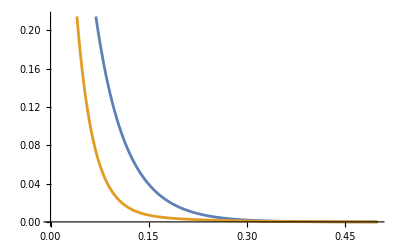

```mathematica
Plot[{crossingEq[3]/.genBos/.Δσ->1,crossingEq[3]/.%24/.Δσ->1},{z,0,1/2},WorkingPrecision->30]
```

```mathematica
Plot[crossingEq[3]/.genBos/.Δσ->1,{z,0,1/2},WorkingPrecision->30]
```

```mathematica
N[crossingEq[3]/.genBos/.zvalsTable[1/9,4/10,10]/.Δσ->1,30]
```

{0.0877870547050691010073100358651,0.0483433608539680336248574090297,0.026896016379664477976517739153,0.0150478750883083722156133677069,0.00843486093357578598773414774478,0.00472196866911136159560993273671,0.00263262739479064132644826486209,0.00145791547909428296676719343043,0.000799819423720449910151227725373,0.00043327442947254802207065740104,0.000230436249359338341791514560191}

```mathematica
crossingEq[3]/.%24/.zvalsTable[1/9,4/10,10]/.Δσ->1
```

{0.018759,0.00878683,0.00495869,0.00323373,0.00226618,0.00161554,0.00113854,0.000783423,0.00052363,0.000338852,0.000210973}

```mathematica
{{{2.7,1.499},{3.76,0.798},{5.62,0.428},{9.15,0.0224}},{{3.19,2.158},{4.48,0.007},{5.66,0.416},{8.09,0.031},{10.3,0.0036}},{{2.61,1.78},{4.43,0.872},{6.41,0.173},{9.49,0.0147}},{{2.64,1.838},{4.5,0.649},{5.07,0.26},{7.49,0.086},{11.41,0.0014}},{{2.53,1.67},{4.2,0.944},{6.08,0.221},{7.71,0.015},{9.12,0.0162}},{{3.06,1.99266},{4.74,0.450734},{6.4,0.18897},{7.96,0.006436},{9.42,0.001061}},{{2.75,1.875},{4.45,0.527},{5.52,0.341},{8.7,0.032}},{{3.28,2.217},{5.83,0.294},{6.97,0.072},{11.26,0.0022}},{{2.64,0.406},{3.23,1.742},{5.4,0.448},{7.61,0.059},{11.64,0.0012}},{{3.09,2.06},{5.12,0.471},{6.88,0.101},{8.79,0.008},{10.13,0.004}},{{3.19,2.158},{4.48,0.007},{5.66,0.416},{8.09,0.031},{10.3,0.0036}},{{2.24,1.177},{3.74,1.461},{6.29,0.26},{7.57,0.012},{10.37,0.0036}},{{2.88,1.735},{4.03,0.568},{5.74,0.367},{8.77,0.027}},{{2.31,1.892},{4.41,1.062},{6.87,0.13},{9.48,0.009}},{{3.26,2.148},{4.48,0.139},{6.23,0.29},{9.21,0.012}},{{3.07,2.011},{4.74,0.399},{6.16,0.21},{7.71,0.014},{9.15,0.012}},{{2.52,1.63},{4.12,0.951},{5.99,0.255},{8.58,0.0243}},{{3.26,2.191},{5.61,0.316},{7.26,0.084}},{{2.1,1.172},{3.46,1.357},{5.02,0.015},{5.44,0.443},{8.16,0.0437}},{{2.15,2.089},{4.41,1.111},{6.98,0.121},{9.24,0.007},{10.32,0.001}},{{2.52,1.461},{4.,1.107},{6.24,0.227},{7.56,0.024},{10.17,0.0036}},{{2.44,1.823},{4.44,0.994},{6.64,0.128},{8.53,0.018}}}
```

{{{2.7,1.499},{3.76,0.798},{5.62,0.428},{9.15,0.0224}},{{3.19,2.158},{4.48,0.007},{5.66,0.416},{8.09,0.031},{10.3,0.0036}},{{2.61,1.78},{4.43,0.872},{6.41,0.173},{9.49,0.0147}},{{2.64,1.838},{4.5,0.649},{5.07,0.26},{7.49,0.086},{11.41,0.0014}},{{2.53,1.67},{4.2,0.944},{6.08,0.221},{7.71,0.015},{9.12,0.0162}},{{3.06,1.99266},{4.74,0.450734},{6.4,0.18897},{7.96,0.006436},{9.42,0.001061}},{{2.75,1.875},{4.45,0.527},{5.52,0.341},{8.7,0.032}},{{3.28,2.217},{5.83,0.294},{6.97,0.072},{11.26,0.0022}},{{2.64,0.406},{3.23,1.742},{5.4,0.448},{7.61,0.059},{11.64,0.0012}},{{3.09,2.06},{5.12,0.471},{6.88,0.101},{8.79,0.008},{10.13,0.004}},{{3.19,2.158},{4.48,0.007},{5.66,0.416},{8.09,0.031},{10.3,0.0036}},{{2.24,1.177},{3.74,1.461},{6.29,0.26},{7.57,0.012},{10.37,0.0036}},{{2.88,1.735},{4.03,0.568},{5.74,0.367},{8.77,0.027}},{{2.31,1.892},{4.41,1.062},{6.87,0.13},{9.48,0.009}},{{3.26,2.148},{4.48,0.139},{6.23,0.29},{9.21,0.012}},{{3.07,2.011},{4.74,0.399},{6.16,0.21},{7.71,0.014},{9.15,0.012}},{{2.52,1.63},{4.12,0.951},{5.99,0.255},{8.58,0.0243}},{{3.26,2.191},{5.61,0.316},{7.26,0.084}},{{2.1,1.172},{3.46,1.357},{5.02,0.015},{5.44,0.443},{8.16,0.0437}},{{2.15,2.089},{4.41,1.111},{6.98,0.121},{9.24,0.007},{10.32,0.001}},{{2.52,1.461},{4.,1.107},{6.24,0.227},{7.56,0.024},{10.17,0.0036}},{{2.44,1.823},{4.44,0.994},{6.64,0.128},{8.53,0.018}}}

```mathematica
NMinimize[{getAvCs[nstates,Table[Δ[i],{i,0,nstates-1}]],{Δ[0]>0,Δ[1]>0,Δ[2]>0,Δ[3]>0,Δ[4]>0,Δ[5]>0,Δ[6]>0,Δ[7]>0,Δ[8]>0,Δ[9]>0}}//Flatten,Table[Δ[i],{i,0,nstates-1}]]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 1000. reached while evaluating 1307/4455+c[0] (8300161 1574^Δ[0] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[«1»],1574/4455]-2477476 2881^Δ[0] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[«1»],2881/4455])+c[1] (8300161 1574^Δ[1] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[«1»],1574/4455]-2477476 2881^Δ[1] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[«1»],2881/4455])+«6»+c[8] (8300161 1574^Δ[8] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[«1»],1574/4455]-2477476 2881^Δ[8] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[«1»],2881/4455])+«1»==0.

N::meprec: Internal precision limit $MaxExtraPrecision = 1000. reached while evaluating 3439/4455+c[0] (15578809 508^Δ[0] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[«1»],508/4455]-258064 3947^Δ[0] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[«1»],3947/4455])+c[1] (15578809 508^Δ[1] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[«1»],508/4455]-258064 3947^Δ[1] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[«1»],3947/4455])+«6»+c[8] (15578809 508^Δ[8] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[«1»],508/4455]-258064 3947^Δ[8] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[«1»],3947/4455])+«1»==0.

N::meprec: Internal precision limit $MaxExtraPrecision = 1000. reached while evaluating 3361/4455+c[0] (15272464 547^Δ[0] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[«1»],547/4455]-299209 3908^Δ[0] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[«1»],3908/4455])+c[1] (15272464 547^Δ[1] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[«1»],547/4455]-299209 3908^Δ[1] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[1],Δ[1],2 Δ[«1»],3908/4455])+«6»+c[8] (15272464 547^Δ[8] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[«1»],547/4455]-299209 3908^Δ[8] 4455^(-2+Times[«2»]) Hypergeometric2F1[Δ[8],Δ[8],2 Δ[«1»],3908/4455])+«1»==0.

General::stop: Further output of N::meprec will be suppressed during this calculation.

```mathematica
getAvCs[nstates,Table[Δ[i]+RandomReal[],{i,0,nstates-1}]/.genBos/.Δσ->1]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.183176,-0.177545,-0.171636,-0.166986,-0.160855,-0.154162,-0.148385,-0.141314,-0.132125,-0.0771871,«1»},«8»,{-53.0351,-28.8975,-14.9664,-8.77919,-4.25253,-1.88238,-0.941527,-0.473606,-0.286187,-0.103304,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-205.842,-97.1818,-43.0918,-22.287,-9.09785,-3.32246,-1.41117,-0.603741,-0.324712,-0.100993,«1»},«8»,{-2175.03,-794.167,-266.557,-110.002,-33.0411,-8.54626,-2.7074,-0.866155,-0.377305,-0.0880758,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.818457,-0.683321,-0.561951,-0.479557,-0.386595,-0.30338,-0.246733,-0.200061,-0.168516,-0.0888004,«1»},«8»,{-4.71698,-3.29934,-2.23982,-1.63619,-1.06783,-0.660872,-0.439454,-0.292775,-0.215759,-0.0985084,«1»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{2.03198,0.0014518},{0.981336,0.00281299},{-0.012591,0.00295699},{0.0626962,0.00162517},{-0.00579676,0.000723605},{0.00187208,0.000250357},{-0.000434067,0.000097658},{0.000113502,0.000030807},{-0.0000103092,3.59056×10^-6},{6.2914×10^-7,2.40083×10^-7}}

```mathematica
Table[N[c[i],30],{i,0,nstates-1}]/.solns[Table[Δ[i]->RandomReal[WorkingPrecision->50],{i,0,9}]]
```

```mathematica
crescRuleInv=Table[c[i]->C[i]/(ⅇ^(-Δ[i]/2)/.genBos),{i,100}];
```

```mathematica
c0s=c[0]/.sols/.crescRuleInv/.%1859/.Δσ->1
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -2069682649424558541350361631285038000000000000000000000000000000000000000000000000000000000000000000 ⅇ^16.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -129574934795850697294129141794819626124725660140450407478424007032789988443255424499511718750000000000000000000000000000000000000000000000000000000000000000000 ⅇ^16.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -249792567486626510484540312102688348862774210713079751163889622864081402394806733354926109313964843750000000000000000000000000000000000000000000000000000000000000000000 ⅇ^16.

General::stop: Further output of N::meprec will be suppressed during this calculation.

{0``-39.265961191344466,0``-84.49284737678585,0``-89.06078284983701,0``-83.57134540838167,0``-83.45271701826017,-93729.891314863939920057,0``-85.13238072055083,0``-83.57381415538902,0``-84.62416246617711,0``-78.4015367039359,0``-32.31203801115242}

```mathematica
getStd[5,genBos]
```

352.50281000458648904333649155

```mathematica
StandardDeviation[%]
```

0.00365709111400982577580947632

```mathematica
Table[C[i],{i,5}]/.genBos/.Δσ->1//N
```

{1.2,0.238095,0.032634,0.00370218,0.000374239}

```mathematica
N[c0s/.c[i_]->C[i]/.genBos/.Δσ->1,30]
```

{2.00994115515206313888782349355,2.00220117222409190179460171578,2.00053917527768195852983848764,2.00014363315436128614234199773,2.00004225455344216358037754021,2.00001500166239922148820712105,2.00000848800756073254321512715}

```mathematica
NMinimize[{StandardDeviation[c0s],Table[c[i]≥0,{i,10}]}//Flatten,Table[c[i],{i,10}],WorkingPrecision->50,Method->"SimulatedAnnealing"]
```

{1.831828984475140087768748871726314054368314331651×10^-8,{c[1]→1.2352804931577363593581272496371313603760352442133,c[2]→0.21487283558590963457562662817957952660142318906465,c[3]→0.044000811429511548083253410163521821635503225570845,c[4]→0,c[5]→0.0010402207025475707280782353284420628533052781818127,c[6]→0.57952313326871168843350370566265114726035480337387,c[7]→1.3294066004563760353602440545014954429496967196714,c[8]→0.31609337073629918343018816506255781654871556060049,c[9]→0.38695151508881595765056387523704733342533374388246,c[10]→0.27579656837830180213367059709218469754395894801514}}

```mathematica
c0s=c[0]/.Table[Solve[eqs[[i]]==0,c[0]][[1]],{i,Length[eqs]}];
```

```mathematica
StandardDeviation[N[c0s,30]]
```

```mathematica
getStd[n_,vals_]:=Module[{eqs,sols,c0s},eqs=crossingEq[n]/.crescRule/.genBos/.Δσ->1/.zvalsTable[11];
sols=Table[Solve[eqs[[i]]==0,c[0]][[1]],{i,Length[eqs]}];
c0s=c[0]/.sols/.c[i_]->C[i]/ⅇ^(-Δ[i]/2)/.vals/.Δσ->1;
StandardDeviation[N[c0s,30]]

]
```

```mathematica
nstates=10;
```

```mathematica
crossingEq[0]
```

(1-z)^(2 Δσ)-z^(2 Δσ)+C[0] (-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])

```mathematica
(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δσ->1//Simplify
```

-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]

```mathematica
Maximize[{-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.Δ[0]->3/2,0<z<1/2},z]//N
```

Maximize::incs: Warning: Maximize was unable to prove that the result is a global maximum.

{0.000118132,{z→0.00915777}}

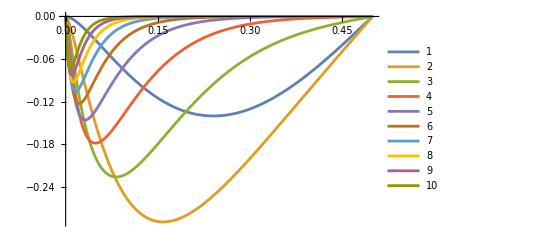

```mathematica
Plot[{2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3),6/5 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)),5/21 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)),14/429 (1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z])),1/2431 9 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z])),(11 (-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/29393,(13 (-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z]))/371450,(2 (-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(1-z)^2 z^16 Hypergeometric2F1[16,16,32,z]))/646323,(17 (-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(1-z)^2 z^18 Hypergeometric2F1[18,18,36,z]))/64822395,(19 (-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(1-z)^2 z^20 Hypergeometric2F1[20,20,40,z]))/883631595},{z,0,5/10
},WorkingPrecision->50,PlotLegends->Automatic]
```

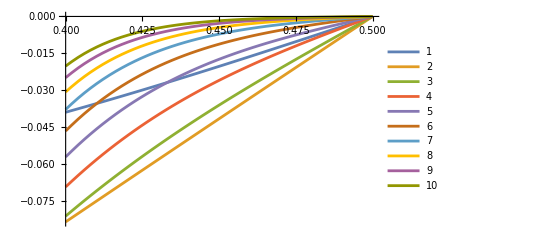

```mathematica
Plot[{(6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3,(140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7),(462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11),1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]),1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]),-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z],-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z],-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(1-z)^2 z^16 Hypergeometric2F1[16,16,32,z],-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(1-z)^2 z^18 Hypergeometric2F1[18,18,36,z],-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(1-z)^2 z^20 Hypergeometric2F1[20,20,40,z]},{z,4/10,5/10
},WorkingPrecision->50,PlotLegends->Automatic]
```

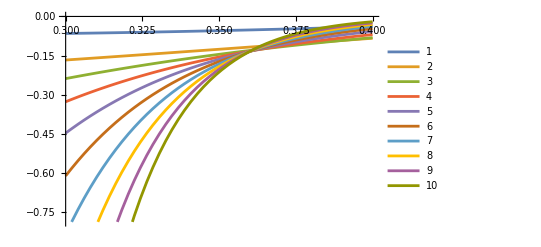

```mathematica
Plot[{(6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3,(140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7),(462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11),1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]),1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]),-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z],-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z],-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(1-z)^2 z^16 Hypergeometric2F1[16,16,32,z],-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(1-z)^2 z^18 Hypergeometric2F1[18,18,36,z],-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(1-z)^2 z^20 Hypergeometric2F1[20,20,40,z]},{z,3/10,4/10
},WorkingPrecision->50,PlotLegends->Automatic]
```

```mathematica
N[{(6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3,(140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7),(462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11),1/(7 z^7)5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z])-1/(7 (-1+z)^15)5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]),1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-1/(63 (-1+z)^19)46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]),-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z],-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z],-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(1-z)^2 z^16 Hypergeometric2F1[16,16,32,z],-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(1-z)^2 z^18 Hypergeometric2F1[18,18,36,z],-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(1-z)^2 z^20 Hypergeometric2F1[20,20,40,z]}/.z->1/10,30]
```

{-0.0398662243092160281472121359747,-0.213927253502664304806705615946,-0.929487421980090263676144925539,-4.02598339619652381388016834312,-17.4179721179240006481188513959,-75.3109506753833532950694631337,-325.507951449749431847530334178,-1406.57953776948129799956285413,-6077.12891595523763492853020587,-26253.297925369399586651722263}

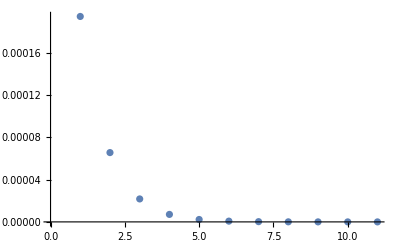

```mathematica
ListPlot[Table[N[crossingEq[n-1]-crossingEq[n]/.genBos/.Δσ->1/.z->1/10,30],{n,10,20}]]
```

```mathematica
Manipulate[Plot[-(1-z)^Δ[0] z^2 Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(-1+z)^2 z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z],{z,0,1/2
}],{Δ[0],0,10}]
```

```mathematica
(1-z)^(2 Δσ)-z^(2 Δσ)/.Δσ->1//Simplify
```

1-2 z

```mathematica
idx=RandomSample[Range[Length[eqs]],Length[eqs]]
```

{84,2,5,71,20,63,100,1,94,42,32,29,3,56,81,62,79,45,90,15,73,76,39,35,23,53,48,68,41,60,85,52,58,74,12,37,61,38,8,65,88,17,92,26,77,10,34,30,43,50,93,47,72,13,98,22,89,40,82,99,83,64,54,67,57,70,27,4,55,97,75,11,21,25,18,14,95,33,24,44,7,28,9,6,16,96,59,19,36,87,46,66,78,51,86,80,31,49,69,91}

```mathematica
solns[Table[Δ[i]->]]
```

```mathematica
RandomReal[{0,10}]
```

8.65893

```mathematica
solns[Table[Δ[i]->RandomReal[{0,10},WorkingPrecision->50],{i,0,9}]]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.074991885302760193163658286011,-0.15132991122722176852909457843,-0.139194320134009278031199800164,-0.170600678150786286791588696545,-0.177858120945357779116698258132,«64»,-0.165013470491037639015041307684,-0.16405153918314263633452458714,-0.166267582613755072690544238566,-0.120138624396074727845493923005,«1»},«8»,{-«64»,«9»,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0587548326148257320405047173161,-0.0972728508941726889614748026203,-0.0984297126210676155776312689885,-0.0847031436253498190813806757127,-0.0791567312007068290525044203445,«64»,-0.0890038242706478834281885707468,-0.0897246986817663477905723796789,-0.0880512361557370585669277075536,-0.090703776488199195754874456529,«1»},«8»,{-«64»,«9»,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.0673175342856448574403871889406,-0.122344239624831097775865839234,-0.118294845071799302346794617711,-0.1208514687492331006185620932,-0.119227351254060224155856064913,«64»,-0.121911705626730997146102664488,-0.122063071485320323303660416586,-0.12169802878568122892672513252,-0.105715828725631152667024440557,«1»},«8»,{-«64»,«9»,«1»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{c[0]→137.3491929671880154,c[1.]→-837.4998386161689498,c[2.]→-1178.624509119378626,c[3.]→1951.273867819221674,c[4.]→-13.14216639082191778,c[5.]→-0.567957632701372398,c[6.]→32.67749259271649885,c[7.]→-123.9980041611176826,c[8.]→81.51489169599969215,c[9.]→-109.4179861239511518},{c[0]→121.625451526705655,c[1.]→-752.197492104352923,c[2.]→-1056.84943301795364,c[3.]→1750.85875073536587,c[4.]→-13.0241139282737353,c[5.]→-0.517030552625022313,c[6.]→29.4628085848375832,c[7.]→-110.43452581187857,c[8.]→72.6204993719473091,c[9.]→-98.5379168147948407},{c[0]→106.370441609697,c[1.]→-668.7845524536676,c[2.]→-937.9112374436752,c[3.]→1555.016436977463,c[4.]→-12.89935200570921,c[5.]→-0.4667781311877363,c[6.]→26.31068335718553,c[7.]→-97.26166301887769,c[8.]→63.97072692317963,c[9.]→-87.97097193371764},{c[0]→118.43047998111693,c[1.]→-734.70067884107156,c[2.]→-1031.905648693882,c[3.]→1709.7831737286598,c[4.]→-12.997982098424788,c[5.]→-0.50647836036289535,c[6.]→28.801348519796181,c[7.]→-107.67517298712652,c[8.]→70.807979571961125,c[9.]→-96.324953657204271},{c[0]→128.036507736639744,c[1.]→-786.278633253395612,c[2.]→-1105.64558826323131,c[3.]→1831.06762918699087,c[4.]→-13.0644795711520672,c[5.]→-0.536947989465279272,c[6.]→30.7385920249490254,c[7.]→-115.950909131283977,c[8.]→76.2244346231181604,c[9.]→-102.966697604624052},{c[0]→89.097641158541177,c[1.]→-574.81026253417229,c[2.]→-803.81606988624725,c[3.]→1334.2842479712129,c[4.]→-12.764410815555662,c[5.]→-0.41046778496295835,c[6.]→22.765400546762701,c[7.]→-82.356071719109279,c[8.]→54.191903274676947,c[9.]→-76.012867281352078},{c[0]→99.10113522024806,c[1.]→-629.7852745202745,c[2.]→-882.1472382926142,c[3.]→1463.303191830535,c[4.]→-12.84999507727176,c[5.]→-0.4437681332947508,c[6.]→24.84638605958672,c[7.]→-90.99986745300708,c[8.]→59.87281637559257,c[9.]→-82.94608490188941},{c[0]→164.89633784548341,c[1.]→-980.25828262401262,c[2.]→-1383.775749035168,c[3.]→2287.9701696903821,c[4.]→-13.280100515683264,c[5.]→-0.64918475413376283,c[6.]→37.976620447210374,c[7.]→-147.62904523131255,c[8.]→96.880048222883255,c[9.]→-128.41686212812023},{c[0]→172.21470373878192,c[1.]→-1019.16312278964788,c[2.]→-1439.47948298844995,c[3.]→2379.5326826426532,c[4.]→-13.3258828273598792,c[5.]→-0.671912904867951154,c[6.]→39.4328616432030576,c[7.]→-153.926117235599648,c[8.]→100.994190387785439,c[9.]→-133.471955183723767},{c[0]→82.92818861367682,c[1.]→-539.8067336895603,c[2.]→-754.1706844953865,c[3.]→1252.355190814739,c[4.]→-12.69528457618332,c[5.]→-0.388530524303524,c[6.]→21.42628053546209,c[7.]→-77.00228216417654,c[8.]→50.65354879384853,c[9.]→-71.71935932469596}}

```mathematica
RandomSample[Range[Length[eqs]],Length[eqs]]
```

```mathematica
solns=Block[{$MaxExtraPrecision=1000},Table[Solve[Table[N[eqs[[idx[[i+nstates j]]]]==0,30],{i,nstates}]][[1]],{j,0,9}]];
```

```mathematica
getAvCs[nstates]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.0756434381123245178211310730118,0.0787299749776453362371743603389,0.224078363945225750703937400863,0.0933386467697118569973499565456,0.148271120851503806919263452059,«64»,0.124423859291209257192087180633,0.195335455545437935958957524372,0.258534064963956674827707065008,0.0977726572975329128753609643372,«1»},«8»,{«64»,«64»,«7»,«63»,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.117669558001027947680125615782,0.122736840361762715148387278046,0.390323050786564178434968640914,0.147070997238222194089037152966,0.243756617033881823926889830676,«64»,0.200781133919680635201396430185,0.333000534637396904495630584699,0.46176881816331572285268093683,0.154571633995274559207194619303,«1»},«8»,{«64»,«64»,«7»,«64»,«1»}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.0864561429734565203465474237389,0.0900130282333681769623290061312,0.260531518286149772628108699962,0.106885783308268363043716509725,0.170880712634242503683314210474,«64»,0.14299448242586567483483844559,0.226366385322387187685539610356,0.301749997847394302440823988393,0.11201931641628334775929839802,«1»},«8»,{«64»,«64»,«7»,«64»,«1»}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{{762.601426,10.3774},{-1.64259097,0.00071382},{-5.25606159,0.0272261},{-75.7896215,0.844793},{4.67167096,0.08341846},{24.1829383,0.21894},{-937.939585,13.16094},{2.68830232,0.00796355},{679.15888,10.50177},{-453.675003,7.155802}}

```mathematica
%[[;;,2]]/%[[;;,1]]
```

{0.0097,0.012,-0.002,-0.013,0.013,0.016,-0.011,-0.013,-0.012,0.012}

```mathematica
Table[{Mean[%[[;;,i]]],StandardDeviation[%[[;;,i]]]},{i,Length[%[[1]]]}]
```

{{76198.,740.},{5.1461×10^7,590000.},{-3.5073,0.005},{-5.6007×10^6,74000.},{9.8774×10^9,1.3×10^8},{971.29,16.},{-2.0738×10^6,22000.},{-9.9093×10^9,1.3×10^8},{-7.5596×10^7,880000.},{6.3636×10^7,780000.}}

```mathematica
Table[C[i],{i,0,nstates-1}]/.genBos/.Δσ->1//N
```

{2.,1.2,0.238095,0.032634,0.00370218,0.000374239,0.000034998,3.09443×10^-6,2.62255×10^-7,2.15022×10^-8}

```mathematica
Table[Solve[Table[N[eqs[[%1967[[i+6j]]]]==0,30],{i,6}]],{j,0,9}]
```

$Aborted

```mathematica
Block[{$MaxExtraPrecision=1000},N[%1969,50]]
```

{{c[0]→1.9585068657547095444884719032963857504347667852471,c[1.]→1.2341802026597055786834782570934925035347026977723,c[2.]→0.21560343360645039992521979086853194423005852205825,c[3.]→0.04364918913298459826800221657683693597500312995786,c[4.]→0.00010347357503795678596118666795369672915808739185923,c[5.]→0.0010267851371122966665313570289292504732265185010799}}

```mathematica
StandardDeviation[N[%1819,30]]
```

49.764820257027387532222119129

```mathematica
c[0]/.%/.c[i_]->C[i]/.genBos/.Δσ->1;
```

```mathematica
Table[Solve[%[[i]]==0,c[0]][[1]],{i,Length[%]}];
```

```mathematica
crossingEq[10]/.C[i_]->c[i]/.genBos/.Δσ->1/.zvalsTable[11];
```

```mathematica
N[crossingEq[10]/.C[0]->c[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify,30]
```

{0.253921276250496926774728735338-0.0015199233562570685810504192351 c[0],0.0442359283333042289044398218411-0.0210113976097971505739363678225 c[0],0.0847006227344038566202147625987-0.0423178539781331867226724448289 c[0],0.117053454528193786022204759438-0.0585252601582749107448657204281 c[0],0.135597584418508987728347144647-0.067798710111611548886427408903 c[0],0.139890038293893894164589399855-0.0699450140266072260199911352185 c[0],0.131043773359365125119234005048-0.0655218863459512291815565022 c[0],0.110968610368230316899208734575-0.055484305162424806894257535749 c[0],0.0820277449118885321366006841111-0.0410138724545926590228592847418 c[0],0.0468506396142502674333542908927-0.0234253198070473679857139593215 c[0],0.00821904647862498951606475600095-0.00410952323930961669969088186038 c[0]}

```mathematica
N[crossingEq[15]/.C[0]->c[0]/.genBos/.Δσ->1/.zvalsTable[11]//Simplify,30]
```

{0.0744722490775619185776805795061-0.0015199233562570685810504192351 c[0],0.0420607414053921577244989909568-0.0210113976097971505739363678225 c[0],0.084635887009689630795256971623-0.0423178539781331867226724448289 c[0],0.117050522072447243674735936875-0.0585252601582749107448657204281 c[0],0.135597420247889212336746634314-0.067798710111611548886427408903 c[0],0.139890028053632427679769691354-0.0699450140266072260199911352185 c[0],0.131043772691910169984975668144-0.0655218863459512291815565022 c[0],0.110968610324849757826330480492-0.055484305162424806894257535749 c[0],0.0820277449091853206116932145794-0.0410138724545926590228592847418 c[0],0.0468506396140947360126832680704-0.0234253198070473679857139593215 c[0],0.00821904647861923339985835329382-0.00410952323930961669969088186038 c[0]}

```mathematica
N[crossingEq[15]/.C[0]->x/.crescRule/.c[i_]->RandomReal[10,WorkingPrecision->30]/100/.genBos/.Δσ->1/.zvalsTable[11][[2;;]]//Simplify,30]
```

{-96.910730705252989997933912-0.021011397609797150573936368 x,-0.5160191000288325309695077791-0.042317853978133186722672445 x,0.641414778951502777415240653044-0.05852526015827491074486572043 x,0.588156852533876124288833435953-0.067798710111611548886427408903 x,0.496690547848912266073314849708-0.069945014026607226019991135219 x,0.402060311483961683132029765793-0.0655218863459512291815565022 x,0.306772309310573310608984840819-0.055484305162424806894257535749 x,0.211247376009659664379523681704-0.041013872454592659022859284742 x,0.115615002367671351263129798957-0.023425319807047367985713959321 x,0.0199353844837711867669428133322-0.00410952323930961669969088186 x}

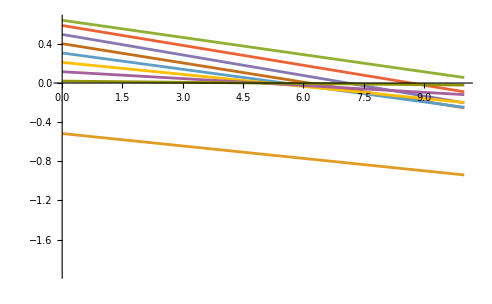

```mathematica
Plot[%,{x,0,10}]
```

```mathematica
4/7//N
```

0.571429

```mathematica
Table[c[1.]/.Solve[%1954[[i]]==0,c[1.]],{i,11}]
```

{{-403.872 (-0.98+0.000559149 c[0.])},{-49.9274 (-0.884+0.00772966 c[0.])},{-33.6343 (-0.788+0.0155679 c[0.])},{-30.6624 (-0.692+0.0215302 c[0.])},{-31.9482 (-0.596+0.0249418 c[0.])},{-36.175 (-0.5+0.0257313 c[0.])},{-43.8514 (-0.404+0.0241042 c[0.])},{-57.2532 (-0.308+0.0204115 c[0.])},{-83.3918 (-0.212+0.0150882 c[0.])},{-153.026 (-0.116+0.00861769 c[0.])},{-889.531 (-0.02+0.00151181 c[0.])}}

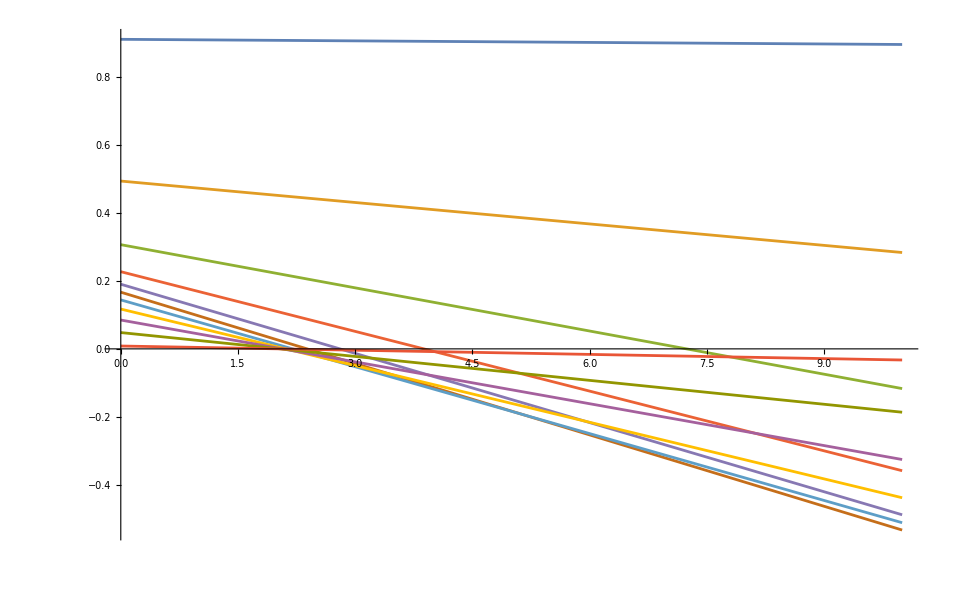

```mathematica
Plot[%,{c[0],0,10}]
```

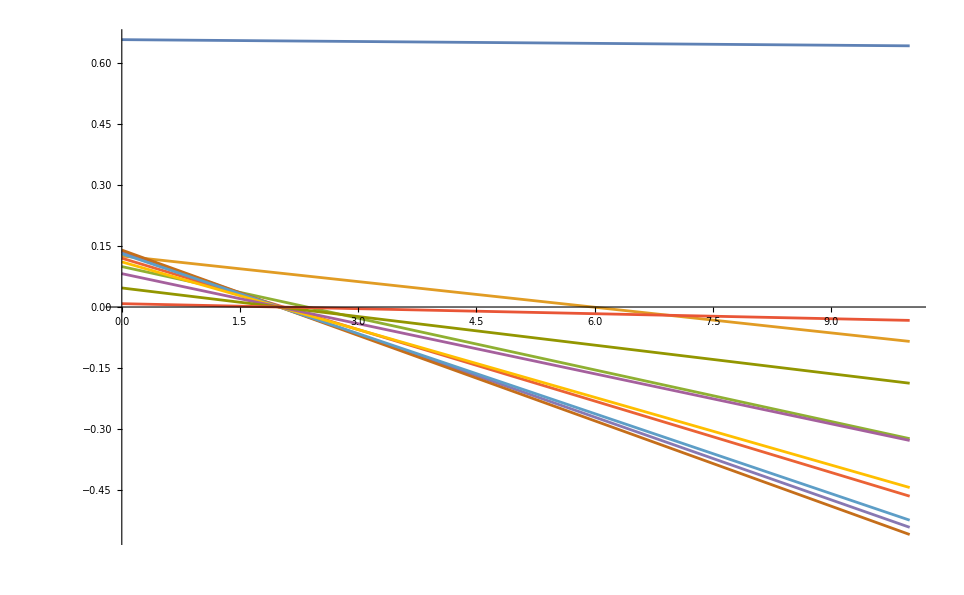

```mathematica
Plot[%1967,{c[0],0,10}]
```

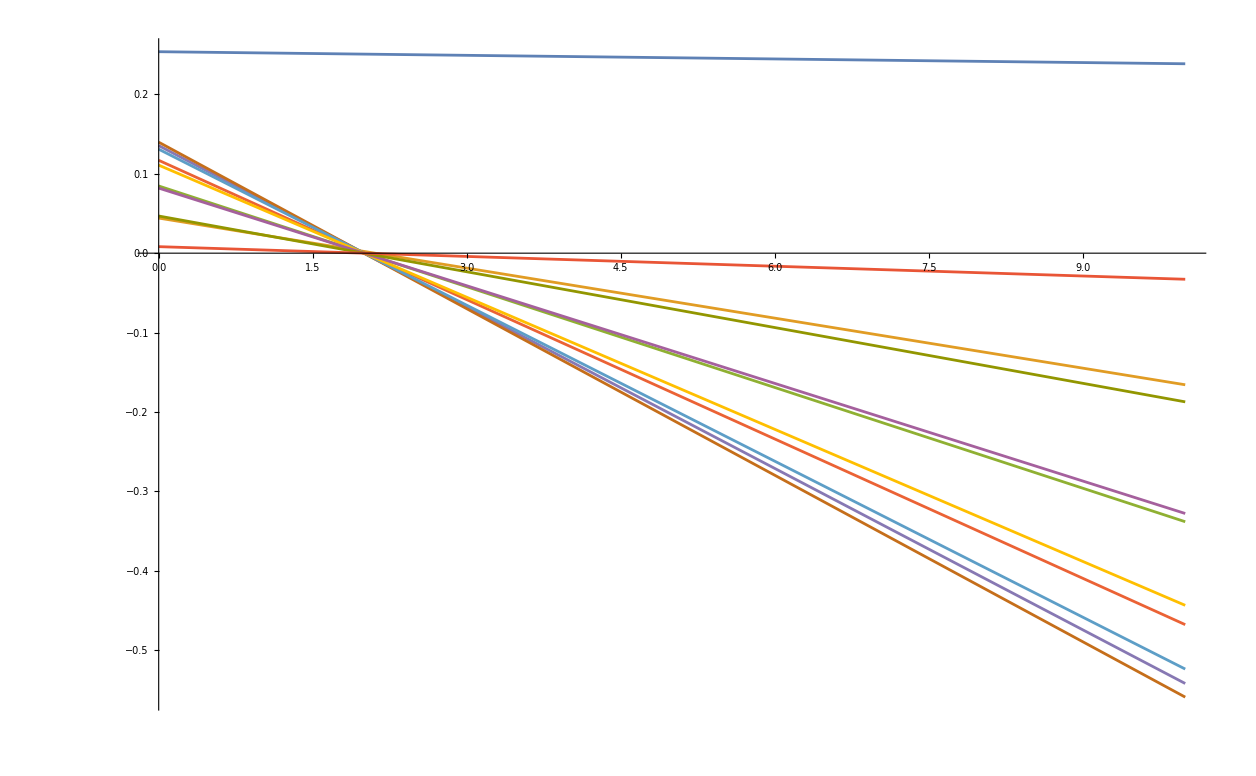

```mathematica
Plot[%,{c[0],0,10}]
```

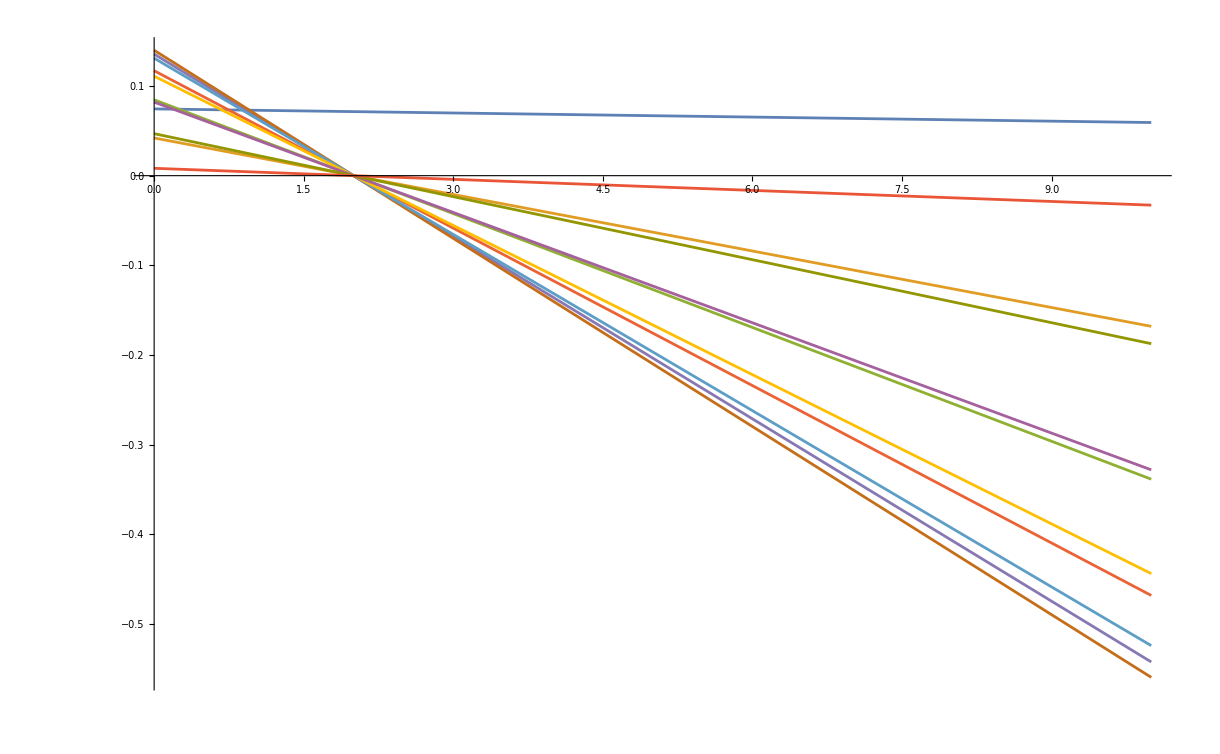

```mathematica
Plot[%,{c[0],0,10}]
```

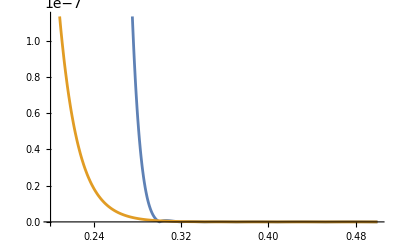

```mathematica
Plot[{N[crossingEq[10]/.crescRule/.%1782[[2]]/.genBos/.Δσ->1,30]//Abs,crossingEq[10]/.genBos/.Δσ->1//Abs},{z,2/10,1/2},WorkingPrecision->30]
```

```mathematica
N[crossingEq[10]/.crescRule/.%1757[[2]]/.genBos/.Δσ->1/.zvalsTable[21],30]
```

{0.00009002859819336930336700664,-0.00085938736519140921758160249,0.0024983704585787308079597525,-0.00103795715407495071680116444,-0.00181594332942877036411238099,-0.00102288940283567803374734621,0.00006189652220757828687147242,0.000860661713789547900113146981,0.00121989992128712352693909398,0.00118273353024469794690725078,0.000865314448538500211224668209,0.00039610127336891507632162598,-0.00011166005420919983813924975,-0.000570464905570673773405703261,-0.000920594709410360800134200816,-0.00112814480084559380870889905,-0.00118137678402469247885199302,-0.0010865944452373047085454986,-0.000864117566732487903859695441,-0.000544583922904174967688271944,-0.000165621057736269506085641595}

```mathematica
Norm[N[crossingEq[10]/.genBos/.Δσ->1/.zvalsTable[21],30]]
```

0.251539003283956443719421477566

```mathematica
Norm[crossingEq[10]/.genBos/.Δσ->1/.zvalsTable[21]]
```

```mathematica
xvalsResc
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
N[crossingEq[10]/.genBos/.Δσ->1/.zvalsTable[21],30]
```

{0.250881429537982789612627896868,0.0180375447158065198902657515739,0.00221313311370992775656708619597,0.00035086788941867429748801790935,0.0000649147781374831748698729408676,0.0000133118018849765005184719937537,2.9342116439645324733185818969×10^-6,6.81227624416055596743389831212×10^-7,1.64195285889955492326841079146×10^-7,4.06403613779106828541229395807×10^-8,1.02406794421246071294176281885×10^-8,2.6083903421841823352865328144×10^-9,6.67462666756121000647464437024×10^-10,1.7065769809708780571039574815×10^-10,4.33807031106936630765167293317×10^-11,1.09114483626592051959969979419×10^-11,2.70321409088211462747559320605×10^-12,6.56568760581685071193338357487×10^-13,1.55531461926372249780549998418×10^-13,3.53615911377441389542549100502×10^-14,5.75611668299228019551243468042×10^-15}

```mathematica
N[crossingEq[10]/.crescRule/.%1727[[2]]/.genBos/.Δσ->1/.zvalsTable[21],30]
```

{0.00016585294313295807572107254,-0.0014551381031503618746472037,0.00372101163080126273927746566,-0.00103020283985045816717062412,-0.00263893341463387392353178321,-0.0018261983828772661622890753,-0.00027783623710299405041679595,0.00103851995798377492857616882,0.00176201776490240818722818781,0.00187501371630157045685999473,0.0015164545979190014403826691,0.000873469089745021120235484782,0.00012507931463150307697679704,-0.00058321659147631292793358347,-0.00114776524750260179441339378,-0.0015062300433860960608370874,-0.00163292531251619878778169966,-0.00153258125052818771763479402,-0.001233849020740503545801188495,-0.0007831320782978174605975912247,-0.0002389234592926252271402943889}

```mathematica
cs/xvalsResc/.%1709[[2]]
```

{0.9995997919967716982725701297,1.002338847810356852240204975,0.9787903980605496050443779152,1.1275432711555514255988580324,0.55913741115150047309772838442,1.6718652328571715612117237448,1.1771460185492959333404171106,0.0082081770301825864438494423167,0.00036934076269110861844723806931,0,8.1605802985377193347041483897}

```mathematica
crEqResc/.genBos/.Δσ->1/.genBosRec
```

{0.00009787843776371733427523734,0.00003547437149158618046076713,0.00001331180188497650051847199,5.13718198782600219668289×10^-6,2.02818081387592169372168×10^-6,8.15767655928593021942319×10^-7,3.3313277327326405032395×10^-7,1.3772558214463839383298×10^-7,5.75037310679307416757×10^-8,2.419574159370023780133×10^-8,1.024067944212460712942×10^-8}

```mathematica
Abs[%1651]/Abs[%1680]
```

{267716.56521453554294,10092.3723609680056176,1077.675589324130641006,295.8315930642057002146,1506.09454478125676381,50.47207445164451537596,1174.0585703434921847,8.071805485328880985788,11.9161994278145582318,1.114766860527680183057,1.08273618052400776452}

```mathematica
crEqResc/.genBos/.Δσ->1/.%1678[[2]]
```

{-3.6560471215250400682×10^-10,3.51496855474560306×10^-9,-1.235232756206815469388×10^-8,1.736522436503614340792×10^-8,-1.34664906722073816999×10^-9,-1.616275266652950355728×10^-8,-2.8374459476565977417×10^-10,1.706254968544089559071×10^-8,4.82567713105796669583×10^-9,-2.170475500343369438513×10^-8,9.45814837107268729584×10^-9}

```mathematica
crossingEq[10]/.genBos/.Δσ->1
```

```mathematica
crossingEq[10]/%1693/.crescRule/.genBos/.Δσ->1/.%1678[[2]]/.z->49/100
```

3.365360605274557732702817×10^8

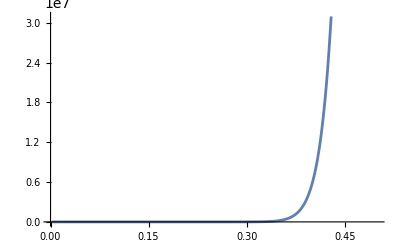

```mathematica
Plot[crossingEq[10]/%1693/.crescRule/.genBos/.Δσ->1/.%1678[[2]],{z,0,1/2},WorkingPrecision->30]
```

```mathematica
crEqResc/.genBos/.Δσ->1/.%1678[[2]]
```

```mathematica
Solve[xval==Table[C[i],{i,0,10}]/.crescRule/.genBos/.Δσ->1]
```

{{c[0]→5.4365636569180904707205749427,c[1]→19.000429968678814870021099184,c[2]→18.259579021079697946298663322,c[3]→10.690546859636634225084526669,c[4]→4.7715590566439250921292220304,c[5]→1.7920514450478205742464365268,c[6]→0.59702138715837174157131087889,c[7]→0.18210671834456662651826771772,c[8]→0.051912537276356951527572179285,c[9]→0.014026346430477592463314989687,c[10]→0.0036284755090085569612960404487}}

```mathematica
N[crossingEq[10]/.zvals/.genBos/.Δσ->1,30]
```

{0.0000978784377637173342752373398607,0.0000354743714915861804607671322117,0.0000133118018849765005184719937537,5.13718198782600219668289274376×10^-6,2.02818081387592169372168335227×10^-6,8.15767655928593021942318500482×10^-7,3.33132773273264050323946866999×10^-7,1.37725582144638393832981258774×10^-7,5.75037310679307416756995701203×10^-8,2.41957415937002378013300715885×10^-8,1.02406794421246071294176281885×10^-8}

```mathematica
crEqResc/.genBos/.Δσ->1/.%1640
```

{0.00009787843776371733427523734,0.00003547437149158618046076713,0.00001331180188497650051847199,5.13718198782600219668289×10^-6,2.02818081387592169372168×10^-6,8.15767655928593021942319×10^-7,3.3313277327326405032395×10^-7,1.3772558214463839383298×10^-7,5.75037310679307416757×10^-8,2.419574159370023780133×10^-8,1.024067944212460712942×10^-8}

```mathematica
N[C[10]/0.00001670170079024566/.genBos/.Δσ->1,30]
```

0.000102783

```mathematica
C[10]/.crescRule/.genBos/.Δσ->1//N
```

0.0000167017 c[10.]

```mathematica
crescRule
```

C[j_]→ⅇ^(-Δ[j]/2) c[j]

```mathematica
xvalsResc=N[Table[ⅇ^(Δ[j]/2) C[j],{j,0,10}]/.genBos/.Δσ->1,30]
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
genBosRec=Table[c[i]->%1639[[i+1]],{i,0,10}]
```

{c[0]→5.43656365691809047072057494271,c[1]→8.86686731871678027267651295269,c[2]→4.78227069599706374784012610823,c[3]→1.78175780993943903751408777818,c[4]→0.549452255007482283336092233799,c[5]→0.150978693172527008086696117646,c[6]→0.0383799463173238976724414136431,c[7]→0.0092243599161463487288665020414,c[8]→0.00212507462534794538416962137422,c[9]→0.0004736168924576849403197269245,c[10]→0.000102782903087857674134209314424}

```mathematica
crescRule
```

C[j_]→ⅇ^(-Δ[j]/2) c[j]

```mathematica
crossingEq[10]/.C[j_]->ⅇ^(-Δ[j]/2) c[j]^2/.genBos/.Δσ->1/.zvalsTable[21]
```

```mathematica
crossingEq[10]/.C[j_]->ⅇ^(-Δ[j]/2) c[j]^2/.genBos/.Δσ->1/.zvalsTable[11]
```

```mathematica
crossingEq[10]/.C[j_]->ⅇ^(-Δ[j]/2) c[j]/.genBos/.Δσ->1/.zvalsTable[11]
```

```mathematica
FindRoot[%,{{c[0],3/10,0,5},{c[1],5/10,0,5},{c[2],2/5,0,5},{c[3],2/10,0,5},{c[4],1/3,0,5},{c[5],3/10,0,5},{c[6],1/19,0,5},{c[7],2/19,0,5},{c[8],4/23,0,5},{c[9],2/14,0,5},{c[10],4/24,0,5}},WorkingPrecision->30,MaxIterations->10000]
```

FindRoot::reged: The point {1.55114112015874175331741816251,2.4955514227026533509132205656,1.5096327457824571046966572432,0.491450946519240702803760871881,0.516900056176932657396797621488,0.113371657433338848654339071736,0.180098936200362532055785999964,0,0.167095452939907540130746541871,0.0996778634720489177452255598318,«1»} is at the edge of the search region {0,5.} in coordinate 8 and the computed search direction points outside the region.

{c[0]→1.55114112015874175331741816251,c[1]→2.4955514227026533509132205656,c[2]→1.5096327457824571046966572432,c[3]→0.491450946519240702803760871881,c[4]→0.516900056176932657396797621488,c[5]→0.113371657433338848654339071736,c[6]→0.180098936200362532055785999964,c[7]→0,c[8]→0.167095452939907540130746541871,c[9]→0.0996778634720489177452255598318,c[10]→0.127468380826744208419382605905}

```mathematica
Table[c[i-1]->{{c[0],1,0,5},{c[1],5/10,0,5},{c[2],2,0,5},{c[3],2/10,0,5},{c[4],1/3,0,5},{c[5],3/10,0,5},{c[6],1/19,0,5},{c[7],2/19,0,5},{c[8],4/23,0,5},{c[9],2/14,0,5},{c[10],4/24,0,5}}[[i,2]],{i,11}]
```

{c[0]→1,c[1]→1/2,c[2]→2,c[3]→1/5,c[4]→1/3,c[5]→3/10,c[6]→1/19,c[7]→2/19,c[8]→4/23,c[9]→1/7,c[10]→1/6}

```mathematica
N[D[%2141,{cs,1}],30]
```

11

```mathematica
N[D[%2141,{cs,1}]/.{c[0]->1,c[1]->1/2,c[2]->2,c[3]->1/5,c[4]->1/3,c[5]->3/10,c[6]->1/19,c[7]->2/19,c[8]->4/23,c[9]->1/7,c[10]->1/6},30]
```

{{-0.00111829710984654686147892723738,-0.00247605311913821480947349187792,-0.0399401393921559780874129022343,-0.0159462095600579102026004734052,-0.105621338813211187441945202172,-0.376826493014075095096358233598,-0.261663644129788745031338751213,-2.06923416272510958499666510362,-13.5081578488453390108909274584,-43.8203482010786182508271031337,-201.821568617679078951296876648},{-0.0154593224218463093254456054373,-0.0200290626719754523244192463536,-0.178099250689622380697370170335,-0.0394301245375231116878494764773,-0.145235312588439474506597227899,-0.288602664648165408248631072056,-0.111729266152912285302252400822,-0.492925263852420164239898822475,-1.79603005320353342483252459114,-3.25299649308835340451921314414,-8.36708231554159176220079398022},{-0.0311357369461006681720737715097,-0.0297315653671014384321463867754,-0.182295524268317286913272496014,-0.0278571141278295256744814111197,-0.0708707802940259023896243290262,-0.0973062025678795089180771660881,-0.0260343956272528881242973559303,-0.0793896311506548757921538873492,-0.199958962969430322644910555678,-0.250372043808546951714060171784,-0.445219086397805505811581993483},{-0.0430604800028789043253255129689,-0.0326132156540819588392861512694,-0.147084084429820423776920138267,-0.0165169370073599289302354649681,-0.0308889083181538946683204744244,-0.0311814085427335962600858909405,-0.00613435728765677246900875391514,-0.0137556683182473206220487219908,-0.0254786023150164415276264985087,-0.023461294562253715768568135241,-0.0306818898542585389758874920644},{-0.0498835031760085449523993682471,-0.0313007066032364568847022206363,-0.107361504207814728735806047471,-0.00913228195857960273045933350868,-0.0129375855599376886118106359976,-0.00989448578321939397641127514475,-0.00147482814779436722614617019516,-0.00250580296019036748229656716187,-0.00351678615800758163587757055459,-0.00245378326530146702392807673181,-0.00243156919911213369193558290342},{-0.051462665345673922047096021381,-0.0276434260264076911236876231007,-0.0737631882899126756694125230771,-0.00483342071266706068253726129785,-0.00527230153629475841652228704451,-0.00310477035824468592586344698321,-0.000356356758448034522478328055176,-0.000466240314140537753342981552043,-0.00050389071832088108402247212132,-0.000270744657321370285903764984932,-0.000206608364036363225707540212711},{-0.0482083098668945902300836440156,-0.022804307752237235622338745431,-0.0483244185165536124981093061469,-0.00246526978627207861321831721607,-0.00208862282499181902679465673866,-0.000955103231395015341214522573447,-0.0000851274251355860185267377418003,-0.0000864899261653264356386091798321,-0.000072588691881493637899299012543,-0.0000302882036946051173672139445988,-0.0000179492189000840875067938157772},{-0.0408230703538772205079060436769,-0.0174662630520375474954862054576,-0.0301395434877952696471956082179,-0.00120952261554250807352209720491,-0.000799729892226597675832028738029,-0.000284974031140440298049431147412,-0.0000197871660136465383847278687061,-0.0000156611565938372073587737489289,-0.0000102393442911105835342812145431,-3.32831167047123865519886460558×10^-6,-1.53654557139324650328162521784×10^-6},{-0.030176320957744717590542296836,-0.0119915875612482511077530045791,-0.017461128226402995620764798969,-0.000562415931624175442648823758187,-0.000292467326919207760222767019591,-0.0000813812882885770212127977682786,-4.40228768363399965100600817314×10^-6,-2.71257025473273961672604522464×10^-6,-1.38037722645547478960293708304×10^-6,-3.49213584389377833164399207773×10^-7,-1.25472056391316963921669024443×10^-7},{-0.0172353871197578096138871100684,-0.00653483309030166931186356305947,-0.0084486338814217025546840020072,-0.000228890850504201217974170502848,-0.0000966397558375535742180592957889,-0.0000213761228646839900334100577863,-9.08279098524783936435093826524×10^-7,-4.36744277892630781624899742171×10^-7,-1.72837356110480582754885001612×10^-7,-3.39412504742190477334117305374×10^-8,-9.45723239466541665346530084954×10^-9},{-0.00302361822551655444440908877849,-0.00112418814294627275154432355489,-0.00137888005059528715201448977184,-0.0000343538229020777415013546871388,-0.0000129720930880044596021643839824,-2.50493934512400995987842989494×10^-6,-9.10341660505905514267375941342×10^-8,-3.68044783047801914241345053639×10^-8,-1.20740502675523341007805659×10^-8,-1.94275904632926413669805721268×10^-9,-4.39293305982419319908802456632×10^-10}}

```mathematica
N[crossingEq[10]/.genBos/.Δσ->1/.zvalsTable[21],30]
```

{0.250881429537982789612627896868,0.0180375447158065198902657515739,0.00221313311370992775656708619597,0.00035086788941867429748801790935,0.0000649147781374831748698729408676,0.0000133118018849765005184719937537,2.9342116439645324733185818969×10^-6,6.81227624416055596743389831212×10^-7,1.64195285889955492326841079146×10^-7,4.06403613779106828541229395807×10^-8,1.02406794421246071294176281885×10^-8,2.6083903421841823352865328144×10^-9,6.67462666756121000647464437024×10^-10,1.7065769809708780571039574815×10^-10,4.33807031106936630765167293317×10^-11,1.09114483626592051959969979419×10^-11,2.70321409088211462747559320605×10^-12,6.56568760581685071193338357487×10^-13,1.55531461926372249780549998418×10^-13,3.53615911377441389542549100502×10^-14,5.75611668299228019551243468042×10^-15}

```mathematica
Table[c[i]->RandomInteger[5],{i,0,10}]
```

{c[0]→3,c[1]→2,c[2]→3,c[3]→4,c[4]→2,c[5]→5,c[6]→3,c[7]→2,c[8]→3,c[9]→1,c[10]→4}

```mathematica
cs-Inverse[Transpose[%].%].Transpose[%].%2095/.{c[0]->3,c[1]->2,c[2]->3,c[3]->4,c[4]->2,c[5]->5,c[6]->3,c[7]->2,c[8]->3,c[9]->1,c[10]->4}
```

{2.67147844789,2.30744102238,3.45546961413,0.88073825875,4.3436900804,1.3697976126,2.74113304318,0.16668581899,1.665893347427,0.41285608025,2.00175648624429}

```mathematica
cs-Inverse[Transpose[%].%].Transpose[%].%2095/.Table[c[i-1]->%2113[[i]],{i,11}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.1914192783,0.1952442628,0.2605404495,0.07327152654,0.4917255372,0.2512866697,0.9401168262,0.1203246542,2.79929799,1.763453265,«1»},«9»,«1»} may contain significant numerical errors.

{0``-5.925843617259535,0``-6.342887409874348,0``-6.433143403458344,0``-7.187374835232494,0``-6.530582804955588,0``-6.9296095787976055,0``-6.374884868915628,0``-7.170106137530568,0``-5.556792970624409,0``-5.308060491779594,0``-3.4046604945110515}

```mathematica
N[%2111/.{c[0]->3,c[1]->2,c[2]->3,c[3]->4,c[4]->2,c[5]->5,c[6]->3,c[7]->2,c[8]->3,c[9]->1,c[10]->4},30]
```

```mathematica
%2095/.Table[c[i-1]->%2103[[i]],{i,11}]
```

{-2582.340302484,-581.4143829385,-129.791305423,-34.8182184812,-11.355277371,-4.4922981475,-2.1039040168,-1.1189345648,-0.64830334142,-0.39676228273,-0.2514695673,-0.16310457458,-0.10747434317,-0.071594933853,-0.04802383357,-0.03228759139,-0.02160015272,-0.01417420578,-0.008827957245,-0.00474822999,-0.00133921122}

```mathematica
N[%2095/.{c[0]->3,c[1]->2,c[2]->3,c[3]->4,c[4]->2,c[5]->5,c[6]->3,c[7]->2,c[8]->3,c[9]->1,c[10]->4},30]
```

{-10268.1152695100893793613122996,-2277.82872920729171046041186881,-492.53628316739336626564204427,-124.253251765809256077114960094,-36.6302366464530414186985530158,-12.6487500202612726203917061378,-5.10834982376163399952119787791,-2.37706683491791815705627094182,-1.24043747554727151601066398095,-0.704816329000039795993173316835,-0.425688990058346689876915502692,-0.268798423596696633111865688176,-0.175590570516649200071841753513,-0.117840320565894274252773990467,-0.0807757545686376578764256697671,-0.0561566494910843499043057167616,-0.039160557901534591022740044614,-0.026860639284843112767254626132,-0.0174251458868623124101471365674,-0.00966690699899427989396800630611,-0.0027706956558447574716936404606}

```mathematica
%2055/.Table[c[i]->%2090[[i+1]],{i,0,10}]
```

{-1891.460690589,-432.0176702246,-95.69883102507,-24.45534647003,-7.08671753971,-2.24829618447,-0.723751811776,-0.18604364441,0.021910195081,0.10628673513,0.13887085443,0.147391243497,0.143699978578,0.133361618566,0.119211886265,0.102796955154,0.0850060851303,0.0663723823816,0.0472266666928,0.0277820270501,0.0081840679041}

```mathematica
%2055/.Table[c[i]->%2069[[i+1]],{i,0,10}]
```

{0.,-5.×10^-11,8.×10^-10,-7.46×10^-9,3.52×10^-8,-9.238×10^-8,1.217×10^-7,-3.392×10^-8,-8.2264×10^-8,2.432×10^-8,7.5411×10^-8,1.686×10^-8,-5.4799×10^-8,-5.7524×10^-8,-4.93×10^-10,5.2562×10^-8,5.3702×10^-8,7.2107×10^-9,-4.36682×10^-8,-5.64689×10^-8,-2.21872×10^-8}

```mathematica
eq=1-{c1,c2,-1000c3}.{4+x+x^2,5-3x,3+2x-4x^2};
```

```mathematica
SolveAlways[eq==0,x]
```

{{c1→4/29,c3→-1/29000,c2→2/29}}

```mathematica
%2228//N
```

{{c1→0.137931,c3→-0.0000344828,c2→0.0689655}}

```mathematica
eq/.%//Simplify
```

{0}

```mathematica
crescRule
```

C[j_]→ⅇ^(-Δ[j]/2) c[j]

```mathematica
eqsq=crossingEq[10]/.C[j_]->ⅇ^(-Δ[j]/2) c[j]^2/.genBos/.Δσ->1
```

(1-z)^2-z^2+(c[5]^2 (-(1-z)^12 z^2 Hypergeometric2F1[12,12,24,1-z]+(1-z)^2 z^12 Hypergeometric2F1[12,12,24,z]))/ⅇ^6+(c[6]^2 (-(1-z)^14 z^2 Hypergeometric2F1[14,14,28,1-z]+(1-z)^2 z^14 Hypergeometric2F1[14,14,28,z]))/ⅇ^7+(c[7]^2 (-(1-z)^16 z^2 Hypergeometric2F1[16,16,32,1-z]+(1-z)^2 z^16 Hypergeometric2F1[16,16,32,z]))/ⅇ^8+(c[8]^2 (-(1-z)^18 z^2 Hypergeometric2F1[18,18,36,1-z]+(1-z)^2 z^18 Hypergeometric2F1[18,18,36,z]))/ⅇ^9+(c[9]^2 (-(1-z)^20 z^2 Hypergeometric2F1[20,20,40,1-z]+(1-z)^2 z^20 Hypergeometric2F1[20,20,40,z]))/ⅇ^10+(c[10]^2 (-(1-z)^22 z^2 Hypergeometric2F1[22,22,44,1-z]+(1-z)^2 z^22 Hypergeometric2F1[22,22,44,z]))/ⅇ^11+(c[0]^2 ((6 (1-z)^2 (-2 z-2 Log[1-z]+z Log[1-z]))/z-(6 (1-z)^2 z^2 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3))/ⅇ+(c[1]^2 ((140 (1-z)^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^3)-(140 (1-z)^4 z^2 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)))/ⅇ^2+(c[2]^2 ((462 (1-z)^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^5)-(462 (1-z)^6 z^2 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)))/ⅇ^3+(c[3]^2 ((5148 (1-z)^2 (-240240 z+720720 z^2-823900 z^3+446600 z^4-115668 z^5+12488 z^6-363 z^7-240240 Log[1-z]+840840 z Log[1-z]-1164240 z^2 Log[1-z]+808500 z^3 Log[1-z]-294000 z^4 Log[1-z]+52920 z^5 Log[1-z]-3920 z^6 Log[1-z]+70 z^7 Log[1-z]))/(7 z^7)-(5148 (1-z)^8 z^2 (363+9947 z+48363 z^2+42875 z^3-42875 z^4-48363 z^5-9947 z^6-363 z^7+70 Log[z]+3430 z Log[z]+30870 z^2 Log[z]+85750 z^3 Log[z]+85750 z^4 Log[z]+30870 z^5 Log[z]+3430 z^6 Log[z]+70 z^7 Log[z]))/(7 (-1+z)^15)))/ⅇ^4+1/ⅇ^5 c[4]^2 (1/(63 z^9)46189 (1-z)^2 (-61261200 z+245044800 z^2-401501100 z^3+346846500 z^4-169279110 z^5+46366320 z^6-6631020 z^7+414810 z^8-7129 z^9-61261200 Log[1-z]+275675400 z Log[1-z]-518918400 z^2 Log[1-z]+529729200 z^3 Log[1-z]-317837520 z^4 Log[1-z]+113513400 z^5 Log[1-z]-23284800 z^6 Log[1-z]+2494800 z^7 Log[1-z]-113400 z^8 Log[1-z]+1260 z^9 Log[1-z])-(46189 (1-z)^10 z^2 (7129+350649 z+3569184 z^2+10965024 z^3+8001504 z^4-8001504 z^5-10965024 z^6-3569184 z^7-350649 z^8-7129 z^9+1260 Log[z]+102060 z Log[z]+1632960 z^2 Log[z]+8890560 z^3 Log[z]+20003760 z^4 Log[z]+20003760 z^5 Log[z]+8890560 z^6 Log[z]+1632960 z^7 Log[z]+102060 z^8 Log[z]+1260 z^9 Log[z]))/(63 (-1+z)^19))

```mathematica
eq/.{c1->4/29,c3->0,c2->2/29}/.Table[{x->i},{i,10}]//Simplify//N
```

{0.0344828,-0.310345,-0.931034,-1.82759,-3.,-4.44828,-6.17241,-8.17241,-10.4483,-13.}

```mathematica
{Sqrt[c1],Sqrt[c2],Sqrt[c3]}/.%2228//N
```

{{0.371391,0.262613,0.+0.0058722 ⅈ}}

```mathematica
eqsq=eq/.c1->c1^2/.c2->c2^2/.c3->c3^2;
```

```mathematica
pt={c1->1,c2->1,c3->1}
```

{c1→1,c2→1,c3→1}

```mathematica
/.genBos/.Δσ->1
```

```mathematica
xvalsResc
```

{5.43656365691809047072057494271,8.86686731871678027267651295269,4.78227069599706374784012610823,1.78175780993943903751408777818,0.549452255007482283336092233799,0.150978693172527008086696117646,0.0383799463173238976724414136431,0.0092243599161463487288665020414,0.00212507462534794538416962137422,0.0004736168924576849403197269245,0.000102782903087857674134209314424}

```mathematica
pt=Table[c[i]->xvalsResc[[i+1]](1+RandomReal[WorkingPrecision->50]),{i,0,10}]
```

{c[0]→5.82695061084901236262228221392,c[1]→14.2078841930527801873460090645,c[2]→6.10108385596368375803025386072,c[3]→2.01016466160654454353680941386,c[4]→1.06110651620708933203954324213,c[5]→0.28888866718845731719978386897,c[6]→0.039062945137887185896841286168,c[7]→0.0134500070995690688092233730775,c[8]→0.00274801311433193636244888373208,c[9]→0.00092434086916407728416290132328,c[10]→0.000177344986249730551710804659548}

```mathematica
valsx=zvalsTable[14];
```

```mathematica
eqsq/.valsx/.%2270
```

{-155.5196168045500625954259800262751220026460412978,-48.85502342021112022998996273376042489743604669165,-12.9419260657324789364135327209528735359553670999,-3.432386835963343572740911170290036762698987597899,-0.6961005927003595613898057039193179889888074427033,0.1541805766115453507677969529411216885607690311362,0.4258516071743692345911159056345719294348556376628,0.50296464220285593071300619396173851836378328955236,0.50876972396406251406592094886676302919172150989296,0.48627028399162027164906747464802918404843605850202,0.45173210817630115762528942223960507373280939761956,0.41180346790594494255919682858801512751868569197507,0.36940196377503530297227321696199089372615406154288,0.32588611702280643670964752792719358172632870868416,0.28191454574646821827469899633249771418309364059706,0.2378103857654267064393718096286876645334589832071,0.19372662978916039676510755354262241082427399043781,0.14972599246908265122915274421402168522875898281157,0.10582172415647852647440354419802295460051087867411,0.061999568425291860488794632099469339573902663825562,0.018230232732730924216374688906787138552222175337339}

```mathematica
eqsq/.valsx/.pt
```

{-85.14271648054813035424011396153357208431009182888,-11.27023196813581297656835910853738020130014436722,-1.181727282275925498119607666187921886432911638909,0.2997630251070792979628676162049159355142298065115,0.54159621150564358921013222864549019319882442100685,0.54878596297770834752622577688023932040802660529934,0.50127339094037104882950381823629444780921961554294,0.43859218213583157452880454777648049197664691314121,0.37098248515109142861824766603622622445695360776419,0.301525122680216873998995388536150985765114960556417,0.231293045933254040156650784180010642438255658959799,0.16071416775835695047560774083969651716726088990098,0.0899786487673952155812757817025288219129147974289404,0.0191787937259365471314007269225907047006241597588284}

```mathematica
jac=D[eqsq/.valsx,{cs,1}]/.pt
```

{{-0.00651626202733102131223270717774,-0.0703589519451257490425274339697,-0.12183906982521100758826684432,-0.160272534721004273007632267728,-0.336226472595645451148086840488,-0.362869677760455587945069523405,-0.19420569892920990883759894238,-0.264396534703574026385071714916,-0.21344342078478400330175192574,-0.283534571202802643186361099187,-0.214752259868408083722861932216},{-0.0680590814399122245400227961737,-0.470114612761634079585874879114,-0.49773208488875552873014348259,-0.402451316535865491146393732751,-0.520287374479562169376768133378,-0.346531301263795617523115299038,-0.114556811769284936825963601065,-0.0963916130914637682056390864505,-0.0481139630136305854778906056627,-0.0395303516381416423291802324619,-0.0185224124574558138717905839826},{-0.141038786515328756557962627557,-0.746699125143834270720427173205,-0.576796304492080209405063357906,-0.340729027761443454684347683192,-0.322044190884592451364676129386,-0.156876438547325276334644924103,-0.0379384830070264813005326617398,-0.0233564967025046019616041196209,-0.00853088664794725387761406194205,-0.00512909510463488997043448111092,-0.00175880931170012377649591938074},{-0.205708680218838503541115246038,-0.886848574604938348193444677858,-0.528585426856223503749997363445,-0.240970350924616369888246697202,-0.175828887676679623477305866117,-0.066136076625187815797633998639,-0.0123514489872746996187568809425,-0.00587267634054012088165461897849,-0.00165666866184159947124535808509,-0.000769328086545360239036329431439,-0.000203765637271200907002812186217},{-0.255064033982454229692499226485,-0.927280701562603720770384551877,-0.439169934307865715632021884557,-0.158919159412903839076060741012,-0.0920640004244263346555224845195,-0.0274965611271836711423485843814,-0.00407783875053633257630685247753,-0.0015397169934435548051164471423,-0.000344942878530561210468195271688,-0.000127215426274281823722903732665,-0.0000267598183686594869121210745082},{-0.286568334721954031300710076624,-0.900567161501397472409986777381,-0.345313349307378698031813624464,-0.10086730056856097965251642543,-0.0471724946183038525512195259423,-0.0113746545560360307094320788503,-0.00136198568780967222706410064104,-0.000415221747268187448117689238782,-0.0000751091101627768325428401247928,-0.0000223665115026301627884579601164,-3.79891596541512922277903560703×10^-6},{-0.299843307013133316679614526986,-0.830901546324455550894966862686,-0.261525609041465415870581602137,-0.0623298501727898968957380920731,-0.0237790970210932834755571115645,-0.00467764146879412600391793004156,-0.000456939987560197613223831414695,-0.000113651406958996186568813618343,-0.0000167726768449964450407500677632,-4.07500346023128208936112329808×10^-6,-5.64693788712799654860720962356×10^-7},{-0.295714155540508255869319902394,-0.735289988526711742334980753244,-0.192273686551143718891325917193,-0.0376593397293405749161728967534,-0.0117968640094131521310484886666,-0.00190538847318942074988358650184,-0.000152830937216185093753622696307,-0.0000312126066545405051591981936503,-3.78238691562696280420618750295×10^-6,-7.54577113363008707967045723463×10^-7,-8.58624885387567320726126872536×10^-8},{-0.275735521886243613235378120373,-0.625244252025548990980385391767,-0.137561987718832269785376699326,-0.0222665232553051257075014737021,-0.00574969681617789799799917651617,-0.000765316485737622158193242926949,-0.0000505874196988926107734289415355,-8.51411411700927152107614957798×10^-6,-8.50271219977837613847977618125×10^-7,-1.39791297531754815294892100977×10^-7,-1.31089252691825713914496141616×10^-8},{-0.24192782594099806539141270211,-0.508211379981970467789669150534,-0.0955401071164436748414942654874,-0.0128613374160439679870351957747,-0.0027447645104555325102033200406,-0.000301582808273211764669146062719,-0.0000164522766811153756896400681804,-2.28522835222588354397853061012×10^-6,-1.88345333401602714965323525985×10^-7,-2.55556327666897518149358040292×10^-8,-1.97780891528610584101792492536×10^-9},{-0.196618289315597703271284095201,-0.38867791722297539507002512388,-0.0637195278157753628995535797297,-0.0072112448864462615601026388615,-0.00127676054292092133910399509273,-0.000115908782093602330017983930507,-5.21846723649859112717729321397×10^-6,-5.98029008790048032864728327141×10^-7,-4.06621686692410533960009022945×10^-8,-4.55153784516121742148640072206×10^-9,-2.90596761766077908423568726414×10^-10},{-0.142338655560736792117086642075,-0.26901186969871574302327099147,-0.0395154135180750680245568066546,-0.00384005742270398151906799702128,-0.000570549079219261964165826746309,-0.0000429926378359874271086115724535,-1.59888442862571757700442233487×10^-6,-1.51047849156489666334601328973×10^-7,-8.45951168626749671150941384841×10^-9,-7.797124448377206226240307604×10^-10,-4.0985833351580444175229181082×10^-11},{-0.0817553266011824888309095608413,-0.150114839976119807455862174858,-0.0204530642766289000817798434739,-0.00177374128686656912249832236583,-0.000228468877508659865674576392475,-0.0000146262723822286608452210976024,-4.55989886040798725041321025021×10^-7,-3.58056047875533893452156455921×10^-8,-1.65799531394950532547114044597×10^-9,-1.25942926301811701419672908684×10^-10,-5.44541732216502463653371074342×10^-12},{-0.0176184740661478937382613533498,-0.0319446698923674158714601545379,-0.00420633140799864694563757358887,-0.000345284203944231316358007043593,-0.0000412943175135794268409950447502,-2.41216196266934111911419172542×10^-6,-6.75651900480430871965963697204×10^-8,-4.7026946977046787388556791174×10^-9,-1.90782978750436824917521443931×10^-10,-1.25704010982225613024544159031×10^-11,-4.67438791854304981207253968935×10^-13}}

```mathematica
Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]/.Δ[0]->0//Simplify
```

1

```mathematica
Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z]/.z->0//Simplify
```

1

```mathematica
Sum[Pochhammer[Δ,n]^2/Pochhammer[2Δ,n]/(n+Δ)/n!,{n,0,Infinity}]
```

HypergeometricPFQ[{Δ,Δ,Δ},{2 Δ,1+Δ},1]/Δ

```mathematica
(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.z->0//Simplify
```

0^Δ[0]-0^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1]

```mathematica
(-(1-z)^Δ[0] z^(2 Δσ) Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],1-z]+(1-z)^(2 Δσ) z^Δ[0] Hypergeometric2F1[Δ[0],Δ[0],2 Δ[0],z])/.Δ[0]->0//Simplify
```

(1-z)^(2 Δσ)-z^(2 Δσ)

```mathematica
crossingEq[0]/.Δ[0]->0//Simplify
```

((1-z)^(2 Δσ)-z^(2 Δσ)) (1+C[0])

```mathematica
cs/.pt
```

{5.035810284265816606677526868085,13.1589749166590333390385350958,4.845599779685638468964395969645,0.46749493875938526439394640642,2.34512936698899979912116638003,-22.6339351640347120652841362366,1.83424269085394030522246606828,-0.01136631392224569862885378451,0.595249579363757188842748166343,0.0834128869235508817100950999666,0.15695646601712670020626853513286}

```mathematica
(cs-Inverse[Transpose[jac].jac].Transpose[jac].(eqsq/.valsx)/.pt)
```

{3.397468435776,7.3993697395177,3.519492689455,1.05903418349,1.77153644925,-3.2938648669,21.329189455,-32.317891491,57.9965093345,-36.5917657465,19.2093140646}

```mathematica
pt=Table[cs[[i]]->%[[i]],{i,Length[cs]}]
```

{c[0]→3.397468435776,c[1]→7.3993697395177,c[2]→3.519492689455,c[3]→1.05903418349,c[4]→1.77153644925,c[5]→-3.2938648669,c[6]→21.329189455,c[7]→-32.317891491,c[8]→57.9965093345,c[9]→-36.5917657465,c[10]→19.2093140646}

```mathematica
eqsq/.pt/.valsx
```

{-360.429298234555542608368681116,-321.162769877894287890213503909,-147.409996179365612206042516772,-65.8756209638528199116340668863,-31.1937529458548375396055700823,-16.4421958301747599289907775129,-9.91541952316847678024183259482,-6.75995785760516627401629357964,-4.98249073437927664296848487042,-3.76775188783209951660975749533,-2.784129504792842668532383198038,-1.897247779110457726360450092156,-1.051852736799580125167348600815,-0.223362872654620532362301340823}

```mathematica
%//N
```

{c1→0.371391,c2→0.262613,c3→0.0106645}

```mathematica
{c1->RandomReal[],c2->RandomReal[]}
```

{c1→0.0543791,c2→0.787837}

```mathematica
%2134/.{c1->0.05437905044613167,c2->0.7878365964663796}
```

{-0.374192,0.930694}

```mathematica
{c1,c2}-%2137/.{c1->0.05437905044613167,c2->0.7878365964663796}
```

{0.428571,-0.142857}

```mathematica
MatrixRank[Transpose[%2116].%2116]
```

7

```mathematica
N[D[%2095,{cs,1}]/.Table[c[i-1]->%2113[[i]],{i,11}],30]
```

{{-0.00298750662729,-0.0114266930814,-0.0690059690269,-0.070222184208,-1.376359085,-1.7205867683,-13.6278423613,-3.2766639154,-129.3931142042,-126.640480355,-2423.98580426662},{-0.0198831586519,-0.0548644627371,-0.23221956359,-0.16635310064,-2.3000993266,-2.0307863952,-11.3686267552,-1.9329466874,-53.99535097153,-37.3925108079,-506.514202930226},{-0.0412992466689,-0.0924317616983,-0.307708274529,-0.17363809614,-1.8925715598,-1.3177574701,-5.8190308835,-0.7805546874,-17.20396847511,-9.40113566843,-100.493167776452},{-0.0630390011884,-0.119594410492,-0.326741017224,-0.15142824247,-1.3560904937,-0.77596495042,-2.8163412941,-0.31052996729,-5.62626522654,-2.52744543842,-22.2106698131657},{-0.0831784502106,-0.137207667175,-0.314958322451,-0.12267413095,-0.92352211605,-0.44429934656,-1.35591110015,-0.12571469403,-1.915384260473,-0.723573344277,-5.34732116397938},{-0.100695058047,-0.146959273657,-0.287771905754,-0.095596314017,-0.61391698318,-0.25197455108,-0.65608096615,-0.051900868157,-0.6747121995115,-0.217484161971,-1.37141832520533},{-0.115035144283,-0.150506143344,-0.254122292235,-0.072735491699,-0.40251553397,-0.14237406327,-0.319486699738,-0.021782310974,-0.2440566460653,-0.067802966774,-0.368506032155969},{-0.125923220978,-0.149277505338,-0.219096917209,-0.054430284926,-0.26146335623,-0.08028214146,-0.156392634328,-0.0092566301825,-0.09003924784304,-0.0217163597157,-0.102466904387283},{-0.13326270364,-0.144449068892,-0.185492207759,-0.040215750553,-0.16859058618,-0.045178143346,-0.0768113032097,-0.0039679772771,-0.03368689632345,-0.00709141538487,-0.0292044564964473},{-0.137078514263,-0.136965005386,-0.1547367186,-0.02939792506,-0.10798209174,-0.025354701965,-0.0377726184448,-0.0017098165695,-0.01271962162602,-0.00234629240769,-0.00846713900411313},{-0.137481401342,-0.127571150425,-0.127443227889,-0.021284892711,-0.068703731652,-0.014176356748,-0.0185596044291,-0.00073829866178,-0.004826712124015,-0.000782450045793,-0.00248147779693267},{-0.134644529839,-0.116847870234,-0.103743289956,-0.015270700809,-0.043407514128,-0.0078872947851,-0.00909318298713,-0.00031854259923,-0.001833910661949,-0.00026180440997,-0.000731182726986826},{-0.128787460818,-0.105239190389,-0.0834917799022,-0.010856287095,-0.02721699074,-0.0043609937539,-0.00443356636048,-0.00013695811968,-0.0006953188586969,-0.0000875326833862,-0.000215579792137571},{-0.120164805563,-0.0930775823994,-0.0663922360148,-0.0076445839148,-0.016921907638,-0.0023929713951,-0.00214696138621,-0.000058529821251,-0.0002622367677112,-0.0000291340952855,-0.0000633231117074701},{-0.109057952627,-0.0806047437479,-0.0520731383529,-0.0053263642117,-0.0104213364,-0.0013011891584,-0.00103054583723,-0.000024799680775,-0.0000980815193353,-9.61879597085×10^-6,-0.0000184547403836782},{-0.0957688767735,-0.0679889728407,-0.0401333801626,-0.0036640849192,-0.0063469617184,-0.00069993512605,-0.000489314176547,-0.000010392099983,-0.00003627156211625,-3.13919973422×10^-6,-5.31526999753824×10^-6},{-0.0806153910751,-0.0553397621246,-0.0301681990074,-0.0024767061416,-0.0038111622803,-0.0003715863147,-0.000229277868469,-4.2953964475×10^-6,-0.00001322247712133,-1.00922466135×10^-6,-1.50698701634237×10^-6},{-0.0639274152873,-0.0427201736199,-0.0217826334105,-0.0016264983656,-0.0022394861098,-0.0001937224956,-0.000105623240076,-1.7453843822×10^-6,-4.735349919256×10^-6,-3.18446487718×10^-7,-4.18898890640899×10^-7},{-0.0460439652314,-0.030157483894,-0.0145969988291,-0.0010079646456,-0.0012593194464,-0.00009760320689,-0.0000473045631386,-6.9159123767×10^-7,-1.655589459955×10^-6,-9.80899614071×10^-8,-1.13586457727647×10^-7},{-0.0273106516494,-0.0176525133868,-0.00824728003902,-0.00053862703669,-0.00062541582939,-0.000044405378999,-0.0000194925137882,-2.5586915727×10^-7,-5.463794289964×10^-7,-2.87387896424×10^-8,-2.94429753423989×10^-8},{-0.0080775309241,-0.00518799567582,-0.00238233905818,-0.00015128363082,-0.0001690402562,-0.000011437533116,-4.74119845178×10^-6,-5.8280453783×10^-8,-1.15655960099×10^-7,-5.61455919317×10^-9,-5.27614934768403×10^-9}}

```mathematica
N[D[%2095,{cs,1}]/.{c[0]->3,c[1]->2,c[2]->3,c[3]->4,c[4]->2,c[5]->5,c[6]->3,c[7]->2,c[8]->3,c[9]->1,c[10]->4},30]
```

{{-0.00335489132953964058443678171214,-0.0099042124765528592378939675117,-0.0599102090882339671311193533515,-0.318924191201158204052009468104,-0.63372803287926712465167121303,-6.28044155023458491827263722663,-14.9148277153979584667863088191,-39.3154490917770821149366369687,-233.015722892582097937868498657,-306.742437407550327755789721936,-4843.71764682429789483112503955},{-0.0223282639629363400720337811001,-0.047554379249516886776919016852,-0.20161042305841424461185711041,-0.755516631599049162582585561913,-1.05905314790931709479991952994,-7.41272424651368777137366950218,-12.4422564422161782938154143043,-23.1926950847431099800566657872,-97.2367487779327797365911946392,-90.5703284911813841951594490932,-1012.13950130478064686248177265},{-0.046377967265538927976336816312,-0.0801162506879018092976769854144,-0.267148876034433571046055255503,-0.788602490750462233756989529546,-0.871411875530636847039583367396,-4.81004441080275680414385120093,-6.36856817071600026222838684686,-9.36558001319598312055807762702,-30.9815184177609515783610491972,-22.770975451618473831634492009,-200.809975572998202292819055525},{-0.0707911395335961291950921670904,-0.103659776637809689795888583179,-0.283672889977818035015922956734,-0.687733232717353937463556606286,-0.624395603116743807461936751626,-2.83240729608154618026619317725,-3.08231076318014474217751126776,-3.72593144598266348307752823559,-10.1319785601461697236879141535,-6.12185591863117210445560760758,-44.3823611229306433869222728734},{-0.093407210838302004516221314529,-0.118926261468405753728585547101,-0.27344328640247593036990874402,-0.557142282556590513489628222394,-0.425224681764155414337745974157,-1.62177004279799181530128610147,-1.48396055075341462308494928803,-1.50840299186244264005092385963,-3.44929211122267306562470708544,-1.75260430665982866199842120249,-10.6852580735473321394779678436},{-0.113077900508887043290645480314,-0.127378574127222194645587118957,-0.249840344053663530950200765551,-0.434164466305141502139076317574,-0.282670711684503515213820010221,-0.919751022937075881786902982696,-0.718039900815987568354823808272,-0.62273885650625197488415041477,-1.21504573006486049370346483141,-0.52677960280670946479500336516,-2.74042988671093477002826724554},{-0.129181440008636712975976538907,-0.130452862616327835357144605077,-0.2206261266447306356653802074,-0.330338740147198578604709299362,-0.185333449908923368009922846546,-0.519690142378893271001431515675,-0.349658365396436030733498973163,-0.261357698046699091818925717825,-0.439505889934033616351557099274,-0.164229061935776010379976946687,-0.736365356502204935421299809546},{-0.141408463629061612085779867826,-0.129387927050003560389520578306,-0.190217488511005994235343372504,-0.247202999914984260261677330278,-0.120387666426625677588371760715,-0.293043807059829730258813552645,-0.171162032485977623618990865337,-0.11106679906723371571571990741,-0.1621458804348715853241953363,-0.0526003146242224196918712737252,-0.204753984995512962224935176702},{-0.149650509528025634857198104741,-0.125202826412945827538808882545,-0.161042256311722093103709071206,-0.182645639171592054609186670174,-0.0776255133596261316708638159853,-0.164908096386989899606854585746,-0.0840652044242789318903317011241,-0.0476102562436169821636347760756,-0.0606645612256307832188880920666,-0.0171764828571102691674965371227,-0.058357660778691208606453989682},{-0.153935564449044356807406442556,-0.118715931681838626163095362786,-0.134340685243333678007646290836,-0.133514922364235274333529692821,-0.0497190590213938134494453830653,-0.0925490807236045523133279043948,-0.0413397867047181648748785359109,-0.0205154413233747383514168808413,-0.022905947092597389317725444783,-0.00568307582213879695413293773046,-0.0169194186451704532951425017588},{-0.154387996037021766141288064143,-0.110573704105630764494750492403,-0.110644782434869013504118784616,-0.0966684142533412136507452259571,-0.0316338092177685504991337222671,-0.0517461726374114320977241163869,-0.020312335231537967781264699145,-0.00885856596867021731351664948882,-0.00869211489103519869938764409277,-0.00189521260124959200132635489452,-0.00495860073687271741698096510507},{-0.151202263988994523353733442973,-0.101279182523393221574479288664,-0.0900687618824085773895232874851,-0.0693540931465282758684658586907,-0.0199864692574986938728815800567,-0.0287900004808196105028835270683,-0.00995192445301307988748980060435,-0.00382207198147731786800399539885,-0.00330257155678322041406490203507,-0.000634129960763692393953150647336,-0.00146108226852043701908328201731},{-0.144624929600683770690250932047,-0.091217231008948942489354981724,-0.0724866277748304187471639592204,-0.0493053957254415722643663443215,-0.012531736949950914160767940432,-0.0159183871899169223535753762241,-0.00485226323272840305602405128261,-0.00164330859714120227713357441681,-0.00125215493495576525376290796637,-0.000212017425862235821570497612191,-0.000430781253602018100163051578652},{-0.134941914644460236872785957258,-0.0806760229159040151106482222452,-0.057640995374405529314367282817,-0.0347189818943666902546690789983,-0.00779148941343841016224902092689,-0.00873476261421528373164575664773,-0.00234971599596672817845221770115,-0.000702277153582639985337674992075,-0.000472245299705941657037290641996,-0.0000705671944271755047287271846415,-0.000126535094838188684879018233221},{-0.122469211061631661523718131031,-0.0698650522081501899819448218306,-0.0452093152316929044707934123269,-0.0241904523108501614704419440982,-0.00479837935335958605499217242817,-0.00474956718567400496749051912353,-0.00112786846277785268792948851625,-0.000297561975282906939816701229649,-0.000176628689021657565966350950869,-0.000023298181693298670586392052239,-0.0000368770937134379160787590052283},{-0.107545928565443158932057563282,-0.0589301933884384429511001232499,-0.0348433509574077579980922726019,-0.0166409708346797732978174865919,-0.00292238239880364199792059102855,-0.00255488518743079282090103132311,-0.000535523999205820745604656990044,-0.000124690871079698946559291737459,-0.0000653191193282685610006586202806,-7.60361754226178258477589254589×10^-6,-0.0000106212119886985572065220330497},{-0.090528962873234152771626890508,-0.0479663502449930044310120183162,-0.0261916923396044934311471984535,-0.0112483186324835088529764751637,-0.00175480396151524656133660211755,-0.00135635480480961702021329613798,-0.000250930397967137980107342465869,-0.0000515388348399220527177948592681,-0.0000238115071563569401206506646825,-2.44449509072564483215079445441×10^-6,-3.01132935339160713412005658664×10^-6},{-0.0717888051889942363289568256911,-0.037028182480555561471025695544,-0.0189114382497255040354545209117,-0.00738697722947679713716524579563,-0.00103114451922681498767637105682,-0.000707120868859231720280468416279,-0.000115598081245118719806584843417,-0.000020942206035179354641897357979,-8.5275865827250759280845358324×10^-6,-7.7132565790130078917821800046×10^-7,-8.37062636778244132693229531636×10^-7},{-0.0517061613592734288416613302053,-0.0261393323612066772474542522379,-0.0126729508221325538320260030108,-0.00457781701008402435948341005697,-0.000579838535025321445308355774733,-0.000356268714411399833890167629772,-0.0000517719086159126843768003481119,-8.29814127995998485087309510126×10^-6,-2.9814443929057900525217662778×10^-6,-2.37588753319533334133882113762×10^-7,-2.26973577471969999683167220389×10^-7},{-0.0306691431528892025615579855395,-0.0153005110124812744377991849172,-0.00716019611803068597023378516328,-0.00244625247664295122064817888064,-0.000287965217506398752371454730016,-0.000162087371850451729408410073835,-0.0000213333466283661368918447204433,-3.07007709259365370601123973436×10^-6,-9.83939511806615291136785001151×10^-7,-6.96097042461423797010031233617×10^-8,-5.88342798831440609968297096169×10^-8},{-0.00907085467654966333322726633548,-0.00449675257178509100617729421958,-0.00206832007589293072802173465775,-0.000687076458041554830027093742776,-0.0000778325585280267576129863038943,-0.0000417489890854001659979738315823,-5.18894746488366143132404286565×10^-6,-6.99285087790823637058555601915×10^-7,-2.08277367115277763238464761776×10^-7,-1.35993133243048489568864004887×10^-8,-1.05430393435780636778112589592×10^-8}}

```mathematica
FindRoot[%2055,{{c[0],0,0,5},{c[1],5,0,5},{c[2],2,0,5},{c[3],2,0,5},{c[4],1,0,5},{c[5],3,0,5},{c[6],1,0,5},{c[7],2,0,5},{c[8],4,0,5},{c[9],2,0,5},{c[10],4,0,5}},WorkingPrecision->30,MaxIterations->10000]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[%2055,{{c[0],0,0,5},{c[1],5,0,5},{c[2],2,0,5},{c[3],2,0,5},{c[4],1,0,5},{c[5],3,0,5},{c[6],1,0,5},{c[7],2,0,5},{c[8],4,0,5},{c[9],2,0,5},«1»},WorkingPrecision→30,MaxIterations→10000].

FindRoot[%2055,{{c[0],0,0,5},{c[1],5,0,5},{c[2],2,0,5},{c[3],2,0,5},{c[4],1,0,5},{c[5],3,0,5},{c[6],1,0,5},{c[7],2,0,5},{c[8],4,0,5},{c[9],2,0,5},{c[10],4,0,5}},WorkingPrecision→30,MaxIterations→10000]

```mathematica
ceqnC
```

```mathematica
ceqnC/.%1454
```

{-183.202628476423075222351794,-87.128243236430418398089102178,-41.836888611916390274245782274,-20.278263925978004575683221929,-9.9158818880534898452720603589,-4.8886176473596258585554867509,-2.4285490041155678073716615665,-1.2151745452842268928056003941,-0.61236450439126397288385447504,-0.31088776692269591486931537763,-0.15917053568559703965985498304}

```mathematica
N[ceqnC/.c[i_]->C[i]/.genBos/.Δσ->3/2,30]
```

{0.000912330517449079565885923481933,0.000357445107612600670970685575588,0.000143183973156701084585922268707,0.0000584034380329579752335968036515,0.0000241762704191140975815707309204,0.000010128197002563792876140196094,4.2838271033432862041776651799×10^-6,1.82554283001147862125092405178×10^-6,7.82389834107699682729831534581×10^-7,3.36682333929189161132868739561×10^-7,1.45259455305505830058854618862×10^-7}

```mathematica
ceqnC/.C[i_]->c[i]/.%
```

{-183.202628476423075222351794,-87.128243236430418398089102178,-41.836888611916390274245782274,-20.278263925978004575683221929,-9.9158818880534898452720603589,-4.8886176473596258585554867509,-2.4285490041155678073716615665,-1.2151745452842268928056003941,-0.61236450439126397288385447504,-0.31088776692269591486931537763,-0.15917053568559703965985498304}

```mathematica
xval
```

{2.,2.57142857142857142857142857143,0.909090909090909090909090909091,0.195804195804195804195804195804,0.0321505120266730173850916884973,0.00444205142011037824740880333827,0.000544413036000059825608351654926,0.0000610899982945708809432295736682,6.4065160549176605664490754204×10^-6,6.36795142767962809554916727137×10^-7,6.06017122761952367166959292703×10^-8}

```mathematica
FindRoot[ceqnC5,{{c[0],2,0,5},{c[1],0,0,5},{c[2],1,0,5},{c[3],2,0,5},{c[4],3,0,5},{c[5],1,0,5}},WorkingPrecision->30,MaxIterations->10000]
```

FindRoot::reged: The point {0.390791044341341836276202581584,2.01692733471265032662001165074,-1.59309191113245227702888039777×10^-58,2.10663364116124872438844697469,2.53318651968308688128694999793,0.873026585899258664876998976834} is at the edge of the search region {0,5.} in coordinate 3 and the computed search direction points outside the region.

{c[0]→0.390791044341341836276202581584,c[1]→2.01692733471265032662001165074,c[2]→-1.59309191113245227702888039777×10^-58,c[3]→2.10663364116124872438844697469,c[4]→2.53318651968308688128694999793,c[5]→0.873026585899258664876998976834}

```mathematica
ceqnC5/.%
```

{0.06434108744126588079289031868,0.0265561578660521353085205307,0.01102229961792844246956521396,0.00458495427193390938008876066,0.00190411686215064811986466118,0.00078650480938201337620256458}

```mathematica
N[crossingEq[5]/.zvals5/.genBos/.Δσ->3/2,30]
```

{0.0686071563126914634850333264765,0.0283169362880899414459695376676,0.0117531217280535598730472648658,0.00488895489539651724812677387217,0.00203036734992166455529057621856,0.00083865319259972022957290006971}

```mathematica
N[crossingEq[10]/.zvals/.genBos/.Δσ->3/2,30]
```

{0.000912330517449079565885923481933,0.000357445107612600670970685575588,0.000143183973156701084585922268707,0.0000584034380329579752335968036515,0.0000241762704191140975815707309204,0.000010128197002563792876140196094,4.2838271033432862041776651799×10^-6,1.82554283001147862125092405178×10^-6,7.82389834107699682729831534581×10^-7,3.36682333929189161132868739561×10^-7,1.45259455305505830058854618862×10^-7}

```mathematica
violBos
```

{0.000912330517449079565885923481933,0.000078610222699911988870486856093,7.59539407701780704947083145999×10^-6,7.82389834107699682729831534581×10^-7,8.30032104059956478591952684345×10^-8,8.83311563217572402196249909925×10^-9,9.22274776369543353193641428723×10^-10,9.25846951475883937252166037712×10^-11,8.75951035151838605454849713993×10^-12,7.60785029949374190359945621729×10^-13,-8.36793705496871660575221375804×10^-14}

```mathematica
ceqnC5=crossingEq[5]/.C[j_]->c[j]/.zvals5/.genBos/.Δσ->3/2;
```

```mathematica
ceqnC=crossingEq[10]/.C[j_]->c[j]/.zvals/.genBos/.Δσ->3/2;
```

```mathematica
xnew
```

{2.0005600082906799065555177842,2.5707147894061898592279448899,0.9097719317699439695358862079,0.1952721252562926596802523191,0.03249063987331984329142593422,0.00426763213468992641732325316,0.000614126091768653847623674975,0.000040203611253267316100859538,0.0000108366929841751863175137456,3.337444659412438440735762×10^-8,1.02967141613326209919884288×10^-7}

```mathematica
Table[RandomInteger[],{i,11}]
```

{0.577294,0.637443,0.251108,0.714379,0.100712,0.986303,0.123829,0.446408,0.0364292,0.522972,0.0602536}

```mathematica
DiagonalMatrix[Table[RandomInteger[],{i,11}]].xval
```

{0.979713,0.22795,0.848928,0.0633827,0.0298725,0.00141377,0.0000729007,0.0000323789,1.62939×10^-7,5.88519×10^-9,2.95504×10^-8}

```mathematica
RandomInteger[10]
```

1

```mathematica
N[%758/.c[i_]->RandomInteger[10],40]
```

{-30668.62613304490369799339065471734821231,-4308.429246562435593523597279972871079985,-649.4013710299225678162393490075426329974,-104.5924249863257623969989016730469109723,-18.03995698556649497517530996556309817307,-3.35048815945963999864840816678938878303,-0.655338102522674953864902255533366401516,-0.1152476638070909155060605100928539268971,-0.003801523811425728230054499298591732524064,0.01007761785622579936714990997395446928479,-0.003216971930918518221334748500083121517817}

```mathematica
D[{x^2+y^2,x+y},{{x,y},1}]/.x->RandomReal[]/.y->RandomReal[]//Inverse
```

{{-0.794052,1.44001},{0.794052,-0.440006}}

```mathematica
Solve[x^2+y^2==0&&x+y==0]
```

{{x→0,y→0}}

```mathematica
Plot3D[{Cos[x]Cos[y],y(x-Pi/2)},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
findApproxSoln[{Cos[x]Cos[y],y(x-Pi/2)},{x,y},100,Table[RandomReal[],{i,2}],N[1,30]]//Simplify
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.899028,1.38114×10^-11},{0.453253,3.15408×10^-11}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.899028,-2.68131×10^-17},{0.453252,0.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.80492,-3.63343×10^-17},{2.50634,0.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{1.5708,1.5708},{3.7494×10^-33,0.}}

```mathematica
findApproxSoln[%758,cs,1,Table[RandomInteger[],{i,11}],N[8/1000,30]]
```

{{1.008056000829067990656,1.012500050369190414494,0.00734082954063076059,0.001513226511643251982,0.9922912168808780667297,0.000018094482818837843,0.0000113266098648598808,-1.59991871777378944×10^-6,0.99200049426982136509386,-5.524770847524014×10^-8,4.72135663192265921×10^-9},{-1266.0730285013890988333954668,-274.932696796662916861275472293,-59.5016936425303230985299132302,-12.8358601779927271790983060435,-2.684550844358550345245607769,-0.476369374296910697601168424509,-0.00925561404883409605301980150706,0.0709997531082441310768823014993,0.0629418925583843284682089606329,0.0339206312177368814612026797966,-0.00861491337071816549516828737667}}

```mathematica
findApproxSoln[eqn_,vars_,n_,start_,ϵ_]:=Module[{invJ,viol,pt=start},

Do[

invJ=N[D[eqn,{vars,1}],30]/.Table[vars[[i]]->pt[[i]],{i,Length[vars]}]//Inverse;

viol=N[eqn/.Table[vars[[i]]->pt[[i]],{i,Length[vars]}],30];

pt=pt-ϵ*invJ.viol;
,
n];
{pt,viol}
]
```

```mathematica
invJf=N[D[(crossingEq[10]/.C[j_]->c[j]/.zvals/.genFer/.Δσ->3/2),{cs,1}],30]//Inverse;
```

```mathematica
invJ=N[D[(crossingEq[10]/.C[j_]->c[j]/.zvals/.genBos/.Δσ->3/2),{cs,1}],30]//Inverse
```

{{-367.756014027563738992967251923,18149.7075297461445024243296642,-380491.65743667443315701470906,4.58829119744186771349736417252×10^6,-3.63622378632005934111959688132×10^7,2.04972983059355558095135896199×10^8,-8.70411639299490424770576840559×10^8,2.93825359815315122450302595612×10^9,-8.51177897391689119886348723483×10^9,2.62721186869991053458865256776×10^10,6.16704011271107712825581661232×10^10},{467.602316825066887360171265793,-23055.2438656986316458261927234,482857.022984851865254395772867,-5.81689146528112210442258502238×10^6,4.60530876506516452088493000103×10^7,-2.59350707186548919715639771901×10^8,1.10034732586669765324002806407×10^9,-3.71159618596004256552516984027×10^9,1.07456336459563908058429006299×10^10,-3.31543967407701742829212908278×10^10,-7.78160875160084942720500293822×10^10},{-443.170984706443025182182758407,21793.4053749960566810318361237,-455211.298128136862988890949386,5.4690585735271970320115812386×10^6,-4.31836285609334411872617783595×10^7,2.42568052830781684387316421957×10^8,-1.02672540243488127159463789235×10^9,3.45627908204704747969667108323×10^9,-9.99086978876212516225057629634×10^9,3.07952421562754368923578268842×10^10,7.22560405955509275224202398927×10^10},{341.836288448200791827621740571,-16726.8637704403736730734875454,347634.380138117964157977571499,-4.15567712569173661866326698607×10^6,3.26523266042454232310943049421×10^7,-1.82560655424836993377158535939×10^8,7.69485429267268610137277857933×10^8,-2.58112907832593639644369773375×10^9,7.44092584229763872856229573877×10^9,-2.2896515386417272556785820438×10^10,-5.36938172916535197641095387535×10^10},{-214.004036855473298878729388659,10388.8305995584579110278233696,-214207.428706062980557443529222,2.54077372455116284878023768849×10^6,-1.9814440270498715374991251576×10^7,1.10014890076561445715213333193×10^8,-4.60859238371071608342057344632×10^8,1.53801610741811218353167367968×10^9,-4.416919951696054593282608347×10^9,1.35592647960303640382545446184×10^10,3.17735487467807806635611897848×10^10},{106.348965300350523883799165737,-5103.09604174112628580862533043,104033.958512607927346463999806,-1.22058393044871738664105817055×10^6,9.42204794383724033626521918502×10^6,-5.18331624162838502336627030112×10^7,2.15414296576274357540578356212×10^8,-7.14301069768697628695905504281×10^8,2.04172960066566759051861963522×10^9,-6.24985846623632759669416186595×10^9,-1.46321419700352167761168168469×10^10},{-40.6159740897965120737878965715,1917.7600820159393482458524478,-38503.0922189857164459077843278,445358.741508647727443432538171,-3.39394357633011695648373894657×10^6,1.84630510233931949439916708643×10^7,-7.60184493211384099673569487463×10^7,2.50232442956581064794597001832×10^8,-7.11503076235581673613874210146×10^8,2.17108015856725868562271722831×10^9,5.07790188596230365589541497386×10^9},{11.3993536914416856510778149166,-526.65957211384566955295886423,10366.9151314997977085136180805,-117825.773812867696803274767626,884417.840978497085910747354743,-4.75076117718799713868897492371×10^6,1.93624507292431744380652257274×10^7,-6.32422147832147966354447990444×10^7,1.78839258961619899399578199127×10^8,-5.43939536750126350449895585424×10^8,-1.27092652056049597854829978239×10^9},{-2.19764226051015047385488381494,98.6376817869476459068808691598,-1894.29125394196270627530133878,21091.0451509423666602975523864,-155675.443188798090943352205218,825081.388868359712563764311986,-3.32781815880460308976635358251×10^6,1.07850830246013022951758460862×10^7,-3.03346169263248233780714949942×10^7,9.19711281643194997671706753356×10^7,2.14682295139780069649260651391×10^8},{0.258170095318396006905518764732,-11.1520802284292366007466122227,207.905064489055861712877133717,-2262.53342424403068290948711188,16408.8700002540762918715949621,-85802.4135700505706024783872174,342561.951418442066770141479075,-1.10197259373349490436376777261×10^6,3.08376024334223508334854109956×10^6,-9.32201497230869190604822476803×10^6,-2.17399823582335371322477740667×10^7},{-0.0138452152765779975608106022962,0.568383486428796706377261326113,-10.2437702501951730222185855108,108.844919283434375903497281533,-775.732365217371557204758669969,4004.26755824264560245224632728,-15835.3271131416154113344349036,50592.585815660582331689962328,-140926.272052855708749868901181,424876.024670616319340527525519,990047.257754962164092814735506}}

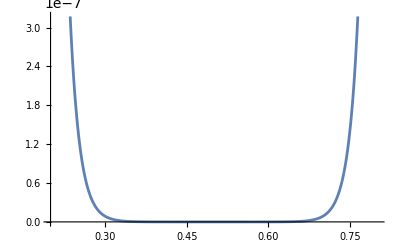

```mathematica
Plot[Abs[crossingEq[10]/.genBos/.Δσ->3/2],{z,0.2000000000,.800000000}]
```

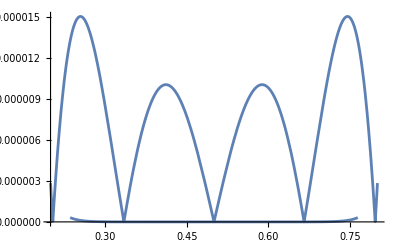

```mathematica
Show[%,%%]
```

```mathematica
N[zvals,20]
```

{{z→0.1},{z→0.2},{z→0.3},{z→0.4},{z→0.5},{z→0.6},{z→0.7},{z→0.8},{z→0.9}}

```mathematica
Abs[crossingEq[5]]/.%313/.genBos/.Δσ->3/2//N
```

{0.0686072,0.00364891,0.000187941,8.16356×10^-6,0.,8.16356×10^-6,0.000187941,0.00364891,0.0686072}

```mathematica
N[Abs[crossingEq[5]]/.zvals/.genBos/.Δσ->3/2,40]//N
```

```mathematica
subPr[x_,n_]:=Gamma[x+n]/Gamma[x]
```

```mathematica
subPr[2 Δσ,n]/subPr[2 Δσ+n-1/2,n]/2^(2n-1)/(2 n)!
```

(2^(1-2 n) Gamma[-1/2+n+2 Δσ] Gamma[n+2 Δσ])/((2 n)! Gamma[2 Δσ] Gamma[-1/2+2 n+2 Δσ])

```mathematica
2 subPr[2 Δσ,2n]^2/subPr[(4 Δσ+2 n -1),2n]/(2n)!/.Δσ->3/2/.n->1
```

18/7

```mathematica
genBos=Table[{C[n]->2 subPr[2 Δσ,2n]^2/subPr[(4 Δσ+2 n -1),2n]/(2n)!,Δ[n]->2 Δσ+2 n},{n,0,100}]//Flatten;
```

```mathematica
genFer=Table[{C[n]->2 subPr[2 Δσ,2n+1]^2/subPr[(4 Δσ+2 n ),2n+1]/(2n+1)!,Δ[n]->2 Δσ+2 n+1},{n,0,100}]//Flatten;
```

```mathematica
9
```

```mathematica
1+z^(2 Δσ)+z^(2 Δσ)/(1-z)^(2 Δσ)
```

1+z^(2 Δσ)+(1-z)^(-2 Δσ) z^(2 Δσ)

```mathematica
FullSimplify[(1+z^(2 Δσ)+z^(2 Δσ)/(1-z)^(2 Δσ)/.z->1-z)(z/(1-z))^(2 Δσ)-%89//Expand,1>z>0]
```

0

```mathematica
%89-(z/(1-z))^(2Δσ)(%89/.z->1-z)/.genBos/.Δσ->3/2/.zvals
```

{-2.22045×10^-16,0.,0.,0.,0.,-2.22045×10^-16,0.,-4.44089×10^-16,7.19425×10^-14}

```mathematica
%89/.z->1-z/.genBos/.Δσ->3/2/.zvals[[-1]]
```

1.00237

```mathematica
C[3]/.genBos/.Δσ->3/2/.zvals[[-1]]
```

28/143

```mathematica
Simplify[G[Δ[3],z]/.genBos/.Δσ->3/2]/.zvals[[-1]]
```

837.487

```mathematica
G[Δ[3],z]/.genBos/.Δσ->3/2/.zvals[[-1]]
```

837.487

```mathematica
G[Δ[4],z]/.genBos/.Δσ->3/2/.zvals[[-1]]
```

3622.03

```mathematica
C[i](G[Δ[i],z])/.i->3/.z->1-z/.genBos/.Δσ->3/2/.zvals[[-1]]
```

2.22644

```mathematica
(306 ((-1+z) (1+z) (761+z (28544+z (209305+z (423680+z (209305+z (28544+761 z))))))-140 (1+z (64+z (784+z (3136+z (4900+z (3136+z (784+z (64+z)))))))) Log[z]))/(-1+z)^8/.zvals[[-1]]
```

0.445289

```mathematica
C[i](G[Δ[i],z])/.i->4/.z->1-z/.genBos/.Δσ->3/2/.zvals[[-1]]//FullSimplify
```

5.6975×10^-13

```mathematica
%253/.zvals[[-1]]//FullSimplify
```

{0.00233825,0.0000333429,0.000124146,0.445289,5.6975×10^-13,8.73445×10^-16,1.18778×10^-18,1.47888×10^-21,1.72084×10^-24,1.8979×10^-27,2.00408×10^-30,2.04131×10^-33,2.01713×10^-36,1.94231×10^-39,1.82893×10^-42,1.68891×10^-45,1.53308×10^-48,1.37061×10^-51,1.20883×10^-54,1.05321×10^-57,9.07563×10^-61,7.74269×10^-64,6.54551×10^-67,5.48741×10^-70,4.56516×10^-73,3.77111×10^-76,3.09484×10^-79,2.52445×10^-82,2.04758×10^-85,1.65206×10^-88,1.32638×10^-91}

```mathematica
Table[C[i](G[Δ[i],z]),{i,0,30}]/.z->1-z/.genBos/.Δσ->3/2//FullSimplify
```

{-(60 (3-3 z^2+Log[z]+z (4+z) Log[z]))/(-1+z)^2,(270 (5 (-1+z) (1+z) (5+z (32+5 z))-6 (1+z (2+z) (8+z (14+z))) Log[z]))/(-1+z)^4,(1092 (7 (-1+z) (1+z) (7+z (132+z (382+z (132+7 z))))-10 (1+z (36+z (225+z (400+z (225+z (36+z)))))) Log[z]))/(-1+z)^6,(306 ((-1+z) (1+z) (761+z (28544+z (209305+z (423680+z (209305+z (28544+761 z))))))-140 (1+z (64+z (784+z (3136+z (4900+z (3136+z (784+z (64+z)))))))) Log[z]))/(-1+z)^8,-(135 (-1+z)^11 Hypergeometric2F1[11,11,22,1-z])/4199,-(33 (-1+z)^13 Hypergeometric2F1[13,13,26,1-z])/7429,-(182 (-1+z)^15 Hypergeometric2F1[15,15,30,1-z])/334305,-(24 (-1+z)^17 Hypergeometric2F1[17,17,34,1-z])/392863,-(51 (-1+z)^19 Hypergeometric2F1[19,19,38,1-z])/7960645,-(19 (-1+z)^21 Hypergeometric2F1[21,21,42,1-z])/29836911,-(231 (-1+z)^23 Hypergeometric2F1[23,23,46,1-z])/3811773485,-(46 (-1+z)^25 Hypergeometric2F1[25,25,50,1-z])/8268616329,-(325 (-1+z)^27 Hypergeometric2F1[27,27,54,1-z])/655976895434,-(81 (-1+z)^29 Hypergeometric2F1[29,29,58,1-z])/1883913941074,-(870 (-1+z)^31 Hypergeometric2F1[31,31,62,1-z])/238436656380769,-(496 (-1+z)^33 Hypergeometric2F1[33,33,66,1-z])/1633354849324947,-(1683 (-1+z)^35 Hypergeometric2F1[35,35,70,1-z])/67745336845810897,-(45 (-1+z)^37 Hypergeometric2F1[37,37,74,1-z])/22480824033572281,-(703 (-1+z)^39 Hypergeometric2F1[39,39,78,1-z])/4418346569675167535,-(234 (-1+z)^41 Hypergeometric2F1[41,41,82,1-z])/18729478873403515063,-(41 (-1+z)^43 Hypergeometric2F1[43,43,86,1-z])/42255876528035112510,-(473 (-1+z)^45 Hypergeometric2F1[45,45,90,1-z])/6340218691228224924870,-(69 (-1+z)^47 Hypergeometric2F1[47,47,94,1-z])/12139345432684963041731,-(188 (-1+z)^49 Hypergeometric2F1[49,49,98,1-z])/437759660807231218259973,-(1225 (-1+z)^51 Hypergeometric2F1[51,51,102,1-z])/38043493418387704877380278,-(663 (-1+z)^53 Hypergeometric2F1[53,53,106,1-z])/276566360609005795834652014,-(477 (-1+z)^55 Hypergeometric2F1[55,55,110,1-z])/2690236416833056377664342318,-(385 (-1+z)^57 Hypergeometric2F1[57,57,114,1-z])/29536452275193420248058872691,-(1653 (-1+z)^59 Hypergeometric2F1[59,59,118,1-z])/1734807671485371733891638646868,-(295 (-1+z)^61 Hypergeometric2F1[61,61,122,1-z])/4257663883322903340555840803868,-(3782 (-1+z)^63 Hypergeometric2F1[63,63,126,1-z])/754366804470175838303483079571041}

```mathematica
FullSimplify[Table[C[i](G[Δ[i],z]),{i,0,30}]/.z->1-z/.genBos/.Δσ->3/2]/.zvals[[-1]]
```

{0.00233825,0.0000333429,0.000124146,0.445289,5.6975×10^-13,8.73445×10^-16,1.18778×10^-18,1.47888×10^-21,1.72084×10^-24,1.8979×10^-27,2.00408×10^-30,2.04131×10^-33,2.01713×10^-36,1.94231×10^-39,1.82893×10^-42,1.68891×10^-45,1.53308×10^-48,1.37061×10^-51,1.20883×10^-54,1.05321×10^-57,9.07563×10^-61,7.74269×10^-64,6.54551×10^-67,5.48741×10^-70,4.56516×10^-73,3.77111×10^-76,3.09484×10^-79,2.52445×10^-82,2.04758×10^-85,1.65206×10^-88,1.32638×10^-91}

```mathematica
1+Sum[C[i](G[Δ[i],z]),{i,0,30}]/.z->1-z/.genBos/.Δσ->3/2/.zvals[[-1]]
```

3.22944

```mathematica
(z/(1-z))^(2Δσ)/.Δσ->3/2/.zvals
```

{0.00137174,0.015625,0.0787172,0.296296,1.,3.375,12.7037,64.,729.}

```mathematica
(z/(1-z))^(2Δσ)(1+Sum[C[i](G[Δ[i],1-z]),{i,0,20}])/.genBos/.Δσ->3/2/.zvals
```

{1.00237,1.02363,1.10572,1.3603,2.125,4.59097,14.043,66.1806,2354.26}

```mathematica
(z/(1-z))^(2Δσ)(%89/.z->1-z)/.genBos/.Δσ->3/2/.zvals
```

{1.00237,1.02363,1.10572,1.3603,2.125,4.591,14.0467,65.512,730.729}

```mathematica
1+Sum[C[i](G[Δ[i],z]),{i,0,20}]-(z/(1-z))^(2Δσ)(1+Sum[C[i](G[Δ[i],1-z]),{i,0,20}])/.genBos/.Δσ->3/2/.zvals
```

{-0.0000621842,0.0104365,-0.000019049,0.0000985842,-0.000013703,0.0000338267,0.00367293,-0.668556,-1623.53}

```mathematica
%89(1-z)^(2Δσ)/.z->1-z/.genBos/.Δσ->3/2/.zvals
```

{0.730729,0.524096,0.379261,0.293824,0.265625,0.293824,0.379261,0.524096,0.730729}

```mathematica
(1+Sum[C[i](G[Δ[i],z]),{i,0,30}])(1-z)^(2Δσ)/.genBos/.Δσ->3/2/.zvals
```

{0.730684,0.529439,0.379254,0.293845,0.265623,0.293824,0.379261,0.524096,0.730729}

```mathematica
%89-(1+Sum[C[i](G[Δ[i],z]),{i,0,30}])/.genBos/.Δσ->3/2/.zvals
```

{0.0000622192,-0.0104365,0.0000190484,-0.0000986106,0.0000135137,4.75563×10^-7,5.10601×10^-7,-1.55663×10^-6,4.83091×10^-7}

```mathematica
%89/.genBos/.Δσ->3/2/.zvals
```

```mathematica
%89/.genBos/.Δσ->3/2/.zvals
```

{1.00237,1.02363,1.10572,1.3603,2.125,4.591,14.0467,65.512,730.729}

```mathematica
1+Sum[C[i](G[Δ[i],z]),{i,0,20}]/.genBos/.Δσ->3/2/.zvals
```

{1.00231,1.03406,1.1057,1.36039,2.12499,4.591,14.0467,65.512,730.729}

```mathematica
1+Sum[C[i](G[Δ[i],z]),{i,0,10}]/.genBos/.Δσ->3/2/.zvals
```

{1.00231,1.03406,1.1057,1.36039,2.12499,4.591,14.0467,65.5117,729.817}

```mathematica
%89/.genBos/.Δσ->1/2/.z->.4
```

2.06667

```mathematica
1+Sum[C[i](G[Δ[i],z]),{i,0,1}]/.genBos/.Δσ->1/2/.z->.4
```

2.04366

```mathematica
1+Sum[C[i](G[Δ[i],z]),{i,0,3}]/.genBos/.Δσ->1/2/.z->.4
```

2.0437

```mathematica
Series[Hypergeometric2F1[Δ,Δ,2 Δ,z],{Δ,Infinity,1}]
```

Hypergeometric2F1[Δ,Δ,2 Δ,z]

```mathematica
%89
```

1+z^(2 Δσ)+(1-z)^(-2 Δσ) z^(2 Δσ)

```mathematica
Series[%89/.Δσ->3/2,{z,0,6}]
```

1+2 z^3+3 z^4+6 z^5+10 z^6+O[z]^7

```mathematica
Series[1+Sum[C[i](G[Δ[i],z]),{i,0,10}]/.genBos/.Δσ->3/2,{z,0,6}]
```

1+2 z^3+3 z^4+6 z^5+10 z^6+O[z]^7

```mathematica
Series[1+Sum[c[i](G[Δ[i],z]),{i,0,10}]/.genBos/.Δσ->3/2,{z,0,6}]
```

1+c[0] z^3+3/2 c[0] z^4+((12 c[0])/7+c[1]) z^5+((25 c[0])/14+(5 c[1])/2) z^6+O[z]^7

```mathematica
SolveAlways[%169==%157//Normal,{z}]
```

{{c[0]→2,c[1]→18/7}}

```mathematica
C[1]/.genBos/.Δσ->3/2
```

3/14

```mathematica
Δ[1]/.genBos/.Δσ->3/2
```

5

```mathematica
Series[ G[3,z],{z,0,3}]
```

z^3+O[z]^4

```mathematica
Series[C[i](G[Δ[i],z])/.i->0/.genBos/.Δσ->3/2,{z,0,6}]
```

2 z^3+3 z^4+(24 z^5)/7+(25 z^6)/7+O[z]^7